# MCSCF notebook

This notebook aims at studying the energy landscape of the MCSCF method in minimal examples. The data used in this notebook comes from the CalculationBench notebook.

## Initialization

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}"}];
```

```mathematica
SortEigensystem[eigsys_]:=Transpose[Sort[Transpose[eigsys]]]
```

```mathematica
Subscript[δ, l1_,l2_]:=KroneckerDelta[l1,l2];
```

```mathematica
TakeMOs[c_,n_]:=Take[cᵀ,n]ᵀ;
```

```mathematica
matrixProduct[listOfMatrices_]:=Dot@@listOfMatrices
```

```mathematica
ClearAll[plotColors];
plotColors::usage="plotColors[plotType,plotTheme] gives a list of the colors used in a plot when several curves are drawn. Here plotType is, for example, Plot or ListLogPlot while plotTheme may be \"Scientific\", \"Classic\" etc.";

plotColors[plotType_,plotTheme_]:=("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[plotTheme,plotType]))/. Directive[x_,__]:>x;
plotColors[Plot,"Scientific"]
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

## Modules

### AO quantities

```mathematica
CalcX[NB_,S_]:=Module[{s,X,WP,u,v,w,ϵ,Cp,Ortho,nLD,cutoff},
WP=15;	cutoff=10^-7;
Ortho="SVD";
Which[
Ortho=="Lowdin",X=MatrixPower[S,-1/2],
Ortho=="Canonical",X=Eigenvectors[S]ᵀ.DiagonalMatrix[Eigenvalues[S]^(-1/2)],
Ortho=="SVD",(
	s=Sort[Eigenvalues[S]];
	Print["Overlap eigenvalues in OBS = ",s];
	nLD=0;
	Do[If[s⟦i⟧<cutoff ,nLD++],{i,NB}];
	Print["Number of linear dependencies in OBS = ",nLD];
	{u,w,v}=SingularValueDecomposition[S,NB-nLD];	
	X=u.DiagonalMatrix[Diagonal[w]^(-1/2)].vᵀ;
)
];
Print["The orthogonality transformation is the "<>Ortho<>" one."];
Print[X];
Return[X];
]
```

```mathematica
AOStuff[nBas_,FileInt_,λ_]:=Module[{TabInt,nInt,S,X,T,V,U,AO},
(* Directory with the integrals filesTab *)
SetDirectory["~/QuAcK/int"];

(* Compute one-electron integrals *)
Print["Reading one-electron integrals..."];
TabInt=ReadList[StringJoin["Ov.",FileInt,".dat"],{Number,Number,Real}];	nInt=Length[TabInt];
S=Normal[SparseArray[
Join[
Table[{TabInt⟦k,1⟧,TabInt⟦k,2⟧}->TabInt⟦k,3⟧,{k,nInt}],
Table[{TabInt⟦k,2⟧,TabInt⟦k,1⟧}->TabInt⟦k,3⟧,{k,nInt}]
]
]];
X=CalcX[nBas,S];
TabInt=ReadList[StringJoin["Kin.",FileInt,".dat"],{Number,Number,Real}];	nInt=Length[TabInt];
T=SparseArray[
Join[
Table[{TabInt⟦k,1⟧,TabInt⟦k,2⟧}->TabInt⟦k,3⟧,{k,nInt}],
Table[{TabInt⟦k,2⟧,TabInt⟦k,1⟧}->TabInt⟦k,3⟧,{k,nInt}]
]
];
TabInt=ReadList[StringJoin["Nuc.",FileInt,".dat"],{Number,Number,Real}];	nInt=Length[TabInt];
V=SparseArray[
Join[
Table[{TabInt⟦k,1⟧,TabInt⟦k,2⟧}->TabInt⟦k,3⟧,{k,nInt}],Print["Number of linear dependencies in OBS = ",nLD];
Table[{TabInt⟦k,2⟧,TabInt⟦k,1⟧}->TabInt⟦k,3⟧,{k,nInt}]
]
];
Print["Done!"];

(* Read two-electron integrals *)
Print["Reading two-electron integrals..."];
TabInt=ReadList[StringJoin["ERI.",FileInt,".dat"],{Number,Number,Number,Number,Real}];	nInt=Length[TabInt];
U= λ SparseArray[
Join[
Table[{TabInt⟦k,1⟧,TabInt⟦k,2⟧,TabInt⟦k,3⟧,TabInt⟦k,4⟧}->TabInt⟦k,5⟧,{k,nInt}],
Table[{TabInt⟦k,3⟧,TabInt⟦k,2⟧,TabInt⟦k,1⟧,TabInt⟦k,4⟧}->TabInt⟦k,5⟧,{k,nInt}],
Table[{TabInt⟦k,1⟧,TabInt⟦k,4⟧,TabInt⟦k,3⟧,TabInt⟦k,2⟧}->TabInt⟦k,5⟧,{k,nInt}],
Table[{TabInt⟦k,3⟧,TabInt⟦k,4⟧,TabInt⟦k,1⟧,TabInt⟦k,2⟧}->TabInt⟦k,5⟧,{k,nInt}],
Table[{TabInt⟦k,4⟧,TabInt⟦k,1⟧,TabInt⟦k,2⟧,TabInt⟦k,3⟧}->TabInt⟦k,5⟧,{k,nInt}],
Table[{TabInt⟦k,2⟧,TabInt⟦k,3⟧,TabInt⟦k,4⟧,TabInt⟦k,1⟧}->TabInt⟦k,5⟧,{k,nInt}],
Table[{TabInt⟦k,2⟧,TabInt⟦k,1⟧,TabInt⟦k,4⟧,TabInt⟦k,3⟧}->TabInt⟦k,5⟧,{k,nInt}],
Table[{TabInt⟦k,4⟧,TabInt⟦k,3⟧,TabInt⟦k,2⟧,TabInt⟦k,1⟧}->TabInt⟦k,5⟧,{k,nInt}]
]
];
AO=<|"S"->S,"X"->X,"T"->T,"V"->V,"U"->U|>;
Return[AO];
]
```

### Density matrices

The following module can compute 1- and 2RDM for CI wave function expressed in terms of CI determinants. Maybe one day I’ll need to expand it to the case of CSF.

```mathematica
FormRDM[nDet_,Ψ_,K_,cDet_]:=
Module[{oneRDM,twoRDM,Ψiα,Ψiβ,Ψjα,Ψjβ,CompIα,CompIβ,CompJα,CompJβ,nSubα,nSubβ,k,l,Pk,Pl,m,n,Pm,Pn},
oneRDM=ConstantArray[0,{K,K}];
twoRDM=ConstantArray[0,{K,K,K,K}];

(* Construction of the one RDM *)
	Do[
		Ψiα=Ψ⟦I,1⟧;	Ψiβ=Ψ⟦I,2⟧;	Ψjα=Ψ⟦J,1⟧;	Ψjβ=Ψ⟦J,2⟧;
		CompIα=Complement[Ψiα,Ψjα];	CompJα=Complement[Ψjα,Ψiα];	nSubα=Length[CompIα];
		CompIβ=Complement[Ψiβ,Ψjβ];	CompJβ=Complement[Ψjβ,Ψiβ];	nSubβ=Length[CompIβ];
		Which[
			nSubα==0∧nSubβ==0,(Do[
								oneRDM⟦i,i⟧ = oneRDM⟦i,i⟧ + cDet⟦I⟧^2
								,{i,Ψiα}];
							  Do[
								oneRDM⟦i,i⟧ = oneRDM⟦i,i⟧ + cDet⟦I⟧^2
								,{i,Ψiβ}];
							),
			nSubα==1∧nSubβ==0,({k}=CompIα;	{{Pk}}=Position[Ψiα,k];
						 	{l}=CompJα;	{{Pl}}=Position[Ψjα,l];
						  	oneRDM⟦k,l⟧ = oneRDM⟦k,l⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
							),
			nSubα==0∧nSubβ==1,({k}=CompIβ;	{{Pk}}=Position[Ψiβ,k];
						 	{l}=CompJβ;	{{Pl}}=Position[Ψjβ,l];
						  	oneRDM⟦k,l⟧ = oneRDM⟦k,l⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
							)]
		,{I,nDet},{J,nDet}];
	;
	
(* Construction of the two RDM *)
		Do[
			Ψiα=Ψ⟦I,1⟧;	Ψiβ=Ψ⟦I,2⟧;	Ψjα=Ψ⟦J,1⟧;	Ψjβ=Ψ⟦J,2⟧;
			CompIα=Complement[Ψiα,Ψjα];	CompJα=Complement[Ψjα,Ψiα];	nSubα=Length[CompIα];
			CompIβ=Complement[Ψiβ,Ψjβ];	CompJβ=Complement[Ψjβ,Ψiβ];	nSubβ=Length[CompIβ];
			Which[
				nSubα==0∧nSubβ==0,((*Do[
								twoRDM⟦p,p,r,r⟧ = twoRDM⟦p,p,r,r⟧ + 4 cDet⟦I⟧^2;
								twoRDM⟦p,r,r,p⟧ = twoRDM⟦p,r,r,p⟧ - 2 cDet⟦I⟧^2
								,{p,Ψiα},{r,Ψiα}]*)
								Do[
								twoRDM⟦p,p,r,r⟧ = twoRDM⟦p,p,r,r⟧ + cDet⟦I⟧^2;
								twoRDM⟦p,r,r,p⟧ = twoRDM⟦p,r,r,p⟧ - cDet⟦I⟧^2
								,{p,Ψiα},{r,Ψiα}];
								Do[
								twoRDM⟦p,p,r,r⟧ = twoRDM⟦p,p,r,r⟧ + cDet⟦I⟧^2;
								twoRDM⟦p,r,r,p⟧ = twoRDM⟦p,r,r,p⟧ - cDet⟦I⟧^2;
								,{p,Ψiβ},{r,Ψiβ}];
								Do[
								twoRDM⟦p,p,r,r⟧ = twoRDM⟦p,p,r,r⟧ + cDet⟦I⟧^2
								,{p,Ψiα},{r,Ψiβ}];
								Do[
								twoRDM⟦p,p,r,r⟧ = twoRDM⟦p,p,r,r⟧ + cDet⟦I⟧^2
								,{p,Ψiβ},{r,Ψiα}];
				),
				nSubα==1∧nSubβ==0,({k}=CompIα;	{{Pk}}=Position[Ψiα,k];
						 		{l}=CompJα;	{{Pl}}=Position[Ψjα,l];
								Do[
								twoRDM⟦p,p,k,l⟧ = twoRDM⟦p,p,k,l⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦p,l,k,p⟧ = twoRDM⟦p,l,k,p⟧ - (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								,{p,Ψiα}];
								Do[
								twoRDM⟦k,l,r,r⟧ = twoRDM⟦k,l,r,r⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦k,r,r,l⟧ = twoRDM⟦k,r,r,l⟧ - (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								,{r,Ψiα}];
								Do[
								twoRDM⟦p,p,k,l⟧ = twoRDM⟦p,p,k,l⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								,{p,Ψiβ}];
								Do[
								twoRDM⟦k,l,r,r⟧ = twoRDM⟦k,l,r,r⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								,{r,Ψiβ}];
				),
				nSubα==0∧nSubβ==1,({k}=CompIβ;	{{Pk}}=Position[Ψiβ,k];
						 		{l}=CompJβ;	{{Pl}}=Position[Ψjβ,l];
						 		Do[
								twoRDM⟦p,p,k,l⟧ = twoRDM⟦p,p,k,l⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦p,l,k,p⟧ = twoRDM⟦p,l,k,p⟧ - (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								,{p,Ψiβ}];
								Do[
								twoRDM⟦k,l,r,r⟧ = twoRDM⟦k,l,r,r⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧ ;
								twoRDM⟦k,r,r,l⟧ = twoRDM⟦k,r,r,l⟧ - (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								,{r,Ψiβ}];
								Do[
								twoRDM⟦p,p,k,l⟧ = twoRDM⟦p,p,k,l⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								,{p,Ψiα}];
								Do[
								twoRDM⟦k,l,r,r⟧ = twoRDM⟦k,l,r,r⟧ + (-1)^(Pk+Pl)cDet⟦I⟧cDet⟦J⟧;
								,{r,Ψiα}];
				),
				nSubα==2∧nSubβ==0,({k,m}=CompIα;	{{Pk}}=Position[Ψiα,k];	{{Pm}}=Position[Ψiα,m];
								 {l,n}=CompJα;	{{Pl}}=Position[Ψjα,l];	{{Pn}}=Position[Ψjα,n];
								twoRDM⟦k,l,m,n⟧ = twoRDM⟦k,l,m,n⟧ + (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦m,n,k,l⟧ = twoRDM⟦m,n,k,l⟧ + (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦k,n,m,l⟧ = twoRDM⟦k,n,m,l⟧ - (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦m,l,k,n⟧ = twoRDM⟦m,l,k,n⟧ - (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
				),
				nSubα==0∧nSubβ==2,({k,m}=CompIβ;	{{Pk}}=Position[Ψiβ,k];	{{Pm}}=Position[Ψiβ,m];
								 {l,n}=CompJβ;	{{Pl}}=Position[Ψjβ,l];	{{Pn}}=Position[Ψjβ,n];
								 twoRDM⟦k,l,m,n⟧ = twoRDM⟦k,l,m,n⟧ + (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦m,n,k,l⟧ = twoRDM⟦m,n,k,l⟧ + (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦k,n,m,l⟧ = twoRDM⟦k,n,m,l⟧ - (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦m,l,k,n⟧ = twoRDM⟦m,l,k,n⟧ - (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
				),
				nSubα==1∧nSubβ==1,({k}=CompIα;	{m}=CompIβ;	{{Pk}}=Position[Ψiα,k];	{{Pm}}=Position[Ψiβ,m];
								 {l}=CompJα;	{n}=CompJβ;	{{Pl}}=Position[Ψjα,l];	{{Pn}}=Position[Ψjβ,n];
								 twoRDM⟦k,l,m,n⟧ = twoRDM⟦k,l,m,n⟧ + (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
								twoRDM⟦m,n,k,l⟧ = twoRDM⟦m,n,k,l⟧ + (-1)^(Pk+Pl+Pm+Pn)cDet⟦I⟧cDet⟦J⟧;
				)]
			,{I,nDet},{J,nDet}];
Return[{oneRDM,twoRDM}];		
]
```

Here we initialize some of the density matrices needed in this notebook.

```mathematica
C2Det={Cos[ϕ],Sin[ϕ]};
```

```mathematica
Ψ2Det={{{1},{1}},{{2},{2}}};
{γ2[ϕ_],Γ2[ϕ_]}=FormRDM[2,Ψ2Det,2,C2Det]//FullSimplify
```

{{{2 Cos[ϕ]^2,0},{0,2 Sin[ϕ]^2}},{{{{2 Cos[ϕ]^2,0},{0,0}},{{0,Sin[2 ϕ]},{0,0}}},{{{0,0},{Sin[2 ϕ],0}},{{0,0},{0,2 Sin[ϕ]^2}}}}}

```mathematica
{γ2[ϕ]//MatrixForm,Γ2[ϕ]//MatrixForm}
```

{(2 Cos[ϕ]^2 | 0
0 | 2 Sin[ϕ]^2),((2 Cos[ϕ]^2 | 0
0 | 0) | (0 | Sin[2 ϕ]
0 | 0)
(0 | 0
Sin[2 ϕ] | 0) | (0 | 0
0 | 2 Sin[ϕ]^2))}

For the oo-CIS wave function with 2 orbitals we derived the CSF RDM by hand.

```mathematica
{γ2CSF[ϕ_],Γ2CSF[ϕ_]}={2({{Cos[ϕ]^2+1/2 Sin[ϕ]^2, 1/(√2)Sin[ϕ]Cos[ϕ]}, {1/(√2)Sin[ϕ]Cos[ϕ], 1/2 Sin[ϕ]^2}}),2({{({{Cos[ϕ]^2, 1/(√2)Sin[ϕ]Cos[ϕ]}, {1/(√2)Sin[ϕ]Cos[ϕ], 1/2 Sin[ϕ]^2}}), ({{1/(√2)Sin[ϕ]Cos[ϕ], 0}, {1/2 Sin[ϕ]^2, 0}})}, {({{1/(√2)Sin[ϕ]Cos[ϕ], 1/2 Sin[ϕ]^2}, {0, 0}}), ({{1/2 Sin[ϕ]^2, 0}, {0, 0}})}})};
```

In fact, we could also use the above module to derive it. To do this we use the following definition of the coefficient

```mathematica
Ψ2DetCSF={{{1},{1}},{{1},{2}},{{2},{1}}};
c2DetCSF={Cos[ϕ],Sin[ϕ]/(√2),Sin[ϕ]/(√2)};
{γ2CSF[ϕ_],Γ2CSF[ϕ_]}=FormRDM[3,Ψ2CSF,2,cDetCSF]
```

{{{2 Cos[ϕ]^2+Sin[ϕ]^2,√2 Cos[ϕ] Sin[ϕ]},{√2 Cos[ϕ] Sin[ϕ],Sin[ϕ]^2}},{{{{2 Cos[ϕ]^2,√2 Cos[ϕ] Sin[ϕ]},{√2 Cos[ϕ] Sin[ϕ],Sin[ϕ]^2}},{{√2 Cos[ϕ] Sin[ϕ],0},{Sin[ϕ]^2,0}}},{{{√2 Cos[ϕ] Sin[ϕ],Sin[ϕ]^2},{0,0}},{{Sin[ϕ]^2,0},{0,0}}}}}

```mathematica
{γ2CSF[ϕ]//MatrixForm,Γ2CSF[ϕ]//MatrixForm}
```

{(2 Cos[ϕ]^2+Sin[ϕ]^2 | √2 Cos[ϕ] Sin[ϕ]
√2 Cos[ϕ] Sin[ϕ] | Sin[ϕ]^2),((2 Cos[ϕ]^2 | √2 Cos[ϕ] Sin[ϕ]
√2 Cos[ϕ] Sin[ϕ] | Sin[ϕ]^2) | (√2 Cos[ϕ] Sin[ϕ] | 0
Sin[ϕ]^2 | 0)
(√2 Cos[ϕ] Sin[ϕ] | Sin[ϕ]^2
0 | 0) | (Sin[ϕ]^2 | 0
0 | 0))}

```mathematica
Ψ2SACIS={{{1},{1}},{{1},{2}},{{2},{1}}};
c2DetSACIS={Cos[ϕ1]Cos[ϕ2],Sin[ϕ1]Cos[ϕ2],Sin[ϕ2]};
{γ2SACIS[ϕ1_,ϕ2_],Γ2SACIS[ϕ1_,ϕ2_]}=FormRDM[3,Ψ2SACIS,2,c2DetSACIS]
```

{{{2 Cos[ϕ1]^2 Cos[ϕ2]^2+Cos[ϕ2]^2 Sin[ϕ1]^2+Sin[ϕ2]^2,Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1]+Cos[ϕ1] Cos[ϕ2] Sin[ϕ2]},{Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1]+Cos[ϕ1] Cos[ϕ2] Sin[ϕ2],Cos[ϕ2]^2 Sin[ϕ1]^2+Sin[ϕ2]^2}},{{{{2 Cos[ϕ1]^2 Cos[ϕ2]^2,Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1]+Cos[ϕ1] Cos[ϕ2] Sin[ϕ2]},{Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1]+Cos[ϕ1] Cos[ϕ2] Sin[ϕ2],Cos[ϕ2]^2 Sin[ϕ1]^2+Sin[ϕ2]^2}},{{Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1]+Cos[ϕ1] Cos[ϕ2] Sin[ϕ2],0},{2 Cos[ϕ2] Sin[ϕ1] Sin[ϕ2],0}}},{{{Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1]+Cos[ϕ1] Cos[ϕ2] Sin[ϕ2],2 Cos[ϕ2] Sin[ϕ1] Sin[ϕ2]},{0,0}},{{Cos[ϕ2]^2 Sin[ϕ1]^2+Sin[ϕ2]^2,0},{0,0}}}}}

```mathematica
Ψ2OrbFCI={{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}};
C2OrbFCI={Cos[ϕ1]Cos[ϕ2]Cos[ϕ3],Sin[ϕ1]Cos[ϕ2]Cos[ϕ3],Sin[ϕ2]Cos[ϕ3],Sin[ϕ3]};
{γ2FCI[ϕ1_,ϕ2_,ϕ3_],Γ2FCI[ϕ1_,ϕ2_,ϕ3_]}=FormRDM[4,Ψ2OrbFCI,2,C2OrbFCI]//FullSimplify
```

{{{Cos[ϕ3]^2 (1/2 (3+Cos[2 ϕ1]) Cos[ϕ2]^2+Sin[ϕ2]^2),Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3])},{Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3]),Cos[ϕ3]^2 (Cos[ϕ2]^2 Sin[ϕ1]^2+Sin[ϕ2]^2)+2 Sin[ϕ3]^2}},{{{{2 Cos[ϕ1]^2 Cos[ϕ2]^2 Cos[ϕ3]^2,Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]^2 (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2])},{Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]^2 (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]),Cos[ϕ3]^2 (Cos[ϕ2]^2 Sin[ϕ1]^2+Sin[ϕ2]^2)}},{{Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]^2 (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]),Cos[ϕ1] Cos[ϕ2] Sin[2 ϕ3]},{Cos[ϕ3]^2 Sin[ϕ1] Sin[2 ϕ2],Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) Sin[ϕ3]}}},{{{Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]^2 (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]),Cos[ϕ3]^2 Sin[ϕ1] Sin[2 ϕ2]},{Cos[ϕ1] Cos[ϕ2] Sin[2 ϕ3],Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) Sin[ϕ3]}},{{Cos[ϕ3]^2 (Cos[ϕ2]^2 Sin[ϕ1]^2+Sin[ϕ2]^2),Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) Sin[ϕ3]},{Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) Sin[ϕ3],2 Sin[ϕ3]^2}}}}}

```mathematica
{γ2FCI[ϕ1,ϕ2,ϕ3]//MatrixForm,Γ2FCI[ϕ1,ϕ2,ϕ3]//MatrixForm}
```

{(2 Cos[ϕ2]^2 Cos[ϕ3]^2 | Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3])
Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3]) | 2 (Cos[ϕ3]^2 Sin[ϕ2]^2+Sin[ϕ3]^2)),((2 Cos[ϕ2]^2 Cos[ϕ3]^2 | 3 Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3])
-Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3]) | 0) | (2 Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3]) | Cos[ϕ1] Cos[ϕ2] Sin[2 ϕ3]
Cos[ϕ3]^2 Sin[ϕ1] Sin[2 ϕ2] | 0)
(0 | Cos[ϕ3]^2 Sin[ϕ1] Sin[2 ϕ2]
Cos[ϕ1] Cos[ϕ2] Sin[2 ϕ3] | 2 Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3])) | (0 | -Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3])
3 Cos[ϕ3] (Cos[ϕ2] Sin[ϕ1]+Sin[ϕ2]) (Cos[ϕ1] Cos[ϕ2] Cos[ϕ3]+Sin[ϕ3]) | 2 (Cos[ϕ3]^2 Sin[ϕ2]^2+Sin[ϕ3]^2)))}

```mathematica
Ψ2Det3Orb={{{1,2},{1,2}},{{1,3},{1,3}}};
{γ3[ϕ_],Γ3[ϕ_]}=FormRDM[2,Ψ2Det3Orb,3,C2Det]//FullSimplify
```

{{{2,0,0},{0,2 Cos[ϕ]^2,0},{0,0,2 Sin[ϕ]^2}},{{{{2,0,0},{0,4 Cos[ϕ]^2,0},{0,0,4 Sin[ϕ]^2}},{{0,0,0},{-2 Cos[ϕ]^2,0,0},{0,0,0}},{{0,0,0},{0,0,0},{-2 Sin[ϕ]^2,0,0}}},{{{0,-2 Cos[ϕ]^2,0},{0,0,0},{0,0,0}},{{4 Cos[ϕ]^2,0,0},{0,2 Cos[ϕ]^2,0},{0,0,0}},{{0,0,0},{0,0,Sin[2 ϕ]},{0,0,0}}},{{{0,0,-2 Sin[ϕ]^2},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,Sin[2 ϕ],0}},{{4 Sin[ϕ]^2,0,0},{0,0,0},{0,0,2 Sin[ϕ]^2}}}}}

```mathematica
Ψ3DetCSF3Orb={{{1,2},{1,2}},{{1,2},{1,3}},{{1,3},{1,2}},{{1,3},{1,3}}};
C3DetCSF3Orb={Cos[ϕ1]Cos[ϕ2],(Sin[ϕ1]Cos[ϕ2])/(√2),(Sin[ϕ1]Cos[ϕ2])/(√2),Sin[ϕ2]};
{γ3DetCSF3Orb[ϕ1_,ϕ2_],Γ3DetCSF3Orb[ϕ1_,ϕ2_]}=FormRDM[4,Ψ3DetCSF3Orb,3,C3DetCSF3Orb]//FullSimplify
```

{{{2,0,0},{0,1/2 (3+Cos[2 ϕ1]) Cos[ϕ2]^2,√2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2])},{0,√2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2]),Cos[ϕ2]^2 Sin[ϕ1]^2+2 Sin[ϕ2]^2}},{{{{2,0,0},{0,(3+Cos[2 ϕ1]) Cos[ϕ2]^2,2 √2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2])},{0,2 √2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2]),2 Cos[ϕ2]^2 Sin[ϕ1]^2+4 Sin[ϕ2]^2}},{{0,0,0},{-1/2 (3+Cos[2 ϕ1]) Cos[ϕ2]^2,0,0},{-√2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2]),0,0}},{{0,0,0},{-√2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2]),0,0},{-Cos[ϕ2]^2 Sin[ϕ1]^2-2 Sin[ϕ2]^2,0,0}}},{{{0,-1/2 (3+Cos[2 ϕ1]) Cos[ϕ2]^2,-√2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2])},{0,0,0},{0,0,0}},{{(3+Cos[2 ϕ1]) Cos[ϕ2]^2,0,0},{0,2 Cos[ϕ1]^2 Cos[ϕ2]^2,√2 Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1]},{0,√2 Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1],Cos[ϕ2]^2 Sin[ϕ1]^2}},{{2 √2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2]),0,0},{0,√2 Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1],Cos[ϕ1] Sin[2 ϕ2]},{0,Cos[ϕ2]^2 Sin[ϕ1]^2,√2 Cos[ϕ2] Sin[ϕ1] Sin[ϕ2]}}},{{{0,-√2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2]),-Cos[ϕ2]^2 Sin[ϕ1]^2-2 Sin[ϕ2]^2},{0,0,0},{0,0,0}},{{2 √2 Cos[ϕ2] Sin[ϕ1] (Cos[ϕ1] Cos[ϕ2]+Sin[ϕ2]),0,0},{0,√2 Cos[ϕ1] Cos[ϕ2]^2 Sin[ϕ1],Cos[ϕ2]^2 Sin[ϕ1]^2},{0,Cos[ϕ1] Sin[2 ϕ2],√2 Cos[ϕ2] Sin[ϕ1] Sin[ϕ2]}},{{2 Cos[ϕ2]^2 Sin[ϕ1]^2+4 Sin[ϕ2]^2,0,0},{0,Cos[ϕ2]^2 Sin[ϕ1]^2,√2 Cos[ϕ2] Sin[ϕ1] Sin[ϕ2]},{0,√2 Cos[ϕ2] Sin[ϕ1] Sin[ϕ2],2 Sin[ϕ2]^2}}}}}

```mathematica
Ψ4={{{1,2},{1,2}},{{1,3},{1,3}}};
{γ4[ϕ_],Γ4[ϕ_]}=FormRDM[2,Ψ4,4,C2Det]
```

{{{2 Cos[ϕ]^2+2 Sin[ϕ]^2,0,0,0},{0,2 Cos[ϕ]^2,0,0},{0,0,2 Sin[ϕ]^2,0},{0,0,0,0}},{{{{2 Cos[ϕ]^2+2 Sin[ϕ]^2,0,0,0},{0,4 Cos[ϕ]^2,0,0},{0,0,4 Sin[ϕ]^2,0},{0,0,0,0}},{{0,0,0,0},{-2 Cos[ϕ]^2,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{-2 Sin[ϕ]^2,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,-2 Cos[ϕ]^2,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{4 Cos[ϕ]^2,0,0,0},{0,2 Cos[ϕ]^2,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,2 Cos[ϕ] Sin[ϕ],0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,-2 Sin[ϕ]^2,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,2 Cos[ϕ] Sin[ϕ],0,0},{0,0,0,0}},{{4 Sin[ϕ]^2,0,0,0},{0,0,0,0},{0,0,2 Sin[ϕ]^2,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}}

```mathematica
Ψ4H2gu={{{1},{1}},{{2},{2}}};
{γ4gu[ϕ_],Γ4gu[ϕ_]}=FormRDM[2,Ψ4H2gu,4,C2Det]
Ψ4H2gg={{{1},{1}},{{3},{3}}};
{γ4gg[ϕ_],Γ4gg[ϕ_]}=FormRDM[2,Ψ4H2gg,4,C2Det]
```

{{{2 Cos[ϕ]^2,0,0,0},{0,2 Sin[ϕ]^2,0,0},{0,0,0,0},{0,0,0,0}},{{{{2 Cos[ϕ]^2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,2 Cos[ϕ] Sin[ϕ],0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{2 Cos[ϕ] Sin[ϕ],0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,2 Sin[ϕ]^2,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}}

{{{2 Cos[ϕ]^2,0,0,0},{0,0,0,0},{0,0,2 Sin[ϕ]^2,0},{0,0,0,0}},{{{{2 Cos[ϕ]^2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,2 Cos[ϕ] Sin[ϕ],0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{2 Cos[ϕ] Sin[ϕ],0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,2 Sin[ϕ]^2,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}}

### RHF DIIS (Titou)

```mathematica
DIIS[ℰ_,Δℰ_,l_]:=Module[{nDIIS,B,X,w,ϵ},
nDIIS=Min[l,Length[Δℰ]];
B=Table[
Which[
i≤nDIIS∧j≤nDIIS,Flatten[Δℰ⟦i⟧].Flatten[Δℰ⟦j⟧],
i≤nDIIS∧j==nDIIS+1,-1,
i==nDIIS+1∧j≤nDIIS,-1,
i==nDIIS+1∨j==nDIIS+1,0
]
,{i,1,nDIIS+1},{j,1,nDIIS+1}];
X=Table[If[k≤nDIIS,0,-1],{k,1,nDIIS+1}];
w=LinearSolve[Rationalize[B,10^-16],Rationalize[X,10^-16]];
ϵ=∑_(k=1)^nDIIS w⟦k⟧ℰ⟦k⟧;
Return[ϵ];
];
```

```mathematica
RHF[nEl_,nBas_,ENuc_,S_,T_,V_,U_,X_]:=Module[{maxSCF,thresh,F,H,UJ,UK,C,Cp,O,ϵ,P,nSCF,Conv,FDIIS,eDIIS,EHF,ET,EV,EJ,EK,Gap,TabRes,ResHF},
(* Convergence parameters *)
maxSCF=2560;	thresh=10^-10;

(* Generate initial guess *)
H=T+V;	UJ=Flatten[U,{{1},{3},{2,4}}];	UK=Flatten[U,{{1},{4},{2,3}}];
{ϵ,Cp}=Chop[SortEigensystem[Eigensystem[Xᵀ.H.X]]];	Cp=Cpᵀ;
C=X.Cp;	O=TakeMOs[C,nEl/2];
Print["The matrix X in the AO basis is: ",X//Chop//Normal//MatrixForm];
Print["The matrix H in the AO basis is: ",H//Chop//Normal//MatrixForm];
Print["The matrix U in the AO basis is: ",U//Chop//Normal//MatrixForm];
(* Main SCF loop *)
Conv=1;     nSCF=0;     FDIIS={};     eDIIS={};
While[Conv>thresh∧nSCF<maxSCF,
nSCF++;
P=2O.Oᵀ;     F=H+(UJ-1/2 UK).Flatten[P]; (* Compute the Fock Matrix *)
FDIIS=Prepend[FDIIS,F];     eDIIS=Prepend[eDIIS,F.P.S-S.P.F]; (* Update the DIIS list *)
F=DIIS[FDIIS,eDIIS,3]; (* Extrapolate the Fock matrix *)
Conv=Max[Abs[F.P.S-S.P.F]];
{ϵ,Cp}=Chop[SortEigensystem[Eigensystem[Xᵀ.F.X]]];	Cp=Cpᵀ;
C=X.Cp;	O=TakeMOs[C,nEl/2];  (* Update the occupied coefficient matrix *)
];

Print["SCF cycle converged with convergence ", Conv, " in ", nSCF, " iterations"];
Print["The MOs energies are: ",ϵ];
Print["The orthonormalized MOs coefficients are: ", MatrixForm@Cp];
Print["The MOs coefficients are: ", MatrixForm@C];
Print["The density matrix at convergence is: ",MatrixForm@P];

Gap=If[N>nEl/2,ϵ⟦nEl/2+1⟧-ϵ⟦nEl/2⟧,0];
ET= Tr[P.T];	EV= Tr[P.V];	EJ= Tr[P.UJ.Flatten[P]]/2;	EK= -Tr[P.UK.Flatten[P]]/4;
EHF=ET+EV+EJ+EK;

(* Put all the informations relative to this HF calculation in a table *)
TabRes=TableForm[{{nEl,nBas,NumberForm[ENuc+EHF,{9,6}],NumberForm[ENuc,{9,6}],NumberForm[EHF,{9,6}],NumberForm[ET,{9,6}],NumberForm[EV,{9,6}],NumberForm[EJ,{9,6}],NumberForm[EK,{9,6}],nSCF,NumberForm[Conv,{6,3}],NumberForm[Gap,{6,3}]}},
TableHeadings->{None,{"n","N_Basis","E_0","E_Nuc","E_HF","T_HF","V_HF","J_HF","K_HF","N_SCF","Conv","HL Gap"}},TableAlignments->Center];

(* Put all the useful quantities relative to this HF calculation in an Association *)
ResHF=<|"E_HF"->EHF,"F_HF"->F,"C_HF"->C,"ϵ_HF"->ϵ,"TabRes"->TabRes|>;
Return[ResHF];
];
```

### Orbital gradient and Hessian and RHF Newton-Raphson

```mathematica
HFGradient[K_,nEl_,nA_,F_]:=Module[{nO,nV,g},
nO=nEl/2;              nV=K-nO;

If[nA==0,
g=Flatten[Table[2 F⟦i,a⟧,{i,nO},{a,nO+1,K}]]
,
gIA=Flatten[Table[2 F⟦i,a⟧,{i,nO},{a,nO+1,nO+nA}]];
gIV=Flatten[Table[2 F⟦i,a⟧,{i,nO},{a,nO+nA+1,K}]];
gAV=Flatten[Table[2 F⟦i,a⟧,{i,nO+nA},{a,nO+nA+1,K}]];
g=Join[gIA,gIV,gAV];];

Return[g];
];
```

```mathematica
HFHessian[K_,nEl_,nA_,F_,U_]:=Module[{nO,nV,Hess},
	nO=nEl/2;              nV=K-nO;

	If[nA==0,
		Hess=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO},{j,nO},{a,nO+1,K},{b,nO+1,K}]
		,
		HIAIA=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO},{j,nO},{a,nO+1,nO+nA},{b,nO+1,nO+nA}];
		HIAIV=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO},{j,nO},{a,nO+1,nO+nA},{b,nO+nA+1,K}];
		HIAAV=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO},{j,nO+nA},{a,nO+1,nO+nA},{b,nO+nA+1,K}];
		HIVIA=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO},{j,nO},{a,nO+nA+1,K},{b,nO+1,nO+nA}];
		HIVIV=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO},{j,nO},{a,nO+nA+1,K},{b,nO+nA+1,K}];
		HIVAV=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO},{j,nO+nA},{a,nO+nA+1,K},{b,nO+nA+1,K}];
		HAVIA=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO+nA},{j,nO},{a,nO+nA+1,K},{b,nO+1,nO+nA}];
		HAVIV=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO+nA},{j,nO},{a,nO+nA+1,K},{b,nO+nA+1,K}];
		HAVAV=Table[2(F⟦a,b⟧KroneckerDelta[i,j] - F⟦i,j⟧KroneckerDelta[a,b] +2U⟦a,j,i,b⟧-U⟦a,j,b,i⟧ +2U⟦a,b,i,j⟧-U⟦a,b,j,i⟧),{i,nO+nA},{j,nO+nA},{a,nO+nA+1,K},{b,nO+nA+1,K}];
	
		HRow1=Join[HIAIA,HIAIV,HIAAV,2];
		HRow2=Join[HIVIA,HIVIV,HIVAV,2];
		HRow3=Join[HAVIA,HAVIV,HAVAV,2];
	
		Hess=Join[HRow1,HRow2,HRow3]];
	Hess=ArrayFlatten[Hess];	
	
	Return[Hess];
]
```

```mathematica
HFNewtonRaphson[K_,nEl_,nA_,S_,X_,H_,U_,initC_]:=Module[{maxSCF,thresh,nSCF,Conv,η,nO,nV,MO1,MO2,UJ,UK,ϵ,Cp,C,O,P,F,g,Hess,evHess,eVecHess,DampHess,EH,EJ,EK,EHF,ov,oo,vv,k},
(* Convergence parameters *)
maxSCF=32;	   thresh=10^-10;

η=0;

nO=nEl/2;                     nV=K-nO;

MO1=H; MO2=U;
UJ=Flatten[MO2,{{1},{3},{2,4}}];	UK=Flatten[MO2,{{1},{4},{2,3}}];

Which[MatrixQ[initC], 
	C=initC,
	initC=="Core",
	{ϵ,Cp}=Chop[SortEigensystem[Eigensystem[Xᵀ.MO1.X]]];	Cp=Cpᵀ;          C=X.Cp
];

O=TakeMOs[C,nO];

(* Main SCF loop *)
Conv=1;     nSCF=0;    
While[Conv>thresh∧nSCF<maxSCF,
nSCF++;
P=2O.Oᵀ;     F=H+(UJ-1/2 UK).Flatten[P]; (* Compute the Fock Matrix *)
{ϵ,Cp}=Chop[SortEigensystem[Eigensystem[Xᵀ.F.X]]];
(*Conv=Max[Abs[F.P.S-S.P.F]];*)
g=HFGradient[K,nEl,nA,Cᵀ.F.C];
Conv=Abs[Max[g]];
Print[Conv," and ",nSCF];
Hess=HFHessian[K,nEl,nA,Cᵀ.F.C,Cᵀ.Transpose[Cᵀ.U.C,{2,1,4,3}].C];

{evHess,eVecHess}=Eigensystem[Hess];
eVecHess=Transpose[eVecHess];
DampHess=eVecHess.(DiagonalMatrix[evHess]+η Sign[DiagonalMatrix[evHess]].IdentityMatrix[Length[Hess]]).Inverse[eVecHess];

ov=ArrayReshape[Inverse[DampHess].g,{nO,nV}];
oo=ConstantArray[0,{nO,nO}];
	vv=ConstantArray[0,{nV,nV}];
	k=Join[Join[oo,ov,2],Join[-ovᵀ,vv,2]];
	
C=C.MatrixExp[k];
O=TakeMOs[C,nO];
];

EH= Tr[P.MO1];	EJ= Tr[P.UJ.Flatten[P]]/2;	EK= -Tr[P.UK.Flatten[P]]/4;
EHF=EH+EJ+EK;


Return[EHF];
];
```

### CI Gradient and Hessian

```mathematica
CIGradient[nDet_,Ψ_,O1_,O2_,J_,K_]:=Module[{g,Ψiα,Ψjα,Ψiβ,Ψjβ,CompIα,CompJα,nSubα,CompIβ,CompJβ,nSubβ,a,b,c,d,Pa,Pb,Pc,Pd},
g= 2 Table[
Ψiα=Ψ⟦i,1⟧;	Ψiβ=Ψ⟦i,2⟧;	Ψjα=Ψ⟦1,1⟧;	Ψjβ=Ψ⟦1,2⟧;
CompIα=Complement[Ψiα,Ψjα];	CompJα=Complement[Ψjα,Ψiα];	nSubα=Length[CompIα];
CompIβ=Complement[Ψiβ,Ψjβ];	CompJβ=Complement[Ψjβ,Ψiβ];	nSubβ=Length[CompIβ];
Which[
	nSubα==0∧nSubβ==0,(
	Sum[O1⟦p,p⟧,{p,Ψiα}]+1/2 Sum[J⟦p,q⟧-K⟦p,q⟧,{p,Ψiα},{q,Ψiα}]+Sum[O1⟦p,p⟧,{p,Ψiβ}]+1/2 Sum[J⟦p,q⟧-K⟦p,q⟧,{p,Ψiβ},{q,Ψiβ}]+Sum[J⟦p,q⟧,{p,Ψiα},{q,Ψiβ}]
	),
	nSubα==1∧nSubβ==0,(
		{a}=CompIα;	{{Pa}}=Position[Ψiα,a];
		{c}=CompJα;	{{Pc}}=Position[Ψjα,c];
		(-1)^(Pa+Pc)(O1⟦a,c⟧+Sum[(O2⟦a,p,c,p⟧-O2⟦a,p,p,c⟧),{p,Ψiα}]+Sum[O2⟦a,p,c,p⟧,{p,Ψiβ}])
		),
	nSubα==0∧nSubβ==1,(
		{a}=CompIβ;	{{Pa}}=Position[Ψiβ,a];	
		{c}=CompJβ;	{{Pc}}=Position[Ψjβ,c];
		(-1)^(Pa+Pc)(O1⟦a,c⟧+Sum[(O2⟦a,p,c,p⟧-O2⟦a,p,p,c⟧),{p,Ψiβ}]+Sum[O2⟦a,p,c,p⟧,{p,Ψiα}])
	),
	nSubα==2∧nSubβ==0,(
		{a,b}=CompIα;	{{Pa}}=Position[Ψiα,a];	{{Pb}}=Position[Ψiα,b];
		{c,d}=CompJα;	{{Pc}}=Position[Ψjα,c];	{{Pd}}=Position[Ψjα,d];
		(-1)^(Pa+Pb+Pc+Pd)(O2⟦a,b,c,d⟧-O2⟦a,b,d,c⟧)
	),
	nSubα==0∧nSubβ==2,(
		{a,b}=CompIβ;	{{Pa}}=Position[Ψiβ,a];	{{Pb}}=Position[Ψiβ,b];
		{c,d}=CompJβ;	{{Pc}}=Position[Ψjβ,c];	{{Pd}}=Position[Ψjβ,d];
		(-1)^(Pa+Pb+Pc+Pd)(O2⟦a,b,c,d⟧-O2⟦a,b,d,c⟧)
	),
	nSubα==1∧nSubβ==1,(
		{a}=CompIα;	{b}=CompIβ;	{{Pa}}=Position[Ψiα,a];	{{Pb}}=Position[Ψiβ,b];
		{c}=CompJα;	{d}=CompJβ;	{{Pc}}=Position[Ψjα,c];	{{Pd}}=Position[Ψjβ,d];
		(-1)^(Pa+Pb+Pc+Pd)O2⟦a,b,c,d⟧
	)
	]

,{i,2,nDet}];

Return[g];
]
```

```mathematica
CIHessian[nDet_,Ψ_,O1_,O2_,J_,K_,E0_]:=Module[{H,Ψiα,Ψjα,Ψiβ,Ψjβ,CompIα,CompJα,nSubα,CompIβ,CompJβ,nSubβ,a,b,c,d,Pa,Pb,Pc,Pd,ijlist,Hlist},

H= Table[
Ψiα=Ψ⟦i,1⟧;	Ψiβ=Ψ⟦i,2⟧;	Ψjα=Ψ⟦j,1⟧;	Ψjβ=Ψ⟦j,2⟧;
CompIα=Complement[Ψiα,Ψjα];	CompJα=Complement[Ψjα,Ψiα];	nSubα=Length[CompIα];
CompIβ=Complement[Ψiβ,Ψjβ];	CompJβ=Complement[Ψjβ,Ψiβ];	nSubβ=Length[CompIβ];
Which[
	nSubα==0∧nSubβ==0,(
			Sum[O1⟦p,p⟧,{p,Ψiα}]+1/2 Sum[J⟦p,q⟧-K⟦p,q⟧,{p,Ψiα},{q,Ψiα}]+Sum[O1⟦p,p⟧,{p,Ψiβ}]+1/2 Sum[J⟦p,q⟧-K⟦p,q⟧,{p,Ψiβ},{q,Ψiβ}]+Sum[J⟦p,q⟧,{p,Ψiα},{q,Ψiβ}]
	),
	nSubα==1∧nSubβ==0,(
		{a}=CompIα;	{{Pa}}=Position[Ψiα,a];
		{c}=CompJα;	{{Pc}}=Position[Ψjα,c];
		(-1)^(Pa+Pc)(O1⟦a,c⟧+Sum[(O2⟦a,p,c,p⟧-O2⟦a,p,p,c⟧),{p,Ψiα}]+Sum[O2⟦a,p,c,p⟧,{p,Ψiβ}])
		),
	nSubα==0∧nSubβ==1,(
		{a}=CompIβ;	{{Pa}}=Position[Ψiβ,a];	
		{c}=CompJβ;	{{Pc}}=Position[Ψjβ,c];
		(-1)^(Pa+Pc)(O1⟦a,c⟧+Sum[(O2⟦a,p,c,p⟧-O2⟦a,p,p,c⟧),{p,Ψiβ}]+Sum[O2⟦a,p,c,p⟧,{p,Ψiα}])
	),
	nSubα==2∧nSubβ==0,(
		{a,b}=CompIα;	{{Pa}}=Position[Ψiα,a];	{{Pb}}=Position[Ψiα,b];
		{c,d}=CompJα;	{{Pc}}=Position[Ψjα,c];	{{Pd}}=Position[Ψjα,d];
		(-1)^(Pa+Pb+Pc+Pd)(O2⟦a,b,c,d⟧-O2⟦a,b,d,c⟧)
	),
	nSubα==0∧nSubβ==2,(
		{a,b}=CompIβ;	{{Pa}}=Position[Ψiβ,a];	{{Pb}}=Position[Ψiβ,b];
		{c,d}=CompJβ;	{{Pc}}=Position[Ψjβ,c];	{{Pd}}=Position[Ψjβ,d];
		(-1)^(Pa+Pb+Pc+Pd)(O2⟦a,b,c,d⟧-O2⟦a,b,d,c⟧)
	),
	nSubα==1∧nSubβ==1,(
		{a}=CompIα;	{b}=CompIβ;	{{Pa}}=Position[Ψiα,a];	{{Pb}}=Position[Ψiβ,b];
		{c}=CompJα;	{d}=CompJβ;	{{Pc}}=Position[Ψjα,c];	{{Pd}}=Position[Ψjβ,d];
		(-1)^(Pa+Pb+Pc+Pd)O2⟦a,b,c,d⟧
	)
	]

,{i,2,nDet},{j,2,nDet}];
H=2(H-E0);
Return[H];
]
```

### MCSCF TwoStep Second order

TODO: -add a HF orbital option for initcOrb
-add a integer option for initcCI which select a given FCI eigenvector
-notation for nBas and J and kk

```mathematica
MCSCFTwoStep[Ψ_,K_,nEl_,nA_,ENuc_,initcOrb_,X_,H_,U_,initcCI_]:=Module[{maxSO,nSO,thresh,ConvOrb,ConvCI,Conv,η
,nDet,nO,nV,Cp,cOrb,MO1,MO2,UJ,UK,J,kk,O,P,F
,gOrb,gCI,g,HessOrb,HessCI,HessOrbCI,Hess,evHess,eVecHess,DampHess
,sOI,ov,oo,vv,k,s,cCI
,γ,Γ,EMCSCF},

	maxSO=4;	   thresh=10^-10; (* Convergence parameters *)
	η=1;     (* Damp factor *)
	
	nDet=Length[Ψ];
	nO=nEl/2;                     nV=K-nO-nA;

	(* Initialisation *)
	Which[MatrixQ[initcOrb], 
		cOrb=initcOrb,
		initcOrb=="Core",
		{ϵ,Cp}=Chop[SortEigensystem[Eigensystem[Xᵀ.H.X]]];	Cp=Cpᵀ;          cOrb=X.Cp
	];
	O=TakeMOs[cOrb,nO];
	
	cCI=ConstantArray[0,nDet];
	cCI⟦1⟧=1;

	MO1=cOrbᵀ.H.cOrb; MO2=cOrbᵀ.Transpose[cOrbᵀ.U.cOrb,{2,1,4,3}].cOrb;
	UJ=Flatten[MO2,{{1},{3},{2,4}}];	UK=Flatten[MO2,{{1},{4},{2,3}}];
	J=Table[MO2⟦i,j,i,j⟧,{i,K},{j,K}];	kk=Table[MO2⟦i,j,j,i⟧,{i,K},{j,K}];
	
	{γ,Γ}=FormRDM[nDet,Ψ,K,cCI];
	EMCSCF = ENuc + (∑_(i=1)^K ∑_(j=1)^K ∑_(μ=1)^K ∑_(ν=1)^K cOrb⟦μ,i⟧MO1⟦μ,ν⟧cOrb⟦ν,j⟧γ⟦i,j⟧)+0.5(∑_(i=1)^K ∑_(j=1)^K ∑_(k=1)^K ∑_(l=1)^K ∑_(μ=1)^K ∑_(ν=1)^K ∑_(λ=1)^K ∑_(σ=1)^K cOrb⟦μ,i⟧cOrb⟦ν,j⟧MO2⟦μ,λ,ν,σ⟧cOrb⟦λ,k⟧cOrb⟦σ,l⟧Γ⟦i,j,k,l⟧);
	
	(* Iterative loop *)
	Conv=1;     nSO=0;    
	While[Conv>thresh∧nSO<maxSO,
		nSO++;

		(* Compute the new Fock Matrix *)
		P=2O.Oᵀ;     F=H+(UJ-1/2 UK).Flatten[P]; 
		(* Orbital step *)
		gOrb=HFGradient[K,nEl,nA,cOrbᵀ.F.cOrb];
		ConvOrb=Abs[Max[gOrb]];
		HessOrb=HFHessian[K,nEl,nA,cOrbᵀ.F.cOrb,MO2];
		
		ov=ArrayReshape[Inverse[HessOrb].gOrb,{nO,nV}];
		oo=ConstantArray[0,{nO,nO}];
		vv=ConstantArray[0,{nV,nV}];
		k=Join[Join[oo,ov,2],Join[-ovᵀ,vv,2]];
		
		cOrb=cOrb.MatrixExp[k];
		O=TakeMOs[cOrb,nO];
		
		(* Transform quantities into the new basis *)
		MO1=cOrbᵀ.H.cOrb; MO2=cOrbᵀ.Transpose[cOrbᵀ.U.cOrb,{2,1,4,3}].cOrb;
		UJ=Flatten[MO2,{{1},{3},{2,4}}];	UK=Flatten[MO2,{{1},{4},{2,3}}];
		J=Table[MO2⟦i,j,i,j⟧,{i,K},{j,K}];	kk=Table[MO2⟦i,j,j,i⟧,{i,K},{j,K}];
		
		(* CI step *)
		(*gCI=CIGradient[nDet,Ψ,MO1,MO2,J,kk]*);
		Ham=FormH[nDet,Ψ,MO1,MO2,J,kk];
		Print[Ham//MatrixForm];
		gCI={Ham⟦2;;,1⟧};
		Print[gCI];
		ConvCI=Abs[Max[gCI]];
		Conv=Max[ConvOrb,ConvCI];
		Print["The convergence is ",Conv," at iteration ",nSO];		
		(*HessCI=CIHessian[nDet,Ψ,MO1,MO2,J,kk,EMCSCF];*)
		HessCI=Ham⟦2;;,2;;⟧;
		Print[HessCI//MatrixForm];
		sOI=Inverse[HessCI].gCI;
		s=Join[Join[{{0}},Transpose[sOI],2],Join[-sOI,ConstantArray[0,{Length@sOI,Length@sOI}],2]];
		cCI=cCI.MatrixExp[-s];
		
		(* Rotate the CI coeff *)
		
		Print["The CI vector ",cCI//MatrixForm, ", we check the norm of this vector as a sanity check ",cCIᵀ.cCI];
		(* Compute the new density matrices *)
		{γ,Γ}=FormRDM[nDet,Ψ,K,cCI];
		
		(* Compute the new energy *)
		EMCSCF = ENuc + (∑_(i=1)^K ∑_(j=1)^K ∑_(μ=1)^K ∑_(ν=1)^K cOrb⟦μ,i⟧MO1⟦μ,ν⟧cOrb⟦ν,j⟧γ⟦i,j⟧)+0.5(∑_(i=1)^K ∑_(j=1)^K ∑_(k=1)^K ∑_(l=1)^K ∑_(μ=1)^K ∑_(ν=1)^K ∑_(λ=1)^K ∑_(σ=1)^K cOrb⟦μ,i⟧cOrb⟦ν,j⟧MO2⟦μ,λ,ν,σ⟧cOrb⟦λ,k⟧cOrb⟦σ,l⟧Γ⟦i,j,k,l⟧);
		Print["The energy a this step is ",EMCSCF]
];
]
```

### MCSCF OneStep Second order

TODO: -add a HF orbital option for initcOrb
-add a integer option for initcCI which select a given FCI eigenvector
-notation for nBas and J and kk

```mathematica
MCSCFSecondOrder[Ψ_,K_,nEl_,nA_,ENuc_,initcOrb_,X_,H_,U_,initcCI_]:=Module[{maxSO,nSO,thresh,ConvOrb,ConvCI,Conv,η
,nDet,nO,nV,Cp,cOrb,MO1,MO2,UJ,UK,J,kk,O,P,F
,gOrb,gCI,g,HessOrb,HessCI,HessOrbCI,Hess,evHess,eVecHess,DampHess
,λ,λorb,λCI,ov,oo,vv,k,s,cCI
,γ,Γ,EMCSCF},

	maxSO=4;	   thresh=10^-10; (* Convergence parameters *)
	η=1;     (* Damp factor *)
	
	nDet=Length[Ψ];
	nO=nEl/2;                     nV=K-nO-nA;

	(* Initialisation *)
	Which[MatrixQ[initcOrb], 
		cOrb=initcOrb,
		initcOrb=="Core",
		{ϵ,Cp}=Chop[SortEigensystem[Eigensystem[Xᵀ.H.X]]];	Cp=Cpᵀ;          cOrb=X.Cp
	];
	O=TakeMOs[cOrb,nO];
	
	cCI=ConstantArray[0,nDet];
	cCI⟦1⟧=1;

	MO1=cOrbᵀ.H.cOrb; MO2=cOrbᵀ.Transpose[cOrbᵀ.U.cOrb,{2,1,4,3}].cOrb;
	UJ=Flatten[MO2,{{1},{3},{2,4}}];	UK=Flatten[MO2,{{1},{4},{2,3}}];
	J=Table[MO2⟦i,j,i,j⟧,{i,K},{j,K}];	kk=Table[MO2⟦i,j,j,i⟧,{i,K},{j,K}];
	
	{γ,Γ}=FormRDM[nDet,Ψ,K,cCI];
	EMCSCF = ENuc + (∑_(i=1)^K ∑_(j=1)^K ∑_(μ=1)^K ∑_(ν=1)^K cOrb⟦μ,i⟧MO1⟦μ,ν⟧cOrb⟦ν,j⟧γ⟦i,j⟧)+0.5(∑_(i=1)^K ∑_(j=1)^K ∑_(k=1)^K ∑_(l=1)^K ∑_(μ=1)^K ∑_(ν=1)^K ∑_(λ=1)^K ∑_(σ=1)^K cOrb⟦μ,i⟧cOrb⟦ν,j⟧MO2⟦μ,λ,ν,σ⟧cOrb⟦λ,k⟧cOrb⟦σ,l⟧Γ⟦i,j,k,l⟧);
	
	(* Iterative loop *)
	Conv=1;     nSO=0;    
	While[Conv>thresh∧nSO<maxSO,
		nSO++;

		(* Compute the new Fock Matrix *)
		P=2O.Oᵀ;     F=H+(UJ-1/2 UK).Flatten[P]; 

		(* Build the gradient *)
		gOrb=HFGradient[K,nEl,nA,cOrbᵀ.F.cOrb];
		gCI=CIGradient[nDet,Ψ,MO1,MO2,J,kk];
		g=Join[gOrb,gCI];
		;
		(* Update the convergence parameter *)
		ConvOrb=Abs[Max[gOrb]];
		ConvCI=Abs[Max[gCI]];
		Conv=Max[ConvOrb,ConvCI];
		Print["The convergence is ",Conv," at iteration ",nSO];

		(* Build the Hessian *)
		HessOrb=HFHessian[K,nEl,nA,cOrbᵀ.F.cOrb,MO2];
		HessCI=CIHessian[nDet,Ψ,MO1,MO2,J,kk,EMCSCF];
		HessOrbCI=ConstantArray[0,{Length@HessOrb,Length@HessCI}];
		
		Hess=Join[Join[HessOrb,HessOrbCI,2],Join[Transpose[HessOrbCI],HessCI,2]];
		
		{evHess,eVecHess}=Eigensystem[Hess]; (* Compute the damped Hessian *)
		eVecHess=Transpose[eVecHess];
		DampHess=eVecHess.(DiagonalMatrix[evHess]+η Sign[DiagonalMatrix[evHess]].IdentityMatrix[Length[Hess]]).Inverse[eVecHess];

		(* Update the orbital and CI parameters *)
		λ=Inverse[DampHess].g;
		λorb=λ⟦;;Length@HessOrb⟧;
		λCI={λ⟦Length@HessOrb+1;;⟧};

		(* Rotate the orbitals *)
		ov=ArrayReshape[λorb,{nO,nV}];
		oo=ConstantArray[0,{nO,nO}];
		vv=ConstantArray[0,{nV,nV}];
		k=Join[Join[oo,ov,2],Join[-ovᵀ,vv,2]];
		
		cOrb=cOrb.MatrixExp[k];
		O=TakeMOs[cOrb,nO];
		
		(* Transform quantities into the new basis *)
		MO1=cOrbᵀ.H.cOrb; MO2=cOrbᵀ.Transpose[cOrbᵀ.U.cOrb,{2,1,4,3}].cOrb;
		UJ=Flatten[MO2,{{1},{3},{2,4}}];	UK=Flatten[MO2,{{1},{4},{2,3}}];
		J=Table[MO2⟦i,j,i,j⟧,{i,K},{j,K}];	kk=Table[MO2⟦i,j,j,i⟧,{i,K},{j,K}];
		
		(* Rotate the CI coeff *)
		s=Join[Join[{{0}},λCI,2],Join[-Transpose[λCI],ConstantArray[0,{Length@λCI,Length@λCI}],2]];
		cCI=cCI.MatrixExp[s];
		Print["The CI vector ",cCI//MatrixForm, ", we check the norm of this vector as a sanity check ",cCIᵀ.cCI];
		(* Compute the new density matrices *)
		{γ,Γ}=FormRDM[nDet,Ψ,K,cCI];
		
		(* Compute the new energy *)
		EMCSCF = ENuc + (∑_(i=1)^K ∑_(j=1)^K ∑_(μ=1)^K ∑_(ν=1)^K cOrb⟦μ,i⟧MO1⟦μ,ν⟧cOrb⟦ν,j⟧γ⟦i,j⟧)+0.5(∑_(i=1)^K ∑_(j=1)^K ∑_(k=1)^K ∑_(l=1)^K ∑_(μ=1)^K ∑_(ν=1)^K ∑_(λ=1)^K ∑_(σ=1)^K cOrb⟦μ,i⟧cOrb⟦ν,j⟧MO2⟦μ,λ,ν,σ⟧cOrb⟦λ,k⟧cOrb⟦σ,l⟧Γ⟦i,j,k,l⟧);
		Print["The energy a this step is ",EMCSCF]
];
]
```

### The MCSCF energy

Before implementing the energy, we start by a module which allows to chose between different parametrisation of the orbital coefficients. The three possible choices are:
- “Hyperspherical”: This parametrisation represent the coefficient matrix as an orthornomal matrix depending on N-1 angles. This parametrisation works only if there is 1 or N-1 occupied orbitals.
- “Exponential”: This parametrisation represent the coefficient matrix as an exponential of an anti-hermitian matrix acting on some initial coefficient matrix.
- “Givens”: This parametrisation represent the coefficient matrix as a series of OV single rotations acting on some initial coefficient matrix.

```mathematica
ExponentialParam[nO_,nA_,nV_,CAS_]:=Module[{oo,tmpaa,aa,vv,oa,ov,av,Row1,Row2,Row3,k},
oo=ConstantArray[0,{nO,nO}];
vv=ConstantArray[0,{nV,nV}];

If[nA==0,
aa={{}};
,If[CAS==True,
aa=ConstantArray[0,{nA,nA}],
tmpaa=Table[Symbol["θ"<>ToString@i<>ToString@j],{i,nO+1,nO+nA},{j,nO+1,nO+nA}];
tmpaa=UpperTriangularize[tmpaa,1];
aa=tmpaa-Transpose[tmpaa]
]];

oa=Table[Symbol["θ"<>ToString@i<>ToString@j],{i,nO},{j,nO+1,nO+nA}];
ov=Table[Symbol["θ"<>ToString@i<>ToString@j],{i,nO},{j,nO+nA+1,nO+nA+nV}];
av=Table[Symbol["θ"<>ToString@i<>ToString@j],{i,nO+1,nO+nA},{j,nO+nA+1,nO+nA+nV}];

Which[nA==0,
Row1=Join[oo,ov,2];
Row3=Join[-ovᵀ,vv,2];
k=Join[Row1,Row3],
nO==0&&nV==0,
k=aa,
nV==0,
Row1=Join[oo,oa,2];
Row2=Join[-oaᵀ,aa,2];
k=Join[Row1,Row2],
nO==0,
Row2=Join[aa,av,2];
Row3=Join[-avᵀ,vv,2];
k=Join[Row2,Row3],
nA>0&&nV>0;,
Row1=Join[oo,oa,ov,2];
Row2=Join[-oaᵀ,aa,av,2];
Row3=Join[-ovᵀ,-avᵀ,vv,2];
k=Join[Row1,Row2,Row3];
];

Return[k];
]
```

```mathematica
ExponentialParam[1,2,0,True]
```

{{0,θ12,θ13},{-θ12,0,0},{-θ13,0,0}}

```mathematica
GivensRotation[i_,a_,dim_]:= SparseArray[Join[
{{i, i}->Cos[Symbol["θ"<>ToString@i<>ToString@a]], {a, a}->Cos[Symbol["θ"<>ToString@i<>ToString@a]], 
{i, a}->Sin[Symbol["θ"<>ToString@i<>ToString@a]], {a, i}->-Sin[Symbol["θ"<>ToString@i<>ToString@a]]},Table[{j,j}->1,{j,dim}]],{dim,dim}];
```

```mathematica
GivensParam[nO_,nA_,nV_,CAS_]:=Module[{oaListRotations,ovListRotations,aaListRotations,avListRotations,ListRotations},
oaListRotations=Flatten[Table[Normal[GivensRotation[i,j,nO+nA+nV]],{i,nO},{j,nO+1,nO+nA}],1];
ovListRotations=Flatten[Table[Normal[GivensRotation[i,j,nO+nA+nV]],{i,nO},{j,nO+nA+1,nO+nA+nV}],1];
aaListRotations=Flatten[Table[Normal[GivensRotation[i,j,nO+nA+nV]],{i,nO+1,nO+nA},{j,i+1,nO+nA}],1];
avListRotations=Flatten[Table[Normal[GivensRotation[i,j,nO+nA+nV]],{i,nO+1,nO+nA},{j,nO+nA+1,nO+nA+nV}],1];

Which[nA==0,
ListRotations=ovListRotations,
nV==0,
ListRotations=oaListRotations,
nA>0&&nV>0;,
ListRotations=Join[ovListRotations,oaListRotations,avListRotations];
];
If[CAS==False&&nA>0,
ListRotations=Join[ListRotations,aaListRotations]];
Return[ListRotations];
]
```

```mathematica
GivensParam[1,2,0,False]
```

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{}

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}},{{1,0,0},{0,Cos[θ23],Sin[θ23]},{0,-Sin[θ23],Cos[θ23]}}}

```mathematica
CoeffMatrix[param_,K_,nO_,nA_,nV_,CAS_]:=Module[{ListCoeffMatrixHyper,cp,c,c0,k,listRotations},

Which[param=="Hyperspherical",
ListCoeffMatrixHyper=Table[CoordinateTransformData[{"Hyperspherical"-> "Cartesian",l},"OrthonormalBasisRotation", Join[{r},Table[Symbol["θ"<>ToString@1<>ToString@(j+1)],{j,l-1}]]],{l,2,5}];
cp[θ_]=ListCoeffMatrixHyper⟦K-1⟧;
c[θ_]=cp[θ];,

param=="Exponential",
k=ExponentialParam[nO,nA,nV,CAS];
c0=IdentityMatrix[K];
c[θ_]=c0.MatrixExp[k]
,

param=="Givens",
c0=IdentityMatrix[K];
listRotations=GivensParam[nO,nA,nV,CAS];
c[θ_]=c0.matrixProduct[listRotations];

];

Return[c[θ]]
]
```

```mathematica
MCSCF[R_,param_,K_,nO_,nA_,nV_,CAS_,data_,γ_,Γ_]:=Module[{r,Θ,cHF,c,EMCSCF,MO1,MO2},

posR=Position[data⟦;;,1⟧,R]⟦1,1⟧;
cHF=data⟦posR,6⟧;
MO1=cHFᵀ.data⟦posR,4⟧.cHF;
MO2= cHFᵀ.Transpose[cHFᵀ.data⟦posR,5⟧.cHF,{2,1,4,3}].cHF;

Θ=Table[Symbol["θ"<>ToString@i],{i,K-1}];
c[θ_]=CoeffMatrix[param,K,nO,nA,nV,CAS];
EMCSCF[θ_,ϕ_]=data⟦posR,7⟧+(∑_(i=1)^K ∑_(j=1)^K ∑_(μ=1)^K ∑_(ν=1)^K c[θ]⟦μ,i⟧MO1⟦μ,ν⟧c[θ]⟦ν,j⟧γ[ϕ]⟦i,j⟧)+0.5(∑_(i=1)^K ∑_(j=1)^K ∑_(k=1)^K ∑_(l=1)^K ∑_(μ=1)^K ∑_(ν=1)^K ∑_(λ=1)^K ∑_(σ=1)^K c[θ]⟦μ,i⟧c[θ]⟦ν,j⟧MO2⟦μ,λ,ν,σ⟧c[θ]⟦λ,k⟧c[θ]⟦σ,l⟧Γ[ϕ]⟦i,j,k,l⟧);
Return[EMCSCF[Θ,ϕ]];
]
```

```mathematica
MCSCF2[R_,param_,K_,nO_,nA_,nV_,CAS_,data_,γ_,Γ_]:=Module[{r,Θ,cHF,c,EMCSCF,MO1,MO2},

posR=Position[data⟦;;,1⟧,R]⟦1,1⟧;
cHF=data⟦posR,6⟧;
MO1=cHFᵀ.data⟦posR,4⟧.cHF;
MO2= cHFᵀ.Transpose[cHFᵀ.data⟦posR,5⟧.cHF,{2,1,4,3}].cHF;

Θ=Table[Symbol["θ"<>ToString@i],{i,K-1}];
c[θ_]=CoeffMatrix[param,K,nO,nA,nV,CAS];

EMCSCF[θ_,ϕ1_,ϕ2_]=data⟦posR,7⟧+(∑_(i=1)^K ∑_(j=1)^K ∑_(μ=1)^K ∑_(ν=1)^K c[θ]⟦μ,i⟧MO1⟦μ,ν⟧c[θ]⟦ν,j⟧γ[ϕ1,ϕ2]⟦i,j⟧)+0.5(∑_(i=1)^K ∑_(j=1)^K ∑_(k=1)^K ∑_(l=1)^K ∑_(μ=1)^K ∑_(ν=1)^K ∑_(λ=1)^K ∑_(σ=1)^K c[θ]⟦μ,i⟧c[θ]⟦ν,j⟧MO2⟦μ,λ,ν,σ⟧c[θ]⟦λ,k⟧c[θ]⟦σ,l⟧Γ[ϕ1,ϕ2]⟦i,j,k,l⟧);
Return[EMCSCF[Θ,ϕ1,ϕ2]];
]
```

```mathematica
(MCSCF[1.,"Hyperspherical",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
(MCSCF[1.,"Exponential",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
(MCSCF[1.,"Givens",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

0.12369-1.11077 Cos[2 θ12]-0.0789245 Cos[4 θ12]

0.12369-1.11077 Cos[2 θ12]-0.0789245 Cos[4 θ12]

0.12369-1.11077 Cos[2 θ12]-0.0789245 Cos[4 θ12]

```mathematica
Timing[Minimize[(MCSCF[1.,"Hyperspherical",2,1,DataH2,γ2,Γ2])/.ϕ->0//FullSimplify//Chop,{θ12,θ13}]]
Timing[Minimize[(MCSCF[1.,"Exponential",2,1,DataH2,γ2,Γ2])/.ϕ->0//FullSimplify//Chop,{θ12,θ13}]]
Timing[Minimize[(MCSCF[1.,"Givens",2,1,DataH2,γ2,Γ2])/.ϕ->0//FullSimplify//Chop,{θ12,θ13}]]
```

{0.192912,{-1.066,{θ12→-6.97743×10^-20,θ13→-0.158662}}}

{0.117577,{-1.066,{θ12→-6.97743×10^-20,θ13→-0.158662}}}

{0.132141,{-1.066,{θ12→-6.97743×10^-20,θ13→-0.158662}}}

```mathematica
Timing[Minimize[(MCSCF[1.,"Hyperspherical",3,2,DataH3Di,γ3,Γ3])/.ϕ->0//FullSimplify//Chop,{θ12,θ13}]]
Timing[Minimize[(MCSCF[1.,"Exponential",3,2,DataH3Di,γ3,Γ3])/.ϕ->0//FullSimplify//Chop,{θ13,θ23}]]
Timing[Minimize[(MCSCF[1.,"Givens",3,2,DataH3Di,γ3,Γ3])/.ϕ->0//FullSimplify//Chop,{θ13,θ23}]]
```

{0.341747,Minimize[ComplexInfinity,{θ12,θ13}]}

{0.240547,Minimize[ComplexInfinity,{θ13,θ23}]}

{0.202937,Minimize[ComplexInfinity,{θ13,θ23}]}

### Stationary points

```mathematica
StationaryPoint[f_]:=Module[{x,y},
Dx[x_,y_]=D[f[x,y],x];
Dy[x_,y_]=D[f[x,y],y];
stationary=DeleteDuplicates@SetPrecision[Chop@Flatten[{f[x,y],{x,y}}/.Table[FindRoot[{Dx[x,y],Dy[x,y]},{x,i},{y,j},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->20,MaxIterations->1000],{i,-π/2,π/2,0.1},{j,-π/2,π/2,0.1}],1],8];
stationary=Select[stationary,-π<#⟦2,1⟧<π&];
stationary=Select[stationary,-π<#⟦2,2⟧<π&];
stationaryNRJ=DeleteDuplicates@SetPrecision[stationary⟦;;,1⟧,6];
Return[{stationaryNRJ//Sort,stationary}];
]
```

```mathematica
StationaryPointOnePoint[f_,{x0_,y0_}]:=Module[{x,y,z},
Dx[x_,y_]=D[f[x,y],x];
Dy[x_,y_]=D[f[x,y],y];
stationary={f[x,y],{x,y}}/.FindRoot[{Dx[x,y],Dy[x,y]},{x,x0,-π,π},{y,y0,-π,π},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->20,MaxIterations->1000];
Print[stationary];
Return[stationary];
]
```

```mathematica
StationaryPoint[EMCSCFH2R1]
```

{{-2.07897,0.16850088,-0.80977786,-0.78499313},{{-2.07897,{-1.5707963,-1.4947555}},{-2.07897,{-1.5707963,1.6468371}},{0.16850088,{-1.5707963,0.076040787}},{0.16850088,{-1.5707963,-3.0655519}},{0.16850088,{0,1.4947555}},{-2.07897,{0,-0.076040787}},{-0.80977786,{-2.3561945,-0.78539816}},{-0.80977786,{-2.3561945,2.3561945}},{-0.78499313,{-0.78539816,0.78539816}},{-0.80977786,{-0.78539816,-0.78539816}},{-0.78499313,{-2.3561945,-2.3561945}},{-2.07897,{1.5707963,-1.4947555}},{0.16850088,{0,-1.6468371}},{-0.78499313,{-2.3561945,0.78539816}},{-0.78499313,{0.78539816,-2.3561945}},{0.16850088,{1.5707963,-3.0655519}},{-0.80977786,{0.78539816,-0.78539816}},{-0.78499313,{2.3561945,0.78539816}},{0.16850088,{1.5707963,0.076040787}},{-0.80977786,{2.3561945,-0.78539816}},{-2.07897,{0,3.0655519}},{-0.80977786,{0.78539816,2.3561945}},{-0.78499313,{0.78539816,0.78539816}},{-0.80977786,{2.3561945,2.3561945}},{-2.07897,{1.5707963,1.6468371}},{-0.78499313,{-0.78539816,-2.3561945}},{-0.80977786,{-0.78539816,2.3561945}},{-0.78499313,{2.3561945,-2.3561945}}}}

```mathematica
StationaryPoint3Var[f_]:=Module[{x,y,z},
Dx[x_,y_,z_]=D[f[x,y,z],x];
Dy[x_,y_,z_]=D[f[x,y,z],y];
Dz[x_,y_,z_]=D[f[x,y,z],z];
stationary=DeleteDuplicates@SetPrecision[Chop@Flatten[{f[x,y,z],{x,y,z}}/.Table[FindRoot[{Dx[x,y,z],Dy[x,y,z],Dz[x,y,z]},{x,i,-π,π},{y,j,-π,π},{z,k,-π,π},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->20,MaxIterations->5000],{i,-π/2,π/2,0.5},{j,-π/2,π/2,0.5},{k,-π/2,π/2,0.5}],2],8];
stationary=Select[stationary,-π<#⟦2,1⟧<π&];
stationary=Select[stationary,-π<#⟦2,2⟧<π&];
stationary=Select[stationary,-π<#⟦2,3⟧<π&];
Print[Select[stationary,SetPrecision[#⟦2,2⟧,6]==SetPrecision[π/4,6]&]];
Print[Select[stationary,SetPrecision[#⟦2,2⟧,6]==SetPrecision[-3π/4,6]&]];
	stationaryNRJ=DeleteDuplicates@SetPrecision[stationary⟦;;,1⟧,6];
Return[{stationaryNRJ//Sort,stationary}];
]
```

```mathematica
StationaryPoint3VarOnePoint[f_,{x0_,y0_,z0_}]:=Module[{x,y,z},
Dx[x_,y_,z_]=D[f[x,y,z],x];
Dy[x_,y_,z_]=D[f[x,y,z],y];
Dz[x_,y_,z_]=D[f[x,y,z],z];
stationary={f[x,y,z],{x,y,z}}/.FindRoot[{Dx[x,y,z],Dy[x,y,z],Dz[x,y,z]},{x,x0,-π,π},{y,y0,-π,π},{z,z0,-π,π},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->20,MaxIterations->1000];
Return[stationary];
]
```

```mathematica
StationaryPoint4Var[f_,Ll_,Lr_,dL_,MaxIt_]:=Module[{w,x,y,z},
Dw[w_,x_,y_,z_]=D[f[w,x,y,z],w];
Dx[w_,x_,y_,z_]=D[f[w,x,y,z],x];
Dy[w_,x_,y_,z_]=D[f[w,x,y,z],y];
Dz[w_,x_,y_,z_]=D[f[w,x,y,z],z];
stationary=DeleteDuplicates@SetPrecision[Chop@Flatten[{f[w,x,y,z],{w,x,y,z}}/.Table[FindRoot[{Dw[w,x,y,z],Dx[w,x,y,z],Dy[w,x,y,z],Dz[w,x,y,z]},{w,l},{x,i},{y,j},{z,k},MaxIterations->MaxIt],{l,Ll,Lr,dL},{i,Ll,Lr,dL},{j,Ll,Lr,dL},{k,Ll,Lr,dL}],3],8];
stationary=Select[stationary,-π<Chop[#⟦2,1⟧]<π&];
stationary=Select[stationary,-π<Chop[#⟦2,2⟧]<π&];
stationary=Select[stationary,-π<Chop[#⟦2,3⟧]<π&];
stationary=Select[stationary,-π<Chop[#⟦2,4⟧]<π&];
stationaryNRJ=DeleteDuplicates@SetPrecision[stationary⟦;;,1⟧,6];
Print[stationaryNRJ//Sort];
Return[{stationaryNRJ//Sort,stationary}];
]
```

```mathematica
StationaryPoint4VarOnePoint[f_,{w0_,x0_,y0_,z0_}]:=Module[{w,x,y,z},
Dw[w_,x_,y_,z_]=D[f[w,x,y,z],w];
Dx[w_,x_,y_,z_]=D[f[w,x,y,z],x];
Dy[w_,x_,y_,z_]=D[f[w,x,y,z],y];
Dz[w_,x_,y_,z_]=D[f[w,x,y,z],z];
stationary={f[w,x,y,z],{w,x,y,z}}/.FindRoot[{Dw[w,x,y,z],Dx[w,x,y,z],Dy[w,x,y,z],Dz[w,x,y,z]},{w,w0,-3π,3π},{x,x0,-3π,3π},{y,y0,-3π,3π},{z,z0,-3π,3π},AccuracyGoal->8,PrecisionGoal->8,WorkingPrecision->20,MaxIterations->5000];
Return[stationary];
]
```

### Population analysis

```mathematica
PopAna[R_,param_,K_,nO_,nA_,nV_,CAS_,data_,γ_,Γ_]:=Module[{posR,Θ,cMO,cAO,γAO,Pop},
posR=Position[data⟦;;,1⟧,R]⟦1,1⟧;

Θ=Table[Symbol["θ"<>ToString@i],{i,K-1}];
cMO[θ_]=CoeffMatrix[param,K,nO,nA,nV,CAS];
cAO[θ_]=data⟦posR,6⟧.cMO[θ];

Pop[θ_,ϕ_]=cAO[θ].γ[ϕ].(cAO[θ]ᵀ).data⟦posR,2⟧;

Return[Pop[Θ,ϕ]];
]
```

```mathematica
PopAna2[R_,param_,K_,nO_,nA_,nV_,CAS_,data_,γ_,Γ_]:=Module[{posR,Θ,cMO,cAO,γAO,Pop},
posR=Position[data⟦;;,1⟧,R]⟦1,1⟧;

Θ=Table[Symbol["θ"<>ToString@i],{i,K-1}];
cMO[θ_]=CoeffMatrix[param,K,nO,nA,nV,CAS];
cAO[θ_]=data⟦posR,6⟧.cMO[θ];

Pop[θ_,ϕ1_,ϕ2_]=cAO[θ].γ[ϕ1,ϕ2].(cAO[θ]ᵀ).data⟦posR,2⟧;

Return[Pop[Θ,ϕ1,ϕ2]];
]
```

## Main

```mathematica
Main[nEl_,nBas_,nCore_,XYZ_,ZNuc_,FileInt_,nState_,λ_,ToDoList_]:=Module[
{ListModules,ToDoModules,UpdateToDo,
 AngToBohr,
 nα,nβ,nO,nV,nAt,ENuc,AO,
 Ψα,nDetα,Ψβ,nDetβ,ΨFCI,nDetFCI,listDet,
 TimeRHF,ResHF,ResStabAn,MO1,MO2,J,K
},


(* Initialisation *)
(* ListModules is the list of all the modules/methods in this notebook *) 
ListModules={"RHF","StabAn","DOCI","FCI","CCD","pCCD","VCCD"};

(* Each method is associated with a dictionnary ResModule containing all the relevant quantity computable by this module *)

(* ToDoModules is a dictionnary with a key for each method. At each key is attributed a dictionnary with the following informations *)
(* Should we execute this module ("Do"), the dependencies of this module ("Dependencies"), the subroutine to execute in this module ("SubDo"), the subdependencies *)
ToDoModules=Association[
	"RHF"-><|"Do"->False, "Dependencies"->{}, "SubDo"->{}|>,
	"NR-RHF"-><|"Do"->False, "Dependencies"->{}, "SubDo"->{}|>,
	"StabAn"-><|"Do"->False, "Dependencies"->{"RHF"}, "SubDo"->{}|>,
	"FCI"-><|"Do"->False, "Dependencies"->{"RHF"}, "SubDo"->{}|>,
	"NR-MCSCF"-><|"Do"->False, "Dependencies"->{"RHF"}, "SubDo"->{}|>
	];

(* Recursive function to update the "Do" keys *)
UpdateToDo[Method_]:=Module[{ToDoMethod,ListDependencies},
ToDoMethod=ToDoModules[Method];
ListDependencies=ToDoMethod["Dependencies"];
If[ToDoMethod["Do"]==False,
	If[Length[ListDependencies]>0,
		Do[UpdateToDo[ListDependencies⟦i⟧];
			,{i,Length[ToDoMethod["Dependencies"]]}]];
	ToDoModules[Method]["Do"]=True;
	]
];

(* Reading ToDoList and updating ToDoModules *)
Do[UpdateToDo[ToDoList⟦i⟧]
	,{i,Length[ToDoList]}];

(* Conversion Angstrom to Bohr *)
AngToBohr=1.8897259886;

(* Information *) 
Print[Style["Start of calculation",Red,Bold]];

nα=nEl/2;	nβ=nEl/2;	nO=nEl/2;	nV=nBas-nO;

(* Input *)
nAt=Length[XYZ];
ENuc=∑_(c=1)^nAt ∑_(d=c+1)^nAt (ZNuc⟦c⟧ZNuc⟦d⟧)/((*AngToBohr*) Norm[XYZ⟦c⟧-XYZ⟦d⟧]);

(* Compute AO related quantities: S, X, T, V, U *)
AO=AOStuff[nBas,FileInt,λ];

(* Form the different list of determinants *)
Ψα=Subsets[Table[m,{m,(nCore/2)+1,nBas}],{nα-(nCore/2)}];
If[nCore≠0,Ψα=Map[Join[Table[m,{m,(nCore/2)}],#]&,Ψα]];
Ψβ=Subsets[Table[m,{m,(nCore/2)+1,nBas}],{nβ-(nCore/2)}];
If[nCore≠0,Ψβ=Map[Join[Table[m,{m,(nCore/2)}],#]&,Ψβ]];
nDetα=Length[Ψα];    nDetβ=Length[Ψβ];

ΨFCI=Flatten[Table[{Ψα⟦p⟧,Ψβ⟦q⟧},{p,nDetα},{q,nDetβ}],1];   nDetFCI=Length[ΨFCI];

listDet=Subsets[Table[k,{k,nCore+1,2nBas}],{nEl-nCore}];
If[nCore≠0,listDet=Map[Join[Table[m,{m,nCore}],# ] &, listDet]];
listDet=Select[listDet,Length[Select[#,EvenQ]]==Length[Select[#,OddQ]]&];

(* Hartree-Fock *)
(* HF *)
If[ToDoModules["RHF"]["Do"]==True,
	Print[Style["RHF calculation...",Bold,Orange]];
	{TimeRHF,ResHF}=Timing[RHF[nEl,nBas,ENuc,AO["S"],AO["T"],AO["V"],AO["U"],AO["X"]]];
	Print[ResHF["TabRes"]];
	Print["CPU time = ",TimeRHF];
	Print[Style["Done!",Bold,Darker[Green]]];

	(* AO to RHF MO *)
	Print[Style["AO to RHF MO transformation...",Bold,Orange]];
	MO1=ResHF["C_HF"]ᵀ.(AO["T"]+AO["V"]).ResHF["C_HF"];	MO2= ResHF["C_HF"]ᵀ.Transpose[ResHF["C_HF"]ᵀ.AO["U"].ResHF["C_HF"],{2,1,4,3}].ResHF["C_HF"];
	ResHF=Append[ResHF,"MO1_HF"->MO1];        ResHF=Append[ResHF,"MO2_HF"->MO2];
	J=Table[MO2⟦i,j,i,j⟧,{i,nBas},{j,nBas}];	K=Table[MO2⟦i,j,j,i⟧,{i,nBas},{j,nBas}];
	ResHF=Append[ResHF,"J_HF"->J];        ResHF=Append[ResHF,"K_HF"->K];
	Print[Style["Done!",Bold,Darker[Green]]];
	
	Print["The matrix H in the MO basis is: ",MO1//Chop//Normal//MatrixForm];
	Print["The matrix U in the MO basis is: ",MO2//Chop//Normal//MatrixForm];
	
	(* HF Stability Analysis *)
	If[ToDoModules["StabAn"]["Do"]==True,
		Print[Style["HF stability analysis...",Bold,Orange]];
		StabAn[nEl,nBas,ResHF["ϵ_HF"],ResHF["MO2_HF"]];
		Print[Style["Done!",Bold,Darker[Green]]];
	];
];
(* Second-order Newton-Raphson HF *)
If[ToDoModules["NR-RHF"]["Do"]==True,
	Print[Style["NR-RHF calculation...",Bold,Orange]];
	(*HFNewtonRaphson[nEl,nBas,AO["S"],AO["X"],AO["T"]+AO["V"],AO["U"],"Core"];*)
	nA=0;
	HFNewtonRaphson[nBas,nEl,nA,AO["S"],AO["X"],AO["T"]+AO["V"],AO["U"],IdentityMatrix[nBas]];
	Print[Style["Done!",Bold,Darker[Green]]];
	];

(* Second-order Newton-Raphson MCSCF *)
If[ToDoModules["NR-MCSCF"]["Do"]==True,
	Print[Style["NR-MCSCF calculation...",Bold,Orange]];
	(*HFNewtonRaphson[nEl,nBas,AO["S"],AO["X"],AO["T"]+AO["V"],AO["U"],"Core"];*)
	nA=0;
	ΨMCSCF={{{1},{1}},{{2},{2}}};
	MCSCFTwoStep[ΨMCSCF,nBas,nEl,nA,ENuc,IdentityMatrix@nBas,AO["X"],AO["T"]+AO["V"],AO["U"],None];
	Print[Style["Done!",Bold,Darker[Green]]];
	];	
	
];
```

## Data

### H_2

```mathematica
DataH2={{0.2,{{1.00000000007,0.9899724907632},{0.9899724907632,1.00000000007}},{{5.347579882506953,-4.638693777766584},{-4.638693777766585,5.347579882506954}},{{-1.6614949340433998,-1.6650465617548003},{-1.6650465617548003,-1.6614949340433998}},{{{{0.774605944319919,0.76382494061637},{0.76382494061637,0.756243330457264}},{{0.76382494061637,0.768370416903974},{0.756243330457264,0.76382494061637}}},{{{0.76382494061637,0.756243330457264},{0.768370416903974,0.76382494061637}},{{0.756243330457264,0.76382494061637},{0.76382494061637,0.774605944319919}}}},{{-0.501258171750834,-7.061361823964022},{-0.5012581717508295,7.061361823964024}},5.},{0.4,{{1.00000000007,0.9610952576708},{0.9610952576708,1.00000000007}},{{2.8919892289634292,-2.1779030042782703},{-2.177903004278271,2.8919892289634292}},{{-1.5802257066274001,-1.5880024092720002},{-1.5880024092720002,-1.5802257066274001}},{{{{0.774605944319919,0.733160777574661},{0.733160777574661,0.705000065483606}},{{0.733160777574661,0.750457611180915},{0.705000065483606,0.733160777574661}}},{{{0.733160777574661,0.705000065483606},{0.750457611180915,0.733160777574661}},{{0.705000065483606,0.733160777574661},{0.733160777574661,0.774605944319919}}}},{{-0.5049352118267749,-3.5849551780102153},{-0.5049352118267776,3.5849551780102153}},2.5},{0.6000000000000001,{{1.00000000007,0.9165308506141},{0.9165308506141,1.00000000007}},{{2.0918114437925595,-1.3694707321079833},{-1.3694707321079833,2.0918114437925595}},{{-1.4772212318164,-1.4785322984057},{-1.4785322984057,-1.4772212318164}},{{{{0.774605944319919,0.686938554517603},{0.686938554517603,0.63053821110146}},{{0.686938554517603,0.722964047777735},{0.63053821110146,0.686938554517603}}},{{{0.686938554517603,0.63053821110146},{0.722964047777735,0.686938554517603}},{{0.63053821110146,0.686938554517603},{0.686938554517603,0.774605944319919}}}},{{-0.5107720155592804,-2.447496098179402},{-0.5107720155592804,2.447496098179402}},1.6666666666666665},{0.8,{{1.00000000007,0.8603590066655},{0.8603590066655,1.00000000007}},{{1.7046052902137223,-0.9714404673677028},{-0.9714404673677028,1.7046052902137228}},{{-1.3735911187564,-1.3521388886441},{-1.3521388886441,-1.3735911187564}},{{{{0.774605944319919,0.630523812662994},{0.630523812662994,0.544263114306985}},{{0.630523812662994,0.688628625967829},{0.544263114306985,0.630523812662994}}},{{{0.630523812662994,0.544263114306985},{0.688628625967829,0.630523812662994}},{{0.544263114306985,0.630523812662994},{0.630523812662994,0.774605944319919}}}},{{-0.5184258179618542,-1.8922501019513174},{-0.5184258179618547,1.8922501019513178}},1.25},{1.,{{1.00000000007,0.7965884330742},{0.7965884330742,1.00000000007}},{{1.4816503234153657,-0.7355869831047246},{-0.7355869831047255,1.4816503234153662}},{{-1.2784888659963998,-1.2191632571234},{-1.2191632571234,-1.2784888659963998}},{{{{0.774605944319919,0.568861567484347},{0.568861567484347,0.455901694127374}},{{0.568861567484347,0.65017754705159},{0.455901694127374,0.568861567484347}}},{{{0.568861567484347,0.455901694127374},{0.65017754705159,0.568861567484347}},{{0.455901694127374,0.568861567484347},{0.568861567484347,0.774605944319919}}}},{{-0.5275464471283402,-1.5678235349401517},{-0.5275464471283418,1.5678235349401521}},1.},{1.2,{{1.00000000007,0.7286498047955},{0.7286498047955,1.00000000007}},{{1.3401448514644063,-0.5795620701891381},{-0.5795620701891382,1.3401448514644068}},{{-1.1941420233864002,-1.086302545878},{-1.086302545878,-1.1941420233864002}},{{{{0.774605944319919,0.505804009329279},{0.505804009329279,0.372175972193418}},{{0.505804009329279,0.609932035052625},{0.372175972193418,0.505804009329279}}},{{{0.505804009329279,0.372175972193418},{0.609932035052625,0.505804009329279}},{{0.372175972193418,0.505804009329279},{0.505804009329279,0.774605944319919}}}},{{-0.5378132422934665,-1.3574377821919736},{-0.5378132422934674,1.3574377821919739}},0.8333333333333334},{1.4000000000000001,{{1.00000000007,0.659318922242},{0.659318922242,1.00000000007}},{{1.2447902604202603,-0.46848046317007364},{-0.46848046317007364,1.2447902604202603}},{{-1.1204097207963999,-0.9583812490616},{-0.9583812490616,-1.1204097207963999}},{{{{0.774605944319919,0.444108282996854},{0.444108282996854,0.297029266371628}},{{0.444108282996854,0.569676338288732},{0.297029266371628,0.444108282996854}}},{{{0.444108282996854,0.297029266371628},{0.569676338288732,0.444108282996854}},{{0.297029266371628,0.444108282996854},{0.444108282996854,0.774605944319919}}}},{{-0.5489339219371607,-1.211465346659108},{-0.5489339219371607,1.211465346659108}},0.7142857142857142},{1.6,{{1.00000000007,0.5908158834347},{0.5908158834347,1.00000000007}},{{1.1780710160721939,-0.38522282305866495},{-0.3852228230586646,1.1780710160721939}},{{-1.0565429459864002,-0.8386346328917},{-0.8386346328917,-1.0565429459864002}},{{{{0.774605944319919,0.385684928027535},{0.385684928027535,0.232344690001457}},{{0.385684928027535,0.530680788674294},{0.232344690001457,0.385684928027535}}},{{{0.385684928027535,0.232344690001457},{0.530680788674294,0.385684928027535}},{{0.232344690001457,0.385684928027535},{0.385684928027535,0.774605944319919}}}},{{-0.5606283337313671,-1.105415674636582},{-0.5606283337313671,1.1054156746365817}},0.625},{1.8,{{1.00000000007,0.5248790753738},{0.5248790753738,1.00000000007}},{{1.1302881412854502,-0.32047970367464845},{-0.3204797036746482,1.1302881412854502}},{{-1.0015651298883999,-0.7287616510134},{-0.7287616510134,-1.0015651298883999}},{{{{0.774605944319919,0.331799379510513},{0.331799379510513,0.178566096243812}},{{0.331799379510513,0.49377876936585},{0.178566096243812,0.331799379510513}}},{{{0.331799379510513,0.178566096243812},{0.49377876936585,0.331799379510513}},{{0.178566096243812,0.331799379510513},{0.331799379510513,0.774605944319919}}}},{{-0.5726210376966813,1.0258477810986792},{-0.572621037696681,-1.0258477810986795}},0.5555555555555556},{2.,{{1.00000000007,0.4627779321922},{0.4627779321922,1.00000000007}},{{1.095580566862051,-0.2687608965902971},{-0.2687608965902967,1.095580566862051}},{{-0.9543672134514,-0.6293759703138301},{-0.6293759703138301,-0.9543672134514}},{{{{0.774605944319919,0.283177627251076},{0.283177627251076,0.135154289445036}},{{0.283177627251076,0.459450202098089},{0.135154289445036,0.283177627251076}}},{{{0.283177627251076,0.135154289445036},{0.459450202098089,0.283177627251076}},{{0.135154289445036,0.283177627251076},{0.283177627251076,0.774605944319919}}}},{{-0.5846497956675826,0.9647351006611334},{-0.5846497956675826,-0.9647351006611333}},0.5},{2.2,{{1.00000000007,0.4053323942682},{0.4053323942682,1.00000000007}},{{1.070159509483929,-0.22661020564226098},{-0.22661020564226092,1.070159509483929}},{{-0.9138186740354001,-0.54051347463858},{-0.54051347463858,-0.9138186740354001}},{{{{0.774605944319919,0.24009229489011},{0.24009229489011,0.100970882934664}},{{0.24009229489011,0.427908091124473},{0.100970882934664,0.24009229489011}}},{{{0.24009229489011,0.100970882934664},{0.427908091124473,0.24009229489011}},{{0.100970882934664,0.24009229489011},{0.24009229489011,0.774605944319919}}}},{{-0.5964794330116348,0.9169546592030763},{-0.5964794330116348,-0.9169546592030763}},0.45454545454545453},{2.4000000000000004,{{1.00000000007,0.3529583617586},{0.3529583617586,1.00000000007}},{{1.0514505616826009,-0.19172906823043034},{-0.1917290682304305,1.0514505616826004}},{{-0.8788617095244001,-0.46188075880289997},{-0.46188075880289997,-0.8788617095244001}},{{{{0.774605944319919,0.202457106136026},{0.202457106136026,0.074597903215797}},{{0.202457106136026,0.399173031801762},{0.074597903215797,0.202457106136026}}},{{{0.202457106136026,0.074597903215797},{0.399173031801762,0.202457106136026}},{{0.074597903215797,0.202457106136026},{0.202457106136026,0.774605944319919}}}},{{0.6079148979518556,-0.879060746544487},{0.6079148979518555,0.8790607465444866}},0.41666666666666663},{2.6000000000000005,{{1.00000000007,0.305752370001},{0.305752370001,1.00000000007}},{{1.0376470360506262,-0.16252304772353848},{-0.16252304772353826,1.0376470360506258}},{{-0.8485690691004001,-0.39294186513531},{-0.39294186513531,-0.8485690691004001}},{{{{0.774605944319919,0.169940423788955},{0.169940423788955,0.054583649973668}},{{0.169940423788955,0.37313997738844},{0.054583649973668,0.169940423788955}}},{{{0.169940423788955,0.054583649973668},{0.37313997738844,0.169940423788955}},{{0.054583649973668,0.169940423788955},{0.169940423788955,0.774605944319919}}}},{{0.6188061065251007,-0.8486484048139387},{0.6188061065251006,0.8486484048139381}},0.3846153846153845},{2.8000000000000003,{{1.00000000007,0.263586450545},{0.263586450545,1.00000000007}},{{1.0274546476358748,-0.13784902359945772},{-0.1378490235994574,1.027454647635875}},{{-0.8221609926424,-0.33297371091641004},{-0.33297371091641004,-0.8221609926424}},{{{{0.774605944319919,0.142071928382576},{0.142071928382576,0.039595846630048}},{{0.142071928382576,0.349630610716938},{0.039595846630048,0.142071928382576}}},{{{0.142071928382576,0.039595846630048},{0.349630610716938,0.142071928382576}},{{0.039595846630048,0.142071928382576},{0.142071928382576,0.774605944319919}}}},{{-0.6290461693378411,0.8239941280720825},{-0.6290461693378409,-0.8239941280720828}},0.3571428571428571},{3.,{{1.00000000007,0.2261898542322},{0.2261898542322,1.00000000007}},{{1.0199330462718863,-0.11686361693772129},{-0.11686361693772118,1.019933046271887}},{{-0.7989948816184002,-0.281135420967926},{-0.281135420967926,-0.7989948816184002}},{{{{0.774605944319919,0.118324959803822},{0.118324959803822,0.028493344642186}},{{0.118324959803822,0.328429310702071},{0.028493344642186,0.118324959803822}}},{{{0.118324959803822,0.028493344642186},{0.328429310702071,0.118324959803822}},{{0.028493344642186,0.118324959803822},{0.118324959803822,0.774605944319919}}}},{{-0.6385665173644544,0.8038366293857528},{-0.6385665173644537,-0.8038366293857542}},0.33333333333333326},{3.2,{{1.00000000007,0.193218030823},{0.193218030823,1.00000000007}},{{1.014393194112246,-0.0989316695643983},{-0.09893166956439814,1.014393194112246}},{{-0.7785481525944001,-0.23655071260219598},{-0.23655071260219598,-0.7785481525944001}},{{{{0.774605944319919,0.098176347692328},{0.098176347692328,0.020344652706161}},{{0.098176347692328,0.309310291364041},{0.020344652706161,0.098176347692328}}},{{{0.098176347692328,0.020344652706161},{0.309310291364041,0.098176347692328}},{{0.020344652706161,0.098176347692328},{0.098176347692328,0.774605944319919}}}},{{-0.6473290519231581,0.7872395607693435},{-0.647329051923158,-0.7872395607693436}},0.3125},{3.4000000000000004,{{1.00000000007,0.1642954867673},{0.1642954867673,1.00000000007}},{{1.0103261538765342,-0.0835637806908478},{-0.08356378069084741,1.0103261538765342}},{{-0.7603953324704001,-0.198364246884405},{-0.198364246884405,-0.7603953324704001}},{{{{0.774605944319919,0.081138323595488},{0.081138323595488,0.014413001447013}},{{0.081138323595488,0.29205194483052},{0.014413001447013,0.081138323595488}}},{{{0.081138323595488,0.014413001447013},{0.29205194483052,0.081138323595488}},{{0.014413001447013,0.081138323595488},{0.081138323595488,0.774605944319919}}}},{{-0.655319958628137,0.7734969906043044},{-0.6553199586281367,-0.7734969906043045}},0.2941176470588235},{3.6000000000000005,{{1.00000000007,0.1390452655131},{0.1390452655131,1.00000000007}},{{1.0073539603465602,-0.07037571334585879},{-0.07037571334585907,1.0073539603465602}},{{-0.7441894960074001,-0.16577863531347},{-0.16577863531347,-0.7441894960074001}},{{{{0.774605944319919,0.066774685737371},{0.066774685737371,0.010128834883949}},{{0.066774685737371,0.276446478932586},{0.010128834883949,0.066774685737371}}},{{{0.066774685737371,0.010128834883949},{0.276446478932586,0.066774685737371}},{{0.010128834883949,0.066774685737371},{0.066774685737371,0.774605944319919}}}},{{-0.66254367227848,0.7620699605538745},{-0.6625436722784797,-0.7620699605538749}},0.27777777777777773},{3.8000000000000003,{{1.00000000007,0.1171050989269},{0.1171050989269,1.00000000007}},{{1.0051946138201233,-0.059059887308622494},{-0.059059887308622716,1.0051946138201235}},{{-0.7296466303904,-0.13807017459849},{-0.13807017459849,-0.7296466303904}},{{{{0.774605944319919,0.054704496682657},{0.054704496682657,0.007058751186762}},{{0.054704496682657,0.262304649813269},{0.007058751186762,0.054704496682657}}},{{{0.054704496682657,0.007058751186762},{0.262304649813269,0.054704496682657}},{{0.007058751186762,0.054704496682657},{0.054704496682657,0.774605944319919}}}},{{-0.6690182810323624,0.7525415746564419},{-0.6690182810323613,-0.7525415746564431}},0.2631578947368421},{4.,{{1.00000000007,0.09813308779348},{0.09813308779348,1.00000000007}},{{1.0036368500185375,-0.049364124463544934},{-0.04936412446354499,1.0036368500185375}},{{-0.7165319240024001,-0.11458954901023999},{-0.11458954901023999,-0.7165319240024001}},{{{{0.774605944319919,0.044597923311596},{0.044597923311596,0.004876414851022}},{{0.044597923311596,0.249456238062616},{0.004876414851022,0.044597923311596}}},{{{0.044597923311596,0.004876414851022},{0.249456238062616,0.044597923311596}},{{0.004876414851022,0.044597923311596},{0.044597923311596,0.774605944319919}}}},{{0.6747727153413043,-0.7445841296523232},{0.6747727153413045,0.7445841296523231}},0.25},{5.,{{1.00000000007,0.03747012502303},{0.03747012502303,1.00000000007}},{{1.0005270434532396,-0.018751520846065628},{-0.01875152084606585,1.0005270434532396}},{{-0.6665803601624,-0.042666840529599},{-0.042666840529599,-0.6665803601624}},{{{{0.774605944319919,0.014806498705031},{0.014806498705031,0.000666710743071}},{{0.014806498705031,0.199947972291582},{0.000666710743071,0.014806498705031}}},{{{0.014806498705031,0.000666710743071},{0.199947972291582,0.014806498705031}},{{0.000666710743071,0.014806498705031},{0.014806498705031,0.774605944319919}}}},{{0.6942201296384991,-0.7207387847341276},{0.6942201296384996,0.7207387847341271}},0.2},{6.,{{1.00000000007,0.01253132890026},{0.01253132890026,1.00000000007}},{{1.0000588945352633,-0.006266279477798231},{-0.006266279477798287,1.0000588945352638}},{{-0.6332485564904001,-0.014370579586734999},{-0.014370579586734999,-0.6332485564904001}},{{{{0.774605944319919,0.004273923543844},{0.004273923543844,0.000071808577877}},{{0.004273923543844,0.166662447920929},{0.000071808577877,0.004273923543844}}},{{{0.004273923543844,0.000071808577877},{0.166662447920929,0.004273923543844}},{{0.000071808577877,0.004273923543844},{0.004273923543844,0.774605944319919}}}},{{-0.7027174972002757,0.7115793546233387},{-0.7027174972002161,-0.711579354623398}},0.16666666666666666},{7.,{{1.00000000007,0.003696035732157},{0.003696035732157,1.00000000007}},{{1.0000051227710773,-0.0018480336442922574},{-0.0018480336442922574,1.0000051227710771}},{{-0.6094390499034,-0.004385560312488},{-0.004385560312488,-0.6094390499034}},{{{{0.774605944319919,0.001085746262136},{0.001085746262136,6.162693116*^-6}},{{0.001085746262136,0.142856900218516},{6.162693116*^-6,0.001085746262136}}},{{{0.001085746262136,6.162693116*^-6},{0.142856900218516,0.001085746262136}},{{6.162693116*^-6,0.001085746262136},{0.001085746262136,0.774605944319919}}}},{{0.7058036464108838,-0.7084171606545455},{0.7058036464110659,0.7084171606543639}},0.14285714285714285},{8.,{{1.00000000007,0.0009626138787589},{0.0009626138787589,1.00000000007}},{{1.0000003474497894,-0.00048130721807376764},{-0.00048130721807371213,1.0000003474497894}},{{-0.5915819001824,-0.0012220458319197},{-0.0012220458319197,-0.5915819001824}},{{{{0.774605944319919,0.000245494392259},{0.000245494392259,4.19325774*^-7}},{{0.000245494392259,0.125000032767241},{4.19325774*^-7,0.000245494392259}}},{{{0.000245494392259,4.19325774*^-7},{0.125000032767241,0.000245494392259}},{{4.19325774*^-7,0.000245494392259},{0.000245494392259,0.774605944319919}}}},{{0.7067666912729157,-0.7074473624683836},{0.7067666912729157,0.7074473624683836}},0.125},{9.,{{1.00000000007,0.0002193888974699},{0.0002193888974699,1.00000000007}},{{1.0000000180143092,-0.00010969445202319017},{-0.00010969445202324568,1.000000018014309}},{{-0.5776930057644,-0.00030881448370431003},{-0.00030881448370431003,-0.5776930057644}},{{{{0.774605944319919,0.000049287402247},{0.000049287402247,2.1974733*^-8}},{{0.000049287402247,0.111111154615684},{2.1974733*^-8,0.000049287402247}}},{{{0.000049287402247,2.1974733*^-8},{0.111111154615684,0.000049287402247}},{{2.1974733*^-8,0.000049287402247},{0.000049287402247,0.774605944319919}}}},{{0.7070292282321019,-0.7071843596170732},{0.7070292282353049,0.7071843596138704}},0.1111111111111111},{10.,{{1.00000000007,0.0000431962873275},{0.0000431962873275,1.00000000007}},{{1.00000000066472,-0.000021598143686796245},{-0.000021598143686851756,1.0000000006647198}},{{-0.5665818902294001,-0.00006922332093219},{-0.00006922332093219,-0.5665818902294001}},{{{{0.774605944319919,8.681952891*^-6},{8.681952891*^-6,8.58371*^-10}},{{8.681952891*^-6,0.100000039800558},{8.58371*^-10,8.681952891*^-6}}},{{{8.681952891*^-6,8.58371*^-10},{0.100000039800558,8.681952891*^-6}},{{8.58371*^-10,8.681952891*^-6},{8.681952891*^-6,0.774605944319919}}}},{{0.7070915094576783,-0.7071220538554726},{0.7070915094677487,0.7071220538454024}},0.1}};
```

```mathematica
DataH2MOM={{0.2,{{1.00000000007,0.9899724907632},{0.9899724907632,1.00000000007}},{{5.347579882506953,-4.638693777766584},{-4.638693777766585,5.347579882506954}},{{-1.6614949340433998,-1.6650465617548003},{-1.6650465617548003,-1.6614949340433998}},{{{{0.774605944319919,0.76382494061637},{0.76382494061637,0.756243330457264}},{{0.76382494061637,0.768370416903974},{0.756243330457264,0.76382494061637}}},{{{0.76382494061637,0.756243330457264},{0.768370416903974,0.76382494061637}},{{0.756243330457264,0.76382494061637},{0.76382494061637,0.774605944319919}}}},{{-7.061361823964023,-0.50125817175083},{7.061361823964024,-0.5012581717508344}},5.},{0.4,{{1.00000000007,0.9610952576708},{0.9610952576708,1.00000000007}},{{2.8919892289634292,-2.1779030042782703},{-2.177903004278271,2.8919892289634292}},{{-1.5802257066274001,-1.5880024092720002},{-1.5880024092720002,-1.5802257066274001}},{{{{0.774605944319919,0.733160777574661},{0.733160777574661,0.705000065483606}},{{0.733160777574661,0.750457611180915},{0.705000065483606,0.733160777574661}}},{{{0.733160777574661,0.705000065483606},{0.750457611180915,0.733160777574661}},{{0.705000065483606,0.733160777574661},{0.733160777574661,0.774605944319919}}}},{{-3.584955178010215,-0.5049352118267758},{3.5849551780102153,-0.5049352118267763}},2.5},{0.6000000000000001,{{1.00000000007,0.9165308506141},{0.9165308506141,1.00000000007}},{{2.0918114437925595,-1.3694707321079833},{-1.3694707321079833,2.0918114437925595}},{{-1.4772212318164,-1.4785322984057},{-1.4785322984057,-1.4772212318164}},{{{{0.774605944319919,0.686938554517603},{0.686938554517603,0.63053821110146}},{{0.686938554517603,0.722964047777735},{0.63053821110146,0.686938554517603}}},{{{0.686938554517603,0.63053821110146},{0.722964047777735,0.686938554517603}},{{0.63053821110146,0.686938554517603},{0.686938554517603,0.774605944319919}}}},{{-2.447496098179402,-0.5107720155592804},{2.447496098179402,-0.5107720155592804}},1.6666666666666665},{0.8,{{1.00000000007,0.8603590066655},{0.8603590066655,1.00000000007}},{{1.7046052902137223,-0.9714404673677028},{-0.9714404673677028,1.7046052902137228}},{{-1.3735911187564,-1.3521388886441},{-1.3521388886441,-1.3735911187564}},{{{{0.774605944319919,0.630523812662994},{0.630523812662994,0.544263114306985}},{{0.630523812662994,0.688628625967829},{0.544263114306985,0.630523812662994}}},{{{0.630523812662994,0.544263114306985},{0.688628625967829,0.630523812662994}},{{0.544263114306985,0.630523812662994},{0.630523812662994,0.774605944319919}}}},{{-1.8922501019513178,-0.5184258179618532},{1.8922501019513174,-0.5184258179618554}},1.25},{1.,{{1.00000000007,0.7965884330742},{0.7965884330742,1.00000000007}},{{1.4816503234153657,-0.7355869831047246},{-0.7355869831047255,1.4816503234153662}},{{-1.2784888659963998,-1.2191632571234},{-1.2191632571234,-1.2784888659963998}},{{{{0.774605944319919,0.568861567484347},{0.568861567484347,0.455901694127374}},{{0.568861567484347,0.65017754705159},{0.455901694127374,0.568861567484347}}},{{{0.568861567484347,0.455901694127374},{0.65017754705159,0.568861567484347}},{{0.455901694127374,0.568861567484347},{0.568861567484347,0.774605944319919}}}},{{-1.567823534940152,-0.5275464471283399},{1.567823534940152,-0.5275464471283424}},1.},{1.2,{{1.00000000007,0.7286498047955},{0.7286498047955,1.00000000007}},{{1.3401448514644063,-0.5795620701891381},{-0.5795620701891382,1.3401448514644068}},{{-1.1941420233864002,-1.086302545878},{-1.086302545878,-1.1941420233864002}},{{{{0.774605944319919,0.505804009329279},{0.505804009329279,0.372175972193418}},{{0.505804009329279,0.609932035052625},{0.372175972193418,0.505804009329279}}},{{{0.505804009329279,0.372175972193418},{0.609932035052625,0.505804009329279}},{{0.372175972193418,0.505804009329279},{0.505804009329279,0.774605944319919}}}},{{-1.3574377821919736,-0.537813242293466},{1.3574377821919734,-0.5378132422934676}},0.8333333333333334},{1.4000000000000001,{{1.00000000007,0.659318922242},{0.659318922242,1.00000000007}},{{1.2447902604202603,-0.46848046317007364},{-0.46848046317007364,1.2447902604202603}},{{-1.1204097207963999,-0.9583812490616},{-0.9583812490616,-1.1204097207963999}},{{{{0.774605944319919,0.444108282996854},{0.444108282996854,0.297029266371628}},{{0.444108282996854,0.569676338288732},{0.297029266371628,0.444108282996854}}},{{{0.444108282996854,0.297029266371628},{0.569676338288732,0.444108282996854}},{{0.297029266371628,0.444108282996854},{0.444108282996854,0.774605944319919}}}},{{-1.211465346659108,-0.5489339219371607},{1.211465346659108,-0.5489339219371607}},0.7142857142857142},{1.6,{{1.00000000007,0.5908158834347},{0.5908158834347,1.00000000007}},{{1.1780710160721939,-0.38522282305866495},{-0.3852228230586646,1.1780710160721939}},{{-1.0565429459864002,-0.8386346328917},{-0.8386346328917,-1.0565429459864002}},{{{{0.774605944319919,0.385684928027535},{0.385684928027535,0.232344690001457}},{{0.385684928027535,0.530680788674294},{0.232344690001457,0.385684928027535}}},{{{0.385684928027535,0.232344690001457},{0.530680788674294,0.385684928027535}},{{0.232344690001457,0.385684928027535},{0.385684928027535,0.774605944319919}}}},{{-1.105415674636582,-0.5606283337313671},{1.1054156746365817,-0.5606283337313671}},0.625},{1.8,{{1.00000000007,0.5248790753738},{0.5248790753738,1.00000000007}},{{1.1302881412854502,-0.32047970367464845},{-0.3204797036746482,1.1302881412854502}},{{-1.0015651298883999,-0.7287616510134},{-0.7287616510134,-1.0015651298883999}},{{{{0.774605944319919,0.331799379510513},{0.331799379510513,0.178566096243812}},{{0.331799379510513,0.49377876936585},{0.178566096243812,0.331799379510513}}},{{{0.331799379510513,0.178566096243812},{0.49377876936585,0.331799379510513}},{{0.178566096243812,0.331799379510513},{0.331799379510513,0.774605944319919}}}},{{-1.02584778109868,-0.5726210376966804},{1.025847781098679,-0.572621037696682}},0.5555555555555556},{2.,{{1.00000000007,0.4627779321922},{0.4627779321922,1.00000000007}},{{1.095580566862051,-0.2687608965902971},{-0.2687608965902967,1.095580566862051}},{{-0.9543672134514,-0.6293759703138301},{-0.6293759703138301,-0.9543672134514}},{{{{0.774605944319919,0.283177627251076},{0.283177627251076,0.135154289445036}},{{0.283177627251076,0.459450202098089},{0.135154289445036,0.283177627251076}}},{{{0.283177627251076,0.135154289445036},{0.459450202098089,0.283177627251076}},{{0.135154289445036,0.283177627251076},{0.283177627251076,0.774605944319919}}}},{{0.9647351006611331,-0.5846497956675833},{-0.9647351006611338,-0.5846497956675819}},0.5},{2.2,{{1.00000000007,0.4053323942682},{0.4053323942682,1.00000000007}},{{1.070159509483929,-0.22661020564226098},{-0.22661020564226092,1.070159509483929}},{{-0.9138186740354001,-0.54051347463858},{-0.54051347463858,-0.9138186740354001}},{{{{0.774605944319919,0.24009229489011},{0.24009229489011,0.100970882934664}},{{0.24009229489011,0.427908091124473},{0.100970882934664,0.24009229489011}}},{{{0.24009229489011,0.100970882934664},{0.427908091124473,0.24009229489011}},{{0.100970882934664,0.24009229489011},{0.24009229489011,0.774605944319919}}}},{{-0.9169546592030762,0.5964794330116348},{0.9169546592030762,0.5964794330116348}},0.45454545454545453},{2.4000000000000004,{{1.00000000007,0.3529583617586},{0.3529583617586,1.00000000007}},{{1.0514505616826009,-0.19172906823043034},{-0.1917290682304305,1.0514505616826004}},{{-0.8788617095244001,-0.46188075880289997},{-0.46188075880289997,-0.8788617095244001}},{{{{0.774605944319919,0.202457106136026},{0.202457106136026,0.074597903215797}},{{0.202457106136026,0.399173031801762},{0.074597903215797,0.202457106136026}}},{{{0.202457106136026,0.074597903215797},{0.399173031801762,0.202457106136026}},{{0.074597903215797,0.202457106136026},{0.202457106136026,0.774605944319919}}}},{{0.879060746544485,-0.6079148979518585},{-0.8790607465444886,-0.6079148979518527}},0.41666666666666663},{2.6000000000000005,{{1.00000000007,0.305752370001},{0.305752370001,1.00000000007}},{{1.0376470360506262,-0.16252304772353848},{-0.16252304772353826,1.0376470360506258}},{{-0.8485690691004001,-0.39294186513531},{-0.39294186513531,-0.8485690691004001}},{{{{0.774605944319919,0.169940423788955},{0.169940423788955,0.054583649973668}},{{0.169940423788955,0.37313997738844},{0.054583649973668,0.169940423788955}}},{{{0.169940423788955,0.054583649973668},{0.37313997738844,0.169940423788955}},{{0.054583649973668,0.169940423788955},{0.169940423788955,0.774605944319919}}}},{{-0.8486484048139373,0.6188061065251044},{0.8486484048139397,0.618806106525097}},0.3846153846153845},{2.8000000000000003,{{1.00000000007,0.263586450545},{0.263586450545,1.00000000007}},{{1.0274546476358748,-0.13784902359945772},{-0.1378490235994574,1.027454647635875}},{{-0.8221609926424,-0.33297371091641004},{-0.33297371091641004,-0.8221609926424}},{{{{0.774605944319919,0.142071928382576},{0.142071928382576,0.039595846630048}},{{0.142071928382576,0.349630610716938},{0.039595846630048,0.142071928382576}}},{{{0.142071928382576,0.039595846630048},{0.349630610716938,0.142071928382576}},{{0.039595846630048,0.142071928382576},{0.142071928382576,0.774605944319919}}}},{{-0.8239941280720837,-0.6290461693378395},{0.8239941280720816,-0.6290461693378426}},0.3571428571428571},{3.0000000000000004,{{1.00000000007,0.2261898542322},{0.2261898542322,1.00000000007}},{{1.0199330462718863,-0.11686361693772129},{-0.11686361693772118,1.019933046271887}},{{-0.7989948816184002,-0.281135420967926},{-0.281135420967926,-0.7989948816184002}},{{{{0.774605944319919,0.118324959803822},{0.118324959803822,0.028493344642186}},{{0.118324959803822,0.328429310702071},{0.028493344642186,0.118324959803822}}},{{{0.118324959803822,0.028493344642186},{0.328429310702071,0.118324959803822}},{{0.028493344642186,0.118324959803822},{0.118324959803822,0.774605944319919}}}},{{-0.8038366293857544,-0.6385665173644525},{0.8038366293857526,-0.6385665173644557}},0.33333333333333326},{3.2,{{1.00000000007,0.193218030823},{0.193218030823,1.00000000007}},{{1.014393194112246,-0.0989316695643983},{-0.09893166956439814,1.014393194112246}},{{-0.7785481525944001,-0.23655071260219598},{-0.23655071260219598,-0.7785481525944001}},{{{{0.774605944319919,0.098176347692328},{0.098176347692328,0.020344652706161}},{{0.098176347692328,0.309310291364041},{0.020344652706161,0.098176347692328}}},{{{0.098176347692328,0.020344652706161},{0.309310291364041,0.098176347692328}},{{0.020344652706161,0.098176347692328},{0.098176347692328,0.774605944319919}}}},{{-0.7872395607693436,-0.6473290519231581},{0.7872395607693436,-0.6473290519231581}},0.3125},{3.4000000000000004,{{1.00000000007,0.1642954867673},{0.1642954867673,1.00000000007}},{{1.0103261538765342,-0.0835637806908478},{-0.08356378069084741,1.0103261538765342}},{{-0.7603953324704001,-0.198364246884405},{-0.198364246884405,-0.7603953324704001}},{{{{0.774605944319919,0.081138323595488},{0.081138323595488,0.014413001447013}},{{0.081138323595488,0.29205194483052},{0.014413001447013,0.081138323595488}}},{{{0.081138323595488,0.014413001447013},{0.29205194483052,0.081138323595488}},{{0.014413001447013,0.081138323595488},{0.081138323595488,0.774605944319919}}}},{{-0.7734969906043048,-0.6553199586281364},{0.7734969906043041,-0.6553199586281372}},0.2941176470588235},{3.6000000000000005,{{1.00000000007,0.1390452655131},{0.1390452655131,1.00000000007}},{{1.0073539603465602,-0.07037571334585879},{-0.07037571334585907,1.0073539603465602}},{{-0.7441894960074001,-0.16577863531347},{-0.16577863531347,-0.7441894960074001}},{{{{0.774605944319919,0.066774685737371},{0.066774685737371,0.010128834883949}},{{0.066774685737371,0.276446478932586},{0.010128834883949,0.066774685737371}}},{{{0.066774685737371,0.010128834883949},{0.276446478932586,0.066774685737371}},{{0.010128834883949,0.066774685737371},{0.066774685737371,0.774605944319919}}}},{{-0.7620699605538747,-0.6625436722784799},{0.7620699605538748,-0.6625436722784798}},0.27777777777777773},{3.8000000000000003,{{1.00000000007,0.1171050989269},{0.1171050989269,1.00000000007}},{{1.0051946138201233,-0.059059887308622494},{-0.059059887308622716,1.0051946138201235}},{{-0.7296466303904,-0.13807017459849},{-0.13807017459849,-0.7296466303904}},{{{{0.774605944319919,0.054704496682657},{0.054704496682657,0.007058751186762}},{{0.054704496682657,0.262304649813269},{0.007058751186762,0.054704496682657}}},{{{0.054704496682657,0.007058751186762},{0.262304649813269,0.054704496682657}},{{0.007058751186762,0.054704496682657},{0.054704496682657,0.774605944319919}}}},{{-0.7525415746564434,-0.6690182810323606},{0.7525415746564416,-0.6690182810323629}},0.2631578947368421},{4.,{{1.00000000007,0.09813308779348},{0.09813308779348,1.00000000007}},{{1.0036368500185375,-0.049364124463544934},{-0.04936412446354499,1.0036368500185375}},{{-0.7165319240024001,-0.11458954901023999},{-0.11458954901023999,-0.7165319240024001}},{{{{0.774605944319919,0.044597923311596},{0.044597923311596,0.004876414851022}},{{0.044597923311596,0.249456238062616},{0.004876414851022,0.044597923311596}}},{{{0.044597923311596,0.004876414851022},{0.249456238062616,0.044597923311596}},{{0.004876414851022,0.044597923311596},{0.044597923311596,0.774605944319919}}}},{{-0.7445841296523229,-0.6747727153413048},{0.7445841296523235,-0.6747727153413041}},0.25},{5.,{{1.00000000007,0.03747012502303},{0.03747012502303,1.00000000007}},{{1.0005270434532396,-0.018751520846065628},{-0.01875152084606585,1.0005270434532396}},{{-0.6665803601624,-0.042666840529599},{-0.042666840529599,-0.6665803601624}},{{{{0.774605944319919,0.014806498705031},{0.014806498705031,0.000666710743071}},{{0.014806498705031,0.199947972291582},{0.000666710743071,0.014806498705031}}},{{{0.014806498705031,0.000666710743071},{0.199947972291582,0.014806498705031}},{{0.000666710743071,0.014806498705031},{0.014806498705031,0.774605944319919}}}},{{-0.7207387847341268,-0.6942201296384998},{0.7207387847341278,-0.6942201296384988}},0.2},{6.,{{1.00000000007,0.01253132890026},{0.01253132890026,1.00000000007}},{{1.0000588945352633,-0.006266279477798231},{-0.006266279477798287,1.0000588945352638}},{{-0.6332485564904001,-0.014370579586734999},{-0.014370579586734999,-0.6332485564904001}},{{{{0.774605944319919,0.004273923543844},{0.004273923543844,0.000071808577877}},{{0.004273923543844,0.166662447920929},{0.000071808577877,0.004273923543844}}},{{{0.004273923543844,0.000071808577877},{0.166662447920929,0.004273923543844}},{{0.000071808577877,0.004273923543844},{0.004273923543844,0.774605944319919}}}},{{-0.7115793546234552,-0.7027174972001576},{0.7115793546232816,-0.7027174972003342}},0.16666666666666666},{7.,{{1.00000000007,0.003696035732157},{0.003696035732157,1.00000000007}},{{1.0000051227710773,-0.0018480336442922574},{-0.0018480336442922574,1.0000051227710771}},{{-0.6094390499034,-0.004385560312488},{-0.004385560312488,-0.6094390499034}},{{{{0.774605944319919,0.001085746262136},{0.001085746262136,6.162693116*^-6}},{{0.001085746262136,0.142856900218516},{6.162693116*^-6,0.001085746262136}}},{{{0.001085746262136,6.162693116*^-6},{0.142856900218516,0.001085746262136}},{{6.162693116*^-6,0.001085746262136},{0.001085746262136,0.774605944319919}}}},{{-0.7084171606541314,-0.7058036464112994},{0.708417160654778,-0.7058036464106502}},0.14285714285714285},{8.,{{1.00000000007,0.0009626138787589},{0.0009626138787589,1.00000000007}},{{1.0000003474497894,-0.00048130721807376764},{-0.00048130721807371213,1.0000003474497894}},{{-0.5915819001824,-0.0012220458319197},{-0.0012220458319197,-0.5915819001824}},{{{{0.774605944319919,0.000245494392259},{0.000245494392259,4.19325774*^-7}},{{0.000245494392259,0.125000032767241},{4.19325774*^-7,0.000245494392259}}},{{{0.000245494392259,4.19325774*^-7},{0.125000032767241,0.000245494392259}},{{4.19325774*^-7,0.000245494392259},{0.000245494392259,0.774605944319919}}}},{{0.7074473624683836,0.7067666912729157},{-0.7074473624683836,0.7067666912729157}},0.125},{9.,{{1.00000000007,0.0002193888974699},{0.0002193888974699,1.00000000007}},{{1.0000000180143092,-0.00010969445202319017},{-0.00010969445202324568,1.000000018014309}},{{-0.5776930057644,-0.00030881448370431003},{-0.00030881448370431003,-0.5776930057644}},{{{{0.774605944319919,0.000049287402247},{0.000049287402247,2.1974733*^-8}},{{0.000049287402247,0.111111154615684},{2.1974733*^-8,0.000049287402247}}},{{{0.000049287402247,2.1974733*^-8},{0.111111154615684,0.000049287402247}},{{2.1974733*^-8,0.000049287402247},{0.000049287402247,0.774605944319919}}}},{{-0.7071843596074777,-0.7070292282416996},{0.7071843596234659,-0.7070292282257075}},0.1111111111111111},{10.,{{1.00000000007,0.0000431962873275},{0.0000431962873275,1.00000000007}},{{1.00000000066472,-0.000021598143686796245},{-0.000021598143686851756,1.0000000006647198}},{{-0.5665818902294001,-0.00006922332093219},{-0.00006922332093219,-0.5665818902294001}},{{{{0.774605944319919,8.681952891*^-6},{8.681952891*^-6,8.58371*^-10}},{{8.681952891*^-6,0.100000039800558},{8.58371*^-10,8.681952891*^-6}}},{{{8.681952891*^-6,8.58371*^-10},{0.100000039800558,8.681952891*^-6}},{{8.58371*^-10,8.681952891*^-6},{8.681952891*^-6,0.774605944319919}}}},{{-0.7071220538214738,-0.7070915094916786},{0.7071220538794013,-0.7070915094337484}},0.1}};
```

```mathematica
DataH2double={{1.,{{1.4241887938580773,-0.5346421128710005,-0.4191746331774619,0.14784045805032064},{-0.5346421128709996,2.5026979265880565,0.14784045805032087,-1.5810439470842699},{-0.4191746331774613,0.14784045805031937,1.4241887938580764,-0.5346421128709988},{0.1478404580503203,-1.5810439470842685,-0.5346421128709998,2.5026979265880565}},{{-1.182743351,-1.0197521467511002,-1.1681572723439002,-0.9440292251431999},{-1.0197521467511002,-0.977068692999,-0.9440292251431999,-0.9401999721032},{-1.1681572723439002,-0.9440292251431999,-1.182743351,-1.0197521467511002},{-0.9440292251431999,-0.9401999721032,-1.0197521467511002,-0.977068692999}},{{{{1.076566132309008,0.578470297008692,0.633751313531585,0.503365308180911},{0.578470297008692,0.329423122050821,0.353116459280524,0.287156610063694},{0.633751313531585,0.353116459280524,0.431939161891807,0.317432743722416},{0.503365308180911,0.287156610063694,0.317432743722416,0.252613171895844}},{{0.578470297008692,0.587395831061885,0.439709311553488,0.529852476177271},{0.329423122050821,0.361303768625699,0.259995381165432,0.326825868048207},{0.353116459280524,0.373931805061666,0.317432743722416,0.352600544853356},{0.287156610063694,0.315820920750247,0.236291692986337,0.289727524020973}},{{0.633751313531585,0.439709311553488,0.807732225108802,0.474783416546498},{0.353116459280524,0.259995381165432,0.474783416546498,0.283938087558696},{0.431939161891807,0.317432743722416,0.633751313531585,0.353116459280524},{0.317432743722416,0.236291692986337,0.439709311553488,0.259995381165432}},{{0.503365308180911,0.529852476177271,0.474783416546498,0.538232385601055},{0.287156610063694,0.326825868048207,0.283938087558696,0.334616032095494},{0.317432743722416,0.352600544853356,0.353116459280524,0.373931805061666},{0.252613171895844,0.289727524020973,0.259995381165432,0.300538527678633}}},{{{0.578470297008692,0.329423122050821,0.353116459280524,0.287156610063694},{0.587395831061885,0.361303768625699,0.373931805061666,0.315820920750247},{0.439709311553488,0.259995381165432,0.317432743722416,0.236291692986337},{0.529852476177271,0.326825868048207,0.352600544853356,0.289727524020973}},{{0.329423122050821,0.361303768625699,0.259995381165432,0.326825868048207},{0.361303768625699,0.453150328467739,0.300538527678633,0.412492230005205},{0.259995381165432,0.300538527678633,0.252613171895844,0.289727524020973},{0.326825868048207,0.412492230005205,0.289727524020973,0.385656196900344}},{{0.353116459280524,0.259995381165432,0.474783416546498,0.283938087558696},{0.373931805061666,0.300538527678633,0.538232385601055,0.334616032095494},{0.317432743722416,0.252613171895844,0.503365308180911,0.287156610063694},{0.352600544853356,0.289727524020973,0.529852476177271,0.326825868048207}},{{0.287156610063694,0.326825868048207,0.283938087558696,0.334616032095494},{0.315820920750247,0.412492230005205,0.334616032095494,0.42992411284961},{0.236291692986337,0.289727524020973,0.287156610063694,0.315820920750247},{0.289727524020973,0.385656196900344,0.326825868048207,0.412492230005205}}},{{{0.633751313531585,0.353116459280524,0.431939161891807,0.317432743722416},{0.439709311553488,0.259995381165432,0.317432743722416,0.236291692986337},{0.807732225108802,0.474783416546498,0.633751313531585,0.439709311553488},{0.474783416546498,0.283938087558696,0.353116459280524,0.259995381165432}},{{0.353116459280524,0.373931805061666,0.317432743722416,0.352600544853356},{0.259995381165432,0.300538527678633,0.252613171895844,0.289727524020973},{0.474783416546498,0.538232385601055,0.503365308180911,0.529852476177271},{0.283938087558696,0.334616032095494,0.287156610063694,0.326825868048207}},{{0.431939161891807,0.317432743722416,0.633751313531585,0.353116459280524},{0.317432743722416,0.252613171895844,0.503365308180911,0.287156610063694},{0.633751313531585,0.503365308180911,1.076566132309008,0.578470297008692},{0.353116459280524,0.287156610063694,0.578470297008692,0.329423122050821}},{{0.317432743722416,0.352600544853356,0.353116459280524,0.373931805061666},{0.236291692986337,0.289727524020973,0.287156610063694,0.315820920750247},{0.439709311553488,0.529852476177271,0.578470297008692,0.587395831061885},{0.259995381165432,0.326825868048207,0.329423122050821,0.361303768625699}}},{{{0.503365308180911,0.287156610063694,0.317432743722416,0.252613171895844},{0.529852476177271,0.326825868048207,0.352600544853356,0.289727524020973},{0.474783416546498,0.283938087558696,0.353116459280524,0.259995381165432},{0.538232385601055,0.334616032095494,0.373931805061666,0.300538527678633}},{{0.287156610063694,0.315820920750247,0.236291692986337,0.289727524020973},{0.326825868048207,0.412492230005205,0.289727524020973,0.385656196900344},{0.283938087558696,0.334616032095494,0.287156610063694,0.326825868048207},{0.334616032095494,0.42992411284961,0.315820920750247,0.412492230005205}},{{0.317432743722416,0.236291692986337,0.439709311553488,0.259995381165432},{0.352600544853356,0.289727524020973,0.529852476177271,0.326825868048207},{0.353116459280524,0.287156610063694,0.578470297008692,0.329423122050821},{0.373931805061666,0.315820920750247,0.587395831061885,0.361303768625699}},{{0.252613171895844,0.289727524020973,0.259995381165432,0.300538527678633},{0.289727524020973,0.385656196900344,0.326825868048207,0.412492230005205},{0.259995381165432,0.326825868048207,0.329423122050821,0.361303768625699},{0.300538527678633,0.412492230005205,0.361303768625699,0.453150328467739}}}},{{-1.4094627825877293,0,0.19418294202024922,0},{0,-0.5032652913379236,0,-0.20976528437926215},{0.1941829420202491,0,-0.30530253850229594,0},{0,-0.2097652843792626,0,0.42749804419116144}},{{{{0.740402053246648,0,-0.1941829420202475,0},{0,0.057649534576268355,0,0.07201361678299067},{-0.19418294202024752,0,0.11715608349605273,0},{0,0.07201361678299145,0,0.1586979943183911}},{{0,0.4260234492781355,0,0.1408894505811266},{0.05764953457626816,0,0.032138134460450926,0},{0,-0.03550248729648944,0,-0.0606356209440317},{0.07201361678299092,0,0.0009892551922422305,0}},{{-0.19418294202024744,0,0.5520116504628193,0},{0,0.032138134460450815,0,-0.053858451294198334},{0.11715608349605267,0,-0.11452300048920852,0},{0,0.0009892551922421632,0,-0.11090379039437155}},{{0,0.1408894505811265,0,0.756361225453181},{0.07201361678299108,0,-0.05385845129419852,0},{0,-0.060635620944032104,0,-0.22182249978882962},{0.15869799431839118,0,-0.11090379039437126,0}}},{{{0,0.05764953457626816,0,0.07201361678299063},{0.42602344927813557,0,-0.03550248729648817,0},{0,0.03213813446045076,0,0.0009892551922418783},{0.1408894505811265,0,-0.06063562094403199,0}},{{0.05764953457626819,0,0.032138134460450905,0},{0,0.37677936949929114,0,0.04213578444199742},{0.0321381344604507,0,0.04482055702346149,0},{0,0.042135784442000085,0,0.05241736104738959}},{{0,0.032138134460450885,0,-0.05385845129419874},{-0.03550248729648964,0,0.3694438806099843,0},{0,0.04482055702346172,0,-0.012336534774833813},{-0.06063562094403166,0,0.07964925316596781,0}},{{0.07201361678299102,0,-0.05385845129419841,0},{0,0.04213578444199331,0,0.433907451209357},{0.0009892551922421557,0,-0.012336534774833591,0},{0,0.05241736104739327,0,0.1609227337149327}}},{{{-0.19418294202024755,0,0.11715608349605286,0},{0,0.032138134460450385,0,0.0009892551922424126},{0.5520116504628193,0,-0.11452300048920849,0},{0,-0.05385845129419905,0,-0.11090379039437126}},{{0,-0.03550248729648939,0,-0.06063562094403172},{0.03213813446045065,0,0.04482055702346153,0},{0,0.36944388060998185,0,0.07964925316596934},{-0.05385845129419841,0,-0.012336534774833458,0}},{{0.11715608349605268,0,-0.11452300048920852,0},{0,0.044820557023461875,0,-0.012336534774833771},{-0.11452300048920844,0,0.4535041192620633,0},{0,-0.012336534774833558,0,0.08969745423778515}},{{0,-0.06063562094403216,0,-0.2218224997888295},{0.0009892551922421682,0,-0.012336534774833607,0},{0,0.07964925316596871,0,0.5631844741712249},{-0.11090379039437132,0,0.08969745423778464,0}}},{{{0,0.07201361678299066,0,0.15869799431839174},{0.14088945058112648,0,-0.060635620944032215,0},{0,-0.05385845129419896,0,-0.1109037903943707},{0.7563612254531806,0,-0.22182249978883034,0}},{{0.07201361678299091,0,0.0009892551922422513,0},{0,0.04213578444200039,0,0.052417361047389546},{-0.05385845129419844,0,-0.012336534774833444,0},{0,0.43390745120935215,0,0.16092273371493548}},{{0,0.0009892551922421203,0,-0.1109037903943715},{-0.06063562094403161,0,0.07964925316596771,0},{0,-0.012336534774833582,0,0.08969745423778498},{-0.22182249978882995,0,0.5631844741712255,0}},{{0.15869799431839118,0,-0.1109037903943712,0},{0,0.05241736104739328,0,0.16092273371493263},{-0.11090379039437129,0,0.08969745423778461,0},{0,0.16092273371493038,0,0.8399078013516788}}}},1.},{2.,{{1.2535738977029733,-0.49911876072507255,-0.029311025918014433,0.028607804981949703},{-0.4991187607250737,1.6365448572897843,0.028607804981950036,-0.6398698637732038},{-0.029311025918014433,0.028607804981950147,1.2535738977029738,-0.4991187607250731},{0.028607804981950313,-0.6398698637732042,-0.4991187607250732,1.6365448572897843}},{{-0.7570981030950001,-0.8084091144471002,-0.40941425893562,-0.55019765074126},{-0.8084091144471002,-0.844839158818,-0.55019765074126,-0.6999395241129},{-0.40941425893562,-0.55019765074126,-0.7570981030950001,-0.8084091144471002},{-0.55019765074126,-0.6999395241129,-0.8084091144471002,-0.844839158818}},{{{{1.076566132309008,0.578470297008692,0.172321761535579,0.331819644136332},{0.578470297008692,0.329423122050821,0.101002356018691,0.190279145714637},{0.172321761535579,0.101002356018691,0.043844156040297,0.06514269962156},{0.331819644136332,0.190279145714637,0.06514269962156,0.114038182715537}},{{0.578470297008692,0.587395831061885,0.218374236596702,0.38983951312382},{0.329423122050821,0.361303768625699,0.136713036650631,0.242361021977263},{0.101002356018691,0.115311973196001,0.06514269962156,0.090696611854867},{0.190279145714637,0.21100312253947,0.090852106132191,0.149582000173462}},{{0.172321761535579,0.218374236596702,0.493562695462235,0.317775148296361},{0.101002356018691,0.136713036650631,0.317775148296361,0.203101090590672},{0.043844156040297,0.06514269962156,0.172321761535579,0.101002356018691},{0.06514269962156,0.090852106132191,0.218374236596702,0.136713036650631}},{{0.331819644136332,0.38983951312382,0.317775148296361,0.429273261562962},{0.190279145714637,0.242361021977263,0.203101090590672,0.273353251856407},{0.06514269962156,0.090696611854867,0.101002356018691,0.115311973196001},{0.114038182715537,0.149582000173462,0.136713036650631,0.175667180740522}}},{{{0.578470297008692,0.329423122050821,0.101002356018691,0.190279145714637},{0.587395831061885,0.361303768625699,0.115311973196001,0.21100312253947},{0.218374236596702,0.136713036650631,0.06514269962156,0.090852106132191},{0.38983951312382,0.242361021977263,0.090696611854867,0.149582000173462}},{{0.329423122050821,0.361303768625699,0.136713036650631,0.242361021977263},{0.361303768625699,0.453150328467739,0.175667180740522,0.311392274633043},{0.136713036650631,0.175667180740522,0.114038182715537,0.149582000173462},{0.242361021977263,0.311392274633043,0.149582000173462,0.237724728132556}},{{0.101002356018691,0.136713036650631,0.317775148296361,0.203101090590672},{0.115311973196001,0.175667180740522,0.429273261562963,0.273353251856407},{0.06514269962156,0.114038182715537,0.331819644136332,0.190279145714637},{0.090696611854867,0.149582000173462,0.38983951312382,0.242361021977263}},{{0.190279145714637,0.242361021977263,0.203101090590672,0.273353251856407},{0.21100312253947,0.311392274633043,0.273353251856407,0.371996538480035},{0.090852106132191,0.149582000173462,0.190279145714637,0.21100312253947},{0.149582000173462,0.237724728132556,0.242361021977263,0.311392274633043}}},{{{0.172321761535579,0.101002356018691,0.043844156040297,0.06514269962156},{0.218374236596702,0.136713036650631,0.06514269962156,0.090852106132191},{0.493562695462235,0.317775148296361,0.172321761535579,0.218374236596702},{0.317775148296361,0.203101090590672,0.101002356018691,0.136713036650631}},{{0.101002356018691,0.115311973196001,0.06514269962156,0.090696611854867},{0.136713036650631,0.175667180740522,0.114038182715537,0.149582000173462},{0.317775148296361,0.429273261562963,0.331819644136332,0.38983951312382},{0.203101090590672,0.273353251856407,0.190279145714637,0.242361021977263}},{{0.043844156040297,0.06514269962156,0.172321761535579,0.101002356018691},{0.06514269962156,0.114038182715537,0.331819644136332,0.190279145714637},{0.172321761535579,0.331819644136332,1.076566132309008,0.578470297008692},{0.101002356018691,0.190279145714637,0.578470297008692,0.329423122050821}},{{0.06514269962156,0.090696611854867,0.101002356018691,0.115311973196001},{0.090852106132191,0.149582000173462,0.190279145714637,0.21100312253947},{0.218374236596702,0.38983951312382,0.578470297008692,0.587395831061885},{0.136713036650631,0.242361021977263,0.329423122050821,0.361303768625699}}},{{{0.331819644136332,0.190279145714637,0.06514269962156,0.114038182715537},{0.38983951312382,0.242361021977263,0.090696611854867,0.149582000173462},{0.317775148296361,0.203101090590672,0.101002356018691,0.136713036650631},{0.429273261562962,0.273353251856407,0.115311973196001,0.175667180740522}},{{0.190279145714637,0.21100312253947,0.090852106132191,0.149582000173462},{0.242361021977263,0.311392274633043,0.149582000173462,0.237724728132556},{0.203101090590672,0.273353251856407,0.190279145714637,0.242361021977263},{0.273353251856407,0.371996538480035,0.21100312253947,0.311392274633043}},{{0.06514269962156,0.090852106132191,0.218374236596702,0.136713036650631},{0.090696611854867,0.149582000173462,0.38983951312382,0.242361021977263},{0.101002356018691,0.190279145714637,0.578470297008692,0.329423122050821},{0.115311973196001,0.21100312253947,0.587395831061885,0.361303768625699}},{{0.114038182715537,0.149582000173462,0.136713036650631,0.175667180740522},{0.149582000173462,0.237724728132556,0.242361021977263,0.311392274633043},{0.136713036650631,0.242361021977263,0.329423122050821,0.361303768625699},{0.175667180740522,0.311392274633043,0.361303768625699,0.453150328467739}}}},{{-1.0691471080246715,0,0.12852761219734476,0},{0,-0.6163999675208593,0,0.1896626599828241},{0.12852761219734482,0,0.02542728159348047,0},{0,0.18966265998282372,0,0.12613898284392078}},{{{{0.5544832154296037,0,-0.12852761219734488,0},{0,0.11183534558316302,0,-0.07992067322331714},{-0.1285276121973449,0,0.09135798053361852,0},{0,-0.07992067322331717,0,0.105853506384015}},{{0,0.44025254547442133,0,-0.13479166660307065},{0.11183534558316299,0,-0.015735309995404928,0},{0,-0.07062931893733358,0,0.08104300612811793},{-0.07992067322331717,0,0.05241423888588305,0}},{{-0.12852761219734493,0,0.4988709106573708,0},{0,-0.015735309995404862,0,0.12496201835816517},{0.09135798053361846,0,-0.11801657014818875,0},{0,0.05241423888588311,0,-0.12410164634233486}},{{0,-0.1347916666030706,0,0.5543655672537419},{-0.07992067322331711,0,0.12496201835816513,0},{0,0.08104300612811792,0,-0.16449096261727425},{0.10585350638401489,0,-0.12410164634233486,0}}},{{{0,0.11183534558316305,0,-0.07992067322331717},{0.44025254547442133,0,-0.07062931893733365,0},{0,-0.015735309995404897,0,0.05241423888588308},{-0.13479166660307057,0,0.08104300612811824,0}},{{0.111835345583163,0,-0.01573530999540486,0},{0,0.4033177110427574,0,-0.07481568581627282},{-0.01573530999540482,0,0.03921932208313257,0},{0,-0.07481568581627278,0,0.0835748596064938}},{{0,-0.015735309995404866,0,0.12496201835816519},{-0.07062931893733357,0,0.4057720270656928,0},{0,0.03921932208313265,0,-0.04420727589794922},{0.08104300612811802,0,-0.1209487977214639,0}},{{-0.07992067322331714,0,0.12496201835816519,0},{0,-0.07481568581627299,0,0.4476600420649728},{0.05241423888588306,0,-0.04420727589794926,0},{0,0.08357485960649344,0,-0.15996977726348205}}},{{{-0.12852761219734493,0,0.09135798053361845,0},{0,-0.015735309995404814,0,0.05241423888588324},{0.49887091065737077,0,-0.11801657014818884,0},{0,0.12496201835816526,0,-0.12410164634233462}},{{0,-0.07062931893733357,0,0.08104300612811792},{-0.015735309995404803,0,0.039219322083132564,0},{0,0.40577202706569293,0,-0.12094879772146358},{0.12496201835816526,0,-0.0442072758979494,0}},{{0.09135798053361846,0,-0.11801657014818873,0},{0,0.03921932208313262,0,-0.04420727589794918},{-0.11801657014818874,0,0.4745587547543215,0},{0,-0.044207275897949316,0,0.17929504858019177}},{{0,0.08104300612811799,0,-0.16449096261727442},{0.05241423888588309,0,-0.044207275897949316,0},{0,-0.1209487977214635,0,0.5270307619496294},{-0.12410164634233485,0,0.17929504858019155,0}}},{{{0,-0.07992067322331717,0,0.1058535063840148},{-0.13479166660307057,0,0.08104300612811807,0},{0,0.12496201835816532,0,-0.1241016463423347},{0.554365567253742,0,-0.16449096261727403,0}},{{-0.07992067322331711,0,0.052414238885883105,0},{0,-0.07481568581627276,0,0.08357485960649377},{0.12496201835816526,0,-0.04420727589794937,0},{0,0.44766004206497323,0,-0.1599697772634816}},{{0,0.0524142388858831,0,-0.12410164634233481},{0.08104300612811799,0,-0.12094879772146389,0},{0,-0.04420727589794931,0,0.1792950485801917},{-0.16449096261727425,0,0.527030761949629,0}},{{0.1058535063840149,0,-0.12410164634233486,0},{0,0.08357485960649343,0,-0.15996977726348205},{-0.1241016463423348,0,0.17929504858019146,0},{0,-0.15996977726348194,0,0.6127994820364379}}}},0.5},{3.,{{1.2540523343351877,-0.4977079908367897,0.024702958076450454,0.03546097328356507},{-0.49770799083678896,1.3942799023750894,0.03546097328356507,-0.3543021352056209},{0.024702958076448678,0.03546097328356557,1.2540523343351866,-0.4977079908367892},{0.035460973283564845,-0.3543021352056205,-0.49770799083678996,1.3942799023750898}},{{-0.5908855844909999,-0.7019785167673,-0.0946129651556,-0.27207834855448004},{-0.7019785167673,-0.7269442891503001,-0.27207834855448004,-0.43754056766825},{-0.0946129651556,-0.27207834855448004,-0.5908855844909999,-0.7019785167673},{-0.27207834855448004,-0.43754056766825,-0.7019785167673,-0.7269442891503001}},{{{{1.076566132309008,0.578470297008692,0.02481754510878,0.165944392028326},{0.578470297008692,0.329423122050821,0.015293198636634,0.095960329862798},{0.02481754510878,0.015293198636634,0.001404876794024,0.005598816933837},{0.165944392028326,0.095960329862798,0.005598816933837,0.030402346501103}},{{0.578470297008692,0.587395831061885,0.082037572613465,0.235581240485918},{0.329423122050821,0.361303768625699,0.053209733247385,0.148131344491358},{0.015293198636634,0.018981991468006,0.005598816933837,0.010958837785296},{0.095960329862798,0.107851393612869,0.019862270666634,0.049885514530204}},{{0.02481754510878,0.082037572613465,0.33322783790891,0.21901985714178},{0.015293198636634,0.053209733247385,0.21901985714178,0.143604696852521},{0.001404876794024,0.005598816933837,0.02481754510878,0.015293198636634},{0.005598816933837,0.019862270666634,0.082037572613465,0.053209733247385}},{{0.165944392028326,0.235581240485918,0.21901985714178,0.324113480704125},{0.095960329862798,0.148131344491358,0.143604696852521,0.210732710192826},{0.005598816933837,0.010958837785296,0.015293198636634,0.018981991468006},{0.030402346501103,0.049885514530204,0.053209733247385,0.074904811452371}}},{{{0.578470297008692,0.329423122050821,0.015293198636634,0.095960329862798},{0.587395831061885,0.361303768625699,0.018981991468006,0.107851393612869},{0.082037572613465,0.053209733247385,0.005598816933837,0.019862270666634},{0.235581240485918,0.148131344491358,0.010958837785296,0.049885514530204}},{{0.329423122050821,0.361303768625699,0.053209733247385,0.148131344491358},{0.361303768625699,0.453150328467739,0.074904811452371,0.195435308013514},{0.053209733247385,0.074904811452371,0.030402346501103,0.049885514530204},{0.148131344491358,0.195435308013514,0.049885514530204,0.106136420007427}},{{0.015293198636634,0.053209733247385,0.21901985714178,0.143604696852521},{0.018981991468006,0.074904811452371,0.324113480704125,0.210732710192826},{0.005598816933837,0.030402346501103,0.165944392028326,0.095960329862798},{0.010958837785296,0.049885514530204,0.235581240485918,0.148131344491358}},{{0.095960329862798,0.148131344491358,0.143604696852521,0.210732710192826},{0.107851393612869,0.195435308013514,0.210732710192826,0.303861784966135},{0.019862270666634,0.049885514530204,0.095960329862798,0.107851393612869},{0.049885514530204,0.106136420007427,0.148131344491358,0.195435308013514}}},{{{0.02481754510878,0.015293198636634,0.001404876794024,0.005598816933837},{0.082037572613465,0.053209733247385,0.005598816933837,0.019862270666634},{0.33322783790891,0.21901985714178,0.02481754510878,0.082037572613465},{0.21901985714178,0.143604696852521,0.015293198636634,0.053209733247385}},{{0.015293198636634,0.018981991468006,0.005598816933837,0.010958837785296},{0.053209733247385,0.074904811452371,0.030402346501103,0.049885514530204},{0.21901985714178,0.324113480704125,0.165944392028326,0.235581240485918},{0.143604696852521,0.210732710192826,0.095960329862798,0.148131344491358}},{{0.001404876794024,0.005598816933837,0.02481754510878,0.015293198636634},{0.005598816933837,0.030402346501103,0.165944392028326,0.095960329862798},{0.02481754510878,0.165944392028326,1.076566132309008,0.578470297008692},{0.015293198636634,0.095960329862798,0.578470297008692,0.329423122050821}},{{0.005598816933837,0.010958837785296,0.015293198636634,0.018981991468006},{0.019862270666634,0.049885514530204,0.095960329862798,0.107851393612869},{0.082037572613465,0.235581240485918,0.578470297008692,0.587395831061885},{0.053209733247385,0.148131344491358,0.329423122050821,0.361303768625699}}},{{{0.165944392028326,0.095960329862798,0.005598816933837,0.030402346501103},{0.235581240485918,0.148131344491358,0.010958837785296,0.049885514530204},{0.21901985714178,0.143604696852521,0.015293198636634,0.053209733247385},{0.324113480704125,0.210732710192826,0.018981991468006,0.074904811452371}},{{0.095960329862798,0.107851393612869,0.019862270666634,0.049885514530204},{0.148131344491358,0.195435308013514,0.049885514530204,0.106136420007427},{0.143604696852521,0.210732710192826,0.095960329862798,0.148131344491358},{0.210732710192826,0.303861784966135,0.107851393612869,0.195435308013514}},{{0.005598816933837,0.019862270666634,0.082037572613465,0.053209733247385},{0.010958837785296,0.049885514530204,0.235581240485918,0.148131344491358},{0.015293198636634,0.095960329862798,0.578470297008692,0.329423122050821},{0.018981991468006,0.107851393612869,0.587395831061885,0.361303768625699}},{{0.030402346501103,0.049885514530204,0.053209733247385,0.074904811452371},{0.049885514530204,0.106136420007427,0.148131344491358,0.195435308013514},{0.053209733247385,0.148131344491358,0.329423122050821,0.361303768625699},{0.074904811452371,0.195435308013514,0.361303768625699,0.453150328467739}}}},{{-0.8899233833939721,0,0,-0.08680327756279566},{0,-0.6734923970895793,0.14772030948244558,0},{0,0.14772030948244555,0.18040880337707177,0},{-0.08680327756279571,0,0,0.20228437066025456}},{{{{0.4648422746603023,0,0,0.08680327756279826},{0,0.14565513123868024,-0.07021921883983333,0},{0,-0.07021921883983331,0.07524110304179357,0},{0.08680327756279824,0,0,0.0744746966956111}},{{0,0.42805035182929374,-0.1089697641611391,0},{0.14565513123868024,0,0,0.06791450553026787},{-0.0702192188398333,0,0,-0.07152094676959837},{0,0.08312095571590294,-0.07469376319112914,0}},{{0,-0.10896976416113907,0.4528508819547041,0},{-0.07021921883983329,0,0,-0.16313802033710428},{0.07524110304179356,0,0,0.10793462068209278},{0,-0.07469376319112914,0.12253926395532427,0}},{{0.08680327756279824,0,0,0.4612814269276987},{0,0.06791450553026783,-0.16313802033710426,0},{0,-0.07152094676959841,0.10793462068209278,0},{0.07447469669561108,0,0,0.11874402273523402}}},{{{0,0.14565513123868018,-0.07021921883983344,0},{0.42805035182929374,0,0,0.08312095571590278},{-0.10896976416113906,0,0,-0.0746937631911292},{0,0.06791450553026791,-0.07152094676959829,0}},{{0.14565513123868024,0,0,0.0679145055302679},{0,0.41678099622201054,-0.09061161418724428,0},{0,-0.09061161418724417,0.08550776966798385,0},{0.06791450553026779,0,0,0.07057804570588351}},{{-0.0702192188398333,0,0,-0.16313802033710428},{0,-0.09061161418724417,0.43232653921521397,0},{0,0.08550776966798392,-0.13317513606438805,0},{-0.0715209467695984,0,0,-0.10458738632647077}},{{0,0.06791450553026784,-0.1631380203371043,0},{0.08312095571590294,0,0,0.4342879393453515},{-0.07469376319112915,0,0,-0.1366053136461537},{0,0.0705780457058836,-0.10458738632647079,0}}},{{{0,-0.07021921883983334,0.07524110304179349,0},{-0.10896976416113906,0,0,-0.07469376319112939},{0.45285088195470397,0,0,0.12253926395532436},{0,-0.16313802033710417,0.10793462068209288,0}},{{-0.07021921883983334,0,0,-0.07152094676959839},{0,-0.09061161418724423,0.08550776966798374,0},{0,0.4323265392152139,-0.1331751360643879,0},{-0.16313802033710437,0,0,-0.1045873863264709}},{{0.07524110304179357,0,0,0.10793462068209284},{0,0.08550776966798393,-0.13317513606438808,0},{0,-0.133175136064388,0.4946089692585082,0},{0.10793462068209281,0,0,0.22120431696322665}},{{0,-0.0715209467695984,0.10793462068209275,0},{-0.07469376319112915,0,0,-0.13660531364615366},{0.12253926395532416,0,0,0.49490797170076106},{0,-0.10458738632647072,0.22120431696322657,0}}},{{{0.08680327756279817,0,0,0.07447469669561109},{0,0.06791450553026782,-0.07152094676959855,0},{0,-0.16313802033710417,0.10793462068209309,0},{0.4612814269276986,0,0,0.1187440227352341}},{{0,0.08312095571590296,-0.07469376319112911,0},{0.0679145055302678,0,0,0.07057804570588345},{-0.16313802033710437,0,0,-0.10458738632647079},{0,0.4342879393453516,-0.13660531364615364,0}},{{0,-0.07469376319112915,0.12253926395532433,0},{-0.07152094676959841,0,0,-0.10458738632647083},{0.1079346206820928,0,0,0.2212043169632267},{0,-0.13660531364615355,0.49490797170076123,0}},{{0.07447469669561108,0,0,0.11874402273523402},{0,0.07057804570588358,-0.10458738632647085,0},{0,-0.1045873863264707,0.22120431696322654,0},{0.11874402273523395,0,0,0.5032808055938288}}}},0.3333333333333333},{4.,{{1.2505042221491283,-0.48482914183312653,-0.005191016663077308,0.05311688094504202},{-0.48482914183312553,1.297613086524227,0.05311688094504269,-0.21070678266664877},{-0.005191016663078696,0.053116880945042855,1.2505042221491274,-0.48482914183312487},{0.05311688094504213,-0.21070678266664877,-0.484829141833126,1.297613086524227}},{{-0.5075525673979999,-0.6471491760238,-0.013660139443402,-0.11408406950829},{-0.6471491760238,-0.6486061258563001,-0.11408406950829,-0.23612359037985098},{-0.013660139443402,-0.11408406950829,-0.5075525673979999,-0.6471491760238},{-0.11408406950829,-0.23612359037985098,-0.6471491760238,-0.6486061258563001}},{{{{1.076566132309008,0.578470297008692,0.001983003462799,0.063105376864944},{0.578470297008692,0.329423122050821,0.001269540111612,0.036901265692973},{0.001983003462799,0.001269540111612,0.000014471138803,0.000205460353602},{0.063105376864944,0.036901265692973,0.000205460353602,0.004808436728489}},{{0.578470297008692,0.587395831061885,0.024950262636491,0.118140269891677},{0.329423122050821,0.361303768625699,0.016382971400703,0.075229532891246},{0.001269540111612,0.001705630646044,0.000205460353602,0.000632239668749},{0.036901265692973,0.042235031835838,0.002571336461702,0.010793449035984}},{{0.001983003462799,0.024950262636491,0.249999436193995,0.164565933823683},{0.001269540111612,0.016382971400703,0.164565933823683,0.108307744160268},{0.000014471138803,0.000205460353602,0.001983003462799,0.001269540111612},{0.000205460353602,0.002571336461702,0.024950262636491,0.016382971400703}},{{0.063105376864944,0.118140269891677,0.164565933823683,0.249152798551159},{0.036901265692973,0.075229532891246,0.108307744160268,0.163557162799004},{0.000205460353602,0.000632239668749,0.001269540111612,0.001705630646044},{0.004808436728489,0.010793449035984,0.016382971400703,0.024264885468811}}},{{{0.578470297008692,0.329423122050821,0.001269540111612,0.036901265692973},{0.587395831061885,0.361303768625699,0.001705630646044,0.042235031835838},{0.024950262636491,0.016382971400703,0.000205460353602,0.002571336461702},{0.118140269891677,0.075229532891246,0.000632239668749,0.010793449035984}},{{0.329423122050821,0.361303768625699,0.016382971400703,0.075229532891246},{0.361303768625699,0.453150328467739,0.024264885468811,0.102377146190726},{0.016382971400703,0.024264885468811,0.004808436728489,0.010793449035984},{0.075229532891246,0.102377146190726,0.010793449035984,0.034321838246574}},{{0.001269540111612,0.016382971400703,0.164565933823683,0.108307744160268},{0.001705630646044,0.024264885468811,0.249152798551159,0.163557162799004},{0.000205460353602,0.004808436728489,0.063105376864944,0.036901265692973},{0.000632239668749,0.010793449035984,0.118140269891677,0.075229532891246}},{{0.036901265692973,0.075229532891246,0.108307744160268,0.163557162799004},{0.042235031835838,0.102377146190726,0.163557162799004,0.244224813711483},{0.002571336461702,0.010793449035984,0.036901265692973,0.042235031835838},{0.010793449035984,0.034321838246574,0.075229532891246,0.102377146190726}}},{{{0.001983003462799,0.001269540111612,0.000014471138803,0.000205460353602},{0.024950262636491,0.016382971400703,0.000205460353602,0.002571336461702},{0.249999436193995,0.164565933823683,0.001983003462799,0.024950262636491},{0.164565933823683,0.108307744160268,0.001269540111612,0.016382971400703}},{{0.001269540111612,0.001705630646044,0.000205460353602,0.000632239668749},{0.016382971400703,0.024264885468811,0.004808436728489,0.010793449035984},{0.164565933823683,0.249152798551159,0.063105376864944,0.118140269891677},{0.108307744160268,0.163557162799004,0.036901265692973,0.075229532891246}},{{0.000014471138803,0.000205460353602,0.001983003462799,0.001269540111612},{0.000205460353602,0.004808436728489,0.063105376864944,0.036901265692973},{0.001983003462799,0.063105376864944,1.076566132309008,0.578470297008692},{0.001269540111612,0.036901265692973,0.578470297008692,0.329423122050821}},{{0.000205460353602,0.000632239668749,0.001269540111612,0.001705630646044},{0.002571336461702,0.010793449035984,0.036901265692973,0.042235031835838},{0.024950262636491,0.118140269891677,0.578470297008692,0.587395831061885},{0.016382971400703,0.075229532891246,0.329423122050821,0.361303768625699}}},{{{0.063105376864944,0.036901265692973,0.000205460353602,0.004808436728489},{0.118140269891677,0.075229532891246,0.000632239668749,0.010793449035984},{0.164565933823683,0.108307744160268,0.001269540111612,0.016382971400703},{0.249152798551159,0.163557162799004,0.001705630646044,0.024264885468811}},{{0.036901265692973,0.042235031835838,0.002571336461702,0.010793449035984},{0.075229532891246,0.102377146190726,0.010793449035984,0.034321838246574},{0.108307744160268,0.163557162799004,0.036901265692973,0.075229532891246},{0.163557162799004,0.244224813711483,0.042235031835838,0.102377146190726}},{{0.000205460353602,0.002571336461702,0.024950262636491,0.016382971400703},{0.000632239668749,0.010793449035984,0.118140269891677,0.075229532891246},{0.001269540111612,0.036901265692973,0.578470297008692,0.329423122050821},{0.001705630646044,0.042235031835838,0.587395831061885,0.361303768625699}},{{0.004808436728489,0.010793449035984,0.016382971400703,0.024264885468811},{0.010793449035984,0.034321838246574,0.075229532891246,0.102377146190726},{0.016382971400703,0.075229532891246,0.329423122050821,0.361303768625699},{0.024264885468811,0.102377146190726,0.361303768625699,0.453150328467739}}}},{{-0.7819678429507241,0,0.07307446104337689,0},{0,-0.6797961222741862,0,0.11394012152844263},{0.07307446104337695,0,0.19933836663126137,0},{0,0.11394012152844252,0,0.28555862906802143}},{{{{0.4133845563025672,0,-0.07307446104338464,0},{0,0.16834069345648103,0,-0.06558375222404234},{-0.07307446104338464,0,0.07250351121335025,0},{0,-0.06558375222404235,0,0.06531167848266137}},{{0,0.4054604215129056,0,-0.08976193687624195},{0.16834069345648106,0,-0.08815544313650728,0},{0,-0.08331907325389573,0,0.07155264126210237},{-0.06558375222404238,0,0.07296847720059021,0}},{{-0.07307446104338462,0,0.43066190769871054,0},{0,-0.08815544313650726,0,0.18474372709783363},{0.07250351121335016,0,-0.11685139914684108,0},{0,0.07296847720059021,0,-0.1012258361928205}},{{0,-0.08976193687624195,0,0.40843790903065863},{-0.06558375222404236,0,0.18474372709783363,0},{0,0.0715526412621024,0,-0.11240833611068654},{0.06531167848266135,0,-0.10122583619282047,0}}},{{{0,0.168340693456481,0,-0.06558375222404231},{0.40546042151290557,0,-0.08331907325389579,0},{0,-0.08815544313650726,0,0.07296847720059027},{-0.08976193687624193,0,0.0715526412621024,0}},{{0.16834069345648106,0,-0.08815544313650725,0},{0,0.40829271634474906,0,-0.09093351645928446},{-0.08815544313650725,0,0.08491063082359518,0},{0,-0.09093351645928444,0,0.07958873217335784}},{{0,-0.08815544313650725,0,0.18474372709783365},{-0.08331907325389575,0,0.42970990204454107,0},{0,0.08491063082359517,0,-0.12659427112226806},{0.07155264126210234,0,-0.13342095871454823,0}},{{-0.06558375222404236,0,0.18474372709783363,0},{0,-0.09093351645928441,0,0.4137650142318605},{0.07296847720059026,0,-0.12659427112226804,0},{0,0.0795887321733579,0,-0.12147693625950245}}},{{{-0.07307446104338466,0,0.07250351121335019,0},{0,-0.08815544313650725,0,0.0729684772005903},{0.4306619076987106,0,-0.11685139914684103,0},{0,0.18474372709783346,0,-0.10122583619282058}},{{0,-0.08331907325389575,0,0.07155264126210242},{-0.08815544313650722,0,0.08491063082359532,0},{0,0.4297099020445412,0,-0.13342095871454834},{0.1847437270978337,0,-0.126594271122268,0}},{{0.07250351121335016,0,-0.11685139914684103,0},{0,0.08491063082359517,0,-0.12659427112226806},{-0.11685139914684106,0,0.4969895239801668,0},{0,-0.12659427112226806,0,0.24237261261723297}},{{0,0.07155264126210238,0,-0.11240833611068649},{0.07296847720059026,0,-0.12659427112226804,0},{0,-0.1334209587145482,0,0.47254591474668883},{-0.10122583619282043,0,0.24237261261723278,0}}},{{{0,-0.06558375222404242,0,0.06531167848266134},{-0.08976193687624193,0,0.0715526412621024,0},{0,0.18474372709783346,0,-0.10122583619282051},{0.4084379090306586,0,-0.1124083361106864,0}},{{-0.06558375222404236,0,0.07296847720059021,0},{0,-0.09093351645928438,0,0.07958873217335799},{0.18474372709783368,0,-0.12659427112226812,0},{0,0.4137650142318605,0,-0.12147693625950251}},{{0,0.07296847720059021,0,-0.10122583619282044},{0.07155264126210237,0,-0.13342095871454832,0},{0,-0.12659427112226806,0,0.24237261261723286},{-0.11240833611068657,0,0.47254591474668933,0}},{{0.06531167848266134,0,-0.10122583619282044,0},{0,0.07958873217335789,0,-0.12147693625950245},{-0.10122583619282043,0,0.24237261261723278,0},{0,-0.12147693625950236,0,0.45614972981903573}}}},0.25},{5.,{{1.2467688523258291,-0.4738066523346861,-0.016329258333447727,0.04260510374676685},{-0.47380665233468505,1.2590204105129161,0.042605103746766515,-0.11249815193233392},{-0.016329258333441732,0.0426051037467603,1.2467688523258253,-0.47380665233468244},{0.04260510374676041,-0.11249815193232782,-0.47380665233468294,1.2590204105129121}},{{-0.4575525475219999,-0.6142346243601999,-0.001108120057666,-0.039261745621570004},{-0.6142346243601999,-0.5989229397970001,-0.039261745621570004,-0.11287913421963999},{-0.001108120057666,-0.039261745621570004,-0.4575525475219999,-0.6142346243601999},{-0.039261745621570004,-0.11287913421963999,-0.6142346243601999,-0.5989229397970001}},{{{{1.076566132309008,0.578470297008692,0.000088758419572,0.018303121986176},{0.578470297008692,0.329423122050821,0.000057916347643,0.010846536133401},{0.000088758419572,0.000057916347643,4.4570189*^-8,3.155691791*^-6},{0.018303121986176,0.010846536133401,3.155691791*^-6,0.000453440067061}},{{0.578470297008692,0.587395831061885,0.006184664817143,0.04974631139864},{0.329423122050821,0.361303768625699,0.004070310264383,0.032049519484925},{0.000057916347643,0.000082500151488,3.155691791*^-6,0.000016957542806},{0.010846536133401,0.012693494894111,0.000201759009482,0.001521584024612}},{{0.000088758419572,0.006184664817143,0.200000078242791,0.131658392583866},{0.000057916347643,0.004070310264383,0.131658392583866,0.086669178427134},{4.4570189*^-8,3.155691791*^-6,0.000088758419572,0.000057916347643},{3.155691791*^-6,0.000201759009482,0.006184664817143,0.004070310264383}},{{0.018303121986176,0.04974631139864,0.131658392583866,0.199948423253647},{0.010846536133401,0.032049519484925,0.086669178427134,0.131575109827278},{3.155691791*^-6,0.000016957542806,0.000057916347643,0.000082500151488},{0.000453440067061,0.001521584024612,0.004070310264383,0.006145381900678}}},{{{0.578470297008692,0.329423122050821,0.000057916347643,0.010846536133401},{0.587395831061885,0.361303768625699,0.000082500151488,0.012693494894111},{0.006184664817143,0.004070310264383,3.155691791*^-6,0.000201759009482},{0.04974631139864,0.032049519484925,0.000016957542806,0.001521584024612}},{{0.329423122050821,0.361303768625699,0.004070310264383,0.032049519484925},{0.361303768625699,0.453150328467739,0.006145381900678,0.044983886139791},{0.004070310264383,0.006145381900678,0.000453440067061,0.001521584024612},{0.032049519484925,0.044983886139791,0.001521584024612,0.008038826876465}},{{0.000057916347643,0.004070310264383,0.131658392583866,0.086669178427134},{0.000082500151488,0.006145381900678,0.199948423253647,0.131575109827278},{3.155691791*^-6,0.000453440067061,0.018303121986176,0.010846536133401},{0.000016957542806,0.001521584024612,0.04974631139864,0.032049519484925}},{{0.010846536133401,0.032049519484925,0.086669178427134,0.131575109827278},{0.012693494894111,0.044983886139791,0.131575109827278,0.199096952428807},{0.000201759009482,0.001521584024612,0.010846536133401,0.012693494894111},{0.001521584024612,0.008038826876465,0.032049519484925,0.044983886139791}}},{{{0.000088758419572,0.000057916347643,4.4570189*^-8,3.155691791*^-6},{0.006184664817143,0.004070310264383,3.155691791*^-6,0.000201759009482},{0.200000078242791,0.131658392583866,0.000088758419572,0.006184664817143},{0.131658392583866,0.086669178427134,0.000057916347643,0.004070310264383}},{{0.000057916347643,0.000082500151488,3.155691791*^-6,0.000016957542806},{0.004070310264383,0.006145381900678,0.000453440067061,0.001521584024612},{0.131658392583866,0.199948423253647,0.018303121986176,0.04974631139864},{0.086669178427134,0.131575109827278,0.010846536133401,0.032049519484925}},{{4.4570189*^-8,3.155691791*^-6,0.000088758419572,0.000057916347643},{3.155691791*^-6,0.000453440067061,0.018303121986176,0.010846536133401},{0.000088758419572,0.018303121986176,1.076566132309008,0.578470297008692},{0.000057916347643,0.010846536133401,0.578470297008692,0.329423122050821}},{{3.155691791*^-6,0.000016957542806,0.000057916347643,0.000082500151488},{0.000201759009482,0.001521584024612,0.010846536133401,0.012693494894111},{0.006184664817143,0.04974631139864,0.578470297008692,0.587395831061885},{0.004070310264383,0.032049519484925,0.329423122050821,0.361303768625699}}},{{{0.018303121986176,0.010846536133401,3.155691791*^-6,0.000453440067061},{0.04974631139864,0.032049519484925,0.000016957542806,0.001521584024612},{0.131658392583866,0.086669178427134,0.000057916347643,0.004070310264383},{0.199948423253647,0.131575109827278,0.000082500151488,0.006145381900678}},{{0.010846536133401,0.012693494894111,0.000201759009482,0.001521584024612},{0.032049519484925,0.044983886139791,0.001521584024612,0.008038826876465},{0.086669178427134,0.131575109827278,0.010846536133401,0.032049519484925},{0.131575109827278,0.199096952428807,0.012693494894111,0.044983886139791}},{{3.155691791*^-6,0.000201759009482,0.006184664817143,0.004070310264383},{0.000016957542806,0.001521584024612,0.04974631139864,0.032049519484925},{0.000057916347643,0.010846536133401,0.578470297008692,0.329423122050821},{0.000082500151488,0.012693494894111,0.587395831061885,0.361303768625699}},{{0.000453440067061,0.001521584024612,0.004070310264383,0.006145381900678},{0.001521584024612,0.008038826876465,0.032049519484925,0.044983886139791},{0.004070310264383,0.032049519484925,0.329423122050821,0.361303768625699},{0.006145381900678,0.044983886139791,0.361303768625699,0.453150328467739}}}},{{-0.7123903615053979,0,-0.07316758729264333,0},{0,-0.6664944642590926,0,0.09409836294600449},{-0.07316758729264322,0,0.2042852674015,0},{0,0.09409836294600447,0,0.33720771540588906}},{{{{0.3815949607158199,0,0.07316758729265105,0},{0,0.18692578921589975,0,-0.06678236125386518},{0.07316758729265106,0,0.07292363223636378,0},{0,-0.06678236125386523,0,0.0647671649736607}},{{0,0.3845362851890688,0,-0.08044036209993477},{0.18692578921589972,0,0.0914026136604769,0},{0,0.08294169158131062,0,-0.07250700814318635},{-0.06678236125386526,0,-0.0730365035377131,0}},{{0.07316758729265105,0,0.4032897940155823,0},{0,0.0914026136604769,0,-0.2031359525245411},{0.07292363223636379,0,0.11597055812419003,0},{0,-0.07303650353771295,0,0.10323076599635142}},{{0,-0.08044036209993471,0,0.3891135147056196},{-0.06678236125386527,0,-0.20313595252454114,0},{0,-0.07250700814318628,0,0.11352757620386553},{0.06476716497366074,0,0.10323076599635164,0}}},{{{0,0.18692578921589975,0,-0.06678236125386529},{0.3845362851890688,0,0.0829416915813106,0},{0,0.0914026136604769,0,-0.07303650353771299},{-0.08044036209993469,0,-0.07250700814318625,0}},{{0.18692578921589972,0,0.09140261366047686,0},{0,0.39144389127231144,0,-0.08693719659482582},{0.09140261366047692,0,0.08478309923527114,0},{0,-0.08693719659482582,0,0.0760911497781859}},{{0,0.09140261366047689,0,-0.20313595252454106},{0.0829416915813106,0,0.4103626122131465,0},{0,0.08478309923527101,0,-0.1301838770762495},{-0.07250700814318625,0,-0.125721941959742,0}},{{-0.06678236125386527,0,-0.2031359525245411,0},{0,-0.08693719659482582,0,0.39919097391084235},{-0.07303650353771297,0,-0.1301838770762497,0},{0,0.0760911497781858,0,-0.1191239601039874}}},{{{0.07316758729265108,0,0.07292363223636385,0},{0,0.09140261366047689,0,-0.07303650353771293},{0.4032897940155823,0,0.1159705581241901,0},{0,-0.20313595252454109,0,0.10323076599635153}},{{0,0.0829416915813106,0,-0.07250700814318634},{0.09140261366047686,0,0.08478309923527114,0},{0,0.4103626122131465,0,-0.125721941959742},{-0.20313595252454114,0,-0.13018387707624957,0}},{{0.0729236322363638,0,0.11597055812419009,0},{0,0.08478309923527101,0,-0.13018387707624945},{0.11597055812419009,0,0.4716997164135461,0},{0,-0.13018387707624957,0,0.2610604081762889}},{{0,-0.07250700814318628,0,0.11352757620386555},{-0.07303650353771297,0,-0.1301838770762497,0},{0,-0.12572194195974215,0,0.45579215084425667},{0.10323076599635156,0,0.2610604081762893,0}}},{{{0,-0.06678236125386526,0,0.06476716497366075},{-0.08044036209993476,0,-0.07250700814318618,0},{0,-0.20313595252454106,0,0.10323076599635161},{0.3891135147056196,0,0.1135275762038655,0}},{{-0.06678236125386525,0,-0.07303650353771311,0},{0,-0.08693719659482577,0,0.07609114977818585},{-0.20313595252454109,0,-0.13018387707624957,0},{0,0.39919097391084235,0,-0.11912396010398707}},{{0,-0.07303650353771296,0,0.1032307659963515},{-0.07250700814318625,0,-0.12572194195974196,0},{0,-0.1301838770762496,0,0.261060408176289},{0.11352757620386542,0,0.4557921508442566,0}},{{0.06476716497366075,0,0.10323076599635166,0},{0,0.07609114977818576,0,-0.11912396010398735},{0.10323076599635153,0,0.26106040817628917,0},{0,-0.11912396010398739,0,0.4448842171232588}}}},0.2},{6.,{{1.244467869451741,-0.4686649089175085,-0.011388376502662001,0.023081905141540515},{-0.46866490891750817,1.2467448471618214,0.023081905141540626,-0.050460350668987464},{-0.011388376502662167,0.023081905141540238,1.2444678694517406,-0.46866490891750795},{0.023081905141540404,-0.0504603506689873,-0.46866490891750756,1.2467448471618205}},{{-0.42421920092099996,-0.5922915499978001,-0.000046500261135205,-0.010827060391472},{-0.5922915499978001,-0.5656011948172001,-0.010827060391472,-0.04840122325766},{-0.000046500261135205,-0.010827060391472,-0.42421920092099996,-0.5922915499978001},{-0.010827060391472,-0.04840122325766,-0.5922915499978001,-0.5656011948172001}},{{{{1.076566132309008,0.578470297008692,2.186903586*^-6,0.004063125868366},{0.578470297008692,0.329423122050821,1.436534012*^-6,0.002443592774795},{2.186903586*^-6,1.436534012*^-6,0,1.9894658*^-8},{0.004063125868366,0.002443592774795,1.9894658*^-8,0.000025609215663}},{{0.578470297008692,0.587395831061885,0.001233503135576,0.017780393413314},{0.329423122050821,0.361303768625699,0.000811993911889,0.011560489505535},{1.436534012*^-6,2.11927328*^-6,1.9894658*^-8,2.06192502*^-7},{0.002443592774795,0.002933161644916,9.694717814*^-6,0.000140253434888}},{{2.186903586*^-6,0.001233503135576,0.166666732991902,0.109715371780813},{1.436534012*^-6,0.000811993911889,0.109715371780813,0.07222474385643},{0,1.9894658*^-8,2.186903586*^-6,1.436534012*^-6},{1.9894658*^-8,9.694717814*^-6,0.001233503135576,0.000811993911889}},{{0.004063125868366,0.017780393413314,0.109715371780813,0.166664699163611},{0.002443592774795,0.011560489505535,0.07222474385643,0.109710723020253},{1.9894658*^-8,2.06192502*^-7,1.436534012*^-6,2.11927328*^-6},{0.000025609215663,0.000140253434888,0.000811993911889,0.001232143463546}}},{{{0.578470297008692,0.329423122050821,1.436534012*^-6,0.002443592774795},{0.587395831061885,0.361303768625699,2.11927328*^-6,0.002933161644916},{0.001233503135576,0.000811993911889,1.9894658*^-8,9.694717814*^-6},{0.017780393413314,0.011560489505535,2.06192502*^-7,0.000140253434888}},{{0.329423122050821,0.361303768625699,0.000811993911889,0.011560489505535},{0.361303768625699,0.453150328467739,0.001232143463546,0.016669414885899},{0.000811993911889,0.001232143463546,0.000025609215663,0.000140253434888},{0.011560489505535,0.016669414885899,0.000140253434888,0.001363737684337}},{{1.436534012*^-6,0.000811993911889,0.109715371780813,0.07222474385643},{2.11927328*^-6,0.001232143463546,0.166664699163611,0.109710723020253},{1.9894658*^-8,0.000025609215663,0.004063125868366,0.002443592774795},{2.06192502*^-7,0.000140253434888,0.017780393413314,0.011560489505535}},{{0.002443592774795,0.011560489505535,0.07222474385643,0.109710723020253},{0.002933161644916,0.016669414885899,0.109710723020253,0.166557519602515},{9.694717814*^-6,0.000140253434888,0.002443592774795,0.002933161644916},{0.000140253434888,0.001363737684337,0.011560489505535,0.016669414885899}}},{{{2.186903586*^-6,1.436534012*^-6,0,1.9894658*^-8},{0.001233503135576,0.000811993911889,1.9894658*^-8,9.694717814*^-6},{0.166666732991902,0.109715371780813,2.186903586*^-6,0.001233503135576},{0.109715371780813,0.07222474385643,1.436534012*^-6,0.000811993911889}},{{1.436534012*^-6,2.11927328*^-6,1.9894658*^-8,2.06192502*^-7},{0.000811993911889,0.001232143463546,0.000025609215663,0.000140253434888},{0.109715371780813,0.166664699163611,0.004063125868366,0.017780393413314},{0.07222474385643,0.109710723020253,0.002443592774795,0.011560489505535}},{{0,1.9894658*^-8,2.186903586*^-6,1.436534012*^-6},{1.9894658*^-8,0.000025609215663,0.004063125868366,0.002443592774795},{2.186903586*^-6,0.004063125868366,1.076566132309008,0.578470297008692},{1.436534012*^-6,0.002443592774795,0.578470297008692,0.329423122050821}},{{1.9894658*^-8,2.06192502*^-7,1.436534012*^-6,2.11927328*^-6},{9.694717814*^-6,0.000140253434888,0.002443592774795,0.002933161644916},{0.001233503135576,0.017780393413314,0.578470297008692,0.587395831061885},{0.000811993911889,0.011560489505535,0.329423122050821,0.361303768625699}}},{{{0.004063125868366,0.002443592774795,1.9894658*^-8,0.000025609215663},{0.017780393413314,0.011560489505535,2.06192502*^-7,0.000140253434888},{0.109715371780813,0.07222474385643,1.436534012*^-6,0.000811993911889},{0.166664699163611,0.109710723020253,2.11927328*^-6,0.001232143463546}},{{0.002443592774795,0.002933161644916,9.694717814*^-6,0.000140253434888},{0.011560489505535,0.016669414885899,0.000140253434888,0.001363737684337},{0.07222474385643,0.109710723020253,0.002443592774795,0.011560489505535},{0.109710723020253,0.166557519602515,0.002933161644916,0.016669414885899}},{{1.9894658*^-8,9.694717814*^-6,0.001233503135576,0.000811993911889},{2.06192502*^-7,0.000140253434888,0.017780393413314,0.011560489505535},{1.436534012*^-6,0.002443592774795,0.578470297008692,0.329423122050821},{2.11927328*^-6,0.002933161644916,0.587395831061885,0.361303768625699}},{{0.000025609215663,0.000140253434888,0.000811993911889,0.001232143463546},{0.000140253434888,0.001363737684337,0.011560489505535,0.016669414885899},{0.000811993911889,0.011560489505535,0.329423122050821,0.361303768625699},{0.001232143463546,0.016669414885899,0.361303768625699,0.453150328467739}}}},{{-0.6675436793357354,0,-0.0762744060171448,0},{0,-0.6482199287412973,0,0.08517819121215392},{-0.07627440601714483,0,0.24334678353580583,0},{0,0.08517819121215398,0,0.34128427573790304}},{{{{0.36385161981535824,0,0.07627440601714999,0},{0,0.20209020196388658,0,-0.07111179491932844},{0.07627440601715005,0,0.07319140534311572,0},{0,-0.07111179491932838,0,0.0676133870100563}},{{0,0.36849568972721314,0,-0.0781449930657413},{0.20209020196388655,0,0.08831896587577556,0},{0,0.08228887606900696,0,-0.07338973715355276},{-0.0711117949193284,0,-0.07341230905231588,0}},{{0.07627440601715005,0,0.38398763660645485,0},{0,0.08831896587577553,0,-0.21823221704520196},{0.07319140534311577,0,0.11699493318741899,0},{0,-0.07341230905231602,0,0.10818989325192191}},{{0,-0.07814499306574128,0,0.3781103196454301},{-0.07111179491932841,0,-0.21823221704520193,0},{0,-0.07338973715355278,0,0.1155044627383172},{0.06761338701005626,0,0.10818989325192185,0}}},{{{0,0.20209020196388655,0,-0.0711117949193284},{0.36849568972721325,0,0.082288876069007,0},{0,0.08831896587577555,0,-0.07341230905231597},{-0.07814499306574127,0,-0.07338973715355279,0}},{{0.20209020196388655,0,0.08831896587577562,0},{0,0.37421731862900376,0,-0.08338265818880736},{0.08831896587577553,0,0.08070026856992418,0},{0,-0.0833826581888074,0,0.07468346605966238}},{{0,0.08831896587577555,0,-0.218232217045202},{0.08228887606900698,0,0.39089230287885723,0},{0,0.08070026856992428,0,-0.12685553980779884},{-0.07338973715355282,0,-0.12087356999312793,0}},{{-0.0711117949193284,0,-0.21823221704520188,0},{0,-0.08338265818880741,0,0.38581304492856805},{-0.07341230905231598,0,-0.1268555398077988,0},{0,0.07468346605966243,0,-0.11813426056907572}}},{{{0.07627440601715006,0,0.0731914053431157,0},{0,0.08831896587577555,0,-0.07341230905231595},{0.38398763660645474,0,0.11699493318741924,0},{0,-0.2182322170452019,0,0.10818989325192195}},{{0,0.08228887606900698,0,-0.07338973715355276},{0.08831896587577552,0,0.08070026856992427,0},{0,0.39089230287885723,0,-0.12087356999312782},{-0.21823221704520188,0,-0.12685553980779868,0}},{{0.07319140534311575,0,0.11699493318741895,0},{0,0.08070026856992428,0,-0.1268555398077988},{0.11699493318741899,0,0.44887129139926907,0},{0,-0.12685553980779884,0,0.2761093471510241}},{{0,-0.07338973715355278,0,0.1155044627383172},{-0.07341230905231598,0,-0.1268555398077988,0},{0,-0.1208735699931279,0,0.44187598392389643},{0.10818989325192188,0,0.27610934715102403,0}}},{{{0,-0.0711117949193284,0,0.06761338701005626},{-0.07814499306574128,0,-0.07338973715355282,0},{0,-0.21823221704520193,0,0.10818989325192212},{0.37811031964543,0,0.11550446273831741,0}},{{-0.0711117949193284,0,-0.07341230905231595,0},{0,-0.08338265818880737,0,0.0746834660596625},{-0.2182322170452019,0,-0.12685553980779873,0},{0,0.38581304492856794,0,-0.11813426056907558}},{{0,-0.07341230905231601,0,0.10818989325192185},{-0.07338973715355279,0,-0.12087356999312782,0},{0,-0.12685553980779884,0,0.2761093471510242},{0.11550446273831727,0,0.44187598392389643,0}},{{0.06761338701005627,0,0.10818989325192185,0},{0,0.07468346605966245,0,-0.11813426056907578},{0.10818989325192188,0,0.27610934715102403,0},{0,-0.11813426056907585,0,0.43653455453523615}}}},0.16666666666666666},{7.,{{1.2437584499475483,-0.4673115633638088,-0.005091723936441361,0.00940718598558482},{-0.4673115633638092,1.2440560855760745,0.009407185985584876,-0.018742988108125136},{-0.005091723936441195,0.00940718598558471,1.2437584499475478,-0.46731156336380925},{0.00940718598558482,-0.01874298810812497,-0.46731156336380897,1.244056085576074}},{{-0.4004096676339999,-0.5766179254329,-9.874729203126599*^-7,-0.0023560307646197},{-0.5766179254329,-0.5417918991511,-0.0023560307646197,-0.018536391813823},{-9.874729203126599*^-7,-0.0023560307646197,-0.4004096676339999,-0.5766179254329},{-0.0023560307646197,-0.018536391813823,-0.5766179254329,-0.5417918991511}},{{{{1.076566132309008,0.578470297008692,2.9233922*^-8,0.000692899950743},{0.578470297008692,0.329423122050821,1.923665*^-8,0.000423126149113},{2.9233922*^-8,1.923665*^-8,0,0},{0.000692899950743,0.000423126149113,0,8.68947388*^-7}},{{0.578470297008692,0.587395831061885,0.000195820422617,0.005437755381498},{0.329423122050821,0.361303768625699,0.0001289069523,0.003557206722542},{1.923665*^-8,2.8884635*^-8,0,1.12695*^-9},{0.000423126149113,0.000521993276311,2.85658876*^-7,8.475286583*^-6}},{{2.9233922*^-8,0.000195820422617,0.142857199708052,0.094041747382602},{1.923665*^-8,0.0001289069523,0.094041747382602,0.061906927101408},{0,0,2.9233922*^-8,1.923665*^-8},{0,2.85658876*^-7,0.000195820422617,0.0001289069523}},{{0.000692899950743,0.005437755381498,0.094041747382602,0.142857148805148},{0.000423126149113,0.003557206722542,0.061906927101408,0.094041574532154},{0,1.12695*^-9,1.923665*^-8,2.8884635*^-8},{8.68947388*^-7,8.475286583*^-6,0.0001289069523,0.000195792105308}}},{{{0.578470297008692,0.329423122050821,1.923665*^-8,0.000423126149113},{0.587395831061885,0.361303768625699,2.8884635*^-8,0.000521993276311},{0.000195820422617,0.0001289069523,0,2.85658876*^-7},{0.005437755381498,0.003557206722542,1.12695*^-9,8.475286583*^-6}},{{0.329423122050821,0.361303768625699,0.0001289069523,0.003557206722542},{0.361303768625699,0.453150328467739,0.000195792105308,0.005236866831237},{0.0001289069523,0.000195792105308,8.68947388*^-7,8.475286583*^-6},{0.003557206722542,0.005236866831237,8.475286583*^-6,0.000167565666179}},{{1.923665*^-8,0.0001289069523,0.094041747382602,0.061906927101408},{2.8884635*^-8,0.000195792105308,0.142857148805148,0.094041574532154},{0,8.68947388*^-7,0.000692899950743,0.000423126149113},{1.12695*^-9,8.475286583*^-6,0.005437755381498,0.003557206722542}},{{0.000423126149113,0.003557206722542,0.061906927101408,0.094041574532154},{0.000521993276311,0.005236866831237,0.094041574532154,0.142847169869131},{2.85658876*^-7,8.475286583*^-6,0.000423126149113,0.000521993276311},{8.475286583*^-6,0.000167565666179,0.003557206722542,0.005236866831237}}},{{{2.9233922*^-8,1.923665*^-8,0,0},{0.000195820422617,0.0001289069523,0,2.85658876*^-7},{0.142857199708052,0.094041747382602,2.9233922*^-8,0.000195820422617},{0.094041747382602,0.061906927101408,1.923665*^-8,0.0001289069523}},{{1.923665*^-8,2.8884635*^-8,0,1.12695*^-9},{0.0001289069523,0.000195792105308,8.68947388*^-7,8.475286583*^-6},{0.094041747382602,0.142857148805148,0.000692899950743,0.005437755381498},{0.061906927101408,0.094041574532154,0.000423126149113,0.003557206722542}},{{0,0,2.9233922*^-8,1.923665*^-8},{0,8.68947388*^-7,0.000692899950743,0.000423126149113},{2.9233922*^-8,0.000692899950743,1.076566132309008,0.578470297008692},{1.923665*^-8,0.000423126149113,0.578470297008692,0.329423122050821}},{{0,1.12695*^-9,1.923665*^-8,2.8884635*^-8},{2.85658876*^-7,8.475286583*^-6,0.000423126149113,0.000521993276311},{0.000195820422617,0.005437755381498,0.578470297008692,0.587395831061885},{0.0001289069523,0.003557206722542,0.329423122050821,0.361303768625699}}},{{{0.000692899950743,0.000423126149113,0,8.68947388*^-7},{0.005437755381498,0.003557206722542,1.12695*^-9,8.475286583*^-6},{0.094041747382602,0.061906927101408,1.923665*^-8,0.0001289069523},{0.142857148805148,0.094041574532154,2.8884635*^-8,0.000195792105308}},{{0.000423126149113,0.000521993276311,2.85658876*^-7,8.475286583*^-6},{0.003557206722542,0.005236866831237,8.475286583*^-6,0.000167565666179},{0.061906927101408,0.094041574532154,0.000423126149113,0.003557206722542},{0.094041574532154,0.142847169869131,0.000521993276311,0.005236866831237}},{{0,2.85658876*^-7,0.000195820422617,0.0001289069523},{1.12695*^-9,8.475286583*^-6,0.005437755381498,0.003557206722542},{1.923665*^-8,0.000423126149113,0.578470297008692,0.329423122050821},{2.8884635*^-8,0.000521993276311,0.587395831061885,0.361303768625699}},{{8.68947388*^-7,8.475286583*^-6,0.0001289069523,0.000195792105308},{8.475286583*^-6,0.000167565666179,0.003557206722542,0.005236866831237},{0.0001289069523,0.003557206722542,0.329423122050821,0.361303768625699},{0.000195792105308,0.005236866831237,0.361303768625699,0.453150328467739}}}},{{-0.6381615797982957,0,0.0784478967429964,0},{0,-0.630526438799207,0,0.08175602436267154},{0.07844789674299645,0,0.2875711780424996,0},{0,0.08175602436267157,0,0.3368955943841613}},{{{{0.35373660937558093,0,-0.07844789674299932,0},{0,0.21386107191320403,0,-0.07542152356216927},{-0.07844789674299929,0,0.07342310743713117,0},{0,-0.07542152356216923,0,0.07059199176538204}},{{0,0.35671327290554666,0,-0.07858877396242062},{0.21386107191320405,0,-0.08434850543177454,0},{0,-0.08131775114218845,0,0.07368940734694332},{-0.0754215235621692,0,0.07366712253481715,0}},{{-0.07844789674299929,0,0.3717421397313316,0},{0,-0.08434850543177458,0,0.2299453609974321},{0.07342310743713118,0,-0.11769227843485494,0},{0,0.07366712253481722,0,-0.11284128742752539}},{{0,-0.07858877396242057,0,0.36981090060637994},{-0.07542152356216922,0,0.22994536099743212,0},{0,0.0736894073469433,0,-0.11675576077345477},{0.07059199176538203,0,-0.11284128742752543,0}}},{{{0,0.21386107191320403,0,-0.07542152356216923},{0.35671327290554666,0,-0.0813177511421885,0},{0,-0.08434850543177458,0,0.07366712253481716},{-0.07858877396242059,0,0.07368940734694332,0}},{{0.21386107191320403,0,-0.08434850543177456,0},{0,0.359894234009752,0,-0.08133674200368105},{-0.08434850543177456,0,0.07711714052137789,0},{0,-0.08133674200368093,0,0.07414917999382092}},{{0,-0.08434850543177458,0,0.2299453609974321},{-0.08131775114218848,0,0.37579957142615483,0},{0,0.07711714052137791,0,-0.1225389728776269},{0.0736894073469433,0,-0.11882957802322111,0}},{{-0.07542152356216922,0,0.22994536099743212,0},{0,-0.08133674200368093,0,0.37399231915850506},{0.0736671225348172,0,-0.12253897287762691,0},{0,0.07414917999382095,0,-0.11766476511825065}}},{{{-0.07844789674299923,0,0.07342310743713115,0},{0,-0.08434850543177463,0,0.07366712253481714},{0.3717421397313316,0,-0.11769227843485522,0},{0,0.22994536099743215,0,-0.11284128742752558}},{{0,-0.08131775114218846,0,0.07368940734694329},{-0.08434850543177458,0,0.07711714052137801,0},{0,0.3757995714261547,0,-0.11882957802322097},{0.22994536099743212,0,-0.122538972877627,0}},{{0.07342310743713118,0,-0.11769227843485494,0},{0,0.07711714052137791,0,-0.1225389728776269},{-0.11769227843485495,0,0.43301105531058387,0},{0,-0.12253897287762695,0,0.28771120507775466}},{{0,0.07368940734694332,0,-0.11675576077345483},{0.0736671225348172,0,-0.12253897287762691,0},{0,-0.11882957802322104,0,0.4304881094156093},{-0.11284128742752536,0,0.2877112050777547,0}}},{{{0,-0.07542152356216922,0,0.07059199176538195},{-0.0785887739624206,0,0.07368940734694328,0},{0,0.22994536099743215,0,-0.11284128742752572},{0.36981090060638,0,-0.11675576077345493,0}},{{-0.07542152356216919,0,0.07366712253481712,0},{0,-0.08133674200368096,0,0.07414917999382103},{0.22994536099743207,0,-0.1225389728776269,0},{0,0.37399231915850506,0,-0.11766476511825077}},{{0,0.07366712253481722,0,-0.11284128742752536},{0.0736894073469433,0,-0.11882957802322114,0},{0,-0.12253897287762695,0,0.2877112050777546},{-0.11675576077345486,0,0.43048810941560917,0}},{{0.07059199176538203,0,-0.11284128742752544,0},{0,0.07414917999382098,0,-0.11766476511825069},{-0.11284128742752539,0,0.2877112050777547,0},{0,-0.1176647651182506,0,0.4282854123824782}}}},0.14285714285714285},{8.,{{1.2436362504767584,-0.4670958989222682,-0.0017118072386003713,0.0030385030503655708},{-0.4670958989222682,1.243663704188834,0.0030385030503656263,-0.005782277789280532},{-0.0017118072386001493,0.0030385030503655153,1.2436362504767582,-0.46709589892226794},{0.0030385030503655153,-0.005782277789280754,-0.46709589892226777,1.2436637041888337}},{{-0.3825525176689999,-0.5648627070090999,-1.06442146323848*^-8,-0.0004004489732909},{-0.5648627070090999,-0.5239347518601,-0.0004004489732909,-0.006251556476114},{-1.06442146323848*^-8,-0.0004004489732909,-0.3825525176689999,-0.5648627070090999},{-0.0004004489732909,-0.006251556476114,-0.5648627070090999,-0.5239347518601}},{{{{1.076566132309008,0.578470297008692,2.10326*^-10,0.000091092710943},{0.578470297008692,0.329423122050821,1.38448*^-10,0.000056461132593},{2.10326*^-10,1.38448*^-10,0,0},{0.000091092710943,0.000056461132593,0,1.7739865*^-8}},{{0.578470297008692,0.587395831061885,0.000024573607054,0.001429296241966},{0.329423122050821,0.361303768625699,0.000016176608044,0.000938266154322},{1.38448*^-10,2.09467*^-10,0,0},{0.000056461132593,0.000071642417952,5.146712*^-9,3.36400766*^-7}},{{2.10326*^-10,0.000024573607054,0.125000049744546,0.082286528959954},{1.38448*^-10,0.000016176608044,0.082286528959954,0.05416856122946},{0,0,2.10326*^-10,1.38448*^-10},{0,5.146712*^-9,0.000024573607054,0.000016176608044}},{{0.000091092710943,0.001429296241966,0.082286528959954,0.12500004895335},{0.000056461132593,0.000938266154322,0.05416856122946,0.082286524740971},{0,0,1.38448*^-10,2.09467*^-10},{1.7739865*^-8,3.36400766*^-7,0.000016176608044,0.000024573255053}}},{{{0.578470297008692,0.329423122050821,1.38448*^-10,0.000056461132593},{0.587395831061885,0.361303768625699,2.09467*^-10,0.000071642417952},{0.000024573607054,0.000016176608044,0,5.146712*^-9},{0.001429296241966,0.000938266154322,0,3.36400766*^-7}},{{0.329423122050821,0.361303768625699,0.000016176608044,0.000938266154322},{0.361303768625699,0.453150328467739,0.000024573255053,0.00140102623957},{0.000016176608044,0.000024573255053,1.7739865*^-8,3.36400766*^-7},{0.000938266154322,0.00140102623957,3.36400766*^-7,0.000014912665054}},{{1.38448*^-10,0.000016176608044,0.082286528959954,0.05416856122946},{2.09467*^-10,0.000024573255053,0.12500004895335,0.082286524740971},{0,1.7739865*^-8,0.000091092710943,0.000056461132593},{0,3.36400766*^-7,0.001429296241966,0.000938266154322}},{{0.000056461132593,0.000938266154322,0.05416856122946,0.082286524740971},{0.000071642417952,0.00140102623957,0.082286524740971,0.124999358217925},{5.146712*^-9,3.36400766*^-7,0.000056461132593,0.000071642417952},{3.36400766*^-7,0.000014912665054,0.000938266154322,0.00140102623957}}},{{{2.10326*^-10,1.38448*^-10,0,0},{0.000024573607054,0.000016176608044,0,5.146712*^-9},{0.125000049744546,0.082286528959954,2.10326*^-10,0.000024573607054},{0.082286528959954,0.05416856122946,1.38448*^-10,0.000016176608044}},{{1.38448*^-10,2.09467*^-10,0,0},{0.000016176608044,0.000024573255053,1.7739865*^-8,3.36400766*^-7},{0.082286528959954,0.12500004895335,0.000091092710943,0.001429296241966},{0.05416856122946,0.082286524740971,0.000056461132593,0.000938266154322}},{{0,0,2.10326*^-10,1.38448*^-10},{0,1.7739865*^-8,0.000091092710943,0.000056461132593},{2.10326*^-10,0.000091092710943,1.076566132309008,0.578470297008692},{1.38448*^-10,0.000056461132593,0.578470297008692,0.329423122050821}},{{0,0,1.38448*^-10,2.09467*^-10},{5.146712*^-9,3.36400766*^-7,0.000056461132593,0.000071642417952},{0.000024573607054,0.001429296241966,0.578470297008692,0.587395831061885},{0.000016176608044,0.000938266154322,0.329423122050821,0.361303768625699}}},{{{0.000091092710943,0.000056461132593,0,1.7739865*^-8},{0.001429296241966,0.000938266154322,0,3.36400766*^-7},{0.082286528959954,0.05416856122946,1.38448*^-10,0.000016176608044},{0.12500004895335,0.082286524740971,2.09467*^-10,0.000024573255053}},{{0.000056461132593,0.000071642417952,5.146712*^-9,3.36400766*^-7},{0.000938266154322,0.00140102623957,3.36400766*^-7,0.000014912665054},{0.05416856122946,0.082286524740971,0.000056461132593,0.000938266154322},{0.082286524740971,0.124999358217925,0.000071642417952,0.00140102623957}},{{0,5.146712*^-9,0.000024573607054,0.000016176608044},{0,3.36400766*^-7,0.001429296241966,0.000938266154322},{1.38448*^-10,0.000056461132593,0.578470297008692,0.329423122050821},{2.09467*^-10,0.000071642417952,0.587395831061885,0.361303768625699}},{{1.7739865*^-8,3.36400766*^-7,0.000016176608044,0.000024573255053},{3.36400766*^-7,0.000014912665054,0.000938266154322,0.00140102623957},{0.000016176608044,0.000938266154322,0.329423122050821,0.361303768625699},{0.000024573255053,0.00140102623957,0.361303768625699,0.453150328467739}}}},{{-0.6179096242668553,0,0.07943295182003285,0},{0,-0.6151262119050261,0,0.08052711045635663},{0.07943295182003278,0,0.31985912030471125,0},{0,0.08052711045635662,0,0.3387923042471669}},{{{{0.34652147889923146,0,-0.07943295182003474,0},{0,0.22282352043524478,0,-0.0781167195928937},{-0.07943295182003475,0,0.07360816189513358,0},{0,-0.07811671959289368,0,0.07247795687260558}},{{0,0.34782658498028246,0,-0.07932191502462543},{0.22282352043524475,0,-0.08173294102091144,0},{0,-0.08054092656596704,0,0.07375246394468257},{-0.07811671959289371,0,0.07374650027841327,0}},{{-0.07943295182003478,0,0.36330467045184117,0},{0,-0.08173294102091153,0,0.23888335326939653},{0.07360816189513358,0,-0.11782052877617333,0},{0,0.07374650027841324,0,-0.11573795836168713}},{{0,-0.07932191502462535,0,0.3627427676231467},{-0.07811671959289372,0,0.2388833532693965,0},{0,0.07375246394468253,0,-0.11735768831958687},{0.07247795687260555,0,-0.11573795836168714,0}}},{{{0,0.22282352043524473,0,-0.07811671959289372},{0.3478265849802824,0,-0.08054092656596704,0},{0,-0.08173294102091148,0,0.07374650027841326},{-0.07932191502462535,0,0.07375246394468254,0}},{{0.22282352043524478,0,-0.08173294102091154,0},{0,0.34915844739948754,0,-0.08041716944203872},{-0.08173294102091153,0,0.07507404301279252,0},{0,-0.0804171694420387,0,0.07391943671803286}},{{0,-0.08173294102091153,0,0.23888335326939653},{-0.08054092656596702,0,0.3650399810440192,0},{0,0.0750740430127925,0,-0.11968732265670542},{0.07375246394468254,0,-0.11808905601080477,0}},{{-0.07811671959289372,0,0.2388833532693965,0},{0,-0.08041716944203871,0,0.3644894802005733},{0.07374650027841323,0,-0.11968732265670542,0},{0,0.07391943671803282,0,-0.11759917569407695}}},{{{-0.07943295182003472,0,0.07360816189513358,0},{0,-0.08173294102091147,0,0.07374650027841329},{0.3633046704518411,0,-0.1178205287761733,0},{0,0.23888335326939658,0,-0.11573795836168693}},{{0,-0.08054092656596702,0,0.0737524639446826},{-0.0817329410209115,0,0.07507404301279245,0},{0,0.36503998104401936,0,-0.11808905601080474},{0.23888335326939658,0,-0.11968732265670544,0}},{{0.07360816189513357,0,-0.11782052877617324,0},{0,0.0750740430127925,0,-0.1196873226567054},{-0.11782052877617336,0,0.4224229839888085,0},{0,-0.1196873226567054,0,0.2965974065949846}},{{0,0.07375246394468254,0,-0.11735768831958687},{0.07374650027841323,0,-0.11968732265670542,0},{0,-0.11808905601080474,0,0.42159625456337513},{-0.1157379583616871,0,0.2965974065949848,0}}},{{{0,-0.07811671959289365,0,0.07247795687260558},{-0.0793219150246253,0,0.07375246394468254,0},{0,0.23888335326939653,0,-0.11573795836168711},{0.36274276762314683,0,-0.11735768831958665,0}},{{-0.07811671959289371,0,0.07374650027841334,0},{0,-0.08041716944203868,0,0.07391943671803286},{0.23888335326939653,0,-0.11968732265670533,0},{0,0.36448948020057337,0,-0.11759917569407699}},{{0,0.07374650027841323,0,-0.1157379583616871},{0.07375246394468253,0,-0.11808905601080472,0},{0,-0.11968732265670542,0,0.2965974065949847},{-0.11735768831958684,0,0.42159625456337513,0}},{{0.07247795687260555,0,-0.11573795836168714,0},{0,0.0739194367180328,0,-0.1175991756940769},{-0.11573795836168707,0,0.2965974065949848,0},{0,-0.11759917569407684,0,0.4208090243570787}}}},0.125},{9.,{{1.2436231902155344,-0.46707370309299856,-0.0004601544491266707,0.00080224689371583},{-0.46707370309299867,1.2436249925816245,0.0008022468937161631,-0.0014935497647775575},{-0.00046015444912655967,0.000802246893715941,1.2436231902155344,-0.4670737030929985},{0.0008022468937157745,-0.001493549764777391,-0.46707370309299845,1.2436249925816245}},{{-0.368663623252,-0.5557197593462,0,-0.000052797503751160004},{-0.5557197593462,-0.5100458574583,-0.000052797503751160004,-0.0018290548415647},{0,-0.000052797503751160004,-0.368663623252,-0.5557197593462},{-0.000052797503751160004,-0.0018290548415647,-0.5557197593462,-0.5100458574583}},{{{{1.076566132309008,0.578470297008692,0,9.260127728*^-6},{0.578470297008692,0.329423122050821,0,5.818840298*^-6},{0,0,0,0},{9.260127728*^-6,5.818840298*^-6,0,2.17902*^-10}},{{0.578470297008692,0.587395831061885,2.426326163*^-6,0.000323337272068},{0.329423122050821,0.361303768625699,1.597231029*^-6,0.000212617922705},{0,0,0,0},{5.818840298*^-6,7.590954871*^-6,0,8.783518*^-9}},{{0,2.426326163*^-6,0.111111155328485,0.073143581297737},{0,1.597231029*^-6,0.073143581297737,0.048149832203995},{0,0,0,0},{0,0,2.426326163*^-6,1.597231029*^-6}},{{9.260127728*^-6,0.000323337272068,0.073143581297737,0.111111155329122},{5.818840298*^-6,0.000212617922705,0.048149832203995,0.073143581236068},{0,0,0,0},{2.17902*^-10,8.783518*^-9,1.597231029*^-6,2.42632357*^-6}}},{{{0.578470297008692,0.329423122050821,0,5.818840298*^-6},{0.587395831061885,0.361303768625699,0,7.590954871*^-6},{2.426326163*^-6,1.597231029*^-6,0,0},{0.000323337272068,0.000212617922705,0,8.783518*^-9}},{{0.329423122050821,0.361303768625699,1.597231029*^-6,0.000212617922705},{0.361303768625699,0.453150328467739,2.42632357*^-6,0.000320229006114},{1.597231029*^-6,2.42632357*^-6,2.17902*^-10,8.783518*^-9},{0.000212617922705,0.000320229006114,8.783518*^-9,9.61261436*^-7}},{{0,1.597231029*^-6,0.073143581297737,0.048149832203995},{0,2.42632357*^-6,0.111111155329122,0.073143581236068},{0,2.17902*^-10,9.260127728*^-6,5.818840298*^-6},{0,8.783518*^-9,0.000323337272068,0.000212617922705}},{{5.818840298*^-6,0.000212617922705,0.048149832203995,0.073143581236068},{7.590954871*^-6,0.000320229006114,0.073143581236068,0.1111111198247},{0,8.783518*^-9,5.818840298*^-6,7.590954871*^-6},{8.783518*^-9,9.61261436*^-7,0.000212617922705,0.000320229006114}}},{{{0,0,0,0},{2.426326163*^-6,1.597231029*^-6,0,0},{0.111111155328485,0.073143581297737,0,2.426326163*^-6},{0.073143581297737,0.048149832203995,0,1.597231029*^-6}},{{0,0,0,0},{1.597231029*^-6,2.42632357*^-6,2.17902*^-10,8.783518*^-9},{0.073143581297737,0.111111155329122,9.260127728*^-6,0.000323337272068},{0.048149832203995,0.073143581236068,5.818840298*^-6,0.000212617922705}},{{0,0,0,0},{0,2.17902*^-10,9.260127728*^-6,5.818840298*^-6},{0,9.260127728*^-6,1.076566132309008,0.578470297008692},{0,5.818840298*^-6,0.578470297008692,0.329423122050821}},{{0,0,0,0},{0,8.783518*^-9,5.818840298*^-6,7.590954871*^-6},{2.426326163*^-6,0.000323337272068,0.578470297008692,0.587395831061885},{1.597231029*^-6,0.000212617922705,0.329423122050821,0.361303768625699}}},{{{9.260127728*^-6,5.818840298*^-6,0,2.17902*^-10},{0.000323337272068,0.000212617922705,0,8.783518*^-9},{0.073143581297737,0.048149832203995,0,1.597231029*^-6},{0.111111155329122,0.073143581236068,0,2.42632357*^-6}},{{5.818840298*^-6,7.590954871*^-6,0,8.783518*^-9},{0.000212617922705,0.000320229006114,8.783518*^-9,9.61261436*^-7},{0.048149832203995,0.073143581236068,5.818840298*^-6,0.000212617922705},{0.073143581236068,0.1111111198247,7.590954871*^-6,0.000320229006114}},{{0,0,2.426326163*^-6,1.597231029*^-6},{0,8.783518*^-9,0.000323337272068,0.000212617922705},{0,5.818840298*^-6,0.578470297008692,0.329423122050821},{0,7.590954871*^-6,0.587395831061885,0.361303768625699}},{{2.17902*^-10,8.783518*^-9,1.597231029*^-6,2.42632357*^-6},{8.783518*^-9,9.61261436*^-7,0.000212617922705,0.000320229006114},{1.597231029*^-6,0.000212617922705,0.329423122050821,0.361303768625699},{2.42632357*^-6,0.000320229006114,0.361303768625699,0.453150328467739}}}},{{-0.6030837823696062,0,-0.07978926272421571,0},{0,-0.6021828598771259,0,0.08011032332479928},{-0.07978926272421562,0,0.34020976647405254,0},{0,0.08011032332479918,0,0.346032740247334}},{{{{0.34045674803826825,0,0.07978926272421721,0},{0,0.2297835129170221,0,-0.07934319977450212},{0.07978926272421721,0,0.07370817064405485,0},{0,-0.07934319977450209,0,0.07334342882756889}},{{0,0.34089516981016943,0,-0.07972676154965092},{0.2297835129170221,0,0.08052338813083447,0},{0,0.08014074052325208,0,-0.07376220018831281},{-0.07934319977450209,0,-0.07376143049391319,0}},{{0.07978926272421723,0,0.3567343093155593,0},{0,0.08052338813083444,-1.6233370897511534*^-10,-0.24583540123866393},{0.0737081706440548,0,0.11777500477523731,0},{0,-0.07376143049391319,0,0.11706524952255634}},{{0,-0.07972676154965086,0,0.3565812548170805},{-0.07934319977450208,0,-0.2458354012386639,1.6228072531598858*^-10},{0,-0.07376220018831278,0,0.11759832516474235},{0.07334342882756885,0,0.11706524952255634,-1.1528649909720023*^-10}}},{{{0,0.22978351291702212,0,-0.07934319977450206},{0.34089516981016943,0,0.08014074052325204,0},{0,0.08052338813083446,0,-0.07376143049391326},{-0.07972676154965086,0,-0.07376220018831284,0}},{{0.2297835129170221,0,0.08052338813083444,0},{0,0.3413360290888667,0,-0.08007735071646441},{0.08052338813083447,0,0.07418553576437542,0},{0,-0.08007735071646441,0,0.07381804088488299}},{{0,0.08052338813083444,-1.6233371070983882*^-10,-0.24583540123866393},{0.08014074052325205,0,0.3573143334336869,0},{0,0.07418553576437545,-1.1616341916154127*^-10,-0.11836183618421679},{-0.0737622001883128,0,-0.11783032035281654,0}},{{-0.07934319977450208,0,-0.24583540123866385,1.6228069929513644*^-10},{0,-0.0800773507164644,0,0.3571618561981154},{-0.07376143049391318,0,-0.11836183618421678,0},{0,0.07381804088488299,0,-0.1176514745305592}}},{{{0.07978926272421721,0,0.07370817064405474,0},{0,0.08052338813083444,0,-0.0737614304939132},{0.3567343093155593,-1.6233374366958486*^-10,0.11777500477523734,0},{0,-0.2458354012386639,0,0.11706524952255629}},{{0,0.08014074052325208,0,-0.0737622001883128},{0.08052338813083444,0,0.0741855357643754,0},{-1.6233368815843363*^-10,0.35731433343368685,-1.1616335671149614*^-10,-0.11783032035281682},{-0.24583540123866393,0,-0.118361836184217,0}},{{0.0737081706440548,0,0.11777500477523728,0},{0,0.07418553576437545,-1.1616341569209432*^-10,-0.11836183618421676},{0.11777500477523724,-1.1616346252962817*^-10,0.4148941582513322,2.001734732831606*^-10},{0,-0.11836183618421668,2.0017348195677798*^-10,0.3035319264789183}},{{0,-0.07376220018831278,0,0.11759832516474238},{-0.07376143049391316,0,-0.11836183618421678,0},{0,-0.11783032035281645,2.0017311332803933*^-10,0.4146435888577645},{0.1170652495225563,0,0.30353192647891836,-2.0062397576570135*^-10}}},{{{0,-0.07934319977450209,0,0.07334342882756893},{-0.07972676154965082,0,-0.07376220018831278,0},{0,-0.24583540123866393,0,0.11706524952255629},{0.3565812548170805,1.6228077215352243*^-10,0.11759832516474222,-1.1528661358894965*^-10}},{{-0.07934319977450213,0,-0.07376143049391312,0},{0,-0.0800773507164644,0,0.07381804088488296},{-0.2458354012386639,0,-0.1183618361842171,0},{1.622807166423712*^-10,0.35716185619811547,0,-0.11765147453055938}},{{0,-0.0737614304939132,0,0.11706524952255634},{-0.07376220018831281,0,-0.11783032035281653,0},{0,-0.1183618361842167,2.001734299150737*^-10,0.30353192647891836},{0.11759832516474229,0,0.41464358885776453,-2.006237051488391*^-10}},{{0.07334342882756884,0,0.11706524952255636,-1.1528649215830633*^-10},{0,0.07381804088488297,0,-0.11765147453055917},{0.11706524952255631,0,0.30353192647891836,-2.006240867880038*^-10},{-1.1528650430137066*^-10,-0.11765147453055913,-2.0062392285663533*^-10,0.4143963152149772}}}},0.1111111111111111},{10.,{{1.2436222642841686,-0.4670721571465803,-0.00010200908191915214,0.00017645881912847772},{-0.4670721571465799,1.2436223490978195,0.00017645881912853323,-0.00032529748904291944},{-0.00010200908191904112,0.00017645881912847772,1.2436222642841686,-0.46707215714658035},{0.0001764588191284222,-0.00032529748904297495,-0.46707215714657996,1.2436223490978198}},{{-0.35755250771900005,-0.5484054012159001,0,-5.3749029748162*^-6},{-0.5484054012159001,-0.49893474192380005,-5.3749029748162*^-6,-0.000459020804826},{0,-5.3749029748162*^-6,-0.35755250771900005,-0.5484054012159001},{-5.3749029748162*^-6,-0.000459020804826,-0.5484054012159001,-0.49893474192380005}},{{{{1.076566132309008,0.578470297008692,0,7.29589875*^-7},{0.578470297008692,0.329423122050821,0,4.63960329*^-7},{0,0,0,0},{7.29589875*^-7,4.63960329*^-7,0,0}},{{0.578470297008692,0.587395831061885,1.87848947*^-7,0.00006292434987},{0.329423122050821,0.361303768625699,1.23659454*^-7,0.000041407069434},{0,0,0,0},{4.63960329*^-7,6.2134794*^-7,0,1.51047*^-10}},{{0,1.87848947*^-7,0.100000039795637,0.065829223167963},{0,1.23659454*^-7,0.065829223167963,0.043334848983596},{0,0,0,0},{0,0,1.87848947*^-7,1.23659454*^-7}},{{7.29589875*^-7,0.00006292434987,0.065829223167963,0.100000039803209},{4.63960329*^-7,0.000041407069434,0.043334848983596,0.065829223172287},{0,0,0,0},{0,1.51047*^-10,1.23659454*^-7,1.87848936*^-7}}},{{{0.578470297008692,0.329423122050821,0,4.63960329*^-7},{0.587395831061885,0.361303768625699,0,6.2134794*^-7},{1.87848947*^-7,1.23659454*^-7,0,0},{0.00006292434987,0.000041407069434,0,1.51047*^-10}},{{0.329423122050821,0.361303768625699,1.23659454*^-7,0.000041407069434},{0.361303768625699,0.453150328467739,1.87848936*^-7,0.000062656389527},{1.23659454*^-7,1.87848936*^-7,0,1.51047*^-10},{0.000041407069434,0.000062656389527,1.51047*^-10,4.4879066*^-8}},{{0,1.23659454*^-7,0.065829223167963,0.043334848983596},{0,1.87848936*^-7,0.100000039803209,0.065829223172287},{0,0,7.29589875*^-7,4.63960329*^-7},{0,1.51047*^-10,0.00006292434987,0.000041407069434}},{{4.63960329*^-7,0.000041407069434,0.043334848983596,0.065829223172287},{6.2134794*^-7,0.000062656389527,0.065829223172287,0.100000038459155},{0,1.51047*^-10,4.63960329*^-7,6.2134794*^-7},{1.51047*^-10,4.4879066*^-8,0.000041407069434,0.000062656389527}}},{{{0,0,0,0},{1.87848947*^-7,1.23659454*^-7,0,0},{0.100000039795637,0.065829223167963,0,1.87848947*^-7},{0.065829223167963,0.043334848983596,0,1.23659454*^-7}},{{0,0,0,0},{1.23659454*^-7,1.87848936*^-7,0,1.51047*^-10},{0.065829223167963,0.100000039803209,7.29589875*^-7,0.00006292434987},{0.043334848983596,0.065829223172287,4.63960329*^-7,0.000041407069434}},{{0,0,0,0},{0,0,7.29589875*^-7,4.63960329*^-7},{0,7.29589875*^-7,1.076566132309008,0.578470297008692},{0,4.63960329*^-7,0.578470297008692,0.329423122050821}},{{0,0,0,0},{0,1.51047*^-10,4.63960329*^-7,6.2134794*^-7},{1.87848947*^-7,0.00006292434987,0.578470297008692,0.587395831061885},{1.23659454*^-7,0.000041407069434,0.329423122050821,0.361303768625699}}},{{{7.29589875*^-7,4.63960329*^-7,0,0},{0.00006292434987,0.000041407069434,0,1.51047*^-10},{0.065829223167963,0.043334848983596,0,1.23659454*^-7},{0.100000039803209,0.065829223172287,0,1.87848936*^-7}},{{4.63960329*^-7,6.2134794*^-7,0,1.51047*^-10},{0.000041407069434,0.000062656389527,1.51047*^-10,4.4879066*^-8},{0.043334848983596,0.065829223172287,4.63960329*^-7,0.000041407069434},{0.065829223172287,0.100000038459155,6.2134794*^-7,0.000062656389527}},{{0,0,1.87848947*^-7,1.23659454*^-7},{0,1.51047*^-10,0.00006292434987,0.000041407069434},{0,4.63960329*^-7,0.578470297008692,0.329423122050821},{0,6.2134794*^-7,0.587395831061885,0.361303768625699}},{{0,1.51047*^-10,1.23659454*^-7,1.87848936*^-7},{1.51047*^-10,4.4879066*^-8,0.000041407069434,0.000062656389527},{1.23659454*^-7,0.000041407069434,0.329423122050821,0.361303768625699},{1.87848936*^-7,0.000062656389527,0.361303768625699,0.453150328467739}}}},{{-0.5916486057492385,0,-0.07989892832856121,2.4677954124641133*^-10},{0,-0.5913985337594586,2.456967407304944*^-10,0.0799814270910712},{-0.0798989283285612,2.456967476693883*^-10,0.3534884619831405,0},{2.467795273686235*^-10,0.07998142709107121,0,0.35496294054196253}},{{{{0.3352251130871956,0,0.07989892832856235,-2.4284310673472476*^-10},{0,0.23534325753609536,-2.4907352569325525*^-10,-0.07977713807846944},{0.07989892832856238,-2.4907360549053514*^-10,0.07374789729193518,0},{-2.4284306510136133*^-10,-0.07977713807846946,0,0.07365105947153616}},{{0,0.3353433402490425,-2.494064121894013*^-10,-0.07987928258477045},{0.23534325753609536,0,0.08009347725842626,-2.498123513605677*^-10},{-2.490735881433004*^-10,0.07999137864345389,-4.57498212924623*^-10,-0.0737636503615916},{-0.07977713807846945,-2.4950778595989043*^-10,-0.07376358935554658,4.5738586529342484*^-10}},{{0.0798989283285624,-2.4940642650086997*^-10,0.3513337295572942,0},{-2.4907358554121517*^-10,0.08009347725842628,-1.559072896825664*^-9,-0.2513925941115448},{0.07374789729193519,-4.5749823027185776*^-10,0.11773430889161877,3.6656954208180714*^-10},{0,-0.07376358935554658,3.661383175812549*^-10,0.11753824592984993}},{{-2.4284309676006477*^-10,-0.0798792825847705,0,0.351294894277304},{-0.07977713807846945,-2.498123426869503*^-10,-0.2513925941115448,1.5589589879433374*^-9},{0,-0.07376365036159158,3.665695663679358*^-10,0.11768096598340737},{0.07365105947153619,4.5738585835453094*^-10,0.11753824592984985,-1.0915229518848601*^-9}}},{{{0,0.2353432575360954,-2.4907356732661867*^-10,-0.07977713807846946},{0.33534334024904255,0,0.07999137864345393,-2.4950777555154957*^-10},{-2.494064711699995*^-10,0.08009347725842628,-4.574982406801986*^-10,-0.07376358935554658},{-0.07987928258477053,-2.4981234442167377*^-10,-0.07376365036159158,4.573858236600614*^-10}},{{0.23534325753609536,0,0.08009347725842629,-2.498124068717189*^-10},{0,0.33546172343928976,-2.432859191880965*^-10,-0.0799716913563715},{0.08009347725842628,-2.4328595041311907*^-10,0.07387654841010616,0},{-2.498123582994616*^-10,-0.07997169135637151,0,0.07377950420363229}},{{-2.4907358467385343*^-10,0.08009347725842628,-1.5590728985603874*^-9,-0.2513925941115448},{0.0799913786434539,-2.432859317648417*^-10,0.35149058096089797,0},{-4.5749823027185776*^-10,0.07387654841010614,-1.0937604329186446*^-9,-0.11788763149426017},{-0.0737636503615916,0,-0.11774499151986562,3.681040021408233*^-10}},{{-0.07977713807846946,-2.498123522279294*^-10,-0.2513925941115448,1.558958986208614*^-9},{-2.495077664442513*^-10,-0.07997169135637151,0,0.35145175465867307},{-0.07376358935554655,0,-0.1178876314942601,3.6856328405887595*^-10},{4.573858479461901*^-10,0.07377950420363225,3.681039952019294*^-10,-0.11769152786542927}}},{{{0.0798989283285624,-2.490736089599821*^-10,0.07374789729193523,0},{-2.4940645035331777*^-10,0.0800934772584263,-4.574981782301535*^-10,-0.0737635893555465},{0.35133372955729414,-1.5590728846825996*^-9,0.11773430889161865,3.6613845288968605*^-10},{0,-0.2513925941115448,3.6656966351245046*^-10,0.11753824592984986}},{{-2.4907357773495953*^-10,0.07999137864345393,-4.574982268024108*^-10,-0.07376365036159162},{0.08009347725842632,-2.4328593653533126*^-10,0.07387654841010616,0},{-1.5590728708048118*^-9,0.35149058096089797,-1.0937605265937123*^-9,-0.11774499151986537},{-0.2513925941115448,0,-0.11788763149425985,3.68103950099119*^-10}},{{0.07374789729193519,-4.574982406801986*^-10,0.11773430889161877,3.6656956983738276*^-10},{-4.5749823027185776*^-10,0.07387654841010614,-1.0937604329186446*^-9,-0.11788763149426017},{0.1177343088916187,-1.0937604459290706*^-9,0.40915133169305523,1.91624149187275*^-9},{3.6656954208180714*^-10,-0.1178876314942601,1.916241474525515*^-9,0.309083412301501}},{{0,-0.07376365036159159,3.665695386123602*^-10,0.11768096598340741},{-0.07376358935554654,0,-0.11788763149426004,3.685633152838985*^-10},{3.661382915604028*^-10,-0.11774499151986552,1.9162415057505378*^-9,0.4090835122896159},{0.11753824592984988,3.681040021408233*^-10,0.3090834123015013,-1.9173279179607317*^-9}}},{{{-2.428430546930205*^-10,-0.07977713807846945,0,0.07365105947153625},{-0.0798792825847705,-2.498123582994616*^-10,-0.07376365036159149,4.5738585835453094*^-10},{0,-0.25139259411154485,3.6656966351245046*^-10,0.11753824592984978},{0.351294894277304,1.5589590313114243*^-9,0.11768096598340741,-1.0915227888208534*^-9}},{{-0.07977713807846945,-2.4950776861265567*^-10,-0.07376358935554655,4.5738587223231875*^-10},{-2.4981235483001463*^-10,-0.07997169135637153,0,0.07377950420363227},{-0.25139259411154485,0,-0.11788763149426001,3.681039223435434*^-10},{1.5589589202891219*^-9,0.35145175465867307,3.685631799754674*^-10,-0.11769152786542897}},{{0,-0.07376358935554658,3.6613831411180797*^-10,0.11753824592984996},{-0.0737636503615916,0,-0.11774499151986562,3.681039952019294*^-10},{3.665695438165306*^-10,-0.1178876314942601,1.916241484933856*^-9,0.30908341230150105},{0.11768096598340737,3.6856327711998205*^-10,0.4090835122896157,-1.9173279491857542*^-9}},{{0.07365105947153618,4.573858410072962*^-10,0.1175382459298499,-1.0915229206598376*^-9},{4.57385854885084*^-10,0.07377950420363225,3.6810403336584585*^-10,-0.11769152786542922},{0.11753824592984984,3.6810401254916414*^-10,0.30908341230150116,-1.9173279110218377*^-9},{-1.0915229397417958*^-9,-0.11769152786542927,-1.917327926634349*^-9,0.4090158859215075}}}},0.1}};
```

```mathematica
H2FCIEnergies={{1.,-1.07897001543736381634630561165977269411`15.,-0.15026073076941903750025630870368331671`15.,0.19022213559655276604587470501428470016`15.,1.16850088428233744863860010809730738401`15.},{2.,-1.08849660117226276767610215756576508284`15.,-0.77496722918735549967550468863919377327`15.,-0.3739223453139193242833471231278963387`15.,-0.02669525562621088976555938643286935985`15.},{3.,-0.98515704463839370852440424641827121377`15.,-0.90067463476321285575920683186268433928`15.,-0.43043992336789654862272413993196096271`15.,-0.33181903595539202767028541529725771397`15.},{4.,-0.94377860188207662872628134209662675858`15.,-0.92733179857333070117419993039220571518`15.,-0.39707567131082788236540181969758123159`15.,-0.37632940576304774182858636777382344007`15.},{5.,-0.93488943816448766277460435958346351981`15.,-0.93227171613014703233091040601721033454`15.,-0.35680578410421176505096241271530743688`15.,-0.35322034708920008183596905837475787848`15.},{6.,-0.93340224614814515380345483208657242358`15.,-0.93305233548533095255805847045849077404`15.,-0.32501335625435889831180702458368614316`15.,-0.32450900364605839154563682313892059028`15.},{7.,-0.93319132296655027403176063671708106995`15.,-0.93315250000724869750001744250766932964`15.,-0.30139482575478104831034897870267741382`15.,-0.30133838886472569251750996954797301441`15.},{8.,-0.93316643319937209177794557035667821765`15.,-0.93316281466207984252037022088188678026`15.,-0.28355630125840058930464238073909655213`15.,-0.28355122875015131844733673460723366588`15.},{9.,-0.93316395791227102485265731957042589784`15.,-0.93316368247297876159507268312154337764`15.,-0.26966886092663866492102897609584033489`15.,-0.26966849883151239319900582813716027886`15.},{10.,-0.93316375345850011147064151373342610896`15.,-0.93316373739871150139180144833517260849`15.,-0.25855783171503443629291041361284442246`15.,-0.25855781195809846018107691634213551879`15.}};
```

### HHe^+

```mathematica
DataHHe={{0.2,{{1.00000000007,0.9511255509586},{0.9511255509586,1.000000000111}},{{2.619623256168101,-1.9037149654425995},{-1.9037149654426,2.6196232560860384}},{{-2.8564080176754,-3.1214266877168004},{-3.1214266877168004,-3.5259816463000004}},{{{{0.774605944319919,0.792844652737556},{0.792844652737556,0.824025772857565}},{{0.792844652737556,0.879769002202521},{0.824025772857565,0.926901362163837}}},{{{0.792844652737556,0.824025772857565},{0.879769002202521,0.926901362163837}},{{0.824025772857565,0.926901362163837},{0.926901362163837,1.055712940255149}}}},{{-0.6528683773822597,-3.1718006803267347},{1.6004259500856908,2.8151720110446625}},10.},{0.4,{{1.00000000007,0.9140155901621},{0.9140155901621,1.000000000111}},{{2.066547999423522,-1.3437328196558933},{-1.3437328196558935,2.066547999363246}},{{-2.6938695628444,-2.919903131581},{-2.919903131581,-3.3486210057799997}},{{{{0.774605944319919,0.750302712418229},{0.750302712418229,0.750082714773334}},{{0.750302712418229,0.852826655694645},{0.750082714773334,0.877704436382232}}},{{{0.750302712418229,0.750082714773334},{0.852826655694645,0.877704436382232}},{{0.750082714773334,0.877704436382232},{0.877704436382232,1.055712940255149}}}},{{-0.13138030305710502,-2.4614990839954345},{1.1186622839410991,2.196550299624458}},5.},{0.6000000000000001,{{1.00000000007,0.8580472308462},{0.8580472308462,1.000000000111}},{{1.6938933414304962,-0.9602725598021458},{-0.9602725598021453,1.6938933413846111}},{{-2.4878606132214,-2.6482041669540997},{-2.6482041669540997,-3.155859610051}},{{{{0.774605944319919,0.687855483676562},{0.687855483676562,0.647044378438006}},{{0.687855483676562,0.812503930137668},{0.647044378438006,0.805963571327738}}},{{{0.687855483676562,0.647044378438006},{0.812503930137668,0.805963571327738}},{{0.647044378438006,0.805963571327738},{0.805963571327738,1.055712940255149}}}},{{0.06918331741103412,-1.9459218149359292},{0.940006037387303,1.7052233550979494}},3.333333333333333},{0.8,{{1.00000000007,0.7895331015271},{0.7895331015271,1.000000000111}},{{1.4636448415725614,-0.7161122503327425},{-0.7161122503327424,1.463644841535374}},{{-2.2806003871024,-2.3505987348703004},{-2.3505987348703004,-2.9845475363819998}},{{{{0.774605944319919,0.614131634245424},{0.614131634245424,0.533936662987775}},{{0.614131634245424,0.76374147564654},{0.533936662987775,0.72200968889376}}},{{{0.614131634245424,0.533936662987775},{0.76374147564654,0.72200968889376}},{{0.533936662987775,0.72200968889376},{0.72200968889376,1.055712940255149}}}},{{0.14909684098387266,-1.6226038054149947},{0.8780880084853846,1.372601335633878}},2.5},{1.,{{1.00000000007,0.7142218972087},{0.7142218972087,1.000000000111}},{{1.3171983132699623,-0.5534214808978501},{-0.5534214808978504,1.3171983132381928}},{{-2.0903958815824,-2.0527724241368004},{-2.0527724241368004,-2.8404397869660003}},{{{{0.774605944319919,0.536462056419018},{0.536462056419018,0.424892430082917}},{{0.536462056419018,0.711029420126314},{0.424892430082917,0.634287682196776}}},{{{0.536462056419018,0.424892430082917},{0.711029420126314,0.634287682196776}},{{0.424892430082917,0.634287682196776},{0.634287682196776,1.055712940255149}}}},{{0.18413630864229774,-1.4168205785631403},{0.8601459396604849,1.1408048450117536}},2.},{1.2,{{1.00000000007,0.6366686870435},{0.6366686870435,1.000000000111}},{{1.2203357539181565,-0.4386726493230388},{-0.43867264932303834,1.2203357538899067}},{{-1.9217021963624,-1.7693994088957998},{-1.7693994088957998,-2.721672324077}},{{{{0.774605944319919,0.460135644875946},{0.460135644875946,0.327986245503931}},{{0.460135644875946,0.657807253940517},{0.327986245503931,0.548458313197763}}},{{{0.460135644875946,0.327986245503931},{0.657807253940517,0.548458313197763}},{{0.327986245503931,0.548458313197763},{0.548458313197763,1.055712940255149}}}},{{0.1989417519918723,-1.281434830519872},{0.8615024169793531,0.9692608684068869}},1.6666666666666667},{1.4000000000000001,{{1.00000000007,0.5602902918996},{0.5602902918996,1.000000000111}},{{1.1543102817286717,-0.35374399575758236},{-0.35374399575758253,1.1543102817027864}},{{-1.7742375911804,-1.508755647554},{-1.508755647554,-2.624904980094}},{{{{0.774605944319919,0.388635781899569},{0.388635781899569,0.246652267489177}},{{0.388635781899569,0.606416389094022},{0.246652267489177,0.467952006383478}}},{{{0.388635781899569,0.246652267489177},{0.606416389094022,0.467952006383478}},{{0.246652267489177,0.467952006383478},{0.467952006383478,1.055712940255149}}}},{{0.20279747076829802,-1.190142943889114},{0.8721655631008253,0.8348019355034624}},1.4285714285714284},{1.6,{{1.00000000007,0.4875657847031},{0.4875657847031,1.000000000111}},{{1.1084260913208845,-0.28852415952822613},{-0.2885241595282258,1.1084260912966222}},{{-1.6465040415624,-1.2747322831323},{-1.2747322831323,-2.54628213345}},{{{{0.774605944319919,0.324033098420206},{0.324033098420206,0.18135219642253}},{{0.324033098420206,0.558284488542671},{0.18135219642253,0.39474439031269}}},{{{0.324033098420206,0.18135219642253},{0.558284488542671,0.39474439031269}},{{0.18135219642253,0.39474439031269},{0.39474439031269,1.055712940255149}}}},{{0.19989653878420355,-1.1277836513864077},{0.8871896898746173,0.724395640985475}},1.25},{1.8,{{1.00000000007,0.4201629086162},{0.4201629086162,1.000000000111}},{{1.076190998620154,-0.2370577734766562},{-0.23705777347665624,1.0761909985970213}},{{-1.5365484093654,-1.0685128164616},{-1.0685128164616,-2.482085255237}},{{{{0.774605944319919,0.267285994972607},{0.267285994972607,0.130795625566661}},{{0.267285994972607,0.514148608666333},{0.130795625566661,0.329829675529282}}},{{{0.267285994972607,0.130795625566661},{0.514148608666333,0.329829675529282}},{{0.130795625566661,0.329829675529282},{0.329829675529282,1.055712940255149}}}},{{0.19245981213490948,-1.0850542263821423},{0.9037665649920614,0.630546944667416}},1.1111111111111112},{2.,{{1.00000000007,0.3590322903311},{0.3590322903311,1.000000000111}},{{1.053427102483753,-0.19562893881282162},{-0.19562893881282156,1.0534271024614132}},{{-1.4421525764914,-0.88967406653323},{-0.88967406653323,-2.429161603276}},{{{{0.774605944319919,0.218511982715482},{0.218511982715482,0.092806459634673}},{{0.218511982715482,0.474254276024618},{0.092806459634673,0.273462007309169}}},{{{0.218511982715482,0.092806459634673},{0.474254276024618,0.273462007309169}},{{0.092806459634673,0.273462007309169},{0.273462007309169,1.055712940255149}}}},{{0.18189789805732692,-1.0558846985493597},{0.9201765137622592,0.5488665825331456}},1.},{2.2,{{1.00000000007,0.3045446449202},{0.3045446449202,1.000000000111}},{{1.0373282537987307,-0.16179927178281123},{-0.16179927178281117,1.037328253776948}},{{-1.3610554976593998,-0.7366977849339901},{-0.7366977849339901,-2.385034330434}},{{{{0.774605944319919,0.177277239905615},{0.177277239905615,0.064949678792877}},{{0.177277239905615,0.43852786056267},{0.064949678792877,0.225345423359819}}},{{{0.177277239905615,0.064949678792877},{0.43852786056267,0.225345423359819}},{{0.064949678792877,0.225345423359819},{0.225345423359819,1.055712940255149}}}},{{0.16922188555322382,-1.0361432641910016},{0.935388832660615,0.47673540058106884}},0.9090909090909091},{2.4000000000000004,{{1.00000000007,0.2566431965598},{0.2566431965598,1.000000000111}},{{1.0259542897381846,-0.13389440927744406},{-0.1338944092774439,1.0259542897167946}},{{-1.2911415686384,-0.60727099660638},{-0.60727099660638,-2.347818166271}},{{{{0.774605944319919,0.142848202742974},{0.142848202742974,0.044922832984217}},{{0.142848202742974,0.406705558358655},{0.044922832984217,0.184812268522799}}},{{{0.142848202742974,0.044922832984217},{0.406705558358655,0.184812268522799}},{{0.044922832984217,0.184812268522799},{0.184812268522799,1.055712940255149}}}},{{0.1551622755247116,-1.0229538531732172},{0.9488699175533584,0.41249945089215695}},0.8333333333333333},{2.6000000000000005,{{1.00000000007,0.2149932987945},{0.2149932987945,1.000000000111}},{{1.0179407017765651,-0.11071977670222544},{-0.11071977670222577,1.0179407017554505}},{{-1.2305562877893998,-0.49865082989359005},{-0.49865082989359005,-2.316090067381}},{{{{0.774605944319919,0.114379654897894},{0.114379654897894,0.030754164469782}},{{0.114379654897894,0.378429544561032},{0.030754164469782,0.150994629595754}}},{{{0.114379654897894,0.030754164469782},{0.378429544561032,0.150994629595754}},{{0.030754164469782,0.150994629595754},{0.150994629595754,1.055712940255149}}}},{{0.14025416865189178,-1.0142933054408487},{0.9604208814551599,0.35504066204909995}},0.769230769230769},{2.8000000000000003,{{1.00000000007,0.1791017925922},{0.1791017925922,1.000000000111}},{{1.0123180614460103,-0.09139287607481994},{-0.09139287607481977,1.0123180614250888}},{{-1.1777401348744,-0.40801487414363596},{-0.40801487414363596,-2.288770570844}},{{{{0.774605944319919,0.091028745778739},{0.091028745778739,0.020860873637937}},{{0.091028745778739,0.353311529444795},{0.020860873637937,0.122962349065043}}},{{{0.091028745778739,0.020860873637937},{0.353311529444795,0.122962349065043}},{{0.020860873637937,0.122962349065043},{0.122962349065043,1.055712940255149}}}},{{0.12494511004247284,-1.0087265411416069},{0.9700380929195236,0.30358954785982184}},0.7142857142857142},{3.,{{1.00000000007,0.1484003396988},{0.1484003396988,1.000000000111}},{{1.0083935708941405,-0.07523952400841027},{-0.0752395240084105,1.0083935708733534}},{{-1.1314079128264,-0.33269768396385996},{-0.33269768396385996,-2.26503056895}},{{{{0.774605944319919,0.072011279563107},{0.072011279563107,0.014027836927453}},{{0.072011279563107,0.330969148923927},{0.014027836927453,0.099817285518938}}},{{{0.072011279563107,0.014027836927453},{0.330969148923927,0.099817285518938}},{{0.014027836927453,0.099817285518938},{0.099817285518938,1.055712940255149}}}},{{0.1096758592391076,-1.0052312100675205},{0.9778247200180594,0.2576381118416462}},0.6666666666666666},{4.,{{1.00000000007,0.0533704625622},{0.0533704625622,1.000000000111}},{{1.0010703760567035,-0.026732844586859983},{-0.02673284458686004,1.0010703760361666}},{{-0.9664819975944,-0.11312332512164},{-0.11312332512164,-2.181748179774}},{{{{0.774605944319919,0.020403983122246},{0.020403983122246,0.001686267937201}},{{0.020403983122246,0.249808089037424},{0.001686267937201,0.03303553545079}}},{{{0.020403983122246,0.001686267937201},{0.249808089037424,0.03303553545079}},{{0.001686267937201,0.03303553545079},{0.03303553545079,1.055712940255149}}}},{{0.047316916370589684,-1.0003087784395344},{0.9963577938677447,0.10063642161711578}},0.5},{5.,{{1.00000000007,0.01651060962538},{0.01651060962538,1.000000000111}},{{1.0001022453752582,-0.008256711612321055},{-0.008256711612321055,1.0001022453547543}},{{-0.8665788699144,-0.034023362030002},{-0.034023362030002,-2.13174852733}},{{{{0.774605944319919,0.005023126790566},{0.005023126790566,0.000155192895644}},{{0.005023126790566,0.199987693382015},{0.000155192895644,0.009340254470937}}},{{{0.005023126790566,0.000155192895644},{0.199987693382015,0.009340254470937}},{{0.000155192895644,0.009340254470937},{0.009340254470937,1.055712940255149}}}},{{0.016829269179310498,-0.9999947250811738},{0.999580554880825,0.03333749772271553}},0.4},{6.,{{1.00000000007,0.004336760714938},{0.004336760714938,1.000000000111}},{{1.0000070528717833,-0.0021684058461766686},{-0.0021684058461765576,1.0000070528512826}},{{-0.7999152625694,-0.008881369456584999},{-0.008881369456584999,-2.098415181568}},{{{{0.774605944319919,0.001088876172143},{0.001088876172143,0.000010455352663}},{{0.001088876172143,0.166666122380125},{0.000010455352663,0.002176309298899}}},{{{0.001088876172143,0.000010455352663},{0.166666122380125,0.002176309298899}},{{0.000010455352663,0.002176309298899},{0.002176309298899,1.055712940255149}}}},{{0.005329869673507605,-0.9999952001217238},{0.9999626819859844,0.009666559450950726}},0.3333333333333333},{7.,{{1.00000000007,0.0009564445575446},{0.0009564445575446,1.000000000111}},{{1.000000343010051,-0.0004782225521269279},{-0.00047822255212720544,1.0000003429895508}},{{-0.7522962493954001,-0.0020152142585499},{-0.0020152142585499,-2.074605648277}},{{{{0.774605944319919,0.000205947544212},{0.000205947544212,5.01942661*^-7}},{{0.000205947544212,0.142857177276722},{5.01942661*^-7,0.00041664248283}}},{{{0.000205947544212,5.01942661*^-7},{0.142857177276722,0.00041664248283}},{{5.01942661*^-7,0.00041664248283},{0.00041664248283,1.055712940255149}}}},{{0.001524082859129657,-0.999999295943986},{0.9999973808298516,0.0024805260460412227}},0.2857142857142857},{8.,{{1.00000000007,0.0001748786032522},{0.0001748786032522,1.000000000111}},{{1.0000000114334473,-0.00008743930328547478},{-0.00008743930328541927,1.0000000114129473}},{{-0.7165819499534,-0.0003954051901945},{-0.0003954051901945,-2.056748498309}},{{{{0.774605944319919,0.000033151399059},{0.000033151399059,1.6719272*^-8}},{{0.000033151399059,0.125000049190293},{1.6719272*^-8,0.000065861985666}}},{{{0.000033151399059,1.6719272*^-8},{0.125000049190293,0.000065861985666}},{{1.6719272*^-8,0.000065861985666},{0.000065861985666,1.055712940255149}}}},{{0.00037729127136373246,-0.9999999440819098},{0.9999998627899771,0.0005521698590404393}},0.25},{9.,{{1.00000000007,0.00002622926330239},{0.00002622926330239,1.000000000111}},{{1.0000000002229905,-0.000013114631654875808},{-0.00001311463165498683,1.0000000002024905}},{{-0.6888041611174,-0.0000658887906622},{-0.0000658887906622,-2.04285960389}},{{{{0.774605944319919,4.446627651*^-6},{4.446627651*^-6,3.76899*^-10}},{{4.446627651*^-6,0.111111155354552},{3.76899*^-10,8.62249745*^-6}}},{{{4.446627651*^-6,3.76899*^-10},{0.111111155354552,8.62249745*^-6}},{{3.76899*^-10,8.62249745*^-6},{8.62249745*^-6,1.055712940255149}}}},{{0.00007662445137092567,-0.999999997373334},{0.9999999949990439,0.00010285371457333515}},0.2222222222222222},{10.,{{1.00000000007,3.202476963724*^-6},{3.202476963724*^-6,1.000000000111}},{{0.9999999999688461,-1.601238481585554*^-6},{-1.6012384816965763*^-6,0.999999999948346}},{{-0.6665819300464001,-9.131613339017*^-6},{-9.131613339017*^-6,-2.0317484883540002}},{{{{0.774605944319919,4.90612631*^-7},{4.90612631*^-7,0}},{{4.90612631*^-7,0.100000039828817},{0,9.33208384*^-7}}},{{{4.90612631*^-7,0},{0.100000039828817,9.33208384*^-7}},{{0,9.33208384*^-7},{9.33208384*^-7,1.055712940255149}}}},{{0.00001238888331267321,-0.999999999893386},{0.9999999998280827,0.00001559136027535514}},0.2}};
```

```mathematica
HHeFCIEnergies={{1.,-2.68864753872041184479257935890927910805`15.,-1.49555787893824820855570578714832663536`15.,-1.20303715921035703217967238742858171463`15.,0.29651118282035637818694340239744633436`15.},{2.,-2.85660073688745619335804803995415568352`15.,-2.27291542462720652650887132040224969387`15.,-2.14589808893097888642387260915711522102`15.,-0.77378149181708510973010106681613251567`15.},{3.,-2.82060104131688893502882820030208677053`15.,-2.38120791229388695242619178316090255976`15.,-2.35350948914021218527636847284156829119`15.,-0.76541264608283110515429825682076625526`15.},{4.,-2.80971344889494822893993841717019677162`15.,-2.39628325903393202267466222110670059919`15.,-2.39213597985714310212301825231406837702`15.,-0.65051183691021874366811061918269842863`15.},{5.,-2.80801751167384594509712769649922847748`15.,-2.39813417562014796757807744143065065145`15.,-2.39764069878070529284741496667265892029`15.,-0.55773049018439524449064492728211916983`15.},{6.,-2.80780736608542103027730263420380651951`15.,-2.39831578624260588483707579143811017275`15.,-2.39826999929766371266737223777454346418`15.,-0.49182932479025837091413109192217234522`15.},{7.,-2.80778597262062401540561040746979415417`15.,-2.39832953681177718507910867629107087851`15.,-2.39832629464640190164459454535972326994`15.,-0.44426883885347667746401612021145410836`15.},{8.,-2.80778417271128244436795284855179488659`15.,-2.39833035823236073724729067180305719376`15.,-2.39833019032183525354184894240461289883`15.,-0.40855781619969633311484358273446559906`15.},{9.,-2.80778404989154006798912632802966982126`15.,-2.39833038589910785276515525765717029572`15.,-2.39833037990435959940782595367636531591`15.,-0.38078015168320222816333853188552893698`15.},{10.,-2.80778403636186180136746770585887134075`15.,-2.39833037829129791518312231346499174833`15.,-2.39833037815053762287220706639345735312`15.,-0.35855791570881362373413026034540962428`15.}};
```

### H_3^- D_(∞h)

```mathematica
DataH3Di={{0.2,{{1.00000000007,0.9899724907632,0.9610952576708},{0.9899724907632,1.00000000007,0.9899724907632},{0.9610952576708,0.9899724907632,1.00000000007}},{{11.89515086190373,-17.963446685488204,6.8252586286621515},{-17.96344668548811,36.15986723502825,-17.96344668548833},{6.825258628662047,-17.963446685488215,11.895150861903847}},{{-2.7751387902604,-2.8072642462898,-2.740741352956},{-2.8072642462898,-2.8564080176754,-2.8072642462898},{-2.740741352956,-2.8072642462898,-2.7751387902604}},{{{{0.774605944319919,0.76382494061637,0.733160777574661},{0.76382494061637,0.756243330457264,0.728712334558423},{0.733160777574661,0.728712334558423,0.705000065483606}},{{0.76382494061637,0.768370416903974,0.751805307202432},{0.756243330457264,0.76382494061637,0.75025992977993},{0.728712334558423,0.738909006865721,0.728712334558423}},{{0.733160777574661,0.751805307202432,0.750457611180915},{0.728712334558423,0.75025992977993,0.751805307202432},{0.705000065483606,0.728712334558423,0.733160777574661}}},{{{0.76382494061637,0.756243330457264,0.728712334558423},{0.768370416903974,0.76382494061637,0.738909006865721},{0.751805307202432,0.75025992977993,0.728712334558423}},{{0.756243330457264,0.76382494061637,0.75025992977993},{0.76382494061637,0.774605944319919,0.76382494061637},{0.75025992977993,0.76382494061637,0.756243330457264}},{{0.728712334558423,0.75025992977993,0.751805307202432},{0.738909006865721,0.76382494061637,0.768370416903974},{0.728712334558423,0.756243330457264,0.76382494061637}}},{{{0.733160777574661,0.728712334558423,0.705000065483606},{0.751805307202432,0.75025992977993,0.728712334558423},{0.750457611180915,0.751805307202432,0.733160777574661}},{{0.728712334558423,0.738909006865721,0.728712334558423},{0.75025992977993,0.76382494061637,0.756243330457264},{0.751805307202432,0.768370416903974,0.76382494061637}},{{0.705000065483606,0.728712334558423,0.733160777574661},{0.728712334558423,0.756243330457264,0.76382494061637},{0.733160777574661,0.76382494061637,0.774605944319919}}}},{{-2.195312903656127,3.5849551780115085,-22.205694851201162},{5.341747392014279,0,43.8676710904458},{-2.195312903656248,-3.584955178008907,-22.205694851200754}},12.5},{0.30000000000000004,{{1.00000000007,0.9777272685621,0.9165308506141},{0.9777272685621,1.00000000007,0.9777272685621},{0.9165308506141,0.9777272685621,1.00000000007}},{{6.222738236901071,-8.22448646009273,2.7614560610004784},{-8.224486460092944,16.693906211960222,-8.22448646009286},{2.761456061000701,-8.22448646009308,6.222738236901206}},{{-2.6359880162783997,-2.6892840265432,-2.5501986949577002},{-2.6892840265432,-2.7841154193354,-2.6892840265432},{-2.5501986949577002,-2.6892840265432,-2.6359880162783997}},{{{{0.774605944319919,0.75075277800239,0.686938554517603},{0.75075277800239,0.734219598314275,0.677415753163787},{0.686938554517603,0.677415753163787,0.63053821110146}},{{0.75075277800239,0.760766233581939,0.725210542299039},{0.734219598314275,0.75075277800239,0.721579321552503},{0.677415753163787,0.698547677068871,0.677415753163787}},{{0.686938554517603,0.725210542299039,0.722964047777735},{0.677415753163787,0.721579321552503,0.725210542299039},{0.63053821110146,0.677415753163787,0.686938554517603}}},{{{0.75075277800239,0.734219598314275,0.677415753163787},{0.760766233581939,0.75075277800239,0.698547677068871},{0.725210542299039,0.721579321552503,0.677415753163787}},{{0.734219598314275,0.75075277800239,0.721579321552503},{0.75075277800239,0.774605944319919,0.75075277800239},{0.721579321552503,0.75075277800239,0.734219598314275}},{{0.677415753163787,0.721579321552503,0.725210542299039},{0.698547677068871,0.75075277800239,0.760766233581939},{0.677415753163787,0.734219598314275,0.75075277800239}}},{{{0.686938554517603,0.677415753163787,0.63053821110146},{0.725210542299039,0.721579321552503,0.677415753163787},{0.722964047777735,0.725210542299039,0.686938554517603}},{{0.677415753163787,0.698547677068871,0.677415753163787},{0.721579321552503,0.75075277800239,0.734219598314275},{0.725210542299039,0.760766233581939,0.75075277800239}},{{0.63053821110146,0.677415753163787,0.686938554517603},{0.677415753163787,0.734219598314275,0.75075277800239},{0.686938554517603,0.75075277800239,0.774605944319919}}}},{{-0.6033176561211178,2.447496098179454,-10.374779946065535},{2.178073677362163,0,20.22935626099379},{-0.6033176561211433,-2.447496098179358,-10.374779946066047}},8.333333333333332},{0.4,{{1.00000000007,0.9610952576708,0.8603590066655},{0.9610952576708,1.00000000007,0.9610949046448},{0.8603590066655,0.9610949046448,1.00000000007}},{{4.122760541409175,-4.80585758072912,1.4467041534082825},{-4.805857580729116,9.871581906589467,-4.805836783097385},{1.4467041534082792,-4.805836783097383,4.122739280618724}},{{-2.4872349749733997,-2.552487301635,-2.3269367925640996},{-2.552487301635,-2.6938686492124,-2.5524864281958},{-2.3269367925640996,-2.5524864281958,-2.4872340613414}},{{{{0.774605944319919,0.733160777574661,0.630523812662994},{0.733160777574661,0.705000065483606,0.614757058542055},{0.630523812662994,0.614757058542055,0.544263114306985}},{{0.733160777574661,0.750457611180915,0.691048685689894},{0.705000065483606,0.733160777574661,0.68434150789951},{0.614757058542055,0.648479803172906,0.614756835771638}},{{0.630523812662994,0.691048685689894,0.688628625967829},{0.614757058542055,0.68434150789951,0.691048835883648},{0.544263114306985,0.614756835771638,0.630523812662994}}},{{{0.733160777574661,0.705000065483606,0.614757058542055},{0.750457611180915,0.733160777574661,0.648479803172906},{0.691048685689894,0.68434150789951,0.614756835771638}},{{0.705000065483606,0.733160777574661,0.68434150789951},{0.733160777574661,0.774605944319919,0.733160406157977},{0.68434150789951,0.733160406157977,0.704999453670069}},{{0.614757058542055,0.68434150789951,0.691048835883648},{0.648479803172906,0.733160406157977,0.750457392627307},{0.614756835771638,0.704999453670069,0.733160406157977}}},{{{0.630523812662994,0.614757058542055,0.544263114306985},{0.691048685689894,0.68434150789951,0.614756835771638},{0.688628625967829,0.691048835883648,0.630523812662994}},{{0.614757058542055,0.648479803172906,0.614756835771638},{0.68434150789951,0.733160406157977,0.704999453670069},{0.691048835883648,0.750457392627307,0.733160406157977}},{{0.544263114306985,0.614756835771638,0.630523812662994},{0.614756835771638,0.704999453670069,0.733160406157977},{0.630523812662994,0.733160406157977,0.774605944319919}}}},{{-0.11047932471794897,1.8922510459377477,6.212371107193948},{1.2122031210759912,-2.3310003047782857*^-6,-11.923549270405019},{-0.11047822469906832,-1.8922491579702334,6.212341503430525}},6.25},{0.5,{{1.00000000007,0.9405271214799,0.7965884330742},{0.9405271214799,1.00000000007,0.9405266987563},{0.7965884330742,0.9405266987563,1.00000000007}},{{3.0991178414609637,-3.2124171905167698,0.8818748063736928},{-3.2124171905167693,6.701770246840101,-3.2124060429716534},{0.8818748063736908,-3.2124060429716503,3.099106384347626}},{{-2.3417237178354,-2.4079286027983002,-2.0908613672614003},{-2.4079286027983002,-2.5930505723843997,-2.4079275624184997},{-2.0908613672614003,-2.4079275624184997,-2.3417227361324}},{{{{0.774605944319919,0.711663251948366,0.568861567484347},{0.711663251948366,0.669950189289062,0.546403069765795},{0.568861567484347,0.546403069765795,0.455901694127374}},{{0.711663251948366,0.737743708898471,0.651538572156715},{0.669950189289062,0.711663251948366,0.640802417203183},{0.546403069765795,0.592711877148051,0.5464028280288}},{{0.568861567484347,0.651538572156715,0.65017754705159},{0.546403069765795,0.640802417203183,0.651538746050321},{0.455901694127374,0.5464028280288,0.568861567484347}}},{{{0.711663251948366,0.669950189289062,0.546403069765795},{0.737743708898471,0.711663251948366,0.592711877148051},{0.651538572156715,0.640802417203183,0.5464028280288}},{{0.669950189289062,0.711663251948366,0.640802417203183},{0.711663251948366,0.774605944319919,0.711662813032229},{0.640802417203183,0.711662813032229,0.669949481078698}},{{0.546403069765795,0.640802417203183,0.651538746050321},{0.592711877148051,0.711662813032229,0.737743448014163},{0.5464028280288,0.669949481078698,0.711662813032229}}},{{{0.568861567484347,0.546403069765795,0.455901694127374},{0.651538572156715,0.640802417203183,0.5464028280288},{0.65017754705159,0.651538746050321,0.568861567484347}},{{0.546403069765795,0.592711877148051,0.5464028280288},{0.640802417203183,0.711662813032229,0.669949481078698},{0.651538746050321,0.737743448014163,0.711662813032229}},{{0.455901694127374,0.5464028280288,0.568861567484347},{0.5464028280288,0.669949481078698,0.711662813032229},{0.568861567484347,0.711662813032229,0.774605944319919}}}},{{0.08701136888537825,1.5678238693390059,4.270388285826186},{0.8361194576791857,-1.1992786057568594*^-6,-8.053186045582736},{0.08701132372635989,-1.567823200543275,4.270371831810815}},5.},{0.6000000000000001,{{1.00000000007,0.9165308506141,0.7286498047955},{0.9165308506141,1.00000000007,0.9165308506141},{0.7286498047955,0.9165308506141,1.00000000007}},{{2.5147622797712623,-2.3354300263588517,0.595055358117717},{-2.33543002635885,4.966504329536875,-2.33543002635885},{0.5950553581177157,-2.335430026358849,2.514762279771261}},{{-2.2047814047914,-2.2617966601357002,-1.855555425477},{-2.2617966601357002,-2.4878606132214,-2.2617966601357002},{-1.855555425477,-2.2617966601357002,-2.2047814047914}},{{{{0.774605944319919,0.686938554517603,0.505804009329279},{0.686938554517603,0.63053821110146,0.476918127724501},{0.505804009329279,0.476918127724501,0.372175972193418}},{{0.686938554517603,0.722964047777735,0.608749111835158},{0.63053821110146,0.686938554517603,0.593193779050862},{0.476918127724501,0.534512716007937,0.476918127724501}},{{0.505804009329279,0.608749111835158,0.609932035052625},{0.476918127724501,0.593193779050862,0.608749111835158},{0.372175972193418,0.476918127724501,0.505804009329279}}},{{{0.686938554517603,0.63053821110146,0.476918127724501},{0.722964047777735,0.686938554517603,0.534512716007937},{0.608749111835158,0.593193779050862,0.476918127724501}},{{0.63053821110146,0.686938554517603,0.593193779050862},{0.686938554517603,0.774605944319919,0.686938554517603},{0.593193779050862,0.686938554517603,0.63053821110146}},{{0.476918127724501,0.593193779050862,0.608749111835158},{0.534512716007937,0.686938554517603,0.722964047777735},{0.476918127724501,0.63053821110146,0.686938554517603}}},{{{0.505804009329279,0.476918127724501,0.372175972193418},{0.608749111835158,0.593193779050862,0.476918127724501},{0.609932035052625,0.608749111835158,0.505804009329279}},{{0.476918127724501,0.534512716007937,0.476918127724501},{0.593193779050862,0.686938554517603,0.63053821110146},{0.608749111835158,0.722964047777735,0.686938554517603}},{{0.372175972193418,0.476918127724501,0.505804009329279},{0.476918127724501,0.63053821110146,0.686938554517603},{0.505804009329279,0.686938554517603,0.774605944319919}}}},{{0.1820087008312074,1.3574377821919674,3.2025909996911786},{0.6647558014224706,0,-5.92728705191681},{0.18200870083119702,-1.357437782191981,3.202590999691173}},4.166666666666666},{0.7,{{1.00000000007,0.8896352842916,0.659318922242},{0.8896352842916,1.00000000007,0.8896347519417},{0.659318922242,0.8896347519417,1.00000000007}},{{2.1448011821254838,-1.7956167907230034,0.43152811904343125},{-1.7956167907230178,3.90707789409257,-1.7956122485980792},{0.431528119043447,-1.7956122485980934,2.14479650314832}},{{-2.0785045390684,-2.1176418516999997,-1.6300806136806},{-2.1176418516999997,-2.3827705044904,-2.1176405801889002},{-1.6300806136806,-2.1176405801889002,-2.0785035566023997}},{{{{0.774605944319919,0.659674461368543,0.444108282996854},{0.659674461368543,0.588204494921639,0.409638823792648},{0.444108282996854,0.409638823792648,0.297029266371628}},{{0.659674461368543,0.706474935014676,0.564439050673091},{0.588204494921639,0.659674461368543,0.543521745519098},{0.409638823792648,0.476360379578329,0.409638583748468}},{{0.444108282996854,0.564439050673091,0.569676338288732},{0.409638823792648,0.543521745519098,0.564439253984737},{0.297029266371628,0.409638583748468,0.444108282996854}}},{{{0.659674461368543,0.588204494921639,0.409638823792648},{0.706474935014676,0.659674461368543,0.476360379578329},{0.564439050673091,0.543521745519098,0.409638583748468}},{{0.588204494921639,0.659674461368543,0.543521745519098},{0.659674461368543,0.774605944319919,0.659673926348425},{0.543521745519098,0.659673926348425,0.588203675853298}},{{0.409638823792648,0.543521745519098,0.564439253984737},{0.476360379578329,0.659673926348425,0.70647460949975},{0.409638583748468,0.588203675853298,0.659673926348425}}},{{{0.444108282996854,0.409638823792648,0.297029266371628},{0.564439050673091,0.543521745519098,0.409638583748468},{0.569676338288732,0.564439253984737,0.444108282996854}},{{0.409638823792648,0.476360379578329,0.409638583748468},{0.543521745519098,0.659673926348425,0.588203675853298},{0.564439253984737,0.70647460949975,0.659673926348425}},{{0.297029266371628,0.409638583748468,0.444108282996854},{0.409638583748468,0.588203675853298,0.659673926348425},{0.444108282996854,0.659673926348425,0.774605944319919}}}},{{0.23566208116148424,-1.211465214901378,2.5470460741975223},{0.5764410755165283,4.063312577518019*^-7,-4.6240065271802875},{0.2356614244891152,1.2114654784169725,2.547038867463478}},3.571428571428571},{0.8,{{1.00000000007,0.8603590066655,0.5908158834347},{0.8603590066655,1.00000000007,0.8603584340863},{0.5908158834347,0.8603584340863,1.00000000007}},{{1.8928897442967356,-1.4352804869921543,0.3295942487696769},{-1.4352804869921556,3.2081009334439767,-1.4352772568756855},{0.32959424876967713,-1.4352772568756853,1.8928864315082699}},{{-1.9635522143323998,-1.9776827262271002,-1.4200045944067001},{-1.9776827262271002,-2.2805994411974,-1.9776813840146},{-1.4200045944067001,-1.9776813840146,-1.9635512684274001}},{{{{0.774605944319919,0.630523812662994,0.385684928027535},{0.630523812662994,0.544263114306985,0.346849697747741},{0.385684928027535,0.346849697747741,0.232344690001457}},{{0.630523812662994,0.688628625967829,0.520013418269708},{0.544263114306985,0.630523812662994,0.493467119552194},{0.346849697747741,0.420096216382872,0.346849472276997}},{{0.385684928027535,0.520013418269708,0.530680788674294},{0.346849697747741,0.493467119552194,0.520013628829537},{0.232344690001457,0.346849472276997,0.385684928027535}}},{{{0.630523812662994,0.544263114306985,0.346849697747741},{0.688628625967829,0.630523812662994,0.420096216382872},{0.520013418269708,0.493467119552194,0.346849472276997}},{{0.544263114306985,0.630523812662994,0.493467119552194},{0.630523812662994,0.774605944319919,0.630523247824658},{0.493467119552194,0.630523247824658,0.544262276223151}},{{0.346849697747741,0.493467119552194,0.520013628829537},{0.420096216382872,0.630523247824658,0.688628278051147},{0.346849472276997,0.544262276223151,0.630523247824658}}},{{{0.385684928027535,0.346849697747741,0.232344690001457},{0.520013418269708,0.493467119552194,0.346849472276997},{0.530680788674294,0.520013628829537,0.385684928027535}},{{0.346849697747741,0.420096216382872,0.346849472276997},{0.493467119552194,0.630523247824658,0.544262276223151},{0.520013628829537,0.688628278051147,0.630523247824658}},{{0.232344690001457,0.346849472276997,0.385684928027535},{0.346849472276997,0.544262276223151,0.630523247824658},{0.385684928027535,0.630523247824658,0.774605944319919}}}},{{0.2703593905440047,1.105415438052216,2.1110794723284925},{0.5266874815338153,-2.581778493215836*^-7,-3.7595960921892457},{0.27035863743923694,-1.1054159112208064,2.1110741545233855}},3.125},{0.9000000000000001,{{1.00000000007,0.8291931635854,0.5248790753738},{0.8291931635854,1.00000000007,0.8291931635854},{0.5248790753738,0.8291931635854,1.00000000007}},{{1.7120439446665787,-1.1797278933878272,0.2612760997064796},{-1.1797278933878266,2.720087520357331,-1.1797278933878266},{0.2612760997064797,-1.1797278933878266,1.7120439446665778}},{{-1.8597248396214,-1.8432962408073,-1.2281687778008001},{-1.8432962408073,-2.1829012698773997,-1.8432962408073},{-1.2281687778008001,-1.8432962408073,-1.8597248396214}},{{{{0.774605944319919,0.600079945139629,0.331799379510513},{0.600079945139629,0.499850533733233,0.289977951793676},{0.331799379510513,0.289977951793676,0.178566096243812}},{{0.600079945139629,0.669760379126515,0.476537848425031},{0.499850533733233,0.600079945139629,0.444358761867881},{0.289977951793676,0.367056462848193,0.289977951793676}},{{0.331799379510513,0.476537848425031,0.49377876936585},{0.289977951793676,0.444358761867881,0.476537848425031},{0.178566096243812,0.289977951793676,0.331799379510513}}},{{{0.600079945139629,0.499850533733233,0.289977951793676},{0.669760379126515,0.600079945139629,0.367056462848193},{0.476537848425031,0.444358761867881,0.289977951793676}},{{0.499850533733233,0.600079945139629,0.444358761867881},{0.600079945139629,0.774605944319919,0.600079945139629},{0.444358761867881,0.600079945139629,0.499850533733233}},{{0.289977951793676,0.444358761867881,0.476537848425031},{0.367056462848193,0.600079945139629,0.669760379126515},{0.289977951793676,0.499850533733233,0.600079945139629}}},{{{0.331799379510513,0.289977951793676,0.178566096243812},{0.476537848425031,0.444358761867881,0.289977951793676},{0.49377876936585,0.476537848425031,0.331799379510513}},{{0.289977951793676,0.367056462848193,0.289977951793676},{0.444358761867881,0.600079945139629,0.499850533733233},{0.476537848425031,0.669760379126515,0.600079945139629}},{{0.178566096243812,0.289977951793676,0.331799379510513},{0.289977951793676,0.499850533733233,0.600079945139629},{0.331799379510513,0.600079945139629,0.774605944319919}}}},{{0.2950444686696107,-1.0258477810986733,1.8032478095666722},{0.49757969987455986,0,-3.1519527860599363},{0.29504446866960043,1.025847781098686,1.8032478095666682}},2.7777777777777777},{1.,{{1.00000000007,0.7965884330742,0.4627779321922},{0.7965884330742,1.00000000007,0.7965884330742},{0.4627779321922,0.7965884330742,1.00000000007}},{{1.5770401475784006,-0.9900032160560908,0.2126986841260523},{-0.9900032160560895,2.364881053418572,-0.9900032160560897},{0.21269868412605192,-0.9900032160560892,1.5770401475783993}},{{-1.7662742290373998,-1.7152420196363998,-1.05558052187353},{-1.7152420196363998,-2.0903958815824,-1.7152420196363998},{-1.05558052187353,-1.7152420196363998,-1.7662742290373998}},{{{{0.774605944319919,0.568861567484347,0.283177627251076},{0.568861567484347,0.455901694127374,0.239738281779947},{0.283177627251076,0.239738281779947,0.135154289445036}},{{0.568861567484347,0.65017754705159,0.434774390347858},{0.455901694127374,0.568861567484347,0.397187146999382},{0.239738281779947,0.31813172576971,0.239738281779947}},{{0.283177627251076,0.434774390347858,0.459450202098089},{0.239738281779947,0.397187146999382,0.434774390347858},{0.135154289445036,0.239738281779947,0.283177627251076}}},{{{0.568861567484347,0.455901694127374,0.239738281779947},{0.65017754705159,0.568861567484347,0.31813172576971},{0.434774390347858,0.397187146999382,0.239738281779947}},{{0.455901694127374,0.568861567484347,0.397187146999382},{0.568861567484347,0.774605944319919,0.568861567484347},{0.397187146999382,0.568861567484347,0.455901694127374}},{{0.239738281779947,0.397187146999382,0.434774390347858},{0.31813172576971,0.568861567484347,0.65017754705159},{0.239738281779947,0.455901694127374,0.568861567484347}}},{{{0.283177627251076,0.239738281779947,0.135154289445036},{0.434774390347858,0.397187146999382,0.239738281779947},{0.459450202098089,0.434774390347858,0.283177627251076}},{{0.239738281779947,0.31813172576971,0.239738281779947},{0.397187146999382,0.568861567484347,0.455901694127374},{0.434774390347858,0.65017754705159,0.568861567484347}},{{0.135154289445036,0.239738281779947,0.283177627251076},{0.239738281779947,0.455901694127374,0.568861567484347},{0.283177627251076,0.568861567484347,0.774605944319919}}}},{{0.31367406544420845,0.9647351006611287,1.5758481815595435},{0.4810210021242195,0,-2.7058259234356417},{0.31367406544419973,-0.9647351006611377,1.57584818155954}},2.5},{1.1,{{1.00000000007,0.762952668145,0.4053323942682},{0.762952668145,1.00000000007,0.762952025128},{0.4053323942682,0.762952025128,1.00000000007}},{{1.4732717847217813,-0.8441638214831382,0.17650133573284355},{-0.8441638214831384,2.09824946672188,-0.8441623302663501},{0.1765013357328436,-0.8441623302663499,1.4732703169976422}},{{-1.6821930836203998,-1.5938680507834,-0.9021786897524801},{-1.5938680507834,-2.0033298727364,-1.5938666334278},{-0.9021786897524801,-1.5938666334278,-1.6821922867744}},{{{{0.774605944319919,0.537312301850973,0.24009229489011},{0.537312301850973,0.413156481945398,0.196278152323883},{0.24009229489011,0.196278152323883,0.100970882934664}},{{0.537312301850973,0.630155049460891,0.395233028695223},{0.413156481945398,0.537312301850973,0.352648557146367},{0.196278152323883,0.273815090405337,0.19627799161145}},{{0.24009229489011,0.395233028695223,0.427908091124473},{0.196278152323883,0.352648557146367,0.395233240898902},{0.100970882934664,0.19627799161145,0.24009229489011}}},{{{0.537312301850973,0.413156481945398,0.196278152323883},{0.630155049460891,0.537312301850973,0.273815090405337},{0.395233028695223,0.352648557146367,0.19627799161145}},{{0.413156481945398,0.537312301850973,0.352648557146367},{0.537312301850973,0.774605944319919,0.537311704968129},{0.352648557146367,0.537311704968129,0.4131556893312}},{{0.196278152323883,0.352648557146367,0.395233240898902},{0.273815090405337,0.537311704968129,0.630154668493384},{0.19627799161145,0.4131556893312,0.537311704968129}}},{{{0.24009229489011,0.196278152323883,0.100970882934664},{0.395233028695223,0.352648557146367,0.19627799161145},{0.427908091124473,0.395233240898902,0.24009229489011}},{{0.196278152323883,0.273815090405337,0.19627799161145},{0.352648557146367,0.537311704968129,0.4131556893312},{0.395233240898902,0.630154668493384,0.537311704968129}},{{0.100970882934664,0.19627799161145,0.24009229489011},{0.19627799161145,0.4131556893312,0.537311704968129},{0.24009229489011,0.537311704968129,0.774605944319919}}}},{{0.32830311673386897,0.9169542875691422,1.4020367073387172},{0.4727038799726813,-1.494632694276632*^-7,-2.367366567263958},{0.3283022404979786,-0.9169550308366416,1.4020339862535096}},2.2727272727272725},{1.2,{{1.00000000007,0.7286498047955,0.3529583617586},{0.7286498047955,1.00000000007,0.7286498047955},{0.3529583617586,0.7286498047955,1.00000000007}},{{1.391721432441937,-0.7289947931407714,0.14854180252890625},{-0.728994793140771,1.8933887092715316,-0.728994793140771},{0.1485418025289057,-0.7289947931407712,1.3917214324419367}},{{-1.6064218825004,-1.479263083896,-0.7672436577927001},{-1.479263083896,-1.9217021963624,-1.479263083896},{-0.7672436577927001,-1.479263083896,-1.6064218825004}},{{{{0.774605944319919,0.505804009329279,0.202457106136026},{0.505804009329279,0.372175972193418,0.159327953332042},{0.202457106136026,0.159327953332042,0.074597903215797}},{{0.505804009329279,0.609932035052625,0.358218898893049},{0.372175972193418,0.505804009329279,0.311191670773913},{0.159327953332042,0.234262342995046,0.159327953332042}},{{0.202457106136026,0.358218898893049,0.399173031801762},{0.159327953332042,0.311191670773913,0.358218898893049},{0.074597903215797,0.159327953332042,0.202457106136026}}},{{{0.505804009329279,0.372175972193418,0.159327953332042},{0.609932035052625,0.505804009329279,0.234262342995046},{0.358218898893049,0.311191670773913,0.159327953332042}},{{0.372175972193418,0.505804009329279,0.311191670773913},{0.505804009329279,0.774605944319919,0.505804009329279},{0.311191670773913,0.505804009329279,0.372175972193418}},{{0.159327953332042,0.311191670773913,0.358218898893049},{0.234262342995046,0.505804009329279,0.609932035052625},{0.159327953332042,0.372175972193418,0.505804009329279}}},{{{0.202457106136026,0.159327953332042,0.074597903215797},{0.358218898893049,0.311191670773913,0.159327953332042},{0.399173031801762,0.358218898893049,0.202457106136026}},{{0.159327953332042,0.234262342995046,0.159327953332042},{0.311191670773913,0.505804009329279,0.372175972193418},{0.358218898893049,0.609932035052625,0.505804009329279}},{{0.074597903215797,0.159327953332042,0.202457106136026},{0.159327953332042,0.372175972193418,0.505804009329279},{0.202457106136026,0.505804009329279,0.774605944319919}}}},{{0.3401872396342407,-0.8790607465444833,1.2656664121789039},{0.46996994994857544,0,-2.1040237326121014},{0.34018723963423253,0.87906074654449,1.2656664121789023}},2.0833333333333335},{1.3,{{1.00000000007,0.6940074419066,0.305752370001},{0.6940074419066,1.00000000007,0.6940074419066},{0.305752370001,0.6940074419066,1.00000000007}},{{1.3265254739718948,-0.6360773196135215,0.1263553901977309},{-0.6360773196135223,1.7331115018144176,-0.6360773196135223},{0.1263553901977308,-0.6360773196135221,1.3265254739718948}},{{-1.5379758178763998,-1.3713729193136999,-0.6496158668255101},{-1.3713729193136999,-1.8453953479633998,-1.3713729193136999},{-0.6496158668255101,-1.3713729193136999,-1.5379758178763998}},{{{{0.774605944319919,0.474649228985911,0.169940423788955},{0.474649228985911,0.333372090214766,0.128355507758847},{0.169940423788955,0.128355507758847,0.054583649973668}},{{0.474649228985911,0.589714589848945,0.323879991822331},{0.333372090214766,0.474649228985911,0.273068624897159},{0.128355507758847,0.199377114216119,0.128355507758847}},{{0.169940423788955,0.323879991822331,0.37313997738844},{0.128355507758847,0.273068624897159,0.323879991822331},{0.054583649973668,0.128355507758847,0.169940423788955}}},{{{0.474649228985911,0.333372090214766,0.128355507758847},{0.589714589848945,0.474649228985911,0.199377114216119},{0.323879991822331,0.273068624897159,0.128355507758847}},{{0.333372090214766,0.474649228985911,0.273068624897159},{0.474649228985911,0.774605944319919,0.474649228985911},{0.273068624897159,0.474649228985911,0.333372090214766}},{{0.128355507758847,0.273068624897159,0.323879991822331},{0.199377114216119,0.474649228985911,0.589714589848945},{0.128355507758847,0.333372090214766,0.474649228985911}}},{{{0.169940423788955,0.128355507758847,0.054583649973668},{0.323879991822331,0.273068624897159,0.128355507758847},{0.37313997738844,0.323879991822331,0.169940423788955}},{{0.128355507758847,0.199377114216119,0.128355507758847},{0.273068624897159,0.474649228985911,0.333372090214766},{0.323879991822331,0.589714589848945,0.474649228985911}},{{0.054583649973668,0.128355507758847,0.169940423788955},{0.128355507758847,0.333372090214766,0.474649228985911},{0.169940423788955,0.474649228985911,0.774605944319919}}}},{{-0.3501637068940838,0.8486484048139348,1.156464931433746},{-0.47105630719798486,0,-1.894985526652874},{-0.35016370689407617,-0.8486484048139415,1.1564649314337454}},1.923076923076923},{1.4000000000000001,{{1.00000000007,0.659318922242,0.263586450545},{0.659318922242,1.00000000007,0.6593182679665},{0.263586450545,0.6593182679665,1.00000000007}},{{1.2736968126396508,-0.5597830180924293,0.10839274904912011},{-0.5597830180924298,1.605882499831785,-0.5597821488754894},{0.10839274904911972,-0.5597821488754892,1.2736960279298835}},{{-1.4759888630273998,-1.2700543999586,-0.54785113142891},{-1.2700543999586,-1.7742369425154,-1.2700530548573998},{-0.54785113142891,-1.2700530548573998,-1.4759882143613998}},{{{{0.774605944319919,0.444108282996854,0.142071928382576},{0.444108282996854,0.297029266371628,0.10269500926492},{0.142071928382576,0.10269500926492,0.039595846630048}},{{0.444108282996854,0.569676338288732,0.292250533503203},{0.297029266371628,0.444108282996854,0.238380138095376},{0.10269500926492,0.168897326293886,0.102694910336997}},{{0.142071928382576,0.292250533503203,0.349630610716938},{0.10269500926492,0.238380138095376,0.29225072890486},{0.039595846630048,0.102694910336997,0.142071928382576}}},{{{0.444108282996854,0.297029266371628,0.10269500926492},{0.569676338288732,0.444108282996854,0.168897326293886},{0.292250533503203,0.238380138095376,0.102694910336997}},{{0.297029266371628,0.444108282996854,0.238380138095376},{0.444108282996854,0.774605944319919,0.444107713061828},{0.238380138095376,0.444107713061828,0.297028604097555}},{{0.10269500926492,0.238380138095376,0.29225072890486},{0.168897326293886,0.444107713061828,0.56967596225181},{0.102694910336997,0.297028604097555,0.444107713061828}}},{{{0.142071928382576,0.10269500926492,0.039595846630048},{0.292250533503203,0.238380138095376,0.102694910336997},{0.349630610716938,0.29225072890486,0.142071928382576}},{{0.10269500926492,0.168897326293886,0.102694910336997},{0.238380138095376,0.444107713061828,0.297028604097555},{0.29225072890486,0.56967596225181,0.444107713061828}},{{0.039595846630048,0.102694910336997,0.142071928382576},{0.102694910336997,0.297028604097555,0.444107713061828},{0.142071928382576,0.444107713061828,0.774605944319919}}}},{{0.35879745154531384,-0.8239937221184966,1.0675712250680955},{0.47477415111641447,2.0412703644057117*^-7,-1.726314337031921},{0.3587965290415274,0.8239945340252928,1.0675695164506345}},1.7857142857142854},{1.5,{{1.00000000007,0.6248442971984,0.2261898542322},{0.6248442971984,1.00000000007,0.6248436492584},{0.2261898542322,0.6248436492584,1.00000000007}},{{1.2304228804375408,-0.4961969826136181,0.09362589115278963},{-0.4961969826136179,1.5036687076709017,-0.4961962320017641},{0.09362589115278935,-0.49619623200176377,1.230422228287763}},{{-1.4197130567224,-1.175098560018,-0.460355517099626},{-1.175098560018,-1.7080175975563998,-1.1750972591245},{-0.460355517099626,-1.1750972591245,-1.4197124536604}},{{{{0.774605944319919,0.414394894401541,0.118324959803822},{0.414394894401541,0.263323632368065,0.0816400362298},{0.118324959803822,0.0816400362298,0.028493344642186}},{{0.414394894401541,0.54995969398125,0.263282736838348},{0.263323632368065,0.414394894401541,0.207109879764183},{0.0816400362298,0.142465461873906,0.081639954018444}},{{0.118324959803822,0.263282736838348,0.328429310702071},{0.0816400362298,0.207109879764183,0.263282924238248},{0.028493344642186,0.081639954018444,0.118324959803822}}},{{{0.414394894401541,0.263323632368065,0.0816400362298},{0.54995969398125,0.414394894401541,0.142465461873906},{0.263282736838348,0.207109879764183,0.081639954018444}},{{0.263323632368065,0.414394894401541,0.207109879764183},{0.414394894401541,0.774605944319919,0.414394341890439},{0.207109879764183,0.414394341890439,0.263323021036504}},{{0.0816400362298,0.207109879764183,0.263282924238248},{0.142465461873906,0.414394341890439,0.549959325204778},{0.081639954018444,0.263323021036504,0.414394341890439}}},{{{0.118324959803822,0.0816400362298,0.028493344642186},{0.263282736838348,0.207109879764183,0.081639954018444},{0.328429310702071,0.263282924238248,0.118324959803822}},{{0.0816400362298,0.142465461873906,0.081639954018444},{0.207109879764183,0.414394341890439,0.263323021036504},{0.263282924238248,0.549959325204778,0.414394341890439}},{{0.028493344642186,0.081639954018444,0.118324959803822},{0.081639954018444,0.263323021036504,0.414394341890439},{0.118324959803822,0.414394341890439,0.774605944319919}}}},{{0.36646700198068294,0.8038362165758433,0.9942167727078193},{0.4803202822433712,-2.253040547461893*^-7,-1.588311731084891},{0.3664660694998302,-0.8038370421952897,0.9942152671889523}},1.6666666666666665},{1.6,{{1.00000000007,0.5908158834347,0.193218030823},{0.5908158834347,1.00000000007,0.5908158834347},{0.193218030823,0.5908158834347,1.00000000007}},{{1.194664685388992,-0.4425168469760747,0.08133982171234849},{-0.44251684697607485,1.420723422377711,-0.4425168469760747},{0.08133982171234833,-0.442516846976075,1.1946646853889924}},{{-1.3685092481694001,-1.0862589815237,-0.385514717297296},{-1.0862589815237,-1.6465040415624,-1.0862589815237},{-0.385514717297296,-1.0862589815237,-1.3685092481694001}},{{{{0.774605944319919,0.385684928027535,0.098176347692328},{0.385684928027535,0.232344690001457,0.06450668907525},{0.098176347692328,0.06450668907525,0.020344652706161}},{{0.385684928027535,0.530680788674294,0.236875355026928},{0.232344690001457,0.385684928027535,0.179156846605656},{0.06450668907525,0.119684308582531,0.06450668907525}},{{0.098176347692328,0.236875355026928,0.309310291364041},{0.06450668907525,0.179156846605656,0.236875355026928},{0.020344652706161,0.06450668907525,0.098176347692328}}},{{{0.385684928027535,0.232344690001457,0.06450668907525},{0.530680788674294,0.385684928027535,0.119684308582531},{0.236875355026928,0.179156846605656,0.06450668907525}},{{0.232344690001457,0.385684928027535,0.179156846605656},{0.385684928027535,0.774605944319919,0.385684928027535},{0.179156846605656,0.385684928027535,0.232344690001457}},{{0.06450668907525,0.179156846605656,0.236875355026928},{0.119684308582531,0.385684928027535,0.530680788674294},{0.06450668907525,0.232344690001457,0.385684928027535}}},{{{0.098176347692328,0.06450668907525,0.020344652706161},{0.236875355026928,0.179156846605656,0.06450668907525},{0.309310291364041,0.236875355026928,0.098176347692328}},{{0.06450668907525,0.119684308582531,0.06450668907525},{0.179156846605656,0.385684928027535,0.232344690001457},{0.236875355026928,0.530680788674294,0.385684928027535}},{{0.020344652706161,0.06450668907525,0.098176347692328},{0.06450668907525,0.232344690001457,0.385684928027535},{0.098176347692328,0.385684928027535,0.774605944319919}}}},{{0.3734242301882343,-0.7872395607693399,0.9329894186095804},{0.48714834470326684,0,-1.4740365846412353},{0.37342423018822624,0.787239560769347,0.9329894186095797}},1.5625},{1.7,{{1.00000000007,0.5574367914135,0.1642954867673},{0.5574367914135,1.00000000007,0.5574361678985},{0.1642954867673,0.5574361678985,1.00000000007}},{{1.1649054388383873,-0.3966841440314056,0.07101527406432767},{-0.39668414403140584,1.3528367042177987,-0.39668356462527665},{0.07101527406432778,-0.39668356462527693,1.1649049784253775}},{{-1.3218241073423997,-1.0032608995891,-0.321774521571005},{-1.0032608995891,-1.5894388811304,-1.0032597027218},{-0.321774521571005,-1.0032597027218,-1.3218235883173999}},{{{{0.774605944319919,0.358118156976273,0.081138323595488},{0.358118156976273,0.204107834330181,0.050666080546704},{0.081138323595488,0.050666080546704,0.014413001447013}},{{0.358118156976273,0.511931025568671,0.212891576877166},{0.204107834330181,0.358118156976272,0.154357202235328},{0.050666080546704,0.100150585379153,0.050666025469112}},{{0.081138323595488,0.212891576877166,0.29205194483052},{0.050666080546704,0.154357202235328,0.212891746220708},{0.014413001447013,0.050666025469112,0.081138323595488}}},{{{0.358118156976273,0.204107834330181,0.050666080546704},{0.511931025568671,0.358118156976272,0.100150585379153},{0.212891576877166,0.154357202235328,0.050666025469112}},{{0.204107834330181,0.358118156976272,0.154357202235328},{0.358118156976272,0.774605944319919,0.358117647546627},{0.154357202235328,0.358117647546627,0.204107326422588}},{{0.050666080546704,0.154357202235328,0.212891746220708},{0.100150585379153,0.358117647546627,0.511930676708188},{0.050666025469112,0.204107326422588,0.358117647546627}}},{{{0.081138323595488,0.050666080546704,0.014413001447013},{0.212891576877166,0.154357202235328,0.050666025469112},{0.29205194483052,0.212891746220708,0.081138323595488}},{{0.050666080546704,0.100150585379153,0.050666025469112},{0.154357202235328,0.358117647546627,0.204107326422588},{0.212891746220708,0.511930676708188,0.358117647546627}},{{0.014413001447013,0.050666025469112,0.081138323595488},{0.050666025469112,0.204107326422588,0.358117647546627},{0.081138323595488,0.358117647546627,0.774605944319919}}}},{{0.3798358284005028,0.7734965622691353,0.881381853870812},{0.4948825712890731,-2.623559838266232*^-7,-1.3783956433052402},{0.37983487322549114,-0.773497418939093,0.8813806444044558}},1.4705882352941178},{1.8,{{1.00000000007,0.5248790753738,0.1390452655131},{0.5248790753738,1.00000000007,0.5248784688463},{0.1390452655131,0.5248784688463,1.00000000007}},{{1.1399923503505967,-0.35715568069260595,0.06226248169672344},{-0.35715568069260545,1.2968684283384575,-0.35715516468492087},{0.06226248169672344,-0.35715516468492065,1.1399919604279758}},{{-1.2791727754843998,-0.9258127482218,-0.26769449426486996},{-0.9258127482218,-1.5365479284544001,-0.9258116077101},{-0.26769449426486996,-0.9258116077101,-1.2791722945733999}},{{{{0.774605944319919,0.331799379510513,0.066774685737371},{0.331799379510513,0.178566096243812,0.039560120257008},{0.066774685737371,0.039560120257008,0.010128834883949}},{{0.331799379510513,0.49377876936585,0.191175276424399},{0.178566096243812,0.331799379510513,0.132504866194983},{0.039560120257008,0.083477280340409,0.039560075822518}},{{0.066774685737371,0.191175276424399,0.276446478932586},{0.039560120257008,0.132504866194983,0.191175436153687},{0.010128834883949,0.039560075822518,0.066774685737371}}},{{{0.331799379510513,0.178566096243812,0.039560120257008},{0.49377876936585,0.331799379510513,0.083477280340409},{0.191175276424399,0.132504866194983,0.039560075822518}},{{0.178566096243812,0.331799379510513,0.132504866194983},{0.331799379510513,0.774605944319919,0.331798894474787},{0.132504866194983,0.331798894474787,0.178565638518254}},{{0.039560120257008,0.132504866194983,0.191175436153687},{0.083477280340409,0.331798894474787,0.493778432330233},{0.039560075822518,0.178565638518254,0.331798894474787}}},{{{0.066774685737371,0.039560120257008,0.010128834883949},{0.191175276424399,0.132504866194983,0.039560075822518},{0.276446478932586,0.191175436153687,0.066774685737371}},{{0.039560120257008,0.083477280340409,0.039560075822518},{0.132504866194983,0.331798894474787,0.178565638518254},{0.191175436153687,0.493778432330233,0.331798894474787}},{{0.010128834883949,0.039560075822518,0.066774685737371},{0.039560075822518,0.178565638518254,0.331798894474787},{0.066774685737371,0.331798894474787,0.774605944319919}}}},{{0.38580591556757443,0.762069523211346,0.8375101151875172},{0.5032612767206197,-2.785867019294841*^-7,-1.2975807488116597},{0.3858049464530793,-0.7620703978960134,0.8375090149195505}},1.3888888888888888},{1.9000000000000001,{{1.00000000007,0.4932875792056,0.1171050989269},{0.4932875792056,1.00000000007,0.4932875792056},{0.1171050989269,0.4932875792056,1.00000000007}},{{1.1190360993800705,-0.32275859116095956,0.05478159825132384},{-0.32275859116095895,1.2504396892255867,-0.32275859116095895},{0.054781598251323727,-0.3227585911609587,1.1190360993800703}},{{-1.2401298683283999,-0.8536256492065999,-0.22197202776529},{-0.8536256492065999,-1.4875483262864,-0.8536256492065999},{-0.22197202776529,-0.8536256492065999,-1.2401298683283999}},{{{{0.774605944319919,0.306803845220917,0.054704496682657},{0.306803845220917,0.155625489144623,0.030705587977098},{0.054704496682657,0.030705587977098,0.007058751186762}},{{0.306803845220917,0.476274144379362,0.171561101733965},{0.155625489144623,0.306803845220918,0.113368118984956},{0.030705587977098,0.069305571123582,0.030705587977098}},{{0.054704496682657,0.171561101733965,0.262304649813269},{0.030705587977098,0.113368118984956,0.171561101733965},{0.007058751186762,0.030705587977098,0.054704496682657}}},{{{0.306803845220917,0.155625489144623,0.030705587977098},{0.476274144379362,0.306803845220918,0.069305571123582},{0.171561101733965,0.113368118984956,0.030705587977098}},{{0.155625489144623,0.306803845220918,0.113368118984956},{0.306803845220918,0.774605944319919,0.306803845220917},{0.113368118984956,0.306803845220917,0.155625489144623}},{{0.030705587977098,0.113368118984956,0.171561101733965},{0.069305571123582,0.306803845220917,0.476274144379362},{0.030705587977098,0.155625489144623,0.306803845220917}}},{{{0.054704496682657,0.030705587977098,0.007058751186762},{0.171561101733965,0.113368118984956,0.030705587977098},{0.262304649813269,0.171561101733965,0.054704496682657}},{{0.030705587977098,0.069305571123582,0.030705587977098},{0.113368118984956,0.306803845220917,0.155625489144623},{0.171561101733965,0.476274144379362,0.306803845220917}},{{0.007058751186762,0.030705587977098,0.054704496682657},{0.030705587977098,0.155625489144623,0.306803845220917},{0.054704496682657,0.306803845220917,0.774605944319919}}}},{{0.3913985756203051,-0.7525415746564392,0.799940158266193},{0.5120998742989644,0,-1.2286982345026713},{0.3913985756202974,0.7525415746564464,0.7999401582661908}},1.3157894736842106},{2.,{{1.00000000007,0.4627779321922,0.09813308779348},{0.4627779321922,1.00000000007,0.4627779321922},{0.09813308779348,0.4627779321922,1.00000000007}},{{1.1013385106573141,-0.2925867533819135,0.04833753617523162},{-0.29258675338191337,1.2117197173697822,-0.2925867533819136},{0.0483375361752314,-0.29258675338191353,1.1013385106573141}},{{-1.2043172870424002,-0.78641548325513,-0.18344414282344002},{-0.78641548325513,-1.4421525764914,-0.78641548325513},{-0.18344414282344002,-0.78641548325513,-1.2043172870424002}},{{{{0.774605944319919,0.283177627251076,0.044597923311596},{0.283177627251076,0.135154289445036,0.023690281301832},{0.044597923311596,0.023690281301832,0.004876414851022}},{{0.283177627251076,0.459450202098089,0.153880539155859},{0.135154289445036,0.283177627251076,0.096701438589504},{0.023690281301832,0.057308878345863,0.023690281301832}},{{0.044597923311596,0.153880539155859,0.249456238062616},{0.023690281301832,0.096701438589504,0.153880539155859},{0.004876414851022,0.023690281301832,0.044597923311596}}},{{{0.283177627251076,0.135154289445036,0.023690281301832},{0.459450202098089,0.283177627251076,0.057308878345863},{0.153880539155859,0.096701438589504,0.023690281301832}},{{0.135154289445036,0.283177627251076,0.096701438589504},{0.283177627251076,0.774605944319919,0.283177627251076},{0.096701438589504,0.283177627251076,0.135154289445036}},{{0.023690281301832,0.096701438589504,0.153880539155859},{0.057308878345863,0.283177627251076,0.459450202098089},{0.023690281301832,0.135154289445036,0.283177627251076}}},{{{0.044597923311596,0.023690281301832,0.004876414851022},{0.153880539155859,0.096701438589504,0.023690281301832},{0.249456238062616,0.153880539155859,0.044597923311596}},{{0.023690281301832,0.057308878345863,0.023690281301832},{0.096701438589504,0.283177627251076,0.135154289445036},{0.153880539155859,0.459450202098089,0.283177627251076}},{{0.004876414851022,0.023690281301832,0.044597923311596},{0.023690281301832,0.135154289445036,0.283177627251076},{0.044597923311596,0.283177627251076,0.774605944319919}}}},{{0.39665113472560576,-0.7445841296523187,0.7675626306078995},{0.52126672475356,0,-1.1695125872073966},{0.39665113472559543,0.744584129652328,0.7675626306078972}},1.25},{2.1,{{1.00000000007,0.433438955448,0.08181172493368},{0.433438955448,1.00000000007,0.4334384125039},{0.08181172493368,0.4334384125039,1.00000000007}},{{1.0863448601132346,-0.26593282607857,0.04274459950372128},{-0.2659328260785698,1.1792842304265987,-0.26593244738756505},{0.0427445995037215,-0.2659324473875654,1.0863446186713774}},{{-1.1713998725474002,-0.7239100180846499,-0.15108628932284},{-0.7239100180846499,-1.4000792196693999,-0.72390905124106},{-0.15108628932284,-0.72390905124106,-1.1713994898364}},{{{{0.774605944319919,0.260941444608139,0.036170971560789},{0.260941444608139,0.11699463145092,0.018167267033049},{0.036170971560789,0.018167267033049,0.003338360131748}},{{0.260941444608139,0.443326069503047,0.137968762127048},{0.11699463145092,0.260941444608139,0.082257557062502},{0.018167267033049,0.047195023865734,0.018167244945242}},{{0.036170971560789,0.137968762127048,0.237750885561472},{0.018167267033049,0.082257557062502,0.137968892851733},{0.003338360131748,0.018167244945242,0.036170971560789}}},{{{0.260941444608139,0.11699463145092,0.018167267033049},{0.443326069503047,0.260941444608139,0.047195023865734},{0.137968762127048,0.082257557062502,0.018167244945242}},{{0.11699463145092,0.260941444608139,0.082257557062502},{0.260941444608139,0.774605944319919,0.26094103754794},{0.082257557062502,0.26094103754794,0.116994309032174}},{{0.018167267033049,0.082257557062502,0.137968892851733},{0.047195023865734,0.26094103754794,0.443325771466734},{0.018167244945242,0.116994309032174,0.26094103754794}}},{{{0.036170971560789,0.018167267033049,0.003338360131748},{0.137968762127048,0.082257557062502,0.018167244945242},{0.237750885561472,0.137968892851733,0.036170971560789}},{{0.018167267033049,0.047195023865734,0.018167244945242},{0.082257557062502,0.26094103754794,0.116994309032174},{0.137968892851733,0.443325771466734,0.26094103754794}},{{0.003338360131748,0.018167244945242,0.036170971560789},{0.018167244945242,0.116994309032174,0.26094103754794},{0.036170971560789,0.26094103754794,0.774605944319919}}}},{{0.40158188274695644,-0.7379362690374475,0.7395096876686698},{0.5306651079153324,3.251220877520389*^-7,-1.1182782184830533},{0.4015808594876247,0.7379372024868973,0.7395088210126546}},1.1904761904761902},{2.2,{{1.00000000007,0.4053323942682,0.06784640755861},{0.4053323942682,1.00000000007,0.4053323942682},{0.06784640755861,0.4053323942682,1.00000000007}},{{1.0736082905322906,-0.242236746010971,0.03785514438941412},{-0.24223674601097128,1.1520101398679108,-0.24223674601097106},{0.037855144389414286,-0.24223674601097128,1.073608290532291}},{{-1.1410781292324002,-0.66584483339598,-0.12400013244719},{-0.66584483339598,-1.3610554976593998,-0.66584483339598},{-0.12400013244719,-0.66584483339598,-1.1410781292324002}},{{{{0.774605944319919,0.24009229489011,0.029177996447332},{0.24009229489011,0.100970882934664,0.013846809326699},{0.029177996447332,0.013846809326699,0.00226413076909}},{{0.24009229489011,0.427908091124473,0.123666829543503},{0.100970882934664,0.24009229489011,0.069794464074502},{0.013846809326699,0.038704148020084,0.013846809326699}},{{0.029177996447332,0.123666829543503,0.227056041286971},{0.013846809326699,0.069794464074502,0.123666829543503},{0.00226413076909,0.013846809326699,0.029177996447332}}},{{{0.24009229489011,0.100970882934664,0.013846809326699},{0.427908091124473,0.24009229489011,0.038704148020084},{0.123666829543503,0.069794464074502,0.013846809326699}},{{0.100970882934664,0.24009229489011,0.069794464074502},{0.24009229489011,0.774605944319919,0.24009229489011},{0.069794464074502,0.24009229489011,0.100970882934664}},{{0.013846809326699,0.069794464074502,0.123666829543503},{0.038704148020084,0.24009229489011,0.427908091124473},{0.013846809326699,0.100970882934664,0.24009229489011}}},{{{0.029177996447332,0.013846809326699,0.00226413076909},{0.123666829543503,0.069794464074502,0.013846809326699},{0.227056041286971,0.123666829543503,0.029177996447332}},{{0.013846809326699,0.038704148020084,0.013846809326699},{0.069794464074502,0.24009229489011,0.100970882934664},{0.123666829543503,0.427908091124473,0.24009229489011}},{{0.00226413076909,0.013846809326699,0.029177996447332},{0.013846809326699,0.100970882934664,0.24009229489011},{0.029177996447332,0.24009229489011,0.774605944319919}}}},{{-0.40619758154465724,-0.7323880732729252,0.7150927558360782},{-0.5402213769439852,0,-1.0736132955991164},{-0.4061975815446478,0.7323880732729335,0.7150927558360776}},1.1363636363636362},{2.3000000000000003,{{1.00000000007,0.3784987464157,0.05596494336403},{0.3784987464157,1.00000000007,0.3784987464157},{0.05596494336403,0.3784987464157,1.00000000007}},{{1.0627665089909861,-0.2210525629233574,0.03355190745503034},{-0.22105256292335757,1.1290033177346792,-0.22105256292335762},{0.033551907455030394,-0.22105256292335718,1.0627665089909863}},{{-1.1130871043883999,-0.61196852214572,-0.10140343304926999},{-0.61196852214572,-1.3248229972124,-0.61196852214572},{-0.10140343304926999,-0.61196852214572,-1.1130871043883999}},{{{{0.774605944319919,0.220609529727324,0.023405930829781},{0.220609529727324,0.086900122233997,0.010489043446038},{0.023405930829781,0.010489043446038,0.001520955911354}},{{0.220609529727324,0.413193825626661,0.11082388362695},{0.086900122233997,0.220609529727324,0.059081898186752},{0.010489043446038,0.031606732181937,0.010489043446038}},{{0.023405930829781,0.11082388362695,0.217255752097972},{0.010489043446038,0.059081898186752,0.11082388362695},{0.001520955911354,0.010489043446038,0.023405930829781}}},{{{0.220609529727324,0.086900122233997,0.010489043446038},{0.413193825626661,0.220609529727324,0.031606732181937},{0.11082388362695,0.059081898186752,0.010489043446038}},{{0.086900122233997,0.220609529727324,0.059081898186752},{0.220609529727324,0.774605944319919,0.220609529727324},{0.059081898186752,0.220609529727324,0.086900122233997}},{{0.010489043446038,0.059081898186752,0.11082388362695},{0.031606732181937,0.220609529727324,0.413193825626661},{0.010489043446038,0.086900122233997,0.220609529727324}}},{{{0.023405930829781,0.010489043446038,0.001520955911354},{0.11082388362695,0.059081898186752,0.010489043446038},{0.217255752097972,0.11082388362695,0.023405930829781}},{{0.010489043446038,0.031606732181937,0.010489043446038},{0.059081898186752,0.220609529727324,0.086900122233997},{0.11082388362695,0.413193825626661,0.220609529727324}},{{0.001520955911354,0.010489043446038,0.023405930829781},{0.010489043446038,0.086900122233997,0.220609529727324},{0.023405930829781,0.220609529727324,0.774605944319919}}}},{{-0.4105036798400843,-0.72776462404228,0.6937636481771662},{-0.5498759737890151,0,-1.0344145088191026},{-0.4105036798400744,0.7277646240422896,0.6937636481771638}},1.0869565217391304},{2.4000000000000004,{{1.00000000007,0.3529583617586,0.04591654630046},{0.3529583617586,1.00000000007,0.3529578913657},{0.04591654630046,0.3529578913657,1.00000000007}},{{1.0535225428193804,-0.20202086843314104,0.029742050170246837},{-0.20202086843314138,1.1095455210081084,-0.20202057943663443},{0.029742050170246725,-0.20202057943663432,1.0535223909231257}},{{-1.0871918858374001,-0.5620379539011,-0.08261851547252},{-0.5620379539011,-1.2911412617234,-0.56203715498135},{-0.08261851547252,-0.56203715498135,-1.0871915789224}},{{{{0.774605944319919,0.202457106136026,0.018669396058099},{0.202457106136026,0.074597903215797,0.007896746226385},{0.018669396058099,0.007896746226385,0.001011890176089}},{{0.202457106136026,0.399173031801762,0.099299372007082},{0.074597903215797,0.202457106136026,0.049905534371137},{0.007896746226385,0.025700937159184,0.007896736060058}},{{0.018669396058099,0.099299372007082,0.208249130206538},{0.007896746226385,0.049905534371137,0.099299476067806},{0.001011890176089,0.007896736060058,0.018669396058099}}},{{{0.202457106136026,0.074597903215797,0.007896746226385},{0.399173031801762,0.202457106136026,0.025700937159184},{0.099299372007082,0.049905534371137,0.007896736060058}},{{0.074597903215797,0.202457106136026,0.049905534371137},{0.202457106136026,0.774605944319919,0.202456775379032},{0.049905534371137,0.202456775379032,0.074597686294363}},{{0.007896746226385,0.049905534371137,0.099299476067806},{0.025700937159184,0.202456775379032,0.39917277329739},{0.007896736060058,0.074597686294363,0.202456775379032}}},{{{0.018669396058099,0.007896746226385,0.001011890176089},{0.099299372007082,0.049905534371137,0.007896736060058},{0.208249130206538,0.099299476067806,0.018669396058099}},{{0.007896746226385,0.025700937159184,0.007896736060058},{0.049905534371137,0.202456775379032,0.074597686294363},{0.099299476067806,0.39917277329739,0.202456775379032}},{{0.001011890176089,0.007896736060058,0.018669396058099},{0.007896736060058,0.074597686294363,0.202456775379032},{0.018669396058099,0.202456775379032,0.774605944319919}}}},{{0.41450350723635476,0.723921585039137,0.6750786252449472},{0.5595774130962345,-3.726727020314513*^-7,-0.99979454276363},{0.4145024278312217,-0.7239225651508603,0.6750779134500278}},1.0416666666666665},{2.5000000000000004,{{1.00000000007,0.3287131295184,0.03747012502303},{0.3287131295184,1.00000000007,0.3287126835436},{0.03747012502303,0.3287126835436,1.00000000007}},{{1.0456306566463245,-0.18484823717505983,0.02635202715979479},{-0.1848482371750595,1.0930535332154114,-0.1848479715245847},{0.026352027159794178,-0.18484797152458454,1.0456305262719685}},{{-1.0631830059484,-0.51581434921821,-0.067059139816539},{-0.51581434921821,-1.2597868560683998,-0.5158136030379199},{-0.067059139816539,-0.5158136030379199,-1.0631827200333999}},{{{{0.774605944319919,0.185586184043803,0.014806498705031},{0.185586184043803,0.063883170260111,0.005908722196109},{0.014806498705031,0.005908722196109,0.000666710743071}},{{0.185586184043803,0.385828666887469,0.088962797291545},{0.063883170260111,0.185586184043803,0.042068629791441},{0.005908722196109,0.020809394361849,0.005908714469454}},{{0.014806498705031,0.088962797291545,0.199947972291582},{0.005908722196109,0.042068629791441,0.088962893318419},{0.000666710743071,0.005908714469454,0.014806498705031}}},{{{0.185586184043803,0.063883170260111,0.005908722196109},{0.385828666887469,0.185586184043803,0.020809394361849},{0.088962797291545,0.042068629791441,0.005908714469454}},{{0.063883170260111,0.185586184043803,0.042068629791441},{0.185586184043803,0.774605944319919,0.185585876996693},{0.042068629791441,0.185585876996693,0.063882981681791}},{{0.005908722196109,0.042068629791441,0.088962893318419},{0.020809394361849,0.185585876996693,0.385828420984217},{0.005908714469454,0.063882981681791,0.185585876996693}}},{{{0.014806498705031,0.005908722196109,0.000666710743071},{0.088962797291545,0.042068629791441,0.005908714469454},{0.199947972291582,0.088962893318419,0.014806498705031}},{{0.005908722196109,0.020809394361849,0.005908714469454},{0.042068629791441,0.185585876996693,0.063882981681791},{0.088962893318419,0.385828420984217,0.185585876996693}},{{0.000666710743071,0.005908714469454,0.014806498705031},{0.005908714469454,0.063882981681791,0.185585876996693},{0.014806498705031,0.185585876996693,0.774605944319919}}}},{{-0.4182011887142289,0.720738289589713,0.658673556413253},{-0.569279574477907,-3.884171472234854*^-7,-0.9690327321201683},{-0.41820009334587527,-0.7207392798780633,0.6586728867581617}},0.9999999999999998},{2.6000000000000005,{{1.00000000007,0.305752370001,0.03041442640095},{0.305752370001,1.00000000007,0.305752370001},{0.03041442640095,0.305752370001,1.00000000007}},{{1.0388869935942313,-0.16929456746252058,0.023323858838163014},{-0.1692945674625197,1.0790512686232883,-0.1692945674625202},{0.023323858838162015,-0.16929456746251953,1.0388869935942302}},{{-1.0408761345564002,-0.47306822030321,-0.054220872672337994},{-0.47306822030321,-1.2305562877893998,-0.47306822030321},{-0.054220872672337994,-0.47306822030321,-1.0408761345564002}},{{{{0.774605944319919,0.169940423788955,0.011676291241841},{0.169940423788955,0.054583649973668,0.004394348720824},{0.011676291241841,0.004394348720824,0.000435064195456}},{{0.169940423788955,0.37313997738844,0.079694592634191},{0.054583649973668,0.169940423788955,0.035393732072805},{0.004394348720824,0.016777124214777,0.004394348720824}},{{0.011676291241841,0.079694592634191,0.192275796902418},{0.004394348720824,0.035393732072805,0.079694592634191},{0.000435064195456,0.004394348720824,0.011676291241841}}},{{{0.169940423788955,0.054583649973668,0.004394348720824},{0.37313997738844,0.169940423788955,0.016777124214777},{0.079694592634191,0.035393732072805,0.004394348720824}},{{0.054583649973668,0.169940423788955,0.035393732072805},{0.169940423788955,0.774605944319919,0.169940423788955},{0.035393732072805,0.169940423788955,0.054583649973668}},{{0.004394348720824,0.035393732072805,0.079694592634191},{0.016777124214777,0.169940423788955,0.37313997738844},{0.004394348720824,0.054583649973668,0.169940423788955}}},{{{0.011676291241841,0.004394348720824,0.000435064195456},{0.079694592634191,0.035393732072805,0.004394348720824},{0.192275796902418,0.079694592634191,0.011676291241841}},{{0.004394348720824,0.016777124214777,0.004394348720824},{0.035393732072805,0.169940423788955,0.054583649973668},{0.079694592634191,0.37313997738844,0.169940423788955}},{{0.000435064195456,0.004394348720824,0.011676291241841},{0.004394348720824,0.054583649973668,0.169940423788955},{0.011676291241841,0.169940423788955,0.774605944319919}}}},{{0.42160440002237204,0.7181115793090772,0.6442486538338146},{0.5789393854725784,0,-0.9415424203989988},{0.4216044000223602,-0.7181115793090896,0.6442486538338084}},0.9615384615384612},{2.7,{{1.00000000007,0.284054097872,0.02455705512431},{0.284054097872,1.00000000007,0.2840536995693},{0.02455705512431,0.2840536995693,1.00000000007}},{{1.0331209871571554,-0.15516076204696183,0.02061153866789578},{-0.1551607620469574,1.0671464411978786,-0.15516053616790454},{0.02061153866788945,-0.15516053616789954,1.033120891016929}},{{-1.0201077729664,-0.43357653130849,-0.043669820145026},{-0.43357653130849,-1.2032634897684003,-0.43357588409922},{-0.043669820145026,-0.43357588409922,-1.0201075236964}},{{{{0.774605944319919,0.155457720565607,0.009156259470562},{0.155457720565607,0.046537747970633,0.003248463328866},{0.009156259470562,0.003248463328866,0.000281205899242}},{{0.155457720565607,0.36108292314161,0.071385283187217},{0.046537747970633,0.155457720565607,0.029722147633389},{0.003248463328866,0.013468938389329,0.003248458961692}},{{0.009156259470562,0.071385283187217,0.185165777013067},{0.003248463328866,0.029722147633389,0.071385364577724},{0.000281205899242,0.003248458961692,0.009156259470562}}},{{{0.155457720565607,0.046537747970633,0.003248463328866},{0.36108292314161,0.155457720565607,0.013468938389329},{0.071385283187217,0.029722147633389,0.003248458961692}},{{0.046537747970633,0.155457720565607,0.029722147633389},{0.155457720565607,0.774605944319919,0.155457457455052},{0.029722147633389,0.155457457455052,0.04653760680557}},{{0.003248463328866,0.029722147633389,0.071385364577724},{0.013468938389329,0.155457457455052,0.361082701095176},{0.003248458961692,0.04653760680557,0.155457457455052}}},{{{0.009156259470562,0.003248463328866,0.000281205899242},{0.071385283187217,0.029722147633389,0.003248458961692},{0.185165777013067,0.071385364577724,0.009156259470562}},{{0.003248463328866,0.013468938389329,0.003248458961692},{0.029722147633389,0.155457457455052,0.04653760680557},{0.071385364577724,0.361082701095176,0.155457457455052}},{{0.000281205899242,0.003248458961692,0.009156259470562},{0.003248458961692,0.04653760680557,0.155457457455052},{0.009156259470562,0.155457457455052,0.774605944319919}}}},{{-0.42472525258466753,0.7159517622022195,0.6315538027169612},{-0.5885170164218597,-4.18568675455977*^-7,-0.9168418088230593},{-0.4247241316123423,-0.7159527639002499,0.6315532082536798}},0.9259259259259259},{2.8000000000000003,{{1.00000000007,0.263586450545,0.0197244621591},{0.263586450545,1.00000000007,0.2635860751686},{0.0197244621591,0.2635860751686,1.00000000007}},{{1.0281889594216111,-0.14227972293917934,0.01817835146670621},{-0.1422797229391795,1.0570142165358507,-0.14227951413874357},{0.018178351466706544,-0.14227951413874368,1.028188876858367}},{{-1.0007323568554,-0.39712184703341,-0.035034072812448},{-0.39712184703341,-1.1777399015804,-0.3971212457372},{-0.035034072812448,-0.3971212457372,-1.0007321235624}},{{{{0.774605944319919,0.142071928382576,0.007140639791718},{0.142071928382576,0.039595846630048,0.002387110261703},{0.007140639791718,0.002387110261703,0.000180056365966}},{{0.142071928382576,0.349630610716938,0.063935840440216},{0.039595846630048,0.142071928382576,0.024913529108151},{0.002387110261703,0.010767617328048,0.002387107012013}},{{0.007140639791718,0.063935840440216,0.178559659057515},{0.002387110261703,0.024913529108151,0.063935915228895},{0.000180056365966,0.002387107012013,0.007140639791718}}},{{{0.142071928382576,0.039595846630048,0.002387110261703},{0.349630610716938,0.142071928382576,0.010767617328048},{0.063935840440216,0.024913529108151,0.002387107012013}},{{0.039595846630048,0.142071928382576,0.024913529108151},{0.142071928382576,0.774605944319919,0.142071685375575},{0.024913529108151,0.142071685375575,0.039595725002258}},{{0.002387110261703,0.024913529108151,0.063935915228895},{0.010767617328048,0.142071685375575,0.349630399843577},{0.002387107012013,0.039595725002258,0.142071685375575}}},{{{0.007140639791718,0.002387110261703,0.000180056365966},{0.063935840440216,0.024913529108151,0.002387107012013},{0.178559659057515,0.063935915228895,0.007140639791718}},{{0.002387110261703,0.010767617328048,0.002387107012013},{0.024913529108151,0.142071685375575,0.039595725002258},{0.063935915228895,0.349630399843577,0.142071685375575}},{{0.000180056365966,0.002387107012013,0.007140639791718},{0.002387107012013,0.039595725002258,0.142071685375575},{0.007140639791718,0.142071685375575,0.774605944319919}}}},{{0.4275746294130707,-0.7141848192126954,0.6203760864077514},{0.5979757499305367,4.326251899083866*^-7,-0.8945339770835593},{0.42757349903860786,0.7141858223162555,0.6203755259705279}},0.8928571428571427},{2.9000000000000004,{{1.00000000007,0.2443123751677,0.01576165351394},{0.2443123751677,1.00000000007,0.2443123751677},{0.01576165351394,0.2443123751677,1.00000000007}},{{1.0239698758606293,-0.13051127477233615,0.01599464723046179},{-0.13051127477233654,1.0483843728478304,-0.13051127477233648},{0.015994647230461678,-0.13051127477233648,1.0239698758606293}},{{-0.9826217169734001,-0.363497396010191,-0.027995855807347998},{-0.363497396010191,-1.1538339202994,-0.363497396010191},{-0.027995855807347998,-0.363497396010191,-0.9826217169734001}},{{{{0.774605944319919,0.129716501815251,0.005538858629858},{0.129716501815251,0.033621984291473,0.00174385691222},{0.005538858629858,0.00174385691222,0.000114228276374}},{{0.129716501815251,0.338755526841091,0.057256915941952},{0.033621984291473,0.129716501815251,0.020844835972825},{0.00174385691222,0.008572159650378,0.00174385691222}},{{0.005538858629858,0.057256915941952,0.172406746767992},{0.00174385691222,0.020844835972825,0.057256915941952},{0.000114228276374,0.00174385691222,0.005538858629858}}},{{{0.129716501815251,0.033621984291473,0.00174385691222},{0.338755526841091,0.129716501815251,0.008572159650378},{0.057256915941952,0.020844835972825,0.00174385691222}},{{0.033621984291473,0.129716501815251,0.020844835972825},{0.129716501815251,0.774605944319919,0.129716501815251},{0.020844835972825,0.129716501815251,0.033621984291473}},{{0.00174385691222,0.020844835972825,0.057256915941952},{0.008572159650378,0.129716501815251,0.338755526841091},{0.00174385691222,0.033621984291473,0.129716501815251}}},{{{0.005538858629858,0.00174385691222,0.000114228276374},{0.057256915941952,0.020844835972825,0.00174385691222},{0.172406746767992,0.057256915941952,0.005538858629858}},{{0.00174385691222,0.008572159650378,0.00174385691222},{0.020844835972825,0.129716501815251,0.033621984291473},{0.057256915941952,0.338755526841091,0.129716501815251}},{{0.000114228276374,0.00174385691222,0.005538858629858},{0.00174385691222,0.033621984291473,0.129716501815251},{0.005538858629858,0.129716501815251,0.774605944319919}}}},{{0.43016636001532693,0.7127461194324474,0.610535175233918},{0.607282051998604,0,-0.8742909631451667},{0.43016636001531533,-0.7127461194324567,0.6105351752339159}},0.8620689655172413},{3.0000000000000004,{{1.00000000007,0.2261898542322,0.01253132890026},{0.2261898542322,1.00000000007,0.2261898542322},{0.01253132890026,0.2261898542322,1.00000000007}},{{1.0203610404015708,-0.11973609803579943,0.014035866388508622},{-0.11973609803579949,1.0410305041758408,-0.11973609803579932},{0.014035866388508733,-0.11973609803579954,1.020361040401571}},{{-0.9656615876974001,-0.332505064311426,-0.022284031903931},{-0.332505064311426,-1.1314079128264,-0.332505064311426},{-0.022284031903931,-0.332505064311426,-0.9656615876974001}},{{{{0.774605944319919,0.118324959803822,0.004273923543844},{0.118324959803822,0.028493344642186,0.001266535531533},{0.004273923543844,0.001266535531533,0.000071808577877}},{{0.118324959803822,0.328429310702071,0.051267816238764},{0.028493344642186,0.118324959803822,0.017408636445808},{0.001266535531533,0.006795955789702,0.001266535531533}},{{0.004273923543844,0.051267816238764,0.166662447920929},{0.001266535531533,0.017408636445808,0.051267816238764},{0.000071808577877,0.001266535531533,0.004273923543844}}},{{{0.118324959803822,0.028493344642186,0.001266535531533},{0.328429310702071,0.118324959803822,0.006795955789702},{0.051267816238764,0.017408636445808,0.001266535531533}},{{0.028493344642186,0.118324959803822,0.017408636445808},{0.118324959803822,0.774605944319919,0.118324959803822},{0.017408636445808,0.118324959803822,0.028493344642186}},{{0.001266535531533,0.017408636445808,0.051267816238764},{0.006795955789702,0.118324959803822,0.328429310702071},{0.001266535531533,0.028493344642186,0.118324959803822}}},{{{0.004273923543844,0.001266535531533,0.000071808577877},{0.051267816238764,0.017408636445808,0.001266535531533},{0.166662447920929,0.051267816238764,0.004273923543844}},{{0.001266535531533,0.006795955789702,0.001266535531533},{0.017408636445808,0.118324959803822,0.028493344642186},{0.051267816238764,0.328429310702071,0.118324959803822}},{{0.000071808577877,0.001266535531533,0.004273923543844},{0.001266535531533,0.028493344642186,0.118324959803822},{0.004273923543844,0.118324959803822,0.774605944319919}}}},{{0.4325161860092979,0.711579354623364,0.6018762018897713},{0.6164064686125735,0,-0.8558393788689903},{0.4325161860092878,-0.7115793546233737,0.6018762018897694}},0.8333333333333331},{3.1000000000000005,{{1.00000000007,0.209174197666,0.009913387931663},{0.209174197666,1.00000000007,0.209173886275},{0.009913387931663,0.209173886275,1.00000000007}},{{1.0172751777330058,-0.10985232213950175,0.012281297373437638},{-0.10985232213950136,1.0347626775288212,-0.10985215613269883},{0.012281297373437305,-0.109852156132699,1.0172751255495067}},{{-0.9497507431864,-0.3039575437263002,-0.017668589680646},{-0.3039575437263002,-1.1103386521934002,-0.3039570652206547},{-0.017668589680646,-0.3039570652206547,-0.9497505501594}},{{{{0.774605944319919,0.107832553808256,0.003281108617563},{0.107832553808256,0.024100145384156,0.000914563827937},{0.003281108617563,0.000914563827937,0.000044737175547}},{{0.107832553808256,0.318623714391547,0.045896464961709},{0.024100145384156,0.107832553808256,0.014511900653298},{0.000914563827937,0.005365393837748,0.000914562538884}},{{0.003281108617563,0.045896464961709,0.161287854118684},{0.000914563827937,0.014511900653298,0.045896522646838},{0.000044737175547,0.000914562538884,0.003281108617563}}},{{{0.107832553808256,0.024100145384156,0.000914563827937},{0.318623714391547,0.107832553808256,0.005365393837748},{0.045896464961709,0.014511900653298,0.000914562538884}},{{0.024100145384156,0.107832553808256,0.014511900653298},{0.107832553808256,0.774605944319919,0.107832363623241},{0.014511900653298,0.107832363623241,0.024100068678564}},{{0.000914563827937,0.014511900653298,0.045896522646838},{0.005365393837748,0.107832363623241,0.318623533829786},{0.000914562538884,0.024100068678564,0.107832363623241}}},{{{0.003281108617563,0.000914563827937,0.000044737175547},{0.045896464961709,0.014511900653298,0.000914562538884},{0.161287854118684,0.045896522646838,0.003281108617563}},{{0.000914563827937,0.005365393837748,0.000914562538884},{0.014511900653298,0.107832363623241,0.024100068678564},{0.045896522646838,0.318623533829786,0.107832363623241}},{{0.000044737175547,0.000914562538884,0.003281108617563},{0.000914562538884,0.024100068678564,0.107832363623241},{0.003281108617563,0.107832363623241,0.774605944319919}}}},{{0.4346387065839525,-0.7106374740959529,0.5942648612579134},{0.6253230274333894,4.677169343908494*^-7,-0.8389516905366964},{0.4346375645251619,0.71063846471068,0.5942643919260393}},0.8064516129032256},{3.2,{{1.00000000007,0.193218030823,0.007803662549598},{0.193218030823,1.00000000007,0.193218030823},{0.007803662549598,0.193218030823,1.00000000007}},{{1.0146377049780593,-0.10077171949841907,0.010712887780021718},{-0.10077171949841923,1.0294205467378355,-0.10077171949841918},{0.010712887780021552,-0.10077171949841945,1.0146377049780593}},{{-0.9347982472634001,-0.277676672631896,-0.013954937569581},{-0.277676672631896,-1.0905144547774,-0.277676672631896},{-0.013954937569581,-0.277676672631896,-0.9347982472634001}},{{{{0.774605944319919,0.098176347692328,0.002506453567348},{0.098176347692328,0.020344652706161,0.000656611767788},{0.002506453567348,0.000656611767788,0.000027623490352}},{{0.098176347692328,0.309310291364041,0.041078279049798},{0.020344652706161,0.098176347692328,0.012074219301827},{0.000656611767788,0.004218244784927,0.000656611767788}},{{0.002506453567348,0.041078279049798,0.156248588910353},{0.000656611767788,0.012074219301827,0.041078279049798},{0.000027623490352,0.000656611767788,0.002506453567348}}},{{{0.098176347692328,0.020344652706161,0.000656611767788},{0.309310291364041,0.098176347692328,0.004218244784927},{0.041078279049798,0.012074219301827,0.000656611767788}},{{0.020344652706161,0.098176347692328,0.012074219301827},{0.098176347692328,0.774605944319919,0.098176347692328},{0.012074219301827,0.098176347692328,0.020344652706161}},{{0.000656611767788,0.012074219301827,0.041078279049798},{0.004218244784927,0.098176347692328,0.309310291364041},{0.000656611767788,0.020344652706161,0.098176347692328}}},{{{0.002506453567348,0.000656611767788,0.000027623490352},{0.041078279049798,0.012074219301827,0.000656611767788},{0.156248588910353,0.041078279049798,0.002506453567348}},{{0.000656611767788,0.004218244784927,0.000656611767788},{0.012074219301827,0.098176347692328,0.020344652706161},{0.041078279049798,0.309310291364041,0.098176347692328}},{{0.000027623490352,0.000656611767788,0.002506453567348},{0.000656611767788,0.020344652706161,0.098176347692328},{0.002506453567348,0.098176347692328,0.774605944319919}}}},{{0.43654654588120856,0.7098820460421905,0.5875831615733527},{0.6340097680736019,0,-0.8234367947417812},{0.4365465458811935,-0.7098820460422044,0.587583161573349}},0.78125},{3.3000000000000003,{{1.00000000007,0.1782742036407,0.006112797379725},{0.1782742036407,1.00000000007,0.1782742036407},{0.006112797379725,0.1782742036407,1.00000000007}},{{1.0123850315586662,-0.09241834422460665,0.00931454878187471},{-0.09241834422460671,1.0248684886900257,-0.0924183442246066},{0.009314548781874599,-0.09241834422460654,1.012385031558666}},{{-0.9207234451353999,-0.253496680811932,-0.01097943279028},{-0.253496680811932,-1.0718346023044,-0.253496680811932},{-0.01097943279028,-0.253496680811932,-0.9207234451353999}},{{{{0.774605944319919,0.089296976447658,0.001905440885042},{0.089296976447658,0.017140814710934,0.000468705791581},{0.001905440885042,0.000468705791581,0.000016904887783}},{{0.089296976447658,0.300461821777682,0.036755407652558},{0.017140814710934,0.089296976447658,0.010026431925244},{0.000468705791581,0.003302314439994,0.000468705791581}},{{0.001905440885042,0.036755407652558,0.151514333152654},{0.000468705791581,0.010026431925244,0.036755407652558},{0.000016904887783,0.000468705791581,0.001905440885042}}},{{{0.089296976447658,0.017140814710934,0.000468705791581},{0.300461821777682,0.089296976447658,0.003302314439994},{0.036755407652558,0.010026431925244,0.000468705791581}},{{0.017140814710934,0.089296976447658,0.010026431925244},{0.089296976447658,0.774605944319919,0.089296976447658},{0.010026431925244,0.089296976447658,0.017140814710934}},{{0.000468705791581,0.010026431925244,0.036755407652558},{0.003302314439994,0.089296976447658,0.300461821777682},{0.000468705791581,0.017140814710934,0.089296976447658}}},{{{0.001905440885042,0.000468705791581,0.000016904887783},{0.036755407652558,0.010026431925244,0.000468705791581},{0.151514333152654,0.036755407652558,0.001905440885042}},{{0.000468705791581,0.003302314439994,0.000468705791581},{0.010026431925244,0.089296976447658,0.017140814710934},{0.036755407652558,0.300461821777682,0.089296976447658}},{{0.000016904887783,0.000468705791581,0.001905440885042},{0.000468705791581,0.017140814710934,0.089296976447658},{0.001905440885042,0.089296976447658,0.774605944319919}}}},{{0.4382551812750622,-0.7092779403795282,0.5817289426088424},{0.6424482595140675,0,-0.8091340764394724},{0.43825518127501945,0.7092779403795385,0.5817289426088693}},0.7575757575757575},{3.4000000000000004,{{1.00000000007,0.1642954867673,0.004764907037229},{0.1642954867673,1.00000000007,0.1642952314238},{0.004764907037229,0.1642952314238,1.00000000007}},{{1.0104626809953645,-0.08472602742659252,0.00807166305825413},{-0.08472602742659235,1.0209915567211987,-0.0847258947977822},{0.008071663058254186,-0.08472589479778225,1.0104626482403627}},{{-0.9074542384104,-0.231262488664705,-0.008605270322896},{-0.231262488664705,-1.0542086527004,-0.23126211138279198},{-0.008605270322896,-0.23126211138279198,-0.9074540765814}},{{{{0.774605944319919,0.081138323595488,0.001441698596366},{0.081138323595488,0.014413001447013,0.000332644281665},{0.001441698596366,0.000332644281665,0.000010253160355}},{{0.081138323595488,0.29205194483052,0.032876418422149},{0.014413001447013,0.081138323595488,0.008309269774691},{0.000332644281665,0.002574132858135,0.000332643796888}},{{0.001441698596366,0.032876418422149,0.147058389038892},{0.000332644281665,0.008309269774691,0.032876462588343},{0.000010253160355,0.000332643796888,0.001441698596366}}},{{{0.081138323595488,0.014413001447013,0.000332644281665},{0.29205194483052,0.081138323595488,0.002574132858135},{0.032876418422149,0.008309269774691,0.000332643796888}},{{0.014413001447013,0.081138323595488,0.008309269774691},{0.081138323595488,0.774605944319919,0.081138175887462},{0.008309269774691,0.081138175887462,0.01441295396439}},{{0.000332644281665,0.008309269774691,0.032876462588343},{0.002574132858135,0.081138175887462,0.292051789885163},{0.000332643796888,0.01441295396439,0.081138175887462}}},{{{0.001441698596366,0.000332644281665,0.000010253160355},{0.032876418422149,0.008309269774691,0.000332643796888},{0.147058389038892,0.032876462588343,0.001441698596366}},{{0.000332644281665,0.002574132858135,0.000332643796888},{0.008309269774691,0.081138175887462,0.01441295396439},{0.032876462588343,0.292051789885163,0.081138175887462}},{{0.000010253160355,0.000332643796888,0.001441698596366},{0.000332643796888,0.01441295396439,0.081138175887462},{0.001441698596366,0.081138175887462,0.774605944319919}}}},{{-0.43977764458281576,0.7087969953942125,0.5766115883310746},{-0.6506230819622619,-4.912865436065839*^-7,-0.7959085004486635},{-0.43977651216526703,-0.7087979538116376,0.5766111969975316}},0.7352941176470587},{3.5000000000000004,{{1.00000000007,0.1512344158097,0.003696035732157},{0.1512344158097,1.00000000007,0.1512341773743},{0.003696035732157,0.1512341773743,1.00000000007}},{{1.0088238225552364,-0.0776364113051996,0.006970652150218248},{-0.07763641130519927,1.0176918261236978,-0.07763628822024488},{0.006970652150218304,-0.07763628822024499,1.0088237945759617}},{{-0.8949252886334002,-0.21082828345302002,-0.006718582516179},{-0.21082828345302002,-1.0375541748614001,-0.210827935530922},{-0.006718582516179,-0.210827935530922,-0.8949251356224001}},{{{{0.774605944319919,0.073647280248427,0.001085746262136},{0.073647280248427,0.012094899538255,0.00023470463672},{0.001085746262136,0.00023470463672,6.162693116*^-6}},{{0.073647280248427,0.284054879387386,0.029395326386734},{0.012094899538255,0.073647280248427,0.006871950388463},{0.00023470463672,0.001997673552435,0.000234704290788}},{{0.001085746262136,0.029395326386734,0.142856900218516},{0.00023470463672,0.006871950388463,0.029395366728988},{6.162693116*^-6,0.000234704290788,0.001085746262136}}},{{{0.073647280248427,0.012094899538255,0.00023470463672},{0.284054879387386,0.073647280248427,0.001997673552435},{0.029395326386734,0.006871950388463,0.000234704290788}},{{0.012094899538255,0.073647280248427,0.006871950388463},{0.073647280248427,0.774605944319919,0.073647144682456},{0.006871950388463,0.073647144682456,0.012094859228396}},{{0.00023470463672,0.006871950388463,0.029395366728988},{0.001997673552435,0.073647144682456,0.284054732012628},{0.000234704290788,0.012094859228396,0.073647144682456}}},{{{0.001085746262136,0.00023470463672,6.162693116*^-6},{0.029395326386734,0.006871950388463,0.000234704290788},{0.142856900218516,0.029395366728988,0.001085746262136}},{{0.00023470463672,0.001997673552435,0.000234704290788},{0.006871950388463,0.073647144682456,0.012094859228396},{0.029395366728988,0.284054732012628,0.073647144682456}},{{6.162693116*^-6,0.000234704290788,0.001085746262136},{0.000234704290788,0.012094859228396,0.073647144682456},{0.001085746262136,0.073647144682456,0.774605944319919}}}},{{0.44112518568436004,0.7084166882097714,0.5721502195468834},{0.6585220721746854,-4.971120347585511*^-7,-0.7836454166435639},{0.44112405942597277,-0.7084176330986639,0.5721498519208896}},0.7142857142857142},{3.6000000000000005,{{1.00000000007,0.1390452655131,0.002852821225406},{0.1390452655131,1.00000000007,0.1390452655131},{0.002852821225406,0.1390452655131,1.00000000007}},{{1.007428328597806,-0.07109851711660586,0.0059988587756348855},{-0.07109851711660559,1.0148859307400466,-0.07109851711660559},{0.00599885877563483,-0.07109851711660548,1.0074283285978063}},{{-0.8830784546904001,-0.19205953514727,-0.005225295953735},{-0.19205953514727,-1.0217971416034,-0.19205953514727},{-0.005225295953735,-0.19205953514727,-0.8830784546904001}},{{{{0.774605944319919,0.066774685737371,0.000813920907562},{0.066774685737371,0.010128834883949,0.000164624664821},{0.000813920907562,0.000164624664821,3.670217624*^-6}},{{0.066774685737371,0.276446478932586,0.026271201668166},{0.010128834883949,0.066774685737371,0.005671160183836},{0.000164624664821,0.001543296950948,0.000164624664821}},{{0.000813920907562,0.026271201668166,0.138888786867572},{0.000164624664821,0.005671160183836,0.026271201668166},{3.670217624*^-6,0.000164624664821,0.000813920907562}}},{{{0.066774685737371,0.010128834883949,0.000164624664821},{0.276446478932586,0.066774685737371,0.001543296950948},{0.026271201668166,0.005671160183836,0.000164624664821}},{{0.010128834883949,0.066774685737371,0.005671160183836},{0.066774685737371,0.774605944319919,0.066774685737371},{0.005671160183836,0.066774685737371,0.010128834883949}},{{0.000164624664821,0.005671160183836,0.026271201668166},{0.001543296950948,0.066774685737371,0.276446478932586},{0.000164624664821,0.010128834883949,0.066774685737371}}},{{{0.000813920907562,0.000164624664821,3.670217624*^-6},{0.026271201668166,0.005671160183836,0.000164624664821},{0.138888786867572,0.026271201668166,0.000813920907562}},{{0.000164624664821,0.001543296950948,0.000164624664821},{0.005671160183836,0.066774685737371,0.010128834883949},{0.026271201668166,0.276446478932586,0.066774685737371}},{{3.670217624*^-6,0.000164624664821,0.000813920907562},{0.000164624664821,0.010128834883949,0.066774685737371},{0.000813920907562,0.066774685737371,0.774605944319919}}}},{{-0.44230944647177384,-0.708117568991298,0.5682734242878562},{-0.6661354207865013,0,-0.7722480507324333},{-0.44230944647175413,0.708117568991315,0.5682734242878527}},0.6944444444444444},{3.7,{{1.00000000007,0.1276834462887,0.002191025170588},{0.1276834462887,1.00000000007,0.1276832391178},{0.002191025170588,0.1276832391178,1.00000000007}},{{1.0062416760743345,-0.06506720200271165,0.005144349847635732},{-0.0650672020027116,1.012502557341452,-0.06506709608013916},{0.0051443498476360094,-0.06506709608013944,1.0062416557512988}},{{-0.8718611944104001,-0.174831059638491,-0.00404802725538},{-0.174831059638491,-1.0068699680524,-0.174830764518453},{-0.00404802725538,-0.174830764518453,-0.8718610570913999}},{{{{0.774605944319919,0.060474729600259,0.00060735993829},{0.060474729600259,0.008464647635656,0.000114777598693},{0.00060735993829,0.000114777598693,2.165391505*^-6}},{{0.060474729600259,0.269203780106501,0.023467385055004},{0.008464647635656,0.060474729600259,0.004669932496732},{0.000114777598693,0.00118671394903,0.000114777425556}},{{0.00060735993829,0.023467385055004,0.135135118750203},{0.000114777598693,0.004669932496732,0.02346741863211},{2.165391505*^-6,0.000114777425556,0.00060735993829}}},{{{0.060474729600259,0.008464647635656,0.000114777598693},{0.269203780106501,0.060474729600259,0.00118671394903},{0.023467385055004,0.004669932496732,0.000114777425556}},{{0.008464647635656,0.060474729600259,0.004669932496732},{0.060474729600259,0.774605944319919,0.060474615682496},{0.004669932496732,0.060474615682496,0.008464618754815}},{{0.000114777598693,0.004669932496732,0.02346741863211},{0.00118671394903,0.060474615682496,0.269203646551916},{0.000114777425556,0.008464618754815,0.060474615682496}}},{{{0.00060735993829,0.000114777598693,2.165391505*^-6},{0.023467385055004,0.004669932496732,0.000114777425556},{0.135135118750203,0.02346741863211,0.00060735993829}},{{0.000114777598693,0.00118671394903,0.000114777425556},{0.004669932496732,0.060474615682496,0.008464618754815},{0.02346741863211,0.269203646551916,0.060474615682496}},{{2.165391505*^-6,0.000114777425556,0.00060735993829},{0.000114777425556,0.008464618754815,0.060474615682496},{0.00060735993829,0.060474615682496,0.774605944319919}}}},{{0.44334311083206585,-0.707882244338778,0.5649178081883626},{0.6734559569387534,5.036296800500772*^-7,-0.7616337508640215},{0.44334200431178605,0.70788315729544,0.5649174841753616}},0.6756756756756757},{3.8000000000000003,{{1.00000000007,0.1171050989269,0.001674267032193},{0.1171050989269,1.00000000007,0.1171049061644},{0.001674267032193,0.1171049061644,1.00000000007}},{{1.0052340865854548,-0.05950199471610573,0.004395891808847141},{-0.05950199471610573,1.0104806776145296,-0.059501896525010256},{0.00439589180884753,-0.0595018965250102,1.0052340693094304}},{{-0.8612256366834,-0.15902567617609,-0.003123523242599},{-0.15902567617609,-0.9927112800414001,-0.15902540471947002},{-0.003123523242599,-0.15902540471947002,-0.8612255063554001}},{{{{0.774605944319919,0.054704496682657,0.000451147726861},{0.054704496682657,0.007058751186762,0.000079534606726},{0.000451147726861,0.000079534606726,1.265326437*^-6}},{{0.054704496682657,0.262304649813269,0.020951264218137},{0.007058751186762,0.054704496682657,0.003836801146406},{0.000079534606726,0.000908132189213,0.000079534485311}},{{0.000451147726861,0.020951264218137,0.13157895117573},{0.000079534606726,0.003836801146406,0.02095129481116},{1.265326437*^-6,0.000079534485311,0.000451147726861}}},{{{0.054704496682657,0.007058751186762,0.000079534606726},{0.262304649813269,0.054704496682657,0.000908132189213},{0.020951264218137,0.003836801146406,0.000079534485311}},{{0.007058751186762,0.054704496682657,0.003836801146406},{0.054704496682657,0.774605944319919,0.054704392393828},{0.003836801146406,0.054704392393828,0.00705872681439}},{{0.000079534606726,0.003836801146406,0.02095129481116},{0.000908132189213,0.054704392393828,0.262304522555066},{0.000079534485311,0.00705872681439,0.054704392393828}}},{{{0.000451147726861,0.000079534606726,1.265326437*^-6},{0.020951264218137,0.003836801146406,0.000079534485311},{0.13157895117573,0.02095129481116,0.000451147726861}},{{0.000079534606726,0.000908132189213,0.000079534485311},{0.003836801146406,0.054704392393828,0.00705872681439},{0.02095129481116,0.262304522555066,0.054704392393828}},{{1.265326437*^-6,0.000079534485311,0.000451147726861},{0.000079534485311,0.00705872681439,0.054704392393828},{0.000451147726861,0.054704392393828,0.774605944319919}}}},{{-0.44423487978082093,0.707699020418951,0.56202566503449},{-0.6804787120997923,-5.053048770450874*^-7,-0.7517319238108351},{-0.4442337848883348,-0.7076999161586858,0.5620253612498624}},0.6578947368421053},{3.9000000000000004,{{1.00000000007,0.1072684724023,0.001272839835263},{0.1072684724023,1.00000000007,0.1072684724023},{0.001272839835263,0.1072684724023,1.00000000007}},{{1.0043799702123923,-0.05436701366618463,0.003742942139218941},{-0.05436701366618507,1.0087680273529611,-0.054367013666184794},{0.0037429421392187745,-0.054367013666184794,1.0043799702123923}},{{-0.8511289374984,-0.14453547000428,-0.0024003697375722},{-0.14453547000428,-0.9792656288134,-0.14453547000428},{-0.0024003697375722,-0.14453547000428,-0.8511289374984}},{{{{0.774605944319919,0.049424488332192,0.000333573568152},{0.049424488332192,0.005873516366009,0.000054769572114},{0.000333573568152,0.000054769572114,7.32120576*^-7}},{{0.049424488332192,0.255728604852305,0.018693715223326},{0.005873516366009,0.049424488332192,0.003145035131527},{0.000054769572114,0.000691502209687,0.000054769572114}},{{0.000333573568152,0.018693715223326,0.128205167115845},{0.000054769572114,0.003145035131527,0.018693715223326},{7.32120576*^-7,0.000054769572114,0.000333573568152}}},{{{0.049424488332192,0.005873516366009,0.000054769572114},{0.255728604852305,0.049424488332192,0.000691502209687},{0.018693715223326,0.003145035131527,0.000054769572114}},{{0.005873516366009,0.049424488332192,0.003145035131527},{0.049424488332192,0.774605944319919,0.049424488332192},{0.003145035131527,0.049424488332192,0.005873516366009}},{{0.000054769572114,0.003145035131527,0.018693715223326},{0.000691502209687,0.049424488332192,0.255728604852305},{0.000054769572114,0.005873516366009,0.049424488332192}}},{{{0.000333573568152,0.000054769572114,7.32120576*^-7},{0.018693715223326,0.003145035131527,0.000054769572114},{0.128205167115845,0.018693715223326,0.000333573568152}},{{0.000054769572114,0.000691502209687,0.000054769572114},{0.003145035131527,0.049424488332192,0.005873516366009},{0.018693715223326,0.255728604852305,0.049424488332192}},{{7.32120576*^-7,0.000054769572114,0.000333573568152},{0.000054769572114,0.005873516366009,0.049424488332192},{0.000333573568152,0.049424488332192,0.774605944319919}}}},{{0.4449945340519173,0.7075572280568808,0.5595458337286269},{0.6872005707293564,0,-0.7424822239951537},{0.4449945340519097,-0.7075572280569083,0.5595458337285958}},0.641025641025641},{4.,{{1.00000000007,0.09813308779348,0.0009626138787589},{0.09813308779348,1.00000000007,0.09813308779348},{0.0009626138787589,0.09813308779348,1.00000000007}},{{1.0036572512364268,-0.049629883079729764,0.003175596568562755},{-0.049629883079729264,1.0073196806900842,-0.04962988307972943},{0.0031755965685629217,-0.049629883079729264,1.0036572512364266}},{{-0.8415319737734,-0.13125990420734,-0.0018369360179549},{-0.13125990420734,-0.9664819975944,-0.13125990420734},{-0.0018369360179549,-0.13125990420734,-0.8415319737734}},{{{{0.774605944319919,0.044597923311596,0.000245494392259},{0.044597923311596,0.004876414851022,0.000037475268305},{0.000245494392259,0.000037475268305,4.19325774*^-7}},{{0.044597923311596,0.249456238062616,0.016668579274042},{0.004876414851022,0.044597923311596,0.002571910971887},{0.000037475268305,0.000523852229147,0.000037475268305}},{{0.000245494392259,0.016668579274042,0.125000032767241},{0.000037475268305,0.002571910971887,0.016668579274042},{4.19325774*^-7,0.000037475268305,0.000245494392259}}},{{{0.044597923311596,0.004876414851022,0.000037475268305},{0.249456238062616,0.044597923311596,0.000523852229147},{0.016668579274042,0.002571910971887,0.000037475268305}},{{0.004876414851022,0.044597923311596,0.002571910971887},{0.044597923311596,0.774605944319919,0.044597923311596},{0.002571910971887,0.044597923311596,0.004876414851022}},{{0.000037475268305,0.002571910971887,0.016668579274042},{0.000523852229147,0.044597923311596,0.249456238062616},{0.000037475268305,0.004876414851022,0.044597923311596}}},{{{0.000245494392259,0.000037475268305,4.19325774*^-7},{0.016668579274042,0.002571910971887,0.000037475268305},{0.125000032767241,0.016668579274042,0.000245494392259}},{{0.000037475268305,0.000523852229147,0.000037475268305},{0.002571910971887,0.044597923311596,0.004876414851022},{0.016668579274042,0.249456238062616,0.044597923311596}},{{4.19325774*^-7,0.000037475268305,0.000245494392259},{0.000037475268305,0.004876414851022,0.044597923311596},{0.000245494392259,0.044597923311596,0.774605944319919}}}},{{0.4456324018064649,-0.7074473624685195,0.5574325784021573},{0.693620589643503,0,-0.7338321792597997},{0.44563240180675107,0.7074473624682488,0.5574325784022592}},0.625},{4.1000000000000005,{{1.00000000007,0.08966011553503,0.0007241329969962},{0.08966011553503,1.00000000007,0.08965996143571},{0.0007241329969962,0.08965996143571,1.00000000007}},{{1.003046909503552,-0.04526140799864875,0.0026846410404022247},{-0.04526140799864897,1.0060970955662085,-0.045261330122939925},{0.0026846410404020027,-0.04526133012293998,1.003046899018099}},{{-0.8323994177264001,-0.11910585564707,-0.00139971514298},{-0.11910585564707,-0.9543143142234,-0.11910564548658001},{-0.00139971514298,-0.11910564548658001,-0.8323993055314}},{{{{0.774605944319919,0.040190722805947,0.000179821654459},{0.040190722805947,0.004039418069989,0.000025474961059},{0.000179821654459,0.000025474961059,2.37678029*^-7}},{{0.040190722805947,0.243469435409059,0.014852538917688},{0.004039418069989,0.040190722805947,0.002098183017661},{0.000025474961059,0.000394756084627,0.000025474920698}},{{0.000179821654459,0.014852538917688,0.12195127001507},{0.000025474961059,0.002098183017661,0.014852561925063},{2.37678029*^-7,0.000025474920698,0.000179821654459}}},{{{0.040190722805947,0.004039418069989,0.000025474961059},{0.243469435409059,0.040190722805947,0.000394756084627},{0.014852538917688,0.002098183017661,0.000025474920698}},{{0.004039418069989,0.040190722805947,0.002098183017661},{0.040190722805947,0.774605944319919,0.040190643278854},{0.002098183017661,0.040190643278854,0.004039403607775}},{{0.000025474961059,0.002098183017661,0.014852561925063},{0.000394756084627,0.040190643278854,0.243469324861106},{0.000025474920698,0.004039403607775,0.040190643278854}}},{{{0.000179821654459,0.000025474961059,2.37678029*^-7},{0.014852538917688,0.002098183017661,0.000025474920698},{0.12195127001507,0.014852561925063,0.000179821654459}},{{0.000025474961059,0.000394756084627,0.000025474920698},{0.002098183017661,0.040190643278854,0.004039403607775},{0.014852561925063,0.243469324861106,0.040190643278854}},{{2.37678029*^-7,0.000025474920698,0.000179821654459},{0.000025474920698,0.004039403607775,0.040190643278854},{0.000179821654459,0.040190643278854,0.774605944319919}}}},{{-0.44615714958710007,0.7073625200596504,0.5556446419280376},{-0.699739363439076,-5.027984134667318*^-7,-0.7257364342644669},{-0.44615609784058213,-0.7073633598725054,0.5556443920362947}},0.6097560975609755},{4.2,{{1.00000000007,0.08181172493368,0.0005417827350176},{0.08181172493368,1.00000000007,0.08181172493368},{0.0005417827350176,0.08181172493368,1.00000000007}},{{1.002532516132174,-0.04123480483186048,0.002261514676773768},{-0.04123480483186043,1.005067100535296,-0.04123480483186043},{0.0022615146767737127,-0.04123480483186032,1.0025325161321743}},{{-0.8236986844384001,-0.10798620351496001,-0.0010618248339456},{-0.10798620351496001,-0.9427201427154001,-0.10798620351496001},{-0.0010618248339456,-0.10798620351496001,-0.8236986844384001}},{{{{0.774605944319919,0.036170971560789,0.000131085739509},{0.036170971560789,0.003338360131748,0.000017202059071},{0.000131085739509,0.000017202059071,1.33280584*^-7}},{{0.036170971560789,0.237750885561472,0.013224664522636},{0.003338360131748,0.036170971560789,0.001707541147015},{0.000017202059071,0.000295859898422,0.000017202059071}},{{0.000131085739509,0.013224664522636,0.119047682848616},{0.000017202059071,0.001707541147015,0.013224664522636},{1.33280584*^-7,0.000017202059071,0.000131085739509}}},{{{0.036170971560789,0.003338360131748,0.000017202059071},{0.237750885561472,0.036170971560789,0.000295859898422},{0.013224664522636,0.001707541147015,0.000017202059071}},{{0.003338360131748,0.036170971560789,0.001707541147015},{0.036170971560789,0.774605944319919,0.036170971560789},{0.001707541147015,0.036170971560789,0.003338360131748}},{{0.000017202059071,0.001707541147015,0.013224664522636},{0.000295859898422,0.036170971560789,0.237750885561472},{0.000017202059071,0.003338360131748,0.036170971560789}}},{{{0.000131085739509,0.000017202059071,1.33280584*^-7},{0.013224664522636,0.001707541147015,0.000017202059071},{0.119047682848616,0.013224664522636,0.000131085739509}},{{0.000017202059071,0.000295859898422,0.000017202059071},{0.001707541147015,0.036170971560789,0.003338360131748},{0.013224664522636,0.237750885561472,0.036170971560789}},{{1.33280584*^-7,0.000017202059071,0.000131085739509},{0.000017202059071,0.003338360131748,0.036170971560789},{0.000131085739509,0.036170971560789,0.774605944319919}}}},{{0.446575413420985,-0.7072984081556035,0.5541445943339882},{0.7055593303229114,0,-0.7181549458381216},{0.4465754134364021,0.7072984081511419,0.5541445943260105}},0.5952380952380951},{4.300000000000001,{{1.00000000007,0.07455200799901,0.0004031104909964},{0.07455200799901,1.00000000007,0.07455200799901},{0.0004031104909964,0.07455200799901,1.00000000007}},{{1.00209994360737,-0.037525816701711234,0.001898327439640135},{-0.03752581670171168,1.004201177055871,-0.037525816701711456},{0.0018983274396401906,-0.037525816701711234,1.0020999436073699}},{{-0.8154003833924001,-0.09782069588981,-0.0008018014088862001},{-0.09782069588981,-0.9316606740194001,-0.09782069588981},{-0.0008018014088862001,-0.09782069588981,-0.8154003833924001}},{{{{0.774605944319919,0.032509215409032,0.000095090895896},{0.032509215409032,0.002752522837948,0.000011536733586},{0.000095090895896,0.000011536733586,7.3919468*^-8}},{{0.032509215409032,0.232284708545182,0.011766105685826},{0.002752522837948,0.032509215409032,0.001386199920956},{0.000011536733586,0.000220503659558,0.000011536733586}},{{0.000095090895896,0.011766105685826,0.116279118491393},{0.000011536733586,0.001386199920956,0.011766105685826},{7.3919468*^-8,0.000011536733586,0.000095090895896}}},{{{0.032509215409032,0.002752522837948,0.000011536733586},{0.232284708545182,0.032509215409032,0.000220503659558},{0.011766105685826,0.001386199920956,0.000011536733586}},{{0.002752522837948,0.032509215409032,0.001386199920956},{0.032509215409032,0.774605944319919,0.032509215409032},{0.001386199920956,0.032509215409032,0.002752522837948}},{{0.000011536733586,0.001386199920956,0.011766105685826},{0.000220503659558,0.032509215409032,0.232284708545182},{0.000011536733586,0.002752522837948,0.032509215409032}}},{{{0.000095090895896,0.000011536733586,7.3919468*^-8},{0.011766105685826,0.001386199920956,0.000011536733586},{0.116279118491393,0.011766105685826,0.000095090895896}},{{0.000011536733586,0.000220503659558,0.000011536733586},{0.001386199920956,0.032509215409032,0.002752522837948},{0.011766105685826,0.232284708545182,0.032509215409032}},{{7.3919468*^-8,0.000011536733586,0.000095090895896},{0.000011536733586,0.002752522837948,0.032509215409032},{0.000095090895896,0.032509215409032,0.774605944319919}}}},{{0.4468965208942944,-0.7072493453448498,0.5528995846136376},{0.711084444954298,0,-0.7110522413878576},{0.4468965208924947,0.7072493453470424,0.5528995846123175}},0.5813953488372092},{4.4,{{1.00000000007,0.06784640755861,0.00029824299272},{0.06784640755861,1.00000000007,0.06784628586186},{0.00029824299272,0.06784628586186,1.00000000007}},{{1.0017370181862757,-0.03411213195930085,0.0015878602436122935},{-0.03411213195930057,1.0034748273099456,-0.03411207074463801},{0.0015878602436129041,-0.03411207074463818,1.0017370119518891}},{{-0.8074777291344001,-0.08853479385128,-0.0006025803525639001},{-0.08853479385128,-0.9211006632824,-0.08853463244192},{-0.0006025803525639001,-0.08853463244192,-0.8074776316104001}},{{{{0.774605944319919,0.029177996447332,0.000068635595684},{0.029177996447332,0.00226413076909,7.683586952*^-6},{0.000068635595684,7.683586952*^-6,4.0536885*^-8}},{{0.029177996447332,0.227056041286971,0.010459990400862},{0.00226413076909,0.029177996447332,0.001122534577292},{7.683586952*^-6,0.000163403158103,7.683574298*^-6}},{{0.000068635595684,0.010459990400862,0.113636422108102},{7.683586952*^-6,0.001122534577292,0.010460007537336},{4.0536885*^-8,7.683574298*^-6,0.000068635595684}}},{{{0.029177996447332,0.00226413076909,7.683586952*^-6},{0.227056041286971,0.029177996447332,0.000163403158103},{0.010459990400862,0.001122534577292,7.683574298*^-6}},{{0.00226413076909,0.029177996447332,0.001122534577292},{0.029177996447332,0.774605944319919,0.029177936453685},{0.001122534577292,0.029177936453685,0.002264122360741}},{{7.683586952*^-6,0.001122534577292,0.010460007537336},{0.000163403158103,0.029177936453685,0.227055944631804},{7.683574298*^-6,0.002264122360741,0.029177936453685}}},{{{0.000068635595684,7.683586952*^-6,4.0536885*^-8},{0.010459990400862,0.001122534577292,7.683574298*^-6},{0.113636422108102,0.010460007537336,0.000068635595684}},{{7.683586952*^-6,0.000163403158103,7.683574298*^-6},{0.001122534577292,0.029177936453685,0.002264122360741},{0.010460007537336,0.227055944631804,0.029177936453685}},{{4.0536885*^-8,7.683574298*^-6,0.000068635595684},{7.683574298*^-6,0.002264122360741,0.029177936453685},{0.000068635595684,0.029177936453685,0.774605944319919}}}},{{0.4471277656965945,0.70721185814171,0.5518798431711508},{0.7163198921227313,-4.938023619345533*^-7,-0.7043967717920456},{0.4471267611406857,-0.7072126410080877,0.5518796387394136}},0.5681818181818181},{4.5,{{1.00000000007,0.06166134545705,0.0002193888974699},{0.06166134545705,1.00000000007,0.06166123329294},{0.0002193888974699,0.06166123329294,1.00000000007}},{{1.0014332432825503,-0.030972954317951162,0.0013235282081787147},{-0.030972954317950996,1.0028669695642844,-0.030972897958522594},{0.0013235282081783817,-0.030972897958522483,1.001433238066475}},{{-0.7999058255624,-0.08005882058634001,-0.00045063462521340004},{-0.08005882058634001,-0.9110073967494,-0.0800586730418},{-0.00045063462521340004,-0.0800586730418,-0.7999057323044}},{{{{0.774605944319919,0.026151529098658,0.000049287402247},{0.026151529098658,0.001857941192701,5.081156643*^-6},{0.000049287402247,5.081156643*^-6,2.1974733*^-8}},{{0.026151529098658,0.222050707118476,0.009291099050536},{0.001857941192701,0.026151529098658,0.000906744085463},{5.081156643*^-6,0.000120382111227,5.081148164*^-6}},{{0.000049287402247,0.009291099050536,0.111111154615684},{5.081156643*^-6,0.000906744085463,0.009291114547612},{2.1974733*^-8,5.081148164*^-6,0.000049287402247}}},{{{0.026151529098658,0.001857941192701,5.081156643*^-6},{0.222050707118476,0.026151529098658,0.000120382111227},{0.009291099050536,0.000906744085463,5.081148164*^-6}},{{0.001857941192701,0.026151529098658,0.000906744085463},{0.026151529098658,0.774605944319919,0.026151474633737},{0.000906744085463,0.026151474633737,0.001857934208542}},{{5.081156643*^-6,0.000906744085463,0.009291114547612},{0.000120382111227,0.026151474633737,0.222050614559403},{5.081148164*^-6,0.001857934208542,0.026151474633737}}},{{{0.000049287402247,5.081156643*^-6,2.1974733*^-8},{0.009291099050536,0.000906744085463,5.081148164*^-6},{0.111111154615684,0.009291114547612,0.000049287402247}},{{5.081156643*^-6,0.000120382111227,5.081148164*^-6},{0.000906744085463,0.026151474633737,0.001857934208542},{0.009291114547612,0.222050614559403,0.026151474633737}},{{2.1974733*^-8,5.081148164*^-6,0.000049287402247},{5.081148164*^-6,0.001857934208542,0.026151474633737},{0.000049287402247,0.026151474633737,0.774605944319919}}}},{{-0.4472750759309316,-0.7071839777032046,0.5510584764871692},{-0.7212722931702013,4.892371102648008*^-7,-0.698159782610644},{-0.44727408823191706,0.7071847415273848,0.5510582852896101}},0.5555555555555556},{4.6000000000000005,{{1.00000000007,0.05596494336403,0.0001604408397627},{0.05596494336403,1.00000000007,0.05596494336403},{0.0001604408397627,0.05596494336403,1.00000000007}},{{1.0011796140177958,-0.028089171313112227,0.001099383978658497},{-0.028089171313112116,1.0023595243038674,-0.028089171313112338},{0.001099383978658719,-0.028089171313112393,1.0011796140177953}},{{-0.7926622353724001,-0.07232863504525,-0.0003352951636772},{-0.07232863504525,-0.9013512115644001,-0.07232863504525},{-0.0003352951636772,-0.07232863504525,-0.7926622353724001}},{{{{0.774605944319919,0.023405930829781,0.000035208841005},{0.023405930829781,0.001520955911354,3.336017428*^-6},{0.000035208841005,3.336017428*^-6,1.1772758*^-8}},{{0.023405930829781,0.217255752097972,0.00824574406404},{0.001520955911354,0.023405930829781,0.00073059946121},{3.336017428*^-6,0.000088160050393,3.336017428*^-6}},{{0.000035208841005,0.00824574406404,0.108695704007352},{3.336017428*^-6,0.00073059946121,0.00824574406404},{1.1772758*^-8,3.336017428*^-6,0.000035208841005}}},{{{0.023405930829781,0.001520955911354,3.336017428*^-6},{0.217255752097972,0.023405930829781,0.000088160050393},{0.00824574406404,0.00073059946121,3.336017428*^-6}},{{0.001520955911354,0.023405930829781,0.00073059946121},{0.023405930829781,0.774605944319919,0.023405930829781},{0.00073059946121,0.023405930829781,0.001520955911354}},{{3.336017428*^-6,0.00073059946121,0.00824574406404},{0.000088160050393,0.023405930829781,0.217255752097972},{3.336017428*^-6,0.001520955911354,0.023405930829781}}},{{{0.000035208841005,3.336017428*^-6,1.1772758*^-8},{0.00824574406404,0.00073059946121,3.336017428*^-6},{0.108695704007352,0.00824574406404,0.000035208841005}},{{3.336017428*^-6,0.000088160050393,3.336017428*^-6},{0.00073059946121,0.023405930829781,0.001520955911354},{0.00824574406404,0.217255752097972,0.023405930829781}},{{1.1772758*^-8,3.336017428*^-6,0.000035208841005},{3.336017428*^-6,0.001520955911354,0.023405930829781},{0.000035208841005,0.023405930829781,0.774605944319919}}}},{{0.4473450612060131,0.7071635123904815,0.5504116574647927},{0.7259491504190048,0,-0.6923152822657576},{0.4473450612044683,-0.707163512392071,0.5504116574640382}},0.5434782608695652},{4.7,{{1.00000000007,0.05072656761035,0.0001166345299249},{0.05072656761035,1.00000000007,0.05072647275724},{0.0001166345299249,0.05072647275724,1.00000000007}},{{1.000968397068616,-0.025442961034783496,0.0009100729256700246},{-0.025442961034783995,1.0019369686482809,-0.025442913450912485},{0.0009100729256700246,-0.025442913450912374,1.0009683934463416}},{{-0.7857262894224001,-0.06528470567813,-0.0002481716991167},{-0.06528470567813,-0.8921045665354,-0.06528458274371},{-0.0002481716991167,-0.06528458274371,-0.7857262039084}},{{{{0.774605944319919,0.020918881620945,0.000025017613535},{0.020918881620945,0.001242087959588,2.174257979*^-6},{0.000025017613535,2.174257979*^-6,6.231819*^-9}},{{0.020918881620945,0.21265907500489,0.007311529982332},{0.001242087959588,0.020918881620945,0.00058719483},{2.174257979*^-6,0.000064171556652,2.174254254*^-6}},{{0.000025017613535,0.007311529982332,0.106383038003007},{2.174257979*^-6,0.00058719483,0.00731154260871},{6.231819*^-9,2.174254254*^-6,0.000025017613535}}},{{{0.020918881620945,0.001242087959588,2.174257979*^-6},{0.21265907500489,0.020918881620945,0.000064171556652},{0.007311529982332,0.00058719483,2.174254254*^-6}},{{0.001242087959588,0.020918881620945,0.00058719483},{0.020918881620945,0.774605944319919,0.020918836930564},{0.00058719483,0.020918836930564,0.001242083176934}},{{2.174257979*^-6,0.00058719483,0.00731154260871},{0.000064171556652,0.020918836930564,0.212658989938876},{2.174254254*^-6,0.001242083176934,0.020918836930564}}},{{{0.000025017613535,2.174257979*^-6,6.231819*^-9},{0.007311529982332,0.00058719483,2.174254254*^-6},{0.106383038003007,0.00731154260871,0.000025017613535}},{{2.174257979*^-6,0.000064171556652,2.174254254*^-6},{0.00058719483,0.020918836930564,0.001242083176934},{0.00731154260871,0.212658989938876,0.020918836930564}},{{6.231819*^-9,2.174254254*^-6,0.000025017613535},{2.174254254*^-6,0.001242083176934,0.020918836930564},{0.000025017613535,0.020918836930564,0.774605944319919}}}},{{0.44734543107905367,-0.7071476660540855,0.5499183104025703},{0.7303590185234219,4.5057492077324457*^-7,-0.6868391946565767},{0.447344519227288,0.7071483765513381,0.5499181297377492}},0.5319148936170213},{4.800000000000001,{{1.00000000007,0.04591654630046,0.00008427715466138},{0.04591654630046,1.00000000007,0.04591645927328},{0.00008427715466138,0.04591645927328,1.00000000007}},{{1.0007929538625266,-0.02301751915825928,0.0007508111534056949},{-0.02301751915825928,1.0015860108327501,-0.02301747552686073},{0.000750811153405806,-0.02301747552686062,1.0007929508562932}},{{-0.7790787389684001,-0.05887147846617,-0.00018269659402324},{-0.05887147846617,-0.8832421210394,-0.058871366416160004},{-0.00018269659402324,-0.058871366416160004,-0.7790786569714}},{{{{0.774605944319919,0.018669396058099,0.000017679429425},{0.018669396058099,0.001011890176089,1.406574902*^-6},{0.000017679429425,1.406574902*^-6,3.258687*^-9}},{{0.018669396058099,0.208249130206538,0.006477310778751},{0.001011890176089,0.018669396058099,0.000470754549002},{1.406574902*^-6,0.000046422800402,1.406572461*^-6}},{{0.000017679429425,0.006477310778751,0.1041667121527},{1.406574902*^-6,0.000470754549002,0.006477322153848},{3.258687*^-9,1.406572461*^-6,0.000017679429425}}},{{{0.018669396058099,0.001011890176089,1.406574902*^-6},{0.208249130206538,0.018669396058099,0.000046422800402},{0.006477310778751,0.000470754549002,1.406572461*^-6}},{{0.001011890176089,0.018669396058099,0.000470754549002},{0.018669396058099,0.774605944319919,0.018669355669341},{0.000470754549002,0.018669355669341,0.001011886233425}},{{1.406574902*^-6,0.000470754549002,0.006477322153848},{0.000046422800402,0.018669355669341,0.208249048568335},{1.406572461*^-6,0.001011886233425,0.018669355669341}}},{{{0.000017679429425,1.406574902*^-6,3.258687*^-9},{0.006477310778751,0.000470754549002,1.406572461*^-6},{0.1041667121527,0.006477322153848,0.000017679429425}},{{1.406574902*^-6,0.000046422800402,1.406572461*^-6},{0.000470754549002,0.018669355669341,0.001011886233425},{0.006477322153848,0.208249048568335,0.018669355669341}},{{3.258687*^-9,1.406572461*^-6,0.000017679429425},{1.406572461*^-6,0.001011886233425,0.018669355669341},{0.000017679429425,0.018669355669341,0.774605944319919}}}},{{0.44728077985156073,0.7071362256550441,0.5495590675698004},{0.7345111908995499,-4.723792758655476*^-7,-0.6817092180004567},{0.44727984414394256,-0.7071369333827994,0.5495589111725928}},0.5208333333333333},{4.9,{{1.00000000007,0.04150674076265,0.00006052413219246},{0.04150674076265,1.00000000007,0.04150674076265},{0.00006052413219246,0.04150674076265,1.00000000007}},{{1.0006476172737395,-0.02079723787041937,0.0006173538688878377},{-0.020797237870419316,1.0012952971752422,-0.020797237870419316},{0.0006173538688876157,-0.020797237870419483,1.000647617273739}},{{-0.7727021774834001,-0.05303785596099,-0.00013375175278295},{-0.05303785596099,-0.8747407670294,-0.05303785596099},{-0.00013375175278295,-0.05303785596099,-0.7727021774834001}},{{{{0.774605944319919,0.016638008773883,0.000012424377682},{0.016638008773883,0.000822358421622,9.03122656*^-7},{0.000012424377682,9.03122656*^-7,1.683015*^-9}},{{0.016638008773883,0.204015395839633,0.005733020246718},{0.000822358421622,0.016638008773883,0.000376463114924},{9.03122656*^-7,0.000033373661456,9.03122656*^-7}},{{0.000012424377682,0.005733020246718,0.102040868720622},{9.03122656*^-7,0.000376463114924,0.005733020246718},{1.683015*^-9,9.03122656*^-7,0.000012424377682}}},{{{0.016638008773883,0.000822358421622,9.03122656*^-7},{0.204015395839633,0.016638008773883,0.000033373661456},{0.005733020246718,0.000376463114924,9.03122656*^-7}},{{0.000822358421622,0.016638008773883,0.000376463114924},{0.016638008773883,0.774605944319919,0.016638008773883},{0.000376463114924,0.016638008773883,0.000822358421622}},{{9.03122656*^-7,0.000376463114924,0.005733020246718},{0.000033373661456,0.016638008773883,0.204015395839633},{9.03122656*^-7,0.000822358421622,0.016638008773883}}},{{{0.000012424377682,9.03122656*^-7,1.683015*^-9},{0.005733020246718,0.000376463114924,9.03122656*^-7},{0.102040868720622,0.005733020246718,0.000012424377682}},{{9.03122656*^-7,0.000033373661456,9.03122656*^-7},{0.000376463114924,0.016638008773883,0.000822358421622},{0.005733020246718,0.204015395839633,0.016638008773883}},{{1.683015*^-9,9.03122656*^-7,0.000012424377682},{9.03122656*^-7,0.000822358421622,0.016638008773883},{0.000012424377682,0.016638008773883,0.774605944319919}}}},{{0.44715680334465735,-0.707128180634905,0.5493169299790859},{0.7384154367420982,0,-0.676904694275576},{0.4471568034271244,0.7071281806557745,0.5493169298802822}},0.510204081632653},{5.000000000000001,{{1.00000000007,0.03747012502303,0.0000431962873275},{0.03747012502303,1.00000000007,0.03747012502303},{0.0000431962873275,0.03747012502303,1.00000000007}},{{1.0005275470146104,-0.01876740623157952,0.0005059482062040321},{-0.01876740623157963,1.001055130650946,-0.01876740623157991},{0.0005059482062038656,-0.01876740623157963,1.0005275470146104}},{{-0.7665803999804001,-0.047736380166108996,-0.00009736331196612},{-0.047736380166108996,-0.8665788699144,-0.047736380166108996},{-0.00009736331196612,-0.047736380166108996,-0.7665803999804001}},{{{{0.774605944319919,0.014806498705031,8.681952891*^-6},{0.014806498705031,0.000666710743071,5.75471619*^-7},{8.681952891*^-6,5.75471619*^-7,8.58371*^-10}},{{0.014806498705031,0.199947972291582,0.005069524321439},{0.000666710743071,0.014806498705031,0.000300310454897},{5.75471619*^-7,0.000023841022909,5.75471619*^-7}},{{8.681952891*^-6,0.005069524321439,0.100000039800558},{5.75471619*^-7,0.000300310454897,0.005069524321439},{8.58371*^-10,5.75471619*^-7,8.681952891*^-6}}},{{{0.014806498705031,0.000666710743071,5.75471619*^-7},{0.199947972291582,0.014806498705031,0.000023841022909},{0.005069524321439,0.000300310454897,5.75471619*^-7}},{{0.000666710743071,0.014806498705031,0.000300310454897},{0.014806498705031,0.774605944319919,0.014806498705031},{0.000300310454897,0.014806498705031,0.000666710743071}},{{5.75471619*^-7,0.000300310454897,0.005069524321439},{0.000023841022909,0.014806498705031,0.199947972291582},{5.75471619*^-7,0.000666710743071,0.014806498705031}}},{{{8.681952891*^-6,5.75471619*^-7,8.58371*^-10},{0.005069524321439,0.000300310454897,5.75471619*^-7},{0.100000039800558,0.005069524321439,8.681952891*^-6}},{{5.75471619*^-7,0.000023841022909,5.75471619*^-7},{0.000300310454897,0.014806498705031,0.000666710743071},{0.005069524321439,0.199947972291582,0.014806498705031}},{{8.58371*^-10,5.75471619*^-7,8.681952891*^-6},{5.75471619*^-7,0.000666710743071,0.014806498705031},{8.681952891*^-6,0.014806498705031,0.774605944319919}}}},{{-0.4469799371282859,-0.7071220538505334,0.5491768209038709},{-0.742082121922774,0,-0.6724060752242642},{-0.4469799371188421,0.7071220538503411,0.5491768209122356}},0.4999999999999999},{5.1000000000000005,{{1.00000000007,0.03378094302179,0.0000306362198988},{0.03378094302179,1.00000000007,0.03378087643052},{0.0000306362198988,0.03378087643052,1.00000000007}},{{1.000428623948374,-0.016914218715625207,0.00041330467647548996},{-0.016914218715625318,1.0008572674263636,-0.016914185371645407},{0.0004133046764755455,-0.016914185371645463,1.0004286222584258}},{{-0.7606985979094,-0.042923203208243,-0.00007046331910852},{-0.042923203208243,-0.8587367487834,-0.042923118880558},{-0.00007046331910852,-0.042923118880558,-0.7606985252634001}},{{{{0.774605944319919,0.01315789501816,6.031946358*^-6},{0.01315789501816,0.000539222055385,3.63887123*^-7},{6.031946358*^-6,3.63887123*^-7,4.32262*^-10}},{{0.01315789501816,0.19603769515231,0.004478603228621},{0.000539222055385,0.01315789501816,0.000238972788969},{3.63887123*^-7,0.00001692266348,3.63886467*^-7}},{{6.031946358*^-6,0.004478603228621,0.098039261983842},{3.63887123*^-7,0.000238972788969,0.004478611480301},{4.32262*^-10,3.63886467*^-7,6.031946358*^-6}}},{{{0.01315789501816,0.000539222055385,3.63887123*^-7},{0.19603769515231,0.01315789501816,0.00001692266348},{0.004478603228621,0.000238972788969,3.63886467*^-7}},{{0.000539222055385,0.01315789501816,0.000238972788969},{0.01315789501816,0.774605944319919,0.01315786549},{0.000238972788969,0.01315786549,0.00053921988053}},{{3.63887123*^-7,0.000238972788969,0.004478611480301},{0.00001692266348,0.01315786549,0.196037622686673},{3.63886467*^-7,0.00053921988053,0.01315786549}}},{{{6.031946358*^-6,3.63887123*^-7,4.32262*^-10},{0.004478603228621,0.000238972788969,3.63886467*^-7},{0.098039261983842,0.004478611480301,6.031946358*^-6}},{{3.63887123*^-7,0.00001692266348,3.63886467*^-7},{0.000238972788969,0.01315786549,0.00053921988053},{0.004478611480301,0.196037622686673,0.01315786549}},{{4.32262*^-10,3.63886467*^-7,6.031946358*^-6},{3.63886467*^-7,0.00053921988053,0.01315786549},{6.031946358*^-6,0.01315786549,0.774605944319919}}}},{{0.4467553998176181,0.7071172928276033,0.5491251589107122},{0.7455217767967621,-4.256864576043795*^-7,-0.6681951290927908},{0.44675455514058265,-0.7071179330723434,0.5491250175598178}},0.4901960784313725},{5.2,{{1.00000000007,0.03041442640095,0.00002159064198207},{0.03041442640095,1.00000000007,0.03041442640095},{0.00002159064198207,0.03041442640095,1.00000000007}},{{1.0003473453032539,-0.01522457599642707,0.0003365498424521829},{-0.015224575996427181,1.0006947027922273,-0.015224575996427125},{0.00033654984245240493,-0.015224575996427236,1.0003473453032536}},{{-0.7550428142844,-0.038557486217878,-0.00005069301713638},{-0.038557486217878,-0.8511959813224,-0.038557486217878},{-0.00005069301713638,-0.038557486217878,-0.7550428142844}},{{{{0.774605944319919,0.011676291241841,4.166335597*^-6},{0.011676291241841,0.000435064195456,2.28320525*^-7},{4.166335597*^-6,2.28320525*^-7,2.14905*^-10}},{{0.011676291241841,0.192275796902418,0.003952819543116},{0.000435064195456,0.011676291241841,0.000189698921606},{2.28320525*^-7,0.000011934638663,2.28320525*^-7}},{{4.166335597*^-6,0.003952819543116,0.096153898418601},{2.28320525*^-7,0.000189698921606,0.003952819543116},{2.14905*^-10,2.28320525*^-7,4.166335597*^-6}}},{{{0.011676291241841,0.000435064195456,2.28320525*^-7},{0.192275796902418,0.011676291241841,0.000011934638663},{0.003952819543116,0.000189698921606,2.28320525*^-7}},{{0.000435064195456,0.011676291241841,0.000189698921606},{0.011676291241841,0.774605944319919,0.011676291241841},{0.000189698921606,0.011676291241841,0.000435064195456}},{{2.28320525*^-7,0.000189698921606,0.003952819543116},{0.000011934638663,0.011676291241841,0.192275796902418},{2.28320525*^-7,0.000435064195456,0.011676291241841}}},{{{4.166335597*^-6,2.28320525*^-7,2.14905*^-10},{0.003952819543116,0.000189698921606,2.28320525*^-7},{0.096153898418601,0.003952819543116,4.166335597*^-6}},{{2.28320525*^-7,0.000011934638663,2.28320525*^-7},{0.000189698921606,0.011676291241841,0.000435064195456},{0.003952819543116,0.192275796902418,0.011676291241841}},{{2.14905*^-10,2.28320525*^-7,4.166335597*^-6},{2.28320525*^-7,0.000435064195456,0.011676291241841},{4.166335597*^-6,0.011676291241841,0.774605944319919}}}},{{0.44648695944607525,-0.7071144147319712,0.5491496260199378},{0.7487452205890477,0,-0.6642545131724921},{0.4464869594306265,0.7071144147282014,0.5491496260380039}},0.4807692307692307},{5.300000000000001,{{1.00000000007,0.0273472033536,0.00001511858549128},{0.0273472033536,1.00000000007,0.0273472033536},{0.00001511858549128,0.0273472033536,1.00000000007}},{{1.00028075029577,-0.013686243957692024,0.0002731909523096543},{-0.013686243957691913,1.0005615075299632,-0.013686243957692024},{0.00027319095230948776,-0.013686243957691968,1.0002807502957698}},{{-0.7496003464544,-0.034601704443692996,-0.000036249340315},{-0.034601704443692996,-0.8439395153584001,-0.034601704443692996},{-0.000036249340315,-0.034601704443692996,-0.7496003464544}},{{{{0.774605944319919,0.010346973326642,2.860686478*^-6},{0.010346973326642,0.000350189072867,1.42146068*^-7},{2.860686478*^-6,1.42146068*^-7,1.05469*^-10}},{{0.010346973326642,0.188654306872791,0.003485429094648},{0.000350189072867,0.010346973326642,0.000150220460746},{1.42146068*^-7,8.362262011*^-6,1.42146068*^-7}},{{2.860686478*^-6,0.003485429094648,0.094339663573161},{1.42146068*^-7,0.000150220460746,0.003485429094648},{1.05469*^-10,1.42146068*^-7,2.860686478*^-6}}},{{{0.010346973326642,0.000350189072867,1.42146068*^-7},{0.188654306872791,0.010346973326642,8.362262011*^-6},{0.003485429094648,0.000150220460746,1.42146068*^-7}},{{0.000350189072867,0.010346973326642,0.000150220460746},{0.010346973326642,0.774605944319919,0.010346973326642},{0.000150220460746,0.010346973326642,0.000350189072867}},{{1.42146068*^-7,0.000150220460746,0.003485429094648},{8.362262011*^-6,0.010346973326642,0.188654306872791},{1.42146068*^-7,0.000350189072867,0.010346973326642}}},{{{2.860686478*^-6,1.42146068*^-7,1.05469*^-10},{0.003485429094648,0.000150220460746,1.42146068*^-7},{0.094339663573161,0.003485429094648,2.860686478*^-6}},{{1.42146068*^-7,8.362262011*^-6,1.42146068*^-7},{0.000150220460746,0.010346973326642,0.000350189072867},{0.003485429094648,0.188654306872791,0.010346973326642}},{{1.05469*^-10,1.42146068*^-7,2.860686478*^-6},{1.42146068*^-7,0.000350189072867,0.010346973326642},{2.860686478*^-6,0.010346973326642,0.774605944319919}}}},{{0.44618067250511967,0.7071121328148456,0.5492396621040342},{0.7517633381170579,2.6042283586547033*^-8,-0.6605678166252638},{0.446180709494288,-0.707112120084293,0.5492396484452884}},0.4716981132075472},{5.4,{{1.00000000007,0.02455705512431,0.0000105184765987},{0.02455705512431,1.00000000007,0.02455700488016},{0.0000105184765987,0.02455700488016,1.00000000007}},{{1.0002263384736805,-0.012287695000409715,0.00022107876579136043},{-0.012287695000409715,1.0004526799413431,-0.012287669859181283},{0.00022107876579102737,-0.012287669859181283,1.0002263375474805}},{{-0.7443594678344,-0.031021135668136,-0.00002576185574851},{-0.031021135668136,-0.8369517420914,-0.031021072812696},{-0.00002576185574851,-0.031021072812696,-0.7443594030314001}},{{{{0.774605944319919,0.009156259470562,1.952431586*^-6},{0.009156259470562,0.000281205899242,8.7805341*^-8},{1.952431586*^-6,8.7805341*^-8,0}},{{0.009156259470562,0.185165777013067,0.003070362779122},{0.000281205899242,0.009156259470562,0.000118673601276},{8.7805341*^-8,5.820990215*^-6,8.7805177*^-8}},{{1.952431586*^-6,0.003070362779122,0.092592639187041},{8.7805341*^-8,0.000118673601276,0.003070368693515},{0,8.7805177*^-8,1.952431586*^-6}}},{{{0.009156259470562,0.000281205899242,8.7805341*^-8},{0.185165777013067,0.009156259470562,5.820990215*^-6},{0.003070362779122,0.000118673601276,8.7805177*^-8}},{{0.000281205899242,0.009156259470562,0.000118673601276},{0.009156259470562,0.774605944319919,0.009156238196859},{0.000118673601276,0.009156238196859,0.000281204727141}},{{8.7805341*^-8,0.000118673601276,0.003070368693515},{5.820990215*^-6,0.009156238196859,0.185165712299233},{8.7805177*^-8,0.000281204727141,0.009156238196859}}},{{{1.952431586*^-6,8.7805341*^-8,0},{0.003070362779122,0.000118673601276,8.7805177*^-8},{0.092592639187041,0.003070368693515,1.952431586*^-6}},{{8.7805341*^-8,5.820990215*^-6,8.7805177*^-8},{0.000118673601276,0.009156238196859,0.000281204727141},{0.003070368693515,0.185165712299233,0.009156238196859}},{{0,8.7805177*^-8,1.952431586*^-6},{8.7805177*^-8,0.000281204727141,0.009156238196859},{1.952431586*^-6,0.009156238196859,0.774605944319919}}}},{{-0.445841172189637,-0.7071101994209168,0.5493856382871606},{-0.7545869070024198,4.2829242514336174*^-7,-0.6571195772925538},{-0.4458403449437492,0.7071108006472414,0.5493855335358688}},0.46296296296296297},{5.500000000000001,{{1.00000000007,0.02202277311752,7.270566194766*^-6},{0.02202277311752,1.00000000007,0.02202272751745},{7.270566194766*^-6,0.02202272751745,1.00000000007}},{{1.0001820024720882,-0.011018007206582692,0.00017836682731153797},{-0.011018007206582359,1.0003640063913726,-0.011017984392590052},{0.0001783668273117045,-0.011017984392590163,1.000182001718376}},{{-0.7393090408074,-0.027783490090959997,-0.000018194332607017},{-0.027783490090959997,-0.8302179145214,-0.027783433227872998},{-0.000018194332607017,-0.027783433227872998,-0.7393089783394001}},{{{{0.774605944319919,0.008091395182387,1.324457874*^-6},{0.008091395182387,0.000225280231736,5.3812414*^-8},{1.324457874*^-6,5.3812414*^-8,0}},{{0.008091395182387,0.181803058011188,0.002702128429489},{0.000225280231736,0.008091395182387,0.000093529689069},{5.3812414*^-8,4.025409348*^-6,5.3812312*^-8}},{{1.324457874*^-6,0.002702128429489,0.090909127112942},{5.3812414*^-8,0.000093529689069,0.002702133708404},{0,5.3812312*^-8,1.324457874*^-6}}},{{{0.008091395182387,0.000225280231736,5.3812414*^-8},{0.181803058011188,0.008091395182387,4.025409348*^-6},{0.002702128429489,0.000093529689069,5.3812312*^-8}},{{0.000225280231736,0.008091395182387,0.000093529689069},{0.008091395182387,0.774605944319919,0.00809137617327},{0.000093529689069,0.00809137617327,0.000225279282768}},{{5.3812414*^-8,0.000093529689069,0.002702133708404},{4.025409348*^-6,0.00809137617327,0.181802995612733},{5.3812312*^-8,0.000225279282768,0.00809137617327}}},{{{1.324457874*^-6,5.3812414*^-8,0},{0.002702128429489,0.000093529689069,5.3812312*^-8},{0.090909127112942,0.002702133708404,1.324457874*^-6}},{{5.3812414*^-8,4.025409348*^-6,5.3812312*^-8},{0.000093529689069,0.00809137617327,0.000225279282768},{0.002702133708404,0.181802995612733,0.00809137617327}},{{0,5.3812312*^-8,1.324457874*^-6},{5.3812312*^-8,0.000225279282768,0.00809137617327},{1.324457874*^-6,0.00809137617327,0.774605944319919}}}},{{0.4454718897581516,0.7071090626500449,0.5495789618608788},{0.7572267138092622,-4.070720516927487*^-7,-0.6538949775305951},{0.4454710992175719,-0.7071096407680213,0.5495788569905016}},0.4545454545454545},{5.6000000000000005,{{1.00000000007,0.0197244621591,4.992791385175*^-6},{0.0197244621591,1.00000000007,0.0197244621591},{4.992791385175*^-6,0.0197244621591,1.00000000007}},{{1.000145976991967,-0.009866993228119236,0.00014348062192670596},{-0.00986699322811907,1.0002919552150136,-0.009866993228118959},{0.00014348062192648392,-0.009866993228119236,1.0001459769919672}},{{-0.7344389704874,-0.024859127499587998,-0.000012768613254672},{-0.024859127499587998,-0.8237245788374,-0.024859127499587998},{-0.000012768613254672,-0.024859127499587998,-0.7344389704874}},{{{{0.774605944319919,0.007140639791718,8.92963651*^-7},{0.007140639791718,0.000180056365966,3.2719793*^-8},{8.92963651*^-7,3.2719793*^-8,0}},{{0.007140639791718,0.178559659057515,0.002375776253204},{0.000180056365966,0.007140639791718,0.000073540863139},{3.2719793*^-8,2.765369595*^-6,3.2719793*^-8}},{{8.92963651*^-7,0.002375776253204,0.089285755869291},{3.2719793*^-8,0.000073540863139,0.002375776253204},{0,3.2719793*^-8,8.92963651*^-7}}},{{{0.007140639791718,0.000180056365966,3.2719793*^-8},{0.178559659057515,0.007140639791718,2.765369595*^-6},{0.002375776253204,0.000073540863139,3.2719793*^-8}},{{0.000180056365966,0.007140639791718,0.000073540863139},{0.007140639791718,0.774605944319919,0.007140639791718},{0.000073540863139,0.007140639791718,0.000180056365966}},{{3.2719793*^-8,0.000073540863139,0.002375776253204},{2.765369595*^-6,0.007140639791718,0.178559659057515},{3.2719793*^-8,0.000180056365966,0.007140639791718}}},{{{8.92963651*^-7,3.2719793*^-8,0},{0.002375776253204,0.000073540863139,3.2719793*^-8},{0.089285755869291,0.002375776253204,8.92963651*^-7}},{{3.2719793*^-8,2.765369595*^-6,3.2719793*^-8},{0.000073540863139,0.007140639791718,0.000180056365966},{0.002375776253204,0.178559659057515,0.007140639791718}},{{0,3.2719793*^-8,8.92963651*^-7},{3.2719793*^-8,0.000180056365966,0.007140639791718},{8.92963651*^-7,0.007140639791718,0.774605944319919}}}},{{0.44507701327062366,-0.7071085464047682,0.5498120672510716},{0.7596932459134572,0,-0.6508800833426063},{0.4450770133085884,0.7071085463686949,0.549812067266385}},0.44642857142857134},{5.7,{{1.00000000007,0.01764334664969,3.406137873425*^-6},{0.01764334664969,1.00000000007,0.01764330926041},{3.406137873425*^-6,0.01764330926041,1.00000000007}},{{1.0001167852058614,-0.008825085042004577,0.00011508192008441442},{-0.008825085042004688,1.0002335706060421,-0.008825066340039267},{0.00011508192008446994,-0.00882506634003899,1.0001167847108825}},{{-0.7297398165664001,-0.02222065712382,-8.903612924242*^-6},{-0.02222065712382,-0.8174590349464,-0.02222061074541},{-8.903612924242*^-6,-0.02222061074541,-0.7297397584034001}},{{{{0.774605944319919,0.006293142559863,5.98325269*^-7},{0.006293142559863,0.0001435788976,1.9737591*^-8},{5.98325269*^-7,1.9737591*^-8,0}},{{0.006293142559863,0.175429506723707,0.00208682572121},{0.0001435788976,0.006293142559863,0.000057690227759},{1.9737591*^-8,1.887181587*^-6,1.9737553*^-8}},{{5.98325269*^-7,0.00208682572121,0.087719344812269},{1.9737591*^-8,0.000057690227759,0.002086829910201},{0,1.9737553*^-8,5.98325269*^-7}}},{{{0.006293142559863,0.0001435788976,1.9737591*^-8},{0.175429506723707,0.006293142559863,1.887181587*^-6},{0.00208682572121,0.000057690227759,1.9737553*^-8}},{{0.0001435788976,0.006293142559863,0.000057690227759},{0.006293142559863,0.774605944319919,0.006293127455397},{0.000057690227759,0.006293127455397,0.000143578280231}},{{1.9737591*^-8,0.000057690227759,0.002086829910201},{1.887181587*^-6,0.006293127455397,0.175429448604339},{1.9737553*^-8,0.000143578280231,0.006293127455397}}},{{{5.98325269*^-7,1.9737591*^-8,0},{0.00208682572121,0.000057690227759,1.9737553*^-8},{0.087719344812269,0.002086829910201,5.98325269*^-7}},{{1.9737591*^-8,1.887181587*^-6,1.9737553*^-8},{0.000057690227759,0.006293127455397,0.000143578280231},{0.002086829910201,0.175429448604339,0.006293127455397}},{{0,1.9737553*^-8,5.98325269*^-7},{1.9737553*^-8,0.000143578280231,0.006293127455397},{5.98325269*^-7,0.006293127455397,0.774605944319919}}}},{{0.44466152501214185,-0.7071077103936877,0.5500784430388332},{0.7619968572190292,4.011706088826242*^-7,-0.648061532014807},{0.44466075593461646,0.7071082604390391,0.5500783564645308}},0.43859649122807015},{5.800000000000001,{{1.00000000007,0.01576165351394,2.308396377775*^-6},{0.01576165351394,1.00000000007,0.0157616197337},{2.308396377775*^-6,0.0157616197337,1.00000000007}},{{1.0000931945193436,-0.007883261344470371,0.0000920401544222127},{-0.00788326134447015,1.0001863890287819,-0.007883244449073956},{0.00009204015442232372,-0.007883244449074067,1.0000931941198747}},{{-0.7252026157154,-0.019842661406147998,-6.168415500092*^-6},{-0.019842661406147998,-0.8114094574734,-0.01984261959366},{-6.168415500092*^-6,-0.01984261959366,-0.7252025595414001}},{{{{0.774605944319919,0.005538858629858,3.98406136*^-7},{0.005538858629858,0.000114228276374,1.1811959*^-8},{3.98406136*^-7,1.1811959*^-8,0}},{{0.005538858629858,0.172406746767992,0.001831253664727},{0.000114228276374,0.005538858629858,0.000045152319674},{1.1811959*^-8,1.279324417*^-6,1.1811936*^-8}},{{3.98406136*^-7,0.001831253664727,0.08620693369221},{1.1811959*^-8,0.000045152319674,0.001831257389084},{0,1.1811936*^-8,3.98406136*^-7}}},{{{0.005538858629858,0.000114228276374,1.1811959*^-8},{0.172406746767992,0.005538858629858,1.279324417*^-6},{0.001831253664727,0.000045152319674,1.1811936*^-8}},{{0.000114228276374,0.005538858629858,0.000045152319674},{0.005538858629858,0.774605944319919,0.005538845197727},{0.000045152319674,0.005538845197727,0.00011422778027}},{{1.1811959*^-8,0.000045152319674,0.001831257389084},{1.279324417*^-6,0.005538845197727,0.172406690627328},{1.1811936*^-8,0.00011422778027,0.005538845197727}}},{{{3.98406136*^-7,1.1811959*^-8,0},{0.001831253664727,0.000045152319674,1.1811936*^-8},{0.08620693369221,0.001831257389084,3.98406136*^-7}},{{1.1811959*^-8,1.279324417*^-6,1.1811936*^-8},{0.000045152319674,0.005538845197727,0.00011422778027},{0.001831257389084,0.172406690627328,0.005538845197727}},{{0,1.1811936*^-8,3.98406136*^-7},{1.1811936*^-8,0.00011422778027,0.005538845197727},{3.98406136*^-7,0.005538845197727,0.774605944319919}}}},{{0.444227813551192,0.7071073356468234,0.5503720719174428},{0.764147590147971,-3.69279527265981*^-7,-0.6454266531696798},{0.4442270953036371,-0.7071078589621469,0.5503719783304646}},0.43103448275862066},{5.9,{{1.00000000007,0.01406282463848,1.554104673231*^-6},{0.01406282463848,1.00000000007,0.01406282463848},{1.554104673231*^-6,0.01406282463848,1.00000000007}},{{1.0000741823079005,-0.007033142851524787,0.00007340528965804616},{-0.00703314285152451,1.0001483648411384,-0.007033142851524565},{0.00007340528965804616,-0.007033142851524676,1.0000741823079005}},{{-0.7208192225984001,-0.017701843410988,-4.245643948262*^-6},{-0.017701843410988,-0.8055649855874,-0.017701843410988},{-4.245643948262*^-6,-0.017701843410988,-0.7208192225984001}},{{{{0.774605944319919,0.00486859970183,2.6362369*^-7},{0.00486859970183,0.000090670638984,7.012812*^-9},{2.6362369*^-7,7.012812*^-9,0}},{{0.00486859970183,0.169486070177933,0.001605437887963},{0.000090670638984,0.00486859970183,0.000035259368666},{7.012812*^-9,8.61488818*^-7,7.012812*^-9}},{{2.6362369*^-7,0.001605437887963,0.084745804604773},{7.012812*^-9,0.000035259368666,0.001605437887963},{0,7.012812*^-9,2.6362369*^-7}}},{{{0.00486859970183,0.000090670638984,7.012812*^-9},{0.169486070177933,0.00486859970183,8.61488818*^-7},{0.001605437887963,0.000035259368666,7.012812*^-9}},{{0.000090670638984,0.00486859970183,0.000035259368666},{0.00486859970183,0.774605944319919,0.00486859970183},{0.000035259368666,0.00486859970183,0.000090670638984}},{{7.012812*^-9,0.000035259368666,0.001605437887963},{8.61488818*^-7,0.00486859970183,0.169486070177933},{7.012812*^-9,0.000090670638984,0.00486859970183}}},{{{2.6362369*^-7,7.012812*^-9,0},{0.001605437887963,0.000035259368666,7.012812*^-9},{0.084745804604773,0.001605437887963,2.6362369*^-7}},{{7.012812*^-9,8.61488818*^-7,7.012812*^-9},{0.000035259368666,0.00486859970183,0.000090670638984},{0.001605437887963,0.169486070177933,0.00486859970183}},{{0,7.012812*^-9,2.6362369*^-7},{7.012812*^-9,0.000090670638984,0.00486859970183},{2.6362369*^-7,0.00486859970183,0.774605944319919}}}},{{-0.7058624830986708,-0.7071073304987225,0.044217855152315785},{-0.04266832922855162,-1.153313769139408*^-9,-0.9992872938109374},{-0.7058624829554814,0.707107330744109,0.044217853514005145}},0.423728813559322},{6.000000000000001,{{1.00000000007,0.01253132890026,1.039344222031*^-6},{0.01253132890026,1.00000000007,0.01253132890026},{1.039344222031*^-6,0.01253132890026,1.00000000007}},{{1.000058901179143,-0.006266889771910755,0.00005838154162640663},{-0.006266889771910755,1.0001178024945088,-0.006266889771910644},{0.00005838154162629561,-0.006266889771910478,1.000058901179143}},{{-0.7165819230054001,-0.015776688942511,-2.903026039078*^-6},{-0.015776688942511,-0.7999152625694,-0.015776688942511},{-2.903026039078*^-6,-0.015776688942511,-0.7165819230054001}},{{{{0.774605944319919,0.004273923543844,1.73337575*^-7},{0.004273923543844,0.000071808577877,4.130449*^-9},{1.73337575*^-7,4.130449*^-9,0}},{{0.004273923543844,0.166662447920929,0.001406109297048},{0.000071808577877,0.004273923543844,0.000027472181258},{4.130449*^-9,5.76249965*^-7,4.130449*^-9}},{{1.73337575*^-7,0.001406109297048,0.083333366520719},{4.130449*^-9,0.000027472181258,0.001406109297048},{0,4.130449*^-9,1.73337575*^-7}}},{{{0.004273923543844,0.000071808577877,4.130449*^-9},{0.166662447920929,0.004273923543844,5.76249965*^-7},{0.001406109297048,0.000027472181258,4.130449*^-9}},{{0.000071808577877,0.004273923543844,0.000027472181258},{0.004273923543844,0.774605944319919,0.004273923543844},{0.000027472181258,0.004273923543844,0.000071808577877}},{{4.130449*^-9,0.000027472181258,0.001406109297048},{5.76249965*^-7,0.004273923543844,0.166662447920929},{4.130449*^-9,0.000071808577877,0.004273923543844}}},{{{1.73337575*^-7,4.130449*^-9,0},{0.001406109297048,0.000027472181258,4.130449*^-9},{0.083333366520719,0.001406109297048,1.73337575*^-7}},{{4.130449*^-9,5.76249965*^-7,4.130449*^-9},{0.000027472181258,0.004273923543844,0.000071808577877},{0.001406109297048,0.166662447920929,0.004273923543844}},{{0,4.130449*^-9,1.73337575*^-7},{4.130449*^-9,0.000071808577877,0.004273923543844},{1.73337575*^-7,0.004273923543844,0.774605944319919}}}},{{0.44331963922465034,-0.7071071486683723,0.5510211075115572},{0.7680287796054747,-1.946682415959744*^-10,-0.6406605656500148},{0.4433196394937422,0.7071071485831466,0.5510211074044287}},0.4166666666666666},{6.1000000000000005,{{1.00000000007,0.01115269741349,6.904676020094*^-7},{0.01115269741349,1.00000000007,0.01115267271837},{6.904676020094*^-7,0.01115267271837,1.00000000007}},{{1.0000466518712732,-0.005577212986720592,0.00004630656899351493},{-0.005577212986720426,1.000093303624276,-0.005577200637233604},{0.000046306568993736974,-0.005577200637233937,1.0000466516646738}},{{-0.7124836109494,-0.014047426426811,-1.9718755510895*^-6},{-0.014047426426811,-0.7944508190394001,-0.014047395999646},{-1.9718755510895*^-6,-0.014047395999646,-0.7124835601634}},{{{{0.774605944319919,0.003747115999365,1.13250417*^-7},{0.003747115999365,0.000056742713013,2.413451*^-9},{1.13250417*^-7,2.413451*^-9,0}},{{0.003747115999365,0.163931217240137,0.001230342485992},{0.000056742713013,0.003747115999365,0.000021357305995},{2.413451*^-9,3.82879851*^-7,2.413446*^-9}},{{1.13250417*^-7,0.001230342485992,0.081967250836638},{2.413451*^-9,0.000021357305995,0.001230345083789},{0,2.413446*^-9,1.13250417*^-7}}},{{{0.003747115999365,0.000056742713013,2.413451*^-9},{0.163931217240137,0.003747115999365,3.82879851*^-7},{0.001230342485992,0.000021357305995,2.413446*^-9}},{{0.000056742713013,0.003747115999365,0.000021357305995},{0.003747115999365,0.774605944319919,0.003747106639763},{0.000021357305995,0.003747106639763,0.000056742459309}},{{2.413451*^-9,0.000021357305995,0.001230345083789},{3.82879851*^-7,0.003747106639763,0.163931166470856},{2.413446*^-9,0.000056742459309,0.003747106639763}}},{{{1.13250417*^-7,2.413451*^-9,0},{0.001230342485992,0.000021357305995,2.413446*^-9},{0.081967250836638,0.001230345083789,1.13250417*^-7}},{{2.413451*^-9,3.82879851*^-7,2.413446*^-9},{0.000021357305995,0.003747106639763,0.000056742459309},{0.001230345083789,0.163931166470856,0.003747106639763}},{{0,2.413446*^-9,1.13250417*^-7},{2.413446*^-9,0.000056742459309,0.003747106639763},{1.13250417*^-7,0.003747106639763,0.774605944319919}}}},{{0.4428516780664196,0.7071067826000464,0.5513681189574782},{0.7697775368494286,-3.634351099044558*^-7,-0.6385071418454616},{0.44285098648655946,-0.707107267957957,0.5513680514736837}},0.4098360655737705},{6.2,{{1.00000000007,0.009913387931663,4.556420156084*^-7},{0.009913387931663,1.00000000007,0.009913387931663},{4.556420156084*^-7,0.009913387931663,1.00000000007}},{{1.000036858442275,-0.004957301265717973,0.0000366306561890295},{-0.004957301265718028,1.000073716947385,-0.004957301265717862},{0.00003663065618914052,-0.004957301265717862,1.000036858442275}},{{-0.7085174490154001,-0.012495783543607,-1.3304879208526*^-6},{-0.012495783543607,-0.7891626411524001,-0.012495783543607},{-1.3304879208526*^-6,-0.012495783543607,-0.7085174490154001}},{{{{0.774605944319919,0.003281108617563,7.3520981*^-8},{0.003281108617563,0.000044737175547,1.398977*^-9},{7.3520981*^-8,1.398977*^-9,0}},{{0.003281108617563,0.161287854118684,0.001075510546179},{0.000044737175547,0.003281108617563,0.000016566885368},{1.398977*^-9,2.52696065*^-7,1.398977*^-9}},{{7.3520981*^-8,0.001075510546179,0.080645203239246},{1.398977*^-9,0.000016566885368,0.001075510546179},{0,1.398977*^-9,7.3520981*^-8}}},{{{0.003281108617563,0.000044737175547,1.398977*^-9},{0.161287854118684,0.003281108617563,2.52696065*^-7},{0.001075510546179,0.000016566885368,1.398977*^-9}},{{0.000044737175547,0.003281108617563,0.000016566885368},{0.003281108617563,0.774605944319919,0.003281108617563},{0.000016566885368,0.003281108617563,0.000044737175547}},{{1.398977*^-9,0.000016566885368,0.001075510546179},{2.52696065*^-7,0.003281108617563,0.161287854118684},{1.398977*^-9,0.000044737175547,0.003281108617563}}},{{{7.3520981*^-8,1.398977*^-9,0},{0.001075510546179,0.000016566885368,1.398977*^-9},{0.080645203239246,0.001075510546179,7.3520981*^-8}},{{1.398977*^-9,2.52696065*^-7,1.398977*^-9},{0.000016566885368,0.003281108617563,0.000044737175547},{0.001075510546179,0.161287854118684,0.003281108617563}},{{0,1.398977*^-9,7.3520981*^-8},{1.398977*^-9,0.000044737175547,0.003281108617563},{7.3520981*^-8,0.003281108617563,0.774605944319919}}}},{{-0.7064597158655631,-0.7071069422819751,0.031823520492677775},{-0.0309940229722415,0,-0.9996179067726992},{-0.7064597159183985,0.707106942229292,0.031823520489564106}},0.4032258064516129},{6.300000000000001,{{1.00000000007,0.008800903334413,2.986713346862*^-7},{0.008800903334413,1.00000000007,0.008800903334413},{2.986713346862*^-7,0.008800903334413,1.00000000007}},{{1.000029049194231,-0.004400876783965113,0.000028899893529277243},{-0.004400876783965113,1.0000580984378549,-0.0044008767839650575},{0.0000288998935295548,-0.004400876783965113,1.0000290491942305}},{{-0.7046771833994,-0.011105072340994001,-8.917210591498*^-7},{-0.011105072340994001,-0.7840422896934,-0.011105072340994001},{-8.917210591498*^-7,-0.011105072340994001,-0.7046771833994}},{{{{0.774605944319919,0.00286949494547,4.7423566*^-8},{0.00286949494547,0.000035193041064,8.04473*^-10},{4.7423566*^-8,8.04473*^-10,0}},{{0.00286949494547,0.15872826172011,0.000939252407488},{0.000035193041064,0.00286949494547,0.00001282275642},{8.04473*^-10,1.65658424*^-7,8.04473*^-10}},{{4.7423566*^-8,0.000939252407488,0.079365113352731},{8.04473*^-10,0.00001282275642,0.000939252407488},{0,8.04473*^-10,4.7423566*^-8}}},{{{0.00286949494547,0.000035193041064,8.04473*^-10},{0.15872826172011,0.00286949494547,1.65658424*^-7},{0.000939252407488,0.00001282275642,8.04473*^-10}},{{0.000035193041064,0.00286949494547,0.00001282275642},{0.00286949494547,0.774605944319919,0.00286949494547},{0.00001282275642,0.00286949494547,0.000035193041064}},{{8.04473*^-10,0.00001282275642,0.000939252407488},{1.65658424*^-7,0.00286949494547,0.15872826172011},{8.04473*^-10,0.000035193041064,0.00286949494547}}},{{{4.7423566*^-8,8.04473*^-10,0},{0.000939252407488,0.00001282275642,8.04473*^-10},{0.079365113352731,0.000939252407488,4.7423566*^-8}},{{8.04473*^-10,1.65658424*^-7,8.04473*^-10},{0.00001282275642,0.00286949494547,0.000035193041064},{0.000939252407488,0.15872826172011,0.00286949494547}},{{0,8.04473*^-10,4.7423566*^-8},{8.04473*^-10,0.000035193041064,0.00286949494547},{4.7423566*^-8,0.00286949494547,0.774605944319919}}}},{{-0.44189849677639786,-0.7071068867580647,0.5520897001666186},{-0.7729341685241028,0,-0.63460830975652},{-0.4418984967763925,0.7071068867581071,0.5520897001665673}},0.3968253968253968},{6.4,{{1.00000000007,0.007803662549598,1.944695162717*^-7},{0.007803662549598,1.00000000007,0.007803644724097},{1.944695162717*^-7,0.007803644724097,1.00000000007}},{{1.0000228384168175,-0.003902127746012285,0.00002274116487671618},{-0.0039021277460122294,1.000045676771672,-0.003902118832581958},{0.000022741164876605158,-0.003902118832582069,1.0000228383124803}},{{-0.7009569831084,-0.00985997861881,-5.936418155395*^-7},{-0.00985997861881,-0.7790819936123999,-0.0098599567029},{-5.936418155395*^-7,-0.0098599567029,-0.7009569369724001}},{{{{0.774605944319919,0.002506453567348,3.0393617*^-8},{0.002506453567348,0.000027623490352,4.5893*^-10},{3.0393617*^-8,4.5893*^-10,0}},{{0.002506453567348,0.156248588910353,0.000819462168066},{0.000027623490352,0.002506453567348,9.903185463*^-6},{4.5893*^-10,1.07871879*^-7,4.58929*^-10}},{{3.0393617*^-8,0.000819462168066,0.078125038033573},{4.5893*^-10,9.903185463*^-6,0.000819463960354},{0,4.58929*^-10,3.0393617*^-8}}},{{{0.002506453567348,0.000027623490352,4.5893*^-10},{0.156248588910353,0.002506453567348,1.07871879*^-7},{0.000819462168066,9.903185463*^-6,4.58929*^-10}},{{0.000027623490352,0.002506453567348,9.903185463*^-6},{0.002506453567348,0.774605944319919,0.002506447131561},{9.903185463*^-6,0.002506447131561,0.000027623363348}},{{4.5893*^-10,9.903185463*^-6,0.000819463960354},{1.07871879*^-7,0.002506447131561,0.156248542781953},{4.58929*^-10,0.000027623363348,0.002506447131561}}},{{{3.0393617*^-8,4.5893*^-10,0},{0.000819462168066,9.903185463*^-6,4.58929*^-10},{0.078125038033573,0.000819463960354,3.0393617*^-8}},{{4.5893*^-10,1.07871879*^-7,4.58929*^-10},{9.903185463*^-6,0.002506447131561,0.000027623363348},{0.000819463960354,0.156248542781953,0.002506447131561}},{{0,4.58929*^-10,3.0393617*^-8},{4.58929*^-10,0.000027623363348,0.002506447131561},{3.0393617*^-8,0.002506447131561,0.774605944319919}}}},{{0.44141857019288133,-0.7071066296170873,0.5524588353115286},{0.7743578838029477,3.3602030353498125*^-7,-0.6328441171047963},{0.44141793392978734,0.7071070702170998,0.5524587795023633}},0.390625},{6.500000000000001,{{1.00000000007,0.006910912570636,1.257738715472*^-7},{0.006910912570636,1.00000000007,0.006910896624201},{1.257738715472*^-7,0.006910896624201,1.00000000007}},{{1.0000179114760213,-0.0034556622678174054,0.000017848582750445985},{-0.0034556622678176274,1.0000358229081265,-0.0034556542941228674},{0.00001784858275016843,-0.003455654294122701,1.0000179113933627}},{{-0.6973511926344002,-0.00874640933724,-3.9253932453139997*^-7},{-0.00874640933724,-0.7742742750264001,-0.008746389735459},{-3.9253932453139997*^-7,-0.008746389735459,-0.6973511479074}},{{{{0.774605944319919,0.002186690692199,1.9353682*^-8},{0.002186690692199,0.000021633666879,2.59722*^-10},{1.9353682*^-8,2.59722*^-10,0}},{{0.002186690692199,0.153845078795747,0.00071425408345},{0.000021633666879,0.002186690692199,7.631724051*^-6},{2.59722*^-10,6.9771295*^-8,2.59721*^-10}},{{1.9353682*^-8,0.00071425408345,0.076923107557596},{2.59722*^-10,7.631724051*^-6,0.000714255663434},{0,2.59721*^-10,1.9353682*^-8}}},{{{0.002186690692199,0.000021633666879,2.59722*^-10},{0.153845078795747,0.002186690692199,6.9771295*^-8},{0.00071425408345,7.631724051*^-6,2.59721*^-10}},{{0.000021633666879,0.002186690692199,7.631724051*^-6},{0.002186690692199,0.774605944319919,0.002186685027759},{7.631724051*^-6,0.002186685027759,0.000021633566502}},{{2.59722*^-10,7.631724051*^-6,0.000714255663434},{6.9771295*^-8,0.002186685027759,0.153845034074287},{2.59721*^-10,0.000021633566502,0.002186685027759}}},{{{1.9353682*^-8,2.59722*^-10,0},{0.00071425408345,7.631724051*^-6,2.59721*^-10},{0.076923107557596,0.000714255663434,1.9353682*^-8}},{{2.59722*^-10,6.9771295*^-8,2.59721*^-10},{7.631724051*^-6,0.002186685027759,0.000021633566502},{0.000714255663434,0.153845034074287,0.002186685027759}},{{0,2.59721*^-10,1.9353682*^-8},{2.59721*^-10,0.000021633566502,0.002186685027759},{1.9353682*^-8,0.002186685027759,0.774605944319919}}}},{{0.4409382166092028,0.7071066127534874,0.5528304374099985},{0.7756884129686575,-3.253753802813508*^-7,-0.6311917428435698},{0.44093760052261727,-0.7071070385055406,0.552830384036547}},0.3846153846153846},{6.6000000000000005,{{1.00000000007,0.006112797379725,8.079987438464*^-8},{0.006112797379725,1.00000000007,0.006112797379725},{8.079987438464*^-8,0.006112797379725,1.00000000007}},{{1.0000140130861552,-0.0030565412705628736,0.000013972721215838035},{-0.0030565412705629846,1.000028026209193,-0.003056541270562485},{0.000013972721215671502,-0.003056541270562818,1.0000140130861557}},{{-0.6938546794493999,-0.0077515431301849996,-2.5780966918447*^-7},{-0.0077515431301849996,-0.7696122879654,-0.0077515431301849996},{-2.5780966918447*^-7,-0.0077515431301849996,-0.6938546794493999}},{{{{0.774605944319919,0.001905440885042,1.2244303*^-8},{0.001905440885042,0.000016904887783,1.45815*^-10},{1.2244303*^-8,1.45815*^-10,0}},{{0.001905440885042,0.151514333152654,0.000621946392197},{0.000016904887783,0.001905440885042,5.868521124*^-6},{1.45815*^-10,4.4825057*^-8,1.45815*^-10}},{{1.2244303*^-8,0.000621946392197,0.075757610266153},{1.45815*^-10,5.868521124*^-6,0.000621946392197},{0,1.45815*^-10,1.2244303*^-8}}},{{{0.001905440885042,0.000016904887783,1.45815*^-10},{0.151514333152654,0.001905440885042,4.4825057*^-8},{0.000621946392197,5.868521124*^-6,1.45815*^-10}},{{0.000016904887783,0.001905440885042,5.868521124*^-6},{0.001905440885042,0.774605944319919,0.001905440885042},{5.868521124*^-6,0.001905440885042,0.000016904887783}},{{1.45815*^-10,5.868521124*^-6,0.000621946392197},{4.4825057*^-8,0.001905440885042,0.151514333152654},{1.45815*^-10,0.000016904887783,0.001905440885042}}},{{{1.2244303*^-8,1.45815*^-10,0},{0.000621946392197,5.868521124*^-6,1.45815*^-10},{0.075757610266153,0.000621946392197,1.2244303*^-8}},{{1.45815*^-10,4.4825057*^-8,1.45815*^-10},{5.868521124*^-6,0.001905440885042,0.000016904887783},{0.000621946392197,0.151514333152654,0.001905440885042}},{{0,1.45815*^-10,1.2244303*^-8},{1.45815*^-10,0.000016904887783,0.001905440885042},{1.2244303*^-8,0.001905440885042,0.774605944319919}}}},{{-0.7068439014482559,-0.7071067822253114,0.020225393069780263},{-0.01996037112556165,1.1323571958571366*^-9,-0.9998381477406538},{-0.7068438464062906,0.7071068372324277,0.020225393572597946}},0.37878787878787873},{6.7,{{1.00000000007,0.005400248456061,5.155941365881*^-8},{0.005400248456061,1.00000000007,0.005400235745395},{5.155941365881*^-8,0.005400235745395,1.00000000007}},{{1.0000109364354475,-0.0027002225562001714,0.000010910664997920705},{-0.0027002225562001714,1.0000218728553496,-0.0027002162006354302},{0.000010910664997865194,-0.0027002162006351527,1.0000109363839642}},{{-0.6904625817964,-0.00686366512505,-1.6817558878842*^-7},{-0.00686366512505,-0.7650894634724,-0.00686364949454},{-1.6817558878842*^-7,-0.00686364949454,-0.6904625396994001}},{{{{0.774605944319919,0.001658404297128,7.696359*^-9},{0.001658404297128,0.000013180269536,0},{7.696359*^-9,0,0}},{{0.001658404297128,0.149253150317747,0.000541034686974},{0.000013180269536,0.001658404297128,4.502900245*^-6},{0,2.8604685*^-8,0}},{{7.696359*^-9,0.000541034686974,0.074626903811068},{0,4.502900245*^-6,0.000541035910589},{0,0,7.696359*^-9}}},{{{0.001658404297128,0.000013180269536,0},{0.149253150317747,0.001658404297128,2.8604685*^-8},{0.000541034686974,4.502900245*^-6,0}},{{0.000013180269536,0.001658404297128,4.502900245*^-6},{0.001658404297128,0.774605944319919,0.001658399926934},{4.502900245*^-6,0.001658399926934,0.000013180207267}},{{0,4.502900245*^-6,0.000541035910589},{2.8604685*^-8,0.001658399926934,0.149253108224342},{0,0.000013180207267,0.001658399926934}}},{{{7.696359*^-9,0,0},{0.000541034686974,4.502900245*^-6,0},{0.074626903811068,0.000541035910589,7.696359*^-9}},{{0,2.8604685*^-8,0},{4.502900245*^-6,0.001658399926934,0.000013180207267},{0.000541035910589,0.149253108224342,0.001658399926934}},{{0,0,7.696359*^-9},{0,0.000013180207267,0.001658399926934},{7.696359*^-9,0.001658399926934,0.774605944319919}}}},{{0.00002742210979335075,0.05969879445519701,-0.9982310441476291},{0.0025353620082534762,0.9979054335416616,0.06508952454864171},{0.9999830937179098,-0.007921515767447818,-0.0004754370759153393}},0.3731343283582089},{6.800000000000001,{{1.00000000007,0.004764907037229,3.267971879089*^-8},{0.004764907037229,1.00000000007,0.004764895711613},{3.267971879089*^-8,0.004764895711613,1.00000000007}},{{1.0000085143736044,-0.0023825210772649985,8.498048506999645*^-6},{-0.002382521077265165,1.0000170287421968,-0.0023825154142962934},{8.498048507055156*^-6,-0.0023825154142964045,1.0000085143331292}},{{-0.6871701994374001,-0.006072047693570001,-1.0895969187165001*^-7},{-0.006072047693570001,-0.7606996214234,-0.006072033757759},{-1.0895969187165001*^-7,-0.006072033757759,-0.6871701585694}},{{{{0.774605944319919,0.001441698596366,4.806286*^-9},{0.001441698596366,0.000010253160355,0},{4.806286*^-9,0,0}},{{0.001441698596366,0.147058389038892,0.000470183256509},{0.000010253160355,0.001441698596366,3.447557347*^-6},{0,1.8131037*^-8,0}},{{4.806286*^-9,0.000470183256509,0.073529443091092},{0,3.447557347*^-6,0.000470184331491},{0,0,4.806286*^-9}}},{{{0.001441698596366,0.000010253160355,0},{0.147058389038892,0.001441698596366,1.8131037*^-8},{0.000470183256509,3.447557347*^-6,0}},{{0.000010253160355,0.001441698596366,3.447557347*^-6},{0.001441698596366,0.774605944319919,0.001441694765383},{3.447557347*^-6,0.001441694765383,0.000010253111477}},{{0,3.447557347*^-6,0.000470184331491},{1.8131037*^-8,0.001441694765383,0.147058348173733},{0,0.000010253111477,0.001441694765383}}},{{{4.806286*^-9,0,0},{0.000470183256509,3.447557347*^-6,0},{0.073529443091092,0.000470184331491,4.806286*^-9}},{{0,1.8131037*^-8,0},{3.447557347*^-6,0.001441694765383,0.000010253111477},{0.000470184331491,0.147058348173733,0.001441694765383}},{{0,0,4.806286*^-9},{0,0.000010253111477,0.001441694765383},{4.806286*^-9,0.001441694765383,0.774605944319919}}}},{{-0.7069411593862848,-0.7071068326818084,0.01602590524370976},{-0.01592644361358518,-7.744210186685398*^-8,-0.99989587405618},{-0.7069412419705964,0.7071067527498331,0.016025785700734024}},0.3676470588235293},{6.9,{{1.00000000007,0.00419915923665,2.057423602775*^-8},{0.00419915923665,1.00000000007,0.00419915923665},{2.057423602775*^-8,0.00419915923665,1.00000000007}},{{1.0000066124866722,-0.0020996258641875487,6.602234554065056*^-6},{-0.0020996258641876042,1.000013225008571,-0.0020996258641875487},{6.602234553843012*^-6,-0.0020996258641875487,1.0000066124866724}},{{-0.6839732587734001,-0.005366973871374,-7.011413737016*^-8},{-0.005366973871374,-0.7564370612894001,-0.005366973871374},{-7.011413737016*^-8,-0.005366973871374,-0.6839732587734001}},{{{{0.774605944319919,0.001251851212562,2.981985*^-9},{0.001251851212562,7.958091119*^-6,0},{2.981985*^-9,0,0}},{{0.001251851212562,0.144927211721014,0.000408203631628},{7.958091119*^-6,0.001251851212562,2.633819014*^-6},{0,1.1415109*^-8,0}},{{2.981985*^-9,0.000408203631628,0.07246380292832},{0,2.633819014*^-6,0.000408203631628},{0,0,2.981985*^-9}}},{{{0.001251851212562,7.958091119*^-6,0},{0.144927211721014,0.001251851212562,1.1415109*^-8},{0.000408203631628,2.633819014*^-6,0}},{{7.958091119*^-6,0.001251851212562,2.633819014*^-6},{0.001251851212562,0.774605944319919,0.001251851212562},{2.633819014*^-6,0.001251851212562,7.958091119*^-6}},{{0,2.633819014*^-6,0.000408203631628},{1.1415109*^-8,0.001251851212562,0.144927211721014},{0,7.958091119*^-6,0.001251851212562}}},{{{2.981985*^-9,0,0},{0.000408203631628,2.633819014*^-6,0},{0.07246380292832,0.000408203631628,2.981985*^-9}},{{0,1.1415109*^-8,0},{2.633819014*^-6,0.001251851212562,7.958091119*^-6},{0.000408203631628,0.144927211721014,0.001251851212562}},{{0,0,2.981985*^-9},{0,7.958091119*^-6,0.001251851212562},{2.981985*^-9,0.001251851212562,0.774605944319919}}}},{{-0.7069757729994999,-0.7071067800321765,0.014243999217734086},{-0.014206294362441894,2.735367483734652*^-10,-0.9999167206573102},{-0.7069757561859772,0.7071067968396032,0.014243999365727695}},0.3623188405797102},{7.000000000000001,{{1.00000000007,0.003696035732157,1.286586875768*^-8},{0.003696035732157,1.00000000007,0.003696035732157},{1.286586875768*^-8,0.003696035732157,1.00000000007}},{{1.0000051228219964,-0.0018480494052066643,5.1164240618128964*^-6},{-0.0018480494052065533,1.0000102456791022,-0.0018480494052067198},{5.116424061757385*^-6,-0.0018480494052066643,1.0000051228219964}},{{-0.6808676497734,-0.00473959692456,-4.480989408256*^-8},{-0.00473959692456,-0.7522962493954001,-0.00473959692456},{-4.480989408256*^-8,-0.00473959692456,-0.6808676497734}},{{{{0.774605944319919,0.001085746262136,1.838081*^-9},{0.001085746262136,6.162693116*^-6,0},{1.838081*^-9,0,0}},{{0.001085746262136,0.142856900218516,0.000354036612002},{6.162693116*^-6,0.001085746262136,2.007749653*^-6},{0,7.138466*^-9,0}},{{1.838081*^-9,0.000354036612002,0.07142859987491},{0,2.007749653*^-6,0.000354036612002},{0,0,1.838081*^-9}}},{{{0.001085746262136,6.162693116*^-6,0},{0.142856900218516,0.001085746262136,7.138466*^-9},{0.000354036612002,2.007749653*^-6,0}},{{6.162693116*^-6,0.001085746262136,2.007749653*^-6},{0.001085746262136,0.774605944319919,0.001085746262136},{2.007749653*^-6,0.001085746262136,6.162693116*^-6}},{{0,2.007749653*^-6,0.000354036612002},{7.138466*^-9,0.001085746262136,0.142856900218516},{0,6.162693116*^-6,0.001085746262136}}},{{{1.838081*^-9,0,0},{0.000354036612002,2.007749653*^-6,0},{0.07142859987491,0.000354036612002,1.838081*^-9}},{{0,7.138466*^-9,0},{2.007749653*^-6,0.001085746262136,6.162693116*^-6},{0.000354036612002,0.142856900218516,0.001085746262136}},{{0,0,1.838081*^-9},{0,6.162693116*^-6,0.001085746262136},{1.838081*^-9,0.001085746262136,0.774605944319919}}}},{{0.7070033174192496,-0.707106785774755,0.012647673797655858},{0.012660048540399095,0,-0.9999335203939018},{0.7070033175476381,0.7071067856463858,0.012647673797349494}},0.3571428571428571},{7.1000000000000005,{{1.00000000007,0.003249189739709,7.99147976311*^-9},{0.003249189739709,1.00000000007,0.003249181789807},{7.99147976311*^-9,0.003249181789807,1.00000000007}},{{1.000003958988636,-0.0016246162992856195,3.955018209655936*^-6},{-0.001624616299285786,1.000007917992952,-0.001624612324282071},{3.955018209711447*^-6,-0.0016246123242820154,1.0000039589692633}},{{-0.6778495700074,-0.004181900316968,-2.844265690222*^-8},{-0.004181900316968,-0.7482721181144,-0.0041818904993270005},{-2.844265690222*^-8,-0.0041818904993270005,-0.6778495325204}},{{{{0.774605944319919,0.00094060013398,1.125607*^-9},{0.00094060013398,4.761416818*^-6,0},{1.125607*^-9,0,0}},{{0.00094060013398,0.140844925589866,0.000306745279116},{4.761416818*^-6,0.00094060013398,1.527142061*^-6},{0,4.434048*^-9,0}},{{1.125607*^-9,0.000306745279116,0.07042256700567},{0,1.527142061*^-6,0.000306746003137},{0,0,1.125607*^-9}}},{{{0.00094060013398,4.761416818*^-6,0},{0.140844925589866,0.00094060013398,4.434048*^-9},{0.000306745279116,1.527142061*^-6,0}},{{4.761416818*^-6,0.00094060013398,1.527142061*^-6},{0.00094060013398,0.774605944319919,0.000940597572978},{1.527142061*^-6,0.000940597572978,4.761393502*^-6}},{{0,1.527142061*^-6,0.000306746003137},{4.434048*^-9,0.000940597572978,0.140844888103896},{0,4.761393502*^-6,0.000940597572978}}},{{{1.125607*^-9,0,0},{0.000306745279116,1.527142061*^-6,0},{0.07042256700567,0.000306746003137,1.125607*^-9}},{{0,4.434048*^-9,0},{1.527142061*^-6,0.000940597572978,4.761393502*^-6},{0.000306746003137,0.140844888103896,0.000940597572978}},{{0,0,1.125607*^-9},{0,4.761393502*^-6,0.000940597572978},{1.125607*^-9,0.000940597572978,0.774605944319919}}}},{{7.50163733296613*^-6,0.04064217599947409,-0.9991790484495147},{0.0018106781644244632,0.9990453543497507,0.043888679504757},{0.9999924774084054,-0.0050555821159163905,-0.0002086890402209168}},0.352112676056338},{7.2,{{1.00000000007,0.002852821225406,4.930434436021*^-9},{0.002852821225406,1.00000000007,0.002852821225406},{4.930434436021*^-9,0.002852821225406,1.00000000007}},{{1.0000030519720524,-0.0014264251186762444,3.049541835054015*^-6},{-0.001426425118676189,1.00000610397913,-0.001426425118676522},{3.049541834720948*^-6,-0.0014264251186765775,1.000003051972052}},{{-0.6749152884804,-0.003686592475901,-1.7930359290754*^-8},{-0.003686592475901,-0.7443597677764001,-0.003686592475901},{-1.7930359290754*^-8,-0.003686592475901,-0.6749152884804}},{{{{0.774605944319919,0.000813920907562,6.84804*^-10},{0.000813920907562,3.670217624*^-6,0},{6.84804*^-10,0,0}},{{0.000813920907562,0.138888786867572,0.000265498541884},{3.670217624*^-6,0.000813920907562,1.15901221*^-6},{0,2.735673*^-9,0}},{{6.84804*^-10,0.000265498541884,0.069444479391224},{0,1.15901221*^-6,0.000265498541884},{0,0,6.84804*^-10}}},{{{0.000813920907562,3.670217624*^-6,0},{0.138888786867572,0.000813920907562,2.735673*^-9},{0.000265498541884,1.15901221*^-6,0}},{{3.670217624*^-6,0.000813920907562,1.15901221*^-6},{0.000813920907562,0.774605944319919,0.000813920907562},{1.15901221*^-6,0.000813920907562,3.670217624*^-6}},{{0,1.15901221*^-6,0.000265498541884},{2.735673*^-9,0.000813920907562,0.138888786867572},{0,3.670217624*^-6,0.000813920907562}}},{{{6.84804*^-10,0,0},{0.000265498541884,1.15901221*^-6,0},{0.069444479391224,0.000265498541884,6.84804*^-10}},{{0,2.735673*^-9,0},{1.15901221*^-6,0.000813920907562,3.670217624*^-6},{0.000265498541884,0.138888786867572,0.000813920907562}},{{0,0,6.84804*^-10},{0,3.670217624*^-6,0.000813920907562},{6.84804*^-10,0.000813920907562,0.774605944319919}}}},{{-0.7070426359515914,-0.7071067849579379,0.009942045287290726},{-0.010025928391452166,0,-0.9999578781791995},{-0.707042640057903,0.7071067808520032,0.009942045278635847}},0.3472222222222222},{7.300000000000001,{{1.00000000007,0.002501685735805,3.021414755788*^-9},{0.002501685735805,1.00000000007,0.002501685735805},{3.021414755788*^-9,0.002501685735805,1.00000000007}},{{1.0000023468982278,-0.0012508526504257933,2.345422520866336*^-6},{-0.0012508526504260709,1.000004693831468,-0.0012508526504262374},{2.3454225214214475*^-6,-0.0012508526504261264,1.0000023468982278}},{{-0.6720613895494,-0.00324710860092,-1.1226011982729999*^-8},{-0.00324710860092,-0.7405545692264001,-0.00324710860092},{-1.1226011982729999*^-8,-0.00324710860092,-0.6720613895494}},{{{{0.774605944319919,0.000703496694727,4.13902*^-10},{0.000703496694727,2.822464608*^-6,0},{4.13902*^-10,0,0}},{{0.000703496694727,0.136986229652677,0.000229558592596},{2.822464608*^-6,0.000703496694727,8.77660392*^-7},{0,1.676462*^-9,0}},{{4.13902*^-10,0.000229558592596,0.068493179735303},{0,8.77660392*^-7,0.000229558592596},{0,0,4.13902*^-10}}},{{{0.000703496694727,2.822464608*^-6,0},{0.136986229652677,0.000703496694727,1.676462*^-9},{0.000229558592596,8.77660392*^-7,0}},{{2.822464608*^-6,0.000703496694727,8.77660392*^-7},{0.000703496694727,0.774605944319919,0.000703496694727},{8.77660392*^-7,0.000703496694727,2.822464608*^-6}},{{0,8.77660392*^-7,0.000229558592596},{1.676462*^-9,0.000703496694727,0.136986229652677},{0,2.822464608*^-6,0.000703496694727}}},{{{4.13902*^-10,0,0},{0.000229558592596,8.77660392*^-7,0},{0.068493179735303,0.000229558592596,4.13902*^-10}},{{0,1.676462*^-9,0},{8.77660392*^-7,0.000703496694727,2.822464608*^-6},{0.000229558592596,0.136986229652677,0.000703496694727}},{{0,0,4.13902*^-10},{0,2.822464608*^-6,0.000703496694727},{4.13902*^-10,0.000703496694727,0.774605944319919}}}},{{0.7070564255262646,-0.7071067826036775,0.00880156564072331},{0.00890954966572817,0,-0.9999665678783607},{0.7070564262736236,0.7071067818563821,0.008801565638449367}},0.3424657534246575},{7.4,{{1.00000000007,0.002191025170588,1.839103376848*^-9},{0.002191025170588,1.00000000007,0.002191019654415},{1.839103376848*^-9,0.002191019654415,1.00000000007}},{{1.0000018001993343,-0.0010955191575864887,1.7993102501279168*^-6},{-0.0010955191575864887,1.0000036004246091,-0.001095516399483465},{1.7993102503499614*^-6,-0.0010955163994833539,1.0000018001902693}},{{-0.6692846665774,-0.002857517557198,-6.980411620007*^-9},{-0.002857517557198,-0.7368522489393999,-0.002857510699789},{-6.980411620007*^-9,-0.002857510699789,-0.6692846320683999}},{{{{0.774605944319919,0.00060735993829,2.48532*^-10},{0.00060735993829,2.165391505*^-6,0},{2.48532*^-10,0,0}},{{0.00060735993829,0.135135118750203,0.000198274863016},{2.165391505*^-6,0.00060735993829,6.63114397*^-7},{0,1.020453*^-9,0}},{{2.48532*^-10,0.000198274863016,0.067567599652657},{0,6.63114397*^-7,0.000198275345795},{0,0,2.48532*^-10}}},{{{0.00060735993829,2.165391505*^-6,0},{0.135135118750203,0.00060735993829,1.020453*^-9},{0.000198274863016,6.63114397*^-7,0}},{{2.165391505*^-6,0.00060735993829,6.63114397*^-7},{0.00060735993829,0.774605944319919,0.000607358245187},{6.63114397*^-7,0.000607358245187,2.165380612*^-6}},{{0,6.63114397*^-7,0.000198275345795},{1.020453*^-9,0.000607358245187,0.135135084241453},{0,2.165380612*^-6,0.000607358245187}}},{{{2.48532*^-10,0,0},{0.000198274863016,6.63114397*^-7,0},{0.067567599652657,0.000198275345795,2.48532*^-10}},{{0,1.020453*^-9,0},{6.63114397*^-7,0.000607358245187,2.165380612*^-6},{0.000198275345795,0.135135084241453,0.000607358245187}},{{0,0,2.48532*^-10},{0,2.165380612*^-6,0.000607358245187},{2.48532*^-10,0.000607358245187,0.774605944319919}}}},{{0.999996143404364,0.0035358634346740804,0.00010683417526140797},{0.0013464424614730598,-0.9994841594129564,-0.03223667718394038},{4.253466669802237*^-6,-0.030046652521226482,0.9995508987527224}},0.33783783783783783},{7.500000000000001,{{1.00000000007,0.001916515795114,1.111905974637*^-9},{0.001916515795114,1.00000000007,0.001916510924141},{1.111905974637*^-9,0.001916510924141,1.00000000007}},{{1.000001377359672,-0.0009582622963124621,1.3768352188359145*^-6},{-0.0009582622963126841,1.0000027547473458,-0.0009582598608144366},{1.3768352187248922*^-6,-0.0009582598608148807,1.0000013773526706}},{{-0.6665819468254001,-0.002512450621665,-4.310717743598*^-9},{-0.002512450621665,-0.7332486232214,-0.0025124445484619997},{-4.310717743598*^-9,-0.0025124445484619997,-0.6665819132304}},{{{{0.774605944319919,0.000523759197025,1.48256*^-10},{0.000523759197025,1.657289216*^-6,0},{1.48256*^-10,0,0}},{{0.000523759197025,0.133333329707232,0.000171071746605},{1.657289216*^-6,0.000523759197025,4.99875499*^-7},{0,6.16961*^-10,0}},{{1.48256*^-10,0.000171071746605,0.066666693216583},{0,4.99875499*^-7,0.000171072167437},{0,0,1.48256*^-10}}},{{{0.000523759197025,1.657289216*^-6,0},{0.133333329707232,0.000523759197025,6.16961*^-10},{0.000171071746605,4.99875499*^-7,0}},{{1.657289216*^-6,0.000523759197025,4.99875499*^-7},{0.000523759197025,0.774605944319919,0.000523757725627},{4.99875499*^-7,0.000523757725627,1.657280804*^-6}},{{0,4.99875499*^-7,0.000171072167437},{6.16961*^-10,0.000523757725627,0.133333296112472},{0,1.657280804*^-6,0.000523757725627}}},{{{1.48256*^-10,0,0},{0.000171071746605,4.99875499*^-7,0},{0.066666693216583,0.000171072167437,1.48256*^-10}},{{0,6.16961*^-10,0},{4.99875499*^-7,0.000523757725627,1.657280804*^-6},{0.000171072167437,0.133333296112472,0.000523757725627}},{{0,0,1.48256*^-10},{0,1.657280804*^-6,0.000523757725627},{1.48256*^-10,0.000523757725627,0.774605944319919}}}},{{0.9999969144438589,0.0031363642501099627,0.00008550916661190377},{0.0012210080308911785,-0.9995826153520123,-0.028990520110702366},{3.1101473138806408*^-6,-0.027074717585825307,0.9996352497931781}},0.33333333333333326},{7.6000000000000005,{{1.00000000007,0.001674267032193,6.677284765281*^-10},{0.001674267032193,1.00000000007,0.001674267032193},{6.677284765281*^-10,0.001674267032193,1.00000000007}},{{1.0000010511580815,-0.0008371364488868882,1.0508592171443176*^-6},{-0.0008371364488868882,1.0000021023511643,-0.0008371364488868882},{1.050859217310851*^-6,-0.0008371364488867217,1.0000010511580815}},{{-0.6639503598554001,-0.002207094952448,-2.6438290143844*^-9},{-0.002207094952448,-0.7297398629964001,-0.002207094952448},{-2.6438290143844*^-9,-0.002207094952448,-0.6639503598554001}},{{{{0.774605944319919,0.000451147726861,0},{0.000451147726861,1.265326437*^-6,0},{0,0,0}},{{0.000451147726861,0.13157895117573,0.000147441698213},{1.265326437*^-6,0.000451147726861,3.75957161*^-7},{0,3.70503*^-10,0}},{{0,0.000147441698213,0.065789503156475},{0,3.75957161*^-7,0.000147441698213},{0,0,0}}},{{{0.000451147726861,1.265326437*^-6,0},{0.13157895117573,0.000451147726861,3.70503*^-10},{0.000147441698213,3.75957161*^-7,0}},{{1.265326437*^-6,0.000451147726861,3.75957161*^-7},{0.000451147726861,0.774605944319919,0.000451147726861},{3.75957161*^-7,0.000451147726861,1.265326437*^-6}},{{0,3.75957161*^-7,0.000147441698213},{3.70503*^-10,0.000451147726861,0.13157895117573},{0,1.265326437*^-6,0.000451147726861}}},{{{0,0,0},{0.000147441698213,3.75957161*^-7,0},{0.065789503156475,0.000147441698213,0}},{{0,3.70503*^-10,0},{3.75957161*^-7,0.000451147726861,1.265326437*^-6},{0.000147441698213,0.13157895117573,0.000451147726861}},{{0,0,0},{0,1.265326437*^-6,0.000451147726861},{0,0.000451147726861,0.774605944319919}}}},{{0.707082707969081,-0.7071067819439447,0.006070101795268969},{0.006216705685715979,0,-0.9999834792995501},{0.7070827090612632,0.7071067808518082,0.00607010179280086}},0.32894736842105265},{7.7,{{1.00000000007,0.001460766788671,3.982899282225*^-10},{0.001460766788671,1.00000000007,0.001460763005173},{3.982899282225*^-10,0.001460763005173,1.00000000007}},{{1.000000800157344,-0.0007303853421934403,7.999911259548576*^-7},{-0.0007303853421933293,1.0000016003455428,-0.0007303834504393536},{7.999911258993464*^-7,-0.0007303834504395756,1.0000008001531981}},{{-0.6613871578374001,-0.00193712104623,-1.6103821196381*^-9},{-0.00193712104623,-0.7263222390594001,-0.0019371162953373002},{-1.6103821196381*^-9,-0.0019371162953373002,-0.6613871259644001}},{{{{0.774605944319919,0.000388156641117,0},{0.000388156641117,9.63689525*^-7,0},{0,0,0}},{{0.000388156641117,0.129870169026812,0.000126936025438},{9.63689525*^-7,0.000388156641117,2.821015*^-7},{0,2.21*^-10,0}},{{0,0.000126936025438,0.064935097169898},{0,2.821015*^-7,0.000126936344123},{0,0,0}}},{{{0.000388156641117,9.63689525*^-7,0},{0.129870169026812,0.000388156641117,2.21*^-10},{0.000126936025438,2.821015*^-7,0}},{{9.63689525*^-7,0.000388156641117,2.821015*^-7},{0.000388156641117,0.774605944319919,0.000388155533773},{2.821015*^-7,0.000388155533773,9.63684543*^-7}},{{0,2.821015*^-7,0.000126936344123},{2.21*^-10,0.000388155533773,0.129870137154414},{0,9.63684543*^-7,0.000388155533773}}},{{{0,0,0},{0.000126936025438,2.821015*^-7,0},{0.064935097169898,0.000126936344123,0}},{{0,2.21*^-10,0},{2.821015*^-7,0.000388155533773,9.63684543*^-7},{0.000126936344123,0.129870137154414,0.000388155533773}},{{0,0,0},{0,9.63684543*^-7,0.000388155533773},{0,0.000388155533773,0.774605944319919}}}},{{0.9999980718056641,0.00244689020866656,0.000053777103089240964},{0.000986711537894365,-0.9997280624285478,-0.02339006647237028},{2.028688151177132*^-6,-0.021929658756738964,0.9997605832549904}},0.3246753246753247},{7.800000000000001,{{1.00000000007,0.001272839835263,2.359707216868*^-10},{0.001272839835263,1.00000000007,0.001272836507234},{2.359707216868*^-10,0.001272836507234,1.00000000007}},{{1.0000006075119026,-0.0006364212062986985,6.074273286027498*^-7},{-0.000636421206298754,1.0000012150556277,-0.000636419542280886},{6.074273284917275*^-7,-0.0006364195422808305,1.000000607508725}},{{-0.6588896394774001,-0.0016986271650708,-9.741381523572*^-10},{-0.0016986271650708,-0.7229922151234,-0.0016986229686438},{-9.741381523572*^-10,-0.0016986229686438,-0.6588896084164001}},{{{{0.774605944319919,0.000333573568152,0},{0.000333573568152,7.32120576*^-7,0},{0,0,0}},{{0.000333573568152,0.128205167115845,0.000109160646615},{7.32120576*^-7,0.000333573568152,2.11178459*^-7},{0,1.30935*^-10,0}},{{0,0.000109160646615,0.06410259118436},{0,2.11178459*^-7,0.000109160923466},{0,0,0}}},{{{0.000333573568152,7.32120576*^-7,0},{0.128205167115845,0.000333573568152,1.30935*^-10},{0.000109160646615,2.11178459*^-7,0}},{{7.32120576*^-7,0.000333573568152,2.11178459*^-7},{0.000333573568152,0.774605944319919,0.000333572609212},{2.11178459*^-7,0.000333572609212,7.32116756*^-7}},{{0,2.11178459*^-7,0.000109160923466},{1.30935*^-10,0.000333572609212,0.128205136055402},{0,7.32116756*^-7,0.000333572609212}}},{{{0,0,0},{0.000109160646615,2.11178459*^-7,0},{0.06410259118436,0.000109160923466,0}},{{0,1.30935*^-10,0},{2.11178459*^-7,0.000333572609212,7.32116756*^-7},{0.000109160923466,0.128205136055402,0.000333572609212}},{{0,0,0},{0,7.32116756*^-7,0.000333572609212},{0,0.000333572609212,0.774605944319919}}}},{{0.7070921795782594,-0.7071068142021952,0.004714121825301425},{0.004866707065976954,-2.7110461001827752*^-8,-0.9999897776161769},{0.7070922457632157,0.7071067482882566,0.004714080478960384}},0.3205128205128205},{7.9,{{1.00000000007,0.001107641702687,1.388652751651*^-10},{0.001107641702687,1.00000000007,0.001107641702687},{1.388652751651*^-10,0.001107641702687,1.00000000007}},{{1.000000460042126,-0.0005538217005623403,4.600076933258812*^-7},{-0.0005538217005623403,1.000000920119252,-0.0005538217005621737},{4.6000769349241466*^-7,-0.0005538217005623403,1.0000004600421257}},{{-0.6564553573594,-0.0014881288842123002,-5.852474556815*^-10},{-0.0014881288842123002,-0.7197465263414001,-0.0014881288842123002},{-5.852474556815*^-10,-0.0014881288842123002,-0.6564553573594}},{{{{0.774605944319919,0.000286332702495,0},{0.000286332702495,5.54786572*^-7,0},{0,0,0}},{{0.000286332702495,0.126582315061224,0.000093768738365},{5.54786572*^-7,0.000286332702495,1.5771052*^-7},{0,0,0}},{{0,0.000093768738365,0.06329116898801},{0,1.5771052*^-7,0.000093768738365},{0,0,0}}},{{{0.000286332702495,5.54786572*^-7,0},{0.126582315061224,0.000286332702495,0},{0.000093768738365,1.5771052*^-7,0}},{{5.54786572*^-7,0.000286332702495,1.5771052*^-7},{0.000286332702495,0.774605944319919,0.000286332702495},{1.5771052*^-7,0.000286332702495,5.54786572*^-7}},{{0,1.5771052*^-7,0.000093768738365},{0,0.000286332702495,0.126582315061224},{0,5.54786572*^-7,0.000286332702495}}},{{{0,0,0},{0.000093768738365,1.5771052*^-7,0},{0.06329116898801,0.000093768738365,0}},{{0,0,0},{1.5771052*^-7,0.000286332702495,5.54786572*^-7},{0.000093768738365,0.126582315061224,0.000286332702495}},{{0,0,0},{0,5.54786572*^-7,0.000286332702495},{0,0.000286332702495,0.774605944319919}}}},{{-0.7070954833032413,-0.7071067812103988,0.004147802020484921},{-0.004299453752610717,0,-0.9999919841547386},{-0.7070954833024825,0.7071067812113909,0.004147801974575026}},0.31645569620253156},{8.,{{1.00000000007,0.0009626138787589,0},{0.0009626138787589,1.00000000007,0.0009626138787589},{0,0.0009626138787589,1.00000000007}},{{1.0000003474500245,-0.0004813074967893738,3.4744443966339134*^-7},{-0.0004813074967893183,1.0000006949350488,-0.0004813074967894848},{3.474444396078802*^-7,-0.0004813074967894848,1.0000003474500243}},{{-0.6540819250684001,-0.0013025004851355,-3.4919206478311997*^-10},{-0.0013025004851355,-0.7165819499534,-0.0013025004851355},{-3.4919206478311997*^-10,-0.0013025004851355,-0.6540819250684001}},{{{{0.774605944319919,0.000245494392259,0},{0.000245494392259,4.19325774*^-7,0},{0,0,0}},{{0.000245494392259,0.125000032767241,0.000080454653221},{4.19325774*^-7,0.000245494392259,1.17495952*^-7},{0,0,0}},{{0,0.000080454653221,0.062500024890547},{0,1.17495952*^-7,0.000080454653221},{0,0,0}}},{{{0.000245494392259,4.19325774*^-7,0},{0.125000032767241,0.000245494392259,0},{0.000080454653221,1.17495952*^-7,0}},{{4.19325774*^-7,0.000245494392259,1.17495952*^-7},{0.000245494392259,0.774605944319919,0.000245494392259},{1.17495952*^-7,0.000245494392259,4.19325774*^-7}},{{0,1.17495952*^-7,0.000080454653221},{0,0.000245494392259,0.125000032767241},{0,4.19325774*^-7,0.000245494392259}}},{{{0,0,0},{0.000080454653221,1.17495952*^-7,0},{0.062500024890547,0.000080454653221,0}},{{0,0,0},{1.17495952*^-7,0.000245494392259,4.19325774*^-7},{0.000080454653221,0.125000032767241,0.000245494392259}},{{0,0,0},{0,4.19325774*^-7,0.000245494392259},{0,0.000245494392259,0.774605944319919}}}},{{0.00725069861940524,0.7071068050866348,0.7070702370535045},{0.9999334667959522,2.7483528690711023*^-10,-0.011615298783145819},{0.00725069956318109,-0.7071067572943575,0.7070702848385723}},0.3125},{8.1,{{1.00000000007,0.000835464140399,0},{0.000835464140399,1.00000000007,0.0008354618931873},{0,0.0008354618931873,1.00000000007}},{{1.0000002617153905,-0.0004177324346113509,2.617261225523748*^-7},{-0.00041773243461157294,1.0000005234643723,-0.0004177313110049763},{2.617261226633971*^-7,-0.0004177313110045322,1.0000002617139825}},{{-0.6517671323744,-0.0011389485766538998,-2.0691827294098*^-10},{-0.0011389485766538998,-0.7134955404934001,-0.0011389456998831},{-2.0691827294098*^-10,-0.0011389456998831,-0.6517671035724001}},{{{{0.774605944319919,0.000210232997504,0},{0.000210232997504,3.16115698*^-7,0},{0,0,0}},{{0.000210232997504,0.123456846852108,0.000068950781652},{3.16115698*^-7,0.000210232997504,8.7322289*^-8},{0,0,0}},{{0,0.000068950781652,0.061728422525228},{0,8.7322289*^-8,0.000068950961897},{0,0,0}}},{{{0.000210232997504,3.16115698*^-7,0},{0.123456846852108,0.000210232997504,0},{0.000068950781652,8.7322289*^-8,0}},{{3.16115698*^-7,0.000210232997504,8.7322289*^-8},{0.000210232997504,0.774605944319919,0.000210232379122},{8.7322289*^-8,0.000210232379122,3.16114002*^-7}},{{0,8.7322289*^-8,0.000068950961897},{0,0.000210232379122,0.123456818049745},{0,3.16114002*^-7,0.000210232379122}}},{{{0,0,0},{0.000068950781652,8.7322289*^-8,0},{0.061728422525228,0.000068950961897,0}},{{0,0,0},{8.7322289*^-8,0.000210232379122,3.16114002*^-7},{0.000068950961897,0.123456818049745,0.000210232379122}},{{0,0,0},{0,3.16114002*^-7,0.000210232379122},{0,0.000210232379122,0.774605944319919}}}},{{-0.0008498152662613182,0.7075772893188901,0.706635942607967},{-0.9999978578094147,-0.0023833386110352294,1.5814672220070252*^-6},{-0.0008498104565444084,0.7066359254652135,-0.7075773064419599}},0.308641975308642},{8.2,{{1.00000000007,0.0007241329969962,0},{0.0007241329969962,1.00000000007,0.0007241329969962},{0,0.0007241329969962,1.00000000007}},{{1.0000001966033742,-0.0003620667357733809,1.9662478589754784*^-7},{-0.00036206673577360293,1.0000003932417483,-0.0003620667357734919},{1.9662478634163705*^-7,-0.00036206673577326987,1.000000196603374}},{{-0.6495087693794,-0.0009949681703187,-1.2177005997082*^-10},{-0.0009949681703187,-0.7104844090344001,-0.0009949681703187},{-1.2177005997082*^-10,-0.0009949681703187,-0.6495087693794}},{{{{0.774605944319919,0.000179821654459,0},{0.000179821654459,2.37678029*^-7,0},{0,0,0}},{{0.000179821654459,0.12195127001507,0.000059022242173},{2.37678029*^-7,0.000179821654459,6.4736937*^-8},{0,0,0}},{{0,0.000059022242173,0.060975639660402},{0,6.4736937*^-8,0.000059022242173},{0,0,0}}},{{{0.000179821654459,2.37678029*^-7,0},{0.12195127001507,0.000179821654459,0},{0.000059022242173,6.4736937*^-8,0}},{{2.37678029*^-7,0.000179821654459,6.4736937*^-8},{0.000179821654459,0.774605944319919,0.000179821654459},{6.4736937*^-8,0.000179821654459,2.37678029*^-7}},{{0,6.4736937*^-8,0.000059022242173},{0,0.000179821654459,0.12195127001507},{0,2.37678029*^-7,0.000179821654459}}},{{{0,0,0},{0.000059022242173,6.4736937*^-8,0},{0.060975639660402,0.000059022242173,0}},{{0,0,0},{6.4736937*^-8,0.000179821654459,2.37678029*^-7},{0.000059022242173,0.12195127001507,0.000179821654459}},{{0,0,0},{0,2.37678029*^-7,0.000179821654459},{0,0.000179821654459,0.774605944319919}}}},{{-0.7071015799263793,-0.7071067812643602,0.0028071078928502543},{-0.002945774897503796,-1.9018252818935044*^-9,-0.9999961855319985},{-0.7071015801229611,0.707106781078454,0.002807105203832221}},0.30487804878048785},{8.299999999999999,{{1.00000000007,0.0006267856127852,0},{0.0006267856127852,1.00000000007,0.0006267856127852},{0,0.0006267856127852,1.00000000007}},{{1.0000001472876612,-0.0003133929602557317,1.4731487751884487*^-7},{-0.0003133929602557317,1.0000002946103217,-0.0003133929602555652},{1.4731487718577796*^-7,-0.0003133929602556762,1.0000001472876616}},{{-0.6473048180513999,-0.0008683317508503001,0},{-0.0008683317508503001,-0.7075458072654001,-0.0008683317508503001},{0,-0.0008683317508503001,-0.6473048180513999}},{{{{0.774605944319919,0.000153624836458,0},{0.000153624836458,1.78224353*^-7,0},{0,0,0}},{{0.000153624836458,0.120481971581292,0.000050462732562},{1.78224353*^-7,0.000153624836458,4.7872775*^-8},{0,0,0}},{{0,0.000050462732562,0.060240989217864},{0,4.7872775*^-8,0.000050462732562},{0,0,0}}},{{{0.000153624836458,1.78224353*^-7,0},{0.120481971581292,0.000153624836458,0},{0.000050462732562,4.7872775*^-8,0}},{{1.78224353*^-7,0.000153624836458,4.7872775*^-8},{0.000153624836458,0.774605944319919,0.000153624836458},{4.7872775*^-8,0.000153624836458,1.78224353*^-7}},{{0,4.7872775*^-8,0.000050462732562},{0,0.000153624836458,0.120481971581292},{0,1.78224353*^-7,0.000153624836458}}},{{{0,0,0},{0.000050462732562,4.7872775*^-8,0},{0.060240989217864,0.000050462732562,0}},{{0,0,0},{4.7872775*^-8,0.000153624836458,1.78224353*^-7},{0.000050462732562,0.120481971581292,0.000153624836458}},{{0,0,0},{0,1.78224353*^-7,0.000153624836458},{0,0.000153624836458,0.774605944319919}}}},{{0.7071027830106263,-0.7071067811673103,0.0024590803862468784},{0.002591259765384242,0,-0.9999970355075327},{0.7071027830106386,0.7071067811672955,0.002459080387149838}},0.30120481927710846},{8.4,{{1.00000000007,0.0005417827350176,0},{0.0005417827350176,1.00000000007,0.0005417812358191},{0,0.0005417812358191,1.00000000007}},{{1.000000110038246,-0.00027089146687098165,1.1006851402539652*^-7},{-0.0002708914668712037,1.0000002201108842,-0.0002708907172716546},{1.1006851396988537*^-7,-0.0002708907172718211,1.0000001100376372}},{{-0.6451533755284001,-0.0007570518236207999,0},{-0.0007570518236207999,-0.7046771993794,-0.0007570498672837},{0,-0.0007570498672837,-0.6451533487464}},{{{{0.774605944319919,0.000131085739509,0},{0.000131085739509,1.33280584*^-7,0},{0,0,0}},{{0.000131085739509,0.119047682848616,0.000043092137352},{1.33280584*^-7,0.000131085739509,3.5312029*^-8},{0,0,0}},{{0,0.000043092137352,0.05952383724637},{0,3.5312029*^-8,0.000043092253444},{0,0,0}}},{{{0.000131085739509,1.33280584*^-7,0},{0.119047682848616,0.000131085739509,0},{0.000043092137352,3.5312029*^-8,0}},{{1.33280584*^-7,0.000131085739509,3.5312029*^-8},{0.000131085739509,0.774605944319919,0.00013108534496},{3.5312029*^-8,0.00013108534496,1.33279848*^-7}},{{0,3.5312029*^-8,0.000043092253444},{0,0.00013108534496,0.119047656066788},{0,1.33279848*^-7,0.00013108534496}}},{{{0,0,0},{0.000043092137352,3.5312029*^-8,0},{0.05952383724637,0.000043092253444,0}},{{0,0,0},{3.5312029*^-8,0.00013108534496,1.33279848*^-7},{0.000043092253444,0.119047656066788,0.00013108534496}},{{0,0,0},{0,1.33279848*^-7,0.00013108534496},{0,0.00013108534496,0.774605944319919}}}},{{0.9999996591647922,0.0009874370367973567,9.85401164409057*^-6},{0.0004457033162409483,-0.9999442237691674,-0.010580060728316174},{3.5219906654782723*^-7,-0.01003830739179599,0.999949761658886}},0.29761904761904756},{8.5,{{1.00000000007,0.0004676580748706,0},{0.0004676580748706,1.00000000007,0.000467656768483},{0,0.000467656768483,1.00000000007}},{{1.0000000819790547,-0.00023382910133390444,8.201132273288891*^-8},{-0.00023382910133379342,1.0000001639926501,-0.00023382844813973902},{8.201132267737776*^-8,-0.00023382844813973902,1.0000000819785961}},{{-0.6430525219904001,-0.0006593516208357,0},{-0.0006593516208357,-0.7018760617474001,-0.0006593499036249},{0,-0.0006593499036249,-0.6430524958354001}},{{{{0.774605944319919,0.000111716175128,0},{0.000111716175128,9.9395882*^-8,0},{0,0,0}},{{0.000111716175128,0.117647115065721,0.000036752745742},{9.9395882*^-8,0.000111716175128,2.5979902*^-8},{0,0,0}},{{0,0.000036752745742,0.058823552838161},{0,2.5979902*^-8,0.000036752845752},{0,0,0}}},{{{0.000111716175128,9.9395882*^-8,0},{0.117647115065721,0.000111716175128,0},{0.000036752745742,2.5979902*^-8,0}},{{9.9395882*^-8,0.000111716175128,2.5979902*^-8},{0.000111716175128,0.774605944319919,0.000111715836279},{2.5979902*^-8,0.000111715836279,9.9395328*^-8}},{{0,2.5979902*^-8,0.000036752845752},{0,0.000111715836279,0.117647088910343},{0,9.9395328*^-8,0.000111715836279}}},{{{0,0,0},{0.000036752745742,2.5979902*^-8,0},{0.058823552838161,0.000036752845752,0}},{{0,0,0},{2.5979902*^-8,0.000111715836279,9.9395328*^-8},{0.000036752845752,0.117647088910343,0.000111715836279}},{{0,0,0},{0,9.9395328*^-8,0.000111715836279},{0,0.000111715836279,0.774605944319919}}}},{{0.9999997370670993,0.0008628099197223304,7.677654749616462*^-6},{0.00039518591734103646,-0.9999559944443616,-0.009396293950162069},{2.450822707174115*^-7,-0.00892865627004533,0.9999602480749423}},0.2941176470588235},{8.6,{{1.00000000007,0.0004031104909964,0},{0.0004031104909964,1.00000000007,0.0004031104909964},{0,0.0004031104909964,1.00000000007}},{{1.0000000609017898,-0.0002015552864173542,6.093538518214814*^-8},{-0.00020155528641713216,1.00000012183858,-0.00020155528641702114},{6.093538540419274*^-8,-0.00020155528641713216,1.0000000609017896}},{{-0.6410005321774,-0.0005736554138196001,0},{-0.0005736554138196001,-0.6991400927664001,-0.0005736554138196001},{0,-0.0005736554138196001,-0.6410005321774}},{{{{0.774605944319919,0.000095090895896,0},{0.000095090895896,7.3919468*^-8,0},{0,0,0}},{{0.000095090895896,0.116279118491393,0.000031306880671},{7.3919468*^-8,0.000095090895896,1.906432*^-8},{0,0,0}},{{0,0.000031306880671,0.058139560592785},{0,1.906432*^-8,0.000031306880671},{0,0,0}}},{{{0.000095090895896,7.3919468*^-8,0},{0.116279118491393,0.000095090895896,0},{0.000031306880671,1.906432*^-8,0}},{{7.3919468*^-8,0.000095090895896,1.906432*^-8},{0.000095090895896,0.774605944319919,0.000095090895896},{1.906432*^-8,0.000095090895896,7.3919468*^-8}},{{0,1.906432*^-8,0.000031306880671},{0,0.000095090895896,0.116279118491393},{0,7.3919468*^-8,0.000095090895896}}},{{{0,0,0},{0.000031306880671,1.906432*^-8,0},{0.058139560592785,0.000031306880671,0}},{{0,0,0},{1.906432*^-8,0.000095090895896,7.3919468*^-8},{0.000031306880671,0.116279118491393,0.000095090895896}},{{0,0,0},{0,7.3919468*^-8,0.000095090895896},{0,0.000095090895896,0.774605944319919}}}},{{0.707105020771828,-0.7071067507232557,0.0016416787117742536},{0.0017516010666568508,0,-0.999998628409032},{0.7071049598925228,0.7071068116023268,0.0016416787461542987}},0.29069767441860467},{8.7,{{1.00000000007,0.0003469824242575,0},{0.0003469824242575,1.00000000007,0.0003469814364477},{0,0.0003469814364477,1.00000000007}},{{1.0000000451138087,-0.00017349123821991386,4.514789719856083*^-8},{-0.00017349123821985835,1.0000000902623607,-0.0001734907443150524},{4.514789692100507*^-8,-0.0001734907443149969,1.000000045113552}},{{-0.6389957396294,-0.0004985610168005,0},{-0.0004985610168005,-0.6964670193914001,-0.0004985596975169},{0,-0.0004985596975169,-0.6389957146624}},{{{{0.774605944319919,0.000080838752877,0},{0.000080838752877,5.4818344*^-8,0},{0,0,0}},{{0.000080838752877,0.114942595018946,0.000026634106763},{5.4818344*^-8,0.000080838752877,1.3952712*^-8},{0,0,0}},{{0,0.000026634106763,0.05747129224901},{0,1.3952712*^-8,0.000026634180702},{0,0,0}}},{{{0.000080838752877,5.4818344*^-8,0},{0.114942595018946,0.000080838752877,0},{0.000026634106763,1.3952712*^-8,0}},{{5.4818344*^-8,0.000080838752877,1.3952712*^-8},{0.000080838752877,0.774605944319919,0.00008083850386},{1.3952712*^-8,0.00008083850386,5.4818033*^-8}},{{0,1.3952712*^-8,0.000026634180702},{0,0.00008083850386,0.114942570052279},{0,5.4818033*^-8,0.00008083850386}}},{{{0,0,0},{0.000026634106763,1.3952712*^-8,0},{0.05747129224901,0.000026634180702,0}},{{0,0,0},{1.3952712*^-8,0.00008083850386,5.4818033*^-8},{0.000026634180702,0.114942570052279,0.00008083850386}},{{0,0,0},{0,5.4818033*^-8,0.00008083850386},{0,0.00008083850386,0.774605944319919}}}},{{1.3440713642705811*^-7,0.007028741294484696,-0.9999753582577066},{0.00031007689260177223,0.9999728713344203,0.007375714914014448},{0.9999998443002159,-0.0006570422290861927,-4.604281112051148*^-6}},0.2873563218390805},{8.799999999999999,{{1.00000000007,0.00029824299272,0},{0.00029824299272,1.00000000007,0.000298242135589},{0,0.000298242135589,1.00000000007}},{{1.0000000333208352,-0.00014912151292423292,3.335530540660159*^-8},{-0.00014912151292439946,1.000000066676479,-0.00014912108435893856},{3.3355305739668495*^-8,-0.00014912108435882754,1.000000033320644}},{{-0.6370364795984002,-0.0004328183326345,0},{-0.0004328183326345,-0.6938546730594001,-0.000432817177979},{0,-0.000432817177979,-0.6370364551964}},{{{{0.774605944319919,0.000068635595684,0},{0.000068635595684,4.0536885*^-8,0},{0,0,0}},{{0.000068635595684,0.113636422108102,0.000022629686719},{4.0536885*^-8,0.000068635595684,1.0184367*^-8},{0,0,0}},{{0,0.000022629686719,0.056818205666075},{0,1.0184367*^-8,0.000022629750171},{0,0,0}}},{{{0.000068635595684,4.0536885*^-8,0},{0.113636422108102,0.000068635595684,0},{0.000022629686719,1.0184367*^-8,0}},{{4.0536885*^-8,0.000068635595684,1.0184367*^-8},{0.000068635595684,0.774605944319919,0.000068635382607},{1.0184367*^-8,0.000068635382607,4.0536653*^-8}},{{0,1.0184367*^-8,0.000022629750171},{0,0.000068635382607,0.113636397705635},{0,4.0536653*^-8,0.000068635382607}}},{{{0,0,0},{0.000022629686719,1.0184367*^-8,0},{0.056818205666075,0.000022629750171,0}},{{0,0,0},{1.0184367*^-8,0.000068635382607,4.0536653*^-8},{0.000022629750171,0.113636397705635,0.000068635382607}},{{0,0,0},{0,4.0536653*^-8,0.000068635382607},{0,0.000068635382607,0.774605944319919}}}},{{-0.0003528300587700837,0.7087865937895651,-0.7054229432432958},{-0.9999996650212258,-0.00092074966397398,-2.1859676693353067*^-6},{-0.0003528252289768934,0.7054229180543449,0.7087866188610213}},0.2840909090909091},{8.9,{{1.00000000007,0.0002559810778688,0},{0.0002559810778688,1.00000000007,0.0002559810778688},{0,0.0002559810778688,1.00000000007}},{{1.0000000245373704,-0.00012799054940448862,2.457213071904718*^-8},{-0.00012799054940410004,1.000000049109739,-0.00012799054940426657},{2.4572130885580634*^-8,-0.0001279905494044331,1.0000000245373695}},{{-0.6351212540984,-0.0003753212900531,0},{-0.0003753212900531,-0.6913010553274,-0.0003753212900531},{0,-0.0003753212900531,-0.6351212540984}},{{{{0.774605944319919,0.000058200078968,0},{0.000058200078968,2.9889644*^-8,0},{0,0,0}},{{0.000058200078968,0.112359601433835,0.000019202382189},{2.9889644*^-8,0.000058200078968,7.413721*^-9},{0,0,0}},{{0,0.000019202382189,0.056179801233002},{0,7.413721*^-9,0.000019202382189},{0,0,0}}},{{{0.000058200078968,2.9889644*^-8,0},{0.112359601433835,0.000058200078968,0},{0.000019202382189,7.413721*^-9,0}},{{2.9889644*^-8,0.000058200078968,7.413721*^-9},{0.000058200078968,0.774605944319919,0.000058200078968},{7.413721*^-9,0.000058200078968,2.9889644*^-8}},{{0,7.413721*^-9,0.000019202382189},{0,0.000058200078968,0.112359601433835},{0,2.9889644*^-8,0.000058200078968}}},{{{0,0,0},{0.000019202382189,7.413721*^-9,0},{0.056179801233002,0.000019202382189,0}},{{0,0,0},{7.413721*^-9,0.000058200078968,2.9889644*^-8},{0.000019202382189,0.112359601433835,0.000058200078968}},{{0,0,0},{0,2.9889644*^-8,0.000058200078968},{0,0.000058200078968,0.774605944319919}}}},{{-0.00031026595714755414,-0.7071109637124255,0.7071025768508007},{-0.999999744855971,5.180196812370791*^-9,-0.0008007937531675669},{-0.0003102653299834909,0.7071025985867699,0.707110941976988}},0.2808988764044944},{9.,{{1.00000000007,0.0002193888974699,0},{0.0002193888974699,1.00000000007,0.0002193888974699},{0,0.0002193888974699,1.00000000007}},{{1.0000000180143096,-0.00010969445532321709,1.8049178984735903*^-8},{-0.00010969445532321709,1.0000000360636185,-0.0001096944553232726},{1.8049179095758205*^-8,-0.00010969445532310607,1.0000000180143092}},{{-0.6332485834414,-0.0003250871287539,0},{-0.0003250871287539,-0.6888041611174,-0.0003250871287539},{0,-0.0003250871287539,-0.6332485834414}},{{{{0.774605944319919,0.000049287402247,0},{0.000049287402247,2.1974733*^-8,0},{0,0,0}},{{0.000049287402247,0.111111154615684,0.000016272645051},{2.1974733*^-8,0.000049287402247,5.382067*^-9},{0,0,0}},{{0,0.000016272645051,0.055555577680486},{0,5.382067*^-9,0.000016272645051},{0,0,0}}},{{{0.000049287402247,2.1974733*^-8,0},{0.111111154615684,0.000049287402247,0},{0.000016272645051,5.382067*^-9,0}},{{2.1974733*^-8,0.000049287402247,5.382067*^-9},{0.000049287402247,0.774605944319919,0.000049287402247},{5.382067*^-9,0.000049287402247,2.1974733*^-8}},{{0,5.382067*^-9,0.000016272645051},{0,0.000049287402247,0.111111154615684},{0,2.1974733*^-8,0.000049287402247}}},{{{0,0,0},{0.000016272645051,5.382067*^-9,0},{0.055555577680486,0.000016272645051,0}},{{0,0,0},{5.382067*^-9,0.000049287402247,2.1974733*^-8},{0.000016272645051,0.111111154615684,0.000049287402247}},{{0,0,0},{0,2.1974733*^-8,0.000049287402247},{0,0.000049287402247,0.774605944319919}}}},{{-0.7071061882525456,-0.7071067811691136,0.0009416055989192134},{-0.001021369790826598,9.405634072154681*^-10,-0.9999995264982559},{-0.7071061882652192,0.7071067811546681,0.0009416069290902201}},0.2777777777777778},{9.1,{{1.00000000007,0.0001877527575679,0},{0.0001877527575679,1.00000000007,0.0001877522024504},{0,0.0001877522024504,1.00000000007}},{{1.0000000131841627,-0.00009387638291052935,1.3219052408253162*^-8},{-0.00009387638291064038,1.0000000264032471,-0.00009387610535188662},{1.3219052685808919*^-8,-0.00009387610535188662,1.0000000131840847}},{{-0.6314170991364,-0.00028124530300695,0},{-0.00028124530300695,-0.6863621668314001,-0.0002812445337109},{0,-0.0002812445337109,-0.6314170763164001}},{{{{0.774605944319919,0.000041685175748,0},{0.000041685175748,1.6108258*^-8,0},{0,0,0}},{{0.000041685175748,0.109890169091185,0.000013771525653},{1.6108258*^-8,0.000041685175748,3.896385*^-9},{0,0,0}},{{0,0.000013771525653,0.054945079108858},{0,3.896385*^-9,0.000013771565435},{0,0,0}}},{{{0.000041685175748,1.6108258*^-8,0},{0.109890169091185,0.000041685175748,0},{0.000013771525653,3.896385*^-9,0}},{{1.6108258*^-8,0.000041685175748,3.896385*^-9},{0.000041685175748,0.774605944319919,0.000041685043264},{3.896385*^-9,0.000041685043264,1.6108163*^-8}},{{0,3.896385*^-9,0.000013771565435},{0,0.000041685043264,0.109890146271145},{0,1.6108163*^-8,0.000041685043264}}},{{{0,0,0},{0.000013771525653,3.896385*^-9,0},{0.054945079108858,0.000013771565435,0}},{{0,0,0},{3.896385*^-9,0.000041685043264,1.6108163*^-8},{0.000013771565435,0.109890146271145,0.000041685043264}},{{0,0,0},{0,1.6108163*^-8,0.000041685043264},{0,0.000041685043264,0.774605944319919}}}},{{3.0442437328527214*^-8,-0.0042784616006012865,0.9999908649319912},{0.00018720007123663275,-0.999990044117097,-0.00446621258037152},{0.9999999472958404,0.0003749488237202288,1.6090272619817898*^-6}},0.27472527472527475},{9.2,{{1.00000000007,0.0001604408397627,0},{0.0001604408397627,1.00000000007,0.0001604408397627},{0,0.0001604408397627,1.00000000007}},{{1.000000009617974,-0.00008022042245459104,9.65293628363284*^-9},{-0.00008022042245425798,1.000000019270948,-0.00008022042245425798},{9.65293628363284*^-9,-0.000080220422454369,1.0000000096179733}},{{-0.6296254069884001,-0.00024302224499579998,0},{-0.00024302224499579998,-0.6839732591804001,-0.00024302224499579998},{0,-0.00024302224499579998,-0.6296254069884001}},{{{{0.774605944319919,0.000035208841005,0},{0.000035208841005,1.1772758*^-8,0},{0,0,0}},{{0.000035208841005,0.108695704007352,0.000011639149669},{1.1772758*^-8,0.000035208841005,2.812938*^-9},{0,0,0}},{{0,0.000011639149669,0.05434785219624},{0,2.812938*^-9,0.000011639149669},{0,0,0}}},{{{0.000035208841005,1.1772758*^-8,0},{0.108695704007352,0.000035208841005,0},{0.000011639149669,2.812938*^-9,0}},{{1.1772758*^-8,0.000035208841005,2.812938*^-9},{0.000035208841005,0.774605944319919,0.000035208841005},{2.812938*^-9,0.000035208841005,1.1772758*^-8}},{{0,2.812938*^-9,0.000011639149669},{0,0.000035208841005,0.108695704007352},{0,1.1772758*^-8,0.000035208841005}}},{{{0,0,0},{0.000011639149669,2.812938*^-9,0},{0.05434785219624,0.000011639149669,0}},{{0,0,0},{2.812938*^-9,0.000035208841005,1.1772758*^-8},{0.000011639149669,0.108695704007352,0.000035208841005}},{{0,0,0},{0,1.1772758*^-8,0.000035208841005},{0,0.000035208841005,0.774605944319919}}}},{{0.7071064453208148,-0.7071067811615596,0.0007075961924380455},{0.0007737945336801137,0,-0.9999997263272364},{0.7071064453203694,0.7071067811620908,0.0007075960951009285}},0.2717391304347826},{9.299999999999999,{{1.00000000007,0.0001368977969611,0},{0.0001368977969611,1.00000000007,0.0001368977969611},{0,0.0001368977969611,1.00000000007}},{{1.0000000069928778,-0.00006844890007690063,7.0278573516269205*^-9},{-0.00006844890007667859,1.0000000140207557,-0.00006844890007678961},{7.027857074071164*^-9,-0.00006844890007678961,1.0000000069928778}},{{-0.6278722404914,-0.00020973548826703,0},{-0.00020973548826703,-0.6816357038514002,-0.00020973548826703},{0,-0.00020973548826703,-0.6278722404914}},{{{{0.774605944319919,0.00002969896975,0},{0.00002969896975,8.578338*^-9,0},{0,0,0}},{{0.00002969896975,0.107526926452177,9.823507532*^-6},{8.578338*^-9,0.00002969896975,2.025024*^-9},{0,0,0}},{{0,9.823507532*^-6,0.053763463363892},{0,2.025024*^-9,9.823507532*^-6},{0,0,0}}},{{{0.00002969896975,8.578338*^-9,0},{0.107526926452177,0.00002969896975,0},{9.823507532*^-6,2.025024*^-9,0}},{{8.578338*^-9,0.00002969896975,2.025024*^-9},{0.00002969896975,0.774605944319919,0.00002969896975},{2.025024*^-9,0.00002969896975,8.578338*^-9}},{{0,2.025024*^-9,9.823507532*^-6},{0,0.00002969896975,0.107526926452177},{0,8.578338*^-9,0.00002969896975}}},{{{0,0,0},{9.823507532*^-6,2.025024*^-9,0},{0.053763463363892,9.823507532*^-6,0}},{{0,0,0},{2.025024*^-9,0.00002969896975,8.578338*^-9},{9.823507532*^-6,0.107526926452177,0.00002969896975}},{{0,0,0},{0,8.578338*^-9,0.00002969896975},{0,0.00002969896975,0.774605944319919}}}},{{0.9999999698640594,0.0002809660361341864,9.872234525181677*^-7},{0.00014406997444668353,-0.9999940778346063,-0.0034439732249394125},{-3.93010032620241*^-8,-0.0033070762127383416,0.9999945409440639}},0.2688172043010753},{9.4,{{1.00000000007,0.0001166345299249,0},{0.0001166345299249,1.00000000007,0.0001166341751884},{0,0.0001166341751884,1.00000000007}},{{1.0000000050663556,-0.00005831726594768272,5.1013289148471586*^-9},{-0.00005831726594790476,1.0000000101676798,-0.000058317088579562526},{5.101329025869461*^-9,-0.00005831708857972906,1.0000000050663247}},{{-0.6261564023524001,-0.00018078108656734,0},{-0.00018078108656734,-0.6793479054084001,-0.00018078057908631},{0,-0.00018078057908631,-0.6261563809664}},{{{{0.774605944319919,0.000025017613535,0},{0.000025017613535,6.231819*^-9,0},{0,0,0}},{{0.000025017613535,0.106383038003007,8.279670254*^-6},{6.231819*^-9,0.000025017613535,1.453658*^-9},{0,0,0}},{{0,8.279670254*^-6,0.053191513753149},{0,1.453658*^-9,8.27969489*^-6},{0,0,0}}},{{{0.000025017613535,6.231819*^-9,0},{0.106383038003007,0.000025017613535,0},{8.279670254*^-6,1.453658*^-9,0}},{{6.231819*^-9,0.000025017613535,1.453658*^-9},{0.000025017613535,0.774605944319919,0.000025017532119},{1.453658*^-9,0.000025017532119,6.231781*^-9}},{{0,1.453658*^-9,8.27969489*^-6},{0,0.000025017532119,0.106383016616319},{0,6.231781*^-9,0.000025017532119}}},{{{0,0,0},{8.279670254*^-6,1.453658*^-9,0},{0.053191513753149,8.27969489*^-6,0}},{{0,0,0},{1.453658*^-9,0.000025017532119,6.231781*^-9},{8.27969489*^-6,0.106383016616319,0.000025017532119}},{{0,0,0},{0,6.231781*^-9,0.000025017532119},{0,0.000025017532119,0.774605944319919}}}},{{0.9999999773084592,0.0002427266267574594,6.930338397375006*^-7},{0.0001260930840962279,-0.9999954543514792,-0.0030170372982220865},{2.457781195005639*^-8,-0.0029004036312086437,0.9999958005873364}},0.26595744680851063},{9.5,{{1.00000000007,0.00009922004588255,0},{0.00009922004588255,1.00000000007,0.0000992197412639},{0,0.0000992197412639,1.00000000007}},{{1.0000000036567311,-0.00004961002354636479,3.6917144896619902*^-9},{-0.000049610023546586834,1.0000000073484405,-0.00004960987123736604},{3.6917144896619902*^-9,-0.00004960987123708849,1.000000003656709}},{{-0.6244766605934001,-0.00015562370843127,0},{-0.00015562370843127,-0.6771082500274,-0.00015562326769897},{0,-0.00015562326769897,-0.6244766396544}},{{{{0.774605944319919,0.000021045359447,0},{0.000021045359447,4.513331*^-9,0},{0,0,0}},{{0.000021045359447,0.105263210145196,6.968741386*^-6},{4.513331*^-9,0.000021045359447,1.0405*^-9},{0,0,0}},{{0,6.968741386*^-6,0.052631599907829},{0,1.0405*^-9,6.968762325*^-6},{0,0,0}}},{{{0.000021045359447,4.513331*^-9,0},{0.105263210145196,0.000021045359447,0},{6.968741386*^-6,1.0405*^-9,0}},{{4.513331*^-9,0.000021045359447,1.0405*^-9},{0.000021045359447,0.774605944319919,0.000021045290412},{1.0405*^-9,0.000021045290412,4.513303*^-9}},{{0,1.0405*^-9,6.968762325*^-6},{0,0.000021045290412,0.105263189206387},{0,4.513303*^-9,0.000021045290412}}},{{{0,0,0},{6.968741386*^-6,1.0405*^-9,0},{0.052631599907829,6.968762325*^-6,0}},{{0,0,0},{1.0405*^-9,0.000021045290412,4.513303*^-9},{6.968762325*^-6,0.105263189206387,0.000021045290412}},{{0,0,0},{0,4.513303*^-9,0.000021045290412},{0,0.000021045290412,0.774605944319919}}}},{{0.9999999829573121,0.000209427136684803,5.163127478698793*^-7},{0.0001102077248275044,-0.9999965226444425,-0.0026385928931033403},{2.534720812893214*^-8,-0.002539373482918137,0.9999967806732534}},0.2631578947368421},{9.6,{{1.00000000007,0.00008427715466138,0},{0.00008427715466138,1.00000000007,0.00008427715466138},{0,0.00008427715466138,1.00000000007}},{{1.0000000026284894,-0.000042138577700467916,2.6634867644759197*^-9},{-0.000042138577700467916,1.0000000052919784,-0.00004213857770030138},{2.6634866534536172*^-9,-0.000042138577700412405,1.0000000026284896}},{{-0.6228319187784,-0.00013379213291504,0},{-0.00013379213291504,-0.6749152749004,-0.00013379213291504},{0,-0.00013379213291504,-0.6228319187784}},{{{{0.774605944319919,0.000017679429425,0},{0.000017679429425,3.258687*^-9,0},{0,0,0}},{{0.000017679429425,0.1041667121527,5.857145256*^-6},{3.258687*^-9,0.000017679429425,7.42609*^-10},{0,0,0}},{{0,5.857145256*^-6,0.052083356125941},{0,7.42609*^-10,5.857145256*^-6},{0,0,0}}},{{{0.000017679429425,3.258687*^-9,0},{0.1041667121527,0.000017679429425,0},{5.857145256*^-6,7.42609*^-10,0}},{{3.258687*^-9,0.000017679429425,7.42609*^-10},{0.000017679429425,0.774605944319919,0.000017679429425},{7.42609*^-10,0.000017679429425,3.258687*^-9}},{{0,7.42609*^-10,5.857145256*^-6},{0,0.000017679429425,0.1041667121527},{0,3.258687*^-9,0.000017679429425}}},{{{0,0,0},{5.857145256*^-6,7.42609*^-10,0},{0.052083356125941,5.857145256*^-6,0}},{{0,0,0},{7.42609*^-10,0.000017679429425,3.258687*^-9},{5.857145256*^-6,0.1041667121527,0.000017679429425}},{{0,0,0},{0,3.258687*^-9,0.000017679429425},{0,0.000017679429425,0.774605944319919}}}},{{0.9999999872465876,0.0001803865448072281,3.971481063704858*^-7},{0.00009610982686783203,-0.999997347593154,-0.002304279677923461},{1.0414127789615906*^-8,-0.0022200027393019313,0.9999975393072107}},0.2604166666666667},{9.7,{{1.00000000007,0.00007147518197981,0},{0.00007147518197981,1.00000000007,0.00007147495839666},{0,0.00007147495839666,1.00000000007}},{{1.000000001880763,-0.000035737591214279885,1.915755720727219*^-9},{-0.00003573759121444642,1.0000000037965144,-0.000035737479422981444},{1.915755887260673*^-9,-0.00003573747942270389,1.0000000018807507}},{{-0.6212211093354,-0.00011487038059483,0},{-0.00011487038059483,-0.6727675155874001,-0.00011487004940603},{0,-0.00011487004940603,-0.6212210892514}},{{{{0.774605944319919,0.000014831230937,0},{0.000014831230937,2.345549*^-9,0},{0,0,0}},{{0.000014831230937,0.103092842567443,4.915860869*^-6},{2.345549*^-9,0.000014831230937,5.28452*^-10},{0,0,0}},{{0,4.915860869*^-6,0.051546416297715},{0,5.28452*^-10,4.915875931*^-6},{0,0,0}}},{{{0.000014831230937,2.345549*^-9,0},{0.103092842567443,0.000014831230937,0},{4.915860869*^-6,5.28452*^-10,0}},{{2.345549*^-9,0.000014831230937,5.28452*^-10},{0.000014831230937,0.774605944319919,0.000014831181506},{5.28452*^-10,0.000014831181506,2.345534*^-9}},{{0,5.28452*^-10,4.915875931*^-6},{0,0.000014831181506,0.103092822483184},{0,2.345534*^-9,0.000014831181506}}},{{{0,0,0},{4.915860869*^-6,5.28452*^-10,0},{0.051546416297715,4.915875931*^-6,0}},{{0,0,0},{5.28452*^-10,0.000014831181506,2.345534*^-9},{4.915875931*^-6,0.103092822483184,0.000014831181506}},{{0,0,0},{0,2.345534*^-9,0.000014831181506},{0,0.000014831181506,0.774605944319919}}}},{{0.9999999904758015,0.00015519991596143535,2.909850440782501*^-7},{0.00008372500569688325,-0.99999798407944,-0.002008724608168836},{1.4785188834341193*^-8,-0.001937249788904511,0.9999981260492061}},0.2577319587628866},{9.8,{{1.00000000007,0.00006052413219246,0},{0.00006052413219246,1.00000000007,0.0000605239410935},{0,0.0000605239410935,1.00000000007}},{{1.0000000013386892,-0.000030262066232189522,1.373684443972678*^-9},{-0.0000302620662315789,1.0000000027123694,-0.000030261970682177175},{1.3736846105061318*^-9,-0.000030261970682676775,1.0000000013386803}},{{-0.6196431486364001,-0.00009849072689213,0},{-0.00009849072689213,-0.6706635682604,-0.00009849044034678},{0,-0.00009849044034678,-0.6196431289594001}},{{{{0.774605944319919,0.000012424377682,0},{0.000012424377682,1.683015*^-9,0},{0,0,0}},{{0.000012424377682,0.102040868720622,4.119939826*^-6},{1.683015*^-9,0.000012424377682,3.74943*^-10},{0,0,0}},{{0,4.119939826*^-6,0.051020429465902},{0,3.74943*^-10,4.119952573*^-6},{0,0,0}}},{{{0.000012424377682,1.683015*^-9,0},{0.102040868720622,0.000012424377682,0},{4.119939826*^-6,3.74943*^-10,0}},{{1.683015*^-9,0.000012424377682,3.74943*^-10},{0.000012424377682,0.774605944319919,0.000012424335941},{3.74943*^-10,0.000012424335941,1.683005*^-9}},{{0,3.74943*^-10,4.119952573*^-6},{0,0.000012424335941,0.102040849044157},{0,1.683005*^-9,0.000012424335941}}},{{{0,0,0},{4.119939826*^-6,3.74943*^-10,0},{0.051020429465902,4.119952573*^-6,0}},{{0,0,0},{3.74943*^-10,0.000012424335941,1.683005*^-9},{4.119952573*^-6,0.102040849044157,0.000012424335941}},{{0,0,0},{0,1.683005*^-9,0.000012424335941},{0,0.000012424335941,0.774605944319919}}}},{{0.9999999929099284,0.00013331641884010664,2.1568660502775302*^-7},{0.0000727924601992853,-0.9999984727137594,-0.0017482928026868343},{1.2984173071180063*^-8,-0.001687768950996133,0.9999985775135459}},0.2551020408163265},{9.9,{{1.00000000007,0.00005117135840893,0},{0.00005117135840893,1.00000000007,0.00005117135840893},{0,0.00005117135840893,1.00000000007}},{{1.000000000946941,-0.000025585679285511365,9.819406954214571*^-10},{-0.000025585679285455853,1.000000001928881,-0.000025585679285622387},{9.819404733768522*^-10,-0.000025585679285566876,1.0000000009469407}},{{-0.6180970709324,-0.00008433029012001,0},{-0.00008433029012001,-0.6686021444404001,-0.00008433029012001},{0,-0.00008433029012001,-0.6180970709324}},{{{{0.774605944319919,0.000010393372764,0},{0.000010393372764,1.203837*^-9,0},{0,0,0}},{{0.000010393372764,0.101010146986819,3.447911229*^-6},{1.203837*^-9,0.000010393372764,2.65236*^-10},{0,0,0}},{{0,3.447911229*^-6,0.050505073510769},{0
```

### NEED UPDATE H_3^- D_(3h)

```mathematica
DataH3D3={{1.,{{1.6851647864072616,-0.5320730199592143,-0.5321023680248451},{-0.5320730199592156,1.6851637867158757,-0.5321011588979663},{-0.532102368024844,-0.5321011588979672,1.6851880511363326}},{{-2.0904061791284,-1.8845921735634,-1.8846086975149001},{-1.8845921735634,-2.0904057548684,-1.8846080167306},{-1.8846086975149001,-1.8846080167306,-2.0904160524154}},{{{{0.774605944319919,0.568861567484347,0.568868780663076},{0.568861567484347,0.455901694127374,0.438090222744413},{0.568868780663076,0.438090222744413,0.455911660180149}},{{0.568861567484347,0.65017754705159,0.523565176584981},{0.455901694127374,0.568861567484347,0.438090058397435},{0.438090222744413,0.52356529539837,0.438094047463083}},{{0.568868780663076,0.523565176584981,0.650182098473938},{0.438090222744413,0.438090058397435,0.523562411556265},{0.455911660180149,0.438094047463083,0.568868780663076}}},{{{0.568861567484347,0.455901694127374,0.438090222744413},{0.65017754705159,0.568861567484347,0.52356529539837},{0.523565176584981,0.438090058397435,0.438094047463083}},{{0.455901694127374,0.568861567484347,0.438090058397435},{0.568861567484347,0.774605944319919,0.568868483481674},{0.438090058397435,0.568868483481674,0.455911249579199}},{{0.438090222744413,0.438090058397435,0.523562411556265},{0.52356529539837,0.568868483481674,0.650181910956563},{0.438094047463083,0.455911249579199,0.568868483481674}}},{{{0.568868780663076,0.438090222744413,0.455911660180149},{0.523565176584981,0.438090058397435,0.438094047463083},{0.650182098473938,0.523562411556265,0.568868780663076}},{{0.438090222744413,0.52356529539837,0.438094047463083},{0.438090058397435,0.568868483481674,0.455911249579199},{0.523562411556265,0.650181910956563,0.568868483481674}},{{0.455911660180149,0.438094047463083,0.568868780663076},{0.438094047463083,0.455911249579199,0.568868483481674},{0.568868780663076,0.568868483481674,0.774605944319919}}}},{{-2.2570007830963976,-3.416478592824262*^-6,-0.05710307015888905},{-3.41647859298454*^-6,-1.0118096845697828,-5.864443912075284*^-7},{-0.05710307015888923,-5.864443907083655*^-7,-1.0144047256160857}},{{{{0.6975534758362021,-8.23128329469476*^-7,-0.012993194759149063},{-8.231283295654793*^-7,0.14060887114374257,-1.1215607823638326*^-7},{-0.01299319475914899,-1.1215607807129485*^-7,0.15240555246316173}},{{-8.231283295971247*^-7,0.6710296025182539,-1.5988806131041359*^-7},{0.14060887114374265,4.239502085804361*^-6,0.07316158078593094},{-1.1215607810208979*^-7,0.07162892285198799,-3.362084635115125*^-6}},{{-0.012993194759149007,-1.5988806128220908*^-7,0.6827580954039509},{-1.1215607819913642*^-7,0.07316158078593116,-3.530828543423632*^-6},{0.15240555246316168,-3.3620846352203876*^-6,-0.05805019408164941}}},{{{-8.231283295291808*^-7,0.14060887114374251,-1.1215607799168307*^-7},{0.671029602518254,4.239502085515926*^-6,0.0716289228519873},{-1.598880611360374*^-7,0.07316158078593123,-3.3620846354273737*^-6}},{{0.14060887114374265,4.239502085776606*^-6,0.07316158078593099},{4.239502085406715*^-6,0.7388367319308952,7.943721272590464*^-7},{0.0731615807859308,7.943721279841701*^-7,0.06488571126450696}},{{-1.1215607821456131*^-7,0.07316158078593119,-3.5308285434624495*^-6},{0.07162892285198752,7.943721286147063*^-7,0.6286108678861436},{-3.3620846351190787*^-6,0.06488571126450961,-7.09558938894238*^-7}}},{{{-0.012993194759149125,-1.1215607791169881*^-7,0.15240555246316148},{-1.5988806125119984*^-7,0.07316158078593055,-3.3620846354706062*^-6},{0.6827580954039512,-3.530828542657719*^-6,-0.05805019408164935}},{{-1.1215607810846498*^-7,0.07162892285198806,-3.362084635152219*^-6},{0.07316158078593074,7.943721283727505*^-7,0.06488571126450704},{-3.5308285435692146*^-6,0.628610867886143,-7.095589395751618*^-7}},{{0.15240555246316173,-3.362084635164879*^-6,-0.05805019408164955},{-3.3620846351221598*^-6,0.06488571126450955,-7.095589387451585*^-7},{-0.05805019408164916,-7.095589387034717*^-7,0.7271387299280205}}}},3.0000440014520535},{2.,{{1.1497805001370962,-0.21456111535168593,-0.21457486235488077},{-0.2145611153516858,1.1497801960646674,-0.2145742959801535},{-0.2145748623548807,-0.21457429598015323,1.1497875763256045}},{{-1.4421625961793998,-0.87334262338623,-0.87336777596275},{-0.87334262338623,-1.4421621833633997,-0.8733667396684199},{-0.87336777596275,-0.8733667396684199,-1.4421722030503998}},{{{{0.774605944319919,0.283177627251076,0.283188146241255},{0.283177627251076,0.135154289445036,0.12087807907302},{0.283188146241255,0.12087807907302,0.135163136512594}},{{0.283177627251076,0.459450202098089,0.223664359503501},{0.135154289445036,0.283177627251076,0.120877940934856},{0.12087807907302,0.223664531873437,0.120881293874747}},{{0.283188146241255,0.223664359503501,0.459457759521637},{0.12087807907302,0.120877940934856,0.223660348149376},{0.135163136512594,0.120881293874747,0.283188146241255}}},{{{0.283177627251076,0.135154289445036,0.12087807907302},{0.459450202098089,0.283177627251076,0.223664531873437},{0.223664359503501,0.120877940934856,0.120881293874747}},{{0.135154289445036,0.283177627251076,0.120877940934856},{0.283177627251076,0.774605944319919,0.28318771285486},{0.120877940934856,0.28318771285486,0.1351627720053}},{{0.12087807907302,0.120877940934856,0.223660348149376},{0.223664531873437,0.28318771285486,0.459457448154157},{0.120881293874747,0.1351627720053,0.28318771285486}}},{{{0.283188146241255,0.12087807907302,0.135163136512594},{0.223664359503501,0.120877940934856,0.120881293874747},{0.459457759521637,0.223660348149376,0.283188146241255}},{{0.12087807907302,0.223664531873437,0.120881293874747},{0.120877940934856,0.28318771285486,0.1351627720053},{0.223660348149376,0.459457448154157,0.28318771285486}},{{0.135163136512594,0.120881293874747,0.283188146241255},{0.120881293874747,0.1351627720053,0.28318771285486},{0.283188146241255,0.28318771285486,0.774605944319919}}}},{{-1.6480673945042281,-7.602703225897639*^-7,-0.0686678120357791},{-7.602703225329847*^-7,-1.058816829013435,-3.38339227927989*^-7},{-0.06866781203577893,-3.3833922802985495*^-7,-1.0668051678049881}},{{{{0.5797566744089754,-4.4204962395804516*^-7,-0.03469823109200121},{-4.420496239545373*^-7,0.12109129554853464,-1.5477528457971978*^-7},{-0.0346982310920011,-1.5477528459213792*^-7,0.16012784666141772}},{{-4.4204962395705456*^-7,0.5339293282757288,-2.2836309165742786*^-7},{0.12109129554853465,1.2023221962791657*^-6,0.10303460774161674},{-1.547752845662152*^-7,0.10320032543443497,-8.288840606200868*^-7}},{{-0.03469823109200115,-2.2836309165303715*^-7,0.572988329788796},{-1.5477528457941832*^-7,0.1030346077416168,-9.170587481756067*^-7},{0.16012784666141772,-8.288840605974227*^-7,-0.06891046470599047}}},{{{-4.420496239491141*^-7,0.12109129554853466,-1.5477528456288357*^-7},{0.5339293282757288,1.202322196308191*^-6,0.10320032543443508},{-2.283630915942436*^-7,0.10303460774161674,-8.288840605762791*^-7}},{{0.12109129554853466,1.2023221963069213*^-6,0.10303460774161677},{1.2023221963050726*^-6,0.6438747289032168,6.402878363960387*^-7},{0.10303460774161673,6.40287836360401*^-7,0.10091909823320669}},{{-1.547752845881344*^-7,0.10303460774161678,-9.170587482132703*^-7},{0.10320032543443504,6.402878363450954*^-7,0.5123309481039611},{-8.288840606295399*^-7,0.10091909823320669,-5.23427314792157*^-7}}},{{{-0.03469823109200112,-1.5477528453662667*^-7,0.16012784666141777},{-2.283630915968224*^-7,0.10303460774161674,-8.2888406061915*^-7},{0.572988329788796,-9.170587480651762*^-7,-0.0689104647059906}},{{-1.5477528457668688*^-7,0.10320032543443501,-8.288840606407799*^-7},{0.10303460774161675,6.402878363465233*^-7,0.10091909823320667},{-9.170587481856065*^-7,0.5123309481039612,-5.234273148488332*^-7}},{{0.16012784666141772,-8.288840605974227*^-7,-0.06891046470599047},{-8.288840606287651*^-7,0.10091909823320674,-5.234273147731866*^-7},{-0.06891046470599047,-5.234273148378458*^-7,0.6047726992115712}}}},1.5000220007260268},{3.,{{1.0344574994517721,-0.10233921057136627,-0.10234695002151045},{-0.10233921057136866,1.0344574058248623,-0.1023466311532229},{-0.1023469500215119,-0.10234663115322146,1.0344596782264521}},{{-1.1314153877174,-0.364512533353926,-0.364531976430995},{-0.364512533353926,-1.1314150797464002,-0.364531175360355},{-0.364531976430995,-0.364531175360355,-1.1314225546374002}},{{{{0.774605944319919,0.118324959803822,0.118332481072853},{0.118324959803822,0.028493344642186,0.023763919467699},{0.118332481072853,0.023763919467699,0.02849660858362}},{{0.118324959803822,0.328429310702071,0.081017567356197},{0.028493344642186,0.118324959803822,0.023763870968357},{0.023763919467699,0.081017691906885,0.023765048172914}},{{0.118332481072853,0.081017567356197,0.328436233201669},{0.023763919467699,0.023763870968357,0.081014668873387},{0.02849660858362,0.023765048172914,0.118332481072853}}},{{{0.118324959803822,0.028493344642186,0.023763919467699},{0.328429310702071,0.118324959803822,0.081017691906885},{0.081017567356197,0.023763870968357,0.023765048172914}},{{0.028493344642186,0.118324959803822,0.023763870968357},{0.118324959803822,0.774605944319919,0.118332171189441},{0.023763870968357,0.118332171189441,0.02849647410292}},{{0.023763919467699,0.023763870968357,0.081014668873387},{0.081017691906885,0.118332171189441,0.328435947990993},{0.023765048172914,0.02849647410292,0.118332171189441}}},{{{0.118332481072853,0.023763919467699,0.02849660858362},{0.081017567356197,0.023763870968357,0.023765048172914},{0.328436233201669,0.081014668873387,0.118332481072853}},{{0.023763919467699,0.081017691906885,0.023765048172914},{0.023763870968357,0.118332171189441,0.02849647410292},{0.081014668873387,0.328435947990993,0.118332171189441}},{{0.02849660858362,0.023765048172914,0.118332481072853},{0.023765048172914,0.02849647410292,0.118332171189441},{0.118332481072853,0.118332171189441,0.774605944319919}}}},{{-1.2701727719360667,1.7779750134928953*^-7,0.05488385686936903},{1.7779750141254663*^-7,-0.9910734622737923,-1.518284833206037*^-7},{0.054883856869369085,-1.5182848332158427*^-7,-1.001859632455286}},{{{{0.5006756457935715,3.0373112397912184*^-7,0.06726827738624608},{3.0373112397499594*^-7,0.10988392812793933,-2.5739838548290246*^-7},{0.06726827738624605,-2.5739838546373506*^-7,0.1773611415102479}},{{3.0373112394605796*^-7,0.42740335064861035,-3.412430950577201*^-7},{0.10988392812793933,-4.813348404952555*^-7,-0.11907854407300042},{-2.573983854684523*^-7,-0.12061533915919014,2.395348125814038*^-7}},{{0.06726827738624605,-3.412430950519607*^-7,0.4951859747424115},{-2.5739838548343546*^-7,-0.11907854407300045,3.1415614250321823*^-7},{0.17736114151024795,2.3953481257500383*^-7,0.05757301064217954}}},{{{3.0373112397392476*^-7,0.10988392812793936,-2.5739838545725483*^-7},{0.4274033506486104,-4.813348403400705*^-7,-0.1206153391591902},{-3.41243095042967*^-7,-0.11907854407300043,2.395348125596631*^-7}},{{0.10988392812793933,-4.813348404536222*^-7,-0.11907854407300042},{-4.813348405138239*^-7,0.5734323530657502,5.76951172021918*^-7},{-0.11907854407300036,5.769511720965344*^-7,0.13390213396142345}},{{-2.5739838547211873*^-7,-0.11907854407300046,3.1415614249485887*^-7},{-0.12061533915919018,5.769511720048567*^-7,0.4438947677844679},{2.395348126106324*^-7,0.13390213396142356,-3.596260166917551*^-7}}},{{{0.06726827738624605,-2.5739838545679617*^-7,0.17736114151024795},{-3.41243095070996*^-7,-0.11907854407300042,2.39534812567015*^-7},{0.49518597474241144,3.141561424725312*^-7,0.05757301064217951}},{{-2.573983854759586*^-7,-0.12061533915919014,2.395348125876275*^-7},{-0.11907854407300039,5.769511720410232*^-7,0.13390213396142348},{3.141561425383594*^-7,0.44389476778446785,-3.5962601672778167*^-7}},{{0.1773611415102479,2.395348125888816*^-7,0.05757301064217951},{2.3953481260495126*^-7,0.13390213396142353,-3.596260166832308*^-7},{0.05757301064217954,-3.596260167013084*^-7,0.5048231910199737}}}},1.0000146671506844},{4.,{{1.0067659928143704,-0.046234994154373626,-0.04623940298447443},{-0.046234994154374126,1.0067659678410974,-0.04623922133639363},{-0.046239402984474154,-0.0462392213363938,1.0067665739470348}},{{-0.9664877167174001,-0.14214185091864,-0.14215343807112998},{-0.14214185091864,-0.9664874810854,-0.14215296066525002},{-0.14215343807112998,-0.14215296066525002,-0.9664932002084}},{{{{0.774605944319919,0.044597923311596,0.044602153846677},{0.044597923311596,0.004876414851022,0.003800197499701},{0.044602153846677,0.003800197499701,0.004877252218973}},{{0.044597923311596,0.249456238062616,0.027302229311215},{0.004876414851022,0.044597923311596,0.003800185619913},{0.003800197499701,0.027302299940484,0.00380047397745}},{{0.044602153846677,0.027302229311215,0.249461858585587},{0.003800197499701,0.003800185619913,0.027300585679732},{0.004877252218973,0.00380047397745,0.044602153846677}}},{{{0.044597923311596,0.004876414851022,0.003800197499701},{0.249456238062616,0.044597923311596,0.027302299940484},{0.027302229311215,0.003800185619913,0.00380047397745}},{{0.004876414851022,0.044597923311596,0.003800185619913},{0.044597923311596,0.774605944319919,0.044601979542382},{0.003800185619913,0.044601979542382,0.004877217716899}},{{0.003800197499701,0.003800185619913,0.027300585679732},{0.027302299940484,0.044601979542382,0.24946162701625},{0.00380047397745,0.004877217716899,0.044601979542382}}},{{{0.044602153846677,0.003800197499701,0.004877252218973},{0.027302229311215,0.003800185619913,0.00380047397745},{0.249461858585587,0.027300585679732,0.044602153846677}},{{0.003800197499701,0.027302299940484,0.00380047397745},{0.003800185619913,0.044601979542382,0.004877217716899},{0.027300585679732,0.24946162701625,0.044601979542382}},{{0.004877252218973,0.00380047397745,0.044602153846677},{0.00380047397745,0.004877217716899,0.044601979542382},{0.044602153846677,0.044601979542382,0.774605944319919}}}},{{-1.0369343023606272,2.3264905671103903*^-8,0.03257270431173509},{2.3264905676419193*^-8,-0.9140436762468122,-4.300600364921636*^-8},{0.03257270431173509,-4.300600371031327*^-8,-0.9226751230683885}},{{{{0.4686791940673435,2.1202606442562076*^-7,0.10026886790348549},{2.1202606443316705*^-7,0.10505972568355058,-4.073321230691818*^-7},{0.10026886790348548,-4.073321230736485*^-7,0.19158958553620864}},{{2.1202606443749658*^-7,0.35317886078317834,-4.877342388245162*^-7},{0.10505972568355057,-2.352910204212131*^-7,-0.13009011462990247},{-4.0733212305401604*^-7,-0.1314658434225629,6.142873869009798*^-8}},{{0.10026886790348546,-4.877342388540247*^-7,0.4400761264864661},{-4.0733212307181824*^-7,-0.13009011462990247,1.2481351986500547*^-7},{0.19158958553620864,6.142873870269108*^-8,0.03727419544747279}}},{{{2.12026064440121*^-7,0.10505972568355058,-4.0733212307610634*^-7},{0.3531788607831783,-2.3529102042960752*^-7,-0.13146584342256298},{-4.877342388239033*^-7,-0.1300901146299025,6.142873869877305*^-8}},{{0.10505972568355057,-2.3529102046284647*^-7,-0.13009011462990247},{-2.3529102037976193*^-7,0.5258552106634264,6.111423740839216*^-7},{-0.13009011462990241,6.11142374133017*^-7,0.16252758670327727}},{{-4.0733212305664475*^-7,-0.1300901146299025,1.2481351983881387*^-7},{-0.1314658434225629,6.111423741290607*^-7,0.4058116811494681},{6.14287387096438*^-8,0.16252758670327735,-2.35215038049424*^-7}}},{{{0.10026886790348553,-4.0733212308058746*^-7,0.19158958553620867},{-4.877342388245851*^-7,-0.1300901146299025,6.142873871167162*^-8},{0.4400761264864661,1.2481351984094376*^-7,0.03727419544747279}},{{-4.073321230537099*^-7,-0.13146584342256298,6.142873870426739*^-8},{-0.13009011462990244,6.111423741191392*^-7,0.16252758670327733},{1.2481351985077222*^-7,0.4058116811494681,-2.352150380129942*^-7}},{{0.19158958553620864,6.142873870962998*^-8,0.03727419544747278},{6.142873873336937*^-8,0.16252758670327735,-2.352150380674701*^-7},{0.03727419544747279,-2.3521503804457483*^-7,0.43735080368251533}}}},0.7500110003630134},{5.,{{1.0010233101528103,-0.01825525671635092,-0.01825753732646701},{-0.018255256716350532,1.001023305013112,-0.01825744336135665},{-0.018257537326467066,-0.018257443361356374,1.001023429750336}},{{-0.8665834561824001,-0.051151404346339,-0.051157293893846004},{-0.051151404346339,-0.8665832672243999,-0.051157051233224005},{-0.051157293893846004,-0.051157051233224005,-0.8665878534924}},{{{{0.774605944319919,0.014806498705031,0.014808491034153},{0.014806498705031,0.000666710743071,0.00048242903223},{0.014808491034153,0.00048242903223,0.00066687209659}},{{0.014806498705031,0.199947972291582,0.008464729321915},{0.000666710743071,0.014806498705031,0.000482426871187},{0.00048242903223,0.00846476302205,0.000482479327032}},{{0.014808491034153,0.008464729321915,0.199952544757977},{0.00048242903223,0.000482426871187,0.008463945089905},{0.00066687209659,0.000482479327032,0.014808491034153}}},{{{0.014806498705031,0.000666710743071,0.00048242903223},{0.199947972291582,0.014806498705031,0.00846476302205},{0.008464729321915,0.000482426871187,0.000482479327032}},{{0.000666710743071,0.014806498705031,0.000482426871187},{0.014806498705031,0.774605944319919,0.014808408945783},{0.000482426871187,0.014808408945783,0.000666865448123}},{{0.00048242903223,0.000482426871187,0.008463945089905},{0.00846476302205,0.014808408945783,0.199952356369059},{0.000482479327032,0.000666865448123,0.014808408945783}}},{{{0.014808491034153,0.00048242903223,0.00066687209659},{0.008464729321915,0.000482426871187,0.000482479327032},{0.199952544757977,0.008463945089905,0.014808491034153}},{{0.00048242903223,0.00846476302205,0.000482479327032},{0.000482426871187,0.014808408945783,0.000666865448123},{0.008463945089905,0.199952356369059,0.014808408945783}},{{0.00066687209659,0.000482479327032,0.014808491034153},{0.000482479327032,0.000666865448123,0.014808408945783},{0.014808491034153,0.014808408945783,0.774605944319919}}}},{{-0.8965646775826897,3.1367312680607995*^-7,-0.015362582249152379},{3.136731268338355*^-7,-0.847175896309798,1.8926394712570627*^-7},{-0.015362582249152323,1.8926394712570627*^-7,-0.8519543698596692}},{{{{0.4608614934887976,-3.4521093818240534*^-6,-0.12425489085654548},{-3.452109381876095*^-6,0.10376410806414993,-0.000015069502983161565},{-0.12425489085654551,-0.00001506950298312687,0.20031405130537053}},{{-3.4521093818656867*^-6,0.3038701662171255,-0.000016735404545609178},{0.10376410806414994,3.1383366807108404*^-6,0.13822552946907854},{-0.000015069502983182381,0.13892150128740183,-2.096743999535633*^-7}},{{-0.12425489085654548,-0.0000167354045455953,0.4006353821533509},{-0.000015069502983161565,0.13822552946907857,-1.4442424795466091*^-6},{0.20031405130537053,-2.0967439990499104*^-7,-0.019568801872558758}}},{{{-3.452109381858748*^-6,0.10376410806414993,-0.000015069502983140748},{0.3038701662171255,3.1383366807802293*^-6,0.13892150128740188},{-0.00001673540454560224,0.13822552946907857,-2.0967439989111325*^-7}},{{0.10376410806414994,3.1383366807524737*^-6,0.13822552946907857},{3.138336680724718*^-6,0.4947126577433657,0.000018211980472498945},{0.13822552946907848,0.000018211980472512823,0.18446235226776464}},{{-0.000015069502983161565,0.13822552946907857,-1.4442424795396702*^-6},{0.13892150128740188,0.000018211980472582212,0.38255109165018775},{-2.0967439990499104*^-7,0.18446235226776467,-3.674989195040501*^-6}}},{{{-0.12425489085654551,-0.000015069502983140748,0.20031405130537053},{-0.000016735404545609178,0.1382255294690785,-2.0967439991886883*^-7},{0.400635382153351,-1.4442424795257924*^-6,-0.019568801872558717}},{{-0.000015069502983175442,0.13892150128740183,-2.096743999466244*^-7},{0.13822552946907854,0.000018211980472498945,0.1844623522677647},{-1.4442424795813036*^-6,0.38255109165018775,-3.6749891950960123*^-6}},{{0.2003140513053705,-2.0967439991886883*^-7,-0.019568801872558744},{-2.0967439991192993*^-7,0.1844623522677647,-3.6749891950682567*^-6},{-0.019568801872558744,-3.674989195040501*^-6,0.3964210977409184}}}},0.6000088002904106},{6.,{{1.0001166038501372,-0.006208570550203851,-0.00620957983442455},{-0.0062085705502038235,1.0001166030755815,-0.00620953824926157},{-0.0062095798344242725,-0.006209538249262125,1.0001166218728255}},{{-0.7999190850064001,-0.016750925208660998,-0.01675350372847},{-0.016750925208660998,-0.7999189275194,-0.016753397486608},{-0.01675350372847,-0.016753397486608,-0.7999227499574001}},{{{{0.774605944319919,0.004273923543844,0.004274693527721},{0.004273923543844,0.000071808577877,0.000047674976492},{0.004274693527721,0.000047674976492,0.000071831738712}},{{0.004273923543844,0.166662447920929,0.002379449191732},{0.000071808577877,0.004273923543844,0.000047674688379},{0.000047674976492,0.002379462622357,0.000047681681984}},{{0.004274693527721,0.002379449191732,0.166666268856424},{0.000047674976492,0.000047674688379,0.002379136655294},{0.000071831738712,0.000047681681984,0.004274693527721}}},{{{0.004273923543844,0.000071808577877,0.000047674976492},{0.166662447920929,0.004273923543844,0.002379462622357},{0.002379449191732,0.000047674688379,0.000047681681984}},{{0.000071808577877,0.004273923543844,0.000047674688379},{0.004273923543844,0.774605944319919,0.00427466180198},{0.000047674688379,0.00427466180198,0.000071830784348}},{{0.000047674976492,0.000047674688379,0.002379136655294},{0.002379462622357,0.00427466180198,0.166666111431077},{0.000047681681984,0.000071830784348,0.00427466180198}}},{{{0.004274693527721,0.000047674976492,0.000071831738712},{0.002379449191732,0.000047674688379,0.000047681681984},{0.166666268856424,0.002379136655294,0.004274693527721}},{{0.000047674976492,0.002379462622357,0.000047681681984},{0.000047674688379,0.00427466180198,0.000071830784348},{0.002379136655294,0.166666111431077,0.00427466180198}},{{0.000071831738712,0.000047681681984,0.004274693527721},{0.000047681681984,0.000071830784348,0.00427466180198},{0.004274693527721,0.00427466180198,0.774605944319919}}}},{{-0.8071386500092158,9.928852372436487*^-8,0.009104262581690337},{9.928852356170397*^-8,-0.7931067626952166,-3.805072370431338*^-8},{0.00910426258169033,-3.8050723704025174*^-8,-0.7990155762449027}},{{{{0.4664379170825184,7.257997936457412*^-8,0.012865520296069459},{7.257997944359483*^-8,0.3034732817908245,-6.274148636529882*^-7},{0.012865520296069459,-6.27414863652683*^-7,0.00139390507389461}},{{7.257997945929848*^-8,0.4701137656613171,-6.294556750518284*^-7},{0.3034732817908246,3.791204699926395*^-8,0.013482494444021526},{-6.274148636533533*^-7,0.013108164448506442,-1.0117591927983261*^-7}},{{0.012865520296069459,-6.294556750546759*^-7,0.16828083420047413},{-6.27414863654199*^-7,0.013482494444021522,-1.804025381094143*^-7},{0.0013939050738946098,-1.011759192800337*^-7,-0.021969782905065002}}},{{{7.257997938808302*^-8,0.30347328179082456,-6.274148636547013*^-7},{0.47011376566131696,3.791204696943071*^-8,0.01310816444850644},{-6.294556750525799*^-7,0.013482494444021522,-1.011759192798319*^-7}},{{0.30347328179082467,3.7912047027019525*^-8,0.013482494444021529},{3.791204704370677*^-8,0.473962488889621,-6.418792547798072*^-7},{0.013482494444021527,-6.418792547811106*^-7,0.0006175024862629243}},{{-6.274148636562691*^-7,0.013482494444021522,-1.8040253809872838*^-7},{0.013108164448506439,-6.418792547808126*^-7,0.16692767057153501},{-1.011759192799653*^-7,0.0006175024862629242,1.2514487471695882*^-6}}},{{{0.012865520296069462,-6.274148636552851*^-7,0.0013939050738946098},{-6.294556750534483*^-7,0.013482494444021522,-1.011759192799054*^-7},{0.1682808342004741,-1.8040253808114104*^-7,-0.021969782905065}},{{-6.274148636524861*^-7,0.01310816444850644,-1.0117591927977209*^-7},{0.013482494444021524,-6.418792547785085*^-7,0.0006175024862629243},{-1.8040253807521403*^-7,0.16692767057153504,1.2514487471703929*^-6}},{{0.00139390507389461,-1.011759192800337*^-7,-0.021969782905065},{-1.0117591927993719*^-7,0.0006175024862629242,1.251448747168688*^-6},{-0.021969782905065002,1.2514487471699685*^-6,0.7732020284069165}}}},0.5000073335753422},{7.,{{1.0000102163202191,-0.0018429401386189093,-0.0018433216984345968},{-0.0018429401386191036,1.000010216233281,-0.0018433059768084292},{-0.0018433216984344858,-0.0018433059768082627,1.0000102183430464}},{{-0.7522995257844,-0.004990608656269,-0.00499158738776},{-0.004990608656269,-0.7522993907944001,-0.004991547060616},{-0.00499158738776,-0.004991547060616,-0.7523026671834}},{{{{0.774605944319919,0.001085746262136,0.001085995426096},{0.001085746262136,6.162693116*^-6,3.700234277*^-6},{0.001085995426096,3.700234277*^-6,6.165234476*^-6}},{{0.001085746262136,0.142856900218516,0.000605103443754},{6.162693116*^-6,0.001085746262136,3.700205384*^-6},{3.700234277*^-6,0.000605108002826,3.700906752*^-6}},{{0.001085995426096,0.000605103443754,0.142860176475041},{3.700234277*^-6,3.700205384*^-6,0.00060499735449},{6.165234476*^-6,3.700906752*^-6,0.001085995426096}}},{{{0.001085746262136,6.162693116*^-6,3.700234277*^-6},{0.142856900218516,0.001085746262136,0.000605108002826},{0.000605103443754,3.700205384*^-6,3.700906752*^-6}},{{6.162693116*^-6,0.001085746262136,3.700205384*^-6},{0.001085746262136,0.774605944319919,0.001085985159517},{3.700205384*^-6,0.001085985159517,6.165129753*^-6}},{{3.700234277*^-6,3.700205384*^-6,0.00060499735449},{0.000605108002826,0.001085985159517,0.14286004149086},{3.700906752*^-6,6.165129753*^-6,0.001085985159517}}},{{{0.001085995426096,3.700234277*^-6,6.165234476*^-6},{0.000605103443754,3.700205384*^-6,3.700906752*^-6},{0.142860176475041,0.00060499735449,0.001085995426096}},{{3.700234277*^-6,0.000605108002826,3.700906752*^-6},{3.700205384*^-6,0.001085985159517,6.165129753*^-6},{0.00060499735449,0.14286004149086,0.001085985159517}},{{6.165234476*^-6,3.700906752*^-6,0.001085995426096},{3.700906752*^-6,6.165129753*^-6,0.001085985159517},{0.001085995426096,0.001085985159517,0.774605944319919}}}},{{-0.7545695562563551,6.45891347823125*^-8,0.0030835756809779753},{6.458913485714777*^-8,-0.7500811764106491,-8.727525913844386*^-9},{0.0030835756809779753,-8.727525913740836*^-9,-0.7522020064990323}},{{{{0.4573921089184843,6.449782442149734*^-8,0.004652482386913518},{6.449782439236079*^-8,0.31581179838280704,3.5693890923788526*^-7},{0.004652482386913517,3.5693890923752263*^-7,0.00016798347091040444}},{{6.449782435760884*^-8,0.4586668254296589,3.5618653142239927*^-7},{0.31581179838280704,-8.559669818554335*^-8,0.004783438516560207},{3.5693890923859127*^-7,0.004677636151084543,1.9427170461788397*^-8}},{{0.004652482386913517,3.561865314219672*^-7,0.14309885274023149},{3.5693890923753375*^-7,0.004783438516560206,-4.792680480962167*^-8},{0.00016798347091040444,1.9427170461767734*^-8,-0.007736058110479412}}},{{{6.44978243090893*^-8,0.31581179838280693,3.569389092370172*^-7},{0.458666825429659,-8.559669813227032*^-8,0.004677636151084545},{3.56186531422911*^-7,0.004783438516560206,1.942717046177772*^-8}},{{0.31581179838280704,-8.559669821329892*^-8,0.004783438516560208},{-8.559669816888132*^-8,0.4599598652028304,3.556345036719711*^-7},{0.004783438516560206,3.5563450367264156*^-7,0.00007455879514953599}},{{3.5693890923715835*^-7,0.004783438516560207,-4.7926804814926984*^-8},{0.004677636151084544,3.556345036723112*^-7,0.14285147446903898},{1.9427170461775563*^-8,0.00007455879514953599,-7.176474312600527*^-7}}},{{{0.004652482386913516,3.569389092379563*^-7,0.00016798347091040444},{3.561865314233447*^-7,0.004783438516560208,1.9427170461779692*^-8},{0.14309885274023149,-4.792680482982923*^-8,-0.007736058110479409}},{{3.5693890923859127*^-7,0.004677636151084543,1.9427170461781687*^-8},{0.004783438516560206,3.5563450367264156*^-7,0.00007455879514953598},{-4.792680481519072*^-8,0.14285147446903906,-7.17647431260184*^-7}},{{0.00016798347091040444,1.9427170461767734*^-8,-0.007736058110479412},{1.9427170461771083*^-8,0.00007455879514953598,-7.176474312602615*^-7},{-0.00773605811047941,-7.176474312600797*^-7,0.7744362908566182}}}},0.4285777144931504},{8.,{{1.000000694557576,-0.0004809601139927344,-0.0004810847311464972},{-0.00048096011399278993,1.000000694550165,-0.00048107959634791087},{-0.00048108473114633066,-0.00048107959634774433,1.000000694729996}},{{-0.7165848167934,-0.0013604470985382,-0.0013607765678722},{-0.0013604470985382,-0.7165846986773999,-0.0013607629923018},{-0.0013607765678722,-0.0013607629923018,-0.7165875655184001}},{{{{0.774605944319919,0.000245494392259,0.000245563976676},{0.000245494392259,4.19325774*^-7,2.25385227*^-7},{0.000245563976676,2.25385227*^-7,4.19542194*^-7}},{{0.000245494392259,0.125000032767241,0.000138430988089},{4.19325774*^-7,0.000245494392259,2.25383003*^-7},{2.25385227*^-7,0.000138432331602,2.25436993*^-7}},{{0.000245563976676,0.000138430988089,0.125002899598306},{2.25385227*^-7,2.25383003*^-7,0.000138399725425},{4.19542194*^-7,2.25436993*^-7,0.000245563976676}}},{{{0.000245494392259,4.19325774*^-7,2.25385227*^-7},{0.125000032767241,0.000245494392259,0.000138432331602},{0.000138430988089,2.25383003*^-7,2.25436993*^-7}},{{4.19325774*^-7,0.000245494392259,2.25383003*^-7},{0.000245494392259,0.774605944319919,0.000245561109439},{2.25383003*^-7,0.000245561109439,4.19533276*^-7}},{{2.25385227*^-7,2.25383003*^-7,0.000138399725425},{0.000138432331602,0.000245561109439,0.125002781482755},{2.25436993*^-7,4.19533276*^-7,0.000245561109439}}},{{{0.000245563976676,2.25385227*^-7,4.19542194*^-7},{0.000138430988089,2.25383003*^-7,2.25436993*^-7},{0.125002899598306,0.000138399725425,0.000245563976676}},{{2.25385227*^-7,0.000138432331602,2.25436993*^-7},{2.25383003*^-7,0.000245561109439,4.19533276*^-7},{0.000138399725425,0.125002781482755,0.000245561109439}},{{4.19542194*^-7,2.25436993*^-7,0.000245563976676},{2.25436993*^-7,4.19533276*^-7,0.000245561109439},{0.000245563976676,0.000245561109439,0.774605944319919}}}},{{-0.7172612146378515,5.898732958218125*^-8,0.0009449832277781201},{5.8987329432265794*^-8,-0.7159134588182058,-4.064587627487395*^-9},{0.0009449832277781197,-4.0645876270735135*^-9,-0.716578536406254}},{{{{0.44941655295960786,6.292655330848999*^-8,0.0014457999972558233},{6.292655332095632*^-8,0.3247969872118846,7.284145447897412*^-8},{0.0014457999972558235,7.284145447887631*^-8,0.000015576684542600533}},{{6.292655346012101*^-8,0.44979688955004565,7.268157483265968*^-8},{0.32479698721188455,-6.416491237916467*^-8,0.0014732506831673395},{7.284145447897965*^-8,0.0014478843563258497,1.1926717168351693*^-9}},{{0.0014457999972558235,7.268157483203004*^-8,0.1250360573202198},{7.284145447887279*^-8,0.0014732506831673397,-5.7859780668912823*^-8},{0.000015576684542600533,1.1926717168347235*^-9,-0.0023907832088594433}}},{{{6.292655329320114*^-8,0.3247969872118846,7.284145447874742*^-8},{0.4497968895500457,-6.416491249345731*^-8,0.0014478843563258497},{7.268157483230784*^-8,0.00147325068316734,1.192671716835799*^-9}},{{0.32479698721188466,-6.416491240692024*^-8,0.0014732506831673401},{-6.416491241187897*^-8,0.45017869840080366,7.219937888596244*^-8},{0.0014732506831673397,7.219937888576604*^-8,6.859142901544085*^-6}},{{7.284145447879774*^-8,0.0014732506831673401,-5.78597806787006*^-8},{0.0014478843563258497,7.219937888533921*^-8,0.1249911754043297},{1.1926717168336424*^-9,6.859142901544084*^-6,-1.4756545090951873*^-7}}},{{{0.0014457999972558235,7.284145447855105*^-8,0.000015576684542600533},{7.2681574832091*^-8,0.0014732506831673401,1.1926717168353892*^-9},{0.12503605732021983,-5.785978065616643*^-8,-0.002390783208859443}},{{7.284145447930491*^-8,0.0014478843563258497,1.1926717168364903*^-9},{0.0014732506831673397,7.21993788860913*^-8,6.859142901544085*^-6},{-5.7859780640793295*^-8,0.12499117540432969,-1.475654509094149*^-7}},{{0.000015576684542600537,1.1926717168355705*^-9,-0.0023907832088594437},{1.1926717168339695*^-9,6.8591429015440855*^-6,-1.4756545090949046*^-7},{-0.0023907832088594433,-1.4756545090949128*^-7,0.7745898845463528}}}},0.3750055001815067},{9.,{{1.000000036068567,-0.00010967639800060769,-0.00010971150092625725},{-0.00010967639800360529,1.0000000360680923,-0.00010971005448418003},{-0.00010971150092742299,-0.00010971005448268123,1.0000000360796437}},{{-0.6888067094204001,-0.00033691315222510003,-0.00033701273167200004},{-0.00033691315222510003,-0.6888066044284001,-0.0003370086284681},{-0.00033701273167200004,-0.0003370086284681,-0.6888091527304}},{{{{0.774605944319919,0.000049287402247,0.000049304381098},{0.000049287402247,2.1974733*^-8,1.0563118*^-8},{0.000049304381098,1.0563118*^-8,2.1988757*^-8}},{{0.000049287402247,0.111111154615684,0.000028106633219},{2.1974733*^-8,0.000049287402247,1.0562988*^-8},{1.0563118*^-8,0.000028106976916,1.0566146*^-8}},{{0.000049304381098,0.000028106633219,0.111113702917761},{1.0563118*^-8,1.0562988*^-8,0.000028098635838},{2.1988757*^-8,1.0566146*^-8,0.000049304381098}}},{{{0.000049287402247,2.1974733*^-8,1.0563118*^-8},{0.111111154615684,0.000049287402247,0.000028106976916},{0.000028106633219,1.0562988*^-8,1.0566146*^-8}},{{2.1974733*^-8,0.000049287402247,1.0562988*^-8},{0.000049287402247,0.774605944319919,0.000049303681462},{1.0562988*^-8,0.000049303681462,2.1988179*^-8}},{{1.0563118*^-8,1.0562988*^-8,0.000028098635838},{0.000028106976916,0.000049303681462,0.111113597925839},{1.0566146*^-8,2.1988179*^-8,0.000049303681462}}},{{{0.000049304381098,1.0563118*^-8,2.1988757*^-8},{0.000028106633219,1.0562988*^-8,1.0566146*^-8},{0.111113702917761,0.000028098635838,0.000049304381098}},{{1.0563118*^-8,0.000028106976916,1.0566146*^-8},{1.0562988*^-8,0.000049303681462,2.1988179*^-8},{0.000028098635838,0.111113597925839,0.000049303681462}},{{2.1988757*^-8,1.0566146*^-8,0.000049304381098},{1.0566146*^-8,2.1988179*^-8,0.000049303681462},{0.000049304381098,0.000049303681462,0.774605944319919}}}},{{-0.6889929034724642,5.250688091836281*^-8,0.00026256878951426334},{5.250688087780666*^-8,-0.688620819486341,-1.4343778585245597*^-9},{0.00026256878951426334,-1.4343778584370043*^-9,-0.6888084988642088}},{{{{0.44276196263088974,5.240511573451855*^-8,0.00039247878941149367},{5.240511568696036*^-8,0.3317469569257292,2.464071429686626*^-8},{0.00039247878941149367,2.4640714296822196*^-8,1.1299283651196356*^-6}},{{5.240511561093442*^-8,0.44285810472134207,2.4607441600850982*^-8},{0.3317469569257292,-5.250759101997943*^-8,0.00039786851991503323},{2.4640714296828228*^-8,0.00039261189432547025,1.0768357703668045*^-10}},{{0.0003924787894114936,2.4607441600944632*^-8,0.1111184792062664},{2.4640714296852563*^-8,0.0003978685199150333,-5.2388263054787256*^-8},{1.1299283651196354*^-6,1.0768357703671499*^-10,-0.0006550475746889577}}},{{{5.240511571471595*^-8,0.3317469569257292,2.464071429690853*^-8},{0.4428581047213423,-5.250759100044053*^-8,0.0003926118943254704},{2.460744160097418*^-8,0.0003978685199150332,1.0768357703677461*^-10}},{{0.33174695692572914,-5.250759107549058*^-8,0.0003978685199150331},{-5.250759105886153*^-8,0.44295433378182897,2.4489283731682845*^-8},{0.00039786851991503323,2.4489283731805245*^-8,4.879164818503583*^-7}},{{2.464071429685602*^-8,0.0003978685199150333,-5.2388263058486864*^-8},{0.00039261189432547025,2.4489283731761348*^-8,0.11111039146104261},{1.0768357703674564*^-10,4.879164818503583*^-7,-4.9972150895745674*^-8}}},{{{0.0003924787894114937,2.4640714296876406*^-8,1.1299283651196354*^-6},{2.4607441600947074*^-8,0.0003978685199150333,1.0768357703673266*^-10},{0.1111184792062664,-5.238826303822605*^-8,-0.000655047574688958}},{{2.4640714296774017*^-8,0.00039261189432547025,1.0768357703662517*^-10},{0.0003978685199150332,2.4489283731751035*^-8,4.879164818503583*^-7},{-5.238826306182129*^-8,0.1111103914610426,-4.997215089575995*^-8}},{{1.1299283651196354*^-6,1.0768357703682087*^-10,-0.0006550475746889577},{1.0768357703675037*^-10,4.879164818503583*^-7,-4.997215089575072*^-8},{-0.0006550475746889578,-4.9972150895748645*^-8,0.7746047385735949}}}},0.3333382223835614},{10.,{{1.0000000013649353,-0.00002159744348190218,-0.00002160587637484168},{-0.000021597443482734846,1.0000000013649133,-0.000021605528879586888},{-0.000021605876375341282,-0.000021605528879309333,1.0000000013654593}},{{-0.6665842235194,-0.00007420779767444,-0.00007423445906528},{-0.00007420779767444,-0.6665841290264,-0.00007423336044237},{-0.00007423445906528,-0.00007423336044237,-0.6665864224984}},{{{{0.774605944319919,8.681952891*^-6,8.685550385*^-6},{8.681952891*^-6,8.58371*^-10,3.71349*^-10},{8.685550385*^-6,3.71349*^-10,8.5904*^-10}},{{8.681952891*^-6,0.100000039800558,4.986232064*^-6},{8.58371*^-10,8.681952891*^-6,3.71344*^-10},{3.71349*^-10,4.986307524*^-6,3.71481*^-10}},{{8.685550385*^-6,4.986232064*^-6,0.10000233327286},{3.71349*^-10,3.71344*^-10,4.984476267*^-6},{8.5904*^-10,3.71481*^-10,8.685550385*^-6}}},{{{8.681952891*^-6,8.58371*^-10,3.71349*^-10},{0.100000039800558,8.681952891*^-6,4.986307524*^-6},{4.986232064*^-6,3.71344*^-10,3.71481*^-10}},{{8.58371*^-10,8.681952891*^-6,3.71344*^-10},{8.681952891*^-6,0.774605944319919,8.685402141*^-6},{3.71344*^-10,8.685402141*^-6,8.59013*^-10}},{{3.71349*^-10,3.71344*^-10,4.984476267*^-6},{4.986307524*^-6,8.685402141*^-6,0.100002238780112},{3.71481*^-10,8.59013*^-10,8.685402141*^-6}}},{{{8.685550385*^-6,3.71349*^-10,8.5904*^-10},{4.986232064*^-6,3.71344*^-10,3.71481*^-10},{0.10000233327286,4.984476267*^-6,8.685550385*^-6}},{{3.71349*^-10,4.986307524*^-6,3.71481*^-10},{3.71344*^-10,8.685402141*^-6,8.59013*^-10},{4.984476267*^-6,0.100002238780112,8.685402141*^-6}},{{8.5904*^-10,3.71481*^-10,8.685550385*^-6},{3.71481*^-10,8.59013*^-10,8.685402141*^-6},{8.685550385*^-6,8.685402141*^-6,0.774605944319919}}}},{{-0.6666296167681262,4.578983429119192*^-8,0.0000642324176754541},{4.578983425607354*^-8,-0.6665387604268852,5.939524716671846*^-10},{0.00006423241767545415,5.939524716434628*^-10,-0.6665863859338573}},{{{{0.4372825295221415,-0.000010828742313734388,0.00009231112840841188},{-0.000010828742313758785,0.33730292767035314,-1.0101940006908845*^-8},{0.00009231112840841188,-1.0101940006913894*^-8,6.242365730675981*^-8}},{{-0.000010828742313765693,0.43730296720477346,-1.0123288040684159*^-8},{0.3373029276703532,0.000010828095569416935,0.00009325800377863144},{-1.0101940006930414*^-8,0.00009231745739281563,0}},{{0.00009231112840841189,-1.0123288040687535*^-8,0.10000301230074231},{-1.0101940006916026*^-8,0.0000932580037786314,-4.7233159575772596*^-8},{6.242365730675981*^-8,0,-0.00015669280235826853}}},{{{-0.000010828742313758785,0.3373029276703532,-1.0101940006917299*^-8},{0.4373029672047734,0.000010828095569492863,0.00009231745739281563},{-1.0123288040669564*^-8,0.00009325800377863141,0}},{{0.33730292767035314,0.00001082809556944469,0.00009325800377863141},{0.000010828095569543199,0.43732340997852365,-4.136030637886928*^-9},{0.00009325800377863143,-4.136030637912612*^-9,2.6251390010165897*^-8}},{{-1.0101940006913322*^-8,0.0000932580037786314,-4.7233159587897045*^-8},{0.00009231745739281564,-4.13603063790901*^-9,0.10000164646274277},{0,2.6251390010165887*^-8,1.4477913883293274*^-8}}},{{{0.0000923111284084119,-1.0101940006907118*^-8,6.242365730675983*^-8},{-1.0123288040683116*^-8,0.0000932580037786314,0},{0.1000030123007423,-4.723315959054214*^-8,-0.00015669280235826853}},{{-1.0101940006923638*^-8,0.00009231745739281566,0},{0.00009325800377863143,-4.1360306379261645*^-9,2.6251390010165897*^-8},{-4.723315957841971*^-8,0.10000164646274279,1.4477913883298012*^-8}},{{6.242365730675981*^-8,0,-0.00015669280235826853},{0,2.6251390010165887*^-8,1.4477913883296212*^-8},{-0.00015669280235826853,1.4477913883290561*^-8,0.7746058750630699}}}},0.3000044001452053}};
```

### NEED UPDATE H_4 D_(2h)

#### R=1.738

#### α=70

```mathematica
XH4D2H=({{1.0057283334101146, -0.06072564972389288, -0.0009525064171876374, -0.012302933031702656}, {-0.06072564972389227, 1.005728333410114, -0.012302933031703267, -0.0009525064171876374}, {-0.0009525064171876929, -0.012302933031703212, 1.0057283334101148, -0.06072564972389277}, {-0.012302933031703156, -0.0009525064171876929, -0.06072564972389222, 1.0057283334101144}});
hH4D2H=({{-1.0699812726464, -0.18423633349362, -0.011172086997668, -0.03935080862042101}, {-0.18423633349362, -1.0699812726464, -0.03935080862042101, -0.011172086997668}, {-0.011172086997668, -0.03935080862042101, -1.0699812726464, -0.18423633349362}, {-0.03935080862042101, -0.011172086997668, -0.18423633349362, -1.0699812726464}});
uH4D2H=({{({{0.774605944319919, 0.05651581476128, 0.001989624639012, 0.009375222430556}, {0.05651581476128, 0.007487739637606, 0.000254941132949, 0.000902405292932}, {0.001989624639012, 0.000254941132949, 0.000018266443805, 0.000060349149607}, {0.009375222430556, 0.000902405292932, 0.000060349149607, 0.000293384945634}}), ({{0.05651581476128, 0.264500366980558, 0.005398348471853, 0.001854083356986}, {0.007487739637606, 0.05651581476128, 0.000902405292932, 0.000254941132949}, {0.000254941132949, 0.001854083356986, 0.000060349149607, 0.000018110893715}, {0.000902405292932, 0.005398348471853, 0.000156692993024, 0.000060349149607}}), ({{0.001989624639012, 0.005398348471853, 0.152236437533621, 0.020990842784907}, {0.000254941132949, 0.000902405292932, 0.020990842784907, 0.002641882804235}, {0.000018266443805, 0.000060349149607, 0.001989624639012, 0.000254941132949}, {0.000060349149607, 0.000156692993024, 0.005398348471853, 0.000902405292932}}), ({{0.009375222430556, 0.001854083356986, 0.020990842784907, 0.185827063180966}, {0.000902405292932, 0.000254941132949, 0.002641882804235, 0.020990842784907}, {0.000060349149607, 0.000018110893715, 0.000254941132949, 0.001854083356986}, {0.000293384945634, 0.000060349149607, 0.000902405292932, 0.009375222430556}})}, {({{0.05651581476128, 0.007487739637606, 0.000254941132949, 0.000902405292932}, {0.264500366980558, 0.05651581476128, 0.001854083356986, 0.005398348471853}, {0.005398348471853, 0.000902405292932, 0.000060349149607, 0.000156692993024}, {0.001854083356986, 0.000254941132949, 0.000018110893715, 0.000060349149607}}), ({{0.007487739637606, 0.05651581476128, 0.000902405292932, 0.000254941132949}, {0.05651581476128, 0.774605944319919, 0.009375222430556, 0.001989624639012}, {0.000902405292932, 0.009375222430556, 0.000293384945634, 0.000060349149607}, {0.000254941132949, 0.001989624639012, 0.000060349149607, 0.000018266443805}}), ({{0.000254941132949, 0.000902405292932, 0.020990842784907, 0.002641882804235}, {0.001854083356986, 0.009375222430556, 0.185827063180966, 0.020990842784907}, {0.000060349149607, 0.000293384945634, 0.009375222430556, 0.000902405292932}, {0.000018110893715, 0.000060349149607, 0.001854083356986, 0.000254941132949}}), ({{0.000902405292932, 0.000254941132949, 0.002641882804235, 0.020990842784907}, {0.005398348471853, 0.001989624639012, 0.020990842784907, 0.152236437533621}, {0.000156692993024, 0.000060349149607, 0.000902405292932, 0.005398348471853}, {0.000060349149607, 0.000018266443805, 0.000254941132949, 0.001989624639012}})}, {({{0.001989624639012, 0.000254941132949, 0.000018266443805, 0.000060349149607}, {0.005398348471853, 0.000902405292932, 0.000060349149607, 0.000156692993024}, {0.152236437533621, 0.020990842784907, 0.001989624639012, 0.005398348471853}, {0.020990842784907, 0.002641882804235, 0.000254941132949, 0.000902405292932}}), ({{0.000254941132949, 0.001854083356986, 0.000060349149607, 0.000018110893715}, {0.000902405292932, 0.009375222430556, 0.000293384945634, 0.000060349149607}, {0.020990842784907, 0.185827063180966, 0.009375222430556, 0.001854083356986}, {0.002641882804235, 0.020990842784907, 0.000902405292932, 0.000254941132949}}), ({{0.000018266443805, 0.000060349149607, 0.001989624639012, 0.000254941132949}, {0.000060349149607, 0.000293384945634, 0.009375222430556, 0.000902405292932}, {0.001989624639012, 0.009375222430556, 0.774605944319919, 0.05651581476128}, {0.000254941132949, 0.000902405292932, 0.05651581476128, 0.007487739637606}}), ({{0.000060349149607, 0.000018110893715, 0.000254941132949, 0.001854083356986}, {0.000156692993024, 0.000060349149607, 0.000902405292932, 0.005398348471853}, {0.005398348471853, 0.001854083356986, 0.05651581476128, 0.264500366980558}, {0.000902405292932, 0.000254941132949, 0.007487739637606, 0.05651581476128}})}, {({{0.009375222430556, 0.000902405292932, 0.000060349149607, 0.000293384945634}, {0.001854083356986, 0.000254941132949, 0.000018110893715, 0.000060349149607}, {0.020990842784907, 0.002641882804235, 0.000254941132949, 0.000902405292932}, {0.185827063180966, 0.020990842784907, 0.001854083356986, 0.009375222430556}}), ({{0.000902405292932, 0.005398348471853, 0.000156692993024, 0.000060349149607}, {0.000254941132949, 0.001989624639012, 0.000060349149607, 0.000018266443805}, {0.002641882804235, 0.020990842784907, 0.000902405292932, 0.000254941132949}, {0.020990842784907, 0.152236437533621, 0.005398348471853, 0.001989624639012}}), ({{0.000060349149607, 0.000156692993024, 0.005398348471853, 0.000902405292932}, {0.000018110893715, 0.000060349149607, 0.001854083356986, 0.000254941132949}, {0.000254941132949, 0.000902405292932, 0.05651581476128, 0.007487739637606}, {0.001854083356986, 0.005398348471853, 0.264500366980558, 0.05651581476128}}), ({{0.000293384945634, 0.000060349149607, 0.000902405292932, 0.009375222430556}, {0.000060349149607, 0.000018266443805, 0.000254941132949, 0.001989624639012}, {0.000902405292932, 0.000254941132949, 0.007487739637606, 0.05651581476128}, {0.009375222430556, 0.001989624639012, 0.05651581476128, 0.774605944319919}})}});
HH4D2H=({{-1.132714285764452, 2.0539125955565396*^-15, 2.7755575615628914*^-16, -7.216449660063518*^-16}, {1.9984014443252818*^-15, -1.105303056489478, 4.996003610813204*^-16, 2.220446049250313*^-16}, {1.942890293094024*^-16, 5.273559366969494*^-16, -1.0174195885452164, 0.}, {-6.38378239159465*^-16, 1.3877787807814457*^-16, 1.1102230246251565*^-16, -0.996202383826163}})//Chop;
UH4D2H=({{({{0.33777335244742257, 3.469446951953614*^-16, -3.191891195797325*^-16, -6.38378239159465*^-16}, {3.677613769070831*^-16, 0.16996753556344368, 7.91033905045424*^-16, 3.0531133177191805*^-16}, {-2.914335439641036*^-16, 7.875644580934704*^-16, 0.13527548743198303, -6.800116025829084*^-16}, {-6.522560269672795*^-16, 2.983724378680108*^-16, -6.696032617270475*^-16, 0.12027817148811212}}), ({{3.7470027081099033*^-16, 0.3400010702017047, 6.245004513516506*^-16, 0.}, {0.16996753556344368, -2.1163626406917047*^-15, 1.096345236817342*^-15, -7.28583859910259*^-16}, {7.91033905045424*^-16, 9.159339953157541*^-16, 1.2490009027033011*^-15, -0.13794105691201725}, {3.226585665316861*^-16, -5.724587470723463*^-16, -0.12095725620869, -1.6479873021779667*^-15}}), ({{-2.7755575615628914*^-16, 6.245004513516506*^-16, 0.3418371301619882, -1.0130785099704553*^-15}, {7.979727989493313*^-16, 1.0894063429134349*^-15, 1.5057399771478686*^-15, -0.17549079217449956}, {0.13527548743198303, 1.2698175844150228*^-15, 2.0816681711721685*^-17, 7.979727989493313*^-16}, {-6.557254739192331*^-16, -0.12095725620869, 7.563394355258879*^-16, -9.992007221626409*^-16}}), ({{-6.800116025829084*^-16, -1.3877787807814457*^-17, -1.0685896612017132*^-15, 0.34395888920221895}, {3.122502256758253*^-16, -6.938893903907228*^-16, -0.1754907921744996, -2.6229018956769323*^-15}, {-6.730727086790012*^-16, -0.13794105691201725, 8.049116928532385*^-16, -9.783840404509192*^-16}, {0.1202781714881121, -1.654926196081874*^-15, -1.0061396160665481*^-15, 8.118505867571457*^-16}})}, {({{3.677613769070831*^-16, 0.16996753556344368, 7.771561172376096*^-16, 3.191891195797325*^-16}, {0.34000107020170467, -2.095545958979983*^-15, 8.881784197001252*^-16, -5.689893001203927*^-16}, {6.349087922075114*^-16, 1.0998146837692957*^-15, 1.2732870313669764*^-15, -0.12095725620869002}, {3.469446951953614*^-18, -6.869504964868156*^-16, -0.1379410569120173, -1.6375789613221059*^-15}}), ({{0.16996753556344363, -2.1163626406917047*^-15, 1.0894063429134349*^-15, -6.938893903907228*^-16}, {-2.123301534595612*^-15, 0.34258824079665684, 5.689893001203927*^-16, -1.2490009027033011*^-15}, {1.0685896612017132*^-15, 5.342948306008566*^-16, 0.12164033520144206, 1.0234868508263162*^-15}, {-6.973588373426765*^-16, -1.2420620087993939*^-15, 1.033895191682177*^-15, 0.14082181289417708}}), ({{7.840950111415168*^-16, 1.0894063429134349*^-15, 1.4988010832439613*^-15, -0.17549079217449956}, {9.575673587391975*^-16, 5.412337245047638*^-16, 0.34447821318406097, 1.5404344466674047*^-15}, {1.2802259252708836*^-15, 0.12164033520144206, -7.979727989493313*^-16, -4.371503159461554*^-16}, {-0.13794105691201725, 1.0408340855860843*^-15, -3.469446951953614*^-16, -9.43689570931383*^-16}}), ({{2.983724378680108*^-16, -7.077671781985373*^-16, -0.1754907921744996, -2.6229018956769323*^-15}, {-5.689893001203927*^-16, -1.2490009027033011*^-15, 1.4710455076283324*^-15, 0.34686180142173023}, {-0.12095725620868997, 1.0200174038743626*^-15, -4.371503159461554*^-16, -8.534839501805891*^-16}, {-1.6583956430338276*^-15, 0.1408218128941771, -9.367506770274758*^-16, 6.730727086790012*^-16}})}, {({{-2.914335439641036*^-16, 8.014422459012849*^-16, 0.13527548743198303, -6.869504964868156*^-16}, {6.349087922075114*^-16, 1.096345236817342*^-15, 1.2975731600306517*^-15, -0.12095725620869004}, {0.34183713016198825, 1.5265566588595902*^-15, 5.551115123125783*^-17, 7.632783294297951*^-16}, {-1.0477729794899915*^-15, -0.17549079217449962, 8.118505867571457*^-16, -9.992007221626409*^-16}}), ({{8.049116928532385*^-16, 9.159339953157541*^-16, 1.2836953722228372*^-15, -0.13794105691201725}, {1.0720591081536668*^-15, 5.655198531684391*^-16, 0.12164033520144203, 1.0234868508263162*^-15}, {1.4988010832439613*^-15, 0.3444782131840611, -8.049116928532385*^-16, -3.608224830031759*^-16}, {-0.1754907921744996, 1.4988010832439613*^-15, -4.371503159461554*^-16, -9.367506770274758*^-16}}), ({{0.13527548743198298, 1.2490009027033011*^-15, 2.7755575615628914*^-17, 8.049116928532385*^-16}, {1.2802259252708836*^-15, 0.12164033520144203, -7.840950111415168*^-16, -4.510281037539698*^-16}, {2.7755575615628914*^-17, -7.91033905045424*^-16, 0.3490000144075774, -2.2620794126737565*^-15}, {8.049116928532385*^-16, -4.649058915617843*^-16, -2.275957200481571*^-15, 0.18384143635944075}}), ({{-6.661338147750939*^-16, -0.13794105691201725, 7.840950111415168*^-16, -9.71445146547012*^-16}, {-0.12095725620869, 1.0200174038743626*^-15, -4.371503159461554*^-16, -8.743006318923108*^-16}, {7.632783294297951*^-16, -3.469446951953614*^-16, -2.275957200481571*^-15, 0.3514023018943174}, {-1.0130785099704553*^-15, -9.43689570931383*^-16, 0.18384143635944072, 2.040034807748725*^-15}})}, {({{-6.730727086790012*^-16, 3.0531133177191805*^-16, -6.453171330633722*^-16, 0.1202781714881121}, {-3.469446951953614*^-18, -6.869504964868156*^-16, -0.13794105691201727, -1.6237011735142914*^-15}, {-1.0547118733938987*^-15, -0.1754907921744996, 8.049116928532385*^-16, -1.0061396160665481*^-15}, {0.343958889202219, -2.609024107869118*^-15, -9.853229343548264*^-16, 8.326672684688674*^-16}}), ({{3.226585665316861*^-16, -5.759281940243*^-16, -0.12095725620869, -1.6375789613221059*^-15}, {-7.042977312465837*^-16, -1.2351231148954867*^-15, 1.0269562977782698*^-15, 0.14082181289417708}, {-0.1754907921744996, 1.519617764955683*^-15, -4.440892098500626*^-16, -9.43689570931383*^-16}, {-2.6367796834847468*^-15, 0.34686180142173023, -8.465450562766819*^-16, 6.522560269672795*^-16}}), ({{-6.557254739192331*^-16, -0.12095725620868995, 7.563394355258879*^-16, -9.992007221626409*^-16}, {-0.13794105691201725, 1.0408340855860843*^-15, -3.5388358909926865*^-16, -9.367506770274758*^-16}, {8.118505867571457*^-16, -4.3021142204224816*^-16, -2.2620794126737565*^-15, 0.18384143635944072}, {-9.43689570931383*^-16, -8.743006318923108*^-16, 0.3514023018943174, 1.9984014443252818*^-15}}), ({{0.12027817148811208, -1.6410484082740595*^-15, -1.033895191682177*^-15, 8.118505867571457*^-16}, {-1.6445178552260131*^-15, 0.14082181289417708, -9.159339953157541*^-16, 6.800116025829084*^-16}, {-1.0130785099704553*^-15, -9.43689570931383*^-16, 0.18384143635944078, 2.0122792321330962*^-15}, {8.049116928532385*^-16, 6.661338147750939*^-16, 2.0261570199409107*^-15, 0.35401475330497034}})}})//Chop;
```

#### α=90

## DONE Minimal model for H_2

### Hartree-Fock

We consider the case of the H_2 molecule in a minimal basis set. We have two molecular orbitals χ_1 and χ_2 which are written in terms of the atomic orbitals as

```mathematica
({{χ1, χ2}})=({{ϕ1, ϕ2}}).({{Subscript[c, 1,1], Subscript[c, 1,2]}, {Subscript[c, 2,1], Subscript[c, 2,2]}})=({{ϕ1, ϕ2}}).({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}})
```

```mathematica
cp=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});
```

The matrix of coefficient is then transformed into the associated orthonomalized basis

```mathematica
c=X.cp;
```

We also define the rectangular matrix of coefficients of occupied orbitals

```mathematica
cocc={c⟦;;,1⟧}ᵀ;
```

We can use this matrix to construct the associated density matrix

```mathematica
P=2cocc.coccᵀ;
```

We introduce the one and two electron matrix in the AO basis.

```mathematica
h=({{h11, h21}, {h21, h22}});U=({{({{U1111, U1112}, {U1121, U1122}}), ({{U1211, U1212}, {U1221, U1222}})}, {({{U2111, U2112}, {U2121, U2122}}), ({{U2211, U2212}, {U2221, U2222}})}});
```

We can obtain the one-electron, coulomb and exchange energies using the following formulas

```mathematica
Eh=Tr[P.h];
EJ= Tr[P.UJ.Flatten[P]]/2;
EK= -Tr[P.UK.Flatten[P]]/4;
EHF=Eh+EJ+EK//FullSimplify//Chop
```

We can also use the following equation to compute the Hartree-Fock energy

```mathematica
EHF=(2∑_(i=1)^1 ∑_(μ=1)^2 ∑_(ν=1)^2 cocc⟦μ,i⟧h⟦μ,ν⟧cocc⟦ν,i⟧)+(∑_(i=1)^1 ∑_(j=1)^1 ∑_(μ=1)^2 ∑_(ν=1)^2 ∑_(λ=1)^2 ∑_(σ=1)^2 cocc⟦μ,i⟧cocc⟦ν,j⟧(2U⟦μ,ν,λ,σ⟧-U⟦μ,λ,ν,σ⟧)cocc⟦λ,j⟧cocc⟦σ,i⟧)//FullSimplify//Chop
```

In this cell put the needed atomic orbitals quantities. Here are the ones for R=1 bohr

```mathematica
X=({{1.4816503234153657, -0.7355869831047246}, {-0.7355869831047255, 1.4816503234153662}});
h=({{-1.2784888659963998, -1.2191632571234}, {-1.2191632571234, -1.2784888659963998}});
u=({{({{0.774605944319919, 0.568861567484347}, {0.568861567484347, 0.455901694127374}}), ({{0.568861567484347, 0.65017754705159}, {0.455901694127374, 0.568861567484347}})}, {({{0.568861567484347, 0.455901694127374}, {0.65017754705159, 0.568861567484347}}), ({{0.455901694127374, 0.568861567484347}, {0.568861567484347, 0.774605944319919}})}});
```

(1.48165 Cos[θ]+0.735587 Sin[θ]
-0.735587 Cos[θ]-1.48165 Sin[θ])

(2 (1.48165 Cos[θ]+0.735587 Sin[θ])^2 | -2.17977-5.47275 Cos[θ] Sin[θ]
-2.17977-5.47275 Cos[θ] Sin[θ] | 2 (0.735587 Cos[θ]+1.48165 Sin[θ])^2)

-0.87631+0.0789245 Cos[4 θ]+2.22153 Cos[θ] Sin[θ]

{-2.066,{θ→-0.785398}}

-0.87631+0.0789245 Cos[4 θ]+2.22153 Cos[θ] Sin[θ]

{-2.066,{θ→-0.785398}}

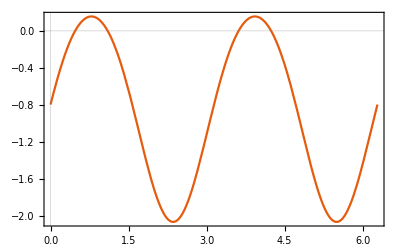

```mathematica
cp[θ_]:=({{Cos[θ], Sin[θ]}, {-Sin[θ], Cos[θ]}});
c[θ_]:=X.cp[θ];
cocc[θ_]:={c[θ]⟦;;,1⟧}ᵀ;
cocc[θ]//MatrixForm
P[θ_]:=2cocc[θ].cocc[θ]ᵀ//FullSimplify//Chop;
P[θ]//MatrixForm
Eh[θ_]:=Tr[P[θ].h];
UJ=Flatten[U,{{1},{3},{2,4}}];	UK=Flatten[U,{{1},{4},{2,3}}];
EJ[θ_]:= Tr[P[θ].UJ.Flatten[P[θ]]]/2;
EK[θ_]:= -Tr[P[θ].UK.Flatten[P[θ]]]/4;
EHFmat[θ_]:=Eh[θ]+EJ[θ]+EK[θ]//FullSimplify//Chop
EHFmat[θ]
Minimize[EHFmat[θ],θ]
EHF[θ_]:=(2∑_(i=1)^1 ∑_(μ=1)^2 ∑_(ν=1)^2 cocc[θ]⟦μ,i⟧h⟦μ,ν⟧cocc[θ]⟦ν,i⟧)+(∑_(i=1)^1 ∑_(j=1)^1 ∑_(μ=1)^2 ∑_(ν=1)^2 ∑_(λ=1)^2 ∑_(σ=1)^2 cocc[θ]⟦μ,i⟧cocc[θ]⟦ν,j⟧(2U⟦μ,ν,λ,σ⟧-U⟦μ,λ,ν,σ⟧)cocc[θ]⟦λ,j⟧cocc[θ]⟦σ,i⟧)//FullSimplify//Chop
EHF[θ]
Minimize[EHF[θ],θ]
Plot[EHF[θ],{θ,0,2π},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["E_\\text{HF}",FontSize->18]}]
```

Using the MCSCF module defined above we obtain the HF energy as

```mathematica
(MCSCF[1.,"Hyperspherical",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-0.87631-1.11077 Cos[2 θ12]-0.0789245 Cos[4 θ12]

The stationary points have the same energies, they are just shifted with respect to θ

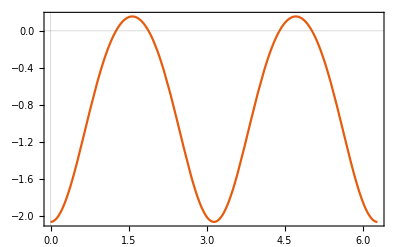

```mathematica
Plot[-0.8763100319882497-1.1107651487598644 Cos[2 θ12]-0.0789245335892632 Cos[4 θ12],{θ12,0,2π},PlotTheme->"Scientific",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["E_\\text{HF}",FontSize->18]}]
```

### MCSCF = oo-CID

Now we want to optimize the following wave function

```mathematica
Subscript[ψ, MCSCF]=Subscript[C, 1]|χ1 OverBar[χ1]> + Subscript[C, 2]|χ2 OverBar[χ2]> = Cos[ϕ]|χ1 OverBar[χ1]> + Sin[ϕ]|χ2 OverBar[χ2]>
```

The energy of this wave function is the following

```mathematica
E= ∑_ij <i|h|j>Subscript[γ, ij] +1/2 ∑_ijkl (ij|kl)Subscript[Γ, ijkl]
E= ∑_ij <i|h|j>Subscript[γ, ij] +1/2 ∑_ijkl<ik|jl>Subscript[Γ, ijkl]
```

```mathematica
E= ∑_ij ∑_μν Subscript[C, i]^μ<μ|h|ν>Subscript[C, j]^ν Subscript[γ, ij] +1/2 ∑_ijkl ∑_μνλσ Subscript[C, i]^μ Subscript[C, k]^ν<μν|λσ>Subscript[C, j]^λ Subscript[C, l]^σ Subscript[Γ, ijkl]
```

Where the 1-RDM and 2-RDM are expressed in terms of the CI coefficients as follows

```mathematica
Subscript[γ, ij]=∑_IJ Subscript[c, I] Subscript[c, J] Subscript[γ, ij]^IJ=∑_IJ Subscript[c, I] Subscript[c, J]<I|SuperDagger[Subscript[a, j]] Subscript[a, i]|J>;
Subscript[Γ, ijkl]=∑_IJ Subscript[c, I] Subscript[c, J] Subscript[Γ, ijkl]^IJ=∑_IJ Subscript[c, I] Subscript[c, J]<I|SuperDagger[Subscript[a, l]] SuperDagger[Subscript[a, k]] Subscript[a, j] SuperDagger[Subscript[a, i]]|J>
```

```mathematica
γ[ϕ_]:=2({{Cos[ϕ]^2, 0}, {0, Sin[ϕ]^2}});
Γ[ϕ_]:=2({{({{Cos[ϕ]^2, 0}, {0, 0}}), ({{0, Cos[ϕ] Sin[ϕ]}, {0, 0}})}, {({{0, 0}, {Cos[ϕ] Sin[ϕ], 0}}), ({{0, 0}, {0, Sin[ϕ]^2}})}});
```

```mathematica
EMCSCF[θ_,ϕ_]=(∑_(i=1)^2 ∑_(j=1)^2 ∑_(μ=1)^2 ∑_(ν=1)^2 c[θ]⟦μ,i⟧h⟦μ,ν⟧c[θ]⟦ν,j⟧γ[ϕ]⟦i,j⟧)+0.5(∑_(i=1)^2 ∑_(j=1)^2 ∑_(k=1)^2 ∑_(l=1)^2 ∑_(μ=1)^2 ∑_(ν=1)^2 ∑_(λ=1)^2 ∑_(σ=1)^2 c[θ]⟦μ,i⟧c[θ]⟦ν,j⟧U⟦μ,λ,ν,σ⟧c[θ]⟦λ,k⟧c[θ]⟦σ,l⟧Γ[ϕ]⟦i,j,k,l⟧)//FullSimplify//Chop
```

#### Equilibrium

```mathematica
EHF [θ12_]=(MCSCF[1.,"Hyperspherical",2,0,2,0,False,DataH2,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

0.12369-1.11077 Cos[2 θ12]-0.0789245 Cos[4 θ12]

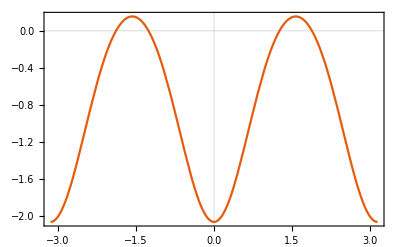

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

```mathematica
EMCSCFH2R1[θ12_,ϕ_]=MCSCF[1.,"Hyperspherical",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop
```

-0.87631-0.0789245 Cos[4 θ12]-0.555383 Cos[2 (θ12-ϕ)]-0.555383 Cos[2 (θ12+ϕ)]-0.0394623 Sin[4 θ12-2 ϕ]+0.182634 Cos[ϕ] Sin[ϕ]+0.0394623 Sin[2 (2 θ12+ϕ)]

```mathematica
EMCSCFH2R1[θ,0]//Chop//FullSimplify
```

-0.87631-1.11077 Cos[2 θ]-0.0789245 Cos[4 θ]

```mathematica
MCSCFsurface=Plot3D[EMCSCFH2R1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]]
```

-Graphics3D-

Then we can add the HF energy on this landscape

```mathematica
HFparametric=ParametricPlot3D[{θ,0,EMCSCFH2R1[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
```

```mathematica
Show[MCSCFsurface,HFparametric]
```

-Graphics3D-

To plot the CID energy we need to find the value of θ associated with the HF ground state

```mathematica
{E0,θ0}=Minimize[EMCSCFH2R1[θ,0],θ]
```

{-2.066,{θ→-5.12811×10^-9}}

```mathematica
CISparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFH2R1[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
```

```mathematica
Show[MCSCFsurface,HFparametric,CISparametric]
```

-Graphics3D-

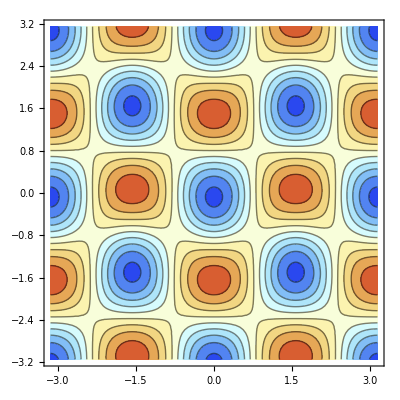

```mathematica
ContourPlot[EMCSCFH2R1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

Then use the FindRoot function to obtain the coordinates of the stationnary points. The above contour plots helps to pick the starting points.

```mathematica
Dθ[θ_,ϕ_]=D[EMCSCFH2R1[θ,ϕ],θ];
Dϕ[θ_,ϕ_]=D[EMCSCFH2R1[θ,ϕ],ϕ];
```

The energies of the stationary points of this surface are

```mathematica
Print[StationaryPoint[EMCSCFH2R1]⟦1⟧]
```

{-2.07897,-0.809778,-0.784993,0.168501}

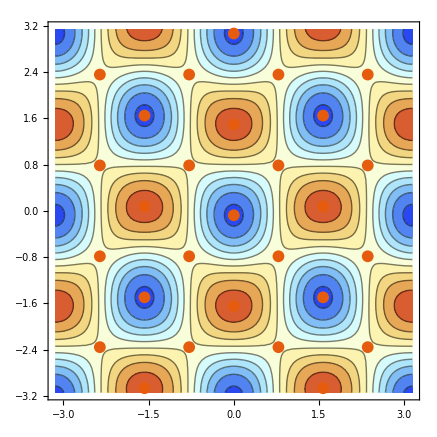

```mathematica
colorFun=Function[{x,y},Blend[{{-2.0789700154373642604`8.,Red},{0.1685008842823384756`8.,Blue}},EMCSCFH2R1[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFH2R1]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFH2R1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

The 4 MCSCF energies above should be compared with the FCI values below

{-1.07897001543736,-0.150260730769419,0.190222135596553,1.16850088428234}

#### Stretched slightly to R=5

```mathematica
EHF [θ12_]=(MCSCF[5.,"Hyperspherical",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-0.500309-0.0423612 Cos[2 θ12]-0.143746 Cos[4 θ12]

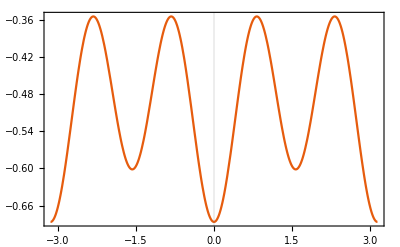

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

```mathematica
EMCSCFH2R5[θ12_,ϕ_]=MCSCF[5.,"Hyperspherical",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop
```

-0.500309-0.143746 Cos[4 θ12]-0.0211806 Cos[2 (θ12-ϕ)]-0.0211806 Cos[2 (θ12+ϕ)]-0.0718728 Sin[4 θ12-2 ϕ]+0.287975 Cos[ϕ] Sin[ϕ]+0.0718728 Sin[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFH2R5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]]
```

-Graphics3D-

```mathematica
HFparametric=ParametricPlot3D[{θ,0,EMCSCFH2R5[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFH2R5[θ,0],θ];
CISparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFH2R5[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CISparametric]
```

-Graphics3D-

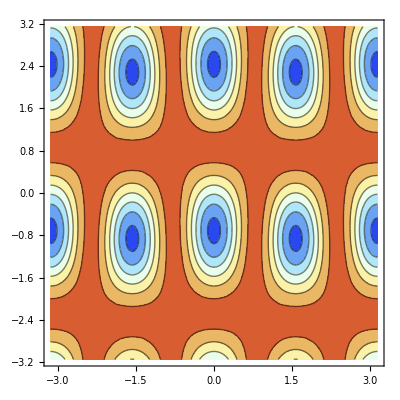

```mathematica
ContourPlot[EMCSCFH2R5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

```mathematica
Print[StationaryPoint[EMCSCFH2R5]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-0.934889,-0.356806,-0.356322,-0.353221,-0.353221,-0.35322}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

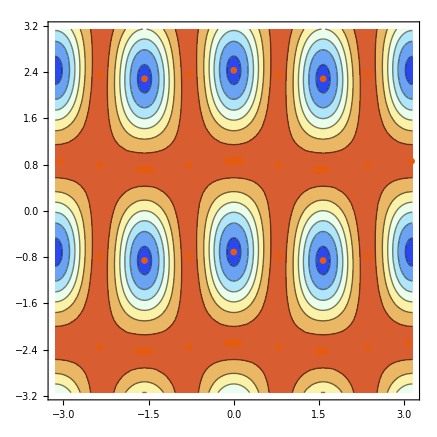

```mathematica
colorFun=Function[{x,y},Blend[{{-0.9348894381644876628`6.,Red},{-0.3532203470892000818`6.,Blue}},EMCSCFH2R1[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFH2R5]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFH2R5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

The 4 MCSCF energies above should be compared with the FCI values below

{-0.934889438164488,-0.932271716130147,-0.356805784104212,-0.3532203470892}

#### Let’s stretch even more up to R=10

```mathematica
EHF [θ12_]=(MCSCF[10.,"Hyperspherical",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-0.427209-0.000109914 Cos[2 θ12]-0.168651 Cos[4 θ12]

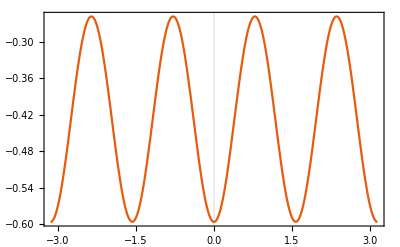

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

```mathematica
EMCSCFH2R10[θ12_,ϕ_]=MCSCF[10.,"Hyperspherical",2,1,DataH2,γ2,Γ2]//FullSimplify//Chop
```

-0.427209-0.168651 Cos[4 θ12]-0.000054957 Cos[2 (θ12-ϕ)]-0.000054957 Cos[2 (θ12+ϕ)]-0.0843257 Sin[4 θ12-2 ϕ]+0.337303 Cos[ϕ] Sin[ϕ]+0.0843257 Sin[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFH2R10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]]
```

-Graphics3D-

```mathematica
HFparametric=ParametricPlot3D[{θ,0,EMCSCFH2R10[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFH2R10[θ,0],θ];
CISparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFH2R10[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CISparametric]
```

-Graphics3D-

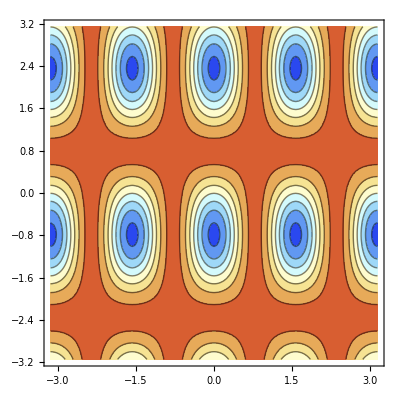

```mathematica
ContourPlot[EMCSCFH2R10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

```mathematica
Print[StationaryPoint[EMCSCFH2R10]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{-0.933164,-0.258558}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

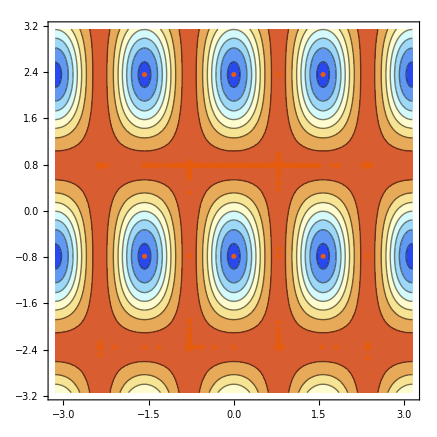

```mathematica
colorFun=Function[{x,y},Blend[{{-0.9331637534584997784`6.,Red},{-0.2585578119580984602`6.,Blue}},EMCSCFH2R1[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFH2R10]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFH2R10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

The 4 MCSCF energies above should be compared with the FCI values below

{-0.9331637534585,-0.933163737398712,-0.258557831715034,-0.258557811958098}

#### MCSCF PES

In this subsection we want to plot the MCSCF energies as function of the bond length

```mathematica
NRJ={};
{x0,y0}={-0.7853981633974483011`8.,0.7853981633974482939`8.}
Do[EMCSCFH2PES[θ12_,ϕ_]=MCSCF[R,"Exponential",2,0,2,0,False,DataH2,γ2,Γ2]//FullSimplify//Chop;
tmp=StationaryPointOnePoint[EMCSCFH2PES,{x0,y0}];
{x0,y0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataH2⟦;;,1⟧}]
```

{-0.78539816,0.78539816}

FindRoot::precw: The precision of the argument function ({-0.142388 Cos[4 x$48713-2 y$48713]+0.142388 Cos[2 (2 x$48713+y$48713)]+0.284775 Sin[4 x$48713]+2.04597 Sin[2 (x$48713-y$48713)]+2.04597 Sin[2 (x$48713+y$48713)],0.0711938 Cos[4 x$48713-2 y$48713]+0.1701 Cos[y$48713]^2+0.0711938 Cos[2 (2 x$48713+y$48713)]-2.04597 Sin[2 (x$48713-y$48713)]-0.1701 Sin[y$48713]^2+2.04597 Sin[2 (x$48713+y$48713)]}) is less than WorkingPrecision (20.).

{4.63047,{-0.78539816339744830962,0.78539816339744830962}}

FindRoot::precw: The precision of the argument function ({-0.144666 Cos[4 x$48721-2 y$48721]+0.144666 Cos[2 (2 x$48721+y$48721)]+0.289333 Sin[4 x$48721]+1.83381 Sin[2 (x$48721-y$48721)]+1.83381 Sin[2 (x$48721+y$48721)],0.0723331 Cos[4 x$48721-2 y$48721]+0.171843 Cos[y$48721]^2+0.0723331 Cos[2 (2 x$48721+y$48721)]-1.83381 Sin[2 (x$48721-y$48721)]-0.171843 Sin[y$48721]^2+1.83381 Sin[2 (x$48721+y$48721)]}) is less than WorkingPrecision (20.).

{2.02384,{-0.78539816339744830962,0.78539816339744830962}}

FindRoot::precw: The precision of the argument function ({-0.148186 Cos[4 x$48729-2 y$48729]+0.148186 Cos[2 (2 x$48729+y$48729)]+0.296372 Sin[4 x$48729]+1.57401 Sin[2 (x$48729-y$48729)]+1.57401 Sin[2 (x$48729+y$48729)],0.0740929 Cos[4 x$48729-2 y$48729]+0.174634 Cos[y$48729]^2+0.0740929 Cos[2 (2 x$48729+y$48729)]-1.57401 Sin[2 (x$48729-y$48729)]-0.174634 Sin[y$48729]^2+1.57401 Sin[2 (x$48729+y$48729)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1.06717,{-0.78539816339744830962,0.78539816339744830962}}

{0.543536,{-0.78539816339744830962,0.78539816339744830962}}

{0.215007,{-0.78539816339744830962,0.78539816339744830962}}

{-0.00159034,{-0.78539816339744830962,0.78539816339744830962}}

{-0.146811,{-0.78539816339744830962,0.78539816339744830962}}

{-0.244952,{-0.78539816339744830962,0.78539816339744830962}}

{-0.311704,{-0.78539816339744830962,0.78539816339744830962}}

{-0.357073,{-0.78539816339744830962,0.78539816339744830962}}

{-0.387348,{-0.78539816339744830962,0.78539816339744830962}}

{-0.406609,{-0.78539816339744830962,0.78539816339744830962}}

{-0.417705,{-0.78539816339744830962,0.78539816339744830962}}

{-0.422751,{-0.78539816339744830962,0.78539816339744830962}}

{-0.423371,{-0.78539816339744830962,0.78539816339744830962}}

{-0.420818,{-0.78539816339744830962,0.78539816339744830962}}

{-0.416054,{-0.78539816339744830962,0.78539816339744830962}}

{-0.409809,{-0.78539816339744830962,0.78539816339744830962}}

{-0.402631,{-0.78539816339744830962,0.78539816339744830962}}

{-0.394926,{-0.78539816339744830962,0.78539816339744830962}}

{-0.356322,{-0.78539816339744830962,0.78539816339744830962}}

{-0.324936,{-0.78539816339744830962,0.78539816339744830962}}

{-0.301386,{-0.78539816339744830962,0.78539816339744830962}}

{-0.283556,{-0.78539816339744830962,0.78539816339744830962}}

{-0.269669,{-0.78539816339744830962,0.78539816339744830962}}

{-0.258558,{-0.78539816339744830962,0.78539816339744830962}}

```mathematica
NRJ
```

{{0.2,4.63047},{0.4,2.02384},{0.6,1.06717},{0.8,0.543536},{1.,0.215007},{1.2,-0.00159034},{1.4,-0.146811},{1.6,-0.244952},{1.8,-0.311704},{2.,-0.357073},{2.2,-0.387348},{2.4,-0.406609},{2.6,-0.417705},{2.8,-0.422751},{3.,-0.423371},{3.2,-0.420818},{3.4,-0.416054},{3.6,-0.409809},{3.8,-0.402631},{4.,-0.394926},{5.,-0.356322},{6.,-0.324936},{7.,-0.301386},{8.,-0.283556},{9.,-0.269669},{10.,-0.258558}}

```mathematica
H2ooCID={{{0.2,2.42230157047775},{0.4,0.02495716011572645},{0.6000000000000001,-0.6765112298934988},{0.8,-0.9575994963009805},{1.,-1.0789700154373634},{1.2,-1.1266995234096084},{1.4000000000000001,-1.1372770104142325},{1.6,-1.1288161132395838},{1.8,-1.1108467412813268},{2.,-1.0884966011722632},{2.2,-1.0647398791016438},{2.4000000000000004,-1.0414900455305443},{2.6000000000000005,-1.0200242750046378},{2.8000000000000003,-1.0011256484056892},{3.0000000000000004,-0.985157044638394},{3.2,-0.9721476914439873},{3.4000000000000004,-0.9618850839275943},{3.6000000000000005,-0.9540124188361454},{3.8000000000000003,-0.9481141164559448},{4.,-0.9437786018820767},{5.,-0.9348894381644877},{6.,-0.9334022461481453},{7.,-0.9331913229665503},{8.,-0.9331664331993723},{9.,-0.9331639579122714},{10.,-0.9331637534584998}},
{{0.2,4.602762116594556},{0.4,1.9966654529705383},{0.6000000000000001,1.0407177435050263},{0.8,0.5178885087164995},{1.,0.19022213559655357},{1.2,-0.025357822971431312},{1.4000000000000001,-0.16929159449917047},{1.6,-0.2658199690848104},{1.8,-0.330662794978769},{2.,-0.3739223453139204},{2.2,-0.40200857849271837},{2.4000000000000004,-0.4191215218801877},{2.6000000000000005,-0.42820032603026603},{2.8000000000000003,-0.4314220838810943},{3.0000000000000004,-0.4304399233678967},{3.2,-0.4265130139708552},{3.4000000000000004,-0.42059152364510044},{3.6000000000000005,-0.41338529672665936},{3.8000000000000003,-0.4054193334904135},{4.,-0.397075671310828},{5.,-0.35680578410421215},{6.,-0.325013356254359},{7.,-0.30139482575478094},{8.,-0.2835563012584007},{9.,-0.269668860926639},{10.,-0.2585578317150343}},{{0.2,4.630474552707782},{0.4,2.023841841122309},{0.6000000000000001,1.067166131455299},{0.8,0.5435360946813066},{1.,0.21500686760547336},{1.2,-0.001590339868481852},{1.4000000000000001,-0.14681085512638098},{1.6,-0.24495212690980006},{1.8,-0.31170406901377873},{2.,-0.3570734864625194},{2.2,-0.387347594968979},{2.4000000000000004,-0.40660912183246745},{2.6000000000000005,-0.4177046712065027},{2.8000000000000003,-0.4227507588542431},{3.0000000000000004,-0.4233706845992349},{3.2,-0.4208181213336009},{3.4000000000000004,-0.4160542130699926},{3.6000000000000005,-0.4098088771107864},{3.8000000000000003,-0.4026307942000177},{4.,-0.39492594019131066},{5.,-0.3563219266138763},{6.,-0.3249361352816156},{7.,-0.3013860187894042},{8.,-0.2835555742729221},{9.,-0.26966881759872197},{10.,-0.2585578298664606}},{{0.2,6.526159749324689},{0.4,3.7062176232749793},{0.6000000000000001,2.4880235318478854},{0.8,1.7137126790452892},{1.,1.1685008842823374},{1.2,0.7724537614862511},{1.4000000000000001,0.4811395944342054},{1.6,0.2641823410068406},{1.8,0.09982450161728944},{2.,-0.026695255626210945},{2.2,-0.12481172956737477},{2.4000000000000004,-0.2005883374005627},{2.6000000000000005,-0.25825225729992485},{2.8000000000000003,-0.3010821588060047},{3.0000000000000004,-0.33181903595539197},{3.2,-0.3528288476600528},{3.4000000000000004,-0.36616427879118096},{3.6000000000000005,-0.37358588629875245},{3.8000000000000003,-0.3765719480523986},{4.,-0.37632940576304763},{5.,-0.3532203470892001},{6.,-0.32450900364605834},{7.,-0.3013383888647258},{8.,-0.2835512287501513},{9.,-0.26966849883151245},{10.,-0.2585578119580984}}};
```

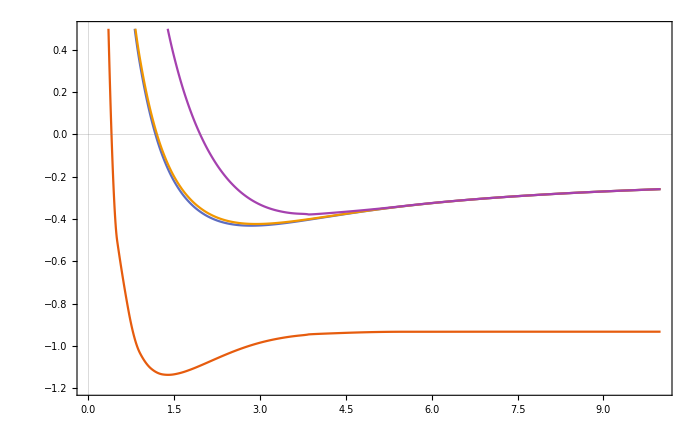

```mathematica
PESH2ooCID=ListPlot[H2ooCID,Joined->True,ImageSize->700,BaseStyle->18,PlotRange->{{0,10},{-1.2,0.5}},FrameStyle->Directive[Thick,18,Black],PlotTheme->"Scientific",PlotLegends->{MaTeX["\\text{MCSCF gs}",FontSize->22],MaTeX["\\text{MCSCF singlet ses}",FontSize->22],MaTeX["\\text{MCSCF spurious}",FontSize->22],MaTeX["\\text{MCSCF des}",FontSize->22]},InterpolationOrder->2]
```

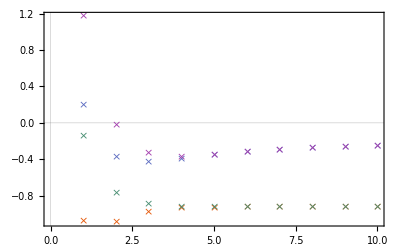

```mathematica
FCIPES=ListPlot[Table[H2FCIEnergies⟦;;,{1,n+1}⟧,{n,4}],PlotMarkers->"×",PlotStyle->{RGBColor[0.9, 0.36, 0.054],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.645957, 0.253192, 0.685109]},PlotTheme->"Scientific"]
```

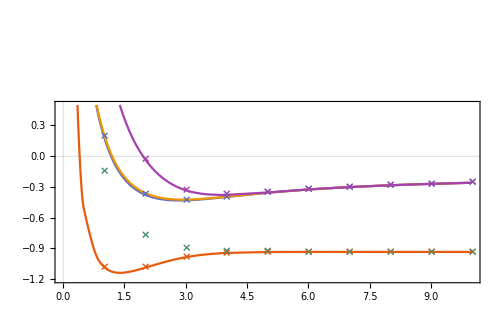

/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCID_PES.pdf

```mathematica
PESH2ooCID=Show[PESH2ooCID,FCIPES,ImageSize->500]
Export["/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCID_PES.pdf",PESH2ooCID]
```

#### Investigation of the unphysical solution

One can show that the metric of the tangent space at a given point (θ,ϕ) in this system is

```mathematica
g=({{4Cos[ϕ]Sin[ϕ]-4, 0}, {0, 4}})
```

The first column becomes equal to zero for the value of ϕ of the solution which do not correspond to any FCI states. So the metric of the tangent space becomes singular.
We can also see that the physical singly excited states merge with the doubly excited stationary points. On the other hand, the unphysical solution still exist as a different stationary point with the same energy.

#### Natural orbitals and population analysis R=1

```mathematica
EH2ooCIDR1[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataH2,γ2,Γ2]//FullSimplify//Chop
```

0.12369-0.0789245 Cos[4 θ12]-0.555383 Cos[2 (θ12-ϕ)]-0.555383 Cos[2 (θ12+ϕ)]-0.0394623 Sin[4 θ12-2 ϕ]+0.182634 Cos[ϕ] Sin[ϕ]+0.0394623 Sin[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EH2ooCIDR1]
```

FindRoot::precw: The precision of the argument function ({-0.157849 Cos[4 x$4124-2 y$4124]+0.157849 Cos[2 (2 x$4124+y$4124)]+0.315698 Sin[4 x$4124]+1.11077 Sin[2 (x$4124-y$4124)]+1.11077 Sin[2 (x$4124+y$4124)],0.0789245 Cos[4 x$4124-2 y$4124]+0.182634 Cos[y$4124]^2+0.0789245 Cos[2 (2 x$4124+y$4124)]-1.11077 Sin[2 (x$4124-y$4124)]-0.182634 Sin[y$4124]^2+1.11077 Sin[2 (x$4124+y$4124)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

{{-1.07897,0.190222,0.215007,1.1685},{{-1.07897,{-1.5707963,-1.4947555}},{-1.07897,{-1.5707963,1.6468371}},{1.1685009,{-1.5707963,0.076040787}},{1.1685009,{-1.5707963,-3.0655519}},{1.1685009,{0,1.4947555}},{-1.07897,{0,-0.076040787}},{0.19022214,{-2.3561945,-0.78539816}},{0.19022214,{-2.3561945,2.3561945}},{0.21500687,{-0.78539816,0.78539816}},{0.19022214,{-0.78539816,-0.78539816}},{0.21500687,{-2.3561945,-2.3561945}},{-1.07897,{1.5707963,-1.4947555}},{1.1685009,{0,-1.6468371}},{0.21500687,{-2.3561945,0.78539816}},{0.21500687,{0.78539816,-2.3561945}},{1.1685009,{1.5707963,-3.0655519}},{0.19022214,{0.78539816,-0.78539816}},{0.21500687,{2.3561945,0.78539816}},{1.1685009,{1.5707963,0.076040787}},{0.19022214,{2.3561945,-0.78539816}},{-1.07897,{0,3.0655519}},{0.19022214,{0.78539816,2.3561945}},{0.21500687,{0.78539816,0.78539816}},{0.19022214,{2.3561945,2.3561945}},{-1.07897,{1.5707963,1.6468371}},{0.21500687,{-0.78539816,-2.3561945}},{0.19022214,{-0.78539816,2.3561945}},{0.21500687,{2.3561945,-2.3561945}}}}

```mathematica
NaturOrbH2ooCID[{θ_,ϕ_}]:=Module[{cHF,RDM,Coeff},
(*cHF=1/(√2)({{1, 1}, {1, -1}});*)
cHF=({{-0.5275464471283402, -1.5678235349401517}, {-0.5275464471283418, 1.5678235349401521}});
RDM=γ2[ϕ];
Coeff=cHF.{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
SignOrb[x_]:=If[x>0,White,RGBColor[0, 0, 0]];
Print["The solution with energy ",Chop@EH2ooCIDR1[θ,ϕ]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{0,1.5},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{1.3,1.5},Abs@Coeff⟦2,2⟧]},
{White,Disk[{2.6,1.5},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{0,0},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{1.3,0},Abs@Coeff⟦2,1⟧]},
{White,Disk[{2.6,0},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,3],14],{2.6,1.5}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,3],14],{2.6,0}]}
]
]
```

```mathematica
PopH2ooCID[θ12_,ϕ_]=PopAna[1.,"Exponential",2,0,2,0,False,DataH2,γ2,Γ2]//MatrixForm;
```

The solution with energy -1.07897

The occupation numbers at convergence are (0.0115421 | 0
0 | 1.9884579)

The corresponding MOs are (1.56782 | -0.527546
-1.56782 | -0.527546)

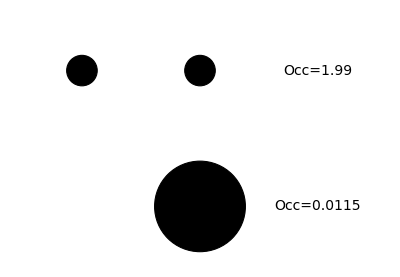

(1. | 0.988458
0.988458 | 1.)

```mathematica
NaturOrbH2ooCID[{-1.5707963267948967052`8.,-1.4947555401756785575`8.}]
PopH2ooCID[-1.5707963267948967052`8.,-1.4947555401756785575`8.]
```

The solution with energy 1.1685

The occupation numbers at convergence are (1.9884579 | 0
0 | 0.0115421)

The corresponding MOs are (1.56782 | -0.527546
-1.56782 | -0.527546)

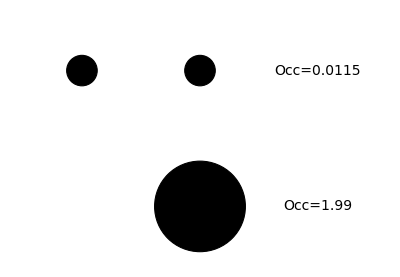

(1. | -0.988458
-0.988458 | 1.)

```mathematica
NaturOrbH2ooCID[{-1.5707963267948969101`8.,-3.0655518669705752917`8.}]
PopH2ooCID[-1.5707963267948969101`8.,-3.0655518669705752917`8.]
```

The solution with energy 0.190222

The occupation numbers at convergence are (1. | 0
0 | 1.)

The corresponding MOs are (0.735587 | -1.48165
-1.48165 | 0.735587)

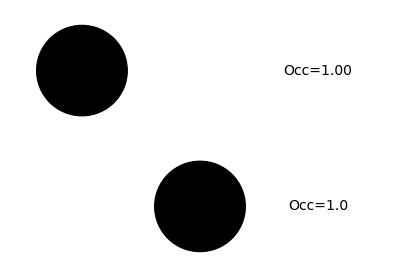

(1. | -1.33227×10^-15
1.33227×10^-15 | 1.)

```mathematica
NaturOrbH2ooCID[{-0.7853981633974483772`8.,-0.7853981633974483425`8.}]
PopH2ooCID[-0.7853981633974483772`8.,-0.7853981633974483425`8.]
```

The solution with energy 0.215007

The occupation numbers at convergence are (1. | 0
0 | 1.)

The corresponding MOs are (1.48165 | 0.735587
-0.735587 | -1.48165)

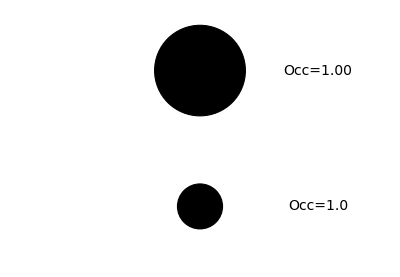

(1. | -1.77636×10^-15
1.77636×10^-15 | 1.)

```mathematica
NaturOrbH2ooCID[{-2.3561944901923449288`8.,-2.3561944901923449288`8.}]
PopH2ooCID[-2.3561944901923449288`8.,-2.3561944901923449288`8.]
```

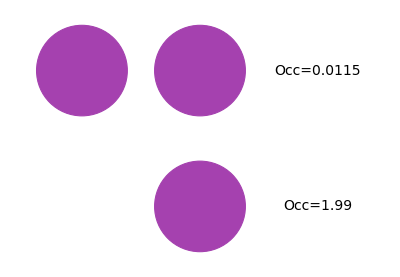
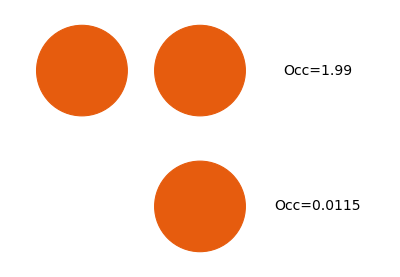
```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{,}},ImageSize->600,Spacings->2]
```

-Graphics-

#### Natural orbitals R=10

```mathematica
EH2ooCIDR10[θ12_,ϕ_]=MCSCF[10.,"Exponential",2,0,2,0,False,DataH2,γ2,Γ2]//FullSimplify//Chop
```

-0.427209-0.168651 Cos[4 θ12]-0.000054957 Cos[2 (θ12-ϕ)]-0.000054957 Cos[2 (θ12+ϕ)]-0.0843257 Sin[4 θ12-2 ϕ]+0.337303 Cos[ϕ] Sin[ϕ]+0.0843257 Sin[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EH2ooCIDR10]
```

{{-0.933164,-0.258558},{{-0.93316375,{-1.5707963,-0.78556109}},{-0.25855781,{-1.5707982,0.78523523}},{-0.25855781,{-1.5707963,0.78523523}},{-0.25855781,{-0.80537577,-2.360273}},{-0.25855781,{-2.3633368,-2.3447916}},{-0.25855781,{-0.77534523,0.79350047}},{-0.25855781,{-0.81830988,0.78292115}},{-0.25855781,{-0.80810629,0.7818095}},{-0.25855781,{-0.82511501,0.78334487}},{-0.25855783,{-0.78539816,0.78539816}},{-0.25855781,{-0.84809065,0.78409531}},{-0.25855783,{-0.78539816,-2.3561945}},{-0.25855781,{-0.67700081,-2.355437}},{-0.25855781,{-0.88544924,0.78457849}},{-0.25855781,{-0.79200484,0.77307115}},{-0.25855781,{-0.79642187,0.77800879}},{-0.25855781,{-0.79523606,0.77711762}},{-0.25855781,{-0.82412765,0.78329271}},{-0.25855783,{-0.78539816,-0.78539816}},{-0.25855781,{-0.78636307,0.70119084}},{-0.25855781,{-0.79352975,0.77538316}},{-0.25855781,{-0.78766441,0.74947355}},{-0.25855781,{-0.80183248,0.78044095}},{-0.25855781,{-0.9039443,0.78470449}},{-0.25855781,{-0.7808936,-2.3381143}},{-0.25855781,{-0.73083168,-2.3546986}},{-0.25855781,{-0.80209207,0.78051815}},{-0.25855781,{-0.77276585,0.79184732}},{-0.25855781,{-0.77747886,0.79568426}},{-0.25855781,{-0.77963475,0.79953113}},{-0.25855781,{-0.7729366,-2.349657}},{-0.25855781,{-0.68299186,-2.3553934}},{-0.25855781,{1.826001,0.78521143}},{-0.25855781,{0.78567413,0.49840616}},{-0.25855783,{0.78539816,-2.3561945}},{-0.25855781,{-0.75538005,0.7881136}},{-0.25855781,{-0.75249331,0.78787565}},{-0.25855781,{-0.70179892,0.78637717}},{-0.25855781,{-0.77298321,0.79196026}},{-0.93316375,{0,-0.78523523}},{-0.25855781,{-0.75734326,0.78830343}},{-0.25855781,{-0.67415961,0.78613659}},{-0.25855781,{-0.3547622,0.78561292}},{-0.25855781,{-0.68810316,0.78624077}},{-0.25855781,{0.88423627,-2.3570241}},{-0.25855781,{0.77000716,0.79069182}},{-0.25855783,{0.78539816,0.78539816}},{-0.25855781,{0.72694761,0.78679508}},{-0.25855781,{0.69713759,0.78632597}},{-0.25855781,{0.72062426,-2.3549333}},{-0.25855781,{2.4086685,-2.3546392}},{-0.25855781,{0.79078741,0.77028422}},{-0.25855781,{0.76413654,0.78923068}},{-0.25855781,{0.75610428,0.78818054}},{-0.25855781,{0.77648021,0.79453229}},{-0.25855781,{0.67670664,-2.3554391}},{-0.25855781,{0.78349668,-2.3133828}},{-0.25855781,{0.78486978,-2.2032299}},{-0.25855783,{0.78539816,-0.78539816}},{-0.25855781,{0.77631968,0.7943712}},{-0.25855781,{0.7799114,0.80024353}},{-0.25855781,{0.67402027,0.78613566}},{-0.25855781,{0.78707732,0.73693184}},{-0.25855781,{0.79323879,0.77501102}},{-0.25855781,{0.79051814,0.76948937}},{-0.25855781,{0.80748585,0.78170904}},{-0.25855781,{0.79718707,0.77848769}},{-0.25855781,{0.77828677,-2.3447401}},{-0.93316375,{-1.5707963,2.3560316}},{-0.25855781,{0.79222418,0.77346483}},{-0.25855781,{0.79584087,0.77759733}},{-0.25855781,{0.83352238,0.7837028}},{-0.25855781,{0.80766614,0.78173862}},{-0.25855783,{2.3561945,0.78539816}},{-0.93316375,{1.5707963,-0.78556109}},{-0.25855781,{0.88808182,0.7845992}},{-0.25855781,{0.86881826,0.78441706}},{-0.25855781,{0.79972594,0.7797122}}}}

```mathematica
NaturOrbH2ooCIDR10[{θ_,ϕ_}]:=Module[{cHF,RDM,Coeff},
(*cHF=1/(√2)({{1, 1}, {1, -1}});*)
cHF=({{-0.5275464471283402, -1.5678235349401517}, {-0.5275464471283418, 1.5678235349401521}});
RDM=γ2[ϕ];
Coeff=cHF.{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
SignOrb[x_]:=If[x>0,White,RGBColor[0, 0, 0]];
Print["The solution with energy ",Chop@EH2ooCIDR10[θ,ϕ]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{0,1.5},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{1.3,1.5},Abs@Coeff⟦2,2⟧]},
{White,Disk[{2.6,1.5},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{0,0},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{1.3,0},Abs@Coeff⟦2,1⟧]},
{White,Disk[{2.6,0},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,3],14],{2.6,1.5}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,3],14],{2.6,0}]}
]
]
```

```mathematica
PopH2ooCIDR10[θ12_,ϕ_]=PopAna[10.,"Exponential",2,0,2,0,False,DataH2,γ2,Γ2]//MatrixForm;
```

The solution with energy -0.933164

The occupation numbers at convergence are (0.9996741 | 0
0 | 1.000326)

The corresponding MOs are (1.56782 | -0.527546
-1.56782 | -0.527546)

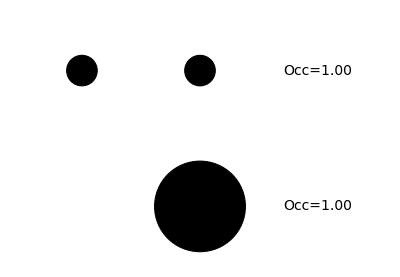

(1. | 0.000325861
0.000325861 | 1.)

```mathematica
NaturOrbH2ooCIDR10[{-1.5707963267948966193`8.,-0.7855610940725003391`8.}]
PopH2ooCIDR10[-1.5707963267948966193`8.,-0.7855610940725003391`8.]
```

The solution with energy -0.258558

The occupation numbers at convergence are (1.000326 | 0
0 | 0.9996741)

The corresponding MOs are (1.56782 | -0.527544
-1.56782 | -0.527549)

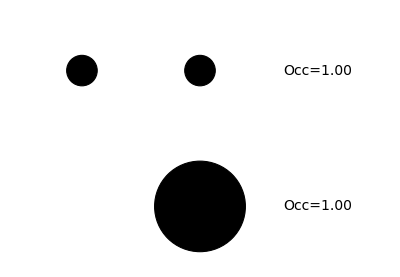

(1. | -0.000325861
-0.000325861 | 1.)

```mathematica
NaturOrbH2ooCIDR10[{-1.5707981832019939429`8.,0.7852352327223950621`8.}]
PopH2ooCIDR10[-1.5707981832019939429`8.,0.7852352327223950621`8.]
```

#### MOM

```mathematica
EMCSCFH2MOM[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataH2,γ2,Γ2]//FullSimplify//Chop
```

0.12369-0.0789245 Cos[4 θ12]-0.555383 Cos[2 (θ12-ϕ)]-0.555383 Cos[2 (θ12+ϕ)]-0.0394623 Sin[4 θ12-2 ϕ]+0.182634 Cos[ϕ] Sin[ϕ]+0.0394623 Sin[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFH2MOM[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]]
```

-Graphics3D-

```mathematica
EMCSCFH2MOM[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataH2MOM,γ2,Γ2]//FullSimplify//Chop
```

0.12369-0.0789245 Cos[4 θ12]+0.555383 Cos[2 (θ12-ϕ)]+0.555383 Cos[2 (θ12+ϕ)]-0.0394623 Sin[4 θ12-2 ϕ]+0.182634 Cos[ϕ] Sin[ϕ]+0.0394623 Sin[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFH2MOM[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]]
```

-Graphics3D-

```mathematica
StationaryPoint[EMCSCFH2MOM]
```

FindRoot::precw: The precision of the argument function ({-0.287491 Cos[4 x$20334-2 y$20334]+0.287491 Cos[2 (2 x$20334+y$20334)]+0.574982 Sin[4 x$20334]-0.0423612 Sin[2 (x$20334-y$20334)]-0.0423612 Sin[2 (x$20334+y$20334)],0.143746 Cos[4 x$20334-2 y$20334]+0.287975 Cos[y$20334]^2+0.143746 Cos[2 (2 x$20334+y$20334)]+0.0423612 Sin[2 (x$20334-y$20334)]-0.287975 Sin[y$20334]^2-0.0423612 Sin[2 (x$20334+y$20334)]}) is less than WorkingPrecision (20.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function ({-0.287491 Cos[4 x$20334-2 y$20334]+0.287491 Cos[2 (2 x$20334+y$20334)]+0.574982 Sin[4 x$20334]-0.0423612 Sin[2 (x$20334-y$20334)]-0.0423612 Sin[2 (x$20334+y$20334)],0.143746 Cos[4 x$20334-2 y$20334]+0.287975 Cos[y$20334]^2+0.143746 Cos[2 (2 x$20334+y$20334)]+0.0423612 Sin[2 (x$20334-y$20334)]-0.287975 Sin[y$20334]^2-0.0423612 Sin[2 (x$20334+y$20334)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-0.934889,-0.356806,-0.356322,-0.35322},{{-0.35322035,{-1.5707963,0.85848517}},{-0.93488944,{-1.5707963,-0.71231116}},{-0.35322035,{-1.5707963,-2.2831075}},{-0.35632193,{-2.3561945,-2.3561945}},{-0.35632193,{-0.78539816,0.78539816}},{-0.35322035,{0,0.71231116}},{-0.35632193,{-0.78539816,-2.3561945}},{-0.35632193,{-2.3561945,0.78539816}},{-0.35632193,{0.78539816,0.78539816}},{-0.35322035,{0,-2.4292815}},{-0.35680578,{-2.3561945,-0.78539816}},{-0.93488944,{0,2.2831075}},{-0.35632193,{2.3561945,-2.3561945}},{-0.35632193,{2.3561945,0.78539816}},{-0.35680578,{-0.78539816,-0.78539816}},{-0.35680578,{-0.78539816,2.3561945}},{-0.35680578,{2.3561945,-0.78539816}},{-0.35322035,{1.5707963,0.85848517}},{-0.93488944,{0,-0.85848517}},{-0.35322035,{1.5707963,-2.2831075}},{-0.35632193,{0.78539816,-2.3561945}},{-0.35680578,{0.78539816,-0.78539816}},{-0.93488944,{-1.5707963,2.4292815}},{-0.93488944,{1.5707963,2.4292815}},{-0.93488944,{1.5707963,-0.71231116}},{-0.35680578,{0.78539816,2.3561945}}}}

```mathematica
NRJ={};
{x0,y0}={0,-1.4947555401756784486`8.}
Do[EMCSCFH2PES[θ12_,ϕ_]=MCSCF[R,"Exponential",2,0,2,0,False,DataH2MOM,γ2,Γ2]//FullSimplify//Chop;
tmp=StationaryPointOnePoint[EMCSCFH2PES,{x0,y0}];
{x0,y0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataH2MOM⟦;;,1⟧}]
```

{0,-1.4947555}

FindRoot::precw: The precision of the argument function ({-0.142388 Cos[4 x$16809-2 y$16809]+0.142388 Cos[2 (2 x$16809+y$16809)]+0.284775 Sin[4 x$16809]-2.04597 Sin[2 (x$16809-y$16809)]-2.04597 Sin[2 (x$16809+y$16809)],0.0711938 Cos[4 x$16809-2 y$16809]+0.1701 Cos[y$16809]^2+0.0711938 Cos[2 (2 x$16809+y$16809)]+2.04597 Sin[2 (x$16809-y$16809)]-0.1701 Sin[y$16809]^2-2.04597 Sin[2 (x$16809+y$16809)]}) is less than WorkingPrecision (20.).

{2.4223,{0,-1.5326869998919556763}}

FindRoot::precw: The precision of the argument function ({-0.144666 Cos[4 x$16817-2 y$16817]+0.144666 Cos[2 (2 x$16817+y$16817)]+0.289333 Sin[4 x$16817]-1.83381 Sin[2 (x$16817-y$16817)]-1.83381 Sin[2 (x$16817+y$16817)],0.0723331 Cos[4 x$16817-2 y$16817]+0.171843 Cos[y$16817]^2+0.0723331 Cos[2 (2 x$16817+y$16817)]+1.83381 Sin[2 (x$16817-y$16817)]-0.171843 Sin[y$16817]^2-1.83381 Sin[2 (x$16817+y$16817)]}) is less than WorkingPrecision (20.).

{0.0249572,{0,-1.5277539831462848845}}

FindRoot::precw: The precision of the argument function ({-0.148186 Cos[4 x$16825-2 y$16825]+0.148186 Cos[2 (2 x$16825+y$16825)]+0.296372 Sin[4 x$16825]-1.57401 Sin[2 (x$16825-y$16825)]-1.57401 Sin[2 (x$16825+y$16825)],0.0740929 Cos[4 x$16825-2 y$16825]+0.174634 Cos[y$16825]^2+0.0740929 Cos[2 (2 x$16825+y$16825)]+1.57401 Sin[2 (x$16825-y$16825)]-0.174634 Sin[y$16825]^2-1.57401 Sin[2 (x$16825+y$16825)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{-0.676511,{0,-1.5197015335318436307}}

{-0.957599,{0,-1.5086898464210447596}}

{-1.07897,{0,-1.4947555401756784485}}

{-1.1267,{0,-1.4778349444736338578}}

{-1.13728,{0,-1.4578409535584657798}}

{-1.12882,{0,-1.4346142014166809614}}

{-1.11085,{0,-1.4078447009256421649}}

{-1.0885,{0,-1.3771395275045394638}}

{-1.06474,{0,-1.3422336999075552366}}

{-1.04149,{0,-1.3032037463178802467}}

{-1.02002,{0,-1.2605939851369803337}}

{-1.00113,{0,-1.2154248463299503424}}

{-0.985157,{0,-1.1690811206425126047}}

{-0.972148,{0,-1.1231128671609646507}}

{-0.961885,{0,-1.0789887593324552477}}

{-0.954012,{0,-1.03788736361395153}}

{-0.948114,{0,-1.000582299461352995}}

{-0.943779,{0,-0.96743265086953115622}}

{-0.934889,{0,-0.85848517116083485544}}

{-0.933402,{0,-0.81188688998932960668}}

{-0.933191,{0,-0.79408051562725471199}}

{-0.933166,{0,-0.78798454980135756349}}

{-0.933164,{0,-0.78609129847487812598}}

{-0.933164,{0,-0.78556109407250001192}}

### Another MCSCF ansätze = oo-CIS (SA)

Now we want to optimize the following wave function

```mathematica
Subscript[ψ, MCSCF]=Subscript[C, 1]|χ1 OverBar[χ1]> + Subscript[C, 2] 1/(√2)(|χ1 OverBar[χ2]>-|χ2 OverBar[χ1]>) = Cos[ϕ]|χ1 OverBar[χ1]> + Sin[ϕ] 1/(√2)(|χ1 OverBar[χ2]>-|χ2 OverBar[χ1]>)
```

```mathematica
E= ∑_ij ∑_μν Subscript[C, i]^μ<μ|h|ν>Subscript[C, j]^ν Subscript[γ, ij] +1/2 ∑_ijkl ∑_μνλσ Subscript[C, i]^μ Subscript[C, k]^ν<μν|λσ>Subscript[C, j]^λ Subscript[C, l]^σ Subscript[Γ, ijkl]
```

Where the 1-RDM and 2-RDM are expressed in terms of the CI coefficients as follows

```mathematica
Subscript[γ, ij]=∑_IJ Subscript[c, I] Subscript[c, J] Subscript[γ, ij]^IJ=∑_IJ Subscript[c, I] Subscript[c, J]<I|SuperDagger[Subscript[a, j]] Subscript[a, i]|J>;
Subscript[Γ, ijkl]=∑_IJ Subscript[c, I] Subscript[c, J] Subscript[Γ, ijkl]^IJ=∑_IJ Subscript[c, I] Subscript[c, J]<I|SuperDagger[Subscript[a, l]] SuperDagger[Subscript[a, k]] Subscript[a, j] SuperDagger[Subscript[a, i]]|J>
```

The difference with the previous MCSCF wave function is in the expressions for the associated reduced density matrices.

```mathematica
γ[ϕ_]=2({{Cos[ϕ]^2+1/2 Sin[ϕ]^2, 1/(√2)Sin[ϕ]Cos[ϕ]}, {1/(√2)Sin[ϕ]Cos[ϕ], 1/2 Sin[ϕ]^2}});
Γ[ϕ_]=2({{({{Cos[ϕ]^2, 1/(√2)Sin[ϕ]Cos[ϕ]}, {1/(√2)Sin[ϕ]Cos[ϕ], 1/2 Sin[ϕ]^2}}), ({{1/(√2)Sin[ϕ]Cos[ϕ], 0}, {1/2 Sin[ϕ]^2, 0}})}, {({{1/(√2)Sin[ϕ]Cos[ϕ], 1/2 Sin[ϕ]^2}, {0, 0}}), ({{1/2 Sin[ϕ]^2, 0}, {0, 0}})}});
```

#### Equilibrium

```mathematica
EHF [θ12_]=(MCSCF[1.,"Hyperspherical",2,1,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

0.12369-1.11077 Cos[2 θ12]-0.0789245 Cos[4 θ12]

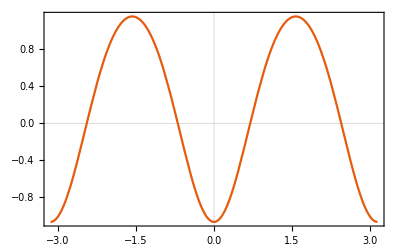

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

```mathematica
Minimize[EHF [θ1],θ1]
```

{-1.066,{θ1→-5.12811×10^-9}}

```mathematica
EMCSCFH2R1[θ12_,ϕ_]=MCSCF[1.,"Hyperspherical",2,1,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

0.0780315-0.555383 Cos[2 θ12]+0.0394623 Cos[4 θ12]-0.115001 Cos[4 θ12-2 ϕ]-0.670406 Cos[2 (θ12-ϕ)]+0.0456584 Cos[2 ϕ]+0.115023 Cos[2 (θ12+ϕ)]-0.00338533 Cos[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFH2R1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]]
```

-Graphics3D-

```mathematica
HFparametric=ParametricPlot3D[{θ,0,EMCSCFH2R1[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFH2R1[θ,0],θ];
CISparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFH2R1[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CIS}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CISparametric]
```

-Graphics3D-

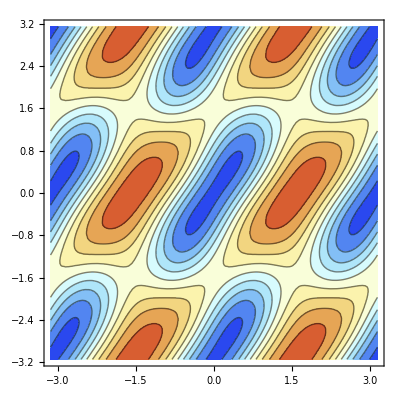

```mathematica
ContourPlot[EMCSCFH2R1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

The energies of the stationary points of this surface are

```mathematica
Print[StationaryPoint[EMCSCFH2R1]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-1.07897,-1.066,0.190222,1.15553}

```mathematica
colorFun=Function[{x,y},Blend[{{-1.0789700154373633723`6.,Red},{1.1555305831823514673`6.,Blue}},EMCSCFH2R1[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFH2R1]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFH2R1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-1.07897001543736,-0.150260730769419,0.190222135596553,1.16850088428234}

We see that the MCSCF stationary points correspond to the HF one, the exact ground state, the exact singlet excited state and an approximate doubly excited state.

```mathematica
Stretched slightly to R=5
```

#### Stretched slightly to R=5

```mathematica
EHF [θ12_]=(MCSCF[5.,"Hyperspherical",2,1,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-0.500309-0.0423612 Cos[2 θ12]-0.143746 Cos[4 θ12]

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
Minimize[EHF[θ],θ]
```

{-0.686416,{θ→-3.13855×10^-17}}

```mathematica
EMCSCFH2R5[θ12_,ϕ_]=MCSCF[5.,"Hyperspherical",2,1,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

-0.572303-0.0211806 Cos[2 θ12]+0.0718728 Cos[4 θ12]-0.209453 Cos[4 θ12-2 ϕ]-0.0255673 Cos[2 (θ12-ϕ)]+0.0719937 Cos[2 ϕ]+0.00438665 Cos[2 (θ12+ϕ)]-0.00616571 Cos[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFH2R5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]]
```

-Graphics3D-

```mathematica
HFparametric=ParametricPlot3D[{θ,0,EMCSCFH2R5[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFH2R5[θ,0],θ];
CISparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFH2R5[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CIS}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CISparametric]
```

-Graphics3D-

```mathematica
ContourPlot[EMCSCFH2R5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

```mathematica
Print[StationaryPoint[EMCSCFH2R5]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{-0.934889,-0.686416,-0.601694,-0.356806,-0.356768,-0.356613,-0.356461,-0.356309,-0.356291,-0.356274,-0.356219,-0.356212,-0.3562,-0.356172,-0.35611,-0.356103,-0.356085,-0.356076,-0.356026,-0.356025,-0.35596,-0.355957,-0.355888,-0.35581,-0.355793,-0.35576,-0.355647,-0.355643,-0.355614,-0.35561,-0.355591,-0.355518,-0.355513,-0.35549,-0.355457,-0.355448,-0.355425,-0.35542,-0.355399,-0.355374,-0.355362,-0.355357,-0.355348,-0.355329,-0.355316,-0.355304,-0.355298,-0.355294,-0.355282,-0.355269,-0.355268,-0.355262,-0.355259,-0.355257,-0.355255,-0.35521,-0.355202,-0.355168,-0.355167,-0.355156,-0.355152,-0.355147,-0.355142,-0.355121,-0.355115,-0.355108,-0.355099,-0.355069,-0.355061,-0.355053,-0.35504,-0.355037,-0.355025,-0.355015,-0.35501,-0.355003}

```mathematica
colorFun=Function[{x,y},Blend[{{-0.9348894381644876628`6.,Red},{0.3550033952795558223`6.,Blue}},EMCSCFH2R1[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFH2R5]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFH2R5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-0.934889438164488,-0.932271716130147,-0.356805784104212,-0.3532203470892}

#### Let’s stretch even more up to R=10

```mathematica
EHF [θ12_]=(MCSCF[10.,"Hyperspherical",2,1,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-0.427209-0.000109914 Cos[2 θ12]-0.168651 Cos[4 θ12]

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
EMCSCFH2R10[θ12_,ϕ_]=MCSCF[10.,"Hyperspherical",2,1,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

-0.511535-0.000054957 Cos[2 θ12]+0.0843257 Cos[4 θ12]-0.245743 Cos[4 θ12-2 ϕ]-0.000066339 Cos[2 (θ12-ϕ)]+0.0843257 Cos[2 ϕ]+0.000011382 Cos[2 (θ12+ϕ)]-0.007234 Cos[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFH2R10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]]
```

-Graphics3D-

```mathematica
HFparametric=ParametricPlot3D[{θ,0,EMCSCFH2R10[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFH2R10[θ,0],θ];
CISparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFH2R10[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CISparametric]
```

-Graphics3D-

```mathematica
ContourPlot[EMCSCFH2R10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

```mathematica
Print[StationaryPoint[EMCSCFH2R10]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-0.933164,-0.595971,-0.595751,-0.258558}

```mathematica
colorFun=Function[{x,y},Blend[{{-0.9331637534585000004`6.,Red},{-0.2585578317150344363`6.,Blue}},EMCSCFH2R1[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFH2R10]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFH2R10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-0.9331637534585,-0.933163737398712,-0.258557831715034,-0.258557811958098}

#### MCSCF PES

```mathematica
EMCSCFH2R1[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

0.0780315-0.555383 Cos[2 θ12]+0.0394623 Cos[4 θ12]-0.115001 Cos[4 θ12-2 ϕ]-0.670406 Cos[2 (θ12-ϕ)]+0.0456584 Cos[2 ϕ]+0.115023 Cos[2 (θ12+ϕ)]-0.00338533 Cos[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EMCSCFH2R1]
```

FindRoot::precw: The precision of the argument function ({1.11077 Sin[2 x$64885]-0.157849 Sin[4 x$64885]+0.460006 Sin[4 x$64885-2 y$64885]+1.34081 Sin[2 (x$64885-y$64885)]-0.230047 Sin[2 (x$64885+y$64885)]+0.0135413 Sin[2 (2 x$64885+y$64885)],-0.230003 Sin[4 x$64885-2 y$64885]-1.34081 Sin[2 (x$64885-y$64885)]-0.0913169 Sin[2 y$64885]-0.230047 Sin[2 (x$64885+y$64885)]+0.00677065 Sin[2 (2 x$64885+y$64885)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-1.07897,-1.066,0.190222,1.15553},{{0.19022214,{-1.5707963,-1.5707963}},{0.19022214,{-1.5707963,1.5707963}},{1.1555306,{-1.5707963,0}},{-1.07897,{2.8722773,2.7418027}},{-1.0659997,{0,0}},{-1.07897,{-2.8722773,-2.7418027}},{0.19022214,{0,1.5707963}},{-1.07897,{-2.8722773,0.39978997}},{-1.07897,{-0.26931534,-0.39978997}},{0.19022214,{1.5707963,1.5707963}},{-1.07897,{0.26931534,-2.7418027}},{1.1555306,{1.5707963,0}},{-1.07897,{0.26931534,0.39978997}},{-1.07897,{2.8722773,-0.39978997}},{0.19022214,{0,-1.5707963}},{-1.07897,{-0.26931534,2.7418027}},{0.19022214,{1.5707963,-1.5707963}}}}

```mathematica
EMCSCFH2[θ12_,ϕ_]=MCSCF[3.2,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

-0.604206-0.0968046 Cos[2 θ12]+0.0597057 Cos[4 θ12]-0.173995 Cos[4 θ12-2 ϕ]-0.116853 Cos[2 (θ12-ϕ)]+0.0611294 Cos[2 ϕ]+0.0200489 Cos[2 (θ12+ϕ)]-0.00512194 Cos[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EMCSCFH2]
```

FindRoot::precw: The precision of the argument function ({0.193609 Sin[2 x$68521]-0.238823 Sin[4 x$68521]+0.69598 Sin[4 x$68521-2 y$68521]+0.233707 Sin[2 (x$68521-y$68521)]-0.0400978 Sin[2 (x$68521+y$68521)]+0.0204877 Sin[2 (2 x$68521+y$68521)],-0.34799 Sin[4 x$68521-2 y$68521]-0.233707 Sin[2 (x$68521-y$68521)]-0.122259 Sin[2 y$68521]-0.0400978 Sin[2 (x$68521+y$68521)]+0.0102439 Sin[2 (2 x$68521+y$68521)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-0.972148,-0.856097,-0.468879,-0.426513,-0.384427},{{-0.42651301,{-1.5707963,-1.5707963}},{-0.42651301,{-1.5707963,1.5707963}},{-0.46887913,{-1.5707963,0}},{-0.38442673,{-0.99407392,0}},{-0.38442673,{-2.1475187,0}},{-0.97214769,{-2.5356035,-2.0584721}},{-0.97214769,{-0.6059892,-1.0831206}},{-0.38442673,{0.99407392,0}},{-0.8560974,{0,0}},{-0.97214769,{-0.6059892,2.0584721}},{-0.42651301,{0,-1.5707963}},{-0.97214769,{-2.5356035,1.0831206}},{-0.42651301,{0,1.5707963}},{-0.38442673,{2.1475187,0}},{-0.97214769,{0.6059892,1.0831206}},{-0.97214769,{0.6059892,-2.0584721}},{-0.46887913,{1.5707963,0}},{-0.42651301,{1.5707963,1.5707963}},{-0.42651301,{1.5707963,-1.5707963}},{-0.97214769,{2.5356035,2.0584721}},{-0.97214769,{2.5356035,-1.0831206}}}}

In this subsection we want to plot the MCSCF energies as function of the bond length

```mathematica
NRJ={};
{x0,y0}={-2.1475187313686066146`8.,0}
Do[EMCSCFH2PES[θ12_,ϕ_]=MCSCF[R,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop;
tmp=StationaryPointOnePoint[EMCSCFH2PES,{x0,y0}];
{x0,y0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataH2⟦12;;,1⟧}]
```

{-2.1475187,0}

FindRoot::precw: The precision of the argument function ({0.361661 Sin[2 x$70555]-0.208174 Sin[4 x$70555]+0.606663 Sin[4 x$70555-2 y$70555]+0.436563 Sin[2 (x$70555-y$70555)]-0.0749024 Sin[2 (x$70555+y$70555)]+0.0178585 Sin[2 (2 x$70555+y$70555)],-0.303332 Sin[4 x$70555-2 y$70555]-0.436563 Sin[2 (x$70555-y$70555)]-0.110343 Sin[2 y$70555]-0.0749024 Sin[2 (x$70555+y$70555)]+0.00892925 Sin[2 (2 x$70555+y$70555)]}) is less than WorkingPrecision (20.).

{-0.255787,{-1.8299578086044131843,2.3830567617157551876×10^-16}}

FindRoot::precw: The precision of the argument function ({0.309905 Sin[2 x$70563]-0.216186 Sin[4 x$70563]+0.630011 Sin[4 x$70563-2 y$70563]+0.374089 Sin[2 (x$70563-y$70563)]-0.0641835 Sin[2 (x$70563+y$70563)]+0.0185458 Sin[2 (2 x$70563+y$70563)],-0.315006 Sin[4 x$70563-2 y$70563]-0.374089 Sin[2 (x$70563-y$70563)]-0.113341 Sin[2 y$70563]-0.0641835 Sin[2 (x$70563+y$70563)]+0.0092729 Sin[2 (2 x$70563+y$70563)]}) is less than WorkingPrecision (20.).

{-0.311889,{-1.9566242323350076462,-5.2205595206147347283×10^-16}}

FindRoot::precw: The precision of the argument function ({0.265274 Sin[2 x$70571]-0.224017 Sin[4 x$70571]+0.652835 Sin[4 x$70571-2 y$70571]+0.320214 Sin[2 (x$70571-y$70571)]-0.05494 Sin[2 (x$70571+y$70571)]+0.0192177 Sin[2 (2 x$70571+y$70571)],-0.326417 Sin[4 x$70571-2 y$70571]-0.320214 Sin[2 (x$70571-y$70571)]-0.116344 Sin[2 y$70571]-0.05494 Sin[2 (x$70571+y$70571)]+0.00960883 Sin[2 (2 x$70571+y$70571)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{-0.348555,{-2.0393743597301377637,1.4801953772924984367×10^-15}}

{-0.371383,{-2.1003524479764428897,-3.1216103834329402862×10^-16}}

{-0.384427,{-2.1475187313686068119,-1.705641584927626484×10^-15}}

{-0.390615,{-2.1849605229894310453,4.4317818623089940912×10^-15}}

{-0.392057,{-2.2151556033856770807,-3.9020896899026601046×10^-15}}

{-0.390268,{-2.2397588132922715057,-5.7757050507459662246×10^-15}}

{-0.386337,{-2.2599495891520178847,-1.4086692415361839954×10^-15}}

{-0.355003,{-2.3193240904269971564,3.6697228996533916999×10^-14}}

{-0.324761,{-2.3429344842933733937,-2.2580660445532522056×10^-13}}

{-0.301367,{-2.3518527626017748652,-2.341380745685232977×10^-13}}

{-0.283554,{-2.3549012825574184093,1.3481086955771044545×10^-11}}

{-0.269669,{-2.3558479223935924941,-1.7465310735063202804×10^-11}}

{-0.258558,{-2.3561130255322213725,-9.6289503796591028596×10^-10}}

```mathematica
NRJ
```

{{2.4,-0.255787},{2.6,-0.311889},{2.8,-0.348555},{3.,-0.371383},{3.2,-0.384427},{3.4,-0.390615},{3.6,-0.392057},{3.8,-0.390268},{4.,-0.386337},{5.,-0.355003},{6.,-0.324761},{7.,-0.301367},{8.,-0.283554},{9.,-0.269669},{10.,-0.258558}}

```mathematica
H2ooSACIS={{{0.2,2.4223015704777495},{0.4,0.024957160115726462},{0.6000000000000001,-0.6765112298934982},{0.8,-0.9575994963009806},{1.,-1.0789700154373636},{1.2,-1.1266995234096082},{1.4000000000000001,-1.1372770104142325},{1.6,-1.128816113239584},{1.8,-1.1108467412813268},{2.,-1.0884966011722634},{2.2,-1.0647398791016436},{2.4000000000000004,-1.0414900455305443},{2.6000000000000005,-1.0200242750046378},{2.8000000000000003,-1.0011256484056887},{3.0000000000000004,-0.9851570446383942},{3.2,-0.9721476914439872},{3.4000000000000004,-0.9618850839275941},{3.6000000000000005,-0.9540124188361454},{3.8000000000000003,-0.948114116455945},{4.,-0.9437786018820767},{5.,-0.9348894381644877},{6.,-0.9334022461481452},{7.,-0.9331913229665505},{8.,-0.9331664331993722},{9.,-0.9331639579122711},{10.,-0.9331637534585}},{{0.2,2.42825880428275},{0.4,0.03177301214614692},{0.6000000000000001,-0.6682568358718527},{0.8,-0.9473089123749674},{1.,-1.0659997143373774},{1.2,-1.110334607688282},{1.4000000000000001,-1.116715439732149},{1.6,-1.1031414685451135},{1.8,-1.078983038628882},{2.,-1.0491712274436333},{2.2,-1.0164863324591205},{2.4000000000000004,-0.9827001734931011},{2.6000000000000005,-0.9490435980987745},{2.8000000000000003,-0.9163774663948646},{3.0000000000000004,-0.885275313853432},{3.2,-0.8560974042191497},{3.4000000000000004,-0.8290442749670327},{3.6000000000000005,-0.8042010040217441},{3.8000000000000003,-0.7815683062977208},{4.,-0.7610825018772007},{5.,-0.6864161148408958},{6.,-0.6450768880335822},{7.,-0.6227505499509873},{8.,-0.6100389794145148},{9.,-0.6018761202009969},{10.,-0.5959706967077967}},{{0.2,4.6027621165945565},{0.4,1.996665452970539},{0.6000000000000001,1.040717743505027},{0.8,0.5178885087165002},{1.,0.1902221355965532},{1.2,-0.025357822971431077},{1.4000000000000001,-0.16929159449917014},{1.6,-0.26581996908481026},{1.8,-0.33066279497876905},{2.,-0.37392234531392066},{2.2,-0.40200857849271837},{2.4000000000000004,-0.4191215218801874},{2.6000000000000005,-0.42820032603026603},{2.8000000000000003,-0.43142208388109426},{3.0000000000000004,-0.4304399233678968},{3.2,-0.42651301397085506},{3.4000000000000004,-0.4205915236451},{3.6000000000000005,-0.4133852967266593},{3.8000000000000003,-0.4054193334904136},{4.,-0.3970756713108279},{5.,-0.3568057841042121},{6.,-0.325013356254359},{7.,-0.3013948257547812},{8.,-0.2835563012584005},{9.,-0.26966886092663894},{10.,-0.25855783171503444}},{{0.2,6.520202515519688},{0.4,3.6994017712445593},{0.6000000000000001,2.4797691378262403},{0.8,1.7034220951192758},{1.,1.1555305831823515},{1.2,0.7560888457649249},{1.4000000000000001,0.46057802375212176},{1.6,0.23850769631237},{1.8,0.0679607989648448},{2.,-0.06602062935484071},{2.2,-0.1730652762098982},{2.4000000000000004,-0.25937820943800605},{2.6000000000000005,-0.3292329342057879},{2.8000000000000003,-0.38583034081682915},{3.0000000000000004,-0.43170076674035385},{3.2,-0.4688791348848902},{3.4000000000000004,-0.4990050877517427},{3.6000000000000005,-0.5233973011131534},{3.8000000000000003,-0.5431177582106232},{4.,-0.5590255057679238},{5.,-0.601693670412792},{6.,-0.6128343617606212},{7.,-0.611779161880289},{8.,-0.6066786825350091},{9.,-0.6009563365427868},{10.,-0.5957508687088015}},{{2.4000000000000004,-0.2557866907021642},{2.6000000000000005,-0.3118890878947721},{2.8000000000000003,-0.348554533575134},{3.0000000000000004,-0.37138252596264565},{3.2,-0.38442673406524874},{3.4000000000000004,-0.39061502816933796},{3.6000000000000005,-0.39205652542382763},{3.8000000000000003,-0.3902681172627626},{4.,-0.3863372630504687},{5.,-0.3550033952795558},{6.,-0.3247610027803854},{7.,-0.3013666051822588},{8.,-0.28355376498731},{9.,-0.2696686798789888},{10.,-0.258557821836566}}};
```

```mathematica
PESH2ooSACIS=ListPlot[H2ooSACIS,Joined->True,ImageSize->700,BaseStyle->18,PlotRange->{{0,10},{-1.2,0.5}},FrameStyle->Directive[Thick,18,Black],PlotTheme->"Scientific",PlotLegends->{MaTeX["\\text{MCSCF gs}",FontSize->22],MaTeX["\\text{RHF gs}",FontSize->22],MaTeX["\\text{MCSCF ses}",FontSize->22],MaTeX["\\text{RHF des}",FontSize->22],MaTeX["\\text{sb-RHF}",FontSize->22]},InterpolationOrder->2]
```

-Graphics-

```mathematica
FCIPES=ListPlot[Table[H2FCIEnergies⟦;;,{1,n+1}⟧,{n,4}],PlotMarkers->"×",PlotStyle->{RGBColor[0.9, 0.36, 0.054],RGBColor[0, 0.224, 0.542415],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.285821, 0.56, 0.450773]},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
PESH2ooSACIS=Show[PESH2ooSACIS,FCIPES,ImageSize->600]
Export["/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooSACIS_PES.pdf",PESH2ooSACIS,ImageSize->500]
```

-Graphics-

/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooSACIS_PES.pdf

#### Natural orbitals and population analysis R=1

```mathematica
EH2ooSACISR1[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

0.0780315-0.555383 Cos[2 θ12]+0.0394623 Cos[4 θ12]-0.115001 Cos[4 θ12-2 ϕ]-0.670406 Cos[2 (θ12-ϕ)]+0.0456584 Cos[2 ϕ]+0.115023 Cos[2 (θ12+ϕ)]-0.00338533 Cos[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EH2ooSACISR1]
```

FindRoot::precw: The precision of the argument function ({1.11077 Sin[2 x$29016]-0.157849 Sin[4 x$29016]+0.460006 Sin[4 x$29016-2 y$29016]+1.34081 Sin[2 (x$29016-y$29016)]-0.230047 Sin[2 (x$29016+y$29016)]+0.0135413 Sin[2 (2 x$29016+y$29016)],-0.230003 Sin[4 x$29016-2 y$29016]-1.34081 Sin[2 (x$29016-y$29016)]-0.0913169 Sin[2 y$29016]-0.230047 Sin[2 (x$29016+y$29016)]+0.00677065 Sin[2 (2 x$29016+y$29016)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-1.07897,-1.066,0.190222,1.15553},{{0.19022214,{-1.5707963,-1.5707963}},{0.19022214,{-1.5707963,1.5707963}},{1.1555306,{-1.5707963,0}},{-1.07897,{2.8722773,2.7418027}},{-1.0659997,{0,0}},{-1.07897,{-2.8722773,-2.7418027}},{0.19022214,{0,1.5707963}},{-1.07897,{-2.8722773,0.39978997}},{-1.07897,{-0.26931534,-0.39978997}},{0.19022214,{1.5707963,1.5707963}},{-1.07897,{0.26931534,-2.7418027}},{1.1555306,{1.5707963,0}},{-1.07897,{0.26931534,0.39978997}},{-1.07897,{2.8722773,-0.39978997}},{0.19022214,{0,-1.5707963}},{-1.07897,{-0.26931534,2.7418027}},{0.19022214,{1.5707963,-1.5707963}}}}

```mathematica
NaturOrbooSACIS[{θ_,ϕ_}]:=Module[{cHF,RDM,Coeff},
(*cHF=1/(√2)({{1, 1}, {1, -1}});*)
cHF=({{-0.5275464471283402, -1.5678235349401517}, {-0.5275464471283418, 1.5678235349401521}});
RDM=γ2CSF[ϕ];
Coeff={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.cHF;
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@EH2ooSACISR1[θ,ϕ]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{-0.5,1},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{0.8,1},Abs@Coeff⟦2,2⟧]},
{White,Disk[{2,1},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{-0.5,-0.5},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{0.8,-0.5},Abs@Coeff⟦2,1⟧]},
{White,Disk[{2,-0.5},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,3],14],{2,1}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,3],14],{2,-0.5}]}
]
]
```

```mathematica
PopH2ooSACISR1[θ12_,ϕ_]=PopAna[1.,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

{{1.-1.6542 Cos[θ12] Sin[θ12]-0.998398 Sin[2 (θ12-ϕ)]+0.171298 Sin[2 (θ12+ϕ)],0.5 Cos[2 θ12]+0.603553 Cos[2 (θ12-ϕ)]-0.103553 Cos[2 (θ12+ϕ)]-1.31772 Cos[θ12] Sin[θ12]-0.795312 Sin[2 (θ12-ϕ)]+0.136454 Sin[2 (θ12+ϕ)]},{0.5 Cos[2 θ12]+0.603553 Cos[2 (θ12-ϕ)]-0.103553 Cos[2 (θ12+ϕ)]+1.31772 Cos[θ12] Sin[θ12]+0.795312 Sin[2 (θ12-ϕ)]-0.136454 Sin[2 (θ12+ϕ)],3.3084 Cos[θ12] Cos[ϕ]^2 Sin[θ12]+Cos[θ12]^2 (1.-2.33939 Cos[ϕ] Sin[ϕ])+Sin[θ12]^2 (1.+2.33939 Cos[ϕ] Sin[ϕ])}}

```mathematica
NaturOrbooSACIS[{-0.2693153383771514722`8.,-0.3997899656541593339`8.}]
PopH2ooSACISR1[-0.2693153383771514722`8.,-0.3997899656541593339`8.]
```

The solution with energy -0.918277

The occupation numbers at convergence are (1.848504 | -0.5070404
-0.5070404 | 0.151496)

The corresponding MOs are (-0.648895 | -1.09416
-0.368165 | 1.92846)

-Graphics-

{{1.,0.988458},{0.988458,1.}}

```mathematica
NaturOrbooSACIS[{0,0}]
PopH2ooSACISR1[0,0]
```

The solution with energy -0.885275

The occupation numbers at convergence are (2 | 0
0 | 0)

The corresponding MOs are (-0.527546 | -1.56782
-0.527546 | 1.56782)

-Graphics-

{{1.,1.},{1.,1.}}

```mathematica
NaturOrbooSACIS[{-1.5707963267948966193`8.,-1.5707963267948966193`8.}]
PopH2ooSACISR1[-1.5707963267948966193`8.,-1.5707963267948966193`8.]
```

The solution with energy -0.43044

The occupation numbers at convergence are (1. | 0.
0. | 1.)

The corresponding MOs are (-0.527546 | 1.56782
0.527546 | 1.56782)

-Graphics-

{{1.,1.66533×10^-16},{1.11022×10^-16,1.}}

```mathematica
NaturOrbooSACIS[{-1.5707963267948966344`8.,0}]
PopH2ooSACISR1[-1.5707963267948966344`8.,0]
```

The solution with energy -0.431701

The occupation numbers at convergence are (2 | 0
0 | 0)

The corresponding MOs are (-0.527546 | 1.56782
0.527546 | 1.56782)

-Graphics-

{{1.,-1.},{-1.,1.}}

#### Natural orbitals R=3.

```mathematica
EH2ooSACISR3[θ12_,ϕ_]=MCSCF[3.,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

-0.60236-0.113394 Cos[2 θ12]+0.0578957 Cos[4 θ12]-0.16872 Cos[4 θ12-2 ϕ]-0.136878 Cos[2 (θ12-ϕ)]+0.059663 Cos[2 ϕ]+0.0234846 Cos[2 (θ12+ϕ)]-0.00496666 Cos[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EH2ooSACISR3]
```

FindRoot::precw: The precision of the argument function ({0.226787 Sin[2 x$12625]-0.231583 Sin[4 x$12625]+0.674882 Sin[4 x$12625-2 y$12625]+0.273756 Sin[2 (x$12625-y$12625)]-0.0469692 Sin[2 (x$12625+y$12625)]+0.0198667 Sin[2 (2 x$12625+y$12625)],-0.337441 Sin[4 x$12625-2 y$12625]-0.273756 Sin[2 (x$12625-y$12625)]-0.119326 Sin[2 y$12625]-0.0469692 Sin[2 (x$12625+y$12625)]+0.00993333 Sin[2 (2 x$12625+y$12625)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-0.985157,-0.885275,-0.431701,-0.43044,-0.371383},{{-0.43043992,{-1.5707963,-1.5707963}},{-0.43043992,{-1.5707963,1.5707963}},{-0.43170077,{-1.5707963,0}},{-0.37138253,{-1.0412402,0}},{-0.37138253,{-2.1003524,0}},{-0.98515704,{-2.5639675,-2.1286826}},{-0.37138253,{1.0412402,0}},{-0.98515704,{-0.57762516,-1.0129101}},{-0.98515704,{-0.57762516,2.1286826}},{-0.43043992,{0,-1.5707963}},{-0.43043992,{0,1.5707963}},{-0.43043992,{1.5707963,1.5707963}},{-0.43170077,{1.5707963,0}},{-0.98515704,{0.57762516,1.0129101}},{-0.88527531,{0,0}},{-0.98515704,{0.57762516,-2.1286826}},{-0.43043992,{1.5707963,-1.5707963}},{-0.98515704,{-2.5639675,1.0129101}},{-0.37138253,{2.1003524,0}},{-0.98515704,{2.5639675,2.1286826}}}}

```mathematica
NaturOrbooSACISR3[{θ_,ϕ_}]:=Module[{cHF,RDM,Coeff},
(*cHF=1/(√2)({{1, 1}, {1, -1}});*)
cHF=({{-0.6385665173644544, 0.8038366293857528}, {-0.6385665173644537, -0.8038366293857542}});
RDM=γ2CSF[ϕ];
Coeff={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.cHF;
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@EH2ooSACISR3[θ,ϕ]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{-0.5,1},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{0.8,1},Abs@Coeff⟦2,2⟧]},
{White,Disk[{2,1},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{-0.5,-0.5},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{0.8,-0.5},Abs@Coeff⟦2,1⟧]},
{White,Disk[{2,-0.5},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,3],14],{2,1}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,3],14],{2,-0.5}]}
]
]
```

```mathematica
PopH2ooSACISR3[θ12_,ϕ_]=PopAna[3.,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

{{1.+1.02661 Cos[θ12] Sin[θ12]+0.619612 Sin[2 (θ12-ϕ)]-0.106309 Sin[2 (θ12+ϕ)],0.5 Cos[2 θ12]+0.603553 Cos[2 (θ12-ϕ)]-0.103553 Cos[2 (θ12+ϕ)]+0.232208 Cos[θ12] Sin[θ12]+0.14015 Sin[2 (θ12-ϕ)]-0.0240459 Sin[2 (θ12+ϕ)]},{0.5 Cos[2 θ12]+0.603553 Cos[2 (θ12-ϕ)]-0.103553 Cos[2 (θ12+ϕ)]-0.232208 Cos[θ12] Sin[θ12]-0.14015 Sin[2 (θ12-ϕ)]+0.0240459 Sin[2 (θ12+ϕ)],1.-1.02661 Cos[θ12] Sin[θ12]-0.619612 Sin[2 (θ12-ϕ)]+0.106309 Sin[2 (θ12+ϕ)]}}

```mathematica
NaturOrbooSACISR3[{-0.6318315108348232071`8.,-1.1491526387024693669`8.}]
PopH2ooSACISR3[-0.6318315108348232071`8.,-1.1491526387024693669`8.]
```

The solution with energy -0.979868

The occupation numbers at convergence are (1.167494 | -0.5280909
-0.5280909 | 0.8325057)

The corresponding MOs are (-0.892442 | 0.173889
-0.138137 | -1.12342)

-Graphics-

{{1.,0.554017},{0.554017,1.}}

```mathematica
NaturOrbooSACISR3[{0,0}]
PopH2ooSACISR3[0,0]
```

The solution with energy -0.885275

The occupation numbers at convergence are (2 | 0
0 | 0)

The corresponding MOs are (-0.638567 | 0.803837
-0.638567 | -0.803837)

-Graphics-

{{1.,1.},{1.,1.}}

```mathematica
NaturOrbooSACISR3[{-1.5707963267948966193`8.,-1.5707963267948966193`8.}]
PopH2ooSACISR3[-1.5707963267948966193`8.,-1.5707963267948966193`8.]
```

The solution with energy -0.43044

The occupation numbers at convergence are (1. | 0.
0. | 1.)

The corresponding MOs are (-0.638567 | -0.803837
0.638567 | -0.803837)

-Graphics-

{{1.,-1.38778×10^-16},{0.,1.}}

```mathematica
NaturOrbooSACISR3[{-1.5707963267948966081`8.,0}]
PopH2ooSACISR3[-1.5707963267948966081`8.,0]
```

The solution with energy -0.431701

The occupation numbers at convergence are (2 | 0
0 | 0)

The corresponding MOs are (-0.638567 | -0.803837
0.638567 | -0.803837)

-Graphics-

{{1.,-1.},{-1.,1.}}

```mathematica
NaturOrbooSACISR3[{-2.1849605229894305581`8.,0}]
PopH2ooSACISR3[-2.1849605229894305581`8.,0]
```

The solution with energy -0.376863

The occupation numbers at convergence are (2 | 0
0 | 0)

The corresponding MOs are (-0.153882 | -1.12017
0.889862 | -0.193708)

-Graphics-

{{1.96699,-0.117089},{-0.554536,0.03301}}

#### Natural orbitals R=10

```mathematica
EooSACISR10[θ12_,ϕ_]=MCSCF[10.,"Exponential",2,0,2,0,False,DataH2,γ2,Γ2]//FullSimplify//Chop
```

-0.427209-0.168651 Cos[4 θ12]-0.000054957 Cos[2 (θ12-ϕ)]-0.000054957 Cos[2 (θ12+ϕ)]-0.0843257 Sin[4 θ12-2 ϕ]+0.337303 Cos[ϕ] Sin[ϕ]+0.0843257 Sin[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EooSACISR10]
```

{{-0.933164,-0.258558},{{-0.93316375,{-1.5707963,-0.78556109}},{-0.25855781,{-1.5707982,0.78523523}},{-0.25855781,{-1.5707963,0.78523523}},{-0.25855781,{-0.80537577,-2.360273}},{-0.25855781,{-2.3633368,-2.3447916}},{-0.25855781,{-0.77534523,0.79350047}},{-0.25855781,{-0.81830988,0.78292115}},{-0.25855781,{-0.80810629,0.7818095}},{-0.25855781,{-0.82511501,0.78334487}},{-0.25855783,{-0.78539816,0.78539816}},{-0.25855781,{-0.84809065,0.78409531}},{-0.25855783,{-0.78539816,-2.3561945}},{-0.25855781,{-0.67700081,-2.355437}},{-0.25855781,{-0.88544924,0.78457849}},{-0.25855781,{-0.79200484,0.77307115}},{-0.25855781,{-0.79642187,0.77800879}},{-0.25855781,{-0.79523606,0.77711762}},{-0.25855781,{-0.82412765,0.78329271}},{-0.25855783,{-0.78539816,-0.78539816}},{-0.25855781,{-0.78636307,0.70119084}},{-0.25855781,{-0.79352975,0.77538316}},{-0.25855781,{-0.78766441,0.74947355}},{-0.25855781,{-0.80183248,0.78044095}},{-0.25855781,{-0.9039443,0.78470449}},{-0.25855781,{-0.7808936,-2.3381143}},{-0.25855781,{-0.73083168,-2.3546986}},{-0.25855781,{-0.80209207,0.78051815}},{-0.25855781,{-0.77276585,0.79184732}},{-0.25855781,{-0.77747886,0.79568426}},{-0.25855781,{-0.77963475,0.79953113}},{-0.25855781,{-0.7729366,-2.349657}},{-0.25855781,{-0.68299186,-2.3553934}},{-0.25855781,{1.826001,0.78521143}},{-0.25855781,{0.78567413,0.49840616}},{-0.25855783,{0.78539816,-2.3561945}},{-0.25855781,{-0.75538005,0.7881136}},{-0.25855781,{-0.75249331,0.78787565}},{-0.25855781,{-0.70179892,0.78637717}},{-0.25855781,{-0.77298321,0.79196026}},{-0.93316375,{0,-0.78523523}},{-0.25855781,{-0.75734326,0.78830343}},{-0.25855781,{-0.67415961,0.78613659}},{-0.25855781,{-0.3547622,0.78561292}},{-0.25855781,{-0.68810316,0.78624077}},{-0.25855781,{0.88423627,-2.3570241}},{-0.25855781,{0.77000716,0.79069182}},{-0.25855783,{0.78539816,0.78539816}},{-0.25855781,{0.72694761,0.78679508}},{-0.25855781,{0.69713759,0.78632597}},{-0.25855781,{0.72062426,-2.3549333}},{-0.25855781,{2.4086685,-2.3546392}},{-0.25855781,{0.79078741,0.77028422}},{-0.25855781,{0.76413654,0.78923068}},{-0.25855781,{0.75610428,0.78818054}},{-0.25855781,{0.77648021,0.79453229}},{-0.25855781,{0.67670664,-2.3554391}},{-0.25855781,{0.78349668,-2.3133828}},{-0.25855781,{0.78486978,-2.2032299}},{-0.25855783,{0.78539816,-0.78539816}},{-0.25855781,{0.77631968,0.7943712}},{-0.25855781,{0.7799114,0.80024353}},{-0.25855781,{0.67402027,0.78613566}},{-0.25855781,{0.78707732,0.73693184}},{-0.25855781,{0.79323879,0.77501102}},{-0.25855781,{0.79051814,0.76948937}},{-0.25855781,{0.80748585,0.78170904}},{-0.25855781,{0.79718707,0.77848769}},{-0.25855781,{0.77828677,-2.3447401}},{-0.93316375,{-1.5707963,2.3560316}},{-0.25855781,{0.79222418,0.77346483}},{-0.25855781,{0.79584087,0.77759733}},{-0.25855781,{0.83352238,0.7837028}},{-0.25855781,{0.80766614,0.78173862}},{-0.25855783,{2.3561945,0.78539816}},{-0.93316375,{1.5707963,-0.78556109}},{-0.25855781,{0.88808182,0.7845992}},{-0.25855781,{0.86881826,0.78441706}},{-0.25855781,{0.79972594,0.7797122}}}}

```mathematica
NaturOrbooSACISR10[{θ_,ϕ_}]:=Module[{cHF,RDM,Coeff},
(*cHF=1/(√2)({{1, 1}, {1, -1}});*)
cHF=({{0.7070915094576783, -0.7071220538554726}, {0.7070915094677487, 0.7071220538454024}});
RDM=γ2CSF[ϕ];
Coeff={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.cHF;
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@EooSACISR10[θ,ϕ]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{-0.5,1},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{0.8,1},Abs@Coeff⟦2,2⟧]},
{White,Disk[{2,1},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{-0.5,-0.5},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{0.8,-0.5},Abs@Coeff⟦2,1⟧]},
{White,Disk[{2,-0.5},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,3],14],{2,1}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,3],14],{2,-0.5}]}
]
]
```

```mathematica
PopH2ooSACISR10[θ12_,ϕ_]=PopAna[10.,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

{{1.+1. Cos[θ12] Sin[θ12]+0.603553 Sin[2 (θ12-ϕ)]-0.103553 Sin[2 (θ12+ϕ)],0.5 Cos[2 θ12]+0.603553 Cos[2 (θ12-ϕ)]-0.103553 Cos[2 (θ12+ϕ)]+0.0000431963 Cos[θ12] Sin[θ12]+0.0000260713 Sin[2 (θ12-ϕ)]-4.47312×10^-6 Sin[2 (θ12+ϕ)]},{0.5 Cos[2 θ12]+0.603553 Cos[2 (θ12-ϕ)]-0.103553 Cos[2 (θ12+ϕ)]-0.0000431963 Cos[θ12] Sin[θ12]-0.0000260713 Sin[2 (θ12-ϕ)]+4.47312×10^-6 Sin[2 (θ12+ϕ)],1.-1. Cos[θ12] Sin[θ12]-0.603553 Sin[2 (θ12-ϕ)]+0.103553 Sin[2 (θ12+ϕ)]}}

```mathematica
NaturOrbooSACISR10[{-1.5707963267948966193`8.,-0.7855610940725003391`8.}]
PopH2ooSACISR10[-1.5707963267948966193`8.,-0.7855610940725003391`8.]
```

The solution with energy -0.933164

The occupation numbers at convergence are (1.499837 | -0.7071067
-0.7071067 | 0.5001629)

The corresponding MOs are (0.707092 | 0.707122
-0.707092 | 0.707122)

-Graphics-

{{0.292893,-0.499868},{-0.499807,1.70711}}

```mathematica
NaturOrbooSACISR10[{-0.7853981633975918817`8.,0.7853981633977890692`8.}]
PopH2ooSACISR10[-0.7853981633975918817`8.,0.7853981633977890692`8.]
```

The solution with energy -0.258558

The occupation numbers at convergence are (1.5 | 0.7071068
0.7071068 | 0.5)

The corresponding MOs are (0.999978 | -6.97709×10^-12
6.97725×10^-12 | 1.00002)

-Graphics-

{{0.5,-0.707128},{-0.707085,1.5}}

#### MOM

```mathematica
EMCSCFH2MOM[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

0.0780315-0.555383 Cos[2 θ12]+0.0394623 Cos[4 θ12]-0.115001 Cos[4 θ12-2 ϕ]-0.670406 Cos[2 (θ12-ϕ)]+0.0456584 Cos[2 ϕ]+0.115023 Cos[2 (θ12+ϕ)]-0.00338533 Cos[2 (2 θ12+ϕ)]

```mathematica
EMCSCFH2MOM[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataH2MOM,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

0.0780315+0.555383 Cos[2 θ12]+0.0394623 Cos[4 θ12]-0.115001 Cos[4 θ12-2 ϕ]+0.670406 Cos[2 (θ12-ϕ)]+0.0456584 Cos[2 ϕ]-0.115023 Cos[2 (θ12+ϕ)]-0.00338533 Cos[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EMCSCFH2MOM]
```

FindRoot::precw: The precision of the argument function ({1.11077 Sin[2 x$30145]-0.157849 Sin[4 x$30145]+0.460006 Sin[4 x$30145-2 y$30145]+1.34081 Sin[2 (x$30145-y$30145)]-0.230047 Sin[2 (x$30145+y$30145)]+0.0135413 Sin[2 (2 x$30145+y$30145)],-0.230003 Sin[4 x$30145-2 y$30145]-1.34081 Sin[2 (x$30145-y$30145)]-0.0913169 Sin[2 y$30145]-0.230047 Sin[2 (x$30145+y$30145)]+0.00677065 Sin[2 (2 x$30145+y$30145)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-1.07897,-1.066,0.190222,1.15553},{{0.19022214,{-1.5707963,-1.5707963}},{0.19022214,{-1.5707963,1.5707963}},{1.1555306,{-1.5707963,0}},{-1.07897,{2.8722773,2.7418027}},{-1.0659997,{0,0}},{-1.07897,{-2.8722773,-2.7418027}},{0.19022214,{0,1.5707963}},{-1.07897,{-2.8722773,0.39978997}},{-1.07897,{-0.26931534,-0.39978997}},{0.19022214,{1.5707963,1.5707963}},{-1.07897,{0.26931534,-2.7418027}},{1.1555306,{1.5707963,0}},{-1.07897,{0.26931534,0.39978997}},{-1.07897,{2.8722773,-0.39978997}},{0.19022214,{0,-1.5707963}},{-1.07897,{-0.26931534,2.7418027}},{0.19022214,{1.5707963,-1.5707963}}}}

```mathematica
NRJ={};
{x0,y0}={-2.1475187313686066146`8.,0}
Do[EMCSCFH2PES[θ12_,ϕ_]=MCSCF[R,"Exponential",2,0,2,0,False,DataH2,γ2CSF,Γ2CSF]//FullSimplify//Chop;
tmp=StationaryPointOnePoint[EMCSCFH2PES,{x0,y0}];
{x0,y0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataH2⟦12;;,1⟧}]
```

### oo-CIS

#### R=1

```mathematica
EH2ooCISR1[θ12_,ϕ1_,ϕ2_]=MCSCF2[1.,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop
```

-0.0132854+0.0394623 Cos[4 θ12]-0.0394623 Cos[4 θ12-2 ϕ1]-0.277691 Cos[2 (θ12-ϕ1)]+0.0456584 Cos[2 ϕ1]+Cos[2 θ12] (-0.277691-0.277691 Cos[2 ϕ2])+(0.0456584-0.0394623 Cos[4 θ12]-0.0394623 Cos[4 θ12-2 ϕ1]-0.277691 Cos[2 (θ12-ϕ1)]+0.0456584 Cos[2 ϕ1]) Cos[2 ϕ2]+(-0.277691 Sin[2 θ12-ϕ1]-0.0789245 Sin[4 θ12-ϕ1]+0.0913169 Sin[ϕ1]-0.277691 Sin[2 θ12+ϕ1]) Sin[2 ϕ2]

```mathematica
StationaryPoint3Var[EH2ooCISR1]
```

FindRoot::precw: The precision of the argument function ({-2 (-0.277691-0.277691 Cos[2 z$12671]) Sin[2 x$12671]-0.157849 Sin[4 x$12671]+0.157849 Sin[4 x$12671-2 y$12671]+Cos[2 z$12671] (0.157849 Sin[4 x$12671]+0.157849 Sin[Times[«2»]+Times[«2»]]+0.555383 Sin[2 Plus[«2»]])+0.555383 Sin[2 (x$12671-y$12671)]+(-0.555383 Cos[Times[«2»]+Times[«2»]]-0.315698 Cos[Times[«2»]+Times[«2»]]-0.555383 Cos[Times[«2»]+y$12671]) Sin[2 z$12671],-0.0789245 Sin[4 x$12671-2 y$12671]-«19» «1»+«1»-«1»+(0.277691 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$12671],«1»}) is less than WorkingPrecision (20.).

FindRoot::jsing: Encountered a singular Jacobian at the point {x$12671,y$12671,z$12671} = {-1.5708,-1.5708,-1.5708}. Try perturbing the initial point(s).

FindRoot::precw: The precision of the argument function ({-2 (-0.277691-0.277691 Cos[2 z$12671]) Sin[2 x$12671]-0.157849 Sin[4 x$12671]+0.157849 Sin[4 x$12671-2 y$12671]+Cos[2 z$12671] (0.157849 Sin[4 x$12671]+0.157849 Sin[Times[«2»]+Times[«2»]]+0.555383 Sin[2 Plus[«2»]])+0.555383 Sin[2 (x$12671-y$12671)]+(-0.555383 Cos[Times[«2»]+Times[«2»]]-0.315698 Cos[Times[«2»]+Times[«2»]]-0.555383 Cos[Times[«2»]+y$12671]) Sin[2 z$12671],-0.0789245 Sin[4 x$12671-2 y$12671]-«19» «1»+«1»-«1»+(0.277691 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$12671],«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::reged: The point {-1.84495,-3.14159,-2.78636} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.57597,3.14159,1.60416} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {-0.224549,-3.14159,1.73221} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

{}

{}

{{-1.07897,-1.066,-0.150261,-0.137868,0.0199807,0.190222,1.15553},{{0.019980702,{-1.5707963,-1.5707963,-1.5707963}},{0.19022214,{-1.5707963,-1.5707963,-0.78539816}},{-0.15026073,{-1.1550364,-1.5707963,0.78539816}},{-0.15026073,{-1.1796172,-1.5707963,0.78539816}},{0.019980702,{-1.5707963,0,-1.5707963}},{-0.13786836,{-2.3561945,-1.5931058,-1.5707963}},{-0.15026073,{-1.9616632,-1.5707963,0.78539816}},{-0.15026073,{-1.9616632,-1.5707963,0.78539815}},{0.019980702,{-1.5707963,0,1.5707963}},{0.19022214,{0,1.5707963,0.78539816}},{1.1555306,{-1.5707963,0,0}},{-0.15026073,{-1.1799295,1.5707963,2.3561945}},{-0.15026073,{-1.1799295,1.5707963,-0.78539816}},{0.19022214,{-1.5707963,1.5707963,0.78539816}},{-0.15026073,{-1.1799295,-1.5707963,0.78539815}},{-0.15026073,{-1.9616632,1.5707963,-0.78539816}},{-0.15026073,{-1.9616632,1.5707963,-0.78539817}},{-0.13786836,{-0.78539816,-1.5484868,-1.5707963}},{-0.15026073,{-0.94144035,-1.5707963,0.78539816}},{-0.15026073,{-1.1799294,-1.5707963,0.78539815}},{-0.15026073,{-1.1799294,-1.5707963,0.78539817}},{-0.13786836,{-0.78539816,-1.5484868,1.5707963}},{0.019980702,{0,0,1.5707963}},{-0.13786836,{-0.78539816,1.5931058,-1.5707963}},{-0.15026073,{-1.1799295,1.5707963,-0.78539818}},{0.19022214,{0,1.5707963,-2.3561945}},{-0.15026073,{-1.1799295,1.5707963,-0.78539817}},{-0.13786836,{-2.3561945,1.5484868,1.5707963}},{-0.13786836,{-0.78539816,1.5931058,1.5707963}},{-0.15026073,{-0.70475745,-1.5707963,0.78539816}},{-0.15026073,{-1.1799295,-1.5707963,0.78539816}},{-0.15026073,{-0.5927613,-1.5707963,0.78539816}},{-1.07897,{-0.26931534,-0.29034165,-0.27882223}},{0.019980702,{0,0,-1.5707963}},{-0.15026073,{-1.1799295,-1.5707963,0.78539816}},{-0.15026073,{1.1799295,1.5707963,2.3561945}},{-0.13786836,{0.78539816,1.5484868,1.5707963}},{-0.13786836,{0.78539816,-1.5931058,1.5707963}},{-1.07897,{0.26931534,0.29034165,0.27882223}},{-0.15026073,{-8.8453765×10^-6,1.5707963,-0.78539816}},{-0.15026073,{-0.2515869,-1.5707963,-2.3561945}},{-0.15026073,{-1.9616632,1.5707963,2.3561945}},{-0.15026073,{0.78539537,1.5707963,-0.78539816}},{-0.15026073,{-1.9616632,1.5707963,-0.78539817}},{-0.15026073,{-1.9616632,1.5707963,2.3561945}},{0.19022214,{0,-1.5707963,-0.78539816}},{-0.15026073,{0.97977766,-1.5707963,0.78539816}},{-0.15026073,{-0.10089908,-1.5707963,0.78539816}},{-0.15026073,{-1.1799295,-1.5707963,-2.3561945}},{-1.0659997,{0,0,0}},{0.019980702,{1.5707963,0,1.5707963}},{-0.15026073,{0.41531322,1.5707963,-0.78539816}},{-0.15026073,{-0.00012809114,1.5707963,-0.78539816}},{-0.15026073,{-3.0959056×10^-8,1.5707963,-0.78539816}},{-0.15026073,{8.7240938×10^-9,1.5707963,-0.78539816}},{-0.13786836,{0.78539816,1.5484868,-1.5707963}},{-0.13786836,{0.78539816,-1.5931058,-1.5707963}},{-0.15026073,{1.1799295,-1.5707963,-2.3561945}},{-0.15026073,{1.1799295,-1.5707963,0.78539816}},{-0.15026073,{-0.71633517,-1.5707963,0.78539816}},{-0.13786836,{2.3561945,-1.5484868,-1.5707963}},{-0.15026073,{1.1799295,-1.5707963,0.78539818}},{-0.15026073,{0.78539697,-1.5707963,-2.3561945}},{-0.15026073,{1.9616632,-1.5707963,0.78539816}},{0.019980702,{1.5707963,0,-1.5707963}},{-0.15026073,{-1.1394388×10^-7,1.5707963,-0.78539816}},{-0.15026073,{1.1799295,1.5707963,-0.78539817}},{-0.15026073,{-0.27346044,1.5707963,-0.78539816}},{-0.15026073,{1.1799295,-1.5707963,0.78539818}},{-0.15026073,{1.1799294,-1.5707963,0.78539816}},{1.1555306,{1.5707963,0,0}},{0.19022214,{0,-1.5707963,2.3561945}},{0.19022214,{1.5707963,-1.5707963,2.3561945}},{-0.15026073,{-1.9616632,-1.5707963,0.78539818}},{-0.15026073,{1.9616632,1.5707963,2.3561945}},{-0.15026073,{1.1799295,1.5707963,-0.78539818}},{-0.15026073,{1.1799295,1.5707963,-0.78539815}},{-0.15026073,{1.1799295,1.5707963,-0.78539816}},{-0.15026073,{1.1799294,1.5707963,-0.78539815}},{0.19022214,{1.5707963,-1.5707963,-0.78539816}},{-0.15026073,{1.1799295,-1.5707963,0.78539816}},{-0.15026073,{1.1799294,-1.5707963,0.78539817}},{-0.15026073,{1.9677105,1.5707963,2.3561945}},{-0.15026073,{1.9616632,1.5707963,2.3561945}},{-0.15026073,{1.9616632,1.5707963,-0.78539817}},{0.19022214,{1.5707963,1.5707963,0.78539816}},{-0.15026073,{1.9616632,1.5707963,-0.78539816}},{-0.15026073,{1.1799294,1.5707963,-0.78539818}}}}

#### R=3

```mathematica
EMCSCFH2[θ12_,ϕ1_,ϕ2_]=MCSCF2[3.,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop
```

-0.721686-0.0566968 Cos[2 θ12]+0.0578957 Cos[4 θ12]-0.0578957 Cos[4 θ12-2 ϕ1]-0.0566968 Cos[2 (θ12-ϕ1)]+0.059663 Cos[2 ϕ1]+(0.059663-0.0566968 Cos[2 θ12]-0.0578957 Cos[4 θ12]-0.0578957 Cos[4 θ12-2 ϕ1]-0.0566968 Cos[2 (θ12-ϕ1)]+0.059663 Cos[2 ϕ1]) Cos[2 ϕ2]+(-0.0566968 Sin[2 θ12-ϕ1]-0.115791 Sin[4 θ12-ϕ1]+0.119326 Sin[ϕ1]-0.0566968 Sin[2 θ12+ϕ1]) Sin[2 ϕ2]

```mathematica
StationaryPoint3Var[EMCSCFH2]
```

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (20.).

FindRoot::jsing: Encountered a singular Jacobian at the point {x$24589,y$24589,z$24589} = {-1.5708,-1.5708,-1.5708}. Try perturbing the initial point(s).

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::reged: The point {-1.570796326794896558,-3.141592653589793116,-1.5707963267948985564} is at the edge of the search region {-3.141592653589793116,3.141592653589793116} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.00596,3.14159,-0.0728855} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {-0.780203,-3.14159,-1.5708} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

{}

{}

{{-0.985157,-0.929512,-0.928196,-0.928027,-0.927952,-0.927225,-0.926751,-0.926223,-0.925834,-0.924967,-0.924543,-0.919116,-0.900675,-0.89714,-0.885275,-0.665557,-0.431701,-0.430597,-0.43044,-0.371383},{{-0.66555728,{-1.5707963,-1.5707963,-1.5707963}},{-0.43043992,{-1.5707963,-1.5707963,-0.78539816}},{-0.90067463,{-2.2698371,-1.5707963,0.78539816}},{-0.90067463,{-1.5707963,-1.5707963,0.78539816}},{-0.66555728,{-1.5707963,0,-1.5707963}},{-0.89714002,{-0.78539816,-1.5396352,-1.5707963}},{-0.90067463,{-2.2697861,-1.5707963,0.78539815}},{-0.90067463,{-0.87180657,-1.5707963,0.78539815}},{-0.90067463,{-2.269786,1.5707963,2.3561945}},{-0.90067463,{-0.8718066,-1.5707963,0.78539817}},{-0.43170077,{-1.5707963,0,0}},{-0.89714002,{-0.78539816,-1.5396352,1.5707963}},{-0.66555728,{-1.5707963,0,1.5707963}},{-0.37138253,{-2.1003524,0,0}},{-0.89714002,{-2.3561945,1.5396352,1.5707963}},{-0.89714002,{-2.3561945,1.5396352,-1.5707963}},{-0.90067463,{-0.87180658,1.5707963,-0.78539815}},{-0.43043992,{-1.5707963,1.5707963,0.78539816}},{-0.43043992,{-1.5707963,-1.5707963,2.3561945}},{-0.90067463,{-2.2697861,1.5707963,-0.78539815}},{-0.90067463,{-2.9904358,1.5707963,-0.78539816}},{-0.88527531,{0,0,0}},{-0.90067463,{-0.87180658,-1.5707963,0.78539815}},{-0.90067463,{-0.87180659,-1.5707963,0.78539815}},{-0.90067463,{-0.8718066,-1.5707963,0.78539818}},{-0.89714002,{0.78539816,1.5396352,-1.5707963}},{-0.92496702,{-0.64373705,-2.3497616,1.2509999}},{-0.90067463,{-0.87180658,-1.5707963,0.78539815}},{-0.37138253,{-1.0412402,0,0}},{-0.92819636,{-0.61785284,-2.4675599,1.2472836}},{-0.90067463,{0.1511546,1.5707963,-0.78539817}},{-0.89714002,{-0.78539816,1.6019575,-1.5707963}},{-0.90067463,{-0.8718066,1.5707963,-0.78539817}},{-0.90067463,{-0.18688236,1.5707963,-0.78539816}},{-0.98515704,{-0.57762516,-0.84774455,2.498226}},{-0.90067463,{-0.8718066,1.5707963,-0.78539818}},{-0.90067463,{-0.87180659,1.5707963,-0.78539815}},{-0.90067463,{-0.15115389,-1.5707963,0.78539816}},{-0.90067463,{0.15115465,-1.5707963,0.78539816}},{-0.90067463,{-0.099334318,-1.5707963,-2.3561945}},{-0.98515704,{-0.57762516,-0.84774455,-0.64336665}},{-0.89714002,{-0.78539816,1.6019575,1.5707963}},{-0.90067463,{0.87180659,1.5707963,2.3561945}},{-0.66555728,{0,0,1.5707963}},{-0.92583407,{-0.65088053,0.75061683,-1.2665156}},{-0.9279524,{-0.64633754,0.66044096,-1.2782408}},{-0.90067463,{-0.87180657,1.5707963,2.3561945}},{-0.91911555,{-0.5442119,0.93478498,-1.1366839}},{-0.9295118,{-0.57289199,0.62055086,-1.209539}},{-0.90067463,{2.2697861,-1.5707963,-2.3561945}},{-0.90067463,{-0.15115461,1.5707963,-0.78539817}},{-0.90067463,{-0.15115458,1.5707963,-0.78539816}},{-0.90067463,{-0.87180658,1.5707963,-0.78539815}},{-0.90067463,{-0.3184157,1.5707963,-0.78539816}},{-0.43043992,{0,-1.5707963,-0.78539816}},{-0.90067463,{-0.15115456,-1.5707963,0.78539816}},{-0.90067463,{0.15115443,-1.5707963,0.78539816}},{-0.66555728,{0,0,-1.5707963}},{-0.90067463,{0.15115457,-1.5707963,0.78539816}},{-0.90067463,{-0.1511546,-1.5707963,0.78539816}},{-0.90067463,{0.15115458,-1.5707963,0.78539816}},{-0.90067463,{0.15115459,-1.5707963,0.78539817}},{-0.90067463,{0.15115459,-1.5707963,0.78539817}},{-0.90067463,{0.1511546,-1.5707963,-2.3561945}},{-0.90067463,{-0.15115459,1.5707963,-0.78539816}},{-0.43043992,{0,-1.5707963,2.3561945}},{-0.90067463,{-0.15115459,1.5707963,-0.78539817}},{-0.90067463,{-0.15115236,1.5707963,-0.78539816}},{-0.43043992,{0,1.5707963,0.78539816}},{-0.90067463,{-0.15115405,1.5707963,-0.78539816}},{-0.89714002,{2.3561945,-1.5396352,-1.5707963}},{-0.90067463,{0.15115538,-1.5707963,0.78539816}},{-0.90067463,{0.4396799,-1.5707963,0.78539816}},{-0.89714002,{0.78539816,-1.6019575,1.5707963}},{-0.37138253,{1.0412402,0,0}},{-0.92622253,{0.6113112,-0.75080592,1.2277398}},{-0.90067463,{0.5937528,-1.5707963,0.78539816}},{-0.98515704,{0.57762516,0.84774455,0.64336665}},{-0.89714002,{2.3561945,1.6019575,-1.5707963}},{-0.43043992,{1.5707963,1.5707963,0.78539816}},{-0.92802734,{0.64018061,-0.66489402,1.2712869}},{-0.92722527,{2.5460075,-2.4301645,1.2193324}},{-0.90067463,{0.15115468,-1.5707963,0.78539816}},{-0.92454334,{0.61491737,-0.81172509,1.2192235}},{-0.90067463,{0.87180659,1.5707963,2.3561945}},{-0.90067463,{-0.15115459,1.5707963,-0.78539817}},{-0.90067463,{0.8718066,1.5707963,-0.78539817}},{-0.90067463,{0.1511483,1.5707963,-0.78539816}},{-0.43170077,{1.5707963,0,0}},{-0.89714002,{0.78539816,-1.6019575,-1.5707963}},{-0.98515704,{0.57762516,-2.2938481,-0.64336665}},{-0.90067463,{0.87180658,-1.5707963,0.78539815}},{-0.90067463,{0.8718066,-1.5707963,0.78539818}},{-0.90067463,{0.8718066,-1.5707963,-2.3561945}},{-0.92675051,{0.6039263,-0.73054447,1.2242179}},{-0.37138253,{2.1003524,0,0}},{-0.90067463,{-2.2697861,-1.5707963,-2.3561945}},{-0.90067463,{-0.1511546,1.5707963,2.3561945}},{-0.90067463,{2.269786,1.5707963,-0.78539817}},{-0.90067463,{0.15122579,1.5707963,-0.78539816}},{-0.90067463,{0.26805427,1.5707963,-0.78539816}},{-0.90067463,{0.87180658,1.5707963,-0.78539815}},{-0.89714002,{0.78539816,1.5396352,1.5707963}},{-0.43043992,{1.5707963,-1.5707963,-0.78539816}},{-0.90067463,{0.87180668,-1.5707963,0.78539816}},{-0.90067463,{0.8718066,-1.5707963,0.78539817}},{-0.90067463,{2.2697861,-1.5707963,0.78539815}},{-0.66555728,{1.5707963,0,-1.5707963}},{-0.43059704,{1.6541928,-1.0337703,-0.83671579}},{-0.90067463,{0.87180659,-1.5707963,0.78539814}},{-0.90067463,{2.2697861,-1.5707963,0.78539817}},{-0.90067463,{2.2697861,1.5707963,2.3561945}},{-0.66555728,{1.5707963,0,1.5707963}},{-0.90067463,{0.15120242,1.5707963,-0.78539816}},{-0.90067463,{0.87180658,1.5707963,-0.78539818}},{-0.90067463,{2.2697861,1.5707963,-0.78539815}}}}

#### R=6

```mathematica
EMCSCFH2[θ12_,ϕ1_,ϕ2_]=MCSCF2[6.,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop
```

-0.705009-0.00403032 Cos[2 θ12]+0.0759952 Cos[4 θ12]-0.0759952 Cos[4 θ12-2 ϕ1]-0.00403032 Cos[2 (θ12-ϕ1)]+0.0760145 Cos[2 ϕ1]+(0.0760145-0.00403032 Cos[2 θ12]-0.0759952 Cos[4 θ12]-0.0759952 Cos[4 θ12-2 ϕ1]-0.00403032 Cos[2 (θ12-ϕ1)]+0.0760145 Cos[2 ϕ1]) Cos[2 ϕ2]+(-0.00403032 Sin[2 θ12-ϕ1]-0.15199 Sin[4 θ12-ϕ1]+0.152029 Sin[ϕ1]-0.00403032 Sin[2 θ12+ϕ1]) Sin[2 ϕ2]

```mathematica
StationaryPoint3Var[EMCSCFH2]
```

FindRoot::precw: The precision of the argument function ({0.00806063 Sin[2 x$28720]-0.303981 Sin[4 x$28720]+0.303981 Sin[4 x$28720-2 y$28720]+Cos[2 z$28720] (0.00806063 Sin[2 x$28720]+0.303981 Sin[4 x$28720]+0.303981 Sin[Times[«2»]+Times[«2»]]+0.00806063 Sin[2 Plus[«2»]])+0.00806063 Sin[2 (x$28720-y$28720)]+(-0.00806063 Cos[Times[«2»]+Times[«2»]]-0.607962 Cos[Times[«2»]+Times[«2»]]-0.00806063 Cos[Times[«2»]+y$28720]) Sin[2 z$28720],«6»+(0.00403032 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$28720],«1»}) is less than WorkingPrecision (20.).

FindRoot::jsing: Encountered a singular Jacobian at the point {x$28720,y$28720,z$28720} = {-1.5708,-1.5708,-1.5708}. Try perturbing the initial point(s).

FindRoot::precw: The precision of the argument function ({0.00806063 Sin[2 x$28720]-0.303981 Sin[4 x$28720]+0.303981 Sin[4 x$28720-2 y$28720]+Cos[2 z$28720] (0.00806063 Sin[2 x$28720]+0.303981 Sin[4 x$28720]+0.303981 Sin[Times[«2»]+Times[«2»]]+0.00806063 Sin[2 Plus[«2»]])+0.00806063 Sin[2 (x$28720-y$28720)]+(-0.00806063 Cos[Times[«2»]+Times[«2»]]-0.607962 Cos[Times[«2»]+Times[«2»]]-0.00806063 Cos[Times[«2»]+y$28720]) Sin[2 z$28720],«6»+(0.00403032 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$28720],«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::reged: The point {-2.07862,2.07545,-3.14159} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 3 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.88975,0.61132,3.14159} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 3 and the computed search direction points outside the region.

FindRoot::reged: The point {-2.42655,3.14159,-1.21353} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{}

{}

{{-0.933402,-0.933229,-0.933228,-0.933226,-0.933052,-0.933014,-0.932467,-0.645077,-0.629033,-0.612834,-0.325013,-0.324954,-0.324851,-0.324761},{{-0.62903285,{-1.5707963,-1.5707963,-1.5707963}},{-0.32501336,{-1.5707963,-1.5707963,-0.78539816}},{-0.93305234,{-0.75650529,-1.5707963,0.78539816}},{-0.93305234,{-1.415693,-1.5707963,0.78539816}},{-0.62903285,{-1.5707963,0,-1.5707963}},{-0.93305234,{-2.3524816,-1.5707963,0.78539812}},{-0.93301372,{-0.78539816,-1.5660064,1.5707963}},{-0.93305234,{-0.78911295,1.5707963,2.3561945}},{-0.93305234,{-0.7551719,-1.5707963,-2.3561945}},{-0.61283436,{-1.5707963,0,0}},{-0.62903285,{-1.5707963,0,1.5707963}},{-0.93305234,{-2.3864306,1.5707963,-0.78539816}},{-0.93305234,{-2.3524816,1.5707963,-0.78539812}},{-0.93301372,{-0.78539816,1.5755863,-1.5707963}},{-0.93305234,{-0.78911108,1.5707963,-0.78539812}},{-0.32501336,{-1.5707963,1.5707963,0.78539816}},{-0.93305234,{-0.78911114,1.5707963,-0.78539821}},{-0.3248513,{-1.9409194,0.48514061,0.43676505}},{-0.93305234,{-2.3524815,-1.5707963,0.78539821}},{-0.93340225,{-0.77214915,-1.5178374,-0.78469667}},{-0.93305234,{-0.78911108,-1.5707963,0.78539812}},{-0.93305234,{-0.78911114,-1.5707963,0.78539821}},{-0.93322861,{0.77206057,0.12796153,-1.5976453}},{-0.324761,{-0.79865817,0,0}},{-0.93301372,{-0.78539816,-1.5660064,-1.5707963}},{-0.93305234,{-2.3864208,-1.5707963,-2.3561945}},{-0.93301372,{-2.3561945,-1.5755863,-1.5707963}},{-0.93322966,{-0.77202301,-0.2371082,1.5982892}},{-0.93305234,{-0.75517191,1.5707963,-0.78539821}},{-0.93305234,{-0.75517195,1.5707963,-0.7853981}},{-0.93301372,{-0.78539816,1.5755863,1.5707963}},{-0.93305234,{-0.76755747,1.5707963,2.3561945}},{-0.93322796,{-0.77211622,-0.05920905,1.5973837}},{-0.93340225,{-0.77214915,1.6237552,0.78469667}},{-0.93305234,{-0.75517195,-1.5707963,0.78539811}},{-0.93305234,{-0.75517195,-1.5707963,0.78539813}},{-0.93305234,{-0.75517187,-1.5707963,0.78539819}},{-0.93322796,{-0.77210333,-0.059078526,-1.5441469}},{-0.93322764,{-0.7721054,-0.024955621,-1.5442287}},{-0.93305234,{0.78911114,1.5707963,2.3561944}},{-0.93305234,{0.75517195,1.5707963,-0.78539816}},{-0.93305234,{-0.76064563,1.5707963,-0.78539816}},{-0.93305234,{-0.75517182,1.5707963,-0.7853982}},{-0.64507689,{0,0,0}},{-0.93305234,{-2.3524816,1.5707963,2.3561945}},{-0.93305234,{-0.75517189,1.5707963,-0.7853982}},{-0.93305234,{-0.75517194,1.5707963,-0.78539815}},{-0.93305234,{-0.75517195,1.5707963,-0.78539813}},{-0.32501336,{0,-1.5707963,-0.78539816}},{-0.93305234,{-0.75515903,-1.5707963,0.78539816}},{-0.93305234,{0.75515683,-1.5707963,0.78539816}},{-0.62903285,{0,0,-1.5707963}},{-0.93322577,{-0.77199291,-2.9676405,1.5438244}},{-0.93305234,{-0.75517196,-1.5707963,0.78539816}},{-0.32501336,{0,1.5707963,0.78539816}},{-0.93305234,{-0.75517197,-1.5707963,0.78539816}},{-0.62903285,{0,0,1.5707963}},{-0.93305234,{0.75517189,-1.5707963,-2.3561945}},{-0.93305234,{-0.75517198,1.5707963,-0.78539816}},{-0.93305234,{-0.75517188,1.5707963,-0.78539818}},{-0.93305234,{0.75517195,1.5707963,-0.78539811}},{-0.93305234,{0.78911108,1.5707963,-0.78539812}},{-0.32501336,{0,-1.5707963,2.3561945}},{-0.93305234,{0.75517195,1.5707963,-0.78539816}},{-0.93305234,{-0.75517162,1.5707963,-0.78539817}},{-0.93305234,{-0.75891017,1.5707963,-0.78539816}},{-0.93305234,{2.3524816,1.5707963,-0.78539812}},{-0.93305234,{0.78911108,-1.5707963,0.78539812}},{-0.93305234,{0.75517195,-1.5707963,0.78539815}},{-0.93305234,{0.75517184,-1.5707963,0.78539818}},{-0.93305234,{0.7551719,-1.5707963,0.7853982}},{-0.93305234,{0.75517096,-1.5707963,0.78539816}},{-0.93305234,{0.75517155,-1.5707963,0.78539817}},{-0.93322786,{0.77202972,0.049039203,1.5441395}},{-0.93322879,{-0.77208024,-0.14765717,-1.5438844}},{-0.324761,{0.79865817,0,0}},{-0.93322784,{0.77198677,0.046938564,1.5440999}},{-0.93305234,{-0.78911108,-1.5707963,-2.3561945}},{-0.93322784,{-0.77208683,-0.045732216,-1.5442}},{-0.93301372,{0.78539816,1.5660064,1.5707963}},{-0.93322847,{0.77202958,0.1134077,1.5439701}},{-0.93301372,{2.3561945,1.5755863,-1.5707963}},{-0.93305234,{-0.78911113,-1.5707963,-2.3561944}},{-0.93305234,{0.75517189,-1.5707963,0.7853982}},{-0.93305234,{0.75517191,1.5707963,-0.78539821}},{-0.93305234,{0.75517195,1.5707963,-0.78539814}},{-0.93301372,{2.3561945,1.5755863,1.5707963}},{-0.93305234,{0.75517196,1.5707963,-0.78539816}},{-0.93305234,{0.75517195,1.5707963,-0.78539813}},{-0.93301372,{0.78539816,-1.5755863,-1.5707963}},{-0.93246693,{0.74338438,-1.7344329,-1.1205322}},{-0.93340225,{0.77214915,-1.6237552,-0.78469667}},{-0.93305234,{0.78911114,-1.5707963,0.78539821}},{-0.93301372,{0.78539816,-1.5755863,1.5707963}},{-0.93305234,{0.75517196,-1.5707963,0.78539814}},{-0.93305234,{0.75517188,-1.5707963,0.78539818}},{-0.93305234,{0.75517404,-1.5707963,0.78539816}},{-0.93322761,{0.77212608,0.021106957,-1.5973106}},{-0.93305234,{2.3524815,1.5707963,2.3561944}},{-0.93305234,{-0.75517188,-1.5707963,0.78539818}},{-0.93301372,{0.78539816,1.5660064,-1.5707963}},{-0.93322731,{0.77196444,-0.0089002619,-1.5974628}},{-0.93305234,{2.3864207,1.5707963,2.3561944}},{-0.93322513,{0.77173024,-0.22865359,1.5432821}},{-0.93340225,{0.77214915,1.5178374,0.78469667}},{-0.93305234,{0.75517233,1.5707963,-0.78539816}},{-0.93322915,{0.77192502,0.18663587,1.5435273}},{-0.93305234,{0.78911113,1.5707963,-0.78539823}},{-0.93322807,{0.77206236,0.071316159,1.5441265}},{-0.32501336,{1.5707963,-1.5707963,-0.78539816}},{-0.32495438,{1.3893397,-2.2346188,-0.66760033}},{-0.93305234,{2.3864245,-1.5707963,0.78539816}},{-0.62903285,{1.5707963,0,-1.5707963}},{-0.93305234,{0.78911109,-1.5707963,0.78539811}},{-0.93305234,{-2.3524815,-1.5707963,0.7853982}},{-0.62903285,{1.5707963,0,1.5707963}},{-0.61283436,{1.5707963,0,0}},{-0.93305234,{0.78911114,1.5707963,-0.78539821}},{-0.93305234,{2.3524816,1.5707963,-0.78539812}},{-0.32501336,{1.5707963,1.5707963,0.78539816}},{-0.93305234,{0.78911114,1.5707963,-0.78539821}}}}

#### MCSCF PES

```mathematica
NRJ={};
{x0,y0,z0}={-0.6463375398779198489`8.,0.6604409574344978479`8.,-1.2782408150599901074`8.};
Do[EMCSCFH2PES[θ12_,ϕ1_,ϕ2_]=MCSCF2[R,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop;
tmp=StationaryPoint3VarOnePoint[EMCSCFH2PES,{x0,y0,z0}];
Print[tmp];
{x0,y0,z0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataH2⟦15;;,1⟧}]
```

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (20.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

{-0.927953,{-0.64633487676814618093,0.6604242097803016456,-1.2782398851649370073}}

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (20.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

{-0.932162,{-0.64139740448222659266,0.60698144425125219605,-1.2756377291960928519}}

FindRoot::precw: The precision of the argument function ({0.0825098 Sin[2 x$55616]-0.245702 Sin[4 x$55616]+0.245702 Sin[4 x$55616-2 y$55616]+Cos[2 z$55616] (0.0825098 Sin[2 x$55616]+0.245702 Sin[4 x$55616]+0.245702 Sin[Times[«2»]+Times[«2»]]+0.0825098 Sin[2 Plus[«2»]])+0.0825098 Sin[2 (x$55616-y$55616)]+(-0.0825098 Cos[Times[«2»]+Times[«2»]]-0.491404 Cos[Times[«2»]+Times[«2»]]-0.0825098 Cos[Times[«2»]+y$55616]) Sin[2 z$55616],«6»+(0.0412549 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$55616],«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-0.934415,{-0.63593630991626347337,0.51919355151687354847,-1.2838391068622320125}}

{-0.934686,{-0.63930751424859183902,0.47312577246056988012,-1.3011140158127286502}}

{-0.932549,{-0.64600409827506906253,0.73753538041112533086,-1.2944383559015018623}}

{-0.927332,{-0.56269542805099776026,1.57079631379463474,-0.78539818263707183322}}

{-0.932272,{-0.70075078601456256814,1.5707963245329548682,-0.78539817263339422516}}

{-0.933052,{-0.6264866352718628494,1.5707963267948959717,-0.78539816339745027318}}

{-0.933153,{-0.65905888846630900168,1.5707963267948961964,-0.78539816339744977172}}

{-0.933163,{-1.6024568678274350306,1.5707963267948966246,-0.78539816339744826655}}

{-0.933164,{-1.5707539438785433258,1.5707963267948966192,-0.78539816339744822595}}

{-0.933164,{-1.5707539438785433258,1.5707963267948966192,-0.78539816339744814504}}

```mathematica
NRJ
```

{{3.,-0.924544},{3.2,-0.929193},{3.4,-0.933199},{3.6,-0.93288},{3.8,-0.924844},{4.,-0.927332},{5.,-0.932272},{6.,-0.933052},{7.,-0.933153},{8.,-0.933163},{9.,-0.933164},{10.,-0.933164}}

```mathematica
ListPlot[NRJ]
```

-Graphics-

```mathematica
H2PESooCIS=ListPlot[Solutions,Joined->True,ImageSize->700,BaseStyle->18,PlotRange->{{0,10},{-1.2,0.5}},FrameStyle->Directive[Thick,18,Black],PlotTheme->"Scientific",PlotLegends->{MaTeX["\\text{MCSCF gs}",FontSize->22],MaTeX["\\text{RHF gs}",FontSize->22],MaTeX["\\text{MCSCF singlet ses}",FontSize->22],MaTeX["\\text{UHF singlet ses}",FontSize->22],MaTeX["\\text{RHF des}",FontSize->22],MaTeX["\\text{UHF triplet ses}",FontSize->22],MaTeX["\\text{MCSCF triplet ses}",FontSize->22],MaTeX["\\text{sb-RHF}",FontSize->22]}]
```

-Graphics-

```mathematica
FCIPES=ListPlot[Table[H2FCIEnergies⟦;;,{1,n+1}⟧,{n,4}],PlotMarkers->"×",PlotStyle->{RGBColor[0.9, 0.36, 0.054],RGBColor[0, 0.224, 0.542415],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.285821, 0.56, 0.450773]},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
H2PESooCIS=Show[H2PESooCIS,FCIPES,ImageSize->600]
Export["/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCIS_PES.pdf",H2PESooCIS]
```

-Graphics-

/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCIS_PES.pdf

```mathematica
Solutions⟦;;,15⟧//Sort
```

{{3.,-0.985157},{3.,-0.900675},{3.,-0.89714},{3.,-0.885275},{3.,-0.665557},{3.,-0.431701},{3.,-0.43044},{10.,-0.258558}}

```mathematica
Solutions={{{0.2,2.4223015704777495},{0.4,0.024957160115726573},{0.6000000000000001,-0.6765112298934981},{0.8,-0.9575994963009804},{1.,-1.0789700154373632},{1.2,-1.1266995234096082},{1.4000000000000001,-1.1372770104142325},{1.6,-1.1288161132395835},{1.8,-1.1108467412813265},{2.,-1.0884966011722634},{2.2,-1.0647398791016436},{2.4000000000000004,-1.0414900455305445},{2.6000000000000005,-1.0200242750046375},{2.8000000000000003,-1.0011256484056892},{3.0000000000000004,-0.9851570446383942},{3.2,-0.9721476914439868},{3.4000000000000004,-0.9618850839275944},{3.6000000000000005,-0.9540124188361454},{3.8000000000000003,-0.9481141164559449},{4.,-0.9437786018820766},{5.,-0.9335974016215106},{6.,-0.9332277494273749},{7.,-0.9331720195031464},{8.,-0.9331646232577276},{9.,-0.933163820202024},{10.,-0.9331637454288885}},{{0.2,2.4282588042827506},{0.4,0.03177301214614636},{0.6000000000000001,-0.6682568358718527},{0.8,-0.947308912374967},{1.,-1.065999714337377},{1.2,-1.1103346076882818},{1.4000000000000001,-1.116715439732149},{1.6,-1.1031414685451129},{1.8,-1.0789830386288817},{2.,-1.0491712274436336},{2.2,-1.0164863324591202},{2.4000000000000004,-0.9827001734931009},{2.6000000000000005,-0.9490435980987745},{2.8000000000000003,-0.9163774663948645},{3.0000000000000004,-0.8852753138534323},{3.2,-0.8560974042191495},{3.4000000000000004,-0.8290442749670327},{3.6000000000000005,-0.8042010040217442},{3.8000000000000003,-0.7815683062977207},{4.,-0.7610825018772006},{5.,-0.6864161148408962},{6.,-0.6450768880335824},{7.,-0.6227505499509872},{8.,-0.6100389794145147},{9.,-0.6018761202009969},{10.,-0.5959706967077969}},{{0.2,4.6027621165945565},{0.4,1.9966654529705388},{0.6000000000000001,1.0407177435050263},{0.8,0.5178885087164998},{1.,0.19022213559655354},{1.2,-0.025357822971430966},{1.4000000000000001,-0.1692915944991703},{1.6,-0.2658199690848101},{1.8,-0.3306627949787688},{2.,-0.37392234531392027},{2.2,-0.4020085784927184},{2.4000000000000004,-0.41912152188018764},{2.6000000000000005,-0.4282003260302658},{2.8000000000000003,-0.43142208388109426},{3.0000000000000004,-0.4304399233678969},{3.2,-0.42651301397085484},{3.4000000000000004,-0.4205915236451004},{3.6000000000000005,-0.4133852967266592},{3.8000000000000003,-0.4054193334904136},{4.,-0.397075671310828},{5.,-0.3568057841042123},{6.,-0.3250133562543591},{7.,-0.301394825754781},{8.,-0.2835563012584006},{9.,-0.269668860926639},{10.,-0.25855783171503455}},{{0.2,4.290274330981436},{0.4,1.6801565541166275},{0.6000000000000001,0.717897782548816},{0.8,0.18692950209819525},{1.,-0.15026073076941837},{1.2,-0.37642290515782406},{1.4000000000000001,-0.5318073002264353},{1.6,-0.6405494874979534},{1.8,-0.7182768966152487},{2.,-0.7749672291873557},{2.2,-0.8168649972237786},{2.4000000000000004,-0.8479816611463602},{2.6000000000000005,-0.871067515921823},{2.8000000000000003,-0.888128373384302},{3.0000000000000004,-0.9006746347632131},{3.2,-0.9098533104076929},{3.4000000000000004,-0.9165324602238907},{3.6000000000000005,-0.9213658476399844},{3.8000000000000003,-0.9248438095987216},{4.,-0.927331798573331},{5.,-0.9322717161301473},{6.,-0.9330523354853313},{7.,-0.9331525000072485},{8.,-0.9331628146620801},{9.,-0.9331636824729787},{10.,-0.9331637373987116}},{{0.2,6.520202515519688},{0.4,3.6994017712445597},{0.6000000000000001,2.4797691378262403},{0.8,1.703422095119276},{1.,1.1555305831823515},{1.2,0.756088845764925},{1.4000000000000001,0.460578023752122},{1.6,0.23850769631236995},{1.8,0.0679607989648447},{2.,-0.06602062935484093},{2.2,-0.1730652762098983},{2.4000000000000004,-0.2593782094380061},{2.6000000000000005,-0.3292329342057877},{2.8000000000000003,-0.3858303408168295},{3.0000000000000004,-0.4317007667403539},{3.2,-0.46887913488489014},{3.4000000000000004,-0.49900508775174274},{3.6000000000000005,-0.5233973011131534},{3.8000000000000003,-0.543117758210623},{4.,-0.5590255057679238},{5.,-0.6016936704127921},{6.,-0.6128343617606212},{7.,-0.611779161880289},{8.,-0.606678682535009},{9.,-0.6009563365427868},{10.,-0.5957508687088018}},{{0.2,4.304130549038046},{0.4,1.6937447481925119},{0.6000000000000001,0.731121976523952},{0.8,0.19975329508059864},{1.,-0.13786836476495873},{1.2,-0.3645391636063494},{1.4000000000000001,-0.5205669305400408},{1.6,-0.6301155664104482},{1.8,-0.7087975336327536},{2.,-0.7665427997616553},{2.2,-0.8095345054619091},{2.4000000000000004,-0.8417254611225001},{2.6000000000000005,-0.8658196885099413},{2.8000000000000003,-0.8837927108708764},{3.0000000000000004,-0.8971400153788822},{3.2,-0.9070058640890658},{3.4000000000000004,-0.9142638049363367},{3.6000000000000005,-0.9195776378320478},{3.8000000000000003,-0.9234495399535237},{4.,-0.9262569330135724},{5.,-0.9320297873849793},{6.,-0.9330137249989596},{7.,-0.9331480965245602},{8.,-0.9331624511693408},{9.,-0.9331636608090201},{10.,-0.9331637364744245}},{{0.2,4.446518223787995},{0.4,1.8384110035435828},{0.6000000000000001,0.8793077630269215},{0.8,0.3524090054073474},{1.,0.019980702413567586},{1.2,-0.20089036406462754},{1.4000000000000001,-0.3505494473628029},{1.6,-0.4531847282913817},{1.8,-0.5244698457970088},{2.,-0.5744447872506381},{2.2,-0.6094367878582485},{2.4000000000000004,-0.6335515915132741},{2.6000000000000005,-0.6496339209760443},{2.8000000000000003,-0.6597752286326983},{3.0000000000000004,-0.6655572790655551},{3.2,-0.6681831621892741},{3.4000000000000004,-0.6685619919344955},{3.6000000000000005,-0.6673755721833218},{3.8000000000000003,-0.6651315715445676},{4.,-0.6622037349420795},{5.,-0.6445387501171796},{6.,-0.6290328458698451},{7.,-0.6172736628810148},{8.,-0.6083595579602403},{9.,-0.6014162716998088},{10.,-0.5958607845568729}},{{2.4000000000000004,-0.2557866907021642},{2.6000000000000005,-0.3118890878947718},{2.8000000000000003,-0.3485545335751343},{3.0000000000000004,-0.37138252596264587},{3.2,-0.3844267340652486},{3.4000000000000004,-0.390615028169338},{3.6000000000000005,-0.39205652542382774},{3.8000000000000003,-0.39026811726276256},{4.,-0.38633726305046867},{5.,-0.35500339527955616},{6.,-0.3247610027803854},{7.,-0.3013666051822587},{8.,-0.28355376498730966},{9.,-0.26966867987898874},{10.,-0.2585578218365662}}};
```

#### Natural orbitals R=1

```mathematica
NaturOrbooCISR1[{θ_,ϕ1_,ϕ2_}]:=Module[{cHF,RDM,Coeff},
cHF=({{-0.5275464471283402, -1.5678235349401517}, {-0.5275464471283418, 1.5678235349401521}});
RDM=γ2SACIS[ϕ1,ϕ2];
Coeff={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.cHF;
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@EH2ooCISR1[θ,ϕ1,ϕ2]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{-0.5,1},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{0.8,1},Abs@Coeff⟦2,2⟧]},
{White,Disk[{2,1},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{-0.5,-0.5},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{0.8,-0.5},Abs@Coeff⟦2,1⟧]},
{White,Disk[{2,-0.5},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,3],14],{2,1}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,3],14],{2,-0.5}]}
]
]
```

```mathematica
PopH2ooSACISR1[θ12_,ϕ1_,ϕ2_]=PopAna2[1.,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop
```

{{-3.3084 Cos[θ12] Cos[ϕ1]^2 Cos[ϕ2]^2 Sin[θ12]+Sin[θ12]^2 (1. Cos[ϕ1]^2 Cos[ϕ2]^2+1. Cos[ϕ2]^2 Sin[ϕ1]^2+Cos[ϕ1] Cos[ϕ2] (-1.6542 Cos[ϕ2] Sin[ϕ1]-1.6542 Sin[ϕ2])+1. Sin[ϕ2]^2)+Cos[θ12]^2 (1. Cos[ϕ1]^2 Cos[ϕ2]^2+1. Cos[ϕ2]^2 Sin[ϕ1]^2+1. Sin[ϕ2]^2+Cos[ϕ1] Cos[ϕ2] (1.6542 Cos[ϕ2] Sin[ϕ1]+1.6542 Sin[ϕ2])),Sin[θ12]^2 (-1. Cos[ϕ1]^2 Cos[ϕ2]^2+Cos[ϕ1] Cos[ϕ2] (-1.31772 Cos[ϕ2] Sin[ϕ1]-1.31772 Sin[ϕ2]))+Cos[θ12] Cos[ϕ1] Cos[ϕ2] Sin[θ12] (-2.63543 Cos[ϕ1] Cos[ϕ2]+2. Cos[ϕ2] Sin[ϕ1]+2. Sin[ϕ2])+Cos[θ12]^2 (1. Cos[ϕ1]^2 Cos[ϕ2]^2+Cos[ϕ1] Cos[ϕ2] (1.31772 Cos[ϕ2] Sin[ϕ1]+1.31772 Sin[ϕ2]))},{Cos[θ12]^2 (1. Cos[ϕ1]^2 Cos[ϕ2]^2+Cos[ϕ1] Cos[ϕ2] (-1.31772 Cos[ϕ2] Sin[ϕ1]-1.31772 Sin[ϕ2]))+Cos[θ12] Cos[ϕ1] Cos[ϕ2] Sin[θ12] (2.63543 Cos[ϕ1] Cos[ϕ2]+2. Cos[ϕ2] Sin[ϕ1]+2. Sin[ϕ2])+Sin[θ12]^2 (-1. Cos[ϕ1]^2 Cos[ϕ2]^2+Cos[ϕ1] Cos[ϕ2] (1.31772 Cos[ϕ2] Sin[ϕ1]+1.31772 Sin[ϕ2])),3.3084 Cos[θ12] Cos[ϕ1]^2 Cos[ϕ2]^2 Sin[θ12]+Cos[θ12]^2 (1. Cos[ϕ1]^2 Cos[ϕ2]^2+1. Cos[ϕ2]^2 Sin[ϕ1]^2+Cos[ϕ1] Cos[ϕ2] (-1.6542 Cos[ϕ2] Sin[ϕ1]-1.6542 Sin[ϕ2])+1. Sin[ϕ2]^2)+Sin[θ12]^2 (1. Cos[ϕ1]^2 Cos[ϕ2]^2+1. Cos[ϕ2]^2 Sin[ϕ1]^2+1. Sin[ϕ2]^2+Cos[ϕ1] Cos[ϕ2] (1.6542 Cos[ϕ2] Sin[ϕ1]+1.6542 Sin[ϕ2]))}}

```mathematica
NaturOrbooCISR1[{-0.2693153383771518819`8.,-0.2903416539934043771`8.,-0.2788222265190614107`8.}]
PopH2ooSACISR1[-0.2693153383771518819`8.,-0.2903416539934043771`8.,-0.2788222265190614107`8.]
```

The solution with energy -1.07897

The occupation numbers at convergence are (1.848504 | -0.5070404
-0.5070404 | 0.151496)

The corresponding MOs are (-0.648895 | -1.09416
-0.368165 | 1.92846)

-Graphics-

{{1.,0.988458},{0.988458,1.}}

```mathematica
NaturOrbooCISR1[{0,0,0}]
PopH2ooSACISR1[0,0,0]
```

The solution with energy -1.066

The occupation numbers at convergence are (2 | 0
0 | 0)

The corresponding MOs are (1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

-Graphics-

{{1.,1.},{1.,1.}}

```mathematica
NaturOrbooCISR1[{-0.7047574507684254322`8.,-1.570796326794896633`8.,0.7853981633974483225`8.}]
PopH2ooSACISR1[-0.7047574507684254322`8.,-1.570796326794896633`8.,0.7853981633974483225`8.]
```

The solution with energy -0.150261

The occupation numbers at convergence are (1. | 0.
0. | 1.)

The corresponding MOs are (-0.743639 | -0.178606
-0.0600979 | 2.21003)

-Graphics-

{{1.,0.},{0.,1.}}

```mathematica
NaturOrbooCISR1[{-0.7853981633974483203`8.,-1.5484868223982626662`8.,-1.570796326794896581`8.}]
PopH2ooSACISR1[-0.7853981633974483203`8.,-1.5484868223982626662`8.,-1.570796326794896581`8.]
```

The solution with energy -0.137868

The occupation numbers at convergence are (1. | 0.
0. | 1.)

The corresponding MOs are (-0.746063 | 4.44089×10^-16
-1.05471×10^-15 | 2.21724)

-Graphics-

{{1.,0.},{0.,1.}}

## DONE Introducing asymmetry in the minimal model: HHe^+

### oo-CID

#### Equilibrium

```mathematica
EHF [θ12_]=(MCSCF[1.,"Hyperspherical",2,1,DataHHe,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-1.16125-1.46532 Cos[2 θ12]-0.0527973 Cos[4 θ12]+0.325386 Cos[θ12] Sin[θ12]-0.0813464 Sin[4 θ12]

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
EMCSCFHHER1[θ12_,ϕ_]=MCSCF[1.,"Hyperspherical",2,1,DataHHe,γ2,Γ2]//FullSimplify//Chop
```

-1.16125-0.0527973 Cos[4 θ12]+0.0406732 Cos[4 θ12-2 ϕ]-0.73266 Cos[2 (θ12-ϕ)]-0.73266 Cos[2 (θ12+ϕ)]-0.0406732 Cos[2 (2 θ12+ϕ)]-0.0813464 Sin[4 θ12]-0.0263987 Sin[4 θ12-2 ϕ]+0.0813464 Sin[2 (θ12-ϕ)]+0.222875 Cos[ϕ] Sin[ϕ]+0.0813464 Sin[2 (θ12+ϕ)]+0.0263987 Sin[2 (2 θ12+ϕ)]

```mathematica
EMCSCFHHER1[θ,0]//Chop//FullSimplify
```

-1.16125-1.46532 Cos[2 θ]-0.0527973 Cos[4 θ]+0.325386 Cos[θ] Sin[θ]-0.0813464 Sin[4 θ]

```mathematica
MCSCFsurface=Plot3D[EMCSCFHHER1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]];
HFparametric=ParametricPlot3D[{θ,0,EMCSCFHHER1[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFHHER1[θ,0],θ];
CIDparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFHHER1[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CIDparametric]
```

-Graphics3D-

```mathematica
ContourPlot[EMCSCFHHER1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

The energies of the stationary points of this surface are

```mathematica
Print[StationaryPoint[EMCSCFHHER1]⟦1⟧]
```

{-2.68865,-1.20304,-1.04981,0.296511}

```mathematica
colorFun=Function[{x,y},Blend[{{-3.6886475387204122889`6.,Red},{-0.7034888171796425116`6.,Blue}},EMCSCFHHER1[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFHHER1]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFHHER1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-2.68864753872041,-1.49555787893825,-1.20303715921036,0.296511182820355}

#### Stretched slightly to R=5

```mathematica
EHF [θ12_]=(MCSCF[5.,"Hyperspherical",2,1,DataHHe,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-1.8615-1.12452 Cos[2 θ12]+0.178007 Cos[4 θ12]+0.0676665 Cos[θ12] Sin[θ12]-0.0169166 Sin[4 θ12]

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
EMCSCFHHeR5[θ12_,ϕ_]=MCSCF[5.,"Hyperspherical",2,1,DataHHe,γ2,Γ2]//FullSimplify//Chop
```

-1.8615+0.178007 Cos[4 θ12]+0.00845831 Cos[4 θ12-2 ϕ]-0.56226 Cos[2 (θ12-ϕ)]-0.56226 Cos[2 (θ12+ϕ)]-0.00845831 Cos[2 (2 θ12+ϕ)]-0.0169166 Sin[4 θ12]+0.0890037 Sin[4 θ12-2 ϕ]+0.0169166 Sin[2 (θ12-ϕ)]+0.357753 Cos[ϕ] Sin[ϕ]+0.0169166 Sin[2 (θ12+ϕ)]-0.0890037 Sin[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFHHeR5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]];
HFparametric=ParametricPlot3D[{θ,0,EMCSCFHHeR5[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFHHeR5[θ,0],θ];
CIDparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFHHeR5[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CIDparametric]
```

-Graphics3D-

```mathematica
ContourPlot[EMCSCFHHeR5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

```mathematica
Print[StationaryPoint[EMCSCFHHeR5]⟦1⟧]
```

{-2.80802,-2.39764,-1.68263,-0.55773}

```mathematica
colorFun=Function[{x,y},Blend[{{-2.8080175116738463892`6.,Red},{-0.5577304901843945784`6.,Blue}},EMCSCFHHeR5[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFHHeR5]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFHHeR5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-2.84647342461852,-2.42209223756107,-2.4215997221242,-0.566083800166361}

#### Let’s stretch even more up to R=10

```mathematica
EHF [θ12_]=(MCSCF[10.,"Hyperspherical",2,1,DataHHe,γ2,Γ2]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-1.78696-1.22461 Cos[2 θ12]+0.20379 Cos[4 θ12]+0.0000456318 Cos[θ12] Sin[θ12]-0.0000114079 Sin[4 θ12]

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
EMCSCFHHeR10[θ12_,ϕ_]=MCSCF[10.,"Hyperspherical",2,1,DataHHe,γ2,Γ2]//FullSimplify//Chop
```

-1.78696+0.20379 Cos[4 θ12]+5.70397×10^-6 Cos[4 θ12-2 ϕ]-0.612307 Cos[2 (θ12-ϕ)]-0.612307 Cos[2 (θ12+ϕ)]-5.70397×10^-6 Cos[2 (2 θ12+ϕ)]-0.0000114079 Sin[4 θ12]+0.101895 Sin[4 θ12-2 ϕ]+0.0000114079 Sin[2 (θ12-ϕ)]+0.40758 Cos[ϕ] Sin[ϕ]+0.0000114079 Sin[2 (θ12+ϕ)]-0.101895 Sin[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFHHeR10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]];
HFparametric=ParametricPlot3D[{θ,0,EMCSCFHHeR10[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFHHeR10[θ,0],θ];
CIDparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFHHeR10[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CIDparametric]
```

-Graphics3D-

```mathematica
ContourPlot[EMCSCFHHeR10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

```mathematica
Print[StationaryPoint[EMCSCFHHeR10]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-2.80778,-2.39833,-1.58317,-0.358558}

```mathematica
colorFun=Function[{x,y},Blend[{{-2.8077840363618618014`6.,Red},{-0.3585579157088136237`6.,Blue}},EMCSCFHHeR10[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFHHeR10]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFHHeR10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-2.84629217567704,-2.42230917275386,-2.42230916950892,-0.367079742038052}

#### MCSCF PES

```mathematica
EMCSCF[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataHHe,γ2,Γ2]//FullSimplify//Chop
```

-1.16125-0.0527973 Cos[4 θ12]+0.0406732 Cos[4 θ12-2 ϕ]-0.73266 Cos[2 (θ12-ϕ)]-0.73266 Cos[2 (θ12+ϕ)]-0.0406732 Cos[2 (2 θ12+ϕ)]-0.0813464 Sin[4 θ12]-0.0263987 Sin[4 θ12-2 ϕ]+0.0813464 Sin[2 (θ12-ϕ)]+0.222875 Cos[ϕ] Sin[ϕ]+0.0813464 Sin[2 (θ12+ϕ)]+0.0263987 Sin[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EMCSCF]
```

FindRoot::precw: The precision of the argument function ({-0.325386 Cos[4 x$10624]-0.105595 Cos[4 x$10624-2 y$10624]+0.162693 Cos[2 (x$10624-y$10624)]+0.162693 Cos[2 (x$10624+y$10624)]+0.105595 Cos[2 (2 x$10624+y$10624)]+0.211189 Sin[4 x$10624]-0.162693 Sin[4 x$10624-2 y$10624]+1.46532 Sin[2 (x$10624-y$10624)]+1.46532 Sin[2 (x$10624+y$10624)]+0.162693 Sin[2 (2 x$10624+y$10624)],0.0527973 Cos[4 x$10624-2 y$10624]-0.162693 Cos[2 (x$10624-y$10624)]+«9»+0.0813464 Sin[2 (2 x$10624+y$10624)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{{-2.68865,-1.20304,-1.04981,0.296511},{{-2.6886475,{-1.5650753,-1.5142913}},{0.29651118,{-1.6863468,-3.0998687}},{-1.0498078,{2.3009065,0.78539816}},{0.29651118,{-1.6863468,0.04172391}},{-1.2030372,{-2.4051329,-0.90697961}},{-2.6886475,{1.5765174,-1.5142913}},{-2.6886475,{-1.5650753,1.6273014}},{-2.6886475,{0.005721067,-0.056505054}},{-1.2030372,{0.73645975,-0.90697961}},{-1.0498078,{-2.4114825,0.78539816}},{-1.2030372,{0.73645975,2.234613}},{-1.2030372,{-0.83433658,-0.66381672}},{-1.0498078,{-0.84068616,0.78539816}},{-2.6886475,{-3.1358716,3.0850876}},{-1.2030372,{-2.4051329,2.234613}},{-1.0498078,{-2.4114825,-2.3561945}},{-2.6886475,{1.5765174,1.6273014}},{-2.6886475,{-3.1358716,-0.056505054}},{-1.0498078,{0.73011016,0.78539816}},{0.29651118,{-0.11555052,-1.6125202}},{0.29651118,{-0.11555052,1.5290724}},{0.29651118,{3.0260421,-1.6125202}},{0.29651118,{1.4552458,0.04172391}},{0.29651118,{1.4552458,-3.0998687}},{-1.0498078,{0.73011016,-2.3561945}},{-1.0498078,{-0.84068616,-2.3561945}},{-1.2030372,{2.3072561,2.4777759}},{-1.0498078,{2.3009065,-2.3561945}},{-2.6886475,{0.005721067,3.0850876}},{-1.2030372,{2.3072561,-0.66381672}}}}

```mathematica
StationaryPointOnePoint[EMCSCF,{0,0}]
```

FindRoot::precw: The precision of the argument function ({0.162693 Cos[x$4884]^2+0.162693 Cos[4 x$4884]-0.474122 Cos[4 x$4884-2 y$4884]+0.196388 Cos[2 (x$4884-y$4884)]-0.0336948 Cos[2 (x$4884+y$4884)]-0.0139568 Cos[2 (2 x$4884+y$4884)]-0.162693 Sin[x$4884]^2+1.46532 Sin[2 x$4884]-0.105595 Sin[4 x$4884]+0.307725 Sin[4 x$4884-2 y$4884]+«3»,«15»+0.0045293 Sin[2 (2 x$4884+y$4884)]}) is less than WorkingPrecision (20.).

{-2.67936,{1.506584000885774843×10^-12,-5.0042178775939356624×10^-16}}

{-2.67936,{1.506584000885774843×10^-12,-5.0042178775939356624×10^-16}}

In this subsection we want to plot the MCSCF energies as function of the bond length

```mathematica
NRJ={};
{x0,y0}={-1.6863468469641804798`8.,-3.0998687435098346188`8.};
Do[EMCSCFH2PES[θ12_,ϕ_]=MCSCF[R,"Exponential",2,0,2,0,False,DataHHe,γ2,Γ2]//FullSimplify//Chop;
tmp=StationaryPointOnePoint[EMCSCFH2PES,{x0,y0}];
{x0,y0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataHHe⟦;;,1⟧}]
```

FindRoot::precw: The precision of the argument function ({-0.324749 Cos[4 x$11883]-0.008616 Cos[4 x$11883-2 y$11883]+0.162375 Cos[2 (x$11883-y$11883)]+0.162375 Cos[2 (x$11883+y$11883)]+0.008616 Cos[2 (2 x$11883+y$11883)]+0.017232 Sin[4 x$11883]-0.162375 Sin[4 x$11883-2 y$11883]+2.43135 Sin[2 (x$11883-y$11883)]+2.43135 Sin[2 (x$11883+y$11883)]+0.162375 Sin[2 (2 x$11883+y$11883)],0.004308 Cos[4 x$11883-2 y$11883]-0.162375 Cos[2 (x$11883-y$11883)]+«9»+0.0811873 Sin[2 (2 x$11883+y$11883)]}) is less than WorkingPrecision (20.).

{8.68538,{-1.6356573429215711171,-3.1235401874763520898}}

FindRoot::precw: The precision of the argument function ({-0.275997 Cos[4 x$11891]-0.0978169 Cos[4 x$11891-2 y$11891]+0.137999 Cos[2 (x$11891-y$11891)]+0.137999 Cos[2 (x$11891+y$11891)]+0.0978169 Cos[2 (2 x$11891+y$11891)]+0.195634 Sin[4 x$11891]-0.137999 Sin[4 x$11891-2 y$11891]+2.26387 Sin[2 (x$11891-y$11891)]+2.26387 Sin[2 (x$11891+y$11891)]+0.137999 Sin[2 (2 x$11891+y$11891)],0.0489084 Cos[4 x$11891-2 y$11891]-0.137999 Cos[2 (x$11891-y$11891)]+«9»+0.0689993 Sin[2 (2 x$11891+y$11891)]}) is less than WorkingPrecision (20.).

{3.89434,{-1.6340938695478073987,-3.1117492080431733086}}

FindRoot::precw: The precision of the argument function ({-0.262309 Cos[4 x$11901]-0.119339 Cos[4 x$11901-2 y$11901]+0.131154 Cos[2 (x$11901-y$11901)]+0.131154 Cos[2 (x$11901+y$11901)]+0.119339 Cos[2 (2 x$11901+y$11901)]+0.238677 Sin[4 x$11901]-0.131154 Sin[4 x$11901-2 y$11901]+1.98118 Sin[2 (x$11901-y$11901)]+1.98118 Sin[2 (x$11901+y$11901)]+0.131154 Sin[2 (2 x$11901+y$11901)],0.0596693 Cos[4 x$11901-2 y$11901]-0.131154 Cos[2 (x$11901-y$11901)]+«9»+0.0655772 Sin[2 (2 x$11901+y$11901)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{2.05883,{-1.6411170548463705891,-3.1049055755195049628}}

{0.983429,{-1.660351179378701236,-3.10082926026033754}}

{0.296511,{-1.686346846964180313,-3.0998687435098344935}}

{-0.147294,{-1.7134130482060998663,-3.1023735246895700697}}

{-0.430811,{-1.7364868910298730966,-3.1075987399156890799}}

{-0.60807,{-1.7524094571026789831,-3.1140742326970250724}}

{-0.714632,{-1.7601654095734354386,-3.1204571920675993022}}

{-0.773781,{-1.7602573414029390049,-3.1259585884052141614}}

{-0.801173,{-1.7540050409373271488,-3.1303157815722081759}}

{-0.807632,{-1.7430011945524791029,-3.1335901380101593713}}

{-0.800675,{-1.7287713309754510561,-3.1359746073524868045}}

{-0.785449,{-1.7126401350954225633,-3.1376789103854629871}}

{-0.765413,{-1.695719487028221962,-3.1388829280339809584}}

FindRoot::reged: The point {-1.6607105853938112819,-3.1415926535897932385} is at the edge of the search region {-3.1415926535897932385,3.1415926535897932385} in coordinate 2 and the computed search direction points outside the region.

{-0.655208,{-1.6607105853938112819,-3.1415926535897932385}}

FindRoot::reged: The point {-1.6607105853938112819,-3.1415926535897932385} is at the edge of the search region {-3.1415926535897932385,3.1415926535897932385} in coordinate 2 and the computed search direction points outside the region.

{-0.576494,{-1.6607105853938112819,-3.1415926535897932385}}

FindRoot::reged: The point {-1.6607105853938112819,-3.1415926535897932385} is at the edge of the search region {-3.1415926535897932385,3.1415926535897932385} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

{-0.518778,{-1.6607105853938112819,-3.1415926535897932385}}

{-0.474617,{-1.6607105853938112819,-3.1415926535897932385}}

{-0.440284,{-1.6607105853938112819,-3.1415926535897932385}}

{-0.413159,{-1.6607105853938112819,-3.1415926535897932385}}

{-0.391336,{-1.6607105853938112819,-3.1415926535897932385}}

```mathematica
NRJ
```

{{0.2,8.68538},{0.4,3.89434},{0.6,2.05883},{0.8,0.983429},{1.,0.296511},{1.2,-0.147294},{1.4,-0.430811},{1.6,-0.60807},{1.8,-0.714632},{2.,-0.773781},{2.2,-0.801173},{2.4,-0.807632},{2.6,-0.800675},{2.8,-0.785449},{3.,-0.765413},{4.,-0.655208},{5.,-0.576494},{6.,-0.518778},{7.,-0.474617},{8.,-0.440284},{9.,-0.413159},{10.,-0.391336}}

```mathematica
HHeooCID={{{0.2,3.7970977658795637},{0.4,-0.6608396032742563},{0.6000000000000001,-1.9352326347645046},{0.8,-2.45357825991614},{1.,-2.688647538720413},{1.2,-2.796795239425985},{1.4000000000000001,-2.8438368836333017},{1.6,-2.8605427905538265},{1.8,-2.862129510009207},{2.,-2.8566007368874615},{2.2,-2.848364816191856},{2.4000000000000004,-2.8398006246492167},{2.6000000000000005,-2.8320761109673502},{2.8000000000000003,-2.825653232920448},{3.,-2.8206010413168867},{4.,-2.809713448894947},{5.,-2.8080175116738464},{6.,-2.8078073660854224},{7.,-2.807785972620623},{8.,-2.807784172711281},{9.,-2.8077840498915387},{10.,-2.807784036361862}},
{{0.2,6.118623864261501},{0.4,1.632903948345473},{0.6000000000000001,0.10778240551454904},{0.8,-0.7039046495097254},{1.,-1.203037159210357},{1.2,-1.5330105964830858},{1.4000000000000001,-1.7626354913071982},{1.6,-1.9290148975303192},{1.8,-2.052815708127402},{2.,-2.1458980889309798},{2.2,-2.215729551041067},{2.4000000000000004,-2.2676591164110675},{2.6000000000000005,-2.305847574842489},{2.8000000000000003,-2.333597204809587},{3.,-2.353509489140208},{4.,-2.3921359798571418},{5.,-2.397640698780704},{6.,-2.3982699992976615},{7.,-2.3983262946463997},{8.,-2.398330190321832},{9.,-2.3983303799043587},{10.,-2.3983303781505376}},
{{0.2,6.339711075136726},{0.4,1.7623721339466873},{0.6000000000000001,0.21902207094278892},{0.8,-0.5799100841166119},{1.,-1.0498078180860826},{1.2,-1.3393508208731375},{1.4000000000000001,-1.5212364706775388},{1.6,-1.6362294947377143},{1.8,-1.7082283836403591},{2.,-1.7516824465041583},{2.2,-1.7758324601883024},{2.4000000000000004,-1.786928308204124},{2.6000000000000005,-1.789316643297564},{2.8000000000000003,-1.786028199116621},{3.,-1.7791576321230196},{4.,-1.7280390033141877},{5.,-1.6826272625093983},{6.,-1.6497954519653684},{7.,-1.6260257846543609},{8.,-1.6081709105002244},{9.,-1.5942820977899967},{10.,-1.5831709759649566}},{{0.2,8.685383423375221},{0.4,3.894342830868164},{0.6000000000000001,2.058829049001667},{0.8,0.9834291447969636},{1.,0.296511182820357},{1.2,-0.14729393135164154},{1.4000000000000001,-0.43081125800789677},{1.6,-0.6080699035186986},{1.8,-0.7146315724458687},{2.,-0.7737814918170843},{2.2,-0.801173132866433},{2.4000000000000004,-0.8076318734543062},{2.6000000000000005,-0.8006746947148873},{2.8000000000000003,-0.7854487049351391},{3.,-0.765412646082831},{4.,-0.6552076722819832},{5.,-0.5764935881456588},{6.,-0.5187776038757455},{7.,-0.4746173722501054},{8.,-0.44028418923994456},{9.,-0.41315884873403746},{10.,-0.39133643304402405}}};
```

```mathematica
PESHHeooCID=ListPlot[HHeooCID,Joined->True,ImageSize->700,BaseStyle->18,PlotRange->{{0,10},{-3,0}},FrameStyle->Directive[Thick,18,Black],PlotTheme->"Scientific",PlotLegends->{MaTeX["\\text{MCSCF gs}",FontSize->22],MaTeX["\\text{MCSCF singlet ses}",FontSize->22],MaTeX["\\text{MCSCF spurious}",FontSize->22],MaTeX["\\text{MCSCF des}",FontSize->22]},InterpolationOrder->2]
```

-Graphics-

```mathematica
FCIPES=ListPlot[Table[HHeFCIEnergies⟦;;,{1,n+1}⟧,{n,4}],PlotMarkers->"×",PlotStyle->{RGBColor[0.9, 0.36, 0.054],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.645957, 0.253192, 0.685109]},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
PESHHEooCID=Show[PESHHeooCID,FCIPES,ImageSize->600]
Export["/home/antoinem/PLR1/LandscapeSummary/Figures/HHe_ooCID_PES.pdf",PESHHEooCID]
```

-Graphics-

/home/antoinem/PLR1/LandscapeSummary/Figures/HHe_ooCID_PES.pdf

#### Natural orbitals

```mathematica
EMCSCFH2R1[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataHHe,γ2,Γ2]//FullSimplify//Chop
```

(0 | θ12
-θ12 | 0)

-1.16125-0.0527973 Cos[4 θ12]+0.0406732 Cos[4 θ12-2 ϕ]-0.73266 Cos[2 (θ12-ϕ)]-0.73266 Cos[2 (θ12+ϕ)]-0.0406732 Cos[2 (2 θ12+ϕ)]-0.0813464 Sin[4 θ12]-0.0263987 Sin[4 θ12-2 ϕ]+0.0813464 Sin[2 (θ12-ϕ)]+0.222875 Cos[ϕ] Sin[ϕ]+0.0813464 Sin[2 (θ12+ϕ)]+0.0263987 Sin[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EMCSCFH2R1]
```

{{-2.68865,-1.20304,-1.04981,0.296511},{{-2.6886475,{-1.5650753,-1.5142913}},{0.29651118,{-1.6863468,0.04172391}},{-2.6886475,{-1.5650753,1.6273014}},{-1.0498078,{-2.4114825,-2.3561945}},{-2.6886475,{0.005721067,-0.056505054}},{-1.2030372,{-0.83433658,-0.66381672}},{-1.2030372,{-2.4051329,2.234613}},{-2.6886475,{-3.1358716,3.0850876}},{-1.0498078,{-0.84068616,0.78539816}},{-2.6886475,{-3.1358716,-0.056505054}},{0.29651118,{-0.11555052,-1.6125202}},{-1.0498078,{0.73011016,-2.3561945}},{-1.0498078,{2.3009065,0.78539816}},{-1.2030372,{0.73645975,2.234613}},{0.29651118,{-0.11555052,1.5290724}},{-1.2030372,{2.3072561,-0.66381672}},{-2.6886475,{1.5765174,-1.5142913}},{-2.6886475,{1.5765174,1.6273014}},{-1.2030372,{0.73645975,-0.90697961}},{-1.0498078,{0.73011016,0.78539816}},{0.29651118,{1.4552458,0.04172391}},{-1.0498078,{2.3009065,-2.3561945}},{0.29651118,{3.0260421,-1.6125202}}}}

```mathematica
cHF=({{0.5029391323698423, -0.8643218319185685}, {0.8643218319185685, 0.5029391323698423}});
```

```mathematica
NaturOrb[{θ_,ϕ_},cHF_]:=Module[{RDM,Coeff},
(*cHF=1/(√2)({{1, 1}, {1, -1}});*)
RDM=γ2[ϕ];
Coeff={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}.cHF;
SignOrb[x_]:=If[x>0,White,Black];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{0,1.5},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{1.3,1.5},Abs@Coeff⟦2,2⟧]},
{White,Disk[{2.6,1.5},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{0,0},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{1.3,0},Abs@Coeff⟦2,1⟧]},
{White,Disk[{2.6,0},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,5],14],{2.6,1.5}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,5],14],{2.6,0}]}
]
]
```

```mathematica
NaturOrb[{-1.5650752597818932392`8.,-1.5142912727253114324`8.},cHF]
```

The occupation numbers at convergence are (0.00637885 | 0
0 | 1.9936212)

The corresponding MOs are (-0.86143 | -0.507876
0.507876 | -0.86143)

-Graphics-

```mathematica
NaturOrb[{-0.8343365799600634261`8.,-0.6638167196142970751`8.},cHF]
```

The occupation numbers at convergence are (1.240774 | 0
0 | 0.7592263)

The corresponding MOs are (-0.302525 | -0.953141
0.953141 | -0.302525)

-Graphics-

```mathematica
NaturOrb[{2.3009064907894064273`8.,-2.3561944901923449229`8.},cHF]
```

The occupation numbers at convergence are (1. | 0
0 | 1.)

The corresponding MOs are (0.308571 | 0.951201
-0.951201 | 0.308571)

-Graphics-

```mathematica
NaturOrb[{1.4552458066256129312`8.,0.0417239100799587209`8.},cHF]
```

The occupation numbers at convergence are (1.996520251 | 0
0 | 0.003479749)

The corresponding MOs are (0.916544 | 0.399935
-0.399935 | 0.916544)

-Graphics-

```mathematica
EMCSCFH2R10[θ12_,ϕ_]=MCSCF[10.,"Exponential",2,0,2,0,False,DataH2,γ2,Γ2]//FullSimplify//Chop
```

(0 | θ12
-θ12 | 0)

-0.427209-0.168651 Cos[4 θ12]-0.000054957 Cos[2 (θ12-ϕ)]-0.000054957 Cos[2 (θ12+ϕ)]-0.0843257 Sin[4 θ12-2 ϕ]+0.337303 Cos[ϕ] Sin[ϕ]+0.0843257 Sin[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EMCSCFH2R10]
```

{{-0.933164,-0.258558},{{-0.93316375,{-1.5707963,-0.78556109}},{-0.25855781,{-1.5707982,0.78523523}},{-0.25855781,{-1.5707963,0.78523523}},{-0.25855781,{-0.80537577,-2.360273}},{-0.25855781,{-2.3633368,-2.3447916}},{-0.25855781,{-0.77534523,0.79350047}},{-0.25855781,{-0.81830988,0.78292115}},{-0.25855781,{-0.80810629,0.7818095}},{-0.25855781,{-0.82511501,0.78334487}},{-0.25855783,{-0.78539816,0.78539816}},{-0.25855781,{-0.84809065,0.78409531}},{-0.25855783,{-0.78539816,-2.3561945}},{-0.25855781,{-0.67700081,-2.355437}},{-0.25855781,{-0.88544924,0.78457849}},{-0.25855781,{-0.79200484,0.77307115}},{-0.25855781,{-0.79642187,0.77800879}},{-0.25855781,{-0.79523606,0.77711762}},{-0.25855781,{-0.82412765,0.78329271}},{-0.25855783,{-0.78539816,-0.78539816}},{-0.25855781,{-0.78636307,0.70119084}},{-0.25855781,{-0.79352975,0.77538316}},{-0.25855781,{-0.78766441,0.74947355}},{-0.25855781,{-0.80183248,0.78044095}},{-0.25855781,{-0.9039443,0.78470449}},{-0.25855781,{-0.7808936,-2.3381143}},{-0.25855781,{-0.73083168,-2.3546986}},{-0.25855781,{-0.80209207,0.78051815}},{-0.25855781,{-0.77276585,0.79184732}},{-0.25855781,{-0.77747886,0.79568426}},{-0.25855781,{-0.77963475,0.79953113}},{-0.25855781,{-0.7729366,-2.349657}},{-0.25855781,{-0.68299186,-2.3553934}},{-0.25855781,{1.826001,0.78521143}},{-0.25855781,{0.78567413,0.49840616}},{-0.25855783,{0.78539816,-2.3561945}},{-0.25855781,{-0.75538005,0.7881136}},{-0.25855781,{-0.75249331,0.78787565}},{-0.25855781,{-0.70179892,0.78637717}},{-0.25855781,{-0.77298321,0.79196026}},{-0.93316375,{0,-0.78523523}},{-0.25855781,{-0.75734326,0.78830343}},{-0.25855781,{-0.67415961,0.78613659}},{-0.25855781,{-0.3547622,0.78561292}},{-0.25855781,{-0.68810316,0.78624077}},{-0.25855781,{0.88423627,-2.3570241}},{-0.25855781,{0.77000716,0.79069182}},{-0.25855783,{0.78539816,0.78539816}},{-0.25855781,{0.72694761,0.78679508}},{-0.25855781,{0.69713759,0.78632597}},{-0.25855781,{0.72062426,-2.3549333}},{-0.25855781,{2.4086685,-2.3546392}},{-0.25855781,{0.79078741,0.77028422}},{-0.25855781,{0.76413654,0.78923068}},{-0.25855781,{0.75610428,0.78818054}},{-0.25855781,{0.77648021,0.79453229}},{-0.25855781,{0.67670664,-2.3554391}},{-0.25855781,{0.78349668,-2.3133828}},{-0.25855781,{0.78486978,-2.2032299}},{-0.25855783,{0.78539816,-0.78539816}},{-0.25855781,{0.77631968,0.7943712}},{-0.25855781,{0.7799114,0.80024353}},{-0.25855781,{0.67402027,0.78613566}},{-0.25855781,{0.78707732,0.73693184}},{-0.25855781,{0.79323879,0.77501102}},{-0.25855781,{0.79051814,0.76948937}},{-0.25855781,{0.80748585,0.78170904}},{-0.25855781,{0.79718707,0.77848769}},{-0.25855781,{0.77828677,-2.3447401}},{-0.93316375,{-1.5707963,2.3560316}},{-0.25855781,{0.79222418,0.77346483}},{-0.25855781,{0.79584087,0.77759733}},{-0.25855781,{0.83352238,0.7837028}},{-0.25855781,{0.80766614,0.78173862}},{-0.25855783,{2.3561945,0.78539816}},{-0.93316375,{1.5707963,-0.78556109}},{-0.25855781,{0.88808182,0.7845992}},{-0.25855781,{0.86881826,0.78441706}},{-0.25855781,{0.79972594,0.7797122}}}}

```mathematica
NaturOrb[{-1.5707963267948966193`8.,-0.7855610940725003391`8.}]
```

The occupation numbers are convergence are (0.9996741 | 0
0 | 1.000326)

The corresponding MOs are (0.7071068 | -0.7071068
-0.7071068 | -0.7071068)

```mathematica
NaturOrb[{-1.5707981832019939429`8.,0.7852352327223950621`8.}]
```

The occupation numbers are convergence are (1.000326 | 0
0 | 0.9996741)

The corresponding MOs are (0.7071055 | -0.7071081
-0.7071081 | -0.7071055)

### oo-SACIS

#### Equilibrium

```mathematica
EHF [θ12_]=(MCSCF[1.,"Hyperspherical",2,1,DataHHe,γ2CSF,Γ2CSF]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-1.16125-1.46532 Cos[2 θ12]-0.0527973 Cos[4 θ12]+0.325386 Cos[θ12] Sin[θ12]-0.0813464 Sin[4 θ12]

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
EMCSCFHHER1[θ12_,ϕ_]=MCSCF[1.,"Hyperspherical",2,1,DataHHe,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

-1.21696-0.73266 Cos[2 θ12]+0.0263987 Cos[4 θ12]-0.0769314 Cos[4 θ12-2 ϕ]-0.884399 Cos[2 (θ12-ϕ)]+0.0557188 Cos[2 ϕ]+0.151739 Cos[2 (θ12+ϕ)]-0.00226465 Cos[2 (2 θ12+ϕ)]+0.162693 Cos[θ12] Sin[θ12]+0.0406732 Sin[4 θ12]-0.11853 Sin[4 θ12-2 ϕ]+0.0981938 Sin[2 (θ12-ϕ)]-0.0168474 Sin[2 (θ12+ϕ)]-0.00348921 Sin[2 (2 θ12+ϕ)]

```mathematica
EMCSCFHHER1[θ,0]//Chop//FullSimplify
```

-1.16125-1.46532 Cos[2 θ]-0.0527973 Cos[4 θ]+0.325386 Cos[θ] Sin[θ]-0.0813464 Sin[4 θ]

```mathematica
MCSCFsurface=Plot3D[EMCSCFHHER1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]];
HFparametric=ParametricPlot3D[{θ,0,EMCSCFHHER1[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFHHER1[θ,0],θ];
CIDparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFHHER1[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CIDparametric]
```

-Graphics3D-

```mathematica
ContourPlot[EMCSCFHHER1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

The energies of the stationary points of this surface are

```mathematica
Print[StationaryPoint[EMCSCFHHER1]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-2.68865,-2.67936,-1.20304,0.291484}

```mathematica
colorFun=Function[{x,y},Blend[{{-2.6886475387204136211`6.,Red},{0.2914842304343234214`6.,Blue}},EMCSCFHHER1[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFHHER1]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFHHER1[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-2.68864753872041,-1.49555787893825,-1.20303715921036,0.296511182820355}

#### Stretched slightly to R=5

```mathematica
EHF [θ12_]=(MCSCF[5.,"Hyperspherical",2,1,DataHHe,γ2CSF,Γ2CSF]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-1.8615-1.12452 Cos[2 θ12]+0.178007 Cos[4 θ12]+0.0676665 Cos[θ12] Sin[θ12]-0.0169166 Sin[4 θ12]

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
EMCSCFHHeR5[θ12_,ϕ_]=MCSCF[5.,"Hyperspherical",2,1,DataHHe,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

-1.95094-0.56226 Cos[2 θ12]-0.0890037 Cos[4 θ12]+0.259376 Cos[4 θ12-2 ϕ]-0.678708 Cos[2 (θ12-ϕ)]+0.0894384 Cos[2 ϕ]+0.116448 Cos[2 (θ12+ϕ)]+0.00763531 Cos[2 (2 θ12+ϕ)]+0.0338333 Cos[θ12] Sin[θ12]+0.00845831 Sin[4 θ12]-0.0246493 Sin[4 θ12-2 ϕ]+0.0204202 Sin[2 (θ12-ϕ)]-0.00350355 Sin[2 (θ12+ϕ)]-0.000725609 Sin[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFHHeR5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]];
HFparametric=ParametricPlot3D[{θ,0,EMCSCFHHeR5[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFHHeR5[θ,0],θ];
CIDparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFHHeR5[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CIDparametric]
```

-Graphics3D-

```mathematica
ContourPlot[EMCSCFHHeR5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

```mathematica
Print[StationaryPoint[EMCSCFHHeR5]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-2.80802,-2.39764,-0.55773}

```mathematica
colorFun=Function[{x,y},Blend[{{-2.8080175116738459451`6.,Red},{-0.5577304952991900544`6.,Blue}},EMCSCFHHeR5[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFHHeR5]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFHHeR5[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-2.84647342461852,-2.42209223756107,-2.4215997221242,-0.566083800166361}

#### Let’s stretch even more up to R=10

```mathematica
EHF [θ12_]=(MCSCF[10.,"Hyperspherical",2,1,DataHHe,γ2CSF,Γ2CSF]//FullSimplify//Chop)/.ϕ->0//FullSimplify
```

-1.78696-1.22461 Cos[2 θ12]+0.20379 Cos[4 θ12]+0.0000456318 Cos[θ12] Sin[θ12]-0.0000114079 Sin[4 θ12]

```mathematica
Plot[EHF[θ],{θ,-π,π},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
EMCSCFHHeR10[θ12_,ϕ_]=MCSCF[10.,"Hyperspherical",2,1,DataHHe,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

-1.88886-0.612307 Cos[2 θ12]-0.101895 Cos[4 θ12]+0.296944 Cos[4 θ12-2 ϕ]-0.739119 Cos[2 (θ12-ϕ)]+0.101895 Cos[2 ϕ]+0.126813 Cos[2 (θ12+ϕ)]+0.0087412 Cos[2 (2 θ12+ϕ)]+0.0000228159 Cos[θ12] Sin[θ12]+5.70397×10^-6 Sin[4 θ12]-0.0000166226 Sin[4 θ12-2 ϕ]+0.0000137706 Sin[2 (θ12-ϕ)]-2.36266×10^-6 Sin[2 (θ12+ϕ)]-4.89323×10^-7 Sin[2 (2 θ12+ϕ)]

```mathematica
MCSCFsurface=Plot3D[EMCSCFHHeR10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red]];
HFparametric=ParametricPlot3D[{θ,0,EMCSCFHHeR10[θ,0]},{θ,-π,π},PlotStyle->{{Darker[Red],Thickness[0.01]}}];
{E0,θ0}=Minimize[EMCSCFHHeR10[θ,0],θ];
CIDparametric=ParametricPlot3D[{θ/.θ0,ϕ,EMCSCFHHeR10[θ,ϕ]/.θ0},{ϕ,-π,π},PlotStyle->{{Darker[Green],Thickness[0.01]}},PlotLabels->MaTeX["E_\\text{CID}",FontSize->18]];
Show[MCSCFsurface,HFparametric,CIDparametric]
```

-Graphics3D-

```mathematica
ContourPlot[EMCSCFHHeR10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap"]
```

-Graphics-

```mathematica
Print[StationaryPoint[EMCSCFHHeR10]⟦1⟧]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-2.80778,-2.39833,-0.358558}

```mathematica
colorFun=Function[{x,y},Blend[{{-2.8077840363618618014`6.,Red},{-0.3585579157088136237`6.,Blue}},EMCSCFHHeR10[x,y]]];
statioPoints=ListLinePlot[StationaryPoint[EMCSCFHHeR10]⟦2,;;,2⟧,ColorFunction->colorFun,AspectRatio->1,ColorFunctionScaling->False,PlotRange->{{-π,π},{-π,π}},PlotTheme->"Scientific"]/. Line->Point;
Show[ContourPlot[EMCSCFHHeR10[θ,ϕ],{θ,-π,π},{ϕ,-π,π},ColorFunction->"LightTemperatureMap",FrameLabel->{MaTeX["\\theta",FontSize->18],MaTeX["\\phi",FontSize->18]}],statioPoints]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

The 4 MCSCF energies above should be compared with the FCI values below

{-2.84629217567704,-2.42230917275386,-2.42230916950892,-0.367079742038052}

#### MCSCF PES

```mathematica
EMCSCF[θ12_,ϕ_]=MCSCF[1.,"Exponential",2,0,2,0,False,DataHHe,γ2CSF,Γ2CSF]//FullSimplify//Chop
```

-1.21696-0.73266 Cos[2 θ12]+0.0263987 Cos[4 θ12]-0.0769314 Cos[4 θ12-2 ϕ]-0.884399 Cos[2 (θ12-ϕ)]+0.0557188 Cos[2 ϕ]+0.151739 Cos[2 (θ12+ϕ)]-0.00226465 Cos[2 (2 θ12+ϕ)]+0.162693 Cos[θ12] Sin[θ12]+0.0406732 Sin[4 θ12]-0.11853 Sin[4 θ12-2 ϕ]+0.0981938 Sin[2 (θ12-ϕ)]-0.0168474 Sin[2 (θ12+ϕ)]-0.00348921 Sin[2 (2 θ12+ϕ)]

```mathematica
StationaryPoint[EMCSCF]
```

FindRoot::precw: The precision of the argument function ({0.162693 Cos[x$16108]^2+0.162693 Cos[4 x$16108]-0.474122 Cos[4 x$16108-2 y$16108]+0.196388 Cos[2 (x$16108-y$16108)]-0.0336948 Cos[2 (x$16108+y$16108)]-0.0139568 Cos[2 (2 x$16108+y$16108)]-0.162693 Sin[x$16108]^2+1.46532 Sin[2 x$16108]-0.105595 Sin[4 x$16108]+0.307725 Sin[4 x$16108-2 y$16108]+«3»,«15»+0.0045293 Sin[2 (2 x$16108+y$16108)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{{-2.68865,-2.67936,-1.20304,0.291484},{{-1.2030372,{-1.5584897,-1.3984252}},{0.29148423,{-1.6917744,0}},{-1.2030372,{-1.5584897,1.7431675}},{-2.6886475,{-2.9023751,-2.7991255}},{-1.2030372,{3.0314092,1.3984252}},{-2.6886475,{-0.22777539,-0.34246718}},{-2.6886475,{2.9138173,2.7991255}},{0.29148423,{1.4498183,0}},{-1.2030372,{-0.11018349,1.3984252}},{-2.6793629,{0,0}},{-1.2030372,{1.583103,1.7431675}},{-2.6886475,{0.23921752,0.34246718}},{-1.2030372,{-0.11018349,-1.7431675}},{-2.6886475,{-0.22777539,2.7991255}},{-2.6886475,{0.23921752,-2.7991255}},{-1.2030372,{3.0314092,-1.7431675}},{-1.2030372,{1.583103,-1.3984252}},{-2.6886475,{2.9138173,-0.34246718}},{-2.6886475,{-2.9023751,0.34246718}}}}

In this subsection we want to plot the MCSCF energies as function of the bond length

```mathematica
NRJ={};
{x0,y0}={1.4498182541895329171`8.,0};
Do[EMCSCFH2PES[θ12_,ϕ_]=MCSCF[R,"Exponential",2,0,2,0,False,DataHHe,γ2CSF,Γ2CSF]//FullSimplify//Chop;
tmp=StationaryPointOnePoint[EMCSCFH2PES,{x0,y0}];
{x0,y0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataHHe⟦;;,1⟧}]
```

FindRoot::precw: The precision of the argument function ({0.162375 Cos[x$23032]^2+0.162375 Cos[4 x$23032]-0.473194 Cos[4 x$23032-2 y$23032]+0.196003 Cos[2 (x$23032-y$23032)]-0.0336289 Cos[2 (x$23032+y$23032)]-0.0139295 Cos[2 (2 x$23032+y$23032)]-0.162375 Sin[x$23032]^2+2.43135 Sin[2 x$23032]-0.008616 Sin[4 x$23032]+0.0251089 Sin[4 x$23032-2 y$23032]+«3»,«15»+0.000369568 Sin[2 (2 x$23032+y$23032)]}) is less than WorkingPrecision (20.).

{8.6838,{1.5048059499547095418,-1.3809812819026982253×10^-16}}

FindRoot::precw: The precision of the argument function ({0.137999 Cos[x$23042]^2+0.137999 Cos[4 x$23042]-0.402157 Cos[4 x$23042-2 y$23042]+0.166579 Cos[2 (x$23042-y$23042)]-0.0285804 Cos[2 (x$23042+y$23042)]-0.0118384 Cos[2 (2 x$23042+y$23042)]-0.137999 Sin[x$23042]^2+2.26387 Sin[2 x$23042]-0.0978169 Sin[4 x$23042]+0.285059 Sin[4 x$23042-2 y$23042]+«3»,«15»+0.00419568 Sin[2 (2 x$23042+y$23042)]}) is less than WorkingPrecision (20.).

{3.89033,{1.5053611889241451379,6.6373399831562777317×10^-16}}

FindRoot::precw: The precision of the argument function ({0.131154 Cos[x$23050]^2+0.131154 Cos[4 x$23050]-0.382212 Cos[4 x$23050-2 y$23050]+0.158317 Cos[2 (x$23050-y$23050)]-0.027163 Cos[2 (x$23050+y$23050)]-0.0112513 Cos[2 (2 x$23050+y$23050)]-0.131154 Sin[x$23050]^2+1.98118 Sin[2 x$23050]-0.119339 Sin[4 x$23050]+0.347778 Sin[4 x$23050-2 y$23050]+«3»,«15»+0.00511882 Sin[2 (2 x$23050+y$23050)]}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{2.05352,{1.4973886539748726689,-1.1678583499857963809×10^-17}}

{0.977836,{1.4768882612759805633,-6.5468667033339155576×10^-17}}

{0.291484,{1.4498182541895328041,4.7952999301512892026×10^-17}}

{-0.151185,{1.4225297341478837253,4.9314674155286588552×10^-17}}

{-0.43345,{1.4001813570108908809,8.8462409390668555169×10^-17}}

{-0.60968,{1.3854652752233120785,9.8219713536185624441×10^-17}}

{-0.715541,{1.3788992427284908448,-1.1921535450872599105×10^-15}}

{-0.774268,{1.3797353809536620483,3.5091895092392855311×10^-15}}

{-0.801424,{1.3866213197390002437,4.1868247846483968213×10^-15}}

{-0.807758,{1.3980249480774149104,1.3002891255097741212×10^-15}}

{-0.800737,{1.4124955462051233779,-5.1293757848585758053×10^-15}}

{-0.785479,{1.4287676973300956891,-1.9760445261602648348×10^-15}}

{-0.765428,{1.4457694053969192441,2.9194369070571197202×10^-15}}

{-0.650512,{1.517581161429682255,-1.2706682785770390678×10^-14}}

{-0.55773,{1.5523963417633014282,1.3069489252899585612×10^-13}}

{-0.491829,{1.5651596304420919298,-1.7208459352964676871×10^-13}}

{-0.444269,{1.5692526218398366922,5.3185845265248376156×10^-13}}

{-0.408558,{1.5704313144687149111,-9.0442632367951618429×10^-12}}

{-0.38078,{1.5707250424433332039,6.6842278672608067612×10^-11}}

{-0.358558,{1.5707851416245774874,4.7132949169050632745×10^-10}}

```mathematica
NRJ
```

{{0.2,8.6838},{0.4,3.89033},{0.6,2.05352},{0.8,0.977836},{1.,0.291484},{1.2,-0.151185},{1.4,-0.43345},{1.6,-0.60968},{1.8,-0.715541},{2.,-0.774268},{2.2,-0.801424},{2.4,-0.807758},{2.6,-0.800737},{2.8,-0.785479},{3.,-0.765428},{4.,-0.650512},{5.,-0.55773},{6.,-0.491829},{7.,-0.444269},{8.,-0.408558},{9.,-0.38078},{10.,-0.358558}}

```mathematica
HHeooSACIS={{{0.2,3.7970977658795615},{0.4,-0.6608396032742562},{0.6000000000000001,-1.9352326347645044},{0.8,-2.453578259916139},{1.,-2.6886475387204136},{1.2,-2.796795239425985},{1.4000000000000001,-2.843836883633303},{1.6,-2.860542790553827},{1.8,-2.8621295100092063},{2.,-2.856600736887462},{2.2,-2.848364816191856},{2.4000000000000004,-2.8398006246492167},{2.6000000000000005,-2.8320761109673493},{2.8000000000000003,-2.825653232920449},{3.,-2.820601041316887},{4.,-2.8097134488949465},{5.,-2.808017511673846},{6.,-2.8078073660854224},{7.,-2.807785972620623},{8.,-2.807784172711282},{9.,-2.8077840498915387},{10.,-2.807784036361862}},
{{0.2,3.7995428616591664},{0.4,-0.6555827997154909},{0.6000000000000001,-1.9282534578108828},{0.8,-2.445286680924774},{1.,-2.6793629087119313},{1.2,-2.786973393862159},{1.4000000000000001,-2.8340626926282284},{1.6,-2.851429027950564},{1.8,-2.8541961100055167},{2.,-2.8501724119892473},{2.2,-2.8435223349032346},{2.4000000000000004,-2.836407556080993},{2.6000000000000005,-2.829860702500576},{2.8000000000000003,-2.824301457097912},{3.,-2.8198269990321374},{4.,-2.809690340744889},{5.,-2.8080171748363503},{6.,-2.807807363076747},{7.,-2.8077859726039494},{8.,-2.8077841727112314},{9.,-2.8077840498915387},{10.,-2.807784036361862}},
{{0.2,6.118623864261498},{0.4,1.6329039483454733},{0.6000000000000001,0.1077824055145495},{0.8,-0.7039046495097243},{1.,-1.203037159210357},{1.2,-1.5330105964830862},{1.4000000000000001,-1.7626354913071982},{1.6,-1.929014897530319},{1.8,-2.052815708127402},{2.,-2.1458980889309798},{2.2,-2.215729551041067},{2.4000000000000004,-2.267659116411068},{2.6000000000000005,-2.3058475748424883},{2.8000000000000003,-2.333597204809588},{3.,-2.353509489140209},{4.,-2.3921359798571413},{5.,-2.397640698780704},{6.,-2.3982699992976615},{7.,-2.3983262946463992},{8.,-2.398330190321833},{9.,-2.3983303799043583},{10.,-2.398330378150537}},
{{0.2,8.683803847216177},{0.4,3.8903251235302307},{0.6000000000000001,2.053521908159799},{0.8,0.9778360656129832},{1.,0.29148423043432353},{1.2,-0.15118472884267925},{1.4000000000000001,-0.43344971445352},{1.6,-0.6096802990689092},{1.8,-0.7155408150195584},{2.,-0.774267731494487},{2.2,-0.801424033307455},{2.4000000000000004,-0.8077583858024815},{2.6000000000000005,-0.8007374873035255},{2.8000000000000003,-0.7854794923071459},{3.,-0.765427579802652},{4.,-0.6505121767209855},{5.,-0.5577304952991903},{6.,-0.491829324832379},{7.,-0.4442688388536526},{8.,-0.40855781619969705},{9.,-0.3807801516832024},{10.,-0.358557915708814}}};
```

```mathematica
PESHHeooSACIS=ListPlot[HHeooSACIS,Joined->True,ImageSize->700,BaseStyle->18,PlotRange->{{0,10},{-3,0}},FrameStyle->Directive[Thick,18,Black],PlotTheme->"Scientific",PlotLegends->{"MCSCF gs","MCSCF singlet ses","MCSCF spurious","MCSCF des"},InterpolationOrder->2]
```

-Graphics-

```mathematica
FCIPES=ListPlot[Table[HHeFCIEnergies⟦;;,{1,n+1}⟧,{n,4}],PlotMarkers->"×",PlotStyle->{RGBColor[0.9, 0.36, 0.054],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.645957, 0.253192, 0.685109]},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
PESHHeooSACIS=Show[PESHHeooSACIS,FCIPES]
Export["/home/antoinem/PLR1/LandscapeSummary/Figures/HHe_ooCID_PES.pdf",PESH2ooCID]
```

-Graphics-

/home/antoinem/PLR1/LandscapeSummary/Figures/HHe_ooCID_PES.pdf

### TODO oo-CIS

#### R=1

```mathematica
EMCSCFH2R1[θ12_,ϕ1_,ϕ2_]=MCSCF2[1.,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop
```

-0.0132854+0.0394623 Cos[4 θ12]-0.0394623 Cos[4 θ12-2 ϕ1]-0.277691 Cos[2 (θ12-ϕ1)]+0.0456584 Cos[2 ϕ1]+Cos[2 θ12] (-0.277691-0.277691 Cos[2 ϕ2])+(0.0456584-0.0394623 Cos[4 θ12]-0.0394623 Cos[4 θ12-2 ϕ1]-0.277691 Cos[2 (θ12-ϕ1)]+0.0456584 Cos[2 ϕ1]) Cos[2 ϕ2]+(-0.277691 Sin[2 θ12-ϕ1]-0.0789245 Sin[4 θ12-ϕ1]+0.0913169 Sin[ϕ1]-0.277691 Sin[2 θ12+ϕ1]) Sin[2 ϕ2]

```mathematica
StationaryPoint3Var[EMCSCFH2R1]
```

FindRoot::precw: The precision of the argument function ({-2 (-0.277691-0.277691 Cos[2 z$12671]) Sin[2 x$12671]-0.157849 Sin[4 x$12671]+0.157849 Sin[4 x$12671-2 y$12671]+Cos[2 z$12671] (0.157849 Sin[4 x$12671]+0.157849 Sin[Times[«2»]+Times[«2»]]+0.555383 Sin[2 Plus[«2»]])+0.555383 Sin[2 (x$12671-y$12671)]+(-0.555383 Cos[Times[«2»]+Times[«2»]]-0.315698 Cos[Times[«2»]+Times[«2»]]-0.555383 Cos[Times[«2»]+y$12671]) Sin[2 z$12671],-0.0789245 Sin[4 x$12671-2 y$12671]-«19» «1»+«1»-«1»+(0.277691 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$12671],«1»}) is less than WorkingPrecision (20.).

FindRoot::jsing: Encountered a singular Jacobian at the point {x$12671,y$12671,z$12671} = {-1.5708,-1.5708,-1.5708}. Try perturbing the initial point(s).

FindRoot::precw: The precision of the argument function ({-2 (-0.277691-0.277691 Cos[2 z$12671]) Sin[2 x$12671]-0.157849 Sin[4 x$12671]+0.157849 Sin[4 x$12671-2 y$12671]+Cos[2 z$12671] (0.157849 Sin[4 x$12671]+0.157849 Sin[Times[«2»]+Times[«2»]]+0.555383 Sin[2 Plus[«2»]])+0.555383 Sin[2 (x$12671-y$12671)]+(-0.555383 Cos[Times[«2»]+Times[«2»]]-0.315698 Cos[Times[«2»]+Times[«2»]]-0.555383 Cos[Times[«2»]+y$12671]) Sin[2 z$12671],-0.0789245 Sin[4 x$12671-2 y$12671]-«19» «1»+«1»-«1»+(0.277691 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$12671],«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::reged: The point {-1.84495,-3.14159,-2.78636} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.57597,3.14159,1.60416} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {-0.224549,-3.14159,1.73221} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

{}

{}

{{-1.07897,-1.066,-0.150261,-0.137868,0.0199807,0.190222,1.15553},{{0.019980702,{-1.5707963,-1.5707963,-1.5707963}},{0.19022214,{-1.5707963,-1.5707963,-0.78539816}},{-0.15026073,{-1.1550364,-1.5707963,0.78539816}},{-0.15026073,{-1.1796172,-1.5707963,0.78539816}},{0.019980702,{-1.5707963,0,-1.5707963}},{-0.13786836,{-2.3561945,-1.5931058,-1.5707963}},{-0.15026073,{-1.9616632,-1.5707963,0.78539816}},{-0.15026073,{-1.9616632,-1.5707963,0.78539815}},{0.019980702,{-1.5707963,0,1.5707963}},{0.19022214,{0,1.5707963,0.78539816}},{1.1555306,{-1.5707963,0,0}},{-0.15026073,{-1.1799295,1.5707963,2.3561945}},{-0.15026073,{-1.1799295,1.5707963,-0.78539816}},{0.19022214,{-1.5707963,1.5707963,0.78539816}},{-0.15026073,{-1.1799295,-1.5707963,0.78539815}},{-0.15026073,{-1.9616632,1.5707963,-0.78539816}},{-0.15026073,{-1.9616632,1.5707963,-0.78539817}},{-0.13786836,{-0.78539816,-1.5484868,-1.5707963}},{-0.15026073,{-0.94144035,-1.5707963,0.78539816}},{-0.15026073,{-1.1799294,-1.5707963,0.78539815}},{-0.15026073,{-1.1799294,-1.5707963,0.78539817}},{-0.13786836,{-0.78539816,-1.5484868,1.5707963}},{0.019980702,{0,0,1.5707963}},{-0.13786836,{-0.78539816,1.5931058,-1.5707963}},{-0.15026073,{-1.1799295,1.5707963,-0.78539818}},{0.19022214,{0,1.5707963,-2.3561945}},{-0.15026073,{-1.1799295,1.5707963,-0.78539817}},{-0.13786836,{-2.3561945,1.5484868,1.5707963}},{-0.13786836,{-0.78539816,1.5931058,1.5707963}},{-0.15026073,{-0.70475745,-1.5707963,0.78539816}},{-0.15026073,{-1.1799295,-1.5707963,0.78539816}},{-0.15026073,{-0.5927613,-1.5707963,0.78539816}},{-1.07897,{-0.26931534,-0.29034165,-0.27882223}},{0.019980702,{0,0,-1.5707963}},{-0.15026073,{-1.1799295,-1.5707963,0.78539816}},{-0.15026073,{1.1799295,1.5707963,2.3561945}},{-0.13786836,{0.78539816,1.5484868,1.5707963}},{-0.13786836,{0.78539816,-1.5931058,1.5707963}},{-1.07897,{0.26931534,0.29034165,0.27882223}},{-0.15026073,{-8.8453765×10^-6,1.5707963,-0.78539816}},{-0.15026073,{-0.2515869,-1.5707963,-2.3561945}},{-0.15026073,{-1.9616632,1.5707963,2.3561945}},{-0.15026073,{0.78539537,1.5707963,-0.78539816}},{-0.15026073,{-1.9616632,1.5707963,-0.78539817}},{-0.15026073,{-1.9616632,1.5707963,2.3561945}},{0.19022214,{0,-1.5707963,-0.78539816}},{-0.15026073,{0.97977766,-1.5707963,0.78539816}},{-0.15026073,{-0.10089908,-1.5707963,0.78539816}},{-0.15026073,{-1.1799295,-1.5707963,-2.3561945}},{-1.0659997,{0,0,0}},{0.019980702,{1.5707963,0,1.5707963}},{-0.15026073,{0.41531322,1.5707963,-0.78539816}},{-0.15026073,{-0.00012809114,1.5707963,-0.78539816}},{-0.15026073,{-3.0959056×10^-8,1.5707963,-0.78539816}},{-0.15026073,{8.7240938×10^-9,1.5707963,-0.78539816}},{-0.13786836,{0.78539816,1.5484868,-1.5707963}},{-0.13786836,{0.78539816,-1.5931058,-1.5707963}},{-0.15026073,{1.1799295,-1.5707963,-2.3561945}},{-0.15026073,{1.1799295,-1.5707963,0.78539816}},{-0.15026073,{-0.71633517,-1.5707963,0.78539816}},{-0.13786836,{2.3561945,-1.5484868,-1.5707963}},{-0.15026073,{1.1799295,-1.5707963,0.78539818}},{-0.15026073,{0.78539697,-1.5707963,-2.3561945}},{-0.15026073,{1.9616632,-1.5707963,0.78539816}},{0.019980702,{1.5707963,0,-1.5707963}},{-0.15026073,{-1.1394388×10^-7,1.5707963,-0.78539816}},{-0.15026073,{1.1799295,1.5707963,-0.78539817}},{-0.15026073,{-0.27346044,1.5707963,-0.78539816}},{-0.15026073,{1.1799295,-1.5707963,0.78539818}},{-0.15026073,{1.1799294,-1.5707963,0.78539816}},{1.1555306,{1.5707963,0,0}},{0.19022214,{0,-1.5707963,2.3561945}},{0.19022214,{1.5707963,-1.5707963,2.3561945}},{-0.15026073,{-1.9616632,-1.5707963,0.78539818}},{-0.15026073,{1.9616632,1.5707963,2.3561945}},{-0.15026073,{1.1799295,1.5707963,-0.78539818}},{-0.15026073,{1.1799295,1.5707963,-0.78539815}},{-0.15026073,{1.1799295,1.5707963,-0.78539816}},{-0.15026073,{1.1799294,1.5707963,-0.78539815}},{0.19022214,{1.5707963,-1.5707963,-0.78539816}},{-0.15026073,{1.1799295,-1.5707963,0.78539816}},{-0.15026073,{1.1799294,-1.5707963,0.78539817}},{-0.15026073,{1.9677105,1.5707963,2.3561945}},{-0.15026073,{1.9616632,1.5707963,2.3561945}},{-0.15026073,{1.9616632,1.5707963,-0.78539817}},{0.19022214,{1.5707963,1.5707963,0.78539816}},{-0.15026073,{1.9616632,1.5707963,-0.78539816}},{-0.15026073,{1.1799294,1.5707963,-0.78539818}}}}

#### R=3

```mathematica
EMCSCFH2[θ12_,ϕ1_,ϕ2_]=MCSCF2[2.,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop
```

-0.618257+0.0480245 Cos[4 θ12]-0.0480245 Cos[4 θ12-2 ϕ1]-0.122894 Cos[2 (θ12-ϕ1)]+0.0522367 Cos[2 ϕ1]+Cos[2 θ12] (-0.122894-0.122894 Cos[2 ϕ2])+(0.0522367-0.0480245 Cos[4 θ12]-0.0480245 Cos[4 θ12-2 ϕ1]-0.122894 Cos[2 (θ12-ϕ1)]+0.0522367 Cos[2 ϕ1]) Cos[2 ϕ2]+(-0.122894 Sin[2 θ12-ϕ1]-0.096049 Sin[4 θ12-ϕ1]+0.104473 Sin[ϕ1]-0.122894 Sin[2 θ12+ϕ1]) Sin[2 ϕ2]

```mathematica
StationaryPoint3Var[EMCSCFH2]
```

FindRoot::precw: The precision of the argument function ({-2 (-0.122894-0.122894 Cos[2 z$31353]) Sin[2 x$31353]-0.192098 Sin[4 x$31353]+0.192098 Sin[4 x$31353-2 y$31353]+Cos[2 z$31353] (0.192098 Sin[4 x$31353]+0.192098 Sin[Times[«2»]+Times[«2»]]+0.245788 Sin[2 Plus[«2»]])+0.245788 Sin[2 (x$31353-y$31353)]+(-0.245788 Cos[Times[«2»]+Times[«2»]]-0.384196 Cos[Times[«2»]+Times[«2»]]-0.245788 Cos[Times[«2»]+y$31353]) Sin[2 z$31353],«6»+(0.122894 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$31353],«1»}) is less than WorkingPrecision (20.).

FindRoot::jsing: Encountered a singular Jacobian at the point {x$31353,y$31353,z$31353} = {-1.5708,-1.5708,-1.5708}. Try perturbing the initial point(s).

FindRoot::precw: The precision of the argument function ({-2 (-0.122894-0.122894 Cos[2 z$31353]) Sin[2 x$31353]-0.192098 Sin[4 x$31353]+0.192098 Sin[4 x$31353-2 y$31353]+Cos[2 z$31353] (0.192098 Sin[4 x$31353]+0.192098 Sin[Times[«2»]+Times[«2»]]+0.245788 Sin[2 Plus[«2»]])+0.245788 Sin[2 (x$31353-y$31353)]+(-0.245788 Cos[Times[«2»]+Times[«2»]]-0.384196 Cos[Times[«2»]+Times[«2»]]-0.245788 Cos[Times[«2»]+y$31353]) Sin[2 z$31353],«6»+(0.122894 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$31353],«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::reged: The point {-1.79749,3.14159,0.128889} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.5707963267948970021,-3.141592653589793116,-1.5707963267948983344} is at the edge of the search region {-3.141592653589793116,3.141592653589793116} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.66517,1.62455,-3.14159} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 3 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{}

{}

{{-1.0885,-1.04917,-0.799152,-0.781376,-0.774972,-0.774967,-0.766543,-0.574445,-0.373922,-0.0660206},{{-0.57444479,{-1.5707963,-1.5707963,-1.5707963}},{-0.37392235,{-1.5707963,-1.5707963,-0.78539816}},{-0.77496723,{-1.5707975,-1.5707963,0.78539816}},{-0.77496723,{-2.3896339,-1.5707963,0.78539816}},{-0.57444479,{-1.5707963,0,-1.5707963}},{-0.77496723,{-0.99554993,-1.5707963,0.78539817}},{-0.77496723,{-2.1460428,-1.5707963,0.78539816}},{-0.57444479,{-1.5707963,0,1.5707963}},{-0.37392235,{-1.5707963,1.5707963,0.78539816}},{-0.57444479,{0,0,1.5707963}},{-0.066020629,{-1.5707963,0,0}},{-1.0884966,{-2.724702,0.50352226,-2.6920317}},{-0.77496723,{-0.99555026,1.5707963,-0.78539816}},{-0.77496723,{-0.99554987,1.5707963,2.3561945}},{-0.37392235,{-1.5707963,-1.5707963,2.3561945}},{-0.77496723,{-0.99555044,1.5707963,-0.78539816}},{-0.77496723,{-0.99225791,1.5707963,-0.78539816}},{-0.7665428,{-0.78539816,-1.5365345,-1.5707963}},{-0.79915246,{-0.66340675,-1.851671,-1.960488}},{-0.77496723,{-0.99554986,-1.5707963,0.78539815}},{-0.77496723,{-0.99554986,-1.5707963,0.78539815}},{-0.77496723,{-0.99554987,-1.5707963,0.78539818}},{-0.7665428,{-0.78539816,-1.5365345,1.5707963}},{-0.57444479,{0,0,-1.5707963}},{-0.77496723,{-0.99554987,-1.5707963,0.78539815}},{-0.7665428,{-2.3561945,1.5365345,1.5707963}},{-0.7665428,{-2.3561945,1.5365345,-1.5707963}},{-0.77496723,{-0.99554985,-1.5707963,0.78539818}},{-0.77496723,{0.046388268,1.5707963,-0.78539816}},{-1.0884966,{0.41689064,0.50352226,0.44956091}},{-0.7665428,{-2.3561945,-1.6050581,-1.5707963}},{-0.7665428,{-0.78539816,1.6050581,-1.5707963}},{-0.77496723,{-0.99554985,1.5707963,-0.78539818}},{-0.77496723,{-0.99554988,1.5707963,-0.78539817}},{-0.7665428,{-0.78539816,1.6050581,1.5707963}},{-0.77496723,{-0.99554987,1.5707963,-0.78539816}},{-0.77496723,{-0.99554986,1.5707963,-0.78539815}},{-0.7665428,{0.78539816,1.5365345,-1.5707963}},{-0.77496723,{-0.041889891,-1.5707963,0.78539816}},{-0.77496723,{-0.99554977,-1.5707963,0.78539816}},{-0.77496723,{0.090725725,-1.5707963,0.78539816}},{-0.77496723,{-0.99554987,-1.5707963,-2.3561945}},{-1.0884966,{-0.41689064,-0.50352226,-0.44956091}},{-0.77496723,{0.99554986,1.5707963,2.3561945}},{-0.77496723,{0.99554986,-1.5707963,-2.3561945}},{-0.37392235,{0,1.5707963,0.78539816}},{-0.77496723,{1.0328866,1.5707963,-0.78539816}},{-0.77496723,{-3.7935606×10^-6,1.5707963,-0.78539816}},{-0.37392235,{0,-1.5707963,-0.78539816}},{-0.77496723,{-0.99554334,-1.5707963,0.78539816}},{-0.77496723,{0.99140891,-1.5707963,0.78539816}},{-0.77496723,{0.093053451,-1.5707963,0.78539816}},{-0.37392235,{1.5707963,1.5707963,0.78539816}},{-0.77497221,{-0.029017043,-1.5803717,0.79032503}},{-0.77496723,{-0.012515932,-1.5707963,0.78539816}},{-1.0491712,{0,0,0}},{-0.7665428,{0.78539816,1.5365345,1.5707963}},{-0.77496723,{0.049623304,1.5707963,-0.78539816}},{-0.77496723,{0,1.5707963,-0.78539816}},{-0.7665428,{0.78539816,-1.6050581,-1.5707963}},{-0.77496723,{0.99554987,-1.5707963,-2.3561945}},{-0.77496723,{1.0337147,-1.5707963,0.78539816}},{-0.77496723,{-1.1198521×10^-9,-1.5707963,0.78539816}},{-0.7665428,{2.3561945,-1.5365345,-1.5707963}},{-0.77496723,{0.99554987,-1.5707963,0.78539817}},{-0.77496723,{0.99554984,-1.5707963,0.78539818}},{-0.7665428,{0.78539816,-1.6050581,1.5707963}},{-0.77496723,{-0.99554985,-1.5707963,-2.3561945}},{-0.066020629,{1.5707963,0,0}},{-0.77496723,{0.99554985,1.5707963,-0.78539817}},{-0.77496723,{0.99554986,1.5707963,2.3561945}},{-0.77496723,{1.0593658×10^-6,1.5707963,-0.78539816}},{-0.77496723,{0.99554989,1.5707963,-0.78539816}},{-0.77496723,{0.024028997,1.5707963,-0.78539816}},{-0.77496723,{0.99554986,-1.5707963,0.78539815}},{-0.77496723,{0.99554985,-1.5707963,0.78539818}},{-0.77496723,{0.99554988,-1.5707963,0.78539815}},{-0.77496723,{2.1460428,1.5707963,-0.78539818}},{-0.78137582,{0.94372506,-0.13782726,1.4557276}},{-0.77496723,{2.1460428,-1.5707963,0.78539815}},{-0.77496723,{0.99554986,1.5707963,-0.78539818}},{-0.77496723,{0.99554991,1.5707963,-0.78539816}},{-0.77496723,{0.99554986,1.5707963,-0.78539815}},{-0.77496723,{0.99554985,1.5707963,-0.78539818}},{-0.77496723,{0.99554987,1.5707963,2.3561945}},{-0.77496723,{0.99554985,1.5707963,-0.78539815}},{-0.77496723,{0.99554978,1.5707963,2.3561945}},{-0.37392235,{1.5707963,-1.5707963,-0.78539816}},{-0.77496723,{0.99554988,-1.5707963,0.78539815}},{-0.77496723,{0.99554974,-1.5707963,0.78539816}},{-0.77496723,{0.99555036,-1.5707963,0.78539816}},{-0.57444479,{1.5707963,0,-1.5707963}},{-0.77496723,{0.96499279,-1.5707963,0.78539816}},{-0.77496723,{0.99554988,-1.5707963,0.78539817}},{-0.77496723,{2.1460426,1.5707963,2.3561945}},{-0.77496723,{0.99554984,-1.5707963,-2.3561945}},{-0.57444479,{1.5707963,0,1.5707963}},{-0.37392235,{0,1.5707963,-2.3561945}},{-0.77496723,{2.1460429,1.5707963,2.3561945}},{-0.77496723,{2.1460455,1.5707963,-0.78539816}},{-0.77496723,{0.99554998,1.5707963,-0.78539816}},{-0.77496723,{0.99555019,1.5707963,-0.78539816}}}}

#### R=6

```mathematica
EMCSCFH2[θ12_,ϕ1_,ϕ2_]=MCSCF2[6.,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop
```

-0.705009-0.00403032 Cos[2 θ12]+0.0759952 Cos[4 θ12]-0.0759952 Cos[4 θ12-2 ϕ1]-0.00403032 Cos[2 (θ12-ϕ1)]+0.0760145 Cos[2 ϕ1]+(0.0760145-0.00403032 Cos[2 θ12]-0.0759952 Cos[4 θ12]-0.0759952 Cos[4 θ12-2 ϕ1]-0.00403032 Cos[2 (θ12-ϕ1)]+0.0760145 Cos[2 ϕ1]) Cos[2 ϕ2]+(-0.00403032 Sin[2 θ12-ϕ1]-0.15199 Sin[4 θ12-ϕ1]+0.152029 Sin[ϕ1]-0.00403032 Sin[2 θ12+ϕ1]) Sin[2 ϕ2]

```mathematica
StationaryPoint3Var[EMCSCFH2]
```

FindRoot::precw: The precision of the argument function ({0.00806063 Sin[2 x$28720]-0.303981 Sin[4 x$28720]+0.303981 Sin[4 x$28720-2 y$28720]+Cos[2 z$28720] (0.00806063 Sin[2 x$28720]+0.303981 Sin[4 x$28720]+0.303981 Sin[Times[«2»]+Times[«2»]]+0.00806063 Sin[2 Plus[«2»]])+0.00806063 Sin[2 (x$28720-y$28720)]+(-0.00806063 Cos[Times[«2»]+Times[«2»]]-0.607962 Cos[Times[«2»]+Times[«2»]]-0.00806063 Cos[Times[«2»]+y$28720]) Sin[2 z$28720],«6»+(0.00403032 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$28720],«1»}) is less than WorkingPrecision (20.).

FindRoot::jsing: Encountered a singular Jacobian at the point {x$28720,y$28720,z$28720} = {-1.5708,-1.5708,-1.5708}. Try perturbing the initial point(s).

FindRoot::precw: The precision of the argument function ({0.00806063 Sin[2 x$28720]-0.303981 Sin[4 x$28720]+0.303981 Sin[4 x$28720-2 y$28720]+Cos[2 z$28720] (0.00806063 Sin[2 x$28720]+0.303981 Sin[4 x$28720]+0.303981 Sin[Times[«2»]+Times[«2»]]+0.00806063 Sin[2 Plus[«2»]])+0.00806063 Sin[2 (x$28720-y$28720)]+(-0.00806063 Cos[Times[«2»]+Times[«2»]]-0.607962 Cos[Times[«2»]+Times[«2»]]-0.00806063 Cos[Times[«2»]+y$28720]) Sin[2 z$28720],«6»+(0.00403032 Cos[Times[«2»]+Times[«2»]]+«4») Sin[2 z$28720],«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::reged: The point {-2.07862,2.07545,-3.14159} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 3 and the computed search direction points outside the region.

FindRoot::reged: The point {-1.88975,0.61132,3.14159} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 3 and the computed search direction points outside the region.

FindRoot::reged: The point {-2.42655,3.14159,-1.21353} is at the edge of the search region {-3.14159265358979,3.141592653589793} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{}

{}

{{-0.933402,-0.933229,-0.933228,-0.933226,-0.933052,-0.933014,-0.932467,-0.645077,-0.629033,-0.612834,-0.325013,-0.324954,-0.324851,-0.324761},{{-0.62903285,{-1.5707963,-1.5707963,-1.5707963}},{-0.32501336,{-1.5707963,-1.5707963,-0.78539816}},{-0.93305234,{-0.75650529,-1.5707963,0.78539816}},{-0.93305234,{-1.415693,-1.5707963,0.78539816}},{-0.62903285,{-1.5707963,0,-1.5707963}},{-0.93305234,{-2.3524816,-1.5707963,0.78539812}},{-0.93301372,{-0.78539816,-1.5660064,1.5707963}},{-0.93305234,{-0.78911295,1.5707963,2.3561945}},{-0.93305234,{-0.7551719,-1.5707963,-2.3561945}},{-0.61283436,{-1.5707963,0,0}},{-0.62903285,{-1.5707963,0,1.5707963}},{-0.93305234,{-2.3864306,1.5707963,-0.78539816}},{-0.93305234,{-2.3524816,1.5707963,-0.78539812}},{-0.93301372,{-0.78539816,1.5755863,-1.5707963}},{-0.93305234,{-0.78911108,1.5707963,-0.78539812}},{-0.32501336,{-1.5707963,1.5707963,0.78539816}},{-0.93305234,{-0.78911114,1.5707963,-0.78539821}},{-0.3248513,{-1.9409194,0.48514061,0.43676505}},{-0.93305234,{-2.3524815,-1.5707963,0.78539821}},{-0.93340225,{-0.77214915,-1.5178374,-0.78469667}},{-0.93305234,{-0.78911108,-1.5707963,0.78539812}},{-0.93305234,{-0.78911114,-1.5707963,0.78539821}},{-0.93322861,{0.77206057,0.12796153,-1.5976453}},{-0.324761,{-0.79865817,0,0}},{-0.93301372,{-0.78539816,-1.5660064,-1.5707963}},{-0.93305234,{-2.3864208,-1.5707963,-2.3561945}},{-0.93301372,{-2.3561945,-1.5755863,-1.5707963}},{-0.93322966,{-0.77202301,-0.2371082,1.5982892}},{-0.93305234,{-0.75517191,1.5707963,-0.78539821}},{-0.93305234,{-0.75517195,1.5707963,-0.7853981}},{-0.93301372,{-0.78539816,1.5755863,1.5707963}},{-0.93305234,{-0.76755747,1.5707963,2.3561945}},{-0.93322796,{-0.77211622,-0.05920905,1.5973837}},{-0.93340225,{-0.77214915,1.6237552,0.78469667}},{-0.93305234,{-0.75517195,-1.5707963,0.78539811}},{-0.93305234,{-0.75517195,-1.5707963,0.78539813}},{-0.93305234,{-0.75517187,-1.5707963,0.78539819}},{-0.93322796,{-0.77210333,-0.059078526,-1.5441469}},{-0.93322764,{-0.7721054,-0.024955621,-1.5442287}},{-0.93305234,{0.78911114,1.5707963,2.3561944}},{-0.93305234,{0.75517195,1.5707963,-0.78539816}},{-0.93305234,{-0.76064563,1.5707963,-0.78539816}},{-0.93305234,{-0.75517182,1.5707963,-0.7853982}},{-0.64507689,{0,0,0}},{-0.93305234,{-2.3524816,1.5707963,2.3561945}},{-0.93305234,{-0.75517189,1.5707963,-0.7853982}},{-0.93305234,{-0.75517194,1.5707963,-0.78539815}},{-0.93305234,{-0.75517195,1.5707963,-0.78539813}},{-0.32501336,{0,-1.5707963,-0.78539816}},{-0.93305234,{-0.75515903,-1.5707963,0.78539816}},{-0.93305234,{0.75515683,-1.5707963,0.78539816}},{-0.62903285,{0,0,-1.5707963}},{-0.93322577,{-0.77199291,-2.9676405,1.5438244}},{-0.93305234,{-0.75517196,-1.5707963,0.78539816}},{-0.32501336,{0,1.5707963,0.78539816}},{-0.93305234,{-0.75517197,-1.5707963,0.78539816}},{-0.62903285,{0,0,1.5707963}},{-0.93305234,{0.75517189,-1.5707963,-2.3561945}},{-0.93305234,{-0.75517198,1.5707963,-0.78539816}},{-0.93305234,{-0.75517188,1.5707963,-0.78539818}},{-0.93305234,{0.75517195,1.5707963,-0.78539811}},{-0.93305234,{0.78911108,1.5707963,-0.78539812}},{-0.32501336,{0,-1.5707963,2.3561945}},{-0.93305234,{0.75517195,1.5707963,-0.78539816}},{-0.93305234,{-0.75517162,1.5707963,-0.78539817}},{-0.93305234,{-0.75891017,1.5707963,-0.78539816}},{-0.93305234,{2.3524816,1.5707963,-0.78539812}},{-0.93305234,{0.78911108,-1.5707963,0.78539812}},{-0.93305234,{0.75517195,-1.5707963,0.78539815}},{-0.93305234,{0.75517184,-1.5707963,0.78539818}},{-0.93305234,{0.7551719,-1.5707963,0.7853982}},{-0.93305234,{0.75517096,-1.5707963,0.78539816}},{-0.93305234,{0.75517155,-1.5707963,0.78539817}},{-0.93322786,{0.77202972,0.049039203,1.5441395}},{-0.93322879,{-0.77208024,-0.14765717,-1.5438844}},{-0.324761,{0.79865817,0,0}},{-0.93322784,{0.77198677,0.046938564,1.5440999}},{-0.93305234,{-0.78911108,-1.5707963,-2.3561945}},{-0.93322784,{-0.77208683,-0.045732216,-1.5442}},{-0.93301372,{0.78539816,1.5660064,1.5707963}},{-0.93322847,{0.77202958,0.1134077,1.5439701}},{-0.93301372,{2.3561945,1.5755863,-1.5707963}},{-0.93305234,{-0.78911113,-1.5707963,-2.3561944}},{-0.93305234,{0.75517189,-1.5707963,0.7853982}},{-0.93305234,{0.75517191,1.5707963,-0.78539821}},{-0.93305234,{0.75517195,1.5707963,-0.78539814}},{-0.93301372,{2.3561945,1.5755863,1.5707963}},{-0.93305234,{0.75517196,1.5707963,-0.78539816}},{-0.93305234,{0.75517195,1.5707963,-0.78539813}},{-0.93301372,{0.78539816,-1.5755863,-1.5707963}},{-0.93246693,{0.74338438,-1.7344329,-1.1205322}},{-0.93340225,{0.77214915,-1.6237552,-0.78469667}},{-0.93305234,{0.78911114,-1.5707963,0.78539821}},{-0.93301372,{0.78539816,-1.5755863,1.5707963}},{-0.93305234,{0.75517196,-1.5707963,0.78539814}},{-0.93305234,{0.75517188,-1.5707963,0.78539818}},{-0.93305234,{0.75517404,-1.5707963,0.78539816}},{-0.93322761,{0.77212608,0.021106957,-1.5973106}},{-0.93305234,{2.3524815,1.5707963,2.3561944}},{-0.93305234,{-0.75517188,-1.5707963,0.78539818}},{-0.93301372,{0.78539816,1.5660064,-1.5707963}},{-0.93322731,{0.77196444,-0.0089002619,-1.5974628}},{-0.93305234,{2.3864207,1.5707963,2.3561944}},{-0.93322513,{0.77173024,-0.22865359,1.5432821}},{-0.93340225,{0.77214915,1.5178374,0.78469667}},{-0.93305234,{0.75517233,1.5707963,-0.78539816}},{-0.93322915,{0.77192502,0.18663587,1.5435273}},{-0.93305234,{0.78911113,1.5707963,-0.78539823}},{-0.93322807,{0.77206236,0.071316159,1.5441265}},{-0.32501336,{1.5707963,-1.5707963,-0.78539816}},{-0.32495438,{1.3893397,-2.2346188,-0.66760033}},{-0.93305234,{2.3864245,-1.5707963,0.78539816}},{-0.62903285,{1.5707963,0,-1.5707963}},{-0.93305234,{0.78911109,-1.5707963,0.78539811}},{-0.93305234,{-2.3524815,-1.5707963,0.7853982}},{-0.62903285,{1.5707963,0,1.5707963}},{-0.61283436,{1.5707963,0,0}},{-0.93305234,{0.78911114,1.5707963,-0.78539821}},{-0.93305234,{2.3524816,1.5707963,-0.78539812}},{-0.32501336,{1.5707963,1.5707963,0.78539816}},{-0.93305234,{0.78911114,1.5707963,-0.78539821}}}}

#### MCSCF PES

```mathematica
EMCSCFH2R1[θ12_,ϕ1_,ϕ2_]=MCSCF2[1.,"Exponential",2,0,2,0,False,DataHHe,γ2SACIS,Γ2SACIS]//FullSimplify//Chop
```

-1.3284+0.0263987 Cos[4 θ12]-0.0263987 Cos[4 θ12-2 ϕ1]-0.36633 Cos[2 (θ12-ϕ1)]+0.0557188 Cos[2 ϕ1]+Cos[2 θ12] (-0.36633-0.36633 Cos[2 ϕ2])+0.0813464 Cos[θ12] Sin[θ12]+0.0406732 Sin[4 θ12]-0.0406732 Sin[4 θ12-2 ϕ1]+Cos[2 ϕ2] (0.0557188-0.0263987 Cos[4 θ12]-0.0263987 Cos[4 θ12-2 ϕ1]-0.36633 Cos[2 (θ12-ϕ1)]+0.0557188 Cos[2 ϕ1]+0.0813464 Cos[θ12] Sin[θ12]-0.0406732 Sin[4 θ12]-0.0406732 Sin[4 θ12-2 ϕ1]+0.0406732 Sin[2 (θ12-ϕ1)])+0.0406732 Sin[2 (θ12-ϕ1)]+(-0.0406732 Cos[2 θ12-ϕ1]+0.0813464 Cos[4 θ12-ϕ1]-0.0406732 Cos[2 θ12+ϕ1]-0.36633 Sin[2 θ12-ϕ1]-0.0527973 Sin[4 θ12-ϕ1]+0.111438 Sin[ϕ1]-0.36633 Sin[2 θ12+ϕ1]) Sin[2 ϕ2]

```mathematica
StationaryPoint3Var[EMCSCFH2R1]
```

FindRoot::precw: The precision of the argument function ({«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

FindRoot::reged: The point {-3.1415926535897932385,-1.1933098435777828722,-1.1670480814679344631} is at the edge of the search region {-3.1415926535897932385,3.1415926535897932385} in coordinate 1 and the computed search direction points outside the region.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {-0.91092450669262843754,-3.1415926535897932385,-0.79039631514642242339} is at the edge of the search region {-3.1415926535897932385,3.1415926535897932385} in coordinate 2 and the computed search direction points outside the region.

FindRoot::reged: The point {1.5479319273795718165,-3.1415926535897932385,-1.5707963267948971983} is at the edge of the search region {-3.1415926535897932385,3.1415926535897932385} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

{}

{}

{{-2.68865,-1.49556,-1.4811,-1.36143,-1.36076,-1.35432,-1.34886,-1.34834,-1.34777,-1.34344,-1.28714,-1.20304,0.291484},{{-1.287142,{-1.3220228,-1.1112693,-1.5707963}},{-1.2030372,{-1.5584897,-1.3293851,-0.77068669}},{-1.4955579,{-1.2152482,-1.5707963,0.78539817}},{-1.4955579,{-1.8854193,-1.5707963,0.78539818}},{-1.3607622,{-1.5975566,-2.5520139,-1.6384768}},{-1.4810987,{1.0341717,1.5469016,1.5707963}},{-1.287142,{-1.3220228,-1.1112693,1.5707963}},{0.29148423,{-1.6917744,0,0}},{-1.3543235,{-1.5479657,0.23866374,1.6777114}},{-1.287142,{-1.3220228,2.0303234,-1.5707963}},{-1.4955579,{-1.8854193,1.5707963,-0.78539815}},{-1.2030372,{-1.5584897,1.8122075,0.77068669}},{-1.287142,{-1.3220228,2.0303234,1.5707963}},{-1.4810987,{-0.53662463,-1.5469016,-1.5707963}},{-1.4955579,{-1.2152482,-1.5707963,-2.3561945}},{-1.4955579,{-1.2152482,-1.5707963,0.78539816}},{-1.4810987,{-0.53662463,-1.5469016,1.5707963}},{-2.6886475,{-0.22777539,-0.24694882,-0.23974503}},{-1.348335,{-0.083702841,-0.049696696,1.4701257}},{-1.4810987,{-0.53662463,1.594691,-1.5707963}},{-1.4810987,{-2.107421,1.5469016,-1.5707963}},{-1.3477687,{-0.1055174,-0.018399825,1.4476608}},{-1.4955579,{-0.16991818,1.5707963,-0.78539816}},{-1.2030372,{-0.11018349,1.3293851,0.77068669}},{-1.4810987,{-0.53662463,1.594691,1.5707963}},{-1.287142,{0.24877354,-2.0303234,-1.5707963}},{-1.2030372,{-0.11018349,-1.8122075,-0.77068669}},{-1.4955579,{-0.16990764,-1.5707963,0.78539816}},{-1.287142,{0.24877354,-2.0303234,1.5707963}},{0.29148423,{1.4498183,0,0}},{-1.287142,{0.24877354,1.1112693,-1.5707963}},{-2.6886475,{0.23921752,0.24694882,0.23974503}},{-1.3434402,{-0.097105217,0.18399177,1.4783549}},{-1.4955579,{-0.16969616,1.5707963,-0.78539816}},{-1.287142,{0.24877354,1.1112693,1.5707963}},{-1.2030372,{1.583103,-1.3293851,-0.77068669}},{-1.4955579,{1.2561733,-1.5707963,0.78539815}},{-1.4955579,{1.2561733,-1.5707963,0.78539818}},{-1.287142,{1.8195699,-1.1112693,-1.5707963}},{-1.3488551,{1.5883261,0.048206321,1.6889871}},{-1.4955579,{-1.2152482,-1.5707963,-2.3561945}},{-1.4955579,{1.2561733,1.5707963,2.3561945}},{-1.4955579,{1.2561733,1.5707963,-0.78539815}},{-1.287142,{1.8195699,2.0303234,1.5707963}},{-1.3614265,{1.5006391,0.2503501,1.6081075}}}}

```mathematica
NRJ={};
{x0,y0,z0}={-0.8816430644377727733`8.,0,0};
Do[EMCSCFH2PES[θ12_,ϕ1_,ϕ2_]=MCSCF2[R,"Exponential",2,0,2,0,False,DataH2,γ2SACIS,Γ2SACIS]//FullSimplify//Chop;
tmp=StationaryPoint3VarOnePoint[EMCSCFH2PES,{x0,y0,z0}];
Print[tmp];
{x0,y0,z0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataH2⟦12;;,1⟧}]
```

FindRoot::precw: The precision of the argument function ({0.18083 Sin[2 x$158179]-0.208174 Sin[4 x$158179]+0.208174 Sin[4 x$158179-2 y$158179]+Cos[2 z$158179] (0.18083 Sin[2 x$158179]+0.208174 Sin[4 x$158179]+0.208174 Sin[Times[«2»]+Times[«2»]]+0.18083 Sin[2 Plus[«2»]])+0.18083 Sin[2 (x$158179-y$158179)]+(-0.18083 Cos[Times[«2»]+Times[«2»]]-0.416348 Cos[Times[«2»]+Times[«2»]]-0.18083 Cos[Times[«2»]+y$158179]) Sin[2 z$158179],«1»,2 Cos[2 z$158179] («1»)-2 («9»+0.0551716 Cos[2 y$158179]) Sin[2 z$158179]}) is less than WorkingPrecision (20.).

{-0.255787,{-1.3116348449853796262,6.0967657068875820564×10^-17,1.0740770156312025654×10^-16}}

FindRoot::precw: The precision of the argument function ({0.154953 Sin[2 x$158764]-0.216186 Sin[4 x$158764]+0.216186 Sin[4 x$158764-2 y$158764]+Cos[2 z$158764] (0.154953 Sin[2 x$158764]+0.216186 Sin[4 x$158764]+0.216186 Sin[Times[«2»]+Times[«2»]]+0.154953 Sin[2 Plus[«2»]])+0.154953 Sin[2 (x$158764-y$158764)]+(-0.154953 Cos[Times[«2»]+Times[«2»]]-0.432372 Cos[Times[«2»]+Times[«2»]]-0.154953 Cos[Times[«2»]+y$158764]) Sin[2 z$158764],«1»,«1»}) is less than WorkingPrecision (20.).

{-0.311889,{-1.1849684212547860665,-1.7306284106487917127×10^-17,1.7306284106487904615×10^-17}}

FindRoot::precw: The precision of the argument function ({0.132637 Sin[2 x$158774]-0.224017 Sin[4 x$158774]+0.224017 Sin[4 x$158774-2 y$158774]+Cos[2 z$158774] (0.132637 Sin[2 x$158774]+0.224017 Sin[4 x$158774]+0.224017 Sin[Times[«2»]+Times[«2»]]+0.132637 Sin[2 Plus[«2»]])+0.132637 Sin[2 (x$158774-y$158774)]+(-0.132637 Cos[Times[«2»]+Times[«2»]]-0.448035 Cos[Times[«2»]+Times[«2»]]-0.132637 Cos[Times[«2»]+y$158774]) Sin[2 z$158774],«6»+(«1») Sin[2 z$158774],«1»}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{-0.348555,{-1.1022182938596544366,-2.2332223101784340016×10^-16,-2.0641233386694947178×10^-16}}

{-0.371383,{-1.0412402056133522654,-8.5711630486221325766×10^-17,-1.3190774504875600216×10^-16}}

{-0.384427,{-0.99407392222118690738,6.6612566764085601981×10^-16,7.9206823738881942808×10^-16}}

{-0.390615,{-0.95663213060035953099,-5.1912298136542334169×10^-16,-5.6456796003648358099×10^-16}}

{-0.392057,{-0.92643705020411794466,1.0747682776323423042×10^-15,1.1125420105328019999×10^-15}}

{-0.390268,{-0.90183384029752456757,1.3679577816644838314×10^-15,1.3742726944411075258×10^-15}}

{-0.386337,{-0.88164306443777277327,3.4572662552845741058×10^-15,3.5579806074028945169×10^-15}}

{-0.355003,{-0.82226856316276795006,2.2868683800297068253×10^-15,2.2389181539702699679×10^-15}}

{-0.324761,{-0.79865816929654619672,3.3329431370808847209×10^-14,3.3306625016111079108×10^-14}}

{-0.301367,{-0.78973989098720040316,9.8348645166346924793×10^-13,9.8348492581628816892×10^-13}}

{-0.283554,{-0.78669137102284223977,2.061981483411225907×10^-28,2.0619814834826843493×10^-28}}

{-0.269669,{-0.78574473109356814952,1.1498240311859827098×10^-10,1.149824449509690537×10^-10}}

{-0.258558,{-0.78547962487434367477,3.8640977866379787113×10^-9,3.8640978586288697403×10^-9}}

```mathematica
NRJ
```

{{2.4,-0.255787},{2.6,-0.311889},{2.8,-0.348555},{3.,-0.371383},{3.2,-0.384427},{3.4,-0.390615},{3.6,-0.392057},{3.8,-0.390268},{4.,-0.386337},{5.,-0.355003},{6.,-0.324761},{7.,-0.301367},{8.,-0.283554},{9.,-0.269669},{10.,-0.258558}}

```mathematica
HHePESooCIS=ListPlot[Solutions,Joined->True,ImageSize->700,BaseStyle->18,PlotRange->{{0,10},{-1.2,0.5}},FrameStyle->Directive[Thick,18,Black],PlotTheme->"Scientific",PlotLegends->{"MCSCF gs","RHF gs","MCSCF singlet ses","UHF singlet ses","RHF des","UHF triplet ses","MCSCF triplet","sb-RHF"}]
```

-Graphics-

```mathematica
FCIPES=ListPlot[Table[HHeFCIEnergies⟦;;,{1,n+1}⟧,{n,4}],PlotMarkers->"×",PlotStyle->{RGBColor[0.9, 0.36, 0.054],RGBColor[0, 0.224, 0.542415],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.285821, 0.56, 0.450773]},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
HHePESooCIS=Show[HHePESooCIS,FCIPES]
Export["/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCIS_PES.pdf",H2PESooCIS]
```

-Graphics-

```mathematica
Solutions={};
```

## ~DONE Moving to a slightly harder model: H_3^- D_(∞h)

### MCSCF Exponential

#### Data

```mathematica
EMCSCFH3R1[θ12_,θ13_,θ23_,ϕ_]=MCSCF[1.,"Exponential",3,1,2,0,False,DataH3Di,γ3,Γ3]
```

2.5-4.14836 (-(ⅇ^(-√(-θ12^2-θ13^2-θ23^2)) (-θ12^2-θ13^2))/(2 (θ12^2+θ13^2+θ23^2))-(ⅇ^(√(-θ12^2-θ13^2-θ23^2)) (-θ12^2-θ13^2))/(2 (θ12^2+θ13^2+θ23^2))+θ23^2/(θ12^2+θ13^2+θ23^2))^2+25+3.76366×10^-14 ((θ12 θ23)/1-1/1-1) 1 Sin[ϕ]^2-2.64581 (-(θ12 θ13)/(θ12^2+θ13^2+θ23^2)-(ⅇ^(-√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13-θ23 √(-θ12^2-θ13^2-θ23^2)))/(2 (θ12^2+θ13^2+θ23^2))-(ⅇ^(√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13+θ23 √(-θ12^2-θ13^2-θ23^2)))/(2 (θ12^2+θ13^2+θ23^2)))^2 Sin[ϕ]^2+0.5 (0.+218+0.256937 (-(θ12 θ13)/(θ12^2+θ13^2+θ23^2)-(ⅇ^(√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13-θ23 √(-θ12^2-θ13^2-θ23^2)))/(2 (θ12^2+θ13^2+θ23^2))-(ⅇ^(-√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13+θ23 √(-θ12^2-θ13^2-θ23^2)))/(2 (θ12^2+θ13^2+θ23^2)))^2 (-(θ12 θ13)/(θ12^2+θ13^2+θ23^2)-(ⅇ^(-√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13-θ23 √(-θ12^2-θ13^2-θ23^2)))/(2 (θ12^2+θ13^2+θ23^2))-(ⅇ^(√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13+θ23 √(-θ12^2-θ13^2-θ23^2)))/(2 (θ12^2+θ13^2+θ23^2)))^2 Sin[2 ϕ])
 |  |  |  |

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1.5,100]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with -1.5680142+0. ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{-0.845204,-0.845125,-0.843619,-0.843613,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641}

{151.418,{{-0.845204,-0.845125,-0.843619,-0.843613,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641},{{-0.84520449,{-2.220408,-2.220408,-0.0022934691,-1.530679}},{-0.84361327,{-1.2696244,-1.2687148,1.1694288,1.5991685}},{3.6002499,{-2.556704,-1.3400028,-2.5547359,0.037473934}},{3.6164109,{-1.227265,-1.227265,-1.1974865,1.4397934}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,-1.5988526}},{-0.84360815,{-1.5707963,0.00030834092,-0.00030834092,-0.028320444}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,1.5427401}},{3.6164109,{-2.1939944,0,2.2485536,0.13100292}},{1.50262,{-1.0256713,2.5024137,2.5024137,0.78539816}},{-0.84360815,{-1.2090139,1.2094887,-1.2094887,-1.5424759}},{3.1243022,{-2.603962,1.0785964,-2.3314936,-0.78539816}},{-0.84361949,{-1.1128323,1.1124447,-1.2694924,1.5990058}},{3.5985034,{1.2166626,1.1975016,1.1975016,0.028056233}},{3.6164109,{-1.1910921,1.1910921,1.2207116,-1.7017993}},{2.3612209,{-1.5149573,1.5149573,0.97727748,-0.11839056}},{2.3685063,{-2.9666097,0,1.033843,-1.583622}},{2.3612209,{-2.5272558,-2.5272558,1.6302969,-0.11839056}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.6164109,{0,-1.5953572,0,0.13100292}},{2.3612209,{0,-1.1458257,0,1.6891869}},{2.3685063,{0.52493605,-0.52493605,1.5063026,0.012825669}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,-1.530679}},{2.3684643,{-0.27421686,-0.27388963,-1.5665451,0.0087710611}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,1.6109136}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{2.3685063,{0,-0.67066346,0,1.5579707}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,-1.530679}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,1.6109136}},{3.5985034,{2.3875583,2.4257612,-2.4257612,0.028056233}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3612209,{0,1.9957669,0,1.6891869}},{-0.8451251,{-0.0012917383,3.133206,0.25900665,-0.039572893}},{3.1243022,{-0.5712266,1.379063,0.63798261,-0.78539816}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,-1.5424759}},{3.5985034,{1.2016526,-1.22088,-1.22088,0.028056233}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,1.5991168}},{3.6164109,{1.227265,-1.227265,1.1974865,-1.7017993}},{3.5993575,{0.67267298,-1.8131788,1.9033049,1.5138927}},{3.6164109,{2.1939944,0,-2.2485536,0.13100292}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,-1.5988526}},{-0.84360815,{1.5707963,0.00030834092,0.00030834092,-0.028320444}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,1.5427401}},{3.6164109,{2.2485536,0,2.1939944,0.13100292}},{3.151599,{1.8361071,-0.76054045,1.700347,0.78539816}},{3.6164109,{1.1910921,1.1910921,-1.2207116,-1.7017993}},{3.6164109,{1.1910921,1.1910921,-1.2207116,1.4397934}},{-0.84360815,{1.2090139,1.2094887,1.2094887,-1.5424759}},{3.1243022,{2.603962,1.0785964,2.3314936,-0.78539816}},{-0.84360815,{1.2090139,1.2094887,1.2094887,1.5991168}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1.5,1000]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Less::nord: Invalid comparison with -1.6209314+3.×10^-7 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{-0.845204,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641}

{174.753,{{-0.845204,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641},{{-0.84520449,{-2.220408,-2.220408,-0.0022934691,-1.530679}},{-0.84360815,{-1.2093852,-1.2089105,1.2089105,1.5991168}},{3.6002499,{-2.556704,-1.3400028,-2.5547359,0.037473934}},{3.6164109,{-1.227265,-1.227265,-1.1974865,1.4397934}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,-1.5988526}},{-0.84360815,{-1.5707963,0.00030834092,-0.00030834092,-0.028320444}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,1.5427401}},{3.6164109,{-2.1939944,0,2.2485536,0.13100292}},{1.50262,{-1.0256713,2.5024137,2.5024137,0.78539816}},{-0.84360815,{-1.2090139,1.2094887,-1.2094887,-1.5424759}},{3.1243022,{-2.603962,1.0785964,-2.3314936,-0.78539816}},{3.5985034,{1.2166626,1.1975016,1.1975016,0.028056233}},{3.6164109,{-1.1910921,1.1910921,1.2207116,-1.7017993}},{2.3612209,{-1.5149573,1.5149573,0.97727748,-0.11839056}},{2.3685063,{-2.9666097,0,1.033843,-1.583622}},{2.3612209,{-2.5272558,-2.5272558,1.6302969,-0.11839056}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.6164109,{0,-1.5953572,0,0.13100292}},{2.3612209,{0,-1.1458257,0,1.6891869}},{2.3685063,{0.52493605,-0.52493605,1.5063026,0.012825669}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,-1.530679}},{2.3684643,{-0.27421686,-0.27388963,-1.5665451,0.0087710611}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,1.6109136}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{2.3685063,{0,-0.67066346,0,1.5579707}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,-1.530679}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,1.6109136}},{3.5985034,{2.3875583,2.4257612,-2.4257612,0.028056233}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3612209,{0,1.9957669,0,1.6891869}},{3.1243022,{-0.5712266,1.379063,0.63798261,-0.78539816}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,-1.5424759}},{3.5985034,{1.2016526,-1.22088,-1.22088,0.028056233}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,1.5991168}},{3.6164109,{1.227265,-1.227265,1.1974865,-1.7017993}},{3.5993575,{0.67267298,-1.8131788,1.9033049,1.5138927}},{3.6164109,{2.1939944,0,-2.2485536,0.13100292}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,-1.5988526}},{-0.84360815,{1.5707963,0.00030834092,0.00030834092,-0.028320444}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,1.5427401}},{3.6164109,{2.2485536,0,2.1939944,0.13100292}},{3.151599,{1.8361071,-0.76054045,1.700347,0.78539816}},{3.6164109,{1.1910921,1.1910921,-1.2207116,-1.7017993}},{3.6164109,{1.1910921,1.1910921,-1.2207116,1.4397934}},{-0.84360815,{1.2090139,1.2094887,1.2094887,-1.5424759}},{3.1243022,{2.603962,1.0785964,2.3314936,-0.78539816}},{-0.84360815,{1.2090139,1.2094887,1.2094887,1.5991168}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1,1000]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with -3.4750162+0. ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{-0.845204,-0.843801,-0.843613,-0.843608,-0.843608,0.779721,1.46457,1.50262,2.36122,2.36851,3.1243,3.1516,3.59354,3.59837,3.5985,3.59929,3.59933,3.59936,3.59942,3.60006,3.6002,3.60134,3.61641}

{629.882,{{-0.845204,-0.843801,-0.843613,-0.843608,-0.843608,0.779721,1.46457,1.50262,2.36122,2.36851,3.1243,3.1516,3.59354,3.59837,3.5985,3.59929,3.59933,3.59936,3.59942,3.60006,3.6002,3.60134,3.61641},{{2.3612209,{-0.89072553,-0.89072553,-1.3807861,-0.11839056}},{3.151599,{-1.8361071,-0.76054045,-1.700347,0.78539816}},{2.3685063,{-0.52493605,-0.52493605,-1.5063026,0.012825669}},{2.3685063,{-2.4793988,-2.4793988,0.86405334,0.012825669}},{-0.84360815,{-1.2093852,-1.2089105,1.2089105,-1.5424759}},{2.3685063,{0.52493605,-0.52493605,1.5063026,0.012825669}},{-0.84360815,{-1.2093852,-1.2089105,1.2089105,1.5991168}},{-0.84520449,{-2.220408,-2.220408,-0.0022934691,-1.530679}},{3.6164109,{-2.1939944,0,2.2485536,0.13100292}},{3.151599,{-1.8361071,-0.76054045,-1.700347,-2.3561945}},{3.1243022,{-1.8689348,-0.77413814,-1.6733768,-0.78539816}},{3.6164109,{-1.227265,-1.227265,-1.1974865,1.4397934}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,-1.5988526}},{3.6164109,{-1.227265,-1.227265,-1.1974865,-1.7017993}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,1.5427401}},{1.4645659,{-1.480528,-0.61957993,0.61957993,-0.7691558}},{1.50262,{-1.480496,-0.61968781,0.61968781,0.78539816}},{3.6164109,{-2.2485536,0,-2.1939944,0.13100292}},{1.4645659,{-1.4838359,0.60830476,-0.60830476,-0.80164053}},{1.50262,{-1.4838673,0.60819682,-0.60819682,0.78539816}},{3.6164109,{-1.1910921,1.1910921,1.2207116,-1.7017993}},{3.1243022,{-1.6481484,0.68268543,1.8407582,-0.78539816}},{3.151599,{-1.6824693,0.6969016,1.8168019,0.78539816}},{3.6000624,{-0.54014038,1.9041076,1.8880185,1.52495}},{-0.84360815,{-1.2090139,1.2094887,-1.2094887,-1.5424759}},{3.1243022,{0.5712266,1.379063,-0.63798261,-0.78539816}},{-0.84360815,{-1.2090139,1.2094887,-1.2094887,1.5991168}},{2.3685063,{-1.8344382,1.8344382,0.63928905,0.012825669}},{2.3612209,{-1.5149573,1.5149573,0.97727748,-0.11839056}},{3.6002003,{-0.78870063,-1.7651115,-1.7482067,-1.6430771}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5994206,{-0.48502138,-1.9581671,-1.9952902,1.5393477}},{3.1243022,{-0.65655475,-1.5850634,-0.58785543,-0.78539816}},{3.151599,{-0.64360124,-1.5537908,-0.59601397,0.78539816}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.6164109,{0,-1.5953572,0,0.13100292}},{1.4645659,{-0.72347492,-1.7647701,1.7647701,-0.80164053}},{3.5935446,{-0.68099589,-1.8923754,-1.7097458,-1.6052178}},{3.1243022,{-0.65655475,-1.5850634,-0.58785543,2.3561945}},{-0.84361253,{-1.1401413,-1.1397066,1.2521129,-1.5420317}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,1.6109136}},{-0.84380071,{-0.78212082,0.78788376,-1.4269894,-1.541583}},{3.5992857,{0.42799084,-2.0095788,2.0117795,-1.6020441}},{3.5985034,{-2.449324,-2.41075,-2.41075,-3.1135364}},{1.4645659,{-0.73452597,1.7551993,-1.7551993,-0.7691558}},{3.6164109,{-2.42967,2.42967,-2.3707162,1.4397934}},{3.1243022,{-0.5712266,1.379063,0.63798261,-0.78539816}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.151599,{-0.58423426,1.4104663,0.63088101,0.78539816}},{2.3685063,{-2.9666097,0,1.033843,-1.583622}},{3.6164109,{-1.1910921,1.1910921,1.2207116,1.4397934}},{1.4645659,{0.72347492,-1.7647701,-1.7647701,-0.80164053}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.1243022,{0.65655475,-1.5850634,0.58785543,-0.78539816}},{3.151599,{0.64360124,-1.5537908,0.59601397,0.78539816}},{3.6164109,{1.227265,-1.227265,1.1974865,1.4397934}},{3.6164109,{1.227265,-1.227265,1.1974865,-1.7017993}},{-0.84360777,{1.1707159,-1.1696529,-1.233981,-1.542281}},{3.5985034,{1.2016526,-1.22088,-1.22088,0.028056233}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,1.5991168}},{1.50262,{1.480496,-0.61968781,-0.61968781,0.78539816}},{0.77972067,{-2.8597556,1.1845495,0.15787663,-0.78539816}},{1.50262,{-0.72336874,-1.7648616,1.7648616,0.78539816}},{2.3612209,{0.89072553,-0.89072553,1.3807861,-0.11839056}},{3.1243022,{1.6481484,0.68268543,-1.8407582,-0.78539816}},{2.3612209,{1.5149573,1.5149573,-0.97727748,-0.11839056}},{1.4645659,{1.0483369,-2.5050717,2.5050717,2.3724369}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,-1.5988526}},{1.4645659,{1.480528,-0.61957993,-0.61957993,-0.7691558}},{0.77972067,{2.937615,-1.2168,-0.16217496,2.3561945}},{3.151599,{0.58423426,1.4104663,-0.63088101,-2.3561945}},{1.50262,{1.4838673,0.60819682,0.60819682,0.78539816}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,-1.530679}},{3.6164109,{1.1910921,1.1910921,-1.2207116,-1.7017993}},{3.151599,{0.58423426,1.4104663,-0.63088101,0.78539816}},{3.6164109,{1.1910921,1.1910921,-1.2207116,1.4397934}},{3.6013413,{0.70720333,1.789125,-1.7013999,-1.6250894}},{1.4645659,{0.73452597,1.7551993,1.7551993,-0.7691558}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,-1.5424759}},{3.1243022,{2.3917052,-0.99067675,-2.6712103,-0.78539816}},{-0.84520449,{2.220408,-2.220408,0.0022934691,1.6109136}},{2.3685063,{2.4793988,-2.4793988,-0.86405334,0.012825669}},{3.5993575,{0.67267298,-1.8131788,1.9033049,1.5138927}},{3.6164109,{2.1939944,0,-2.2485536,0.13100292}},{-0.84520449,{2.2224738,2.2224738,0.0022956029,-1.530679}},{3.5983684,{1.5662137,-0.32745729,0.29211209,-1.5935926}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,1.5427401}},{3.1243022,{1.8689348,-0.77413814,1.6733768,-0.78539816}},{3.151599,{1.8361071,-0.76054045,1.700347,0.78539816}},{3.1243022,{1.8689348,-0.77413814,1.6733768,2.3561945}},{3.151599,{1.6824693,0.6969016,-1.8168019,0.78539816}},{3.1243022,{1.6481484,0.68268543,-1.8407582,2.3561945}},{3.6164109,{2.4064409,-2.4064409,-2.4662832,-1.7017993}},{1.4645659,{1.4838359,0.60830476,0.60830476,-0.80164053}},{1.4645659,{1.480528,-0.61957993,-0.61957993,2.3724369}},{-0.84360815,{1.2090139,1.2094887,1.2094887,-1.5424759}},{3.6164109,{2.2485536,0,2.1939944,0.13100292}},{-0.84520449,{2.2224738,2.2224738,0.0022956029,1.6109136}},{2.3685063,{0,2.4709292,0,-1.583622}},{2.3685063,{1.8344382,1.8344382,-0.63928905,0.012825669}},{-0.84360815,{0.00043609844,2.2216377,-2.2216377,3.1132722}},{3.5993313,{0.85259297,1.4176399,0.80024381,0.043738992}},{-0.84360815,{1.2090139,1.2094887,1.2094887,1.5991168}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,0.0001,π/2,0.5,500]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Less::nord: Invalid comparison with -6.2081027-4.4×10^-6 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{-0.845204,-0.843799,-0.843738,-0.843726,-0.843688,-0.843657,-0.843608,0.779721,0.88623,1.46457,1.50262,2.36122,2.36851,3.1243,3.1516,3.5985,3.59904,3.60001,3.60071,3.60175,3.61641}

{605.108,{{-0.845204,-0.843799,-0.843738,-0.843726,-0.843688,-0.843657,-0.843608,0.779721,0.88623,1.46457,1.50262,2.36122,2.36851,3.1243,3.1516,3.5985,3.59904,3.60001,3.60071,3.60175,3.61641},{{-0.84520449,{0,0.002065808,0,-0.040117306}},{2.3685063,{0,-0.67066346,0,1.5579707}},{0.88623039,{0.019938311,-0.048135341,0.78522589,0.78539816}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.6164109,{-2.1939944,0,2.2485536,0.13100292}},{2.3685063,{0.52493605,-0.52493605,1.5063026,0.012825669}},{0.77972067,{0.12991466,-0.053812413,2.3532563,2.3561945}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,1.6109136}},{-0.8436884,{-2.5155074,-2.5180434,-1.8122629,-1.5423701}},{1.50262,{1.4838673,0.60819682,0.60819682,0.78539816}},{3.1243022,{-2.3917052,-0.99067675,2.6712103,-0.78539816}},{3.6164109,{-2.4064409,-2.4064409,2.4662832,1.4397934}},{2.3612209,{-1.5149573,1.5149573,0.97727748,-0.11839056}},{2.3685063,{0,2.4709292,0,1.5579707}},{3.6017484,{0.55286731,1.4977703,0.56004467,0.06535159}},{2.3612209,{0,1.9957669,0,1.6891869}},{3.5985034,{1.2166626,1.1975016,1.1975016,0.028056233}},{3.151599,{-1.6824693,0.6969016,1.8168019,0.78539816}},{3.151599,{-0.58423426,1.4104663,0.63088101,0.78539816}},{3.1243022,{1.8689348,-0.77413814,1.6733768,2.3561945}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3685063,{-2.9666097,0,1.033843,1.5579707}},{0.77972067,{-2.8597556,1.1845495,0.15787663,-0.78539816}},{3.6164109,{2.42967,2.42967,2.3707162,1.4397934}},{1.50262,{0.73463133,1.7551075,1.7551075,0.78539816}},{3.151599,{-2.4270566,-1.0053198,2.620839,0.78539816}},{-0.84360815,{1.5707963,0.00030834092,0.00030834092,-0.028320444}},{-0.84360815,{-1.5707963,0.00030834092,-0.00030834092,-0.028320444}},{1.50262,{-1.480496,-0.61968781,0.61968781,0.78539816}},{3.6164109,{1.1910921,1.1910921,-1.2207116,1.4397934}},{2.3612209,{0.89072553,-0.89072553,1.3807861,-0.11839056}},{3.1243022,{-0.5712266,1.379063,0.63798261,2.3561945}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,1.5427401}},{2.3685063,{-1.8344382,1.8344382,0.63928905,0.012825669}},{1.4645659,{-1.480528,-0.61957993,0.61957993,2.3724369}},{3.151599,{0.58423426,1.4104663,-0.63088101,0.78539816}},{1.50262,{1.0256713,2.5024137,-2.5024137,0.78539816}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,1.6109136}},{-0.84379861,{1.5546618,1.5579231,0.94025604,1.6005766}},{2.3612209,{1.5149573,1.5149573,-0.97727748,-0.11839056}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,1.5427401}},{3.6007109,{-0.61863222,1.4692253,-0.64117953,0.05070318}},{3.6164109,{1.227265,-1.227265,1.1974865,1.4397934}},{3.6164109,{2.2485536,0,2.1939944,0.13100292}},{3.151599,{2.5747353,1.0664903,2.3843618,0.78539816}},{-0.84520449,{3.141591,0,0.0032449631,-0.040117306}},{2.3612209,{-1.5149573,1.5149573,0.97727748,3.0232021}},{-0.84360815,{1.2090139,1.2094887,1.2094887,1.5991168}},{2.3612209,{0,1.9957669,0,-1.4524058}},{2.3612209,{1.7030011,0,2.6399605,1.6891869}},{3.599037,{0.93283702,1.3716586,0.89295302,0.027319927}},{1.4645659,{0.73452597,1.7551993,1.7551993,-0.7691558}},{-0.84365746,{1.0177999,1.0172351,1.3219778,1.599017}},{3.1243022,{1.6481484,0.68268543,-1.8407582,2.3561945}},{3.1243022,{2.603962,1.0785964,2.3314936,2.3561945}},{3.5985034,{0.017568094,2.2134699,2.2134699,1.5427401}},{2.3612209,{0.89072553,-0.89072553,1.3807861,3.0232021}},{3.600009,{2.566826,-1.353873,2.5120584,0.031085369}},{3.6164109,{-2.42967,2.42967,-2.3707162,-1.7017993}},{1.4645659,{1.480528,-0.61957993,-0.61957993,2.3724369}},{1.4645659,{1.0483369,-2.5050717,2.5050717,-0.7691558}},{2.3612209,{-2.6399605,0,1.7030011,-1.4524058}},{-0.8437265,{1.4867037,1.4895141,1.001104,1.5999541}},{2.3685063,{-1.8344382,1.8344382,0.63928905,-3.128767}},{2.3685063,{2.4793988,-2.4793988,-0.86405334,-3.128767}},{-0.84373822,{1.498966,1.502108,0.99028092,1.6001316}},{3.5985034,{-2.3875583,2.4257612,2.4257612,0.028056233}}}}}

#### Convergence study

GridSpace=1.5 , MaxIterations=100 , AllPointsConverged=No , Time=2min30

{-0.845204,-0.845125,-0.843619,-0.843613,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641}

GridSpace=1.5 , MaxIterations=1000 , AllPointsConverged=No , Time=2min54

{-0.845204,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641}

GridSpace=1 , MaxIterations=1000 , AllPointsConverged= , Time=10min30

{-0.845204,-0.843801,-0.843613,-0.843608,-0.843608,0.779721,1.46457,1.50262,2.36122,2.36851,3.1243,3.1516,3.59354,3.59837,3.5985,3.59929,3.59933,3.59936,3.59942,3.60006,3.6002,3.60134,3.61641}

GridSpace=UpRightQuarter with 0.5 , MaxIterations=1000 , AllPointsConverged= ,Time=10min

{-0.845204,-0.843799,-0.843738,-0.843726,-0.843688,-0.843657,-0.843608,0.779721,0.88623,1.46457,1.50262,2.36122,2.36851,3.1243,3.1516,3.5985,3.59904,3.60001,3.60071,3.60175,3.61641}

#### Searching for unphysical solutions

{151.418,{{-0.845204,-0.845125,-0.843619,-0.843613,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641},{{-0.84520449,{-2.220408,-2.220408,-0.0022934691,-1.530679}},{-0.84361327,{-1.2696244,-1.2687148,1.1694288,1.5991685}},{3.6002499,{-2.556704,-1.3400028,-2.5547359,0.037473934}},{3.6164109,{-1.227265,-1.227265,-1.1974865,1.4397934}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,-1.5988526}},{-0.84360815,{-1.5707963,0.00030834092,-0.00030834092,-0.028320444}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,1.5427401}},{3.6164109,{-2.1939944,0,2.2485536,0.13100292}},{1.50262,{-1.0256713,2.5024137,2.5024137,0.78539816}},{-0.84360815,{-1.2090139,1.2094887,-1.2094887,-1.5424759}},{3.1243022,{-2.603962,1.0785964,-2.3314936,-0.78539816}},{-0.84361949,{-1.1128323,1.1124447,-1.2694924,1.5990058}},{3.5985034,{1.2166626,1.1975016,1.1975016,0.028056233}},{3.6164109,{-1.1910921,1.1910921,1.2207116,-1.7017993}},{2.3612209,{-1.5149573,1.5149573,0.97727748,-0.11839056}},{2.3685063,{-2.9666097,0,1.033843,-1.583622}},{2.3612209,{-2.5272558,-2.5272558,1.6302969,-0.11839056}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.6164109,{0,-1.5953572,0,0.13100292}},{2.3612209,{0,-1.1458257,0,1.6891869}},{2.3685063,{0.52493605,-0.52493605,1.5063026,0.012825669}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,-1.530679}},{2.3684643,{-0.27421686,-0.27388963,-1.5665451,0.0087710611}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,1.6109136}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{2.3685063,{0,-0.67066346,0,1.5579707}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,-1.530679}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,1.6109136}},{3.5985034,{2.3875583,2.4257612,-2.4257612,0.028056233}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3612209,{0,1.9957669,0,1.6891869}},{-0.8451251,{-0.0012917383,3.133206,0.25900665,-0.039572893}},{3.1243022,{-0.5712266,1.379063,0.63798261,-0.78539816}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,-1.5424759}},{3.5985034,{1.2016526,-1.22088,-1.22088,0.028056233}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,1.5991168}},{3.6164109,{1.227265,-1.227265,1.1974865,-1.7017993}},{3.5993575,{0.67267298,-1.8131788,1.9033049,1.5138927}},{3.6164109,{2.1939944,0,-2.2485536,0.13100292}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,-1.5988526}},{-0.84360815,{1.5707963,0.00030834092,0.00030834092,-0.028320444}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,1.5427401}},{3.6164109,{2.2485536,0,2.1939944,0.13100292}},{3.151599,{1.8361071,-0.76054045,1.700347,0.78539816}},{3.6164109,{1.1910921,1.1910921,-1.2207116,-1.7017993}},{3.6164109,{1.1910921,1.1910921,-1.2207116,1.4397934}},{-0.84360815,{1.2090139,1.2094887,1.2094887,-1.5424759}},{3.1243022,{2.603962,1.0785964,2.3314936,-0.78539816}},{-0.84360815,{1.2090139,1.2094887,1.2094887,1.5991168}}}}}

```mathematica
TriplePlot[x_,y_,z_,t_]:=Print[Plot3D[EMCSCFH3R1[θ12,θ13,z,t],{θ12,-π,π},{θ13,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_13",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[θ12,y,θ23,t],{θ12,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[x,θ13,θ23,t],{θ13,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_13",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];
```

$Aborted

```mathematica
Print[Plot3D[EMCSCFH3R1[θ12,θ13,0,1.5991167708256852631`8.],{θ12,-π,π},{θ13,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_13",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[θ12,0,θ23,1.5991167708256852631`8.],{θ12,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[0,θ13,θ23,1.5991167708256852631`8.],{θ13,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_13",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
{-1.0256712683378415019`8.,2.5024136816553466112`8.,2.5024136816553474993`8.,0.785398163397448279`8.}
```

```mathematica
Print[Plot3D[EMCSCFH3R1[θ12,θ13,2.5024136816553474993`8.,0.785398163397448279`8.],{θ12,-π,π},{θ13,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_13",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[θ12,2.5024136816553466112`8.,θ23,0.785398163397448279`8.],{θ12,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[-1.0256712683378415019`8.0,θ13,θ23,0.785398163397448279`8.],{θ13,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_13",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
{1.8361070751417405411`8.,-0.7605404524929051391`8.,1.7003470416631702999`8.,0.785398163397448501`8.}
```

```mathematica
Print[Plot3D[EMCSCFH3R1[θ12,θ13,1.7003470416631702999`8.,0.785398163397448279`8.],{θ12,-π,π},{θ13,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_13",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[θ12,-0.7605404524929051391`8.,θ23,0.785398163397448279`8.],{θ12,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[1.8361070751417405411`8.,θ13,θ23,0.785398163397448279`8.],{θ13,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_13",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

#### Natural orbital MCSCF and population analysis

```mathematica
NaturOrbMC[{θ12_,θ13_,θ23_,ϕ_}]:=Module[{cHF,RDM,Coeff},
(*cHF=({{0.31367406544420845, 0.9647351006611287, 1.5758481815595435}, {0.4810210021242195, 5.329070518200751*^-15, -2.7058259234356417}, {0.31367406544419973, -0.9647351006611377, 1.57584818155954}});*)
cHF=({{0.5360254334193966, 0.7071067811865448, 0.46116887875002155}, {0.6521912828726731, 0, -0.7580544377186222}, {0.5360254334193901, -0.7071067811865501, 0.46116887875002044}});
RDM=γ3[ϕ];
Coeff=cHF.(MatrixExp@{{0,θ12,θ13},{-θ12,0,θ23},{-θ13,-θ23,0}});
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@EMCSCFH3R1[θ12,θ13,θ23,ϕ]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,3⟧],EdgeForm[Thick],Disk[{0,3},Abs@Coeff⟦1,3⟧]},
{SignOrb[Coeff⟦2,3⟧],EdgeForm[Thick],Disk[{1.3,3},Abs@Coeff⟦2,3⟧]},
{SignOrb[Coeff⟦3,3⟧],EdgeForm[Thick],Disk[{2.6,3},Abs@Coeff⟦3,3⟧]},
{White,Disk[{3.9,3},0.5]},
{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{0,1.5},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{1.3,1.5},Abs@Coeff⟦2,2⟧]},
{SignOrb[Coeff⟦3,2⟧],EdgeForm[Thick],Disk[{2.6,1.5},Abs@Coeff⟦3,2⟧]},
{White,Disk[{3.9,1.5},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{0,0},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{1.3,0},Abs@Coeff⟦2,1⟧]},
{SignOrb[Coeff⟦3,1⟧],EdgeForm[Thick],Disk[{2.6,0},Abs@Coeff⟦3,1⟧]},
{White,Disk[{3.9,0},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,5],14],{3.9,0}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,5],14],{3.9,1.5}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦3,3⟧,5],14],{3.9,3}]}
]
]
```

```mathematica
PopH3[θ12_,θ13_,θ23_,ϕ_]=PopAna[1.,"Exponential",3,1,2,0,False,DataH3Di,γ3,Γ3];
```

```mathematica
NaturOrbMC[{-2.2204079729182475411`8.,-2.2204079729182479852`8.,-0.00229346913529334447273688724067142175`8.,-1.5306790204242246567`8.}]
PopH3[-2.2204079729182475411`8.,-2.2204079729182479852`8.,-0.00229346913529334447273688724067142175`8.,-1.5306790204242246567`8.]//Chop//MatrixForm
```

The solution with energy 3.25831

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.00321707 | 0
0 | 0 | 1.9967829)

The corresponding MOs are (-0.535072 | -0.462275 | -0.707107
-0.653756 | 0.756706 | 9.43081×10^-15
-0.535072 | -0.462275 | 0.707107)

-Graphics-

(1.52467 | 0.611197 | -0.47232
0.813121 | 0.950901 | 0.813476
-0.472147 | 0.61125 | 1.52443)

```mathematica
NaturOrbMC[{-1.2093851677837963443`8.,-1.2089104662010328184`8.,1.2089104662010530244`8.,1.5991167708256852631`8.}]
PopH3[-1.2093851677837963443`8.,-1.2089104662010328184`8.,1.2089104662010530244`8.,1.5991167708256852631`8.]//Chop//MatrixForm
```

The solution with energy 2.05469

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.0016037 | 0
0 | 0 | 1.99839633)

The corresponding MOs are (0.707107 | -0.461379 | -0.535844
1.0875×10^-14 | 0.757798 | -0.652489
-0.707107 | -0.461379 | -0.535844)

-Graphics-

(1.34316 | -0.82973 | -1.26878
1.09776 | 3.38679 | 2.12094
-1.41311 | -1.78512 | -0.729948)

```mathematica
NaturOrbMC[{-2.859755557024406869`8.,1.1845495367913343454`8.,0.1578766280010075462`8.,-0.785398163397448279`8.}]
PopH3[-2.859755557024406869`8.,1.1845495367913343454`8.,0.1578766280010075462`8.,-0.785398163397448279`8.]//Chop//MatrixForm
```

The solution with energy 2.62804

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (-0.583532 | -0.217608 | 0.782392
-0.564783 | -0.583532 | -0.583532
-0.583532 | 0.782392 | -0.217608)

-Graphics-

(1.25935 | 0.291661 | 0.251115
0.337476 | 1.42015 | 0.391325
0.322314 | 0.377011 | 1.32051)

```mathematica
NaturOrbMC[{0.01993831091873747574094721812798525207`8.,-0.0481353406308273127`8.,0.7852258882359671732`8.,0.785398163397448501`8.}]
PopH3[0.01993831091873747574094721812798525207`8.,-0.0481353406308273127`8.,0.7852258882359671732`8.,0.785398163397448501`8.]//Chop//MatrixForm
```

The solution with energy 0.886613

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.558739 | 0.193561 | 0.806439
0.612879 | 0.558739 | -0.558739
0.558739 | -0.806439 | -0.193561)

-Graphics-

(2.02515 | 0.0847284 | -0.0954517
-1.02609 | 1.45766 | 1.3946
1.13499 | 0.530181 | 0.517186)

```mathematica
NaturOrbMC[{1.480527974881572284`8.,-0.6195799291742553061`8.,-0.619579929174254862`8.,2.3724368566778526457`8.}]
PopH3[-1.4838359243657164299`8.,0.608304762229500473`8.,-0.6083047622294995849`8.,-0.8016405298829558657`8.]//Chop//MatrixForm
```

The solution with energy 1.46457

The occupation numbers at convergence are (2 | 0 | 0
0 | 1.032479 | 0
0 | 0 | 0.967521)

The corresponding MOs are (-0.707107 | 0.704719 | -0.0580649
-3.89827×10^-16 | -0.0821162 | -0.996623
0.707107 | 0.704719 | -0.0580649)

-Graphics-

(1.30162 | 0.0156478 | -0.121893
0.00390483 | 0.841493 | -0.779372
-0.48888 | -0.0748634 | 1.85688)

```mathematica
no=({{-0.9647351006611287, 1.3425577513129854, 0.8827386901264938}, {-5.8243524150496056*^-15, -1.5895426373761803, -2.241925363696149}, {0.9647351006611377, 1.3425577513129774, 0.8827386901264965}});
```

```mathematica
cc=({{-0.9647351006611287, 1.3425577513129854, 0.8827386901264938}, {-5.8243524150496056*^-15, -1.5895426373761803, -2.241925363696149}, {0.9647351006611377, 1.3425577513129774, 0.8827386901264965}}).Transpose@({{-0.9647351006611287, 1.3425577513129854, 0.8827386901264938}, {-5.8243524150496056*^-15, -1.5895426373761803, -2.241925363696149}, {0.9647351006611377, 1.3425577513129774, 0.8827386901264965}});
```

```mathematica
MatrixForm@cc
```

(3.5124 | -4.11309 | 1.65098
-4.11309 | 7.55288 | -4.11309
1.65098 | -4.11309 | 3.5124)

```mathematica
X={{1.5770401475784006,-0.9900032160560908,0.2126986841260523},{-0.9900032160560895,2.364881053418572,-0.9900032160560897},{0.21269868412605192,-0.9900032160560892,1.5770401475783993}};
```

```mathematica
noo=Inverse[X].no
```

{{-0.707107,0.704719,-0.0580649},{-2.77556×10^-16,-0.0821162,-0.996623},{0.707107,0.704719,-0.0580649}}

```mathematica
noo//MatrixForm
```

(-0.707107 | 0.704719 | -0.0580649
-2.77556×10^-16 | -0.0821162 | -0.996623
0.707107 | 0.704719 | -0.0580649)

```mathematica
noo.nooᵀ
```

{{1.,1.72778×10^-15,3.43909×10^-16},{1.72778×10^-15,1.,-1.48492×10^-15},{3.43909×10^-16,-1.48492×10^-15,1.}}

```mathematica
NaturOrbMC[{-1.0256712683378415019`8.,2.5024136816553466112`8.,2.5024136816553474993`8.,0.785398163397448279`8.}]
PopH3[-2.2204079729182475411`8.,-2.2204079729182479852`8.,-0.00229346913529334447273688724067142175`8.,-1.5306790204242246567`8.]//Chop//MatrixForm
```

The solution with energy 1.50262

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (-0.707107 | -0.0581632 | -0.704711
-7.25551×10^-19 | -0.996611 | 0.0822551
0.707107 | -0.0581632 | -0.704711)

-Graphics-

(1.52467 | 0.611197 | -0.47232
0.813121 | 0.950901 | 0.813476
-0.472147 | 0.61125 | 1.52443)

```mathematica
NaturOrbMC[{1.5149572709023644279`8.,1.5149572709023642059`8.,-0.9772774807686122056`8.,-0.1183905579483268966`8.}]
PopH3[1.5149572709023644279`8.,1.5149572709023642059`8.,-0.9772774807686122056`8.,-0.1183905579483268966`8.]//Chop//MatrixForm
```

The solution with energy 2.36122

The occupation numbers at convergence are (2 | 0 | 0
0 | 1.97209808 | 0
0 | 0 | 0.02790192)

The corresponding MOs are (-0.641148 | 0.298209 | -0.707107
0.421732 | 0.906721 | -5.162×10^-17
-0.641148 | 0.298209 | 0.707107)

-Graphics-

PopH3[1.5149573,1.5149573,-0.97727748,-0.11839056]

```mathematica
NaturOrbMC[{0,-0.6706634622019451708`8.,0,1.5579706580646657255`8.}]
PopH3[0,-0.6706634622019451708`8.,0,1.5579706580646657255`8.]//Chop//MatrixForm
```

The solution with energy 2.36851

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.00032898 | 0
0 | 0 | 1.99967102)

The corresponding MOs are (0.706547 | 0.707107 | 0.0281411
0.0397975 | 0. | -0.999208
0.706547 | -0.707107 | 0.0281411)

-Graphics-

PopH3[0,-0.67066346,0,1.5579707]

```mathematica
NaturOrbMC[{2.6039620160676628657`8.,1.0785963829596130203`8.,2.331493592262058101`8.,-0.785398163397448501`8.}]
PopH3[-2.2204079729182475411`8.,-2.2204079729182479852`8.,-0.00229346913529334447273688724067142175`8.,-1.5306790204242246567`8.]//Chop//MatrixForm
```

The solution with energy 3.1243

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.399362 | -0.91262 | -0.0873804
-0.825239 | -0.399362 | 0.399362
0.399362 | 0.0873804 | 0.91262)

-Graphics-

(1.52467 | 0.611197 | -0.47232
0.813121 | 0.950901 | 0.813476
-0.472147 | 0.61125 | 1.52443)

```mathematica
NaturOrbMC[{1.8361070751417405411`8.,-0.7605404524929051391`8.,1.7003470416631702999`8.,0.785398163397448501`8.}]
PopH3[-2.2204079729182475411`8.,-2.2204079729182479852`8.,-0.00229346913529334447273688724067142175`8.,-1.5306790204242246567`8.]//Chop//MatrixForm
```

The solution with energy 3.1516

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.418718 | -0.0970883 | 0.902912
-0.805823 | 0.418718 | 0.418718
0.418718 | 0.902912 | -0.0970883)

-Graphics-

(1.52467 | 0.611197 | -0.47232
0.813121 | 0.950901 | 0.813476
-0.472147 | 0.61125 | 1.52443)

```mathematica
NaturOrbMC[{0,-1.5953572103069590948`8.,0,0.1310029238471691893`8.}]
PopH3[-2.2204079729182475411`8.,-2.2204079729182479852`8.,-0.00229346913529334447273688724067142175`8.,-1.5306790204242246567`8.]//Chop//MatrixForm
```

The solution with energy 3.61641

The occupation numbers at convergence are (2 | 0 | 0
0 | 1.96587237 | 0
0 | 0 | 0.03412763)

The corresponding MOs are (1.56767 | 0.964735 | -0.35228
-2.71682 | 5.32907×10^-15 | -0.414425
1.56767 | -0.964735 | -0.35228)

-Graphics-

(1.52467 | 0.611197 | -0.47232
0.813121 | 0.950901 | 0.813476
-0.472147 | 0.61125 | 1.52443)

### CASSCF Singlet Adapted Exponential

#### Data

```mathematica
ECASSCFH3R1[θ12_,θ13_,ϕ1_,ϕ2_]=MCSCF2[1.,"Exponential",3,1,2,0,True,DataH3Di,γ3DetCSF3Orb,Γ3DetCSF3Orb]
```

2.5-2.64581 (-(ⅇ^(-√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))+(ⅇ^(√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2-1.66533×10^-14 (-(ⅇ^(-√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))+(ⅇ^(√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))) (-(ⅇ^(-√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))+(ⅇ^(√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))-0.129725 (-(ⅇ^(-√1) θ13 √1)/(2 (θ12^2+θ13^2))+1/(2 1))^2+35+0.484651 (θ12^2/(θ12^2+θ13^2)+(ⅇ^(-√(-θ12^2-θ13^2)) θ13^2)/(2 (θ12^2+θ13^2))+(ⅇ^(√(-θ12^2-θ13^2)) θ13^2)/(2 (θ12^2+θ13^2))) ((ⅇ^(-√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))-(ⅇ^(√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))) (Cos[ϕ2]^2 Sin[ϕ1]^2+2 Sin[ϕ2]^2)-2.07418 ((ⅇ^(-√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))-(ⅇ^(√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2 (Cos[ϕ2]^2 Sin[ϕ1]^2+2 Sin[ϕ2]^2)+0.5 (0.+484+1.3422 ((ⅇ^(-√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))-(ⅇ^(√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2 ((ⅇ^(-√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))-(ⅇ^(√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2 Cos[ϕ1] Sin[2 ϕ2])
 |  |  |  |

```mathematica
Timing[StationaryPoint4Var[ECASSCFH3R1,-π/2,π/2,1.5,100]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with 65.432173+3.×10^-6 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{-0.845204,-0.843608,0.779721,0.789344,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59852,3.59852,3.5987,3.59985,3.61641}

{174.324,{{-0.845204,-0.843608,0.779721,0.789344,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59852,3.59852,3.5987,3.59985,3.61641},{{3.5998506,{-1.3872832,-0.74359428,-1.1690405,0.92229788}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5950098,{-1.5708541,-0.025780612,-1.5707963,-1.5707963}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5950098,{-1.5708541,-0.025780612,-1.5707963,1.5707963}},{3.5950098,{-1.5708541,-0.025780612,1.5707963,-1.5707963}},{-0.84360815,{-1.5707963,0,0.00057093665,-0.028320286}},{3.5985061,{-1.5703054,-0.036485408,-0.3434021,1.540919}},{1.4645659,{-1.5707963,0,1.5719844,-0.021783068}},{3.5986999,{-1.5424123,0.30615586,1.322576,1.2749224}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3734088,{3.1414281,0.027452791,-0.53265532,1.524069}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.6164109,{0,-1.5953572,0,0.13100292}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.1243022,{0,-1.681097,1.5707963,0}},{0.77972067,{0,-0.11030071,-1.5707963,0}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{2.3685063,{0,-0.67066346,0,1.5579707}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.1243022,{0,1.4604956,-1.5707963,0}},{3.1243022,{0,1.4604956,1.5707963,0}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.5950098,{1.5708541,-0.025780612,-1.5707963,-1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,-0.021783068}},{3.5985223,{1.5677633,-0.095448699,-2.0260601,1.6393307}},{-0.84360815,{1.5707963,0,-0.00057093665,-0.028320286}},{3.5985175,{1.5684769,-0.082372416,1.0411206,1.5126729}},{3.5950098,{1.5708541,-0.025780612,1.5707963,-1.5707963}},{1.4645659,{1.5707963,0,1.5696082,0.021783068}},{3.5950098,{1.5708541,-0.025780612,1.5707963,1.5707963}},{0.7893442,{-2.4322881,1.7962051,1.9943051,0.4212185}}}}}

```mathematica
Timing[StationaryPoint4Var[ECASSCFH3R1,-π/2,π/2,1.5,1000]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with 65.432173+3.×10^-6 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{-0.845204,-0.843608,0.779721,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59851,3.59853,3.5987,3.59985,3.61641}

{302.634,{{-0.845204,-0.843608,0.779721,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59851,3.59853,3.5987,3.59985,3.61641},{{3.5998506,{-1.3872832,-0.74359428,-1.1690405,0.92229788}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5950098,{-1.5708541,-0.025780612,-1.5707963,-1.5707963}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5950098,{-1.5708541,-0.025780612,-1.5707963,1.5707963}},{3.5950098,{-1.5708541,-0.025780612,1.5707963,-1.5707963}},{-0.84360815,{-1.5707963,0,0.00057093665,-0.028320286}},{3.5985056,{-1.570391,-0.03292005,-0.24231471,1.5418514}},{1.4645659,{-1.5707963,0,1.5719844,-0.021783068}},{3.5987,{-1.5423994,0.30622083,1.3225619,1.2748644}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3734088,{3.1415156,0.01747656,-0.3604752,1.5279665}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.6164109,{0,-1.5953572,0,0.13100292}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.1243022,{0,-1.681097,1.5707963,0}},{0.77972067,{0,-0.11030071,-1.5707963,0}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{2.3685063,{0,-0.67066346,0,1.5579707}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.1243022,{0,1.4604956,-1.5707963,0}},{3.1243022,{0,1.4604956,1.5707963,0}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.5950098,{1.5708541,-0.025780612,-1.5707963,-1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,-0.021783068}},{3.5985122,{1.5693627,-0.065329181,-2.2542665,1.6162843}},{-0.84360815,{1.5707963,0,-0.00057093665,-0.028320286}},{3.5985263,{1.5670841,-0.10486308,1.1567687,1.4945821}},{3.5950098,{1.5708541,-0.025780612,1.5707963,-1.5707963}},{1.4645659,{1.5707963,0,1.5696082,0.021783068}},{3.5950098,{1.5708541,-0.025780612,1.5707963,1.5707963}}}}}

```mathematica
Timing[StationaryPoint4Var[ECASSCFH3R1,-π/2,π/2,1.,1000]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with 65.432173+3.×10^-6 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{-0.845204,-0.844952,-0.843608,-0.840048,0.779721,0.78068,1.46457,2.36122,2.36851,2.3734,2.37341,3.1243,3.59501,3.5985,3.59851,3.59852,3.59854,3.59856,3.59861,3.599,3.59905,3.5992,3.59972,3.60159,3.61641}

{795.401,{{-0.845204,-0.844952,-0.843608,-0.840048,0.779721,0.78068,1.46457,2.36122,2.36851,2.3734,2.37341,3.1243,3.59501,3.5985,3.59851,3.59852,3.59854,3.59856,3.59861,3.599,3.59905,3.5992,3.59972,3.60159,3.61641},{{3.6164109,{0,-1.5953572,0,0.13100292}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5985588,{-1.5622896,-0.16298379,-1.28175,1.4452021}},{3.5985076,{-1.5700595,-0.045354451,-0.56240124,1.5373964}},{-0.84520444,{-2.8228686,-1.3679805,1.1054772,0.64372988}},{2.3685063,{0,-0.67066346,0,1.5579707}},{3.5997218,{-1.3839672,-0.73650161,1.965719,-0.93947632}},{1.4645659,{-1.5707963,0,1.5719844,-0.021783068}},{3.5990002,{-1.4916729,-0.48714469,1.8538693,1.9839529}},{3.5950098,{-1.5708541,-0.025780612,-1.5707963,-1.5707963}},{-0.84004792,{-2.2214415,-2.2214415,1.5707963,-1.5707963}},{3.5950098,{-1.5708541,-0.025780612,1.5707963,-1.5707963}},{3.5985118,{-1.5693854,-0.06366894,-0.86766196,1.5264563}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5985416,{-1.5657351,0.13617265,1.3038088,1.4251378}},{0.78068029,{0.96338236,2.8730157,0.3802386,-0.74090411}},{3.6164109,{0,1.5462354,0,0.13100292}},{-0.84360815,{1.5707963,0,-0.00057093665,-0.028320286}},{3.1243022,{0,-1.681097,-1.5707963,0}},{2.3734068,{3.0822222,-0.61341072,1.2108358,1.0321355}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.1243022,{0,-1.681097,1.5707963,0}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.5985198,{-1.5681964,-0.089009896,-1.0823443,1.5074284}},{-0.84360815,{-1.5707963,0,0.00057093665,-0.028320286}},{3.5986145,{-1.5557245,-0.23978968,1.8174656,1.7632713}},{3.5992007,{1.4735374,0.55651727,1.9067628,-1.0494488}},{3.1243022,{0,1.4604956,-1.5707963,0}},{3.1243022,{0,1.4604956,1.5707963,0}},{2.3734088,{3.1400471,0.093562077,-1.0777513,-1.6625142}},{0.77972067,{0,-0.11030071,-1.5707963,0}},{2.3733958,{-2.8053489,-1.4204869,-0.77261795,0.38472764}},{3.5950098,{-1.5708541,-0.025780612,1.5707963,1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,-0.021783068}},{-0.84495166,{2.870808,-0.045852987,-0.048746538,-0.039703087}},{3.5950098,{1.5708541,-0.025780612,1.5707963,1.5707963}},{3.5985079,{1.5700227,-0.046640497,0.59075791,1.53678}},{1.4645659,{1.5707963,0,1.5696082,0.021783068}},{3.5990477,{1.485986,-0.50503773,1.2804917,1.1427448}},{3.6015896,{1.2060338,-1.014318,1.0016917,0.67065585}},{3.5950098,{1.5708541,-0.025780612,-1.5707963,-1.5707963}},{3.5950098,{1.5708541,-0.025780612,-1.5707963,1.5707963}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{3.5985114,{1.5694488,-0.062159983,0.84880029,1.5274856}},{3.5950098,{1.5708541,-0.025780612,1.5707963,-1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{-0.84520447,{-2.4229798,2.0047758,-1.5844098,1.2970656}},{-0.84520439,{2.9686029,1.0468438,0.88279101,0.37779521}}}}}

#### Convergence study

GridSpace=1.5 , MaxIterations=100 , AllPointsConverged=No , Time=2min54

{-0.845204,-0.843608,0.779721,0.789344,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59852,3.59852,3.5987,3.59985,3.61641}

GridSpace=1.5 , MaxIterations=1000 , AllPointsConverged=No , Time=5min

{-0.845204,-0.843608,0.779721,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59851,3.59853,3.5987,3.59985,3.61641}

GridSpace=1 , MaxIterations=1000 , AllPointsConverged=No , Time=13min15

{-0.845204,-0.844952,-0.843608,-0.840048,0.779721,0.78068,1.46457,2.36122,2.36851,2.3734,2.37341,3.1243,3.59501,3.5985,3.59851,3.59852,3.59854,3.59856,3.59861,3.599,3.59905,3.5992,3.59972,3.60159,3.61641}

GridSpace=UpRightQuarter with 0.5 , MaxIterations=1000 , AllPointsConverged=No ,Time=

#### Natural orbitals

```mathematica
NaturOrbCAS[{θ12_,θ13_,ϕ1_,ϕ2_}]:=Module[{cHF,RDM,Coeff},
(*cHF=({{0.31367406544420845, 0.9647351006611287, 1.5758481815595435}, {0.4810210021242195, 5.329070518200751*^-15, -2.7058259234356417}, {0.31367406544419973, -0.9647351006611377, 1.57584818155954}});*)
cHF=({{0.5360254334193966, 0.7071067811865448, 0.46116887875002155}, {0.6521912828726731, 0, -0.7580544377186222}, {0.5360254334193901, -0.7071067811865501, 0.46116887875002044}});
RDM=γ3DetCSF3Orb[ϕ1,ϕ2];
Coeff=cHF.(MatrixExp@{{0,θ12,θ13},{-θ12,0,0},{-θ13,0,0}});
Print["The density matrix at convergence is ",MatrixForm@RDM];
es=Eigensystem@RDM;
Coeff=Coeff.Transpose@es⟦2⟧;
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@ECASSCFH3R1[θ12,θ13,ϕ1,ϕ2]];
Print["The occupation numbers at convergence are ",MatrixForm@DiagonalMatrix@es⟦1⟧];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,3⟧],EdgeForm[Thick],Disk[{0,3},Abs@Coeff⟦1,3⟧]},
{SignOrb[Coeff⟦2,3⟧],EdgeForm[Thick],Disk[{1.3,3},Abs@Coeff⟦2,3⟧]},
{SignOrb[Coeff⟦3,3⟧],EdgeForm[Thick],Disk[{2.6,3},Abs@Coeff⟦3,3⟧]},
{White,Disk[{3.9,3},0.5]},
{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{0,1.5},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{1.3,1.5},Abs@Coeff⟦2,2⟧]},
{SignOrb[Coeff⟦3,2⟧],EdgeForm[Thick],Disk[{2.6,1.5},Abs@Coeff⟦3,2⟧]},
{White,Disk[{3.9,1.5},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{0,0},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{1.3,0},Abs@Coeff⟦2,1⟧]},
{SignOrb[Coeff⟦3,1⟧],EdgeForm[Thick],Disk[{2.6,0},Abs@Coeff⟦3,1⟧]},
{White,Disk[{3.9,0},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[es⟦1⟧⟦1⟧,5],14],{3.9,0}],Inset[Style["Occ="<>ToString@SetPrecision[es⟦1⟧⟦2⟧,5],14],{3.9,1.5}],Inset[Style["Occ="<>ToString@SetPrecision[es⟦1⟧⟦3⟧,5],14],{3.9,3}]}
]
]
```

```mathematica
PopH3[θ12_,θ13_,ϕ1_,ϕ2_]=PopAna2[1.,"Exponential",3,1,2,0,True,DataH3Di,γ3DetCSF3Orb,Γ3DetCSF3Orb]
```

{{1},{1},{1}}
 |  |  |  |

```mathematica
NaturOrbCAS[{0,0.00206580803857158833841678458043134015`8.,0,-0.0401173063706742189`8.}]
PopH3[0,0.00206580803857158833841678458043134015`8.,0,-0.0401173063706742189`8.]//Chop//MatrixForm
```

The density matrix at convergence is (2 | 0 | 0
0 | 1.99678293 | 0
0 | 0 | 0.00321707)

The solution with energy -0.845204

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.996783 | 0
0 | 0 | 0.00321707)

The corresponding MOs are (0.535072 | 0.707107 | 0.462275
0.653756 | 0. | -0.756706
0.535072 | -0.707107 | 0.462275)

-Graphics-

(1.52172 | 0.60816 | -0.475066
0.817841 | 0.956565 | 0.817841
-0.475066 | 0.60816 | 1.52172)

```mathematica
NaturOrbCAS[{-1.5707963267949007768`8.,0,0.00057093664898302419127840146018115774`8.,-0.02832028553628673436803886431789578637`8.}]
PopH3[-1.5707963267949007768`8.,0,0.00057093664898302419127840146018115774`8.,-0.02832028553628673436803886431789578637`8.]//Chop//MatrixForm
```

The density matrix at convergence is (2 | 0 | 0
0 | 1.998396026 | 0.0007839244
0 | 0.0007839244 | 0.001603974)

The solution with energy -0.843608

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.998396 | 0
0 | 0 | 0.001603666)

The corresponding MOs are (0.964735 | 0.313055 | -1.57597
9.85672×10^-15 | 0.482083 | 2.70564
-0.964735 | 0.313055 | -1.57597)

-Graphics-

(1.52849 | 0.615505 | -0.470325
0.808168 | 0.941628 | 0.806131
-0.471302 | 0.615231 | 1.52988)

```mathematica
NaturOrbCAS[{0,-0.11030070826874179`8.,1.570796326794896558`8.,0}]
PopH3[0,-0.11030070826874179`8.,1.570796326794896558`8.,0]//Chop//MatrixForm
```

The density matrix at convergence is (2 | 0 | 0
0 | 1. | 0.
0 | 0. | 1.)

The solution with energy 0.779721

The occupation numbers at convergence are (2. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.583532 | 0.707107 | 0.399362
0.564783 | 0. | -0.825239
0.583532 | -0.707107 | 0.399362)

-Graphics-

(1.41408 | 0.462577 | 0.414084
0.153819 | 1.17183 | 0.153819
0.414084 | 0.462577 | 1.41408)

```mathematica
NaturOrbCAS[{-1.5707963267948961139`8.,0,1.5719844287812743122`8.,-0.02178306780924072622029896706408180762`8.}]
PopH3[-1.5707963267948961139`8.,0,1.5719844287812743122`8.,-0.02178306780924072622029896706408180762`8.]//Chop//MatrixForm
```

The density matrix at convergence is (2 | 0 | 0
0 | 0.9995269839 | -0.0324756
0 | -0.0324756 | 1.000473016)

The solution with energy 1.46457

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.03248 | 0
0 | 0 | 0.967521)

The corresponding MOs are (0.707107 | 0.704719 | -0.0580649
9.17991×10^-15 | -0.0821162 | -0.996623
-0.707107 | 0.704719 | -0.0580649)

-Graphics-

(1.5446 | 0.0479122 | -0.455397
-0.0720351 | 0.910795 | -0.0720351
-0.455397 | 0.0479122 | 1.5446)

```mathematica
NaturOrbCAS[{0,-1.1458257287030806371`8.,0,-1.4524057688465721316`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 0.0279019 | 0
0 | 0 | 1.9720981)

The solution with energy 2.36122

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.9721 | 0
0 | 0 | 0.0279019)

The corresponding MOs are (0.641148 | -0.298209 | 0.707107
-0.421732 | -0.906721 | 0.
0.641148 | -0.298209 | -0.707107)

-Graphics-

```mathematica
NaturOrbCAS[{0,-0.6706634622017358938`8.,0,1.5579706580646688341`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 0.00032898 | 0
0 | 0 | 1.99967102)

The solution with energy 2.36851

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.9997 | 0
0 | 0 | 0.00032898)

The corresponding MOs are (0.706547 | 0.0281411 | 0.707107
0.0397975 | -0.999208 | 0.
0.706547 | 0.0281411 | -0.707107)

-Graphics-

```mathematica
NaturOrbCAS[{3.1415156469034837272`8.,0.01747656029348212958218766743812011555`8.,-0.3604752000795692912`8.,1.527966504050541241`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 0.00343847 | -0.0221939
0 | -0.0221939 | 1.9965615)

The solution with energy 2.37341

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.99681 | 0
0 | 0 | 0.00319136)

The corresponding MOs are (-0.536046 | 0.461174 | -0.707088
-0.652191 | -0.758055 | 0.0000129542
-0.536005 | 0.461164 | 0.707125)

-Graphics-

```mathematica
NaturOrbCAS[{0,1.4604956185261583901`8.,-1.57079632679489678`8.,0}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 1. | 0.
0 | 0. | 1.)

The solution with energy 3.1243

The occupation numbers at convergence are (2. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (-0.399362 | 0.707107 | 0.583532
0.825239 | 0. | 0.564783
-0.399362 | -0.707107 | 0.583532)

-Graphics-

```mathematica
NaturOrbCAS[{0,1.5462354432828337991`8.,0,0.131002923847169328`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 1.96587237 | 0
0 | 0 | 0.03412763)

The solution with energy 3.61641

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.965872 | 0
0 | 0 | 0.03412763)

The corresponding MOs are (-0.447866 | 0.707107 | 0.547189
0.773843 | 0. | 0.633378
-0.447866 | -0.707107 | 0.547189)

-Graphics-

#### MCSCF PES

```mathematica
ECASSCFH3R1[θ12_,θ13_,ϕ1_,ϕ2_]=MCSCF2[1.,"Exponential",3,1,2,0,True,DataH3Di,γ3DetCSF3Orb,Γ3DetCSF3Orb]
```

2.5-2.64581 (-(ⅇ^(-√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))+(ⅇ^(√1) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2-0.129725 (-1/(2 1)+1)^2+22+0.484651 (1) 1 (Cos[ϕ2]^2 1^2+2 1^2)-2.07418 ((ⅇ^(-√1) θ13 √1)/(2 (θ12^2+θ13^2))-1/(2 (1)))^2 (Cos[ϕ2]^2 Sin[ϕ1]^2+2 Sin[ϕ2]^2)+0.5 (0.+242+1.3422 ((ⅇ^(-√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))-(ⅇ^(√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2 ((ⅇ^(-√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))-(ⅇ^(√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2 Cos[ϕ1] Sin[2 ϕ2])
 |  |  |  |

```mathematica
Timing[StationaryPoint4Var[ECASSCFH3R1,-π/2,π/2,1.5,1000]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with 65.432173+3.×10^-6 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{-0.845204,-0.843608,0.779721,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59851,3.59853,3.5987,3.59985,3.61641}

{302.634,{{-0.845204,-0.843608,0.779721,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59851,3.59853,3.5987,3.59985,3.61641},{{3.5998506,{-1.3872832,-0.74359428,-1.1690405,0.92229788}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5950098,{-1.5708541,-0.025780612,-1.5707963,-1.5707963}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5950098,{-1.5708541,-0.025780612,-1.5707963,1.5707963}},{3.5950098,{-1.5708541,-0.025780612,1.5707963,-1.5707963}},{-0.84360815,{-1.5707963,0,0.00057093665,-0.028320286}},{3.5985056,{-1.570391,-0.03292005,-0.24231471,1.5418514}},{1.4645659,{-1.5707963,0,1.5719844,-0.021783068}},{3.5987,{-1.5423994,0.30622083,1.3225619,1.2748644}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3734088,{3.1415156,0.01747656,-0.3604752,1.5279665}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.6164109,{0,-1.5953572,0,0.13100292}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.1243022,{0,-1.681097,1.5707963,0}},{0.77972067,{0,-0.11030071,-1.5707963,0}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{2.3685063,{0,-0.67066346,0,1.5579707}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.1243022,{0,1.4604956,-1.5707963,0}},{3.1243022,{0,1.4604956,1.5707963,0}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.5950098,{1.5708541,-0.025780612,-1.5707963,-1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,-0.021783068}},{3.5985122,{1.5693627,-0.065329181,-2.2542665,1.6162843}},{-0.84360815,{1.5707963,0,-0.00057093665,-0.028320286}},{3.5985263,{1.5670841,-0.10486308,1.1567687,1.4945821}},{3.5950098,{1.5708541,-0.025780612,1.5707963,-1.5707963}},{1.4645659,{1.5707963,0,1.5696082,0.021783068}},{3.5950098,{1.5708541,-0.025780612,1.5707963,1.5707963}}}}}

In this subsection we want to plot the MCSCF energies as function of the bond length

```mathematica
NRJ={};
{w0,x0,y0,z0}={0,-0.1103007082687362805`8.,-1.570796326794896558`8.,0}
Do[EMCSCFH2PES[θ12_,θ13_,ϕ1_,ϕ2_]=MCSCF2[R,"Exponential",3,1,2,0,True,DataH3Di,γ3DetCSF3Orb,Γ3DetCSF3Orb];
tmp=StationaryPoint4VarOnePoint[EMCSCFH2PES,{w0,x0,y0,z0}];
{w0,x0,y0,z0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataH3Di⟦;;,1⟧}]
```

{0,-0.11030071,-1.5707963,0}

FindRoot::precw: The precision of the argument function ({-3.82879 <<2>> + <<24>> + 0.5 (6.32964 (Divide[Power[w$66138, 2] Power[-<<1>> + <<1>>, <<1>>], <<1>>] + <<7>>) Power[<<2>>] + <<498>>), <<3>>}) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ({8.45987 Power[10, -8] <<2>> - 4.93309 <<2>> - 6.90066 Power[10, -8] <<1>> (Divide[w$66148 <<1>>, <<1>>] + <<5>>) + <<41>> + 0.5 <<1>>, <<3>>}) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ({5.96957 Power[10, -8] <<2>> + <<43>> + 0.5 (1.44641 Power[10, -6] (Divide[w$66158 <<2>>, Power[<<2>>] <<1>>] + <<5>>) Power[<<2>>] + <<950>>), <<3>>}) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::reged: The point {1.0971713386247943925×10^-6,3.1415926535897932385,-1.570797940787500832,5.7761956431849567634×10^-6} is at the edge of the search region {-3.1415926535897932385,3.1415926535897932385} in coordinate 2 and the computed search direction points outside the region.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::reged: The point {1.1054467737948627287,1.1169456704280786912,-3.1415926535897932385,0.81068149999309901237} is at the edge of the search region {-3.1415926535897932385,3.1415926535897932385} in coordinate 3 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

```mathematica
NRJ//Chop
```

{{0.25,9.9792},{0.5,4.51997},{0.75,2.08712},{1.,0.779721},{1.25,0.0648627},{1.5,-0.344171},{1.75,-0.591965},{2.,-0.7508},{2.25,-0.856847},{2.5,-0.797264},{2.75,-0.820685},{3.,-1.01382},{3.25,-1.03804},{3.5,-1.05499},{3.75,-0.395062},{4.,-1.07504},{4.25,-1.0807},{4.5,-0.412874},{4.75,-1.08712},{5.,-0.41097},{5.25,-0.408547},{5.5,-1.09063},{5.75,-1.09107},{6.,-1.09134},{6.25,-0.396635},{6.5,-1.0916},{6.75,-0.391034},{7.,-0.388457},{7.25,-0.386034},{7.5,-1.08984},{7.75,-0.732959},{8.,-1.09116},{8.25,-1.09189},{8.5,-1.04232},{8.75,-1.04161},{9.,-0.747497},{9.25,-0.746739},{9.5,-0.47501},{9.75,-0.470962},{10.,-0.729419}}

```mathematica
H3expCASSCF={{{0.25,6.6379931819602},{0.5,1.4201611887209533},{0.75,-0.190049407155382},{1.,-0.8452044888768535},{1.25,-1.1467665449365505},{1.5,-1.2839068155998463},{1.75,-1.3360574660653266},{2.,-1.3433928042453287},{2.25,-1.327359498745702},{2.5,-1.3000620705833024},{2.75,-1.2686523642069938},{3.,-1.2374198399494785},{3.25,-1.2088690996425289},{3.5,-1.184262913983933},{3.75,-1.1639507789827466},{4.,-1.1476644800502172},{4.25,-1.1348220906759552},{4.5,-1.124768885841935},{4.75,-1.1169174742150003},{5.,-0.6091893560582737},{5.25,-0.5980032594188589},{5.5,-0.6678560950420518},{5.75,-0.666764941877042},{6.,-0.6651589213804145},{6.25,-0.6632170802046193},{6.5,-0.6610676999950951},{6.75,-0.3910340169473199},{7.,-0.3884574818607718},{7.25,-0.3860335739203564},{7.5,-0.5170847585067955},{7.75,-0.7366643026056863},{8.,-0.7356621473494},{8.25,-0.7347183421653805},{8.5,-0.4936708197999743},{8.75,-0.4885912306459369},{9.,-0.7321959770982625},{9.25,-0.7314454503282145},{9.5,-0.47501754356234693},{9.75,-0.4709654960159766},{10.,-0.7294185754249489}},{{0.25,6.63794438409199},{0.5,1.4202629177294535},{0.75,-0.18934335516841205},{1.,-0.8436081510191036},{1.25,-1.1441728910146147},{1.5,-1.2802590009694215},{1.75,-1.331270283647747},{2.,-1.337345370991096},{2.25,-1.319907254299752},{2.5,-1.2910489912685357},{2.75,-1.2579300871160943},{3.,-1.224891799820555},{3.25,-1.1945696006549322},{3.5,-1.1684487914011283},{3.75,-1.1471459822818502},{4.,-1.1306030693729363},{4.25,-1.118300851580519},{4.5,-1.1094839641416725},{4.75,-1.1033566344939836},{5.,-1.0992057391579493},{5.25,-1.0964547371645947},{5.5,-1.0946751804266035},{5.75,-1.0935257538494514},{6.,-1.0928101869359326},{6.25,-1.092368989221452},{6.5,-1.092101230136731},{6.75,-0.7411945164270037},{7.,-0.739985149194051},{7.25,-0.7388189702997421},{7.5,-0.3837565791319002},{7.75,-0.7366520903919201},{8.,-0.5046069748552667},{8.25,-0.4989293682147422},{8.5,-0.37593729576400237},{8.75,-0.3742575397764216},{9.,-0.7321954569935945},{9.25,-0.7314451871038372},{9.5,-0.36974712879683924},{9.75,-0.3683976304267851},{10.,-0.46711564201805555}},{{0.25,9.979199410298826},{0.5,4.5199712481877565},{0.75,2.087122445199424},{1.,0.7797206731562363},{1.25,0.06486271273170496},{1.5,-0.3441709521069014},{1.75,-0.5919652532859909},{2.,-0.7507997004685862},{2.25,-0.8568469092201654},{2.5,-0.797264307495021},{2.75,-0.8206847495386298},{3.,-1.0138194100416147},{3.25,-1.0380424274915883},{3.5,-1.0549913147262544},{3.75,-0.3950617251522155},{4.,-1.0750445433671212},{4.25,-1.0806988176444434},{4.5,-0.41287417146623584},{4.75,-1.0871239271177735},{5.,-0.41096961569238255},{5.25,-0.40854697121984684},{5.5,-1.090634651176099},{5.75,-1.0910736313070122},{6.,-1.0913422161960118},{6.25,-0.39663524355848834},{6.5,-1.091598274890122},{6.75,-0.391034028447242},{7.,-0.3884574826026752},{7.25,-0.3860335741652319},{7.5,-1.0898375847751025},{7.75,-0.7329586276270816},{8.,-1.091161674782144},{8.25,-1.091886581201404},{8.5,-1.0423179092253663},{8.75,-1.0416071028331082},{9.,-0.7474966432306507},{9.25,-0.7467394695529279},{9.5,-0.47501027934023843},{9.75,-0.470961784806904},{10.,-0.729418575424723}}};
```

```mathematica
PESH3expCASSCF=ListPlot[H3expCASSCF,Joined->True,ImageSize->700,BaseStyle->18,PlotRange->{{0,10},{-1.2,0.5}},FrameStyle->Directive[Thick,18,Black],PlotTheme->"Scientific",PlotLegends->{"MCSCF gs","MCSCF singlet ses","MCSCF spurious","MCSCF des"},InterpolationOrder->2]
```

-Graphics-

```mathematica
FCIPES=ListPlot[Table[H2FCIEnergies⟦;;,{1,n+1}⟧,{n,4}],PlotMarkers->"×",PlotStyle->{RGBColor[0.9, 0.36, 0.054],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.645957, 0.253192, 0.685109]},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
PESH2ooCID=Show[PESH2ooCID,FCIPES]
Export["/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCID_PES.pdf",PESH2ooCID]
```

-Graphics-

/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCID_PES.pdf

### MCSCF Givens

#### Data

```mathematica
EMCSCFH3R1[θ12_,θ13_,θ23_,ϕ_]=MCSCF[1.,"Givens",3,1,2,0,False,DataH3Di,γ3,Γ3];
```

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{}

{{Cos[θ12] Cos[θ13],Cos[θ23] Sin[θ12]-Cos[θ12] Sin[θ13] Sin[θ23],Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23]},{-Cos[θ13] Sin[θ12],Cos[θ12] Cos[θ23]+Sin[θ12] Sin[θ13] Sin[θ23],-Cos[θ23] Sin[θ12] Sin[θ13]+Cos[θ12] Sin[θ23]},{-Sin[θ13],-Cos[θ13] Sin[θ23],Cos[θ13] Cos[θ23]}}

{}

{{Cos[θ12] Cos[θ13],Cos[θ23] Sin[θ12]-Cos[θ12] Sin[θ13] Sin[θ23],Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23]},{-Cos[θ13] Sin[θ12],Cos[θ12] Cos[θ23]+Sin[θ12] Sin[θ13] Sin[θ23],-Cos[θ23] Sin[θ12] Sin[θ13]+Cos[θ12] Sin[θ23]},{-Sin[θ13],-Cos[θ13] Sin[θ23],Cos[θ13] Cos[θ23]}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,1,100]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-0.845204,-0.843608,0.779721,1.46457,1.50262,2.34815,2.36851,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61639,3.6164,3.61641}

{26.3345,{{-0.845204,-0.843608,0.779721,1.46457,1.50262,2.34815,2.36851,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61639,3.6164,3.61641},{{2.3481507,{-1.5707963,-1.5707963,-1.5707963,-1.4443825}},{3.0958929,{-1.5707963,-1.5707963,-2.3561945,-0.78539816}},{2.3481507,{-1.5707963,-1.5707963,-1.5707963,1.6972101}},{3.6140513,{-1.5707963,-1.5707963,0,-1.6972101}},{3.151599,{0,-1.6475361,-0.78539816,0.78539816}},{3.6140513,{-1.5707963,-1.5707963,0,1.4443825}},{3.0958929,{-1.5707963,-1.5707963,0.78539816,-0.78539816}},{3.1394289,{-1.5707963,-1.5707963,0.78539816,0.78539816}},{2.3481507,{-1.5707963,-1.5707963,1.5707963,-1.4443825}},{3.6140513,{-1.5707963,-1.5707963,1.5707963,0.12641381}},{2.3481507,{-1.5707963,-1.5707963,1.5707963,1.6972101}},{-0.84360815,{-1.5707963,0,-1.5711889,-1.5424759}},{3.5985034,{-1.5707963,0,-1.5549229,0.028056233}},{-0.84360815,{-1.5707963,0,-1.5711889,1.5991168}},{3.5985034,{-1.5707963,0,0.015873471,-1.5988526}},{1.4645659,{-1.5707963,0,-0.77811603,-0.80164053}},{1.50262,{-1.5707963,0,-0.77797664,0.78539816}},{3.5985034,{-1.5707963,0,0.015873471,1.5427401}},{3.6163997,{-2.621031,-1.5426929,1.0512378,-1.7017167}},{1.4645659,{-1.5707963,0,0.79268029,-0.7691558}},{1.50262,{-1.5707963,0,0.79281969,0.78539816}},{-0.84360815,{-1.5707963,0,1.5704037,-1.5424759}},{3.5985034,{-1.5707963,0,1.5866698,0.028056233}},{-0.84360815,{-1.5707963,0,1.5704037,1.5991168}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.6140513,{-1.5707963,1.5707963,0,-1.6972101}},{3.151599,{0,1.4940565,0.78539816,0.78539816}},{2.3481507,{-1.5707963,1.5707963,-1.5707963,-1.4443825}},{3.6164041,{2.7225702,1.5975754,2.7233351,0.1309697}},{3.6140513,{-1.5707963,1.5707963,-1.5707963,0.12641381}},{2.3481507,{-1.5707963,1.5707963,-1.5707963,1.6972101}},{3.1394289,{-1.5707963,1.5707963,0.78539816,-2.3561945}},{3.1243022,{0,1.4604956,0.78539816,-0.78539816}},{3.1394289,{1.5707963,1.5707963,2.3561945,0.78539816}},{3.1394289,{-1.5707963,1.5707963,0.78539816,0.78539816}},{2.3481507,{-1.5707963,1.5707963,1.5707963,-1.4443825}},{3.6140513,{-1.5707963,1.5707963,1.5707963,0.12641381}},{3.1394289,{-1.5707963,-1.5707963,-0.78539816,0.78539816}},{3.6164109,{0,-1.5953572,-1.5707963,1.4397934}},{3.1243022,{0,-1.681097,-0.78539816,-0.78539816}},{3.151599,{0,-1.6475361,0.78539816,0.78539816}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.0958929,{-1.5707963,-1.5707963,2.3561945,-0.78539816}},{3.1394289,{-1.5707963,-1.5707963,2.3561945,0.78539816}},{3.6164109,{0,-1.5953572,1.5707963,1.4397934}},{3.5985034,{1.5707963,0,-1.5866698,0.028056233}},{-0.84520449,{0,0.002065808,-1.5707963,1.6109136}},{3.5985034,{1.5707963,0,-0.015873471,-1.5988526}},{0.77972067,{0,-0.11030071,-0.78539816,-0.78539816}},{3.5985034,{1.5707963,0,-0.015873471,1.5427401}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5985034,{1.5707963,0,1.5549229,0.028056233}},{3.151599,{0,1.4940565,0.78539816,-2.3561945}},{2.3685063,{0,-0.67066346,0,1.5579707}},{0.77972067,{0,-0.11030071,0.78539816,-0.78539816}},{3.6140513,{1.5707963,1.5707963,1.5707963,0.12641381}},{3.0958929,{-1.5707963,1.5707963,-2.3561945,-0.78539816}},{3.1394289,{-1.5707963,1.5707963,-2.3561945,0.78539816}},{3.6164109,{0,1.5462354,-1.5707963,1.4397934}},{2.3481507,{1.5707963,1.5707963,1.5707963,-1.4443825}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3481507,{1.5707963,1.5707963,1.5707963,1.6972101}},{3.6164049,{-2.744797,1.5973117,-1.1747193,1.4398268}},{3.0958929,{1.5707963,-1.5707963,-2.3561945,-0.78539816}},{3.1394289,{1.5707963,-1.5707963,-2.3561945,0.78539816}},{2.3481507,{1.5707963,-1.5707963,-1.5707963,-1.4443825}},{3.1243022,{0,-1.681097,0.78539816,-0.78539816}},{3.6164109,{0.000011423952,-1.5953572,-0.000011403964,0.13100292}},{2.3481507,{1.5707963,-1.5707963,-1.5707963,1.6972101}},{3.6140513,{1.5707963,-1.5707963,0,-1.6972101}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.0958929,{1.5707963,-1.5707963,0.78539816,-0.78539816}},{3.1394289,{1.5707963,1.5707963,-2.3561945,0.78539816}},{2.3685063,{0,2.4709292,0,1.5579707}},{-0.84360815,{1.5707963,0,1.5711889,-1.5424759}},{-0.84360815,{1.5707963,0,1.5711889,1.5991168}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{-0.84360815,{1.5707963,0,-1.5704037,1.5991168}},{3.6164109,{0,1.5462354,0,-3.0105897}},{1.50262,{1.5707963,0,0.77797664,0.78539816}},{2.3685063,{0,-0.67066346,1.5707963,0.012825669}},{-0.84520449,{0,0.002065808,1.5707963,1.6109136}},{3.1394289,{1.5707963,1.5707963,-0.78539816,0.78539816}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.6140513,{1.5707963,1.5707963,0,-1.6972101}},{3.1243022,{0,1.4604956,-0.78539816,-0.78539816}},{3.151599,{0,1.4940565,-0.78539816,0.78539816}},{3.0958929,{1.5707963,1.5707963,2.3561945,-0.78539816}},{3.6164109,{0,1.5462354,1.5707963,1.4397934}},{3.6164092,{0.21805903,-1.595906,-0.2176777,0.13100473}},{3.1394289,{1.5707963,-1.5707963,-0.78539816,0.78539816}},{3.6163911,{2.4903274,-1.5402467,-0.92084492,1.4399261}},{2.3481507,{1.5707963,-1.5707963,1.5707963,-1.4443825}},{3.6164075,{0.30510798,-1.596499,2.8370314,0.13098687}},{2.3481507,{1.5707963,-1.5707963,1.5707963,1.6972101}},{1.50262,{1.5707963,0,-0.79281969,0.78539816}},{3.6164098,{2.9630584,-1.5458948,-1.3925717,-1.7017952}},{1.4645659,{1.5707963,0,0.77811603,-0.80164053}},{3.6140513,{1.5707963,1.5707963,-1.5707963,0.12641381}},{3.6164038,{0.42638781,1.5439504,-1.1451869,-1.7017597}},{-0.84520449,{0,0.002065808,1.5707963,-1.530679}},{3.6164027,{0.45573813,1.5435933,0.45489861,0.13095452}},{2.3481507,{1.5707963,1.5707963,-1.5707963,-1.4443825}},{3.1243022,{0,1.4604956,-2.3561945,-0.78539816}},{3.1394289,{1.5707963,1.5707963,-0.78539816,-2.3561945}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,1,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-0.845204,-0.843608,0.779721,1.46457,1.50262,2.34815,2.36851,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61641}

{26.2788,{{-0.845204,-0.843608,0.779721,1.46457,1.50262,2.34815,2.36851,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61641},{{2.3481507,{-1.5707963,-1.5707963,-1.5707963,-1.4443825}},{3.0958929,{-1.5707963,-1.5707963,-2.3561945,-0.78539816}},{2.3481507,{-1.5707963,-1.5707963,-1.5707963,1.6972101}},{3.6140513,{-1.5707963,-1.5707963,0,-1.6972101}},{3.151599,{0,-1.6475361,-0.78539816,0.78539816}},{3.6140513,{-1.5707963,-1.5707963,0,1.4443825}},{3.0958929,{-1.5707963,-1.5707963,0.78539816,-0.78539816}},{3.1394289,{-1.5707963,-1.5707963,0.78539816,0.78539816}},{2.3481507,{-1.5707963,-1.5707963,1.5707963,-1.4443825}},{3.6140513,{-1.5707963,-1.5707963,1.5707963,0.12641381}},{2.3481507,{-1.5707963,-1.5707963,1.5707963,1.6972101}},{-0.84360815,{-1.5707963,0,-1.5711889,-1.5424759}},{3.5985034,{-1.5707963,0,-1.5549229,0.028056233}},{-0.84360815,{-1.5707963,0,-1.5711889,1.5991168}},{3.5985034,{-1.5707963,0,0.015873471,-1.5988526}},{1.4645659,{-1.5707963,0,-0.77811603,-0.80164053}},{1.50262,{-1.5707963,0,-0.77797664,0.78539816}},{3.5985034,{-1.5707963,0,0.015873471,1.5427401}},{1.4645659,{-1.5707963,0,0.79268029,-0.7691558}},{1.50262,{-1.5707963,0,0.79281969,0.78539816}},{-0.84360815,{-1.5707963,0,1.5704037,-1.5424759}},{3.5985034,{-1.5707963,0,1.5866698,0.028056233}},{-0.84360815,{-1.5707963,0,1.5704037,1.5991168}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.6140513,{-1.5707963,1.5707963,0,-1.6972101}},{3.151599,{0,1.4940565,0.78539816,0.78539816}},{2.3481507,{-1.5707963,1.5707963,-1.5707963,-1.4443825}},{3.6140513,{-1.5707963,1.5707963,-1.5707963,0.12641381}},{2.3481507,{-1.5707963,1.5707963,-1.5707963,1.6972101}},{3.1394289,{-1.5707963,1.5707963,0.78539816,-2.3561945}},{3.1243022,{0,1.4604956,0.78539816,-0.78539816}},{3.1394289,{1.5707963,1.5707963,2.3561945,0.78539816}},{3.1394289,{-1.5707963,1.5707963,0.78539816,0.78539816}},{2.3481507,{-1.5707963,1.5707963,1.5707963,-1.4443825}},{3.6140513,{-1.5707963,1.5707963,1.5707963,0.12641381}},{3.1394289,{-1.5707963,-1.5707963,-0.78539816,0.78539816}},{3.6164109,{0,-1.5953572,-1.5707963,1.4397934}},{3.1243022,{0,-1.681097,-0.78539816,-0.78539816}},{3.151599,{0,-1.6475361,0.78539816,0.78539816}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.0958929,{-1.5707963,-1.5707963,2.3561945,-0.78539816}},{3.1394289,{-1.5707963,-1.5707963,2.3561945,0.78539816}},{3.6164109,{0,-1.5953572,1.5707963,1.4397934}},{3.5985034,{1.5707963,0,-1.5866698,0.028056233}},{-0.84520449,{0,0.002065808,-1.5707963,1.6109136}},{3.5985034,{1.5707963,0,-0.015873471,-1.5988526}},{0.77972067,{0,-0.11030071,-0.78539816,-0.78539816}},{3.5985034,{1.5707963,0,-0.015873471,1.5427401}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5985034,{1.5707963,0,1.5549229,0.028056233}},{3.151599,{0,1.4940565,0.78539816,-2.3561945}},{2.3685063,{0,-0.67066346,0,1.5579707}},{0.77972067,{0,-0.11030071,0.78539816,-0.78539816}},{3.6140513,{1.5707963,1.5707963,1.5707963,0.12641381}},{3.0958929,{-1.5707963,1.5707963,-2.3561945,-0.78539816}},{3.1394289,{-1.5707963,1.5707963,-2.3561945,0.78539816}},{3.6164109,{0,1.5462354,-1.5707963,1.4397934}},{2.3481507,{1.5707963,1.5707963,1.5707963,-1.4443825}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3481507,{1.5707963,1.5707963,1.5707963,1.6972101}},{3.0958929,{1.5707963,-1.5707963,-2.3561945,-0.78539816}},{3.1394289,{1.5707963,-1.5707963,-2.3561945,0.78539816}},{2.3481507,{1.5707963,-1.5707963,-1.5707963,-1.4443825}},{3.1243022,{0,-1.681097,0.78539816,-0.78539816}},{2.3481507,{1.5707963,-1.5707963,-1.5707963,1.6972101}},{3.6140513,{1.5707963,-1.5707963,0,-1.6972101}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.0958929,{1.5707963,-1.5707963,0.78539816,-0.78539816}},{3.1394289,{1.5707963,1.5707963,-2.3561945,0.78539816}},{2.3685063,{0,2.4709292,0,1.5579707}},{-0.84360815,{1.5707963,0,1.5711889,-1.5424759}},{-0.84360815,{1.5707963,0,1.5711889,1.5991168}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{-0.84360815,{1.5707963,0,-1.5704037,1.5991168}},{3.6164109,{0,1.5462354,0,-3.0105897}},{1.50262,{1.5707963,0,0.77797664,0.78539816}},{2.3685063,{0,-0.67066346,1.5707963,0.012825669}},{-0.84520449,{0,0.002065808,1.5707963,1.6109136}},{3.1394289,{1.5707963,1.5707963,-0.78539816,0.78539816}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.6140513,{1.5707963,1.5707963,0,-1.6972101}},{3.1243022,{0,1.4604956,-0.78539816,-0.78539816}},{3.151599,{0,1.4940565,-0.78539816,0.78539816}},{3.0958929,{1.5707963,1.5707963,2.3561945,-0.78539816}},{3.6164109,{0,1.5462354,1.5707963,1.4397934}},{3.1394289,{1.5707963,-1.5707963,-0.78539816,0.78539816}},{2.3481507,{1.5707963,-1.5707963,1.5707963,-1.4443825}},{2.3481507,{1.5707963,-1.5707963,1.5707963,1.6972101}},{1.50262,{1.5707963,0,-0.79281969,0.78539816}},{1.4645659,{1.5707963,0,0.77811603,-0.80164053}},{3.6140513,{1.5707963,1.5707963,-1.5707963,0.12641381}},{3.6164109,{0,1.5462354,-1.5707963,-1.7017993}},{-0.84520449,{0,0.002065808,1.5707963,-1.530679}},{2.3481507,{1.5707963,1.5707963,-1.5707963,-1.4443825}},{3.1243022,{0,1.4604956,-2.3561945,-0.78539816}},{3.1394289,{1.5707963,1.5707963,-0.78539816,-2.3561945}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,0.5,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-0.845204,-0.843608,0.779721,0.88623,1.46457,1.50262,2.34815,2.36122,2.36851,2.37964,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61641}

{206.564,{{-0.845204,-0.843608,0.779721,0.88623,1.46457,1.50262,2.34815,2.36122,2.36851,2.37964,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61641},{{2.3481507,{-1.5707963,-1.5707963,-1.5707963,-1.4443825}},{3.6140513,{-1.5707963,-1.5707963,-1.5707963,0.12641381}},{3.0958929,{-1.5707963,-1.5707963,-2.3561945,-0.78539816}},{2.3481507,{-1.5707963,-1.5707963,-1.5707963,1.6972101}},{3.0958929,{-1.5707963,-1.5707963,0.78539816,-0.78539816}},{3.0958929,{-1.5707963,-1.5707963,-0.78539816,-0.78539816}},{3.1394289,{-1.5707963,-1.5707963,-0.78539816,0.78539816}},{3.6140513,{1.5707963,-1.5707963,-1.5707963,0.12641381}},{3.6140513,{-1.5707963,-1.5707963,0,-1.6972101}},{3.151599,{0,-1.6475361,-0.78539816,0.78539816}},{2.3481507,{-1.5707963,-1.5707963,0,-0.12641381}},{3.6140513,{-1.5707963,-1.5707963,0,1.4443825}},{3.6164109,{0,-1.5953572,-1.5707963,1.4397934}},{3.1394289,{-1.5707963,-1.5707963,0.78539816,0.78539816}},{3.6140513,{-1.5707963,-1.5707963,1.5707963,0.12641381}},{2.3481507,{-1.5707963,-1.5707963,1.5707963,-1.4443825}},{2.3481507,{1.5707963,-1.5707963,-1.5707963,-1.4443825}},{2.3481507,{-1.5707963,-1.5707963,1.5707963,1.6972101}},{3.5985034,{-1.5707963,0,-1.5549229,0.028056233}},{0.88623039,{0,-0.050772721,-0.78539816,0.78539816}},{3.1243022,{0,-1.681097,-2.3561945,-0.78539816}},{3.5985034,{-1.5707963,0,0.015873471,-1.5988526}},{1.4645659,{-1.5707963,0,0.79268029,-0.7691558}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.151599,{0,-1.6475361,2.3561945,-2.3561945}},{3.5985034,{-1.5707963,0,1.5866698,0.028056233}},{-0.84360815,{-1.5707963,0,-1.5711889,-1.5424759}},{-0.84360815,{-1.5707963,0,-1.5711889,1.5991168}},{1.4645659,{-1.5707963,0,-0.77811603,-0.80164053}},{2.3685063,{0,2.4709292,0,-1.583622}},{2.3685063,{0,-0.67066346,0,1.5579707}},{1.50262,{-1.5707963,0,-0.77797664,0.78539816}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.1243022,{0,1.4604956,0.78539816,-0.78539816}},{3.5985034,{-1.5707963,0,0.015873471,1.5427401}},{-0.84360815,{-1.5707963,0,-0.00039259185,-0.028320444}},{3.1394289,{-1.5707963,1.5707963,0.78539816,-2.3561945}},{1.50262,{-1.5707963,0,0.79281969,0.78539816}},{2.3481507,{-1.5707963,1.5707963,0,-0.12641381}},{-0.84360815,{-1.5707963,0,1.5704037,-1.5424759}},{-0.84360815,{-1.5707963,0,1.5704037,1.5991168}},{1.50262,{-1.5707963,0,-2.348773,-2.3561945}},{1.4645659,{-1.5707963,0,-2.3489124,2.3724369}},{1.4645659,{-1.5707963,0,-2.3489124,-0.7691558}},{-0.84360815,{1.5707963,0,0.00039259185,-0.028320444}},{0.88623039,{0,-0.050772721,0.78539816,0.78539816}},{1.50262,{-1.5707963,0,2.363616,-2.3561945}},{1.4645659,{-1.5707963,0,2.3634766,2.3399521}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{3.6140513,{-1.5707963,1.5707963,0,-1.6972101}},{3.151599,{0,1.4940565,0.78539816,0.78539816}},{0.77972067,{0,-0.11030071,0.78539816,-0.78539816}},{3.6140513,{-1.5707963,1.5707963,-1.5707963,0.12641381}},{3.6140513,{-1.5707963,1.5707963,1.5707963,0.12641381}},{2.3481507,{-1.5707963,1.5707963,-1.5707963,-1.4443825}},{2.3481507,{1.5707963,1.5707963,1.5707963,-1.4443825}},{2.3481507,{-1.5707963,1.5707963,-1.5707963,1.6972101}},{3.0958929,{-1.5707963,1.5707963,-0.78539816,-0.78539816}},{3.1394289,{1.5707963,1.5707963,2.3561945,0.78539816}},{3.0958929,{-1.5707963,1.5707963,0.78539816,-0.78539816}},{3.6164109,{0,1.5462354,1.5707963,1.4397934}},{3.151599,{0,1.4940565,2.3561945,0.78539816}},{3.1243022,{0,1.4604956,-0.78539816,-0.78539816}},{3.1394289,{-1.5707963,1.5707963,-0.78539816,0.78539816}},{2.3481507,{1.5707963,1.5707963,0,3.0151788}},{3.1394289,{-1.5707963,1.5707963,0.78539816,0.78539816}},{2.3481507,{-1.5707963,1.5707963,1.5707963,-1.4443825}},{3.1394289,{-1.5707963,-1.5707963,-0.78539816,-2.3561945}},{2.3481507,{1.5707963,-1.5707963,0,-0.12641381}},{3.0958929,{1.5707963,-1.5707963,-0.78539816,2.3561945}},{3.1243022,{0,-1.681097,0.78539816,-0.78539816}},{3.1394289,{-1.5707963,-1.5707963,2.3561945,0.78539816}},{3.0958929,{1.5707963,-1.5707963,-2.3561945,-0.78539816}},{3.1243022,{0,-1.681097,2.3561945,-0.78539816}},{3.151599,{0,-1.6475361,0.78539816,0.78539816}},{3.1394289,{1.5707963,-1.5707963,-0.78539816,0.78539816}},{3.1394289,{-1.5707963,-1.5707963,-2.3561945,0.78539816}},{2.3685063,{0,2.4709292,0,1.5579707}},{1.4645659,{1.5707963,0,-0.79268029,-0.7691558}},{2.3481507,{1.5707963,-1.5707963,1.5707963,1.6972101}},{2.3685063,{0,-0.67066346,1.5707963,0.012825669}},{1.4645659,{1.5707963,0,0.77811603,-0.80164053}},{-0.84360815,{1.5707963,0,1.5711889,-1.5424759}},{-0.84520449,{0,0.002065808,1.5707963,1.6109136}},{1.50262,{1.5707963,0,-2.363616,-2.3561945}},{1.50262,{-1.5707963,0,-2.348773,0.78539816}},{-0.84360815,{1.5707963,0,-1.5704037,1.5991168}},{-0.84360815,{1.5707963,0,-1.5704037,-1.5424759}},{0.77972067,{0,-0.11030071,2.3561945,2.3561945}},{-0.84520449,{0,0.002065808,1.5707963,-1.530679}},{0.77972067,{0,-0.11030071,-0.78539816,-0.78539816}},{2.3481507,{1.5707963,1.5707963,1.5707963,1.6972101}},{3.6140513,{1.5707963,1.5707963,0,-1.6972101}},{3.6164109,{0,-1.5953572,1.5707963,1.4397934}},{3.5985034,{1.5707963,0,-0.015873471,1.5427401}},{3.6164109,{0,1.5462354,1.5707963,-1.7017993}},{3.1394289,{-1.5707963,1.5707963,-2.3561945,0.78539816}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.151599,{0,1.4940565,2.3561945,-2.3561945}},{3.0958929,{1.5707963,1.5707963,0.78539816,-0.78539816}},{3.1243022,{0,1.4604956,2.3561945,-0.78539816}},{3.151599,{0,1.4940565,-0.78539816,0.78539816}},{3.0958929,{1.5707963,1.5707963,2.3561945,-0.78539816}},{3.6140513,{1.5707963,1.5707963,1.5707963,0.12641381}},{3.1243022,{0,-1.681097,-0.78539816,-0.78539816}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.0958929,{-1.5707963,-1.5707963,2.3561945,-0.78539816}},{2.3481507,{1.5707963,-1.5707963,1.5707963,-1.4443825}},{2.3612209,{0,-1.1458257,-1.5707963,-0.11839056}},{2.3685063,{0,-0.67066346,-1.5707963,0.012825669}},{3.151599,{0,-1.6475361,-0.78539816,-2.3561945}},{3.0958929,{-1.5707963,-1.5707963,-0.78539816,2.3561945}},{3.151599,{0,-1.6475361,2.3561945,0.78539816}},{3.6140513,{1.5707963,-1.5707963,1.5707963,0.12641381}},{2.3612209,{0,-1.1458257,1.5707963,-0.11839056}},{3.5985034,{1.5707963,0,1.5549229,0.028056233}},{3.5985034,{1.5707963,0,-1.5866698,0.028056233}},{-0.84520449,{0,0.002065808,-1.5707963,1.6109136}},{3.5985034,{1.5707963,0,-0.015873471,-1.5988526}},{1.50262,{1.5707963,0,0.77797664,-2.3561945}},{2.3685063,{0,-0.67066346,0,-1.583622}},{1.50262,{1.5707963,0,0.77797664,0.78539816}},{3.0958929,{1.5707963,-1.5707963,2.3561945,-0.78539816}},{-0.84520449,{0,0.002065808,-1.5707963,-1.530679}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{3.5985034,{-1.5707963,0,-3.1257192,1.5427401}},{-0.84360815,{1.5707963,0,1.5711889,1.5991168}},{2.3481507,{1.5707963,1.5707963,-1.5707963,1.6972101}},{3.151599,{0,1.4940565,0.78539816,-2.3561945}},{3.6164109,{0,-1.5953572,-1.5707963,-1.7017993}},{0.88623039,{0,3.0908199,-0.78539816,0.78539816}},{3.6164109,{0,1.5462354,-1.5707963,1.4397934}},{2.3612209,{0,-1.1458257,0,1.6891869}},{2.3612209,{0,1.9957669,1.5707963,-0.11839056}},{3.0958929,{-1.5707963,1.5707963,-2.3561945,-0.78539816}},{3.6140513,{1.5707963,1.5707963,-1.5707963,-3.0151788}},{3.0958929,{1.5707963,1.5707963,0.78539816,2.3561945}},{3.1394289,{1.5707963,1.5707963,2.3561945,-2.3561945}},{3.1243022,{0,-1.681097,-2.3561945,2.3561945}},{3.1394289,{1.5707963,-1.5707963,-2.3561945,0.78539816}},{3.0958929,{1.5707963,-1.5707963,-0.78539816,-0.78539816}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.6164109,{0,-1.5953572,1.5707963,-1.7017993}},{2.3481507,{-1.5707963,-1.5707963,0,3.0151788}},{3.151599,{0,-1.6475361,-2.3561945,0.78539816}},{1.50262,{1.5707963,0,-0.79281969,0.78539816}},{3.1243022,{0,-1.681097,2.3561945,2.3561945}},{3.1243022,{0,-1.681097,0.78539816,2.3561945}},{0.77972067,{0,-0.11030071,-2.3561945,2.3561945}},{3.6140513,{1.5707963,1.5707963,-1.5707963,0.12641381}},{2.3612209,{0,1.9957669,-1.5707963,-0.11839056}},{3.0958929,{1.5707963,1.5707963,-2.3561945,-0.78539816}},{3.1394289,{1.5707963,1.5707963,0.78539816,-2.3561945}},{3.0958929,{1.5707963,1.5707963,-0.78539816,-0.78539816}},{2.3796446,{0.018546907,0.95378168,0.019513101,1.5485806}},{3.6164109,{0,1.5462354,-1.5707963,-1.7017993}},{3.151599,{0,1.4940565,-2.3561945,-2.3561945}},{3.1394289,{1.5707963,1.5707963,-0.78539816,-2.3561945}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{2.3481507,{1.5707963,-1.5707963,-1.5707963,1.6972101}},{3.6140513,{1.5707963,-1.5707963,0,-1.6972101}},{3.0958929,{1.5707963,-1.5707963,0.78539816,-0.78539816}},{3.1394289,{1.5707963,-1.5707963,0.78539816,0.78539816}},{3.1394289,{1.5707963,1.5707963,-2.3561945,0.78539816}},{3.0958929,{1.5707963,1.5707963,-0.78539816,2.3561945}},{3.1394289,{-1.5707963,1.5707963,-0.78539816,-2.3561945}},{1.50262,{-1.5707963,0,-0.77797664,-2.3561945}},{3.6164109,{0,1.5462354,0,-3.0105897}},{3.1394289,{1.5707963,1.5707963,0.78539816,0.78539816}},{3.1394289,{1.5707963,1.5707963,-0.78539816,0.78539816}},{3.0958929,{-1.5707963,1.5707963,-0.78539816,2.3561945}},{3.1394289,{1.5707963,-1.5707963,0.78539816,-2.3561945}},{3.151599,{0,1.4940565,-0.78539816,-2.3561945}},{1.50262,{1.5707963,0,-2.363616,0.78539816}},{1.4645659,{1.5707963,0,-2.3634766,-0.80164053}},{3.1243022,{0,1.4604956,-2.3561945,-0.78539816}},{3.151599,{0,1.4940565,-2.3561945,0.78539816}},{2.3481507,{-1.5707963,1.5707963,0,3.0151788}},{3.0958929,{1.5707963,-1.5707963,0.78539816,2.3561945}},{1.4645659,{1.5707963,0,-2.3634766,2.3399521}},{1.50262,{1.5707963,0,-0.79281969,-2.3561945}},{1.50262,{1.5707963,0,2.348773,-2.3561945}},{2.3481507,{1.5707963,1.5707963,-1.5707963,-1.4443825}}}}}

#### Convergence study

GridSpace=1 ,MaxIterations=100 ,AllPointsConverged=No ,Time=26 sec

{-0.845204,-0.843608,0.779721,1.46457,1.50262,2.34815,2.36851,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61639,3.6164,3.61641}

GridSpace=1 ,MaxIterations=1000 ,AllPointsConverged=Yes ,Time=27

{-0.845204,-0.843608,0.779721,1.46457,1.50262,2.34815,2.36851,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61641}

GridSpace=0.5 ,MaxIterations=1000 ,AllPointsConverged=Yes ,Time=3min26

{-0.845204,-0.843608,0.779721,0.88623,1.46457,1.50262,2.34815,2.36122,2.36851,2.37964,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61641}

GridSpace= ,MaxIterations= ,AllPointsConverged= ,Time=

```mathematica
TableForm[{{-0.8452044888768528441`6.,-0.8436081510191029142`6.,0.7797206731562369431`6.,0.8862303896123162605`6.,1.4645658752024024452`6.,1.5026200087627821222`6.,2.3481507322232366697`6.,2.3612209195103415205`6.,2.368506310024623307`6.,2.3796445617996075939`6.,3.0958929452064301024`6.,3.1243022092675993839`6.,3.1394289034301046115`6.,3.1515989612659764951`6.,3.598503366753031063`6.,3.6140513089449934903`6.,3.6164109440625096248`6.},
{✓,✓,✓,✓,✓,✓,"",✓,✓,"","",✓,"",✓,"a","a",✓},
{✓,✓,✓,✓,✓,✓,✓,✓,✓,✓,✓,✓,✓,✓,✓,✓,✓},
{},
{}},TableHeadings->{{"Method","MCSCF Exp","MCSCF Givens","CASSCF Exp","CASSCF Givens"},None}]
```

Method | -0.845204 | -0.843608 | 0.779721 | 0.88623 | 1.46457 | 1.50262 | 2.34815 | 2.36122 | 2.36851 | 2.37964 | 3.09589 | 3.1243 | 3.13943 | 3.1516 | 3.5985 | 3.61405 | 3.61641
MCSCF Exp | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ |  | ✓ | ✓ |  |  | ✓ |  | ✓ | a | a | ✓
MCSCF Givens | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓
CASSCF Exp |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
CASSCF Givens |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Data MCSCF Givens
```

```mathematica
CASSCF Singlet Adapted Givens
```

#### Natural orbital MCSCF

```mathematica
matrixProduct[GivensParam[1,2,0,False]]
```

{{Cos[θ12] Cos[θ13],Cos[θ23] Sin[θ12]-Cos[θ12] Sin[θ13] Sin[θ23],Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23]},{-Cos[θ13] Sin[θ12],Cos[θ12] Cos[θ23]+Sin[θ12] Sin[θ13] Sin[θ23],-Cos[θ23] Sin[θ12] Sin[θ13]+Cos[θ12] Sin[θ23]},{-Sin[θ13],-Cos[θ13] Sin[θ23],Cos[θ13] Cos[θ23]}}

```mathematica
NaturOrbMCGivens[{θ12_,θ13_,θ23_,ϕ_}]:=Module[{cHF,RDM,Coeff},
(*cHF=({{0.31367406544420845, 0.9647351006611287, 1.5758481815595435}, {0.4810210021242195, 5.329070518200751*^-15, -2.7058259234356417}, {0.31367406544419973, -0.9647351006611377, 1.57584818155954}});*)
cHF=({{0.5360254334193966, 0.7071067811865448, 0.46116887875002155}, {0.6521912828726731, 0, -0.7580544377186222}, {0.5360254334193901, -0.7071067811865501, 0.46116887875002044}});
RDM=γ3[ϕ];
Coeff=cHF.{{Cos[θ12] Cos[θ13],Cos[θ23] Sin[θ12]-Cos[θ12] Sin[θ13] Sin[θ23],Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23]},{-Cos[θ13] Sin[θ12],Cos[θ12] Cos[θ23]+Sin[θ12] Sin[θ13] Sin[θ23],-Cos[θ23] Sin[θ12] Sin[θ13]+Cos[θ12] Sin[θ23]},{-Sin[θ13],-Cos[θ13] Sin[θ23],Cos[θ13] Cos[θ23]}};
SignOrb[x_]:=If[x>0,White,Black];
es=Eigensystem@RDM;
Coeff=Coeff.Transpose@es⟦2⟧;
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@EMCSCFH3R1[θ12,θ13,θ23,ϕ]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,3⟧],EdgeForm[Thick],Disk[{0,3},Abs@Coeff⟦1,3⟧]},
{SignOrb[Coeff⟦2,3⟧],EdgeForm[Thick],Disk[{1.3,3},Abs@Coeff⟦2,3⟧]},
{SignOrb[Coeff⟦3,3⟧],EdgeForm[Thick],Disk[{2.6,3},Abs@Coeff⟦3,3⟧]},
{White,Disk[{3.9,3},0.5]},
{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{0,1.5},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{1.3,1.5},Abs@Coeff⟦2,2⟧]},
{SignOrb[Coeff⟦3,2⟧],EdgeForm[Thick],Disk[{2.6,1.5},Abs@Coeff⟦3,2⟧]},
{White,Disk[{3.9,1.5},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{0,0},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{1.3,0},Abs@Coeff⟦2,1⟧]},
{SignOrb[Coeff⟦3,1⟧],EdgeForm[Thick],Disk[{2.6,0},Abs@Coeff⟦3,1⟧]},
{White,Disk[{3.9,0},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,5],14],{3.9,0}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,5],14],{3.9,1.5}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦3,3⟧,5],14],{3.9,3}]}
]
]
```

```mathematica
NaturOrbMCGivens[{0,0.00206580803854333316244007434647755872`8.,1.570796326794896558`8.,1.6109136331655686813`8.}]
```

The solution with energy -0.845204

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.00321707 | 0
0 | 0 | 1.9967829)

The corresponding MOs are (0.310418 | -1.57649 | 0.964735
0.48661 | 2.70483 | 5.32907×10^-15
0.310418 | -1.57649 | -0.964735)

-Graphics-

```mathematica
NaturOrbMCGivens[{1.570796326794896558`8.,0,1.5711889186434657706`8.,1.5991167708256852631`8.}]
```

The solution with energy -0.843608

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.0016037 | 0
0 | 0 | 1.99839633)

The corresponding MOs are (-0.964735 | -1.57597 | 0.313055
-5.32907×10^-15 | 2.70564 | 0.482083
0.964735 | -1.57597 | 0.313055)

-Graphics-

```mathematica
NaturOrbMCGivens[{0,-0.1103007082687389034`8.,0.785398163397448168`8.,-0.785398163397448501`8.}]
```

The solution with energy 0.779721

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.485233 | -0.400935 | 1.76528
0.180248 | 1.93912 | -1.93912
0.485233 | -1.76528 | 0.400935)

-Graphics-

```mathematica
NaturOrbMCGivens[{1.570796326794896558`8.,0,0.7781160347421332002`8.,-0.8016405298829558657`8.}]
```

The solution with energy 1.46457

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.967521 | 0
0 | 0 | 1.032479)

The corresponding MOs are (-0.964735 | -0.882739 | 1.34256
-5.32907×10^-15 | 2.24193 | -1.58954
0.964735 | -0.882739 | 1.34256)

-Graphics-

```mathematica
NaturOrbMCGivens[{1.570796326794896558`8.,0,-0.7928196873281243562`8.,0.785398163397448279`8.}]
```

The solution with energy 1.50262

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.0759039 | 0.503697 | -0.860539
-0.536025 | -0.707107 | -0.461169
0.840783 | -0.496276 | -0.216322)

```mathematica
NaturOrbMCGivens[{1.570796326794896558`8.,-1.570796326794896558`8.,-1.570796326794896558`8.,-1.4443825170373947309`8.}]
```

The solution with energy 2.34815

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.031791 | 0
0 | 0 | 1.968209)

The corresponding MOs are (0.461169 | -0.536025 | 0.707107
-0.758054 | -0.652191 | 0.
0.461169 | -0.536025 | -0.707107)

-Graphics-

```mathematica
NaturOrbMCGivens[{0,-1.1458257287030764182`8.,1.570796326794896558`8.,-0.1183905579483259668`8.}]
```

The solution with energy 2.36122

The occupation numbers at convergence are (2 | 0 | 0
0 | 1.97209808 | 0
0 | 0 | 0.02790192)

The corresponding MOs are (0.641148 | 0.298209 | 0.707107
-0.421732 | 0.906721 | 0.
0.641148 | 0.298209 | -0.707107)

-Graphics-

```mathematica
NaturOrbMCGivens[{0,-0.670663462201861571`8.,-1.570796326794896558`8.,0.01282566873023017334221052010434505064`8.}]
```

The solution with energy 2.36851

The occupation numbers at convergence are (2 | 0 | 0
0 | 1.9996710225 | 0
0 | 0 | 0.0003289775)

The corresponding MOs are (0.706547 | 0.0281411 | -0.707107
0.0397975 | -0.999208 | 0.
0.706547 | 0.0281411 | 0.707107)

-Graphics-

```mathematica
NaturOrbMCGivens[{-1.5707963267948898967`8.,-1.5707963267948981123`8.,2.3561944901923377316`8.,-0.7853981633974486121`8.}]
```

The solution with energy 3.09589

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.461169 | 0.120973 | 0.879027
-0.758054 | -0.461169 | 0.461169
0.461169 | -0.879027 | -0.120973)

-Graphics-

```mathematica
NaturOrbMCGivens[{0,1.460495618526157946`8.,0.7853981633974562726`8.,-0.7853981633974491672`8.}]
```

The solution with energy 3.1243

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (-0.399362 | 0.91262 | 0.0873804
0.825239 | 0.399362 | -0.399362
-0.399362 | -0.0873804 | -0.91262)

-Graphics-

```mathematica
NaturOrbMCGivens[{-1.5707963267948932273`8.,-1.5707963267948970021`8.,2.3561944901923412843`8.,0.785398163397448168`8.}]
```

The solution with energy 3.13943

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.461169 | 0.879027 | 0.120973
-0.758054 | 0.461169 | -0.461169
0.461169 | -0.120973 | -0.879027)

-Graphics-

```mathematica
NaturOrbMCGivens[{0,-1.6475361335298901455`8.,-0.7853981633975041232`8.,0.785398163397448168`8.}]
```

The solution with energy 3.1516

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.418718 | 0.0970883 | -0.902912
-0.805823 | -0.418718 | -0.418718
0.418718 | -0.902912 | 0.0970883)

-Graphics-

```mathematica
-Graphics--Graphics-
```

#### R=5

```mathematica
DataH3Di[[;;,1]]
```

{0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

```mathematica
EMCSCFH3R5[θ12_,θ13_,θ23_,ϕ_]=MCSCF[5.000000000000001,"Givens",3,1,2,0,False,DataH3Di,γ3,Γ3]//Chop;
```

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R5,-π/2,π/2,1.5,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{-1.10087,-1.09921,-0.922862,-0.849599,-0.764426,-0.748726,-0.683801,-0.682,-0.673747,-0.636899,-0.63383,-0.63164,-0.588827,-0.410968}

{10.9489,{{-1.10087,-1.09921,-0.922862,-0.849599,-0.764426,-0.748726,-0.683801,-0.682,-0.673747,-0.636899,-0.63383,-0.63164,-0.588827,-0.410968},{{-0.92286171,{-1.5707963,-1.5707963,-1.5707963,-0.68218542}},{-0.63383044,{-1.5707963,-1.5707963,-1.5707963,0.88861091}},{-0.63383044,{-1.5707963,-1.5707963,0,0.68218542}},{-0.92286171,{-1.5707963,-1.5707963,1.5707963,-0.68218542}},{-0.63689854,{1.5707963,-1.5707963,-2.3561945,0.78539816}},{-0.5888275,{-1.7824599,-2.13566,-1.1854538,0.78539816}},{-0.84959859,{0.57102188,-0.015854121,-2.5081087,-0.010153322}},{-0.68380057,{-1.2664416,-0.31363666,-0.11980219,-2.2003659}},{-0.63163988,{2.5431886,0.030185484,-0.29901855,0.78539816}},{-0.68380057,{-1.875151,0.31363666,-0.11980219,0.94122671}},{-0.92286171,{-1.5707963,1.5707963,-1.5707963,-0.68218542}},{-0.74872615,{0,0.86738707,0,1.5724567}},{-0.92286171,{-1.5707963,1.5707963,0,-0.88861091}},{-0.92286171,{-1.5707963,1.5707963,0,2.2529817}},{-0.92286171,{-1.5707963,1.5707963,1.5707963,-0.68218542}},{-0.63689854,{-1.5707963,-1.5707963,0.78539816,-2.3561945}},{-0.63689854,{-1.5707963,-1.5707963,0.78539816,0.78539816}},{-0.74872615,{0,0.86738707,-1.5707963,-0.00166037}},{-0.74872615,{0,0.86738707,0,-1.569136}},{-1.0992057,{-1.5707963,0,-0.060202716,-0.62921274}},{-0.74872615,{0,0.86738707,1.5707963,-0.00166037}},{-1.0992057,{-1.5707963,0,1.5105936,2.2000091}},{-0.76442619,{-1.8010914,0.98212573,-2.9068318,-1.5619281}},{-0.76442619,{1.8010914,0.98212573,2.9068318,-1.5619281}},{-0.6737472,{-0.0011937087,1.1203493,0.75903777,0.78250964}},{-0.63689854,{1.5707963,-1.5707963,-2.3561945,-2.3561945}},{-0.63383044,{1.5707963,-1.5707963,-1.5707963,-2.2529817}},{-1.0992057,{-1.5707963,0,-1.630999,-0.94158359}},{-0.76442619,{1.3405013,-0.98212573,-0.23476088,-1.5619281}},{-1.1008686,{1.092091,0.29262216,-0.036859346,-0.63787203}},{-0.68200033,{1.5707963,0,0.44777634,0.78539816}},{-0.76442619,{1.3405013,-0.98212573,1.3360354,-0.0088682015}},{-0.68380057,{1.2664416,-0.31363666,1.6905985,0.62956962}},{-0.92286171,{1.5707963,1.5707963,-1.5707963,-0.68218542}},{-0.41096843,{-0.012759065,2.3957819,-0.79336555,0.00029239166}},{-0.5888275,{1.7824599,1.0059327,0.38534257,0.78539816}},{-0.92286171,{1.5707963,1.5707963,1.5707963,-0.68218542}}}}}

#### R=6

```mathematica
EMCSCFH3R6[θ12_,θ13_,θ23_,ϕ_]=MCSCF[6.,"Givens",3,1,2,0,False,DataH3Di,γ3,Γ3]//Chop;
```

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R6,-π/2,π/2,1.5,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{-1.10138,-1.09281,-1.08854,-0.928053,-0.808923,-0.8021,-0.77637,-0.745318,-0.744764,-0.673131,-0.665792,-0.665159,-0.656111,-0.646864,-0.641348,-0.604444,-0.483053}

{17.6905,{{-1.10138,-1.09281,-1.08854,-0.928053,-0.808923,-0.8021,-0.77637,-0.745318,-0.744764,-0.673131,-0.665792,-0.665159,-0.656111,-0.646864,-0.641348,-0.604444,-0.483053},{{-0.92805342,{-1.5707963,-1.5707963,-1.5707963,-0.64624446}},{-0.6413484,{-1.5707963,-1.5707963,-1.5707963,0.92455187}},{-0.6413484,{-1.5707963,-1.5707963,3.5366488×10^-9,0.64624446}},{-0.92805342,{-1.5707963,-1.5707963,1.5707963,-0.64624446}},{-0.64686434,{1.5707963,-1.5707963,-2.3561945,0.78539816}},{-0.4830528,{-1.018022,-0.59077839,-1.7349051,0.78539816}},{-0.67313115,{-1.9346397,-0.30774326,0.15433128,0.84351231}},{-0.60444406,{-2.5696599,-0.012088548,1.3323655,0.78539816}},{-0.92805342,{-1.5707963,1.5707963,-1.5707963,-0.64624446}},{-0.64686434,{-1.5707963,1.5707963,0.78539816,0.78539816}},{-0.66515892,{-3.8061937×10^-10,-1.369078,-1.5707963,-2.3176598}},{-0.64686434,{-1.5707963,-1.5707963,0.78539816,0.78539816}},{-1.0928102,{1.5707963,8.4537609×10^-10,-1.6626383,-0.8438964}},{-0.74531788,{0,-0.88743174,-1.5707963,-0.00018143052}},{-0.74531788,{0,-0.88743174,1.7253917×10^-10,-1.5706149}},{-1.1013752,{0.51440197,0.054383764,0.19738336,-0.7537848}},{-0.74531788,{0,-0.88743174,1.7253917×10^-10,1.5709778}},{-0.60444406,{-2.5696599,-0.012088548,1.3323655,-2.3561945}},{-0.74531788,{0,-0.88743174,1.5707963,-0.00018143052}},{-0.80892289,{0.56268594,0.0064540525,0.96901799,1.5720824}},{-0.64686434,{1.5707963,1.5707963,0.78539816,-2.3561945}},{-0.74531788,{0,2.2541609,-1.7253917×10^-10,-1.5706149}},{-1.0885437,{-0.21318048,0.77081485,-0.13981846,-0.80522742}},{-0.74531788,{0,2.2541609,-1.7253917×10^-10,1.5709778}},{-0.74531788,{0,2.2541609,1.5707963,-0.00018143052}},{-0.92805342,{1.5707963,-1.5707963,-1.5707963,-0.64624446}},{-0.92805342,{1.5707963,-1.5707963,1.5707963,-0.64624446}},{-0.77637009,{1.8759906,2.163248,-0.19499503,-1.569566}},{-1.0928102,{1.5707963,8.4537398×10^-10,-0.091841996,-0.72689993}},{-0.74476385,{1.5707963,0,0.72248892,3.1353054}},{-0.80209951,{1.5707963,1.5707963,0.78539816,-0.78539816}},{-0.65611121,{1.5707963,0,1.3393005,0.78539816}},{-0.66579238,{0,1.8129563,-2.3561945,0.78539816}},{-0.92805342,{1.5707963,1.5707963,-4.1497011×10^-10,-0.92455187}},{-0.4830528,{1.018022,-0.59077839,0.16410879,0.78539816}},{-0.92805342,{1.5707963,1.5707963,1.5707963,-0.64624446}}}}}

#### MCSCF PES

```mathematica
EMCSCFH3R1[θ12_,θ13_,θ23_,ϕ_]=MCSCF[1.,"Givens",3,1,2,0,False,DataH3Di,γ3,Γ3]//Chop;
```

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1.5,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.845204,-0.843608,2.34815,2.36851,3.5985,3.61405,3.61641}

{10.1749,{{-0.845204,-0.843608,2.34815,2.36851,3.5985,3.61405,3.61641},{{2.3481507,{-1.5707963,-1.5707963,-1.5707963,-1.4443825}},{3.6140513,{-1.5707963,-1.5707963,-1.5707963,0.12641381}},{2.3481507,{-1.5707963,-1.5707963,-1.5707963,1.6972101}},{3.6140513,{-1.5707963,-1.5707963,0,-1.6972101}},{2.3481507,{-1.5707963,-1.5707963,0,-0.12641381}},{3.6140513,{-1.5707963,-1.5707963,0,1.4443825}},{2.3481507,{-1.5707963,-1.5707963,1.5707963,-1.4443825}},{3.6140513,{-1.5707963,-1.5707963,1.5707963,0.12641381}},{2.3481507,{-1.5707963,-1.5707963,1.5707963,1.6972101}},{-0.84360815,{-1.5707963,0,-1.5711889,-1.5424759}},{3.5985034,{-1.5707963,0,-1.5549229,0.028056233}},{-0.84360815,{-1.5707963,0,-1.5711889,1.5991168}},{3.5985034,{-1.5707963,0,0.015873471,-1.5988526}},{-0.84360815,{-1.5707963,0,-0.00039259185,-0.028320444}},{3.5985034,{-1.5707963,0,0.015873471,1.5427401}},{-0.84360815,{-1.5707963,0,1.5704037,-1.5424759}},{3.5985034,{-1.5707963,0,1.5866698,0.028056233}},{-0.84360815,{-1.5707963,0,1.5704037,1.5991168}},{2.3481507,{-1.5707963,1.5707963,-1.5707963,-1.4443825}},{2.3481507,{-1.5707963,1.5707963,-1.5707963,1.6972101}},{3.6140513,{-1.5707963,1.5707963,0,-1.6972101}},{2.3481507,{-1.5707963,1.5707963,0,-0.12641381}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{2.3481507,{-1.5707963,1.5707963,1.5707963,-1.4443825}},{3.6140513,{-1.5707963,1.5707963,1.5707963,0.12641381}},{2.3481507,{-1.5707963,1.5707963,1.5707963,1.6972101}},{3.6164109,{0,-1.5953572,-1.5707963,-1.7017993}},{-0.84520449,{0,0.002065808,-1.5707963,-1.530679}},{2.3685063,{0,-0.67066346,-1.5707963,0.012825669}},{-0.84520449,{0,0.002065808,-1.5707963,1.6109136}},{2.3685063,{0,-0.67066346,0,-1.583622}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{2.3685063,{0,-0.67066346,0,1.5579707}},{-0.84520449,{0,0.002065808,1.5707963,-1.530679}},{2.3685063,{0,-0.67066346,1.5707963,0.012825669}},{-0.84520449,{0,0.002065808,1.5707963,1.6109136}},{3.6164109,{0,1.5462354,-1.5707963,-1.7017993}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{3.6164109,{0,1.5462354,-1.5707963,1.4397934}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.6164109,{0,1.5462354,1.5707963,-1.7017993}},{3.6164109,{0,1.5462354,1.5707963,1.4397934}},{2.3481507,{1.5707963,-1.5707963,-1.5707963,-1.4443825}},{3.6140513,{1.5707963,-1.5707963,-1.5707963,0.12641381}},{2.3481507,{1.5707963,-1.5707963,-1.5707963,1.6972101}},{3.6140513,{1.5707963,-1.5707963,0,-1.6972101}},{2.3481507,{1.5707963,-1.5707963,0,-0.12641381}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{2.3481507,{1.5707963,-1.5707963,1.5707963,-1.4443825}},{3.6140513,{1.5707963,-1.5707963,1.5707963,0.12641381}},{2.3481507,{1.5707963,-1.5707963,1.5707963,1.6972101}},{-0.84360815,{1.5707963,0,-1.5704037,-1.5424759}},{3.5985034,{1.5707963,0,-1.5866698,0.028056233}},{-0.84360815,{1.5707963,0,-1.5704037,1.5991168}},{3.5985034,{1.5707963,0,-0.015873471,-1.5988526}},{3.5985034,{1.5707963,0,-0.015873471,1.5427401}},{-0.84360815,{1.5707963,0,1.5711889,-1.5424759}},{3.5985034,{1.5707963,0,1.5549229,0.028056233}},{-0.84360815,{1.5707963,0,1.5711889,1.5991168}},{2.3481507,{1.5707963,1.5707963,-1.5707963,-1.4443825}},{3.6140513,{1.5707963,1.5707963,0,-1.6972101}},{2.3481507,{1.5707963,1.5707963,1.5707963,-1.4443825}},{2.3481507,{1.5707963,1.5707963,1.5707963,1.6972101}}}}}

In this subsection we want to plot the MCSCF energies as function of the bond length

```mathematica
NRJ={};
{w0,x0,y0,z0}={0.5144019737108356249`8.,0.0543837643441377125`8.,0.1973833634335583898`8.,-0.7537847980299431372`8.}
Do[EMCSCFH3PES[θ12_,θ13_,θ23_,ϕ_]=MCSCF[R,"Givens",3,1,2,0,False,DataH3Di,γ3,Γ3];
tmp=StationaryPoint4VarOnePoint[EMCSCFH3PES,{w0,x0,y0,z0}];
{w0,x0,y0,z0}=tmp⟦2⟧;
NRJ=Append[NRJ,{R,tmp⟦1⟧}];
,{R,DataH3Di⟦60;;,1⟧}]
```

{0.51440197,0.054383764,0.19738336,-0.7537848}

FindRoot::precw: The precision of the argument function (…) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::reged: The point {-0.000053898552788936163887,0.8790526611218053821,9.4247779607693797154,-2.3468399508391913681} is at the edge of the search region {-9.4247779607693797154,9.4247779607693797154} in coordinate 3 and the computed search direction points outside the region.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

FindRoot::reged: The point {0.00037577884205074195342,1.0035994689355454318,9.4247779607693797154,-1.5715173360030770026} is at the edge of the search region {-9.4247779607693797154,9.4247779607693797154} in coordinate 3 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

```mathematica
NRJ//Chop
```

{{6.1,-1.10046},{6.2,-0.558399},{6.3,-0.586388},{6.4,-0.646961},{6.5,-0.644966},{6.6,-0.669759},{6.7,-0.641263},{6.8,-0.666044},{6.9,-0.66431},{7.,-0.656554},{7.1,-0.633968},{7.2,-0.659547},{7.3,-0.653743},{7.4,-0.628962},{7.5,-0.627396},{7.6,-0.650998},{7.7,-0.624381},{7.8,-0.649219},{7.9,-0.650497},{8.,-0.647487},{8.1,-0.647483},{8.2,-0.588979},{8.3,-0.587863},{8.4,-0.495684},{8.5,-0.493584},{8.6,-0.733118},{8.7,-0.489581},{8.8,-0.732818},{8.9,-0.732511},{9.,-0.70287},{9.1,-0.48179},{9.2,-0.702217},{9.3,-0.478242},{9.4,-0.476526},{9.5,-0.474846},{9.6,-0.473202},{9.7,-0.471591},{9.8,-0.470014},{9.9,-0.700139},{10.,-0.728985}}

```mathematica
NRJ//Chop
```

{{4.6,-1.10675},{4.7,-1.1044},{4.8,-1.10239},{4.9,-1.10067},{5.,-1.09921},{5.1,-1.09796},{5.2,-1.09692},{5.3,-1.09603},{5.4,-1.09529},{5.5,-1.09467},{5.6,-1.09415},{5.7,-1.09371},{5.8,-1.09335},{5.9,-0.745168},{6.,-0.656111},{6.1,-0.653816},{6.2,-0.65158},{6.3,-0.649403},{6.4,-0.647284},{6.5,-0.645222},{6.6,-0.643215},{6.7,-0.391568},{6.8,-0.639364},{6.9,-0.637516},{7.,-0.635717},{7.1,-0.38747},{7.2,-0.63271},{7.3,-0.630606},{7.4,-0.38465},{7.5,-0.383757},{7.6,-0.625888},{7.7,-0.382035},{7.8,-0.62294},{7.9,-0.621522},{8.,-0.620138},{8.1,-0.618784},{8.2,-0.617472},{8.3,-0.616187},{8.4,-0.376637},{8.5,-0.375938},{8.6,-0.612511},{8.7,-0.374586},{8.8,-0.610198},{8.9,-0.609081},{9.,-0.607989},{9.1,-0.37206},{9.2,-0.605876},{9.3,-0.370879},{9.4,-0.370307},{9.5,-0.369747},{9.6,-0.369199},{9.7,-0.368662},{9.8,-0.368136},{9.9,-0.599151},{10.,-0.598267}}

```mathematica
NRJ//Chop
```

{{0.5,1.42016},{0.6,0.583227},{0.7,0.0215017},{0.8,-0.367373},{0.9,-0.644003},{1.,-0.845204},{1.1,-0.993537},{1.2,-1.10326},{1.3,-1.18396},{1.4,-1.24248},{1.5,-1.28391},{1.6,-1.31214},{1.7,-1.33014},{1.8,-1.34023},{1.9,-1.34419},{2.,-1.34339},{2.1,-1.33896},{2.2,-1.33177},{2.3,-1.32252},{2.4,-1.31179},{2.5,-1.30006},{2.6,-1.2877},{2.7,-1.27503},{2.8,-1.26229},{2.9,-1.2497},{3.,-1.23742},{3.1,-1.22558},{3.2,-1.21429},{3.3,-1.20361},{3.4,-1.19359},{3.5,-1.18426},{3.6,-1.17563},{3.7,-1.16768},{3.8,-1.16039},{3.9,-1.15373},{4.,-1.14766},{4.1,-1.14215},{4.2,-1.13715},{4.3,-1.13261},{4.4,-1.1285},{4.5,-1.12477},{4.6,-1.12139},{4.7,-1.11834},{4.8,-1.11557},{4.9,-1.11306},{5.,-0.667403},{5.1,-0.667875},{5.2,-0.668129},{5.3,-0.668194},{5.4,-0.668096},{5.5,-0.667856},{5.6,-0.667496},{5.7,-0.667031},{5.8,-0.666478},{5.9,-0.400842},{6.,-0.665159},{6.1,-0.664414},{6.2,-0.397225},{6.3,-0.6628},{6.4,-0.661946},{6.5,-0.661068},{6.6,-0.392654},{6.7,-0.467894},{6.8,-0.390612},{6.9,-0.389553},{7.,-0.388523},{7.1,-0.458707},{7.2,-0.386547},{7.3,-0.385599},{7.4,-0.452673},{7.5,-0.450795},{7.6,-0.3829},{7.7,-0.447217},{7.8,-0.381215},{7.9,-0.380405},{8.,-0.620141},{8.1,-0.618789},{8.2,-0.37809},{8.3,-0.377356},{8.4,-0.436214},{8.5,-0.434803},{8.6,-0.375255},{8.7,-0.432084},{8.8,-0.610194},{8.9,-0.609081},{9.,-0.372671},{9.1,-0.427015},{9.2,-0.371463},{9.3,-0.424648},{9.4,-0.423503},{9.5,-0.422382},{9.6,-0.421285},{9.7,-0.420211},{9.8,-0.419158},{9.9,-0.367621},{10.,-0.598267}}

```mathematica
H3expCASSCF={{{0.25,6.6379931819601925},{0.5,1.4201611887209526},{0.75,-0.19004940715538265},{1.,-0.8452044888768533},{1.25,-1.146766544936552},{1.5,-1.2839068155998459},{1.75,-1.3360574660653262},{2.,-1.3433928042453287},{2.25,-1.3273594987457022},{2.5,-1.3000620705833021},{2.75,-1.2686523642069938},{3.,-1.2374198399494782},{3.25,-1.2088690996425289},{3.5,-1.1842629139839334},{3.75,-1.1639507789827466},{4.,-1.1476644800502176},{4.25,-1.1348220906759552},{4.5,-1.1247688858419345},{4.75,-1.1169174742150008},{5.,-0.609189356058274},{5.25,-0.5980032594188591},{5.5,-0.7477123203361782},{5.75,-0.7465983944071592},{6.,-0.745317883102911},{6.25,-0.743972536013702},{6.5,-0.7426249597997836},{6.75,-0.7413119790884397},{7.,-0.7400532204162276},{7.25,-0.738857884623872},{7.5,-0.5178207919697697},{7.75,-0.38162852872490016},{8.,-0.5400182857127884},{8.25,-0.5016495871420914},{8.5,-0.3759372975913897},{8.75,-0.37425753977555776},{9.,-0.37267109987713765},{9.25,-0.37116966516484307},{9.5,-0.42238229723988074},{9.75,-0.41968154451034745},{10.,-0.5982671308402661}},{{0.25,6.63794438409199},{0.5,1.4202629177294535},{0.75,-0.18934335516841205},{1.,-0.8436081510191036},{1.25,-1.1441728910146147},{1.5,-1.2802590009694215},{1.75,-1.331270283647747},{2.,-1.337345370991096},{2.25,-1.319907254299752},{2.5,-1.2910489912685357},{2.75,-1.2579300871160943},{3.,-1.224891799820555},{3.25,-1.1945696006549322},{3.5,-1.1684487914011283},{3.75,-1.1471459822818502},{4.,-1.1306030693729363},{4.25,-1.118300851580519},{4.5,-1.1094839641416725},{4.75,-1.1033566344939836},{5.,-1.0992057391579493},{5.25,-1.0964547371645947},{5.5,-1.0946751804266035},{5.75,-1.0935257538494514},{6.,-1.0928101869359326},{6.25,-1.092368989221452},{6.5,-1.092101230136731},{6.75,-0.7411945164270037},{7.,-0.739985149194051},{7.25,-0.7388189702997421},{7.5,-0.3837565791319002},{7.75,-0.7366520903919201},{8.,-0.5046069748552667},{8.25,-0.4989293682147422},{8.5,-0.37593729576400237},{8.75,-0.3742575397764216},{9.,-0.7321954569935945},{9.25,-0.7314451871038372},{9.5,-0.36974712879683924},{9.75,-0.3683976304267851},{10.,-0.46711564201805555}},{{0.25,9.979199410298826},{0.5,4.5199712481877565},{0.75,2.087122445199424},{1.,0.7797206731562363},{1.25,0.06486271273170496},{1.5,-0.3441709521069014},{1.75,-0.5919652532859909},{2.,-0.7507997004685862},{2.25,-0.8568469092201654},{2.5,-0.797264307495021},{2.75,-0.8206847495386298},{3.,-1.0138194100416147},{3.25,-1.0380424274915883},{3.5,-1.0549913147262544},{3.75,-0.3950617251522155},{4.,-1.0750445433671212},{4.25,-1.0806988176444434},{4.5,-0.41287417146623584},{4.75,-1.0871239271177735},{5.,-0.41096961569238255},{5.25,-0.40854697121984684},{5.5,-1.090634651176099},{5.75,-1.0910736313070122},{6.,-1.0913422161960118},{6.25,-0.39663524355848834},{6.5,-1.091598274890122},{6.75,-0.391034028447242},{7.,-0.3884574826026752},{7.25,-0.3860335741652319},{7.5,-1.0898375847751025},{7.75,-0.7329586276270816},{8.,-1.091161674782144},{8.25,-1.091886581201404},{8.5,-1.0423179092253663},{8.75,-1.0416071028331082},{9.,-0.7474966432306507},{9.25,-0.7467394695529279},{9.5,-0.47501027934023843},{9.75,-0.470961784806904},{10.,-0.729418575424723}}};
```

```mathematica
PESH3expCASSCF=ListPlot[H3expCASSCF,Joined->True,ImageSize->700,BaseStyle->18,PlotRange->{{0,10},{-2.5,0.5}},FrameStyle->Directive[Thick,18,Black],PlotTheme->"Scientific",PlotLegends->{"MCSCF gs","MCSCF singlet ses","MCSCF spurious","MCSCF des"},InterpolationOrder->2]
```

-Graphics-

```mathematica
FCIPES=ListPlot[Table[H2FCIEnergies⟦;;,{1,n+1}⟧,{n,4}],PlotMarkers->"×",PlotStyle->{RGBColor[0.9, 0.36, 0.054],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.645957, 0.253192, 0.685109]},PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
PESH2ooCID=Show[PESH2ooCID,FCIPES]
Export["/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCID_PES.pdf",PESH2ooCID]
```

-Graphics-

/home/antoinem/PLR1/LandscapeSummary/Figures/H2_ooCID_PES.pdf

### CASSCF Singlet Adapted Givens

#### Data

```mathematica
ECASSCFGH3R1[θ12_,θ13_,ϕ1_,ϕ2_]=MCSCF2[1.,"Givens",3,1,2,0,True,DataH3Di,γ3DetCSF3Orb,Γ3DetCSF3Orb];
```

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{}

{{Cos[θ12] Cos[θ13],Sin[θ12],Cos[θ12] Sin[θ13]},{-Cos[θ13] Sin[θ12],Cos[θ12],-Sin[θ12] Sin[θ13]},{-Sin[θ13],0,Cos[θ13]}}

{}

{{Cos[θ12] Cos[θ13],Cos[θ23] Sin[θ12]-Cos[θ12] Sin[θ13] Sin[θ23],Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23]},{-Cos[θ13] Sin[θ12],Cos[θ12] Cos[θ23]+Sin[θ12] Sin[θ13] Sin[θ23],-Cos[θ23] Sin[θ12] Sin[θ13]+Cos[θ12] Sin[θ23]},{-Sin[θ13],-Cos[θ13] Sin[θ23],Cos[θ13] Cos[θ23]}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,1,100]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {w$19467,x$19467,y$19467,z$19467} = {4.71239,2.34655,-8.0791,1.5708}. Try perturbing the initial point(s).

{0.779721,1.46457,2.34815,2.34816,2.34817,2.34819,2.3482,2.34823,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11239,3.11272,3.11323,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61638,3.61639,3.61639,3.61641,3.61641}

{15.1163,{{0.779721,1.46457,2.34815,2.34816,2.34817,2.34819,2.3482,2.34823,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11239,3.11272,3.11323,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61638,3.61639,3.61639,3.61641,3.61641},{{3.5939292,{-1.5707963,-1.1872155,-1.457996,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,-1.0060526,-1.4051302,1.5707963}},{3.5939292,{-1.5707963,0.042260182,1.9250102,-1.5707963}},{3.6163932,{-2.5169297,-1.5408035,0.6909112,0.43765498}},{3.6163863,{-0.70378711,-1.6025968,-0.75990295,0.51162126}},{3.5985034,{-1.5707963,0,0.65656235,-1.6065286}},{2.3481543,{-1.4591571,-1.5697231,0.17638046,-0.11261796}},{3.6164067,{-0.33547425,-1.59675,-0.39818086,-2.9162428}},{3.5939292,{-1.5707963,-0.86055616,1.7778627,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,-2.0760236,1.4223992,1.5707963}},{3.5939292,{-1.5707963,-0.10622709,-1.2189222,-1.5707963}},{3.5939292,{-1.5707963,-1.057397,-1.4200204,1.5707963}},{3.5939292,{-1.5707963,-0.567183,-1.2880381,-1.5707963}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5939292,{-1.5707963,-2.5726716,1.2884371,-1.5707963}},{3.5939292,{-1.5707963,-0.19866726,1.9158143,-1.5707963}},{3.6163839,{-0.7273918,1.538377,0.77942916,0.53476508}},{3.5985034,{-1.5707963,0,-2.4850303,-1.5350641}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.6163875,{-2.4496731,-1.5392903,-2.3916875,-0.50016165}},{3.5939292,{-1.5707963,0.083441782,-1.2178595,1.5707963}},{3.5939292,{-1.5707963,0.94550284,-1.3877286,-1.5707963}},{3.5939292,{-1.5707963,0.58057595,1.8504605,-1.5707963}},{2.3682729,{0,2.2417897,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.839413,1.7837381,-1.5707963}},{3.5939292,{-1.5707963,1.0252286,-1.4106792,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,1.0581667,-1.4202444,1.5707963}},{3.5939292,{-1.5707963,2.4633112,-1.8266544,-1.5707963}},{2.3481537,{-1.470252,1.5717615,-0.15896703,-0.11521663}},{3.1122053,{-0.8280461,1.476569,0.086612768,-0.80447136}},{3.5985034,{-1.5707963,0,-2.4850303,1.6065286}},{3.1138265,{-0.75315026,1.4720979,-0.11719719,-0.77437477}},{2.3482276,{-1.0916554,1.5762548,2.4356655,3.0317967}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,0.99993834,1.7382283,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,1.5020039,1.591019,1.5707963}},{2.3682729,{0,-0.74228348,-1.5707963,-1.5707963}},{2.3481651,{-1.3515153,-1.5686283,-2.7995627,0.073926549}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.5939292,{1.5707963,-1.5977703,-1.5628672,1.5707963}},{2.3682729,{0,1.6566469,-1.5707963,-1.5707963}},{3.1127163,{-0.8036632,-1.6658931,-0.020332835,-0.80119393}},{3.6164098,{-0.17610863,-1.5957282,-0.21391026,0.15752213}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.5985034,{1.5707963,0,2.4850303,-1.5350641}},{3.1133371,{-0.72723979,-1.6435442,0.18552103,-0.7955613}},{2.3685063,{0,-0.67066346,0,1.5579707}},{3.1243022,{0,-1.681097,1.5707963,0}},{2.3481968,{-1.1897101,-1.5667364,0.57550331,0.027140955}},{2.3682729,{0,0.089857921,1.5707963,1.5707963}},{2.3682729,{9.3175426×10^-6,-0.58014178,-1.5656677,-1.5708963}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{2.3682729,{0,-0.69650866,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.47854,1.311097,1.5707963}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.5939292,{1.5707963,-1.727457,-1.524735,1.5707963}},{3.1243022,{0,1.4604956,-1.5707963,0}},{2.3682729,{0,2.2614018,-1.5707963,1.5707963}},{2.3682729,{0,2.4183299,-1.5707963,1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.1132344,{-0.77846319,1.4752333,-0.049444854,-0.77292468}},{3.616405,{-0.39244375,1.5442977,0.46048717,0.2588476}},{2.3682729,{0,2.2510522,1.5707963,-1.5707963}},{2.3481912,{-1.2116016,1.5745812,2.5963947,-0.010764592}},{3.5939292,{1.5707963,0.043827602,1.2166158,-1.5707963}},{3.5939292,{1.5707963,1.0319915,1.4126398,1.5707963}},{2.3682729,{0,-0.725495,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-1.094082,-1.4307143,1.5707963}},{2.3481629,{1.3684219,-1.5688066,-0.3164648,-0.081614522}},{3.0958929,{1.5707963,-1.5707963,1.5707963,0}},{3.6164067,{0.33571586,-1.5967529,0.39844077,0.22551292}},{2.3481625,{1.3722538,-1.5688466,2.8309483,0.083276497}},{3.5939292,{-1.5707963,-0.26659849,1.9082765,-1.5707963}},{3.5939292,{-1.5707963,-0.099392376,-1.218577,1.5707963}},{3.616381,{-0.75321588,-1.6039369,2.34135,-0.56060552}},{2.3682729,{0,-1.6495699,1.5707963,-1.5707963}},{2.3481582,{1.4115031,-1.5692491,-0.25051036,-0.098556275}},{3.5939292,{1.5707963,-0.039553367,-1.925065,1.5707963}},{3.5939292,{-1.5707963,0.32488972,1.9002292,1.5707963}},{3.0958929,{1.5707963,1.5707963,1.5707963,0}},{3.6163757,{-0.79551817,-1.60525,2.308627,2.5375151}},{2.3481942,{1.1995175,1.5747346,-2.579606,-0.019711384}},{2.3682729,{0,2.0769032,-1.5707963,-1.5707963}},{3.1136121,{0.76476473,1.476459,0.085864974,-0.78326953}},{3.6164032,{0.4438915,1.5437079,-0.51499813,0.29286872}},{3.5939292,{-1.5707963,-1.4188479,1.6154716,1.5707963}},{3.1243022,{0,1.4604956,1.5707963,0}},{2.3481626,{1.3709169,1.57276,0.31267614,-0.082700044}},{2.3481577,{1.4174988,1.5722832,0.24124768,-0.10060671}},{3.5939292,{-1.5707963,2.1018961,1.4148758,1.5707963}},{3.5939292,{1.5707963,-1.2982897,-1.6509401,-1.5707963}},{3.1108164,{2.2531705,-1.4767909,-0.24900822,-0.79463486}},{3.0958929,{1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{1.5707963,-1.5716897,-1.5705337,1.5707963}},{3.5939292,{1.5707963,-0.50795081,-1.8666742,-1.5707963}},{2.3481543,{1.4600112,-1.5697324,-0.17503212,-0.11279032}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.5939292,{1.5707963,-0.60673793,1.2973013,-1.5707963}},{3.6164092,{2.9214355,-1.5456512,-0.26606381,0.17228394}},{3.5939292,{1.5707963,-1.3719524,1.5123259,-1.5707963}},{3.1121819,{0.82943005,-1.6652303,0.090390055,-0.80534949}},{3.5939292,{1.5707963,-1.2089086,1.4643679,1.5707963}},{3.5939292,{1.5707963,-0.67161269,-1.8283419,-1.5707963}},{2.3682729,{0,2.4182805,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.46210124,1.2654545,-1.5707963}},{2.3481571,{1.4234593,1.5722233,0.23202054,-0.10256968}},{3.5939292,{1.5707963,0.6966947,1.3196403,-1.5707963}},{3.5939292,{1.5707963,-0.61282381,-1.8428335,-1.5707963}},{3.5939292,{1.5707963,-0.33844409,-1.8981599,1.5707963}},{3.5939292,{1.5707963,-0.58909501,-1.8484695,-1.5707963}},{3.5939292,{1.5707963,0.27940281,1.2349625,-1.5707963}},{3.5939292,{1.5707963,2.7474412,1.8889152,-1.5707963}},{3.5939292,{1.5707963,0.37526822,1.2494136,1.5707963}},{3.5939292,{1.5707963,1.5207887,-1.5854965,-1.5707963}},{3.0958929,{1.5707963,1.5707963,-1.5707963,0}},{3.5939292,{1.5707963,1.4624705,-1.6026427,1.5707963}},{3.6164056,{2.767116,1.5971125,0.44113261,0.24775867}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.5939292,{1.5707963,0.91295804,1.3784679,-1.5707963}},{2.3481508,{1.5609239,1.5708904,0.015671294,-0.12633027}},{3.112391,{0.81267737,1.4774278,-0.043336354,-0.77643789}},{3.5939292,{1.5707963,0.27653147,1.2345872,1.5707963}},{3.5939292,{1.5707963,0.91443314,1.378886,-1.5707963}},{3.5939292,{1.5707963,1.1460937,1.4459321,1.5707963}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,1,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {w$19507,x$19507,y$19507,z$19507} = {4.71239,2.34655,-8.0791,1.5708}. Try perturbing the initial point(s).

{0.779721,1.46457,2.34815,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11244,3.11272,3.1133,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61641}

{15.767,{{0.779721,1.46457,2.34815,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11244,3.11272,3.1133,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61641},{{3.5939292,{-1.5707963,-1.1872155,-1.457996,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,-1.0060526,-1.4051302,1.5707963}},{3.5939292,{-1.5707963,0.042260182,1.9250102,-1.5707963}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.5985034,{-1.5707963,0,0.65656235,-1.6065286}},{2.3481507,{-1.5707963,-1.5707963,0,-0.12641381}},{3.6164109,{0,-1.5953572,0,-3.0105897}},{3.5939292,{-1.5707963,-0.86055616,1.7778627,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,-2.0760236,1.4223992,1.5707963}},{3.5939292,{-1.5707963,-0.10622709,-1.2189222,-1.5707963}},{3.5939292,{-1.5707963,-1.057397,-1.4200204,1.5707963}},{3.5939292,{-1.5707963,-0.567183,-1.2880381,-1.5707963}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5939292,{-1.5707963,-2.5726716,1.2884371,-1.5707963}},{3.5939292,{-1.5707963,-0.19866726,1.9158143,-1.5707963}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.5985034,{-1.5707963,0,-2.4850303,-1.5350641}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5939292,{-1.5707963,0.083441782,-1.2178595,1.5707963}},{3.5939292,{-1.5707963,0.94550284,-1.3877286,-1.5707963}},{3.5939292,{-1.5707963,0.58057595,1.8504605,-1.5707963}},{2.3682729,{0,2.2417897,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.839413,1.7837381,-1.5707963}},{3.5939292,{-1.5707963,1.0252286,-1.4106792,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,1.0581667,-1.4202444,1.5707963}},{3.5939292,{-1.5707963,2.4633112,-1.8266544,-1.5707963}},{2.3481507,{-1.5707963,1.5707963,0,-0.12641381}},{3.1122053,{-0.8280461,1.476569,0.086612768,-0.80447136}},{3.5985034,{-1.5707963,0,-2.4850303,1.6065286}},{3.1138275,{-0.75311141,1.4720961,-0.11730486,-0.77436868}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,0.99993834,1.7382283,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,1.5020039,1.591019,1.5707963}},{2.3682729,{0,-0.74228348,-1.5707963,-1.5707963}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.5939292,{1.5707963,-1.5977703,-1.5628672,1.5707963}},{2.3682729,{0,1.6566469,-1.5707963,-1.5707963}},{3.1127163,{-0.8036632,-1.6658931,-0.020332835,-0.80119393}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.5985034,{1.5707963,0,2.4850303,-1.5350641}},{3.1133371,{-0.72723979,-1.6435442,0.18552103,-0.7955613}},{2.3685063,{0,-0.67066346,0,1.5579707}},{3.1243022,{0,-1.681097,1.5707963,0}},{2.3682729,{0,0.089857921,1.5707963,1.5707963}},{2.3682729,{9.2905491×10^-6,-0.58014074,-1.565678,-1.5708962}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{2.3682729,{0,-0.69650866,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.47854,1.311097,1.5707963}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.5939292,{1.5707963,-1.7275653,-1.5247032,1.5707963}},{3.1243022,{0,1.4604956,-1.5707963,0}},{2.3682729,{0,2.2614018,-1.5707963,1.5707963}},{2.3682729,{0,2.4183299,-1.5707963,1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.1132959,{-0.77606976,1.4751155,-0.056052885,-0.77275005}},{2.3682729,{0,2.2510522,1.5707963,-1.5707963}},{3.5939292,{1.5707963,0.043827602,1.2166158,-1.5707963}},{3.5939292,{1.5707963,1.0319915,1.4126398,1.5707963}},{2.3682729,{0,-0.725495,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-1.094082,-1.4307143,1.5707963}},{2.3481507,{1.5707963,-1.5707963,0,-0.12641381}},{3.0958929,{1.5707963,-1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,-0.26659849,1.9082765,-1.5707963}},{3.5939292,{-1.5707963,-0.099392376,-1.218577,1.5707963}},{2.3682729,{0,-1.6495699,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.039553367,-1.925065,1.5707963}},{3.5939292,{-1.5707963,0.32488972,1.9002292,1.5707963}},{3.0958929,{1.5707963,1.5707963,1.5707963,0}},{2.3682729,{0,2.0769032,-1.5707963,-1.5707963}},{3.1136123,{0.76475693,1.4764586,0.085886984,-0.78326868}},{3.5939292,{-1.5707963,-1.4188479,1.6154716,1.5707963}},{3.1243022,{0,1.4604956,1.5707963,0}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{3.5939292,{-1.5707963,2.1018961,1.4148758,1.5707963}},{3.5939292,{1.5707963,-1.2982897,-1.6509401,-1.5707963}},{3.1108164,{2.2531705,-1.4767909,-0.24900822,-0.79463486}},{3.0958929,{1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{1.5707963,-1.5716897,-1.5705337,1.5707963}},{3.5939292,{1.5707963,-0.50795081,-1.8666742,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.5939292,{1.5707963,-0.60673793,1.2973013,-1.5707963}},{3.5939292,{1.5707963,-1.3719524,1.5123259,-1.5707963}},{3.1121819,{0.82943005,-1.6652303,0.090390055,-0.80534949}},{3.5939292,{1.5707963,-1.2089086,1.4643679,1.5707963}},{3.5939292,{1.5707963,-0.67161269,-1.8283419,-1.5707963}},{2.3682729,{0,2.4182805,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.46210124,1.2654545,-1.5707963}},{3.5939292,{1.5707963,0.6966947,1.3196403,-1.5707963}},{3.5939292,{1.5707963,-0.61282381,-1.8428335,-1.5707963}},{3.5939292,{1.5707963,-0.33844409,-1.8981599,1.5707963}},{3.5939292,{1.5707963,-0.58909501,-1.8484695,-1.5707963}},{3.5939292,{1.5707963,0.27940281,1.2349625,-1.5707963}},{3.5939292,{1.5707963,2.7474412,1.8889152,-1.5707963}},{3.5939292,{1.5707963,0.37526822,1.2494136,1.5707963}},{3.5939292,{1.5707963,1.5207887,-1.5854965,-1.5707963}},{3.0958929,{1.5707963,1.5707963,-1.5707963,0}},{3.5939292,{1.5707963,1.4624705,-1.6026427,1.5707963}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.5939292,{1.5707963,0.91295804,1.3784679,-1.5707963}},{3.1124437,{0.81069185,1.4773206,-0.037817501,-0.77655178}},{3.5939292,{1.5707963,0.27653147,1.2345872,1.5707963}},{3.5939292,{1.5707963,0.91443314,1.378886,-1.5707963}},{3.5939292,{1.5707963,1.1460937,1.4459321,1.5707963}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,0.5,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {w$19545,x$19545,y$19545,z$19545} = {4.71239,2.34655,-8.0791,1.5708}. Try perturbing the initial point(s).

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.6164,3.61641}

{126.081,{{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.6164,3.61641},{{3.5939292,{-1.5707963,-1.1872155,-1.457996,-1.5707963}},{3.5939292,{-1.5707963,-1.4378311,-1.5317042,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,-0.66781516,-1.3122935,1.5707963}},{3.5939292,{-1.5707963,-1.0060526,-1.4051302,1.5707963}},{3.5939292,{-1.5707963,-1.9400931,-1.6794015,-1.5707963}},{3.1243022,{0,-1.681097,1.5707963,0}},{3.6164034,{-0.43735314,-1.5978043,-0.50817676,0.28843013}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.5939292,{-1.5707963,-0.51444379,-1.2763094,1.5707963}},{3.5939292,{-1.5707963,0.042260182,1.9250102,-1.5707963}},{3.113139,{-0.78468051,-1.6646408,0.031725671,-0.78931053}},{2.3481507,{-1.5707963,-1.5707963,0,-0.12641381}},{3.6140513,{-1.5707963,-1.5707963,0,-1.6972101}},{3.5985034,{-1.5707963,0,0.65656235,-1.6065286}},{3.6164109,{0,-1.5953572,0,-3.0105897}},{3.6140513,{-1.5707963,-1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,-1.1643077,1.6903199,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,1.5707963,0}},{3.1171893,{-2.5317993,-1.4716521,-0.48929354,-0.71433758}},{3.5939292,{-1.5707963,-2.4795314,1.3108485,1.5707963}},{3.5939292,{-1.5707963,-0.86055616,1.7778627,-1.5707963}},{3.5939292,{-1.5707963,-1.0685182,1.7183345,-1.5707963}},{3.1122859,{-0.82218985,-1.6637048,3.0711561,0.79715069}},{3.5939292,{-1.5707963,-1.4537521,1.6052064,1.5707963}},{3.5939292,{-1.5707963,-2.0760236,1.4223992,1.5707963}},{3.5985034,{-1.5707963,0,-2.4850303,-1.5350641}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5939292,{-1.5707963,-1.1065451,-1.4343556,1.5707963}},{3.5939292,{-1.5707963,-2.5575052,-1.8496419,-1.5707963}},{3.5939292,{-1.5707963,-2.7984274,-1.8974222,-1.5707963}},{3.1146581,{-0.72155085,-1.66546,0.20263753,-0.76487551}},{3.1113782,{-0.85268167,-1.6606564,-0.15146875,-0.77289544}},{3.5939292,{-1.5707963,-1.9054332,1.4723777,1.5707963}},{3.5939292,{-1.5707963,0.96436178,1.7484659,1.5707963}},{3.114686,{-2.4219917,-1.475193,2.9344147,-2.3701624}},{3.113738,{-2.255078,-1.46284,0.24321623,-0.8745383}},{3.5939292,{-1.5707963,-0.50929008,1.8663883,1.5707963}},{3.5939292,{-1.5707963,-1.2954432,1.6517776,-1.5707963}},{3.1103449,{-2.2479711,-1.4826064,0.2614038,-0.76764384}},{3.5939292,{-1.5707963,-2.6637371,1.2686339,1.5707963}},{3.5939292,{-1.5707963,-0.10622709,-1.2189222,-1.5707963}},{3.5939292,{-1.5707963,-1.0130186,-1.4071441,-1.5707963}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5939292,{-1.5707963,-1.2479928,-1.4758573,1.5707963}},{3.5939292,{-1.5707963,-1.057397,-1.4200204,1.5707963}},{3.5939292,{-1.5707963,-0.135818,-1.2206768,-1.5707963}},{2.3481507,{-1.5707963,1.5707963,0,-0.12641381}},{3.5939292,{-1.5707963,-2.2122579,-1.7584739,1.5707963}},{3.5939292,{-1.5707963,-0.567183,-1.2880381,-1.5707963}},{-0.84360815,{-1.5707963,0,0.00057093665,-0.028320286}},{3.5939292,{-1.5707963,-2.5726716,1.2884371,-1.5707963}},{3.5939292,{-1.5707963,0.16688592,1.9186248,-1.5707963}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{3.5939292,{-1.5707963,-1.2041145,1.6786333,-1.5707963}},{1.4645659,{-1.5707963,0,1.5719844,-0.021783068}},{3.1114775,{-2.29417,-1.4800275,0.13671575,2.3731168}},{3.5939292,{-1.5707963,-0.19866726,1.9158143,-1.5707963}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.5939292,{-1.5707963,-0.42666067,-1.2585947,-1.5707963}},{3.5939292,{-1.5707963,0.10569866,-1.2188947,-1.5707963}},{3.5939292,{-1.5707963,-0.34207405,-1.2439992,1.5707963}},{3.5939292,{-1.5707963,0.10088132,-1.2186503,1.5707963}},{3.5939292,{-1.5707963,-0.19589828,-1.225515,1.5707963}},{3.5939292,{-1.5707963,0.071191434,-1.2173927,-1.5707963}},{3.5939292,{-1.5707963,-0.072899396,-1.2174533,-1.5707963}},{3.5939292,{-1.5707963,-0.39299317,-1.2524735,1.5707963}},{3.5939292,{-1.5707963,0.073981128,1.9241001,-1.5707963}},{3.5939292,{-1.5707963,0.26781292,1.9081234,-1.5707963}},{3.5939292,{-1.5707963,2.3453456,-1.7955836,1.5707963}},{3.5939292,{-1.5707963,0.083441782,-1.2178595,1.5707963}},{3.5939292,{-1.5707963,2.3002891,-1.7832146,-1.5707963}},{3.5939292,{-1.5707963,-0.41673661,-1.2567492,1.5707963}},{3.5939292,{-1.5707963,0.94550284,-1.3877286,-1.5707963}},{3.5939292,{-1.5707963,0.58057595,1.8504605,-1.5707963}},{2.3682729,{0,2.2417897,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.93138134,1.7578913,-1.5707963}},{3.5939292,{-1.5707963,0.839413,1.7837381,-1.5707963}},{3.5939292,{-1.5707963,0.57945067,1.8507221,-1.5707963}},{3.5939292,{-1.5707963,0.42054368,-1.2574532,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,-1.5707963,0}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,-2.0031183,1.4436995,1.5707963}},{3.5939292,{-1.5707963,0.066467281,-1.2172323,-1.5707963}},{3.5939292,{-1.5707963,-0.58838598,-1.2929568,-1.5707963}},{3.1102673,{-2.2481648,1.6586506,-0.25985616,-0.75876589}},{3.5985034,{1.5707963,0,-0.65656235,-1.6065286}},{3.1132339,{-2.3608137,1.6650989,0.042059821,-0.79274468}},{3.1117521,{-2.3051794,1.6545323,-0.10885488,-0.78039537}},{3.1087189,{-0.93990368,1.4724086,0.37902519,-0.74765059}},{3.6164109,{0.022459665,1.5462296,3.1140658,-0.13143531}},{3.5939292,{-1.5707963,0.085203005,1.92366,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,1.5707963,0}},{2.3685063,{0,2.4709292,0,-1.583622}},{3.5939292,{-1.5707963,0.6278234,1.839205,-1.5707963}},{3.5939292,{-1.5707963,0.2754906,1.9071406,1.5707963}},{3.5939292,{-1.5707963,1.0252286,-1.4106792,-1.5707963}},{3.5939292,{-1.5707963,0.86873235,-1.3660137,-1.5707963}},{3.5939292,{-1.5707963,1.5762546,-1.5724008,1.5707963}},{3.5939292,{-1.5707963,1.0581667,-1.4202444,1.5707963}},{3.5939292,{-1.5707963,1.0847898,-1.428002,-1.5707963}},{3.1120633,{-2.3153434,1.6618935,-0.080080745,-0.77651145}},{3.1124199,{-2.3245179,1.6629131,-0.056704032,-0.79887728}},{3.5939292,{-1.5707963,1.2715884,-1.4827972,1.5707963}},{3.5939292,{-1.5707963,2.4633112,-1.8266544,-1.5707963}},{3.1122053,{-0.8280461,1.476569,0.086612768,-0.80447136}},{3.5985034,{-1.5707963,0,-2.4850303,1.6065286}},{3.1144723,{-0.72932236,1.4769941,-0.18203314,-0.76645296}},{3.6140513,{-1.5707963,1.5707963,0,-1.6972101}},{3.112496,{-0.8124103,1.4774038,0.043747912,-0.79479531}},{3.1138275,{-0.75311141,1.4720961,-0.11730486,-0.77436868}},{3.1114729,{-0.87842911,1.4713793,0.22277188,-0.81967885}},{3.5939292,{-1.5707963,0.99993834,1.7382283,-1.5707963}},{3.5939292,{-1.5707963,2.3450787,1.3460816,-1.5707963}},{3.5939292,{-1.5707963,0.85843381,1.7784545,1.5707963}},{3.5939292,{-1.5707963,1.5020039,1.591019,1.5707963}},{3.5939292,{-1.5707963,-0.63406451,-1.3039118,-1.5707963}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.5939292,{-1.5707963,-1.3181678,-1.4965012,1.5707963}},{3.5939292,{-1.5707963,-1.2485008,-1.4760067,1.5707963}},{3.5939292,{-1.5707963,-1.8600877,-1.6558782,-1.5707963}},{3.5939292,{-1.5707963,-2.7664196,-1.8921951,-1.5707963}},{3.1120051,{-0.83208063,-1.6642732,-0.096884574,-0.79181405}},{3.5939292,{-1.5707963,-1.7689714,1.5125227,-1.5707963}},{3.5939292,{-1.5707963,-2.7150878,-1.8830272,1.5707963}},{3.5939292,{-1.5707963,-1.6475552,1.5482315,-1.5707963}},{3.1147494,{-0.71102387,-1.6658574,0.22900022,-0.7860147}},{3.5939292,{-1.5707963,-0.7982854,1.7950291,-1.5707963}},{2.3481519,{-1.50848,-1.5702014,0.098775902,-0.12211504}},{3.5939292,{-1.5707963,-2.3689408,1.3396296,1.5707963}},{3.5939292,{-1.5707963,-0.7020954,1.8205618,-1.5707963}},{3.5939292,{-1.5707963,-1.2850706,1.6548292,-1.5707963}},{3.5939292,{-1.5707963,-0.69848972,1.8214907,1.5707963}},{3.1137758,{-0.75807338,-1.6638424,0.10461804,-0.77427442}},{3.1184034,{-0.55025545,-1.6688483,0.63192345,-0.67411367}},{3.5939292,{-1.5707963,-1.6978717,1.5334363,-1.5707963}},{3.1124478,{-2.3277028,-1.4782609,-3.0939987,0.7914915}},{3.5939292,{-1.5707963,-1.6835456,1.5376492,1.5707963}},{3.5939292,{-1.5707963,0.42169672,1.8839253,1.5707963}},{0.77972067,{0,-0.11030071,-1.5707963,0}},{3.5939292,{-1.5707963,-0.18084734,-1.2241449,-1.5707963}},{3.5939292,{-1.5707963,-2.3427104,-1.7948667,-1.5707963}},{3.5939292,{-1.5707963,-0.70896706,1.8187852,-1.5707963}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.5939292,{-1.5707963,-1.7408276,-1.6207906,1.5707963}},{3.5939292,{-1.5707963,-2.4726896,-1.8290252,1.5707963}},{3.5939292,{-1.5707963,0.15664864,-1.2221626,-1.5707963}},{3.5939292,{-1.5707963,-0.017820087,-1.2162194,-1.5707963}},{-0.84360815,{1.5707963,0,-0.00057093665,-0.028320286}},{3.5939292,{-1.5707963,-0.34812379,-1.2449546,-1.5707963}},{3.5939292,{-1.5707963,0.048972093,-1.2167337,-1.5707963}},{3.1125615,{-2.3328446,1.6655181,3.1078867,-2.3481192}},{3.5939292,{-1.5707963,0.22361658,-1.2283085,1.5707963}},{3.5939292,{-1.5707963,0.8052163,-1.3484526,1.5707963}},{3.5939292,{-1.5707963,0.66807405,-1.3123587,-1.5707963}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{3.5939292,{-1.5707963,0.51312178,-1.2760252,-1.5707963}},{3.5939292,{-1.5707963,1.5562434,1.5750742,1.5707963}},{3.5939292,{-1.5707963,0.50010298,-1.2732537,-1.5707963}},{3.5939292,{1.5707963,-1.0408589,1.4152132,1.5707963}},{3.5939292,{-1.5707963,0.25765163,-1.2322074,1.5707963}},{3.1243022,{0,1.4604956,-1.5707963,0}},{3.1152188,{-0.69617377,1.4747448,-0.26904627,-0.76560939}},{3.5939292,{-1.5707963,0.35951414,-1.2467917,-1.5707963}},{3.1131721,{-0.7816215,1.4795724,-0.041519344,-0.7700351}},{3.1131175,{-0.78676061,1.4779703,-0.02535454,-0.80282651}},{3.5939292,{-1.5707963,0.14471638,1.9203064,-1.5707963}},{3.5939292,{-1.5707963,1.580057,-1.5735185,1.5707963}},{3.5939292,{-1.5707963,2.3620753,1.3414784,-1.5707963}},{3.5939292,{-1.5707963,0.2284621,1.9127603,1.5707963}},{3.5939292,{-1.5707963,1.0732844,1.7169458,-1.5707963}},{2.3682729,{0,2.457125,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.69852579,1.8214814,1.5707963}},{3.5939292,{-1.5707963,2.388559,-1.8072099,-1.5707963}},{3.5939292,{-1.5707963,0.36204009,-1.2472058,-1.5707963}},{3.5939292,{-1.5707963,1.870247,-1.6588668,1.5707963}},{3.5939292,{-1.5707963,1.1663951,-1.4518851,-1.5707963}},{3.1121959,{-0.81927141,1.4750801,0.061202092,-0.77878996}},{2.3481519,{-1.50712,1.5714052,-0.10092368,-0.12192396}},{3.5939292,{-1.5707963,0.3648536,-1.2476699,1.5707963}},{3.5939292,{-1.5707963,0.70175098,-1.3209421,-1.5707963}},{3.5939292,{-1.5707963,0.51912882,-1.2773205,-1.5707963}},{3.1137532,{-0.75012476,1.4773203,-0.12359807,-0.81846551}},{3.5939292,{-1.5707963,3.0281853,1.2193093,1.5707963}},{3.5939292,{-1.5707963,-0.0010619314,-1.2161411,-1.5707963}},{3.1306766,{-0.93689888,1.5153246,0.3871116,-1.0059881}},{3.5939292,{-1.5707963,0.6973726,1.8217781,-1.5707963}},{3.1125617,{-0.8132541,1.4779427,0.046716705,-0.80751334}},{3.5939292,{-1.5707963,1.6601871,1.5445176,-1.5707963}},{3.5939292,{-1.5707963,0.71021876,1.8184607,-1.5707963}},{3.5939292,{-1.5707963,1.2578301,1.6628423,1.5707963}},{3.5939292,{-1.5707963,1.5096928,1.5887585,1.5707963}},{3.5939292,{-1.5707963,3.0306248,1.219175,1.5707963}},{2.3682729,{0,-0.74228348,-1.5707963,-1.5707963}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.5939292,{-1.5707963,-1.3460816,-1.5047144,1.5707963}},{3.5939292,{1.5707963,-1.5977703,-1.5628672,1.5707963}},{3.5939292,{-1.5707963,-0.98965784,-1.4003993,1.5707963}},{3.616408,{-0.28424475,-1.5963464,-0.34033393,0.19935713}},{2.3682729,{0,1.6566469,-1.5707963,-1.5707963}},{3.1127163,{-0.8036632,-1.6658931,-0.020332835,-0.80119393}},{3.113733,{-0.69348927,-1.6911126,0.26845414,-0.77015315}},{2.3682729,{0,0.23183929,1.5707963,1.5707963}},{3.5985034,{1.5707963,0,2.4850303,-1.5350641}},{3.1133371,{-0.72723979,-1.6435442,0.18552103,-0.7955613}},{3.0958929,{1.5707963,-1.5707963,1.5707963,0}},{2.3682729,{0,-0.041136893,1.5707963,1.5707963}},{2.3685063,{0,-0.67066346,0,1.5579707}},{2.3682729,{0,-0.66437525,1.5707963,1.5707963}},{2.3682729,{0,-0.65731697,1.5707963,1.5707963}},{2.3682729,{0,0.089857921,1.5707963,1.5707963}},{2.3682729,{0,-0.50888696,1.5707963,-1.5707963}},{2.3682732,{0.00020134066,-0.81343986,-1.5455864,-1.5714559}},{2.3682729,{0,-0.54493893,-1.5707963,-1.5707963}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5939292,{-1.5707963,0.63667867,-1.3045527,-1.5707963}},{3.5939292,{1.5707963,-0.11133934,1.2191952,1.5707963}},{2.3682729,{0,-0.27766764,-1.5707963,1.5707963}},{3.1042411,{-0.87325631,-1.565318,-0.26001488,-0.98769317}},{-0.84520449,{0,-3.1395268,0,-0.040117306}},{2.3682729,{0,-0.91942968,1.5707963,1.5707963}},{3.1130392,{-0.78581107,-1.6657295,0.030120204,-0.7688725}},{3.5939292,{1.5707963,-2.3847131,1.8061856,-1.5707963}},{3.5939292,{-1.5707963,-2.2140883,1.382598,-1.5707963}},{3.5939292,{1.5707963,-2.4055005,1.8116959,-1.5707963}},{2.3682729,{0,-1.1574331,-1.5707963,-1.5707963}},{2.3682729,{9.2905491×10^-6,-0.58014074,-1.565678,-1.5708962}},{3.5939292,{1.5707963,-1.5984265,-1.5626743,1.5707963}},{2.3682729,{0,-0.59967883,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.7517141,1.5175996,1.5707963}},{2.3682729,{0,-0.89567271,1.5707963,1.5707963}},{2.3682729,{0,-0.69650866,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-2.4501852,1.8233087,-1.5707963}},{2.3682729,{0,-1.0694126,1.5707963,1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,-0.021783068}},{2.3682729,{0,-0.54864302,-1.5707963,1.5707963}},{2.3682729,{0,-1.0741413,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.53440213,1.8609332,-1.5707963}},{1.4645659,{1.5707963,0,1.5696082,0.021783068}},{2.3682729,{0,-0.93288726,1.5707963,-1.5707963}},{2.3682729,{0,-0.86879794,1.5707963,1.5707963}},{2.3612209,{0,1.9957669,0,1.6891869}},{3.5939292,{-1.5707963,0.83053817,-1.355402,-1.5707963}},{2.3682729,{-8.7222672×10^-7,2.3266754,-1.5706932,1.5707937}},{2.3682729,{0,2.425716,-1.5707963,1.5707963}},{2.3682729,{3.6801939×10^-7,-0.5808305,1.5709494,1.5707993}},{3.5939292,{1.5707963,0.3089094,1.2390181,-1.5707963}},{3.5939292,{-1.5707963,2.7178168,-1.8835379,1.5707963}},{2.3682729,{0,-0.73123724,-1.5707963,1.5707963}},{2.3682729,{0,2.5158517,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.47854,1.311097,1.5707963}},{2.3682729,{0,-0.86905313,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.59056862,1.2934693,1.5707963}},{3.5939292,{1.5707963,-1.7275653,-1.5247032,1.5707963}},{3.5939292,{1.5707963,2.3939853,-1.3329412,-1.5707963}},{2.3682729,{0,2.4718692,-1.5707963,1.5707963}},{2.3682729,{0,-1.0104609,-1.5707963,1.5707963}},{3.1115171,{-0.84733715,1.4793414,0.13703251,-0.77492294}},{2.3682729,{0,2.4785623,-1.5707963,1.5707963}},{3.5939292,{1.5707963,2.6354751,-1.274528,-1.5707963}},{2.3682729,{0,-0.6832278,-1.5707963,1.5707963}},{2.3682729,{0,-0.89650523,-1.5707963,1.5707963}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.1106597,{-0.87881253,1.4824188,0.22109508,-0.76307728}},{3.1117822,{-0.83689571,1.476209,0.1090756,-0.78103386}},{2.3682729,{0,-0.7807086,-1.5707963,1.5707963}},{2.3682729,{0,-0.43582616,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.8974138,1.4747357,1.5707963}},{2.3682729,{0,1.6468563,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.68481587,1.8249928,1.5707963}},{2.3682729,{0,-0.85075342,1.5707963,1.5707963}},{2.3682729,{0,-0.96052956,1.5707963,-1.5707963}},{2.3682729,{0,1.7011406,1.5707963,-1.5707963}},{3.6164103,{-0.13479182,1.5460188,0.16433474,0.14661745}},{3.5939292,{1.5707963,0.33888704,1.2435016,1.5707963}},{3.5939292,{-1.5707963,2.1560522,-1.7423794,-1.5707963}},{2.3682729,{0,2.2614018,-1.5707963,1.5707963}},{2.3682729,{0,0.65864394,-1.5707963,1.5707963}},{2.3682729,{0,2.4183299,-1.5707963,1.5707963}},{3.1161722,{-0.6280504,1.4599758,-0.43961276,-0.74104122}},{3.1147707,{-0.7156627,1.4743753,-0.21749455,-0.77074784}},{2.3682729,{0,-0.76140073,-1.5707963,1.5707963}},{2.3682729,{0,2.4774151,-1.5707963,1.5707963}},{2.3682729,{0,2.5290137,-1.5707963,1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{3.1127388,{-0.68302559,1.4417047,-0.29141976,-0.76730262}},{3.1156322,{-0.67453855,1.4683409,-0.32429324,-0.753349}},{3.6164052,{-0.38736151,1.544348,0.45503976,0.25574879}},{2.3682729,{0,2.6900232,-1.5707963,1.5707963}},{2.3682729,{0,-1.2575398,-1.5707963,1.5707963}},{3.1132959,{-0.77606976,1.4751155,-0.056052885,-0.77275005}},{3.6164092,{-0.21857694,1.5456598,0.26418792,0.17178641}},{2.3682729,{0,-0.55247254,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,1.6559883,1.5457521,1.5707963}},{3.5939292,{-1.5707963,1.6320315,1.5527954,1.5707963}},{2.3682729,{0,2.2510522,1.5707963,-1.5707963}},{3.1243022,{0,1.4604956,1.5707963,0}},{3.5939292,{1.5707963,0.043827602,1.2166158,-1.5707963}},{3.5939292,{-1.5707963,1.603355,1.5612255,1.5707963}},{3.5939292,{1.5707963,1.0319915,1.4126398,1.5707963}},{2.3682729,{0,-0.72933524,-1.5707963,-1.5707963}},{2.3682729,{0,-0.65732058,-1.5707963,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,-1.6972101}},{3.1143737,{-0.62352722,-1.6655145,-2.6880097,0.79633668}},{2.3481507,{1.5707963,-1.5707963,0,-0.12641381}},{2.3682729,{0,-1.167068,-1.5707963,1.5707963}},{2.3682729,{0,-0.41387709,-1.5707963,1.5707963}},{2.3682729,{-3.3789325×10^-7,-0.81456132,-1.5708401,-1.5707952}},{2.3682729,{0,-0.7845254,-1.5707963,1.5707963}},{2.3682729,{0,-0.27654176,1.5707963,1.5707963}},{2.3682729,{0,-0.76942108,1.5707963,-1.5707963}},{2.3682729,{0,-0.73852757,1.5707963,1.5707963}},{2.3682729,{0,-0.7233893,1.5707963,-1.5707963}},{2.3682729,{0,-0.92290497,1.5707963,1.5707963}},{2.3682729,{0,2.4160226,-1.5707963,-1.5707963}},{2.3682729,{0,-1.0790716,-1.5707963,1.5707963}},{2.3682729,{0,-1.3053863,-1.5707963,1.5707963}},{3.0958929,{1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,3.0495635,-1.9233623,-1.5707963}},{3.1154497,{0.68622353,-1.667209,2.8464413,-2.3805234}},{2.3682729,{0,-0.80678252,1.5707963,1.5707963}},{2.3682729,{0,-0.6199683,-1.5707963,-1.5707963}},{2.3682729,{0,-1.1711601,-1.5707963,-1.5707963}},{2.3682729,{0,-0.82574842,-1.5707963,1.5707963}},{2.3682729,{0,-0.7227256,-1.5707963,-1.5707963}},{2.3682729,{0,-0.83437058,1.5707963,1.5707963}},{2.3624954,{0.0029622423,-1.045278,0.11675469,-1.4909422}},{2.3682729,{0,0.12741956,1.5707963,1.5707963}},{2.3682729,{-0.000011872994,-0.81615883,1.5693519,-1.5708322}},{2.3682729,{0,-0.60502038,1.5707963,-1.5707963}},{2.3682729,{0,-0.73749607,1.5707963,-1.5707963}},{2.3682729,{0,-0.60375489,1.5707963,1.5707963}},{2.3682729,{0,-0.68224755,1.5707963,1.5707963}},{2.3682729,{0,-0.78166612,-1.5707963,-1.5707963}},{2.3682729,{0,-0.56201695,-1.5707963,-1.5707963}},{2.3682729,{0,3.0085053,1.5707963,1.5707963}},{2.3682729,{0,-0.81124621,-1.5707963,1.5707963}},{2.3682729,{0,-0.51241131,-1.5707963,-1.5707963}},{2.3682729,{0,-0.88439181,-1.5707963,-1.5707963}},{2.3682729,{0,-0.35724873,-1.5707963,1.5707963}},{2.3682729,{0,-1.3949635,-1.5707963,-1.5707963}},{2.3682729,{0,-0.24966672,-1.5707963,-1.5707963}},{2.3682729,{0,-0.94878275,1.5707963,-1.5707963}},{2.3682729,{0,-0.74039893,1.5707963,-1.5707963}},{2.3682729,{0,-0.85521738,1.5707963,1.5707963}},{2.3682729,{0,-0.76098938,1.5707963,-1.5707963}},{2.3682729,{0,-0.87413575,1.5707963,-1.5707963}},{2.3682731,{-0.00004707404,-0.58055558,1.5491966,1.5703769}},{2.3682729,{0,-0.42465258,1.5707963,-1.5707963}},{2.3682729,{0,1.8077188,1.5707963,1.5707963}},{2.3682729,{0,-0.74854059,1.5707963,1.5707963}},{2.3682729,{0,-0.67077911,-1.5707963,-1.5707963}},{2.3682729,{0,2.4349497,-1.5707963,-1.5707963}},{2.3682729,{0,-0.83770996,-1.5707963,1.5707963}},{2.3682729,{-0.000017837309,2.3271342,-1.5684891,-1.5708553}},{2.3682729,{0,2.8987099,1.5707963,1.5707963}},{2.3682729,{0,-0.70230352,-1.5707963,1.5707963}},{2.3682729,{0,-0.61091461,-1.5707963,-1.5707963}},{2.3682729,{0,2.1550778,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,2.5797686,1.8547799,1.5707963}},{2.3682729,{0,-1.4173574,-1.5707963,1.5707963}},{2.3682729,{-9.7298333×10^-6,-0.58081324,1.5667294,1.5707143}},{2.3682729,{0,0.90995559,1.5707963,-1.5707963}},{2.3682729,{0,2.4561788,1.5707963,-1.5707963}},{2.3682729,{0,-0.84492299,1.5707963,1.5707963}},{2.3682729,{0,2.1916416,1.5707963,-1.5707963}},{2.3682729,{0,2.2488133,1.5707963,-1.5707963}},{2.3682729,{0,1.3393584,-1.5707963,1.5707963}},{2.3682729,{0,-0.52681279,1.5707963,1.5707963}},{2.3682729,{0,-0.96428649,1.5707963,-1.5707963}},{2.3682729,{0,-0.69007465,1.5707963,-1.5707963}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{2.3682729,{0,-0.66825117,1.5707963,1.5707963}},{3.1138504,{-0.75416387,1.4782675,-0.11405461,-0.79033742}},{2.3682729,{0,-0.7452165,-1.5707963,1.5707963}},{2.3682729,{0,-0.8719555,-1.5707963,1.5707963}},{2.3682729,{0,1.9681771,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.80683675,1.7926976,-1.5707963}},{2.3682729,{0,-0.81997154,-1.5707963,1.5707963}},{2.3682729,{0,-1.4222845,-1.5707963,1.5707963}},{2.3682729,{0,2.7068886,-1.5707963,-1.5707963}},{3.1130226,{-2.4566935,-1.5066379,2.8435673,0.78184909}},{3.5939292,{-1.5707963,1.5763045,-1.5724155,-1.5707963}},{1.4645659,{-1.5707963,0,1.5719844,3.1198096}},{2.3682729,{0,-0.74255552,-1.5707963,1.5707963}},{2.3682729,{0,2.3557041,-1.5707963,1.5707963}},{2.3682729,{0,-0.70257091,1.5707963,1.5707963}},{2.3682729,{1.4300107×10^-6,2.3255912,1.5706242,1.570792}},{2.3682729,{0,2.3547953,1.5707963,-1.5707963}},{2.3682729,{0,-0.48315272,1.5707963,1.5707963}},{2.3682729,{0,-0.34208788,1.5707963,1.5707963}},{2.3682729,{0,-0.70848698,1.5707963,1.5707963}},{2.3682729,{0,2.4397366,1.5707963,-1.5707963}},{3.0958929,{1.5707963,1.5707963,-1.5707963,0}},{2.3682729,{0,-0.51520007,1.5707963,1.5707963}},{2.3682729,{0,-0.93898549,1.5707963,1.5707963}},{2.3682729,{0,-1.0491213,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,1.3186305,1.6449553,1.5707963}},{2.3682729,{0,-0.73863995,1.5707963,1.5707963}},{2.3682729,{0,2.3044558,-1.5707963,-1.5707963}},{3.1161824,{-0.64746061,1.4725225,-0.39442176,-0.75301166}},{2.3682729,{0,3.1139769,-1.5707963,1.5707963}},{2.3682729,{0,2.206018,-1.5707963,1.5707963}},{2.3682729,{0,1.8490277,-1.5707963,-1.5707963}},{3.1102716,{-0.89411717,1.4824203,0.2619467,-0.76154433}},{2.3682729,{8.5203655×10^-7,2.3281734,-1.5709024,1.5707991}},{2.3682729,{0,2.8071184,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.0950952,-1.4310102,-1.5707963}},{3.1093826,{-0.92657061,1.4835483,0.34670628,2.393081}},{2.3682729,{0,2.1308677,-1.5707963,1.5707963}},{2.3682729,{0,1.5365669,1.5707963,1.5707963}},{3.6164109,{-0.047432976,1.5462092,0.058103422,0.1329422}},{2.3682729,{0,2.9202609,1.5707963,1.5707963}},{2.3682729,{0,2.4988385,1.5707963,1.5707963}},{2.3682729,{5.6820955×10^-6,2.3265975,1.5700668,1.5707779}},{3.1135293,{0.7683148,1.4776003,0.076595532,-0.77999792}},{2.3682729,{0,2.4773314,1.5707963,1.5707963}},{2.3682729,{0,2.4544255,1.5707963,1.5707963}},{2.3682729,{0,-0.725495,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-1.094082,-1.4307143,1.5707963}},{2.3682729,{0,-1.0413079,-1.5707963,1.5707963}},{2.3682729,{0,-1.3689584,-1.5707963,1.5707963}},{2.3682729,{0,0.32091904,-1.5707963,1.5707963}},{3.1142658,{0.69011156,-1.687517,-0.27883346,-0.76396121}},{3.5939292,{-1.5707963,-1.1793707,-1.4556929,1.5707963}},{3.5939292,{1.5707963,-0.7676478,1.3382862,1.5707963}},{3.5939292,{-1.5707963,-0.57288834,-1.2893507,-1.5707963}},{2.3682729,{0,-1.144656,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-2.1120765,1.7296707,-1.5707963}},{3.1111173,{0.86594945,-1.6610104,0.18794709,-0.78022496}},{3.1176035,{0.59113829,-1.670602,-0.5346286,-0.69810037}},{2.3682731,{0.00017855145,-0.81571593,1.5929796,-1.5702433}},{2.3682729,{0,2.3453722,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.86213188,1.3641696,-1.5707963}},{3.5939292,{-1.5707963,-2.4093208,-1.8127015,1.5707963}},{2.3682729,{0,-0.31880548,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-1.1417025,1.4446453,1.5707963}},{3.5939292,{1.5707963,-0.080301342,-1.9238598,-1.5707963}},{3.5939292,{-1.5707963,-0.11495093,1.9221969,1.5707963}},{3.5939292,{-1.5707963,-0.26659849,1.9082765,-1.5707963}},{3.5939292,{-1.5707963,-0.91681099,-1.3795604,-1.5707963}},{3.5939292,{-1.5707963,-0.099392376,-1.218577,1.5707963}},{3.5939292,{-1.5707963,-1.4823816,1.5967881,1.5707963}},{2.3682729,{0,-0.6659483,1.5707963,1.5707963}},{2.3682729,{0,-1.6495699,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.39878171,1.8880952,-1.5707963}},{2.3682729,{0,-0.7633127,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.16124846,1.9190744,1.5707963}},{3.5939292,{-1.5707963,0.41198937,-1.2558785,-1.5707963}},{2.3682729,{0,-1.6505204,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.92399265,-1.3815995,1.5707963}},{3.5939292,{-1.5707963,1.2611298,-1.4797209,-1.5707963}},{3.5939292,{-1.5707963,0.65036817,1.8336607,1.5707963}},{2.3682729,{0,-1.0240021,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,-0.20073085,1.9156157,1.5707963}},{2.3682729,{0,3.1208311,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.039553367,-1.925065,1.5707963}},{3.5939292,{1.5707963,2.6745986,1.8751591,1.5707963}},{3.5939292,{-1.5707963,0.32488972,1.9002292,1.5707963}},{3.5985034,{1.5707963,0,2.4850303,1.6065286}},{3.0958929,{1.5707963,1.5707963,1.5707963,0}},{2.3682729,{0,-0.84624443,1.5707963,1.5707963}},{2.3682729,{0,2.8538476,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.50934985,1.8663755,1.5707963}},{3.5939292,{1.5707963,2.2747215,1.7760994,1.5707963}},{2.3682729,{0,1.6552489,1.5707963,-1.5707963}},{2.3682729,{0,-0.75955716,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-3.0678625,-1.9241093,1.5707963}},{2.3682729,{0,-1.0513737,-1.5707963,-1.5707963}},{3.6164101,{0.15353532,1.5459548,-0.1868882,0.1512488}},{3.5939292,{-1.5707963,2.6849956,-1.8772305,-1.5707963}},{3.111945,{2.3102401,1.661416,0.094089382,-0.77807066}},{3.1146935,{0.70236016,1.4649302,0.24994886,-0.77944803}},{3.5939292,{1.5707963,2.2483457,-1.372897,-1.5707963}},{2.3682729,{0,-0.47757149,1.5707963,1.5707963}},{2.3682729,{0,-0.81431283,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.89361029,1.7685932,1.5707963}},{3.111958,{-0.83356449,1.4729397,0.10110735,-0.79978501}},{2.3682729,{0,-0.83489677,1.5707963,1.5707963}},{3.1151418,{0.6924574,1.4707042,0.27736367,-0.77516974}},{3.5939292,{-1.5707963,0.58255256,1.8500001,1.5707963}},{2.3682729,{0,-0.26306152,-1.5707963,1.5707963}},{3.5939292,{1.5707963,1.6287189,-1.5537693,1.5707963}},{2.3682729,{0,2.5555846,-1.5707963,-1.5707963}},{2.3682729,{0,2.0769032,-1.5707963,-1.5707963}},{3.1136123,{0.76475693,1.4764586,0.085886984,-0.78326868}},{3.5939292,{-1.5707963,-1.4188479,1.6154716,1.5707963}},{3.1129893,{0.63224539,1.4525316,0.42562796,-0.80481516}},{3.6164067,{0.33600684,1.5448364,-0.39873233,0.22576355}},{2.3682729,{0,2.1153688,1.5707963,1.5707963}},{2.3682729,{0,-0.7252438,1.5707963,1.5707963}},{3.1161271,{0.6232138,1.4627644,0.45245173,-0.75164311}},{3.5939292,{1.5707963,1.1823163,-1.6850351,-1.5707963}},{2.3682729,{0,-0.014266985,1.5707963,1.5707963}},{3.5939292,{1.5707963,2.1816229,1.749725,-1.5707963}},{3.5939292,{-1.5707963,2.1018961,1.4148758,1.5707963}},{3.5939292,{1.5707963,-1.0222818,-1.7317672,-1.5707963}},{3.5939292,{1.5707963,-0.54572811,-1.8584159,-1.5707963}},{3.5939292,{1.5707963,2.7593289,-1.2506075,1.5707963}},{3.5939292,{1.5707963,-1.0902841,-1.7119872,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.1118352,{2.2903269,-1.4761065,-0.14980516,2.3293693}},{3.5939292,{1.5707963,-2.3668523,-1.3401914,1.5707963}},{3.5939292,{1.5707963,-1.3981447,-1.6215614,-1.5707963}},{3.5939292,{1.5707963,-1.1862107,1.457701,1.5707963}},{3.5939292,{1.5707963,-2.1085275,-1.4129512,-1.5707963}},{3.1118123,{0.83758662,-1.6627002,0.11124435,-0.78245389}},{3.5939292,{1.5707963,-1.2547352,1.4778402,-1.5707963}},{3.5939292,{1.5707963,-0.40080864,1.2538589,-1.5707963}},{2.3682729,{0,-0.43956471,1.5707963,1.5707963}},{3.5939292,{1.5707963,-1.5782381,1.5729839,1.5707963}},{3.5939292,{1.5707963,-1.268977,-1.6595636,-1.5707963}},{2.3682729,{0,-0.12095148,-1.5707963,1.5707963}},{3.5939292,{1.5707963,-2.8396592,-1.2380268,1.5707963}},{3.5939292,{1.5707963,-1.2074253,-1.6776606,1.5707963}},{3.1050569,{0.82439961,-1.6014951,0.10342631,-0.87003721}},{3.5939292,{1.5707963,-2.5105533,-1.303172,1.5707963}},{3.1157754,{0.6718217,-1.6656795,-0.3330201,-0.75488085}},{3.1137712,{2.3833861,-1.4775708,0.10431633,-0.7733644}},{3.5939292,{1.5707963,-1.2366457,1.4725207,-1.5707963}},{3.5939292,{1.5707963,-1.9893158,1.6938482,-1.5707963}},{3.6103787,{1.5411677,-1.3186401,0.19296303,1.4663679}},{2.3682729,{0,-0.92312352,1.5707963,1.5707963}},{3.5939292,{1.5707963,-0.18021952,-1.9175026,-1.5707963}},{3.1144837,{2.4127745,-1.4773705,0.18338297,2.3746257}},{2.3682729,{0,2.5142094,1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.2940662,-1.6521827,1.5707963}},{3.5939292,{1.5707963,-0.31031427,1.2392202,1.5707963}},{3.5939292,{1.5707963,-1.9778628,1.6904894,-1.5707963}},{3.5939292,{1.5707963,-2.2646096,1.7732682,-1.5707963}},{3.5939292,{1.5707963,-2.6216194,1.8640893,-1.5707963}},{3.5939292,{1.5707963,-0.37217269,-1.8927015,1.5707963}},{3.5939292,{1.5707963,0.79954814,-1.7946854,1.5707963}},{3.5939292,{1.5707963,0.38025321,-1.8913301,-1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,3.1198096}},{3.5939292,{1.5707963,0.3327322,-1.8990407,1.5707963}},{3.5939292,{1.5707963,0.13068316,1.2203422,-1.5707963}},{3.5939292,{1.5707963,1.0861299,1.428393,-1.5707963}},{3.5939292,{1.5707963,-0.70138159,1.3208468,1.5707963}},{3.5939292,{1.5707963,-0.49577268,1.2723428,1.5707963}},{2.3682729,{0,2.3038164,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.0047494103,-1.9254463,-1.5707963}},{3.5939292,{1.5707963,0.57447806,-1.8518747,-1.5707963}},{3.6140513,{1.5707963,1.5707963,0,-1.6972101}},{3.5939292,{1.5707963,0.099420525,1.2185783,1.5707963}},{3.5939292,{1.5707963,0.68261264,-1.8255539,-1.5707963}},{3.5939292,{1.5707963,3.0800142,-1.2170778,-1.5707963}},{3.5939292,{-1.5707963,0.19965184,-1.2258728,-1.5707963}},{3.5939292,{1.5707963,0.21889957,-1.9137841,1.5707963}},{3.5939292,{1.5707963,0.71111544,1.3233646,-1.5707963}},{3.5939292,{1.5707963,-0.38624939,1.2512958,-1.5707963}},{3.1133028,{0.77636618,1.477695,0.055697293,-0.76944292}},{3.1152718,{0.69531623,1.4737292,0.27179371,-0.75495854}},{3.5939292,{1.5707963,0.88608195,-1.7707128,1.5707963}},{3.5939292,{1.5707963,0.17923421,1.2240043,-1.5707963}},{3.1170762,{0.61497021,1.4695748,0.47605992,-0.7108035}},{3.5939292,{1.5707963,-0.50180219,1.2736126,-1.5707963}},{3.1151817,{0.69882331,1.4730353,0.26246831,-0.75546282}},{2.3682729,{0,1.3590035,1.5707963,1.5707963}},{2.3682729,{0,2.0368286,1.5707963,1.5707963}},{3.5939292,{1.5707963,0.35620902,1.2462535,1.5707963}},{3.5939292,{1.5707963,2.0363869,-1.4339641,-1.5707963}},{3.1145353,{2.5113237,1.6725301,-0.43542748,-0.7955141}},{3.5939292,{1.5707963,1.7294143,-1.5241593,1.5707963}},{3.5939292,{1.5707963,2.2906714,-1.361047,1.5707963}},{3.5939292,{1.5707963,1.0898225,-1.7121219,-1.5707963}},{3.5939292,{1.5707963,0.40195644,1.2540642,-1.5707963}},{3.5939292,{1.5707963,0.6132351,1.298858,-1.5707963}},{3.1118879,{0.83437471,1.4808594,-0.1025839,-0.78088587}},{3.5939292,{1.5707963,1.1735901,-1.6875964,1.5707963}},{3.5939292,{1.5707963,1.0493211,1.4176718,-1.5707963}},{3.5939292,{1.5707963,1.7302603,1.6176822,-1.5707963}},{3.5939292,{1.5707963,0.86480809,1.3649168,1.5707963}},{3.5939292,{1.5707963,2.3380002,1.7935832,-1.5707963}},{3.5939292,{1.5707963,1.5755777,1.5722018,-1.5707963}},{3.5939292,{1.5707963,1.220909,1.4678945,-1.5707963}},{3.5939292,{-1.5707963,2.2061313,1.3848635,1.5707963}},{3.1087928,{0.93747185,1.4709038,2.7683027,0.75365298}},{3.5939292,{1.5707963,0.98531987,1.3991497,1.5707963}},{3.5939292,{1.5707963,-1.2982897,-1.6509401,-1.5707963}},{3.5939292,{1.5707963,-1.1430902,-1.6965408,-1.5707963}},{3.1108164,{2.2531705,-1.4767909,-0.24900822,-0.79463486}},{3.1118772,{0.84720182,-1.6578266,-3.0017164,0.81104064}},{3.5939292,{1.5707963,-1.0273889,-1.7302874,1.5707963}},{3.5939292,{1.5707963,-1.5716897,-1.5705337,1.5707963}},{3.5939292,{1.5707963,-1.2141932,-1.6756718,-1.5707963}},{3.1113036,{2.2833979,-1.4796509,-0.16695526,-0.78104708}},{3.1155063,{2.4565666,-1.4749394,0.29871986,-0.75565474}},{3.5939292,{1.5707963,-2.6178924,-1.278313,1.5707963}},{3.5939292,{1.5707963,-0.50795081,-1.8666742,-1.5707963}},{3.5939292,{1.5707963,-0.96773918,-1.747497,-1.5707963}},{3.5939292,{1.5707963,-0.60673793,1.2973013,-1.5707963}},{3.1143414,{0.73408046,-1.6637719,-0.16863095,-0.77773613}},{3.1128868,{0.79407831,-1.6642291,-0.006862289,-0.78091093}},{3.5939292,{1.5707963,0.062622123,1.2171098,1.5707963}},{3.5939292,{1.5707963,-1.3719524,1.5123259,-1.5707963}},{3.5939292,{1.5707963,-0.76565581,1.3377524,-1.5707963}},{3.1121819,{0.82943005,-1.6652303,0.090390055,-0.80534949}},{3.5939292,{1.5707963,-0.23836823,1.2299357,1.5707963}},{3.5939292,{1.5707963,-1.2089086,1.4643679,1.5707963}},{3.5939292,{1.5707963,0.075907402,-1.924029,1.5707963}},{3.5939292,{1.5707963,-0.34386944,-1.8973114,1.5707963}},{3.5939292,{1.5707963,-0.19930194,-1.9157534,-1.5707963}},{3.1102716,{2.2326534,-1.4805116,-0.30372903,-0.7837966}},{3.5939292,{1.5707963,-0.015293638,-1.925394,1.5707963}},{3.1155166,{2.4576424,-1.4743092,0.30123596,-0.75775078}},{3.5939292,{1.5707963,0.78022302,-1.7999239,1.5707963}},{3.6125235,{1.6023703,-1.7033981,2.9370125,-1.4578862}},{3.5939292,{1.5707963,-0.94196576,1.3867187,1.5707963}},{3.5939292,{1.5707963,-0.67161269,-1.8283419,-1.5707963}},{2.3682729,{0,2.4182805,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.4590767,-1.6036406,-1.5707963}},{3.5939292,{1.5707963,-1.5855646,-1.5664551,-1.5707963}},{3.5939292,{1.5707963,-0.46210124,1.2654545,-1.5707963}},{3.5939292,{1.5707963,-0.54864496,1.2838306,-1.5707963}},{3.5939292,{1.5707963,-0.20520866,1.2264144,-1.5707963}},{3.5939292,{1.5707963,-0.95662831,1.3909105,-1.5707963}},{3.5939292,{1.5707963,0.6966947,1.3196403,-1.5707963}},{3.5939292,{1.5707963,-0.75947322,1.336099,1.5707963}},{3.5939292,{1.5707963,0.011426155,-1.9254196,-1.5707963}},{3.5939292,{1.5707963,-0.14517512,-1.9202739,-1.5707963}},{3.5939292,{1.5707963,0.39934631,-1.8879946,1.5707963}},{3.5939292,{1.5707963,0.17136119,-1.9182574,-1.5707963}},{3.5939292,{1.5707963,-0.21020294,-1.9146795,-1.5707963}},{3.5939292,{1.5707963,-0.19873901,1.2257852,-1.5707963}},{3.5939292,{1.5707963,-0.19120556,-1.916516,1.5707963}},{3.5939292,{1.5707963,-0.52617465,1.2788527,1.5707963}},{3.5939292,{1.5707963,0.018689328,1.2162272,-1.5707963}},{3.5939292,{1.5707963,0.14698369,1.2214476,-1.5707963}},{3.5939292,{1.5707963,0.26250257,1.2328043,1.5707963}},{3.5939292,{1.5707963,0.21041276,1.2269344,-1.5707963}},{3.5939292,{1.5707963,-0.31901494,1.2404893,-1.5707963}},{3.5951207,{1.5704233,-0.0942519,1.6020503,-1.5474377}},{3.5939292,{1.5707963,-0.19779194,1.2256947,-1.5707963}},{3.5939292,{1.5707963,0.06618682,1.2172231,1.5707963}},{3.5939292,{1.5707963,-0.078854327,1.2176761,1.5707963}},{3.5939292,{1.5707963,-0.61282381,-1.8428335,-1.5707963}},{3.5941221,{1.5791489,0.7563962,-1.9217091,-1.55848}},{3.5939292,{1.5707963,-0.33844409,-1.8981599,1.5707963}},{3.5939292,{1.5707963,-0.42351703,-1.8835862,1.5707963}},{3.5939292,{1.5707963,0.74369508,-1.8096881,-1.5707963}},{3.5939292,{1.5707963,-0.58909501,-1.8484695,-1.5707963}},{3.5939292,{1.5707963,0.27940281,1.2349625,-1.5707963}},{2.3682729,{0,2.4490662,1.5707963,-1.5707963}},{3.5939292,{1.5707963,2.7474412,1.8889152,-1.5707963}},{3.5939292,{1.5707963,0.55723879,1.2857701,-1.5707963}},{3.5939292,{1.5707963,1.977658,1.6904294,-1.5707963}},{3.5939292,{1.5707963,-1.7124595,1.6124465,-1.5707963}},{3.5939292,{1.5707963,1.6613736,1.5974239,1.5707963}},{3.5939292,{1.5707963,2.4691954,1.8281438,-1.5707963}},{3.5939292,{1.5707963,0.81397302,1.3508475,1.5707963}},{3.5939292,{1.5707963,0.37526822,1.2494136,1.5707963}},{3.1122932,{0.82412486,1.4838321,-0.076901108,-0.80829453}},{3.5939292,{1.5707963,-0.69663408,-1.8219679,1.5707963}},{3.5939292,{1.5707963,-0.3251915,-1.9001839,1.5707963}},{3.5939292,{-1.5707963,1.508225,-1.5524026,-1.5707963}},{3.1146682,{2.4249067,1.6669497,-0.21405695,-0.7832492}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.1134333,{2.3659656,1.672052,-0.056940801,-0.88728519}},{2.3682729,{0,-0.69218433,1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.276599,1.4842712,1.5707963}},{3.5939292,{1.5707963,0.49737338,1.2726789,1.5707963}},{3.5939292,{1.5707963,0.55879023,1.2861222,1.5707963}},{3.5939292,{1.5707963,1.5207887,-1.5854965,-1.5707963}},{3.5939292,{1.5707963,1.111942,-1.7056592,1.5707963}},{3.5939292,{1.5707963,1.4624705,-1.6026427,1.5707963}},{3.5939292,{1.5707963,2.2213974,-1.3805208,-1.5707963}},{3.1153902,{0.69034253,1.4766584,0.28536088,-0.75439489}},{3.5939292,{1.5707963,1.7432071,1.6214905,-1.5707963}},{3.5939292,{1.5707963,0.91295804,1.3784679,-1.5707963}},{3.5939292,{1.5707963,0.91660063,1.3795007,-1.5707963}},{3.1124437,{0.81069185,1.4773206,-0.037817501,-0.77655178}},{3.5939292,{1.5707963,0.27653147,1.2345872,1.5707963}},{3.5939292,{1.5707963,1.0743591,1.4249601,-1.5707963}},{3.1147409,{2.4235533,1.6644423,-0.21215677,-0.76382609}},{3.1148375,{2.4306713,1.6705895,-0.2295958,-0.76679803}},{3.5939292,{1.5707963,0.41066516,1.255637,1.5707963}},{3.5939292,{1.5707963,0.91443314,1.378886,-1.5707963}},{3.5939292,{1.5707963,1.022242,1.4098139,-1.5707963}},{3.5939292,{1.5707963,1.4635182,1.5392581,1.5707963}},{3.5939292,{1.5707963,1.1460937,1.4459321,1.5707963}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,0.5,5000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {w$19583,x$19583,y$19583,z$19583} = {4.71239,2.34655,-8.0791,1.5708}. Try perturbing the initial point(s).

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.61641}

{162.324,{{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.61641},{{3.5939292,{-1.5707963,-1.1872155,-1.457996,-1.5707963}},{3.5939292,{-1.5707963,-1.4378311,-1.5317042,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,-0.66781516,-1.3122935,1.5707963}},{3.5939292,{-1.5707963,-1.0060526,-1.4051302,1.5707963}},{3.5939292,{-1.5707963,-1.9400931,-1.6794015,-1.5707963}},{3.1243022,{0,-1.681097,1.5707963,0}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.5939292,{-1.5707963,-0.51444379,-1.2763094,1.5707963}},{3.5939292,{-1.5707963,0.042260182,1.9250102,-1.5707963}},{3.113139,{-0.78468051,-1.6646408,0.031725671,-0.78931053}},{2.3481507,{-1.5707963,-1.5707963,0,-0.12641381}},{3.6140513,{-1.5707963,-1.5707963,0,-1.6972101}},{3.5985034,{-1.5707963,0,0.65656235,-1.6065286}},{3.6164109,{0,-1.5953572,0,-3.0105897}},{3.6140513,{-1.5707963,-1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,-1.1643077,1.6903199,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,1.5707963,0}},{3.1171893,{-2.5317993,-1.4716521,-0.48929354,-0.71433758}},{3.5939292,{-1.5707963,-2.4795314,1.3108485,1.5707963}},{3.5939292,{-1.5707963,-0.86055616,1.7778627,-1.5707963}},{3.5939292,{-1.5707963,-1.0685182,1.7183345,-1.5707963}},{3.1122859,{-0.82218985,-1.6637048,3.0711561,0.79715069}},{3.5939292,{-1.5707963,-1.4537521,1.6052064,1.5707963}},{3.5939292,{-1.5707963,-2.0760236,1.4223992,1.5707963}},{3.5985034,{-1.5707963,0,-2.4850303,-1.5350641}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5939292,{-1.5707963,-1.1065451,-1.4343556,1.5707963}},{3.5939292,{-1.5707963,-2.5575052,-1.8496419,-1.5707963}},{3.5939292,{-1.5707963,-2.7984274,-1.8974222,-1.5707963}},{3.1146581,{-0.72155085,-1.66546,0.20263753,-0.76487551}},{3.1113782,{-0.85268167,-1.6606564,-0.15146875,-0.77289544}},{3.5939292,{-1.5707963,-1.9054332,1.4723777,1.5707963}},{3.5939292,{-1.5707963,0.96436178,1.7484659,1.5707963}},{3.114686,{-2.4219917,-1.475193,2.9344147,-2.3701624}},{3.113738,{-2.255078,-1.46284,0.24321623,-0.8745383}},{3.5939292,{-1.5707963,-0.50929008,1.8663883,1.5707963}},{3.5939292,{-1.5707963,-1.2954432,1.6517776,-1.5707963}},{3.1103449,{-2.2479711,-1.4826064,0.2614038,-0.76764384}},{3.5939292,{-1.5707963,-2.6637371,1.2686339,1.5707963}},{3.5939292,{-1.5707963,-0.10622709,-1.2189222,-1.5707963}},{3.5939292,{-1.5707963,-1.0130186,-1.4071441,-1.5707963}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5939292,{-1.5707963,-1.2479928,-1.4758573,1.5707963}},{3.5939292,{-1.5707963,-1.057397,-1.4200204,1.5707963}},{3.5939292,{-1.5707963,-0.135818,-1.2206768,-1.5707963}},{2.3481507,{-1.5707963,1.5707963,0,-0.12641381}},{3.5939292,{-1.5707963,-2.2122579,-1.7584739,1.5707963}},{3.5939292,{-1.5707963,-0.567183,-1.2880381,-1.5707963}},{-0.84360815,{-1.5707963,0,0.00057093665,-0.028320286}},{3.5939292,{-1.5707963,-2.5726716,1.2884371,-1.5707963}},{3.5939292,{-1.5707963,0.16688592,1.9186248,-1.5707963}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{3.5939292,{-1.5707963,-1.2041145,1.6786333,-1.5707963}},{1.4645659,{-1.5707963,0,1.5719844,-0.021783068}},{3.1114775,{-2.29417,-1.4800275,0.13671575,2.3731168}},{3.5939292,{-1.5707963,-0.19866726,1.9158143,-1.5707963}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.5939292,{-1.5707963,-0.42666067,-1.2585947,-1.5707963}},{3.5939292,{-1.5707963,0.10569866,-1.2188947,-1.5707963}},{3.5939292,{-1.5707963,-0.34207405,-1.2439992,1.5707963}},{3.5939292,{-1.5707963,0.10088132,-1.2186503,1.5707963}},{3.5939292,{-1.5707963,-0.19589828,-1.225515,1.5707963}},{3.5939292,{-1.5707963,0.071191434,-1.2173927,-1.5707963}},{3.5939292,{-1.5707963,-0.072899396,-1.2174533,-1.5707963}},{3.5939292,{-1.5707963,-0.39299317,-1.2524735,1.5707963}},{3.5939292,{-1.5707963,0.073981128,1.9241001,-1.5707963}},{3.5939292,{-1.5707963,0.26781292,1.9081234,-1.5707963}},{3.5939292,{-1.5707963,2.3453456,-1.7955836,1.5707963}},{3.5939292,{-1.5707963,0.083441782,-1.2178595,1.5707963}},{3.5939292,{-1.5707963,2.3002891,-1.7832146,-1.5707963}},{3.5939292,{-1.5707963,-0.41673661,-1.2567492,1.5707963}},{3.5939292,{-1.5707963,0.94550284,-1.3877286,-1.5707963}},{3.5939292,{-1.5707963,0.58057595,1.8504605,-1.5707963}},{2.3682729,{0,2.2417897,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.93138134,1.7578913,-1.5707963}},{3.5939292,{-1.5707963,0.839413,1.7837381,-1.5707963}},{3.5939292,{-1.5707963,0.57945067,1.8507221,-1.5707963}},{3.5939292,{-1.5707963,0.42054368,-1.2574532,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,-1.5707963,0}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,-2.0031183,1.4436995,1.5707963}},{3.5939292,{-1.5707963,0.066467281,-1.2172323,-1.5707963}},{3.5939292,{-1.5707963,-0.58838598,-1.2929568,-1.5707963}},{3.1102673,{-2.2481648,1.6586506,-0.25985616,-0.75876589}},{3.5985034,{1.5707963,0,-0.65656235,-1.6065286}},{3.1132339,{-2.3608137,1.6650989,0.042059821,-0.79274468}},{3.1117521,{-2.3051794,1.6545323,-0.10885488,-0.78039537}},{3.1087189,{-0.93990368,1.4724086,0.37902519,-0.74765059}},{3.5939292,{-1.5707963,0.085203005,1.92366,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,1.5707963,0}},{2.3685063,{0,2.4709292,0,-1.583622}},{3.5939292,{-1.5707963,0.6278234,1.839205,-1.5707963}},{3.5939292,{-1.5707963,0.2754906,1.9071406,1.5707963}},{3.5939292,{-1.5707963,1.0252286,-1.4106792,-1.5707963}},{3.5939292,{-1.5707963,0.86873235,-1.3660137,-1.5707963}},{3.5939292,{-1.5707963,1.5762546,-1.5724008,1.5707963}},{3.5939292,{-1.5707963,1.0581667,-1.4202444,1.5707963}},{3.5939292,{-1.5707963,1.0847898,-1.428002,-1.5707963}},{3.1120633,{-2.3153434,1.6618935,-0.080080745,-0.77651145}},{3.1124199,{-2.3245179,1.6629131,-0.056704032,-0.79887728}},{3.5939292,{-1.5707963,1.2715884,-1.4827972,1.5707963}},{3.5939292,{-1.5707963,2.4633112,-1.8266544,-1.5707963}},{3.1122053,{-0.8280461,1.476569,0.086612768,-0.80447136}},{3.5985034,{-1.5707963,0,-2.4850303,1.6065286}},{3.1144723,{-0.72932236,1.4769941,-0.18203314,-0.76645296}},{3.6140513,{-1.5707963,1.5707963,0,-1.6972101}},{3.112496,{-0.8124103,1.4774038,0.043747912,-0.79479531}},{3.1138275,{-0.75311141,1.4720961,-0.11730486,-0.77436868}},{3.1114729,{-0.87842911,1.4713793,0.22277188,-0.81967885}},{3.5939292,{-1.5707963,0.99993834,1.7382283,-1.5707963}},{3.5939292,{-1.5707963,2.3450787,1.3460816,-1.5707963}},{3.5939292,{-1.5707963,0.85843381,1.7784545,1.5707963}},{3.5939292,{-1.5707963,1.5020039,1.591019,1.5707963}},{3.5939292,{-1.5707963,-0.63406451,-1.3039118,-1.5707963}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.5939292,{-1.5707963,-1.3181678,-1.4965012,1.5707963}},{3.5939292,{-1.5707963,-1.2485008,-1.4760067,1.5707963}},{3.5939292,{-1.5707963,-1.8600877,-1.6558782,-1.5707963}},{3.5939292,{-1.5707963,-2.7664196,-1.8921951,-1.5707963}},{3.1120051,{-0.83208063,-1.6642732,-0.096884574,-0.79181405}},{3.5939292,{-1.5707963,-1.7692508,1.5124405,-1.5707963}},{3.5939292,{-1.5707963,-2.7150878,-1.8830272,1.5707963}},{3.5939292,{-1.5707963,-1.6475552,1.5482315,-1.5707963}},{3.1147494,{-0.71102387,-1.6658574,0.22900022,-0.7860147}},{3.5939292,{-1.5707963,-0.7982854,1.7950291,-1.5707963}},{3.5939292,{-1.5707963,-2.3689408,1.3396296,1.5707963}},{3.5939292,{-1.5707963,-0.7020954,1.8205618,-1.5707963}},{3.5939292,{-1.5707963,-1.2850706,1.6548292,-1.5707963}},{3.5939292,{-1.5707963,-0.69848972,1.8214907,1.5707963}},{3.1137758,{-0.75807338,-1.6638424,0.10461804,-0.77427442}},{3.1184034,{-0.55025545,-1.6688483,0.63192345,-0.67411367}},{3.5939292,{-1.5707963,-1.6978717,1.5334363,-1.5707963}},{3.1124478,{-2.3277028,-1.4782609,-3.0939987,0.7914915}},{3.5939292,{-1.5707963,-1.6835456,1.5376492,1.5707963}},{3.5939292,{-1.5707963,0.42169672,1.8839253,1.5707963}},{0.77972067,{0,-0.11030071,-1.5707963,0}},{3.5939292,{-1.5707963,-0.18084734,-1.2241449,-1.5707963}},{3.5939292,{-1.5707963,-2.3427104,-1.7948667,-1.5707963}},{3.5939292,{-1.5707963,-0.70896706,1.8187852,-1.5707963}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.5939292,{-1.5707963,-1.7408276,-1.6207906,1.5707963}},{3.5939292,{-1.5707963,-2.4726896,-1.8290252,1.5707963}},{3.5939292,{-1.5707963,0.15664864,-1.2221626,-1.5707963}},{3.5939292,{-1.5707963,-0.017820087,-1.2162194,-1.5707963}},{-0.84360815,{1.5707963,0,-0.00057093665,-0.028320286}},{3.5939292,{-1.5707963,-0.34812379,-1.2449546,-1.5707963}},{3.5939292,{-1.5707963,0.048972093,-1.2167337,-1.5707963}},{3.1125615,{-2.3328446,1.6655181,3.1078867,-2.3481192}},{3.5939292,{-1.5707963,0.22361658,-1.2283085,1.5707963}},{3.5939292,{-1.5707963,0.8052163,-1.3484526,1.5707963}},{3.5939292,{-1.5707963,0.66807405,-1.3123587,-1.5707963}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{3.5939292,{-1.5707963,0.51312178,-1.2760252,-1.5707963}},{3.5939292,{-1.5707963,1.5562434,1.5750742,1.5707963}},{3.5939292,{-1.5707963,0.50010298,-1.2732537,-1.5707963}},{3.5939292,{1.5707963,-1.0408589,1.4152132,1.5707963}},{3.5939292,{-1.5707963,0.25765163,-1.2322074,1.5707963}},{3.1243022,{0,1.4604956,-1.5707963,0}},{3.1152188,{-0.69617377,1.4747448,-0.26904627,-0.76560939}},{3.5939292,{-1.5707963,0.35951414,-1.2467917,-1.5707963}},{3.1131721,{-0.7816215,1.4795724,-0.041519344,-0.7700351}},{3.1131175,{-0.78676061,1.4779703,-0.02535454,-0.80282651}},{3.5939292,{-1.5707963,0.14471638,1.9203064,-1.5707963}},{3.5939292,{-1.5707963,1.580057,-1.5735185,1.5707963}},{3.5939292,{-1.5707963,2.3620753,1.3414784,-1.5707963}},{3.5939292,{-1.5707963,0.2284621,1.9127603,1.5707963}},{3.5939292,{-1.5707963,1.0732844,1.7169458,-1.5707963}},{2.3682729,{0,2.457125,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.69852579,1.8214814,1.5707963}},{3.5939292,{-1.5707963,2.388559,-1.8072099,-1.5707963}},{3.5939292,{-1.5707963,0.36204009,-1.2472058,-1.5707963}},{3.5939292,{-1.5707963,1.870247,-1.6588668,1.5707963}},{3.5939292,{-1.5707963,1.1663951,-1.4518851,-1.5707963}},{3.1121959,{-0.81927141,1.4750801,0.061202092,-0.77878996}},{3.5939292,{-1.5707963,0.3648536,-1.2476699,1.5707963}},{3.5939292,{-1.5707963,0.70175098,-1.3209421,-1.5707963}},{3.5939292,{-1.5707963,0.51912882,-1.2773205,-1.5707963}},{3.1137532,{-0.75012476,1.4773203,-0.12359807,-0.81846551}},{3.5939292,{-1.5707963,3.0281853,1.2193093,1.5707963}},{3.5939292,{-1.5707963,-0.0010619314,-1.2161411,-1.5707963}},{3.1306766,{-0.93689888,1.5153246,0.3871116,-1.0059881}},{3.5939292,{-1.5707963,0.6973726,1.8217781,-1.5707963}},{3.1125617,{-0.8132541,1.4779427,0.046716705,-0.80751334}},{3.5939292,{-1.5707963,1.6601871,1.5445176,-1.5707963}},{3.5939292,{-1.5707963,0.71021876,1.8184607,-1.5707963}},{3.5939292,{-1.5707963,1.2578301,1.6628423,1.5707963}},{3.5939292,{-1.5707963,1.5096928,1.5887585,1.5707963}},{3.5939292,{-1.5707963,3.0306248,1.219175,1.5707963}},{2.3682729,{0,-0.74228348,-1.5707963,-1.5707963}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.5939292,{-1.5707963,-1.3463249,-1.5047859,1.5707963}},{3.5939292,{1.5707963,-1.5977703,-1.5628672,1.5707963}},{3.5939292,{-1.5707963,-0.98965784,-1.4003993,1.5707963}},{2.3682729,{0,1.6566469,-1.5707963,-1.5707963}},{3.1127163,{-0.8036632,-1.6658931,-0.020332835,-0.80119393}},{3.113733,{-0.69348927,-1.6911126,0.26845414,-0.77015315}},{2.3682729,{0,0.23183929,1.5707963,1.5707963}},{3.5985034,{1.5707963,0,2.4850303,-1.5350641}},{3.1133371,{-0.72723979,-1.6435442,0.18552103,-0.7955613}},{3.0958929,{1.5707963,-1.5707963,1.5707963,0}},{2.3682729,{0,-0.041136893,1.5707963,1.5707963}},{2.3685063,{0,-0.67066346,0,1.5579707}},{2.3682729,{0,-0.66437525,1.5707963,1.5707963}},{2.3682729,{0,-0.65731697,1.5707963,1.5707963}},{2.3682729,{0,0.089857921,1.5707963,1.5707963}},{2.3682729,{0,-0.50888696,1.5707963,-1.5707963}},{2.3682732,{0.00020134066,-0.81343983,-1.5455864,-1.5714559}},{2.3682729,{0,-0.54493893,-1.5707963,-1.5707963}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5939292,{-1.5707963,0.63667867,-1.3045527,-1.5707963}},{3.5939292,{1.5707963,-0.11133934,1.2191952,1.5707963}},{2.3682729,{0,-0.27766764,-1.5707963,1.5707963}},{3.1042411,{-0.87325631,-1.565318,-0.26001488,-0.98769317}},{-0.84520449,{0,-3.1395268,0,-0.040117306}},{2.3682729,{0,-0.91942968,1.5707963,1.5707963}},{3.1130392,{-0.78581107,-1.6657295,0.030120204,-0.7688725}},{3.5939292,{1.5707963,-2.3847131,1.8061856,-1.5707963}},{3.5939292,{-1.5707963,-2.2140883,1.382598,-1.5707963}},{3.5939292,{1.5707963,-2.4055005,1.8116959,-1.5707963}},{2.3682729,{0,-1.1574331,-1.5707963,-1.5707963}},{2.3682729,{9.1714105×10^-6,-0.58013609,-1.5657234,-1.5708953}},{3.5939292,{1.5707963,-1.5984265,-1.5626743,1.5707963}},{2.3682729,{0,-0.59967883,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.7517141,1.5175996,1.5707963}},{2.3682729,{0,-0.89567271,1.5707963,1.5707963}},{2.3682729,{0,-0.69650866,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-2.4501852,1.8233087,-1.5707963}},{2.3682729,{0,-1.0694126,1.5707963,1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,-0.021783068}},{2.3682729,{0,-0.54864302,-1.5707963,1.5707963}},{2.3682729,{0,-1.0741413,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.53440213,1.8609332,-1.5707963}},{1.4645659,{1.5707963,0,1.5696082,0.021783068}},{2.3682729,{0,-0.93288726,1.5707963,-1.5707963}},{2.3682729,{0,-0.86879794,1.5707963,1.5707963}},{2.3612209,{0,1.9957669,0,1.6891869}},{3.5939292,{-1.5707963,0.83053817,-1.355402,-1.5707963}},{2.3682729,{-8.7222659×10^-7,2.3266754,-1.5706932,1.5707937}},{2.3682729,{0,2.425716,-1.5707963,1.5707963}},{2.3682729,{3.6781872×10^-7,-0.58080082,1.5709493,1.5707993}},{3.5939292,{1.5707963,0.3089094,1.2390181,-1.5707963}},{3.5939292,{-1.5707963,2.7178168,-1.8835379,1.5707963}},{2.3682729,{0,-0.73123724,-1.5707963,1.5707963}},{2.3682729,{0,2.5158517,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.47854,1.311097,1.5707963}},{2.3682729,{0,-0.86905313,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.59056862,1.2934693,1.5707963}},{3.5939292,{1.5707963,-1.7275653,-1.5247032,1.5707963}},{3.5939292,{1.5707963,2.3939853,-1.3329412,-1.5707963}},{2.3682729,{0,2.4718692,-1.5707963,1.5707963}},{2.3682729,{0,-1.0104609,-1.5707963,1.5707963}},{3.1115171,{-0.84733715,1.4793414,0.13703251,-0.77492294}},{2.3682729,{0,2.4785623,-1.5707963,1.5707963}},{3.5939292,{1.5707963,2.6354751,-1.274528,-1.5707963}},{2.3682729,{0,-0.6832278,-1.5707963,1.5707963}},{2.3682729,{0,-0.89650523,-1.5707963,1.5707963}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.1106597,{-0.87881253,1.4824188,0.22109508,-0.76307728}},{3.1117822,{-0.83689571,1.476209,0.1090756,-0.78103386}},{2.3682729,{0,-0.7807086,-1.5707963,1.5707963}},{2.3682729,{0,-0.43582616,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.8974138,1.4747357,1.5707963}},{2.3682729,{0,1.6468563,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.68481587,1.8249928,1.5707963}},{2.3682729,{0,-0.85075342,1.5707963,1.5707963}},{2.3682729,{0,-0.96052956,1.5707963,-1.5707963}},{2.3682729,{0,1.7011406,1.5707963,-1.5707963}},{3.5939292,{1.5707963,0.33888704,1.2435016,1.5707963}},{3.5939292,{-1.5707963,2.1560522,-1.7423794,-1.5707963}},{2.3682729,{0,2.2614018,-1.5707963,1.5707963}},{2.3682729,{0,0.65864394,-1.5707963,1.5707963}},{2.3682729,{0,2.4183299,-1.5707963,1.5707963}},{3.1161722,{-0.6280504,1.4599758,-0.43961276,-0.74104122}},{3.1147707,{-0.7156627,1.4743753,-0.21749455,-0.77074784}},{2.3682729,{0,-0.76140073,-1.5707963,1.5707963}},{2.3682729,{0,2.4774151,-1.5707963,1.5707963}},{2.3682729,{0,2.5290137,-1.5707963,1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{3.1127388,{-0.68302559,1.4417047,-0.29141976,-0.76730262}},{3.1156322,{-0.67453855,1.4683409,-0.32429324,-0.753349}},{2.3682729,{0,2.6900232,-1.5707963,1.5707963}},{2.3682729,{0,-1.2575398,-1.5707963,1.5707963}},{3.1132959,{-0.77606976,1.4751155,-0.056052885,-0.77275005}},{2.3682729,{0,-0.55247254,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,1.6559883,1.5457521,1.5707963}},{3.5939292,{-1.5707963,1.6320315,1.5527954,1.5707963}},{2.3682729,{0,2.2510522,1.5707963,-1.5707963}},{3.1243022,{0,1.4604956,1.5707963,0}},{3.5939292,{1.5707963,0.043827602,1.2166158,-1.5707963}},{3.5939292,{-1.5707963,1.603355,1.5612255,1.5707963}},{3.5939292,{1.5707963,1.0319915,1.4126398,1.5707963}},{2.3682729,{0,-0.72933524,-1.5707963,-1.5707963}},{2.3682729,{0,-0.65732058,-1.5707963,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,-1.6972101}},{3.1143737,{-0.62352722,-1.6655145,-2.6880097,0.79633668}},{2.3481507,{1.5707963,-1.5707963,0,-0.12641381}},{2.3682729,{0,-1.167068,-1.5707963,1.5707963}},{2.3682729,{0,-0.41387709,-1.5707963,1.5707963}},{2.3682729,{-3.3789159×10^-7,-0.81455982,-1.5708401,-1.5707952}},{2.3682729,{0,-0.7845254,-1.5707963,1.5707963}},{2.3682729,{0,-0.27654176,1.5707963,1.5707963}},{2.3682729,{0,-0.76942108,1.5707963,-1.5707963}},{2.3682729,{0,-0.73852757,1.5707963,1.5707963}},{2.3682729,{0,-0.7233893,1.5707963,-1.5707963}},{2.3682729,{0,-0.92290497,1.5707963,1.5707963}},{2.3682729,{0,2.4160226,-1.5707963,-1.5707963}},{2.3682729,{0,-1.0790716,-1.5707963,1.5707963}},{2.3682729,{0,-1.3053863,-1.5707963,1.5707963}},{3.0958929,{1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,3.0495635,-1.9233623,-1.5707963}},{3.1154497,{0.68622353,-1.667209,2.8464413,-2.3805234}},{2.3682729,{0,-0.80678252,1.5707963,1.5707963}},{2.3682729,{0,-0.6199683,-1.5707963,-1.5707963}},{2.3682729,{0,-1.1711601,-1.5707963,-1.5707963}},{2.3682729,{0,-0.82574842,-1.5707963,1.5707963}},{2.3682729,{0,-0.7227256,-1.5707963,-1.5707963}},{2.3682729,{0,-0.83437058,1.5707963,1.5707963}},{2.3624954,{0.0029622423,-1.045278,0.11675469,-1.4909422}},{2.3682729,{0,0.12741956,1.5707963,1.5707963}},{2.3682729,{-0.000011845416,-0.81615659,1.569356,-1.5708321}},{2.3682729,{0,-0.60502038,1.5707963,-1.5707963}},{2.3682729,{0,-0.73749607,1.5707963,-1.5707963}},{2.3682729,{0,-0.60375489,1.5707963,1.5707963}},{2.3682729,{0,-0.68224755,1.5707963,1.5707963}},{2.3682729,{0,-0.78166612,-1.5707963,-1.5707963}},{2.3682729,{0,-0.56201695,-1.5707963,-1.5707963}},{2.3682729,{0,3.0085053,1.5707963,1.5707963}},{2.3682729,{0,-0.81124621,-1.5707963,1.5707963}},{2.3682729,{0,-0.51241131,-1.5707963,-1.5707963}},{2.3682729,{0,-0.88439181,-1.5707963,-1.5707963}},{2.3682729,{0,-0.35724873,-1.5707963,1.5707963}},{2.3682729,{0,-1.3949635,-1.5707963,-1.5707963}},{2.3682729,{0,-0.24966672,-1.5707963,-1.5707963}},{2.3682729,{0,-0.94878275,1.5707963,-1.5707963}},{2.3682729,{0,-0.74039893,1.5707963,-1.5707963}},{2.3682729,{0,-0.85521738,1.5707963,1.5707963}},{2.3682729,{0,-0.76098938,1.5707963,-1.5707963}},{2.3682729,{0,-0.87413575,1.5707963,-1.5707963}},{2.3682731,{-0.000047068103,-0.5805775,1.5491999,1.5703769}},{2.3682729,{0,-0.42465258,1.5707963,-1.5707963}},{2.3682729,{0,1.8077188,1.5707963,1.5707963}},{2.3682729,{0,-0.74854059,1.5707963,1.5707963}},{2.3682729,{0,-0.67077911,-1.5707963,-1.5707963}},{2.3682729,{0,2.4349497,-1.5707963,-1.5707963}},{2.3682729,{0,-0.83770996,-1.5707963,1.5707963}},{2.3682729,{-0.000017837308,2.3271342,-1.5684891,-1.5708553}},{2.3682729,{0,2.8987099,1.5707963,1.5707963}},{2.3682729,{0,-0.70230352,-1.5707963,1.5707963}},{2.3682729,{0,-0.61091461,-1.5707963,-1.5707963}},{2.3682729,{0,2.1550778,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,2.5797686,1.8547799,1.5707963}},{2.3682729,{0,-1.4173574,-1.5707963,1.5707963}},{2.3682729,{-9.7298043×10^-6,-0.58081295,1.5667294,1.5707143}},{2.3682729,{0,0.90995559,1.5707963,-1.5707963}},{2.3682729,{0,2.4561788,1.5707963,-1.5707963}},{2.3682729,{0,-0.84492299,1.5707963,1.5707963}},{2.3682729,{0,2.1916416,1.5707963,-1.5707963}},{2.3682729,{0,2.2488133,1.5707963,-1.5707963}},{2.3682729,{0,1.3393584,-1.5707963,1.5707963}},{2.3682729,{0,-0.52681279,1.5707963,1.5707963}},{2.3682729,{0,-0.96428649,1.5707963,-1.5707963}},{2.3682729,{0,-0.69007465,1.5707963,-1.5707963}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{2.3682729,{0,-0.66825117,1.5707963,1.5707963}},{3.1138504,{-0.75416387,1.4782675,-0.11405461,-0.79033742}},{2.3682729,{0,-0.7452165,-1.5707963,1.5707963}},{2.3682729,{0,-0.8719555,-1.5707963,1.5707963}},{2.3682729,{0,1.9681771,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.80683675,1.7926976,-1.5707963}},{2.3682729,{0,-0.81997154,-1.5707963,1.5707963}},{2.3682729,{0,-1.4222845,-1.5707963,1.5707963}},{2.3682729,{0,2.7068886,-1.5707963,-1.5707963}},{3.1130226,{-2.4566935,-1.5066379,2.8435673,0.78184909}},{3.5939292,{-1.5707963,1.5763045,-1.5724155,-1.5707963}},{1.4645659,{-1.5707963,0,1.5719844,3.1198096}},{2.3682729,{0,-0.74255552,-1.5707963,1.5707963}},{2.3682729,{0,2.3557041,-1.5707963,1.5707963}},{2.3682729,{0,-0.70257091,1.5707963,1.5707963}},{2.3682729,{1.4300101×10^-6,2.3255923,1.5706242,1.570792}},{2.3682729,{0,2.3547953,1.5707963,-1.5707963}},{2.3682729,{0,-0.48315272,1.5707963,1.5707963}},{2.3682729,{0,-0.34208788,1.5707963,1.5707963}},{2.3682729,{0,-0.70848698,1.5707963,1.5707963}},{2.3682729,{0,2.4397366,1.5707963,-1.5707963}},{3.0958929,{1.5707963,1.5707963,-1.5707963,0}},{2.3682729,{0,-0.51520007,1.5707963,1.5707963}},{2.3682729,{0,-0.93898549,1.5707963,1.5707963}},{2.3682729,{0,-1.0491213,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,1.3186305,1.6449553,1.5707963}},{2.3682729,{0,-0.73863995,1.5707963,1.5707963}},{2.3682729,{0,2.3044558,-1.5707963,-1.5707963}},{3.1161824,{-0.64746061,1.4725225,-0.39442176,-0.75301166}},{2.3682729,{0,3.1139769,-1.5707963,1.5707963}},{2.3682729,{0,2.206018,-1.5707963,1.5707963}},{2.3682729,{0,1.8490277,-1.5707963,-1.5707963}},{3.1102716,{-0.89411717,1.4824203,0.2619467,-0.76154433}},{2.3682729,{8.5203624×10^-7,2.328175,-1.5709024,1.5707991}},{2.3682729,{0,2.8071184,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.0950952,-1.4310102,-1.5707963}},{3.1093826,{-0.92657061,1.4835483,0.34670628,2.393081}},{2.3682729,{0,2.1308677,-1.5707963,1.5707963}},{2.3682729,{0,1.5365669,1.5707963,1.5707963}},{2.3682729,{0,2.9202609,1.5707963,1.5707963}},{2.3682729,{0,2.4988385,1.5707963,1.5707963}},{2.3682729,{5.6820955×10^-6,2.3265974,1.5700668,1.5707779}},{3.1135293,{0.7683148,1.4776003,0.076595532,-0.77999792}},{2.3682729,{0,2.4773314,1.5707963,1.5707963}},{2.3682729,{0,2.4544255,1.5707963,1.5707963}},{2.3682729,{0,-0.725495,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-1.094082,-1.4307143,1.5707963}},{2.3682729,{0,-1.0413079,-1.5707963,1.5707963}},{2.3682729,{0,-1.3689584,-1.5707963,1.5707963}},{2.3682729,{0,0.32091904,-1.5707963,1.5707963}},{3.1142658,{0.69011156,-1.687517,-0.27883346,-0.76396121}},{3.5939292,{-1.5707963,-1.1793707,-1.4556929,1.5707963}},{3.5939292,{1.5707963,-0.7676478,1.3382862,1.5707963}},{3.5939292,{-1.5707963,-0.57288834,-1.2893507,-1.5707963}},{2.3682729,{0,-1.144656,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-2.1120765,1.7296707,-1.5707963}},{3.1111173,{0.86594945,-1.6610104,0.18794709,-0.78022496}},{3.117604,{0.59111186,-1.6706029,-0.53469239,-0.69808184}},{2.3682731,{0.00017855145,-0.81571593,1.5929796,-1.5702433}},{2.3682729,{0,2.3453722,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.86213188,1.3641696,-1.5707963}},{3.5939292,{-1.5707963,-2.4093208,-1.8127015,1.5707963}},{2.3682729,{0,-0.31880548,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-1.1417025,1.4446453,1.5707963}},{3.5939292,{1.5707963,-0.080301342,-1.9238598,-1.5707963}},{3.5939292,{-1.5707963,-0.11495093,1.9221969,1.5707963}},{3.5939292,{-1.5707963,-0.26659849,1.9082765,-1.5707963}},{3.5939292,{-1.5707963,-0.91681099,-1.3795604,-1.5707963}},{3.5939292,{-1.5707963,-0.099392376,-1.218577,1.5707963}},{3.5939292,{-1.5707963,-1.4823816,1.5967881,1.5707963}},{2.3682729,{0,-0.6659483,1.5707963,1.5707963}},{2.3682729,{0,-1.6495699,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.39878171,1.8880952,-1.5707963}},{2.3682729,{0,-0.7633127,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.16124846,1.9190744,1.5707963}},{3.5939292,{-1.5707963,0.41198937,-1.2558785,-1.5707963}},{2.3682729,{0,-1.6505204,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.92399265,-1.3815995,1.5707963}},{3.5939292,{-1.5707963,1.2611298,-1.4797209,-1.5707963}},{3.5939292,{-1.5707963,0.65036817,1.8336607,1.5707963}},{2.3682729,{0,-1.0240021,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,-0.20073085,1.9156157,1.5707963}},{2.3682729,{0,3.1208311,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.039553367,-1.925065,1.5707963}},{3.5939292,{1.5707963,2.6745986,1.8751591,1.5707963}},{3.5939292,{-1.5707963,0.32488972,1.9002292,1.5707963}},{3.5985034,{1.5707963,0,2.4850303,1.6065286}},{3.0958929,{1.5707963,1.5707963,1.5707963,0}},{2.3682729,{0,-0.84624443,1.5707963,1.5707963}},{2.3682729,{0,2.8538476,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.50934985,1.8663755,1.5707963}},{3.5939292,{1.5707963,2.2747215,1.7760994,1.5707963}},{2.3682729,{0,1.6552489,1.5707963,-1.5707963}},{2.3682729,{0,-0.75955716,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-3.0678625,-1.9241093,1.5707963}},{2.3682729,{0,-1.0513737,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.6849956,-1.8772305,-1.5707963}},{3.111945,{2.3102401,1.661416,0.094089382,-0.77807066}},{3.1146935,{0.70236016,1.4649302,0.24994886,-0.77944803}},{3.5939292,{1.5707963,2.2483457,-1.372897,-1.5707963}},{2.3682729,{0,-0.47757149,1.5707963,1.5707963}},{2.3682729,{0,-0.81431283,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.89361029,1.7685932,1.5707963}},{3.111958,{-0.83356449,1.4729397,0.10110735,-0.79978501}},{2.3682729,{0,-0.83489677,1.5707963,1.5707963}},{3.1151418,{0.6924574,1.4707042,0.27736367,-0.77516974}},{3.5939292,{-1.5707963,0.58255256,1.8500001,1.5707963}},{2.3682729,{0,-0.26306152,-1.5707963,1.5707963}},{3.5939292,{1.5707963,1.6287189,-1.5537693,1.5707963}},{2.3682729,{0,2.5555846,-1.5707963,-1.5707963}},{2.3682729,{0,2.0769032,-1.5707963,-1.5707963}},{3.1136123,{0.76475693,1.4764586,0.085886984,-0.78326868}},{3.5939292,{-1.5707963,-1.4188479,1.6154716,1.5707963}},{3.1129888,{0.63226211,1.4525333,0.4255804,-0.80482438}},{2.3682729,{0,2.1153688,1.5707963,1.5707963}},{2.3682729,{0,-0.7252438,1.5707963,1.5707963}},{3.1161271,{0.6232138,1.4627644,0.45245173,-0.75164311}},{3.5939292,{1.5707963,1.1823163,-1.6850351,-1.5707963}},{2.3682729,{0,-0.014266985,1.5707963,1.5707963}},{3.5939292,{1.5707963,2.1816229,1.749725,-1.5707963}},{3.5939292,{-1.5707963,2.1018961,1.4148758,1.5707963}},{3.5939292,{1.5707963,-1.0222818,-1.7317672,-1.5707963}},{3.5939292,{1.5707963,-0.54572811,-1.8584159,-1.5707963}},{3.5939292,{1.5707963,2.7593289,-1.2506075,1.5707963}},{3.5939292,{1.5707963,-1.0902841,-1.7119872,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.1118352,{2.2903269,-1.4761065,-0.14980516,2.3293693}},{3.5939292,{1.5707963,-2.3668523,-1.3401914,1.5707963}},{3.5939292,{1.5707963,-1.3981447,-1.6215614,-1.5707963}},{3.5939292,{1.5707963,-1.1862107,1.457701,1.5707963}},{3.5939292,{1.5707963,-2.1085275,-1.4129512,-1.5707963}},{3.1118123,{0.83758662,-1.6627002,0.11124435,-0.78245389}},{3.5939292,{1.5707963,-1.2547352,1.4778402,-1.5707963}},{3.5939292,{1.5707963,-0.40080864,1.2538589,-1.5707963}},{2.3682729,{0,-0.43956471,1.5707963,1.5707963}},{3.5939292,{1.5707963,-1.5782381,1.5729839,1.5707963}},{3.5939292,{1.5707963,-1.268977,-1.6595636,-1.5707963}},{2.3682729,{0,-0.12095148,-1.5707963,1.5707963}},{3.5939292,{1.5707963,-2.8396592,-1.2380268,1.5707963}},{3.5939292,{1.5707963,-1.2074253,-1.6776606,1.5707963}},{3.1050571,{0.82440597,-1.6014971,0.10344806,-0.87003699}},{3.5939292,{1.5707963,-2.5105533,-1.303172,1.5707963}},{3.1157754,{0.6718217,-1.6656795,-0.3330201,-0.75488085}},{3.1137712,{2.3833861,-1.4775708,0.10431633,-0.7733644}},{3.5939292,{1.5707963,-1.2366457,1.4725207,-1.5707963}},{3.5939292,{1.5707963,-1.9893158,1.6938482,-1.5707963}},{3.6103787,{1.5411677,-1.3186401,0.19296303,1.4663679}},{2.3682729,{0,-0.92312352,1.5707963,1.5707963}},{3.5939292,{1.5707963,-0.18021952,-1.9175026,-1.5707963}},{3.1144837,{2.4127746,-1.4773705,0.18338339,2.3746257}},{2.3682729,{0,2.5142094,1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.2940662,-1.6521827,1.5707963}},{3.5939292,{1.5707963,-0.31031427,1.2392202,1.5707963}},{3.5939292,{1.5707963,-1.9778628,1.6904894,-1.5707963}},{3.5939292,{1.5707963,-2.2646096,1.7732682,-1.5707963}},{3.5939292,{1.5707963,-2.6216194,1.8640893,-1.5707963}},{3.5939292,{1.5707963,-0.37217269,-1.8927015,1.5707963}},{3.5939292,{1.5707963,0.79954814,-1.7946854,1.5707963}},{3.5939292,{1.5707963,0.38025321,-1.8913301,-1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,3.1198096}},{3.5939292,{1.5707963,0.3327322,-1.8990407,1.5707963}},{3.5939292,{1.5707963,0.13068316,1.2203422,-1.5707963}},{3.5939292,{1.5707963,1.0861299,1.428393,-1.5707963}},{3.5939292,{1.5707963,-0.70138159,1.3208468,1.5707963}},{3.5939292,{1.5707963,-0.49577268,1.2723428,1.5707963}},{2.3682729,{0,2.3038164,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.0047494103,-1.9254463,-1.5707963}},{3.5939292,{1.5707963,0.57447806,-1.8518747,-1.5707963}},{3.6140513,{1.5707963,1.5707963,0,-1.6972101}},{3.5939292,{1.5707963,0.099420525,1.2185783,1.5707963}},{3.5939292,{1.5707963,0.68261264,-1.8255539,-1.5707963}},{3.5939292,{1.5707963,3.0800142,-1.2170778,-1.5707963}},{3.5939292,{-1.5707963,0.19965184,-1.2258728,-1.5707963}},{3.5939292,{1.5707963,0.21889957,-1.9137841,1.5707963}},{3.5939292,{1.5707963,0.71111544,1.3233646,-1.5707963}},{3.5939292,{1.5707963,-0.38624939,1.2512958,-1.5707963}},{3.1133028,{0.77636618,1.477695,0.055697293,-0.76944292}},{3.1152718,{0.69531623,1.4737292,0.27179371,-0.75495854}},{3.5939292,{1.5707963,0.88608195,-1.7707128,1.5707963}},{3.5939292,{1.5707963,0.17923421,1.2240043,-1.5707963}},{3.1170762,{0.61497021,1.4695748,0.47605992,-0.7108035}},{3.5939292,{1.5707963,-0.50180219,1.2736126,-1.5707963}},{3.1151817,{0.69882331,1.4730353,0.26246831,-0.75546282}},{2.3682729,{0,1.3590035,1.5707963,1.5707963}},{2.3682729,{0,2.0368286,1.5707963,1.5707963}},{3.5939292,{1.5707963,0.35620902,1.2462535,1.5707963}},{3.5939292,{1.5707963,2.0363869,-1.4339641,-1.5707963}},{3.1145353,{2.5113237,1.6725301,-0.43542748,-0.7955141}},{3.5939292,{1.5707963,1.7294143,-1.5241593,1.5707963}},{3.5939292,{1.5707963,2.2906714,-1.361047,1.5707963}},{3.5939292,{1.5707963,1.0898225,-1.7121219,-1.5707963}},{3.5939292,{1.5707963,0.40195644,1.2540642,-1.5707963}},{3.5939292,{1.5707963,0.6132351,1.298858,-1.5707963}},{3.1118879,{0.83437471,1.4808594,-0.1025839,-0.78088587}},{3.5939292,{1.5707963,1.1735901,-1.6875964,1.5707963}},{3.5939292,{1.5707963,1.0493211,1.4176718,-1.5707963}},{3.5939292,{1.5707963,1.7302603,1.6176822,-1.5707963}},{3.5939292,{1.5707963,0.86480809,1.3649168,1.5707963}},{3.5939292,{1.5707963,2.3380002,1.7935832,-1.5707963}},{3.5939292,{1.5707963,1.5755777,1.5722018,-1.5707963}},{3.5939292,{1.5707963,1.220909,1.4678945,-1.5707963}},{3.5939292,{-1.5707963,2.2061313,1.3848635,1.5707963}},{3.1087928,{0.93747185,1.4709038,2.7683027,0.75365298}},{3.5939292,{1.5707963,0.98531987,1.3991497,1.5707963}},{3.5939292,{1.5707963,-1.2982897,-1.6509401,-1.5707963}},{3.5939292,{1.5707963,-1.1430902,-1.6965408,-1.5707963}},{3.1108164,{2.2531705,-1.4767909,-0.24900822,-0.79463486}},{3.1118772,{0.84720182,-1.6578266,-3.0017164,0.81104064}},{3.5939292,{1.5707963,-1.0273889,-1.7302874,1.5707963}},{3.5939292,{1.5707963,-1.5716897,-1.5705337,1.5707963}},{3.5939292,{1.5707963,-1.2141932,-1.6756718,-1.5707963}},{3.1113036,{2.2833979,-1.4796509,-0.16695526,-0.78104708}},{3.1155063,{2.4565666,-1.4749394,0.29871986,-0.75565474}},{3.5939292,{1.5707963,-2.6178924,-1.278313,1.5707963}},{3.5939292,{1.5707963,-0.50795081,-1.8666742,-1.5707963}},{3.5939292,{1.5707963,-0.96773918,-1.747497,-1.5707963}},{3.5939292,{1.5707963,-0.60673793,1.2973013,-1.5707963}},{3.1143414,{0.73408046,-1.6637719,-0.16863095,-0.77773613}},{3.1128868,{0.79407831,-1.6642291,-0.006862289,-0.78091093}},{3.5939292,{1.5707963,0.062622123,1.2171098,1.5707963}},{3.5939292,{1.5707963,-1.3719524,1.5123259,-1.5707963}},{3.5939292,{1.5707963,-0.76565581,1.3377524,-1.5707963}},{3.1121819,{0.82943005,-1.6652303,0.090390055,-0.80534949}},{3.5939292,{1.5707963,-0.23836823,1.2299357,1.5707963}},{3.5939292,{1.5707963,-1.2089086,1.4643679,1.5707963}},{3.5939292,{1.5707963,0.075907402,-1.924029,1.5707963}},{3.5939292,{1.5707963,-0.34386944,-1.8973114,1.5707963}},{3.5939292,{1.5707963,-0.19930194,-1.9157534,-1.5707963}},{3.1102716,{2.2326534,-1.4805116,-0.30372903,-0.7837966}},{3.5939292,{1.5707963,-0.015293638,-1.925394,1.5707963}},{3.1155166,{2.4576424,-1.4743092,0.30123596,-0.75775078}},{3.5939292,{1.5707963,0.78022302,-1.7999239,1.5707963}},{3.6125235,{1.6023703,-1.7033981,2.9370125,-1.4578862}},{3.5939292,{1.5707963,-0.94196576,1.3867187,1.5707963}},{3.5939292,{1.5707963,-0.67161269,-1.8283419,-1.5707963}},{2.3682729,{0,2.4182805,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.4590767,-1.6036406,-1.5707963}},{3.5939292,{1.5707963,-1.5855646,-1.5664551,-1.5707963}},{3.5939292,{1.5707963,-0.46210124,1.2654545,-1.5707963}},{3.5939292,{1.5707963,-0.54864496,1.2838306,-1.5707963}},{3.5939292,{1.5707963,-0.20520866,1.2264144,-1.5707963}},{3.5939292,{1.5707963,-0.95662831,1.3909105,-1.5707963}},{3.5939292,{1.5707963,0.6966947,1.3196403,-1.5707963}},{3.5939292,{1.5707963,-0.75947322,1.336099,1.5707963}},{3.5939292,{1.5707963,0.011426155,-1.9254196,-1.5707963}},{3.5939292,{1.5707963,-0.14517512,-1.9202739,-1.5707963}},{3.5939292,{1.5707963,0.39934631,-1.8879946,1.5707963}},{3.5939292,{1.5707963,0.17136119,-1.9182574,-1.5707963}},{3.5939292,{1.5707963,-0.21020294,-1.9146795,-1.5707963}},{3.5939292,{1.5707963,-0.19873901,1.2257852,-1.5707963}},{3.5939292,{1.5707963,-0.19120556,-1.916516,1.5707963}},{3.5939292,{1.5707963,-0.52617465,1.2788527,1.5707963}},{3.5939292,{1.5707963,0.018689328,1.2162272,-1.5707963}},{3.5939292,{1.5707963,0.14698369,1.2214476,-1.5707963}},{3.5939292,{1.5707963,0.26250257,1.2328043,1.5707963}},{3.5939292,{1.5707963,0.21041276,1.2269344,-1.5707963}},{3.5939292,{1.5707963,-0.31901494,1.2404893,-1.5707963}},{3.5951207,{1.5704233,-0.094248103,1.6020506,-1.5474376}},{3.5939292,{1.5707963,-0.19779194,1.2256947,-1.5707963}},{3.5939292,{1.5707963,0.06618682,1.2172231,1.5707963}},{3.5939292,{1.5707963,-0.078854327,1.2176761,1.5707963}},{3.5939292,{1.5707963,-0.61282381,-1.8428335,-1.5707963}},{3.5941221,{1.5791489,0.7563962,-1.9217091,-1.55848}},{3.5939292,{1.5707963,-0.33844409,-1.8981599,1.5707963}},{3.5939292,{1.5707963,-0.42351703,-1.8835862,1.5707963}},{3.5939292,{1.5707963,0.74369508,-1.8096881,-1.5707963}},{3.5939292,{1.5707963,-0.58909501,-1.8484695,-1.5707963}},{3.5939292,{1.5707963,0.27940281,1.2349625,-1.5707963}},{2.3682729,{0,2.4490662,1.5707963,-1.5707963}},{3.5939292,{1.5707963,2.7474412,1.8889152,-1.5707963}},{3.5939292,{1.5707963,0.55723879,1.2857701,-1.5707963}},{3.5939292,{1.5707963,1.977658,1.6904294,-1.5707963}},{3.5939292,{1.5707963,-1.7124595,1.6124465,-1.5707963}},{3.5939292,{1.5707963,1.6613736,1.5974239,1.5707963}},{3.5939292,{1.5707963,2.4691954,1.8281438,-1.5707963}},{3.5939292,{1.5707963,0.81397302,1.3508475,1.5707963}},{3.5939292,{1.5707963,0.37526822,1.2494136,1.5707963}},{3.1122932,{0.82412486,1.4838321,-0.076901108,-0.80829453}},{3.5939292,{1.5707963,-0.69663408,-1.8219679,1.5707963}},{3.5939292,{1.5707963,-0.3251915,-1.9001839,1.5707963}},{3.5939292,{-1.5707963,1.508225,-1.5524026,-1.5707963}},{3.1146682,{2.4249067,1.6669497,-0.21405695,-0.7832492}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.1134333,{2.3659656,1.672052,-0.056940801,-0.88728519}},{2.3682729,{0,-0.69218433,1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.276599,1.4842712,1.5707963}},{3.5939292,{1.5707963,0.49737338,1.2726789,1.5707963}},{3.5939292,{1.5707963,0.55879023,1.2861222,1.5707963}},{3.5939292,{1.5707963,1.5207887,-1.5854965,-1.5707963}},{3.5939292,{1.5707963,1.111942,-1.7056592,1.5707963}},{3.5939292,{1.5707963,1.4624705,-1.6026427,1.5707963}},{3.5939292,{1.5707963,2.2213974,-1.3805208,-1.5707963}},{3.1153902,{0.69034253,1.4766584,0.28536088,-0.75439489}},{3.5939292,{1.5707963,1.7432071,1.6214905,-1.5707963}},{3.5939292,{1.5707963,0.91295804,1.3784679,-1.5707963}},{3.5939292,{1.5707963,0.91660063,1.3795007,-1.5707963}},{3.1124437,{0.81069185,1.4773206,-0.037817501,-0.77655178}},{3.5939292,{1.5707963,0.27653147,1.2345872,1.5707963}},{3.5939292,{1.5707963,1.0743591,1.4249601,-1.5707963}},{3.1147409,{2.4235533,1.6644423,-0.21215677,-0.76382609}},{3.1148375,{2.4306713,1.6705895,-0.2295958,-0.76679803}},{3.5939292,{1.5707963,0.41066516,1.255637,1.5707963}},{3.5939292,{1.5707963,0.91443314,1.378886,-1.5707963}},{3.5939292,{1.5707963,1.022242,1.4098139,-1.5707963}},{3.5939292,{1.5707963,1.4635182,1.5392581,1.5707963}},{3.5939292,{1.5707963,1.1460937,1.4459321,1.5707963}}}}}

#### Convergence study

GridSpace=1 ,MaxIterations=100 ,AllPointsConverged=No ,Time=14 sec

{0.779721,1.46457,2.34815,2.34816,2.34817,2.34819,2.3482,2.34823,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11239,3.11272,3.11323,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61638,3.61639,3.61639,3.61641,3.61641}

GridSpace=1 ,MaxIterations=1000 ,AllPointsConverged=No ,Time=15

{0.779721,1.46457,2.34815,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11244,3.11272,3.1133,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61641}

GridSpace=0.5 ,MaxIterations=1000 ,AllPointsConverged=No ,Time=2min6

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.6164,3.61641}

GridSpace=0.5 ,MaxIterations=5000 ,AllPointsConverged=No ,Time=2min40

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.61641}

#### Natural orbital

```mathematica
matrixProduct[GivensParam[1,2,0,True]]
```

{{Cos[θ12] Cos[θ13],Sin[θ12],Cos[θ12] Sin[θ13]},{-Cos[θ13] Sin[θ12],Cos[θ12],-Sin[θ12] Sin[θ13]},{-Sin[θ13],0,Cos[θ13]}}

```mathematica
NaturOrbCASGivens[{θ12_,θ13_,ϕ1_,ϕ2_}]:=Module[{cHF,RDM,Coeff},
(*cHF=({{0.31367406544420845, 0.9647351006611287, 1.5758481815595435}, {0.4810210021242195, 5.329070518200751*^-15, -2.7058259234356417}, {0.31367406544419973, -0.9647351006611377, 1.57584818155954}});*)
cHF=({{0.5360254334193966, 0.7071067811865448, 0.46116887875002155}, {0.6521912828726731, 0, -0.7580544377186222}, {0.5360254334193901, -0.7071067811865501, 0.46116887875002044}});
RDM=γ3DetCSF3Orb[ϕ1,ϕ2];
Coeff=cHF.{{Cos[θ12] Cos[θ13],Sin[θ12],Cos[θ12] Sin[θ13]},{-Cos[θ13] Sin[θ12],Cos[θ12],-Sin[θ12] Sin[θ13]},{-Sin[θ13],0,Cos[θ13]}};
Print["The density matrix at convergence is ",MatrixForm@RDM];
es=Eigensystem@RDM;
Coeff=Coeff.Transpose@es⟦2⟧;
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@ECASSCFGH3R1[θ12,θ13,ϕ1,ϕ2]];
Print["The occupation numbers at convergence are ",MatrixForm@DiagonalMatrix@es⟦1⟧];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,3⟧],EdgeForm[Thick],Disk[{0,3},Abs@Coeff⟦1,3⟧]},
{SignOrb[Coeff⟦2,3⟧],EdgeForm[Thick],Disk[{1.3,3},Abs@Coeff⟦2,3⟧]},
{SignOrb[Coeff⟦3,3⟧],EdgeForm[Thick],Disk[{2.6,3},Abs@Coeff⟦3,3⟧]},
{White,Disk[{3.9,3},0.5]},
{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{0,1.5},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{1.3,1.5},Abs@Coeff⟦2,2⟧]},
{SignOrb[Coeff⟦3,2⟧],EdgeForm[Thick],Disk[{2.6,1.5},Abs@Coeff⟦3,2⟧]},
{White,Disk[{3.9,1.5},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{0,0},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{1.3,0},Abs@Coeff⟦2,1⟧]},
{SignOrb[Coeff⟦3,1⟧],EdgeForm[Thick],Disk[{2.6,0},Abs@Coeff⟦3,1⟧]},
{White,Disk[{3.9,0},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,5],14],{3.9,0}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,5],14],{3.9,1.5}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦3,3⟧,5],14],{3.9,3}]}
]
]
```

```mathematica
NaturOrbCASGivens[{0,0.00206580803854331104471575564218710497`8.,0,-0.0401173063706720193`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 1.99678293 | 0
0 | 0 | 0.00321707)

The solution with energy -0.845204

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.996783 | 0
0 | 0 | 0.00321707)

The corresponding MOs are (0.310418 | 0.964735 | 1.57649
0.48661 | 5.32907×10^-15 | -2.70483
0.310418 | -0.964735 | 1.57649)

-Graphics-

```mathematica
NaturOrbCASGivens[{-1.570796326794896558`8.,0,0.00057093664898315429553909972071323864`8.,-0.02832028553628673089859191236428159755`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 1.998396026 | 0.0007839244
0 | 0.0007839244 | 0.001603974)

The solution with energy -0.843608

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.998396 | 0
0 | 0 | 0.001603666)

The corresponding MOs are (0.964735 | 0.313055 | -1.57597
5.32907×10^-15 | 0.482083 | 2.70564
-0.964735 | 0.313055 | -1.57597)

-Graphics-

```mathematica
NaturOrbCASGivens[{-1.4591571308509083682`8.,-1.5697230870054998952`8.,0.1763804577935781936`8.,-0.1126179629664270238`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 1.94434149 | 0.2135028
0 | 0.2135028 | 0.05565851)

The solution with energy 2.34815

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.968176 | 0
0 | 0 | 0.03182425)

The corresponding MOs are (0.461987 | 0.535642 | 0.706864
-0.757976 | 0.652281 | 0.00111183
0.460479 | 0.536299 | -0.707349)

-Graphics-

```mathematica
NaturOrbCASGivens[{0,-1.1458257287030721994`8.,0,1.689186884743224093`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 0.0279019 | 0
0 | 0 | 1.9720981)

The solution with energy 2.36122

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.9721 | 0
0 | 0 | 0.0279019)

The corresponding MOs are (0.641148 | -0.298209 | 0.707107
-0.421732 | -0.906721 | 0.
0.641148 | -0.298209 | -0.707107)

-Graphics-

```mathematica
NaturOrbCASGivens[{0,-0.6706634622018049496`8.,0,1.5579706580646675018`8.}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 0.00032898 | 0
0 | 0 | 1.99967102)

The solution with energy 2.36851

The occupation numbers at convergence are (2. | 0 | 0
0 | 1.9997 | 0
0 | 0 | 0.00032898)

The corresponding MOs are (0.706547 | 0.0281411 | 0.707107
0.0397975 | -0.999208 | 0.
0.706547 | 0.0281411 | -0.707107)

-Graphics-

```mathematica
NaturOrbCASGivens[{1.570796326794896558`8.,-1.570796326794896558`8.,1.570796326794896558`8.,0}]
```

The density matrix at convergence is (2 | 0 | 0
0 | 1. | 0.
0 | 0. | 1.)

The solution with energy 3.09589

The occupation numbers at convergence are (2. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.461169 | 0.536025 | 0.707107
-0.758054 | 0.652191 | 0.
0.461169 | 0.536025 | -0.707107)

-Graphics-

### Result

The FCI singlet energies at R=1 bohr are

{-0.84842,0.779721,1.43229,2.38312,3.1243,3.62074}

and the corresponding triplet are

{0.551175,1.21422,2.77926}

The CASSCF energies are

{-0.845204,-0.843608,0.779721,1.46457,2.36122,2.36851,2.37341,3.1243,3.59501,3.59851,3.59851,3.59853,3.5987,3.59985,3.61641}

and the MCSCF energies are

{-0.845204,-0.843801,-0.843613,-0.843608,-0.843608,0.779721,1.46457,1.50262,2.36122,2.36851,3.1243,3.1516,3.59354,3.59837,3.5985,3.59929,3.59933,3.59936,3.59942,3.60006,3.6002,3.60134,3.61641}

The givens rotation parametrization for MCSCF give

{-0.845204,-0.843608,0.779721,0.88623,1.46457,1.50262,2.34815,2.36122,2.36851,2.37964,3.09589,3.1243,3.13943,3.1516,3.5985,3.61405,3.61641}

The givens rotation parametrization for CASSCF give

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.6164,3.61641}

```mathematica
TableForm[{{-0.8452044888768528441`6.,-0.8436081510191029142`6.,0.7797206731562369431`6.,0.8862303896123162605`6.,1.4645658752024024452`6.,1.5026200087627821222`6.,2.3481507322232366697`6.,2.3612209195103415205`6.,2.368506310024623307`6.,2.3734088014563567981`6.,2.3796445617996075939`6.,3.0958929452064301024`6.,3.1243022092675993839`6.,3.1394289034301046115`6.,3.1515989612659764951`6.,3.598503366753031063`6.,3.6140513089449934903`6.,3.6164109440625096248`6.},
{✓,✓,✓,✓,✓,✓,"",✓,✓,"","","",✓,"",✓,"a","a",✓},
{✓,✓,✓,✓,✓,✓,✓,✓,✓,"",✓,✓,✓,✓,✓,✓,✓,✓},
{✓,✓,✓,"",✓,"","",✓,✓,✓,"","",✓,"","","a","a",✓},
{✓,✓,✓,"",✓,"",✓,✓,✓,"","",✓,✓,"","","a","a",✓}},TableHeadings->{{"Method","MCSCF Exp","MCSCF Givens","CASSCF Exp","CASSCF Givens"},None}]
```

Method | -0.845204 | -0.843608 | 0.779721 | 0.88623 | 1.46457 | 1.50262 | 2.34815 | 2.36122 | 2.36851 | 2.37341 | 2.37964 | 3.09589 | 3.1243 | 3.13943 | 3.1516 | 3.5985 | 3.61405 | 3.61641
MCSCF Exp | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ |  | ✓ | ✓ |  |  |  | ✓ |  | ✓ | a | a | ✓
MCSCF Givens | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ |  | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓ | ✓
CASSCF Exp | ✓ | ✓ | ✓ |  | ✓ |  |  | ✓ | ✓ | ✓ |  |  | ✓ |  |  | a | a | ✓
CASSCF Givens | ✓ | ✓ | ✓ |  | ✓ |  | ✓ | ✓ | ✓ |  |  | ✓ | ✓ |  |  | a | a | ✓

```mathematica
✓
```

## ~DONE Studying near degeneracies: H_3^- D_(3h)

### MCSCF Exponential

#### Data

```mathematica
EMCSCFH3R1[θ12_,θ13_,θ23_,ϕ_]=MCSCF[1.,"Exponential",3,1,2,0,False,DataH3D3,γ3,Γ3]
```

(0 | θ12 | θ13
-θ12 | 0 | θ23
-θ13 | -θ23 | 0)

37+0.5 (0.+223+0.292646 (-(θ13 θ23)/(θ12^2+θ13^2+θ23^2)-1-(ⅇ^1 1)/(2 (1))) (1) 1^2 Sin[2 ϕ]+0.129771 (-(θ12 θ13)/(θ12^2+θ13^2+θ23^2)-(ⅇ^(√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13-θ23 √1))/(2 (θ12^2+θ13^2+θ23^2))-(ⅇ^(-√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13+θ23 √(-θ12^2-θ13^2-θ23^2)))/(2 (θ12^2+θ13^2+θ23^2)))^2 (-(θ12 θ13)/(θ12^2+θ13^2+θ23^2)-(ⅇ^(-√1) (1))/(2 (θ12^2+θ13^2+θ23^2))-(ⅇ^(√(-θ12^2-θ13^2-θ23^2)) (-θ12 θ13+θ23 1))/(2 (θ12^2+θ13^2+θ23^2)))^2 Sin[2 ϕ])
 |  |  |  |

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1.5,100]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with -1.3562338-1.×10^-7 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{0.236265,0.236363,0.292229,0.292434,0.292476,0.292478,0.29985,0.307575,0.307619,0.307621,0.307662,1.66926,1.66928,1.7068,2.81109}

{287.704,{{0.236265,0.236363,0.292229,0.292434,0.292476,0.292478,0.29985,0.307575,0.307619,0.307621,0.307662,1.66926,1.66928,1.7068,2.81109},{{2.8110893,{-1.1509253,-1.3874883,-1.3340391,-1.6297297}},{0.2924757,{-1.4115334,-0.88243158,-0.74919,-0.060821653}},{2.8110906,{-1.2458311,-1.2459581,-1.1852636,1.5118487}},{0.23636337,{-2.1957416,-2.195761,-0.0556742,-0.78053753}},{0.29243368,{-1.2101467,-1.2078519,1.2078098,-1.509976}},{2.811086,{-1.1889533,-1.2401492,1.24002,0.058902914}},{0.29243368,{-1.2101467,-1.2078519,1.2078098,1.6316166}},{2.8110875,{-1.5670222,-0.19737666,-0.1308468,-1.629713}},{0.29243368,{-1.5708553,0.0014907913,-0.0014521115,-0.060820281}},{2.8110868,{-1.5693504,-0.14981877,-0.083524157,1.511887}},{0.29243368,{-1.2083389,1.2106345,-1.2105328,-1.509976}},{2.811086,{-1.2288621,1.1781322,-1.1782507,0.058902914}},{0.30762111,{-1.7613179,3.0944228,0.57422041,1.5932976}},{2.811089,{-1.27336,1.0096833,1.0755704,-1.6297288}},{0.29222884,{-0.77645345,1.1187384,1.5856956,-0.078636118}},{2.8110906,{-1.1724044,1.1722627,1.2323148,1.5118487}},{2.8110901,{-0.48837357,-2.0016477,-1.9887671,-1.6297409}},{1.6692628,{-1.0641093,-2.5068281,-2.5068372,2.3998391}},{0.30766216,{-5.6722657×10^-6,-0.63022088,1.5743402×10^-6,-1.5482935}},{2.8110891,{-0.15958098,-1.6137455,0.17007646,0.058935399}},{0.30766216,{-5.6722657×10^-6,-0.63022088,1.5743402×10^-6,1.5932991}},{1.6692842,{0.26678777,-1.6939579,1.0370099,-0.74175224}},{0.30766216,{-0.49348571,-0.49347683,-1.5138768,-0.022502814}},{0.23626497,{0.083133381,0.013690595,0.25963353,-0.7852142}},{0.23636337,{-0.000011325188,0.05068866,-8.8498554×10^-6,-0.7902588}},{0.2998499,{0.15475759,0.17635483,1.416169,-1.5418926}},{0.2924757,{1.0029031,-1.6042392,1.6037277,-0.060821653}},{0.30761934,{0.32813404,0.48796386,1.0065162,1.5932976}},{1.7067955,{1.4144677,1.9164175,-2.274769,-2.3561945}},{0.2924757,{0.45132855,1.4730364,0.3607813,-1.5099747}},{2.8110904,{-0.061573184,1.5201411,-0.057731225,0.058944945}},{0.30766216,{2.0450154×10^-6,2.5113718,7.3680841×10^-6,1.5932991}},{2.811086,{-2.3369532,2.4370824,2.4373363,-3.0826897}},{0.29243368,{1.2100229,-1.2077877,-1.2078298,-1.509976}},{2.811086,{1.1890986,-1.2400468,-1.240176,0.058902914}},{0.29243368,{1.2100229,-1.2077877,-1.2078298,1.6316166}},{2.8110906,{1.2459259,-1.2457989,1.1850897,-1.629744}},{2.8110906,{1.2459259,-1.2457989,1.1850897,1.5118487}},{2.811086,{1.5705401,-0.032940047,-0.03310091,-1.6296992}},{0.29243368,{1.5707364,0.0014520879,0.0014907671,-0.060820281}},{2.811086,{1.5705401,-0.032940047,-0.03310091,1.5118934}},{2.8110906,{1.1722892,1.1724309,-1.2324683,-1.629744}},{0.2924775,{0.82824469,1.5599283,-1.5603266,-0.060821703}},{2.8110906,{1.1722892,1.1724309,-1.2324683,1.5118487}},{0.30757527,{0.88209958,3.0324939,0.40301689,-0.020712576}},{0.2924775,{1.9621594,0.45253416,1.8479163,-1.5099746}},{2.811086,{1.2287058,1.1782235,1.178105,0.058902914}},{0.29243368,{1.2082876,1.2105237,1.2106253,1.6316166}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1.5,1000]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with -0.53744735+0. ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{0.236265,0.236363,0.292229,0.292434,0.292476,0.292478,0.29985,0.307575,0.307619,0.307621,0.307662,1.66926,1.66928,1.7068,2.81109}

{373.584,{{0.236265,0.236363,0.292229,0.292434,0.292476,0.292478,0.29985,0.307575,0.307619,0.307621,0.307662,1.66926,1.66928,1.7068,2.81109},{{2.8110903,{-1.2055116,-1.3091664,-1.2514731,-1.6297406}},{0.2924757,{-1.4115334,-0.88243158,-0.74919,-0.060821653}},{2.8110906,{-1.2458311,-1.2459581,-1.1852636,1.5118487}},{0.23636337,{-2.1957416,-2.195761,-0.0556742,-0.78053753}},{0.29243368,{-1.2101467,-1.2078519,1.2078098,-1.509976}},{2.811086,{-1.1889533,-1.2401492,1.24002,0.058902914}},{0.29243368,{-1.2101467,-1.2078519,1.2078098,1.6316166}},{2.811086,{-1.5707951,-0.056276255,0.0097767523,-1.6296994}},{0.29243368,{-1.5708553,0.0014907913,-0.0014521115,-0.060820281}},{2.8110904,{-1.5388365,-0.44747565,-0.3788713,1.5118499}},{0.29243368,{-1.2083389,1.2106345,-1.2105328,-1.509976}},{2.811086,{-1.2288621,1.1781322,-1.1782507,0.058902914}},{0.30762111,{-1.7613179,3.0944228,0.57422041,1.5932976}},{2.8110904,{-1.2077377,1.1181863,1.1804626,-1.6297423}},{0.29222884,{-0.77645345,1.1187384,1.5856956,-0.078636118}},{2.8110906,{-1.1724044,1.1722627,1.2323148,1.5118487}},{2.8110904,{-0.56680527,-1.9486055,-1.9325978,-1.6297428}},{1.6692628,{-1.0641093,-2.5068281,-2.5068372,2.3998391}},{0.30766216,{-5.6722657×10^-6,-0.63022088,1.5743402×10^-6,-1.5482935}},{2.8110906,{0.000082610703,-1.6207246,-0.000093169852,0.058947644}},{0.30766216,{-5.6722657×10^-6,-0.63022088,1.5743402×10^-6,1.5932991}},{1.6692842,{0.26678777,-1.6939579,1.0370099,-0.74175224}},{0.30766216,{-0.49348571,-0.49347683,-1.5138768,-0.022502814}},{0.23626497,{0.083133381,0.013690595,0.25963353,-0.7852142}},{0.23636337,{-0.000011325188,0.05068866,-8.8498554×10^-6,-0.7902588}},{0.2998499,{0.15475759,0.17635483,1.416169,-1.5418926}},{0.2924757,{1.0029031,-1.6042392,1.6037277,-0.060821653}},{0.30761934,{0.32813404,0.48796386,1.0065162,1.5932976}},{1.7067955,{1.4144677,1.9164175,-2.274769,-2.3561945}},{0.2924757,{0.45132855,1.4730364,0.3607813,-1.5099747}},{2.8110906,{-0.000091907363,1.520868,-0.000081491294,0.058947644}},{0.30766216,{2.0450154×10^-6,2.5113718,7.3680841×10^-6,1.5932991}},{2.811086,{-2.3369532,2.4370824,2.4373363,-3.0826897}},{0.29243368,{1.2100229,-1.2077877,-1.2078298,-1.509976}},{2.811086,{1.1890986,-1.2400468,-1.240176,0.058902914}},{0.29243368,{1.2100229,-1.2077877,-1.2078298,1.6316166}},{2.8110906,{1.2459259,-1.2457989,1.1850897,-1.629744}},{2.8110906,{1.2459259,-1.2457989,1.1850897,1.5118487}},{2.811086,{1.5705401,-0.032940047,-0.03310091,-1.6296992}},{0.29243368,{1.5707364,0.0014520879,0.0014907671,-0.060820281}},{2.811086,{1.5705401,-0.032940047,-0.03310091,1.5118934}},{2.8110906,{1.1722892,1.1724309,-1.2324683,-1.629744}},{0.2924775,{0.82824469,1.5599283,-1.5603266,-0.060821703}},{2.8110906,{1.1722892,1.1724309,-1.2324683,1.5118487}},{0.30757527,{0.88209958,3.0324939,0.40301689,-0.020712576}},{0.2924775,{1.9621594,0.45253416,1.8479163,-1.5099746}},{2.811086,{1.2287058,1.1782235,1.178105,0.058902914}},{0.29243368,{1.2082876,1.2105237,1.2106253,1.6316166}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1,1000]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

Less::nord: Invalid comparison with -0.75149309+0. ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{0.236267,0.236363,0.236364,0.290853,0.2911,0.291649,0.291979,0.29199,0.292082,0.292434,0.292476,0.292478,0.292485,0.302745,0.307619,0.307621,0.307662,0.307802,0.308044,1.66926,1.66929,1.6758,1.67582,1.70239,1.70242,1.7068,1.70682,2.81109}

{1134.08,{{0.236267,0.236363,0.236364,0.290853,0.2911,0.291649,0.291979,0.29199,0.292082,0.292434,0.292476,0.292478,0.292485,0.302745,0.307619,0.307621,0.307662,0.307802,0.308044,1.66926,1.66929,1.6758,1.67582,1.70239,1.70242,1.7068,1.70682,2.81109},{{2.8110903,{-1.2055116,-1.3091664,-1.2514731,-1.6297406}},{2.8110906,{-1.2458311,-1.2459581,-1.1852636,1.5118487}},{0.29198952,{-2.5841193,2.4284431,1.6005458,-1.5022582}},{0.2924775,{-1.0028938,-1.6041605,-1.603751,-0.060821703}},{0.23636409,{-2.6927889,-1.556919,0.19217532,-0.79058227}},{2.8110904,{-1.5388365,-0.44747565,-0.3788713,1.5118499}},{0.29164859,{-1.562865,-1.3750838,1.1157502,-1.5037174}},{0.29243368,{-1.2101467,-1.2078519,1.2078098,1.6316166}},{0.29243368,{-1.2101467,-1.2078519,1.2078098,-1.509976}},{1.6692851,{-1.8247545,-1.4770293,2.4127831,-0.74175218}},{0.30766216,{-5.6722657×10^-6,-0.63022088,1.5743402×10^-6,-1.5482935}},{1.6758204,{-1.9004888,-0.78719561,-1.6467099,-0.78539939}},{1.7024156,{-1.7723264,-0.27851548,-1.3405452,0.78539816}},{2.8110904,{-1.5388365,-0.44747565,-0.3788713,-1.6297428}},{0.307802,{-2.4301935,-0.67350777,-0.17521825,-0.017113993}},{0.2924757,{-1.4115334,-0.88243158,-0.74919,-0.060821653}},{1.6692628,{-1.4781821,-0.62744988,0.62746292,-0.74175357}},{1.7067955,{-1.6944941,-0.25535285,1.029613,0.78539816}},{1.6692628,{0.74220768,1.7484924,1.7484988,2.3998391}},{0.29085285,{-1.6893859,-1.4402018,1.0477467,-1.4955573}},{0.30761934,{-2.3920374,1.3616066,-0.66011342,-1.5482951}},{1.6692842,{-1.7721292,-0.27909927,-1.340211,-0.74175224}},{1.6692842,{-1.9210085,1.3982466,-2.2711227,-0.82904408}},{0.30761934,{-2.3920374,1.3616066,-0.66011342,1.5932976}},{1.6757986,{-1.5749719,0.17266955,-1.0140182,-0.78536949}},{1.7067946,{-1.6096004,0.17753938,-1.0008296,0.78539816}},{2.8110904,{-1.5228064,0.37816271,0.44661889,-1.6297428}},{0.2924775,{-1.4110187,0.74918104,0.88237004,-0.060821703}},{0.29243368,{-1.5708553,0.0014907913,-0.0014521115,-0.060820281}},{2.8110904,{-1.5228064,0.37816271,0.44661889,1.5118498}},{1.6692851,{-1.7239706,0.18155885,1.4582338,-0.82904414}},{1.7024165,{-1.7237722,0.18195422,1.4577458,0.78539816}},{1.6692628,{-1.486107,0.6004274,-0.60041439,2.3125499}},{0.29243368,{-1.2083389,1.2106345,-1.2105328,-1.509976}},{0.30762111,{-1.7613179,3.0944228,0.57422041,1.5932976}},{0.2924757,{-1.9622045,0.45258145,-1.8478478,-1.5099747}},{1.6758204,{-0.55860375,1.3485975,0.64470194,-0.78539693}},{2.8110904,{-1.2077377,1.1181863,1.1804626,-1.6297423}},{2.8110906,{-1.1724044,1.1722627,1.2323148,1.5118487}},{2.8110904,{-0.56680527,-1.9486055,-1.9325978,-1.6297428}},{2.8110904,{-0.56680527,-1.9486055,-1.9325978,1.5118498}},{1.6692851,{-0.26682659,-1.693946,-1.03698,-0.74175218}},{1.7068164,{-0.65596543,-1.5836244,-0.58823513,0.78539816}},{0.2924757,{-0.36661811,-1.5895033,0.45863024,-1.5099747}},{2.8110906,{0.000082610703,-1.6207246,-0.000093169852,0.058947644}},{0.2924757,{-0.36661811,-1.5895033,0.45863024,1.631618}},{2.8110902,{-2.5994052,-1.297566,-2.4916058,-3.0826482}},{1.6692628,{-0.71570994,-1.7714407,1.7714471,-0.82904276}},{2.8110904,{0.56666204,-1.9487099,1.9326972,1.5118499}},{0.30766216,{-0.49348571,-0.49347683,-1.5138768,-0.022502814}},{0.2924775,{-0.45132495,1.4730985,-0.36074545,-1.5099746}},{0.29243368,{1.5707364,0.0014520879,0.0014907671,-0.060820281}},{0.23626655,{0.056088555,-0.13541748,0.7840473,-0.78540607}},{0.30762111,{-0.5633107,-0.37878626,2.0412455,1.5932976}},{0.29243368,{1.2100229,-1.2077877,-1.2078298,1.6316166}},{0.29243368,{-1.2083389,1.2106345,-1.2105328,1.6316166}},{0.30762111,{-0.32812571,0.48797103,-1.0064666,-1.548295}},{1.7067955,{-1.2980935,0.95809566,-0.16991276,0.78539816}},{0.30762111,{-0.32812571,0.48797103,-1.0064666,1.5932976}},{0.30762111,{-0.55872254,0.10943455,0.52153146,-0.022501306}},{0.30766216,{0.49347704,-0.49348593,1.5138799,-0.022502814}},{1.6692628,{-1.486107,0.6004274,-0.60041439,-0.82904276}},{1.6757995,{-0.27190076,1.8115024,-1.3266705,-0.78542807}},{2.8110904,{-0.8288556,1.3765234,-0.7884189,0.058946502}},{0.2924775,{-0.45132495,1.4730985,-0.36074545,1.631618}},{1.6757995,{-1.3249194,0.97909428,-0.16668151,-0.78536826}},{1.7024165,{-0.96631087,1.1943849,0.24818468,0.78539816}},{1.6757986,{-1.4367461,1.944303,2.2315525,-0.78536949}},{2.8110862,{-0.86650168,1.5546499,1.5926747,-1.6297004}},{0.30766216,{-2.9869127,2.4322494×10^-6,0.97364875,1.5932991}},{2.8110862,{-0.86650168,1.5546499,1.5926747,1.5118922}},{1.6757995,{0.18452226,-1.6834507,-1.4667322,-0.78536826}},{1.7067955,{0.18963292,-1.7196532,-1.4487509,0.78539816}},{0.2924775,{0.36657581,-1.5894494,-0.45861925,-1.5099746}},{0.2924775,{0.36657581,-1.5894494,-0.45861925,1.631618}},{0.29208221,{0.2336419,-2.5953664,-1.9566589,-0.073224063}},{1.6692842,{0.26678777,-1.6939579,1.0370099,-0.74175224}},{2.8110906,{1.2459259,-1.2457989,1.1850897,1.5118487}},{2.8110904,{0.56666204,-1.9487099,1.9326972,-1.6297428}},{2.8110862,{0.95844707,-1.6160897,1.5775057,1.5118922}},{0.29109975,{0.77899036,-0.89861498,-1.2864659,-1.497863}},{0.30804373,{0.51494746,-0.34626191,-2.0176778,1.5760137}},{0.30762111,{-0.5633107,-0.37878626,2.0412455,-1.548295}},{0.23626655,{-0.056093926,-0.13541498,-0.78402123,2.3562024}},{0.30274457,{-0.06707351,-0.73116045,0.29013978,-1.5471219}},{2.8110906,{-0.000091907363,1.520868,-0.000081491294,0.058947644}},{0.23636409,{0.14914948,0.03045051,2.0899044,-0.79058227}},{1.7023939,{-1.0650041,-2.5069317,-2.5069372,-2.3561945}},{0.29197924,{0.75088686,1.179753,-1.6230006,-0.063595855}},{0.30761934,{0.55871967,0.10942322,-0.52148238,-0.022501235}},{0.30761934,{0.32813404,0.48796386,1.0065162,-1.5482951}},{0.23636337,{-0.039818858,0.039801069,1.5704208,-0.78053753}},{1.7067946,{1.2981142,0.95806465,0.16995321,0.78539816}},{0.29243368,{1.2082876,1.2105237,1.2106253,-1.509976}},{0.30761934,{0.32813404,0.48796386,1.0065162,1.5932976}},{2.8110904,{0.4720196,1.9007545,-1.9164985,-1.6297428}},{0.30766216,{2.9869021,-2.4322408×10^-6,-0.9736453,1.5932991}},{1.6692842,{1.7239642,0.18152311,-1.4581994,-0.82904408}},{2.8110862,{0.86660219,1.554545,-1.5925674,1.5118922}},{1.6692851,{0.16944121,1.6089089,-0.99051682,-0.82904414}},{1.7024165,{0.16983548,1.6089635,-0.99103351,0.78539816}},{1.6757995,{1.436773,1.9442545,-2.2315299,-0.78536826}},{0.2924757,{0.45132855,1.4730364,0.3607813,-1.5099747}},{2.8110862,{0.422265,1.4856794,0.39769918,0.058904099}},{0.2924757,{0.45132855,1.4730364,0.3607813,1.631618}},{2.8110889,{2.5825489,-1.082732,2.4723608,0.058930527}},{1.6757986,{0.27193963,1.8115038,1.3267051,-0.78542684}},{1.7067946,{0.26774371,1.7764403,1.3470083,0.78539816}},{0.29243368,{1.2100229,-1.2077877,-1.2078298,-1.509976}},{1.6757986,{1.3070913,-1.7688453,-2.0301729,-0.78536949}},{0.30762111,{1.3071529,-2.2965098,-0.42615469,-1.548295}},{0.29248507,{-1.5110526,-2.4073176,2.95932,-0.065808163}},{0.2924775,{2.3264007,0.71275795,-2.470225,-1.5099746}},{2.8110906,{1.2459259,-1.2457989,1.1850897,-1.629744}},{1.7068164,{0.65595391,-1.5836291,0.5882342,0.78539816}},{0.30761934,{0.56329473,-0.37879071,-2.0411979,-1.5482951}},{1.6692842,{1.8247037,-1.4770489,-2.4127625,-0.74175224}},{1.6692628,{1.4781753,-0.62746233,-0.62744929,-0.74175357}},{1.7023939,{1.4780421,-0.62790735,-0.62790067,0.78539816}},{1.6757986,{1.7294258,-0.25961825,-1.0163105,-0.78542684}},{2.8110904,{1.5388095,-0.44760488,0.37899757,-1.6297428}},{0.2924775,{1.4114688,-0.88242622,0.74922874,-0.060821703}},{2.8110904,{1.5388095,-0.44760488,0.37899757,1.5118498}},{2.8110862,{0.95844707,-1.6160897,1.5775057,-1.6297004}},{1.6757986,{1.4392427,-1.7936789,2.4491171,-0.78542684}},{1.7024165,{1.7723297,-0.27856221,1.3405763,0.78539816}},{1.7024156,{1.7237653,0.18191463,-1.4577085,0.78539816}},{2.8110904,{1.522829,0.37803649,-0.44648967,1.5118499}},{2.8110904,{1.522829,0.37803649,-0.44648967,-1.6297428}},{0.2924757,{1.4109712,0.74913042,-0.88236141,-0.060821653}},{2.811086,{1.5705401,-0.032940047,-0.03310091,-1.6296992}},{1.6692628,{1.4861138,0.60041495,0.60042797,-0.82904276}},{1.7023939,{1.4862404,0.59996912,0.59997612,0.78539816}},{0.2924775,{1.9621594,0.45253416,1.8479163,-1.5099746}},{1.6692851,{1.7721321,-0.27914229,1.340239,-0.74175218}},{0.29243368,{1.2082876,1.2105237,1.2106253,1.6316166}},{2.8110906,{1.1722892,1.1724309,-1.2324683,-1.629744}},{2.8110906,{1.1722892,1.1724309,-1.2324683,1.5118487}},{2.8110904,{0.4720196,1.9007545,-1.9164985,1.5118498}},{1.6758204,{0.55860925,1.3485932,-0.6446835,-0.78539939}},{1.6757986,{1.3249382,0.97906539,0.1667177,-0.78536949}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,0.0001,π/2,0.5,500]//Sort]
```

#### Convergence study

GridSpace=1.5 , MaxIterations=100 , AllPointsConverged=No , Time=4min47

{0.236265,0.236363,0.292229,0.292434,0.292476,0.292478,0.29985,0.307575,0.307619,0.307621,0.307662,1.66926,1.66928,1.7068,2.81109}

GridSpace=1.5 , MaxIterations=1000 , AllPointsConverged=No , Time=6min13

{0.236265,0.236363,0.292229,0.292434,0.292476,0.292478,0.29985,0.307575,0.307619,0.307621,0.307662,1.66926,1.66928,1.7068,2.81109}

GridSpace=1 , MaxIterations=1000 , AllPointsConverged= , Time=

{0.236267,0.236363,0.236364,0.290853,0.2911,0.291649,0.291979,0.29199,0.292082,0.292434,0.292476,0.292478,0.292485,0.302745,0.307619,0.307621,0.307662,0.307802,0.308044,1.66926,1.66929,1.6758,1.67582,1.70239,1.70242,1.7068,1.70682,2.81109}

GridSpace=UpRightQuarter with 0.5 , MaxIterations=1000 , AllPointsConverged= ,Time=

#### Searching for unphysical solutions

{151.418,{{-0.845204,-0.845125,-0.843619,-0.843613,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641},{{-0.84520449,{-2.220408,-2.220408,-0.0022934691,-1.530679}},{-0.84361327,{-1.2696244,-1.2687148,1.1694288,1.5991685}},{3.6002499,{-2.556704,-1.3400028,-2.5547359,0.037473934}},{3.6164109,{-1.227265,-1.227265,-1.1974865,1.4397934}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,-1.5988526}},{-0.84360815,{-1.5707963,0.00030834092,-0.00030834092,-0.028320444}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,1.5427401}},{3.6164109,{-2.1939944,0,2.2485536,0.13100292}},{1.50262,{-1.0256713,2.5024137,2.5024137,0.78539816}},{-0.84360815,{-1.2090139,1.2094887,-1.2094887,-1.5424759}},{3.1243022,{-2.603962,1.0785964,-2.3314936,-0.78539816}},{-0.84361949,{-1.1128323,1.1124447,-1.2694924,1.5990058}},{3.5985034,{1.2166626,1.1975016,1.1975016,0.028056233}},{3.6164109,{-1.1910921,1.1910921,1.2207116,-1.7017993}},{2.3612209,{-1.5149573,1.5149573,0.97727748,-0.11839056}},{2.3685063,{-2.9666097,0,1.033843,-1.583622}},{2.3612209,{-2.5272558,-2.5272558,1.6302969,-0.11839056}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.6164109,{0,-1.5953572,0,0.13100292}},{2.3612209,{0,-1.1458257,0,1.6891869}},{2.3685063,{0.52493605,-0.52493605,1.5063026,0.012825669}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,-1.530679}},{2.3684643,{-0.27421686,-0.27388963,-1.5665451,0.0087710611}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,1.6109136}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{2.3685063,{0,-0.67066346,0,1.5579707}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,-1.530679}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,1.6109136}},{3.5985034,{2.3875583,2.4257612,-2.4257612,0.028056233}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3612209,{0,1.9957669,0,1.6891869}},{-0.8451251,{-0.0012917383,3.133206,0.25900665,-0.039572893}},{3.1243022,{-0.5712266,1.379063,0.63798261,-0.78539816}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,-1.5424759}},{3.5985034,{1.2016526,-1.22088,-1.22088,0.028056233}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,1.5991168}},{3.6164109,{1.227265,-1.227265,1.1974865,-1.7017993}},{3.5993575,{0.67267298,-1.8131788,1.9033049,1.5138927}},{3.6164109,{2.1939944,0,-2.2485536,0.13100292}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,-1.5988526}},{-0.84360815,{1.5707963,0.00030834092,0.00030834092,-0.028320444}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,1.5427401}},{3.6164109,{2.2485536,0,2.1939944,0.13100292}},{3.151599,{1.8361071,-0.76054045,1.700347,0.78539816}},{3.6164109,{1.1910921,1.1910921,-1.2207116,-1.7017993}},{3.6164109,{1.1910921,1.1910921,-1.2207116,1.4397934}},{-0.84360815,{1.2090139,1.2094887,1.2094887,-1.5424759}},{3.1243022,{2.603962,1.0785964,2.3314936,-0.78539816}},{-0.84360815,{1.2090139,1.2094887,1.2094887,1.5991168}}}}}

```mathematica
TriplePlot[x_,y_,z_,t_]:=Print[Plot3D[EMCSCFH3R1[θ12,θ13,z,t],{θ12,-π,π},{θ13,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_13",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[θ12,y,θ23,t],{θ12,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[x,θ13,θ23,t],{θ13,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_13",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];
```

$Aborted

```mathematica
Print[Plot3D[EMCSCFH3R1[θ12,θ13,0,1.5991167708256852631`8.],{θ12,-π,π},{θ13,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_13",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[θ12,0,θ23,1.5991167708256852631`8.],{θ12,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[0,θ13,θ23,1.5991167708256852631`8.],{θ13,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_13",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
{-1.0256712683378415019`8.,2.5024136816553466112`8.,2.5024136816553474993`8.,0.785398163397448279`8.}
```

```mathematica
Print[Plot3D[EMCSCFH3R1[θ12,θ13,2.5024136816553474993`8.,0.785398163397448279`8.],{θ12,-π,π},{θ13,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_13",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[θ12,2.5024136816553466112`8.,θ23,0.785398163397448279`8.],{θ12,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[-1.0256712683378415019`8.0,θ13,θ23,0.785398163397448279`8.],{θ13,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_13",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
{1.8361070751417405411`8.,-0.7605404524929051391`8.,1.7003470416631702999`8.,0.785398163397448501`8.}
```

```mathematica
Print[Plot3D[EMCSCFH3R1[θ12,θ13,1.7003470416631702999`8.,0.785398163397448279`8.],{θ12,-π,π},{θ13,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_13",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[θ12,-0.7605404524929051391`8.,θ23,0.785398163397448279`8.],{θ12,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_12",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];Print[Plot3D[EMCSCFH3R1[1.8361070751417405411`8.,θ13,θ23,0.785398163397448279`8.],{θ13,-π,π},{θ23,-π,π},PlotTheme->"Scientific",Mesh->None,AxesLabel->{MaTeX["\\theta_13",FontSize->18],MaTeX["\\theta_23",FontSize->18],MaTeX["E_\\text{MCSCF}",FontSize->18]},ColorFunction->"LightTemperatureMap",BoxRatios->{1, 1, 1/2},PlotLegends->Automatic,PlotStyle->Directive[Opacity[0.8],Red],PlotPoints->10]];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

#### Natural orbital MCSCF

```mathematica
({{0, θ12, θ13}, {-θ12, 0, θ23}, {-θ13, -θ23, 0}})
```

```mathematica
MatrixExp@{{0,θ12,θ13},{-θ12,0,θ23},{-θ13,-θ23,0}}
```

```mathematica
NaturOrb[{θ12_,θ13_,θ23_,ϕ_}]:=Module[{cHF,RDM,Coeff},
cHF=({{0.5360254334193966, 0.7071067811865448, 0.46116887875002155}, {0.6521912828726731, 0, -0.7580544377186222}, {0.5360254334193901, -0.7071067811865501, 0.46116887875002044}});
RDM=γ3[ϕ];
Coeff=(MatrixExp@{{0,θ12,θ13},{-θ12,0,θ23},{-θ13,-θ23,0}}).cHF;
SignOrb[x_]:=If[x>0,White,Black];
Print["The solution with energy ",Chop@EMCSCFH3R1[θ12,θ13,θ23,ϕ]];
Print["The occupation numbers at convergence are ",MatrixForm@RDM];
Print["The corresponding MOs are ",MatrixForm[Coeff]];
Coeff=Coeff/(2Max[Abs[Coeff]]);
Show[Graphics[{{SignOrb[Coeff⟦1,3⟧],EdgeForm[Thick],Disk[{0,3},Abs@Coeff⟦1,3⟧]},
{SignOrb[Coeff⟦2,3⟧],EdgeForm[Thick],Disk[{1.3,3},Abs@Coeff⟦2,3⟧]},
{SignOrb[Coeff⟦3,3⟧],EdgeForm[Thick],Disk[{2.6,3},Abs@Coeff⟦3,3⟧]},
{White,Disk[{3.9,3},0.5]},
{SignOrb[Coeff⟦1,2⟧],EdgeForm[Thick],Disk[{0,1.5},Abs@Coeff⟦1,2⟧]},
{SignOrb[Coeff⟦2,2⟧],EdgeForm[Thick],Disk[{1.3,1.5},Abs@Coeff⟦2,2⟧]},
{SignOrb[Coeff⟦3,2⟧],EdgeForm[Thick],Disk[{2.6,1.5},Abs@Coeff⟦3,2⟧]},
{White,Disk[{3.9,1.5},0.5]},
{SignOrb[Coeff⟦1,1⟧],EdgeForm[Thick],Disk[{0,0},Abs@Coeff⟦1,1⟧]},
{SignOrb[Coeff⟦2,1⟧],EdgeForm[Thick],Disk[{1.3,0},Abs@Coeff⟦2,1⟧]},
{SignOrb[Coeff⟦3,1⟧],EdgeForm[Thick],Disk[{2.6,0},Abs@Coeff⟦3,1⟧]},
{White,Disk[{3.9,0},0.5]}
}],
Epilog->{Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦1,1⟧,5],14],{3.9,0}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦2,2⟧,5],14],{3.9,1.5}],Inset[Style["Occ="<>ToString@SetPrecision[RDM⟦3,3⟧,5],14],{3.9,3}]}
]
]
```

```mathematica
NaturOrb[{-2.2204079729182475411`8.,-2.2204079729182479852`8.,-0.00229346913529334447273688724067142175`8.,-1.5306790204242246567`8.}]
```

The solution with energy -0.845204

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.00321707 | 0
0 | 0 | 1.9967829)

The corresponding MOs are (-0.537372 | -0.707105 | -0.459602
-0.536025 | 0.707107 | -0.461169
-0.651083 | 0.00146075 | 0.759006)

-Graphics-

```mathematica
NaturOrb[{-1.2093851677837963443`8.,-1.2089104662010328184`8.,1.2089104662010530244`8.,1.5991167708256852631`8.}]
```

The solution with energy -0.843608

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.0016037 | 0
0 | 0 | 1.99839633)

The corresponding MOs are (-0.536281 | 0.707107 | -0.460871
0.536025 | 0.707107 | 0.461169
-0.651981 | -0.000277604 | 0.758235)

-Graphics-

```mathematica
NaturOrb[{-2.859755557024406869`8.,1.1845495367913343454`8.,0.1578766280010075462`8.,-0.785398163397448279`8.}]
```

The solution with energy 0.779721

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (-0.625254 | -0.647771 | -0.435258
-0.0821417 | -0.5 | 0.862121
0.776086 | -0.574798 | -0.259418)

-Graphics-

```mathematica
NaturOrb[{-1.4838359243657164299`8.,0.608304762229500473`8.,-0.6083047622294995849`8.,-0.8016405298829558657`8.}]
```

The solution with energy 1.46457

The occupation numbers at convergence are (2 | 0 | 0
0 | 0.967521 | 0
0 | 0 | 1.032479)

The corresponding MOs are (-0.0882578 | -0.496346 | 0.863627
0.536025 | 0.707107 | 0.461169
0.839576 | -0.503628 | -0.203646)

-Graphics-

```mathematica
NaturOrb[{-1.0256712683378415019`8.,2.5024136816553466112`8.,2.5024136816553474993`8.,0.785398163397448279`8.}]
```

The solution with energy 1.50262

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (-0.840783 | 0.496276 | 0.216322
-0.536025 | -0.707107 | -0.461169
0.0759039 | 0.503697 | -0.860539)

-Graphics-

```mathematica
NaturOrb[{2.6039620160676628657`8.,1.0785963829596130203`8.,2.331493592262058101`8.,-0.785398163397448501`8.}]
```

The solution with energy 3.1243

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (-0.140647 | -0.574798 | 0.806118
-0.840196 | 0.5 | 0.20993
0.523726 | 0.647771 | 0.553266)

-Graphics-

```mathematica
NaturOrb[{1.8361070751417405411`8.,-0.7605404524929051391`8.,1.7003470416631702999`8.,0.785398163397448501`8.}]
```

The solution with energy 3.1516

The occupation numbers at convergence are (2 | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

The corresponding MOs are (0.796629 | -0.552738 | -0.244667
-0.0821417 | -0.5 | 0.862121
0.598861 | 0.666693 | 0.443717)

-Graphics-

```mathematica
NaturOrb[{2.6039620160676628657`8.,1.0785963829596130203`8.,2.331493592262058101`8.,-0.785398163397448501`8.}]
```

{174.753,{{-0.845204,-0.843608,1.50262,2.36122,2.36846,2.36851,3.1243,3.1516,3.5985,3.59936,3.60025,3.61641},{{-0.84520449,{-2.220408,-2.220408,-0.0022934691,-1.530679}},{-0.84360815,{-1.2093852,-1.2089105,1.2089105,1.5991168}},{3.6002499,{-2.556704,-1.3400028,-2.5547359,0.037473934}},{3.6164109,{-1.227265,-1.227265,-1.1974865,1.4397934}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,-1.5988526}},{-0.84360815,{-1.5707963,0.00030834092,-0.00030834092,-0.028320444}},{3.5985034,{-1.5707604,-0.012466971,0.012466971,1.5427401}},{3.6164109,{-2.1939944,0,2.2485536,0.13100292}},{1.50262,{-1.0256713,2.5024137,2.5024137,0.78539816}},{-0.84360815,{-1.2090139,1.2094887,-1.2094887,-1.5424759}},{3.1243022,{-2.603962,1.0785964,-2.3314936,-0.78539816}},{3.5985034,{1.2166626,1.1975016,1.1975016,0.028056233}},{3.6164109,{-1.1910921,1.1910921,1.2207116,-1.7017993}},{2.3612209,{-1.5149573,1.5149573,0.97727748,-0.11839056}},{2.3685063,{-2.9666097,0,1.033843,-1.583622}},{2.3612209,{-2.5272558,-2.5272558,1.6302969,-0.11839056}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.6164109,{0,-1.5953572,0,0.13100292}},{2.3612209,{0,-1.1458257,0,1.6891869}},{2.3685063,{0.52493605,-0.52493605,1.5063026,0.012825669}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,-1.530679}},{2.3684643,{-0.27421686,-0.27388963,-1.5665451,0.0087710611}},{-0.84520449,{0.0016224818,0.0016224818,-1.5707957,1.6109136}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{2.3685063,{0,-0.67066346,0,1.5579707}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,-1.530679}},{-0.84520449,{-0.0016224818,0.0016224818,1.5707957,1.6109136}},{3.5985034,{2.3875583,2.4257612,-2.4257612,0.028056233}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.6164109,{0,1.5462354,0,0.13100292}},{2.3612209,{0,1.9957669,0,1.6891869}},{3.1243022,{-0.5712266,1.379063,0.63798261,-0.78539816}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,-1.5424759}},{3.5985034,{1.2016526,-1.22088,-1.22088,0.028056233}},{-0.84360815,{1.2093852,-1.2089105,-1.2089105,1.5991168}},{3.6164109,{1.227265,-1.227265,1.1974865,-1.7017993}},{3.5993575,{0.67267298,-1.8131788,1.9033049,1.5138927}},{3.6164109,{2.1939944,0,-2.2485536,0.13100292}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,-1.5988526}},{-0.84360815,{1.5707963,0.00030834092,0.00030834092,-0.028320444}},{3.5985034,{1.5707604,-0.012466971,-0.012466971,1.5427401}},{3.6164109,{2.2485536,0,2.1939944,0.13100292}},{3.151599,{1.8361071,-0.76054045,1.700347,0.78539816}},{3.6164109,{1.1910921,1.1910921,-1.2207116,-1.7017993}},{3.6164109,{1.1910921,1.1910921,-1.2207116,1.4397934}},{-0.84360815,{1.2090139,1.2094887,1.2094887,-1.5424759}},{3.1243022,{2.603962,1.0785964,2.3314936,-0.78539816}},{-0.84360815,{1.2090139,1.2094887,1.2094887,1.5991168}}}}}

### CASSCF Singlet Adapted Exponential

#### Data

```mathematica
EMCSCFH3R1[θ12_,θ13_,ϕ1_,ϕ2_]=MCSCF2[1.,"Exponential",3,1,2,0,True,DataH3D3,γ3DetCSF3Orb,Γ3DetCSF3Orb]
```

(0 | θ12 | θ13
-θ12 | 0 | 0
-θ13 | 0 | 0)

55+0.5 (0.+499+1.39511 ((ⅇ^(-√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))-(ⅇ^(√(-θ12^2-θ13^2)) θ12 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2 ((ⅇ^(-√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2))-(ⅇ^(√(-θ12^2-θ13^2)) θ13 √(-θ12^2-θ13^2))/(2 (θ12^2+θ13^2)))^2 Cos[ϕ1] Sin[2 ϕ2])
 |  |  |  |

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1.5,100]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Less::nord: Invalid comparison with 0.00021772281-4.5242×10^-7 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{0.236267,0.236363,0.242873,0.292434,0.301714,0.301758,0.307619,0.308104,0.308105,0.308146,0.308996,0.311189,0.366466,1.66926,1.67582,2.80241,2.81109}

{320.619,{{0.236267,0.236363,0.242873,0.292434,0.301714,0.301758,0.307619,0.308104,0.308105,0.308146,0.308996,0.311189,0.366466,1.66926,1.67582,2.80241,2.81109},{{0.31118877,{-2.4634211,-1.7239756,0.80368788,0.28563604}},{0.30761934,{-2.309324,-1.1479323,0.53392552,0.12327622}},{2.8024065,{-1.57125,-0.07198425,-1.5707963,-1.5707963}},{1.6692628,{-1.5707962,0.000013808909,-1.5646122,0.055557204}},{2.8024065,{-1.57125,-0.07198425,-1.5707963,1.5707963}},{0.29243368,{-1.5708558,0.000038593479,0.0027740003,-0.060816655}},{2.8110861,{-1.5706921,-0.071826642,-0.082523122,1.5116793}},{2.8024065,{-1.57125,-0.07198425,1.5707963,-1.5707963}},{1.6692628,{-1.5707962,0.000013808909,1.5769805,-0.055557204}},{2.8110883,{-1.5231406,-0.4202189,1.9210866,1.8869924}},{0.24287263,{-1.951044,2.4075379,-3.0315346,0.76962945}},{0.30810537,{-1.5316334,2.6514982,1.5707963,-1.5707963}},{1.6758204,{-0.000013651502,-1.7136366,-1.5708037,5.6481878×10^-6}},{2.8110906,{-0.066753309,-1.6192802,-0.057922639,0.060730682}},{1.6758204,{-0.000013651502,-1.7136366,1.5707889,-5.6481878×10^-6}},{0.23626655,{-3.8164428×10^-6,-0.14284028,-1.5708204,0.000012881917}},{0.23636337,{-0.00001154953,0.05068866,0.000025158821,-0.7902588}},{0.36646608,{-3.6205979×10^-6,-0.045849587,-0.000011344994,0.78561853}},{0.23626655,{-3.8164428×10^-6,-0.14284028,1.5707723,-0.000012881917}},{0.30814647,{-0.00020804846,2.4753654,-1.5702046,-1.5707963}},{1.6758204,{0.000011375658,1.427956,-1.5708115,0.000016884173}},{2.8110906,{-0.00016942823,1.520868,0.00013566078,0.058947653}},{1.6758204,{0.000011375658,1.427956,1.5707812,-0.000016884173}},{0.3081036,{2.7614774,-1.5919024,1.5707963,-1.5707963}},{0.30899578,{2.4709316,-1.679143,-0.79485032,0.2339401}},{0.30171394,{2.2214415,-2.2214415,1.5707963,-1.5707963}},{2.8024065,{1.5712443,-0.071984402,-1.5707963,-1.5707963}},{1.6692628,{1.5707964,-0.00001380891,-1.5770053,-0.05553234}},{2.8024065,{1.5712443,-0.071984402,-1.5707963,1.5707963}},{0.29243368,{1.5707369,-0.000038590556,-0.0028477217,-0.060816459}},{2.8110861,{1.5703609,-0.083465449,0.24441779,1.5099738}},{2.8024065,{1.5712443,-0.071984402,1.5707963,-1.5707963}},{1.6692628,{1.5707964,-0.00001380891,1.5645873,0.05553234}},{2.8024065,{1.5712443,-0.071984402,1.5707963,1.5707963}},{0.301758,{-0.75419284,2.7759661,1.5707963,-1.5707963}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1.5,1000]//Sort]
```

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2,π/2,1.,1000]//Sort]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.00018069697-3.17402×10^-6 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{0.236265,0.236363,0.236364,0.283893,0.287287,0.288301,0.292434,0.292476,0.292478,0.3076,0.307619,0.307621,0.307662,0.320941,0.366466,1.66926,1.66928,1.6758,1.67582,2.80241,2.81109}

{1417.35,{{0.236265,0.236363,0.236364,0.283893,0.287287,0.288301,0.292434,0.292476,0.292478,0.3076,0.307619,0.307621,0.307662,0.320941,0.366466,1.66926,1.66928,1.6758,1.67582,2.80241,2.81109},{{1.6757986,{-1.2935498,-0.75304736,-0.76463493,-0.62513198}},{2.8110868,{-0.97264112,-1.2776614,-0.80501219,0.44679224}},{0.30761934,{-2.309324,-1.1479323,0.53392552,0.12327622}},{2.8024065,{-1.57125,-0.07198425,-1.5707963,-1.5707963}},{1.6757995,{-1.4214482,0.82758876,-2.558177,0.69544459}},{2.8024065,{-1.57125,-0.07198425,-1.5707963,1.5707963}},{2.8110864,{-1.566487,-0.15476837,-0.88036459,1.4735022}},{2.8024065,{-1.57125,-0.07198425,1.5707963,-1.5707963}},{2.811086,{-1.5711528,-0.037381141,0.38876904,1.5067986}},{2.8024065,{-1.57125,-0.07198425,1.5707963,1.5707963}},{1.6692628,{-1.5707962,0.000013808909,-1.5646122,0.055557204}},{2.8110904,{-1.3417123,0.7797927,-2.0716016,2.3261688}},{0.23636412,{-0.083592796,-0.094209795,1.1774539,2.7824488}},{0.28728661,{-2.1963573,0.74847843,-0.52220006,0.029820559}},{2.8110876,{-1.5420646,-0.33525563,-1.2029303,1.3278981}},{1.6757995,{-1.4214482,0.82758876,0.58341563,-0.69544459}},{2.8110906,{0.010383469,1.5208346,3.1330224,3.0826061}},{2.811086,{-1.5708024,-0.00016068796,0.74353405,1.4884837}},{1.6692628,{-1.5707962,0.000013808909,1.5769805,-0.055557204}},{2.8110904,{-1.3441595,0.77580955,1.0720512,-2.3224749}},{0.32094136,{-2.393098,2.1607375,-0.95034385,0.57251973}},{0.2924757,{-0.80649779,-1.3956113,-1.9432857,-0.72861248}},{1.6758204,{-0.000013651502,-1.7136366,-1.5708037,5.6481878×10^-6}},{2.811087,{-0.60386386,-1.4978545,-0.51246238,0.20535354}},{1.6692842,{-0.80615821,-1.3941126,0.58518816,-0.74231495}},{1.6758204,{-0.000013651502,-1.7136366,1.5707889,-5.6481878×10^-6}},{0.2924757,{-0.80649779,-1.3956113,1.1983069,0.72861248}},{0.23636412,{-0.083592796,-0.094209795,-1.9641388,0.35914381}},{0.36646608,{0.0002444611,3.0957431,0.000011443454,0.78561853}},{0.36646608,{-3.6205979×10^-6,-0.045849587,-0.000011344994,0.78561853}},{0.288301,{0.26731228,-2.3337591,1.2782741,1.8017927}},{0.28389344,{-0.45705512,-0.42527745,0.93219875,0.30478662}},{0.30766216,{-6.1854559×10^-6,-0.63022088,3.141488,1.5482935}},{0.30762111,{2.3092703,-1.148032,2.6076202,-0.12330287}},{0.2924775,{-0.76536963,1.3245382,-1.333932,0.91906091}},{0.29243368,{-1.5708558,0.000038593479,0.0027740003,-0.060816655}},{0.30766216,{-6.1854559×10^-6,-0.63022088,3.141488,-1.5932991}},{0.2924775,{0.80642335,-1.3955852,-1.1983338,0.72864946}},{0.30766216,{0.000024648469,2.5113718,3.1404361,-1.5932992}},{1.6758204,{0.000011375658,1.427956,-1.5708115,0.000016884173}},{1.6692851,{-0.76643333,1.3255484,-0.76917251,-0.57289277}},{0.23626497,{-3.0558786,-0.10187168,0.82442093,2.5453275}},{1.6758204,{-0.000013651502,-1.7136366,-1.5708037,5.6481878×10^-6}},{1.6692851,{0.80609782,-1.3941483,-0.5852886,-0.74228357}},{0.30762111,{2.3092703,-1.148032,-0.53397245,0.12330287}},{2.8110899,{0.23102044,-1.6033343,0.19980152,0.080298991}},{0.2924775,{0.80642335,-1.3955852,1.9432589,-0.72864946}},{0.23626497,{0.083969881,0.0027992449,-0.68005505,-0.66068843}},{0.30760023,{0.013504584,-0.62453054,1.1767877,-1.5202996}},{0.30766216,{-6.1854559×10^-6,-0.63022088,-0.00010463731,1.5932991}},{0.2924757,{0.76538194,1.324462,-1.8076956,-0.91901187}},{0.23626503,{-0.083973545,0.0028028343,-2.4616315,0.6607164}},{0.23636337,{-0.00001154953,0.05068866,0.000025158821,-0.7902588}},{0.30761934,{0.50387344,0.25046836,0.7134188,0.24645323}},{2.8110906,{-0.00016942823,1.520868,0.00013566078,0.058947653}},{1.6692842,{0.7664914,1.3255156,0.76907553,-0.57293892}},{1.6758204,{0.000011375658,1.427956,1.5707812,-0.000016884173}},{2.8024065,{1.5712443,-0.071984402,-1.5707963,-1.5707963}},{2.811086,{1.5710006,-0.01174489,-0.65296406,1.4951964}},{2.8024065,{1.5712443,-0.071984402,1.5707963,-1.5707963}},{2.8110863,{1.5671501,-0.1457657,0.83218558,1.4796376}},{1.6692628,{1.5707964,-0.00001380891,1.5645873,0.05553234}},{2.8110866,{1.562977,-0.19388482,1.0273313,1.4445765}},{2.8024065,{1.5712443,-0.071984402,-1.5707963,1.5707963}},{1.6757986,{1.4214822,0.82752395,-0.58352943,-0.69540897}},{2.8110902,{1.3994031,0.67759007,-1.1192252,0.90942056}},{2.811086,{1.5699208,0.028627409,-0.90859605,1.4693333}},{0.29243368,{1.5707369,-0.000038590556,-0.0028477217,-0.060816459}},{2.8110869,{1.5568783,-0.24526172,1.1297067,1.4034759}},{2.8110869,{1.5466939,0.24225298,1.9268907,1.846679}},{0.30766216,{0.000024648469,2.5113718,-0.0011565504,-1.5482935}},{2.8110876,{1.021235,1.1511242,-0.81461517,0.4572572}}}}}

#### Convergence study

GridSpace=1.5 , MaxIterations=100 , AllPointsConverged=No , Time=5min20

{0.236267,0.236363,0.242873,0.292434,0.301714,0.301758,0.307619,0.308104,0.308105,0.308146,0.308996,0.311189,0.366466,1.66926,1.67582,2.80241,2.81109}

GridSpace=1.5 , MaxIterations=1000 , AllPointsConverged=No , Time=

{0.236265,0.236363,0.236364,0.283893,0.287287,0.288301,0.292434,0.292476,0.292478,0.3076,0.307619,0.307621,0.307662,0.320941,0.366466,1.66926,1.66928,1.6758,1.67582,2.80241,2.81109}

GridSpace=1 , MaxIterations=1000 , AllPointsConverged=No , Time=

GridSpace=UpRightQuarter with 0.5 , MaxIterations=1000 , AllPointsConverged=No ,Time=

### TODO MCSCF Givens

#### Data

```mathematica
EMCSCFH3R1[θ12_,θ13_,θ23_,ϕ_]=MCSCF[1.,"Givens",3,1,2,0,False,DataH3D3,γ3,Γ3];
```

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{}

{{Cos[θ12] Cos[θ13],Cos[θ23] Sin[θ12]-Cos[θ12] Sin[θ13] Sin[θ23],Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23]},{-Cos[θ13] Sin[θ12],Cos[θ12] Cos[θ23]+Sin[θ12] Sin[θ13] Sin[θ23],-Cos[θ23] Sin[θ12] Sin[θ13]+Cos[θ12] Sin[θ23]},{-Sin[θ13],-Cos[θ13] Sin[θ23],Cos[θ13] Cos[θ23]}}

{}

{{Cos[θ12] Cos[θ13],Cos[θ23] Sin[θ12]-Cos[θ12] Sin[θ13] Sin[θ23],Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23]},{-Cos[θ13] Sin[θ12],Cos[θ12] Cos[θ23]+Sin[θ12] Sin[θ13] Sin[θ23],-Cos[θ23] Sin[θ12] Sin[θ13]+Cos[θ12] Sin[θ23]},{-Sin[θ13],-Cos[θ13] Sin[θ23],Cos[θ13] Cos[θ23]}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,1,100]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.236265,0.236267,0.236364,0.291575,0.291907,0.291913,0.29221,0.29239,0.292418,0.292421,0.292434,0.292435,0.292453,0.292461,0.292468,0.292471,0.292476,0.292478,0.292479,0.293388,0.294011,0.300232,0.305515,0.307619,0.307621,0.307662,0.366466,1.64665,1.66928,1.6758,1.67582,1.69381,1.70239,1.70242,1.70679,1.70682,2.80618,2.81109}

{49.5687,{{0.236265,0.236267,0.236364,0.291575,0.291907,0.291913,0.29221,0.29239,0.292418,0.292421,0.292434,0.292435,0.292453,0.292461,0.292468,0.292471,0.292476,0.292478,0.292479,0.293388,0.294011,0.300232,0.305515,0.307619,0.307621,0.307662,0.366466,1.64665,1.66928,1.6758,1.67582,1.69381,1.70239,1.70242,1.70679,1.70682,2.80618,2.81109},{{0.30023189,{-1.5708139,-1.5707963,-1.5707843,-1.5145678}},{1.6466479,{-1.5708123,-1.5707963,-2.3561829,-0.78539575}},{0.30023189,{-1.5708139,-1.5707963,-1.5707843,1.6270249}},{2.8061773,{-1.5707998,-1.5707963,4.6301608×10^-7,-1.6270249}},{1.6938135,{-1.5708081,-1.5707963,-0.78539074,0.78539816}},{2.8061773,{-1.5707998,-1.5707963,4.6301608×10^-7,1.5145678}},{1.6938135,{-1.5708081,-1.5707963,0.78540559,-2.3561945}},{1.6466479,{-1.5708123,-1.5707963,0.78540975,-0.78539575}},{1.6938135,{-1.5708081,-1.5707963,0.78540559,0.78539816}},{2.8110905,{-2.214695,-1.4878708,0.64603086,1.5118504}},{0.30023189,{-1.5708139,-1.5707963,1.5708084,-1.5145678}},{2.8061773,{-1.5707998,-1.5707963,1.5707968,0.056228552}},{0.30023189,{-1.5708139,-1.5707963,1.5708084,1.6270249}},{0.29243368,{-1.5708558,0.000024568441,-1.5726698,-1.509976}},{2.8110862,{-1.6493769,-1.0424378,-1.4760681,0.058904099}},{0.29191312,{-1.2739114,-0.087528331,-1.5934904,1.6361476}},{0.29245286,{-1.5370419,-1.0283844,-1.5287008,-1.5097194}},{1.7067946,{-1.5246041,-0.52548542,-0.76884499,0.78539816}},{2.8110864,{-1.475344,1.1147045,0.10954794,1.5118908}},{1.6692842,{-1.6498196,-1.0451607,0.90509267,-0.82904408}},{1.7024165,{-1.4917787,1.0451067,0.90451363,0.78539816}},{2.8110904,{-1.5926942,-0.52620761,0.050656783,1.5118499}},{0.29243368,{-1.5708558,0.000024568441,1.5689228,-1.509976}},{2.8110862,{-1.6493769,-1.0424378,1.6655245,0.058904099}},{0.29243368,{-1.5708558,0.000024568441,1.5689228,1.6316166}},{0.2924775,{-1.4889303,1.0453767,-1.4293026,-1.5099746}},{2.811086,{-1.5708024,-0.00010229673,-1.5287528,0.058902914}},{2.8110887,{-1.532053,0.75446206,-1.5084594,0.058931196}},{0.30762111,{-0.51411243,0.2397719,-1.0982274,1.5932976}},{1.7023939,{-1.5707965,4.6154091×10^-6,0.80343805,-2.3561945}},{1.6692851,{-1.4917658,1.0452041,-0.66569233,-0.74175218}},{1.7067955,{-1.6169934,0.52553441,-0.76884639,0.78539816}},{2.8110862,{-1.4921907,1.0425921,0.094754846,1.5118922}},{2.8110904,{-1.5926942,-0.52620761,0.050656783,-1.6297428}},{0.29247921,{-1.9837372,-1.1072835,2.0088628,-1.5082116}},{1.7023939,{-1.5707965,4.6154091×10^-6,0.80343805,0.78539816}},{2.8110902,{-1.5445569,0.59592101,0.053461058,1.5118502}},{0.29241837,{-1.6797587,1.0209766,1.5488116,-1.5094564}},{0.29338807,{-2.4705442,0.88398413,0.88083739,1.6343282}},{0.30023189,{-1.5708139,1.5707963,-1.5708084,-1.5145678}},{2.8061773,{1.5707928,1.5707963,1.5707959,0.056228552}},{2.8061773,{-1.5707998,1.5707963,-1.5707968,0.056228552}},{0.30023189,{1.5707788,1.5707963,1.5707843,1.6270249}},{1.6938135,{-1.5708081,1.5707963,0.78539074,-2.3561945}},{1.6758204,{-3.1415373,1.7136366,-2.3561352,-0.78539693}},{1.6938135,{-1.5708081,1.5707963,-0.78540559,0.78539816}},{2.8061773,{-1.5707998,1.5707963,-4.6301608×10^-7,1.5145678}},{2.8110905,{0.92100027,1.4885191,2.4896905,-1.6297424}},{1.6938135,{-1.5708081,1.5707963,2.3561871,-2.3561945}},{1.6938135,{-1.5708081,1.5707963,0.78539074,0.78539816}},{2.8110906,{-0.020369512,1.5208584,1.5504627,1.5118487}},{0.30023189,{-1.5708139,1.5707963,1.5707843,-1.5145678}},{2.8061773,{-1.5707998,1.5707963,3.1415922,-1.6270249}},{0.30023189,{-1.5708139,1.5707963,1.5707843,1.6270249}},{2.8110906,{-0.27317849,-1.622639,-1.2980716,1.5118488}},{2.8110902,{-2.0112973,-1.4545644,-1.1269177,-3.0826492}},{1.6758204,{0.000055391507,-1.7136366,-0.78545748,-0.78539693}},{1.7068164,{0.000030322219,-1.6795546,-0.7854326,0.78539816}},{1.6466479,{-1.5708123,-1.5707963,2.3562061,-0.78540058}},{1.6938135,{-1.5708081,-1.5707963,2.3562019,0.78539816}},{2.8110906,{-0.20983835,-1.6218397,1.780289,1.5118487}},{0.2924775,{-1.4889303,1.0453767,-3.0000989,-0.060821703}},{1.6466479,{-1.5708123,-1.5707963,-0.78538658,-0.78540058}},{0.30023189,{1.5707788,1.5707963,-0.000012059048,-0.056228552}},{0.2924757,{-1.6527768,-1.0453407,0.14158764,-0.060821653}},{0.23626655,{-3.8426124×10^-6,-0.14284028,-0.78538483,-0.78539026}},{2.8061773,{1.5707928,1.5707963,-4.6301608×10^-7,1.5145678}},{0.30551469,{0.052385785,-0.24735408,-0.27174871,-1.5459708}},{0.36646608,{-3.623137×10^-6,-0.045849587,-1.5889859,0.78517765}},{0.2924757,{-1.6527768,-1.0453407,1.712384,-1.5099747}},{1.6938135,{-1.5708081,-1.5707963,2.3562019,-2.3561945}},{0.23636409,{0.083826637,-0.094110874,2.0891999,2.3510104}},{1.6938135,{-1.5708081,-1.5707963,-0.78539074,-2.3561945}},{2.8110904,{-1.5488946,0.52637122,-3.0909303,-1.6297428}},{1.7024165,{-1.4917787,1.0451067,-2.237079,0.78539816}},{0.29246786,{-1.2612983,1.0852985,-1.2299465,-1.5102373}},{2.8110869,{-1.4540746,1.1825081,-1.4419803,-3.0826811}},{0.30762111,{2.6274802,-0.2397719,1.0982274,1.5932976}},{0.29246069,{-1.2148093,1.0945641,-1.1868786,1.6330099}},{0.29401086,{-0.8980048,0.96531075,0.64961903,-0.036741925}},{0.36646608,{-3.623137×10^-6,-0.045849587,-0.01818955,0.78561868}},{0.2924775,{-1.4889303,1.0453767,1.71229,1.631618}},{1.6938135,{1.5707846,1.5707963,-0.78540559,-2.3561945}},{1.6466479,{-1.5708123,1.5707963,-2.3562061,-0.78540058}},{1.6938135,{-1.5708081,1.5707963,-2.3562019,0.78539816}},{2.8110906,{-0.39210568,1.5167832,-0.39143749,0.058947481}},{2.8110906,{-0.063843156,1.5207678,-0.063737235,0.058947613}},{0.30023189,{-1.5708139,1.5707963,-1.5708084,1.6270249}},{1.7068164,{0.000030322219,1.462038,0.7854326,0.78539816}},{2.8110906,{-0.68527655,1.5063817,0.8868361,1.5118493}},{2.8061773,{-1.5707998,1.5707963,-4.6301608×10^-7,-1.6270249}},{2.8110906,{-2.5924388,-1.5123017,-0.54817333,-3.0826454}},{1.6466479,{1.5707804,-1.5707963,-2.3561829,-0.78539575}},{1.6938135,{1.5707846,-1.5707963,-2.3561871,0.78539816}},{1.6758204,{0.000055391507,-1.7136366,-2.3562538,2.3561933}},{0.30023189,{1.5707788,-1.5707963,-1.5707843,-1.5145678}},{2.8061773,{1.5707928,-1.5707963,-1.5707959,0.056228552}},{0.30023189,{1.5707788,-1.5707963,-1.5707843,1.6270249}},{2.8061773,{1.5707928,-1.5707963,-3.1415922,1.5145678}},{1.6758204,{0.000055391506,-1.7136366,0.78533885,-0.78539939}},{1.7068164,{0.00003032222,-1.6795546,0.78536373,0.78539816}},{2.8061773,{1.5707928,-1.5707963,4.6301608×10^-7,1.5145678}},{2.8061773,{1.5707928,-1.5707963,4.6301608×10^-7,-1.6270249}},{1.6466479,{1.5707804,-1.5707963,0.78540975,-0.78539575}},{1.6938135,{1.5707846,-1.5707963,0.78540559,0.78539816}},{2.8110906,{0.064405195,-1.6208262,1.5064918,1.5118487}},{0.29243534,{1.6061919,0.015862591,-1.5702263,-1.5102615}},{2.8061773,{1.5707928,-1.5707963,-3.1415922,-1.6270249}},{0.2924775,{1.6526623,-1.0453767,-1.71229,1.631618}},{0.30766216,{-7.1593945×10^-6,-0.63022088,3.9623637×10^-6,-1.5482935}},{0.23626497,{0.0839701,0.0027959565,0.25990416,-0.7852142}},{1.7068164,{-3.1415623,1.6795546,2.3562289,-2.3561945}},{0.2924775,{1.6526623,-1.0453767,-0.14149372,-0.060821703}},{0.36646608,{-2.9216886×10^-6,-0.045830351,0.76720871,0.78539816}},{0.23626655,{-3.8426125×10^-6,-0.14284028,2.3562078,-0.78539026}},{0.29190695,{-0.54288556,1.0834427,1.0183707,3.0674959}},{0.2924757,{1.4888158,1.0453407,-1.712384,1.631618}},{1.7024156,{1.4917865,1.0450591,-0.90450183,0.78539816}},{0.30766216,{-7.1593945×10^-6,-0.63022088,-1.5707924,-0.022502814}},{0.30761934,{0.51411827,0.23974889,-0.47252365,-0.022501235}},{0.36646608,{-3.623137×10^-6,-0.045849587,-0.01818955,0.78561868}},{0.29238955,{1.1549722,1.0832941,1.1349231,-1.5096949}},{0.2924757,{1.4888158,1.0453407,1.4292087,1.631618}},{1.6938135,{1.5707846,-1.5707963,0.78540559,-2.3561945}},{2.8061773,{1.5707928,1.5707963,3.1415922,-1.6270249}},{1.7024156,{1.4917865,1.0450591,2.2370908,0.78539816}},{2.8061773,{1.5707928,1.5707963,-4.6301608×10^-7,-1.6270249}},{1.6938135,{1.5707846,1.5707963,-0.78540559,0.78539816}},{2.8110906,{0.062805745,1.5207715,-1.5080887,1.5118487}},{1.7068164,{0.00003032222,1.462038,-0.78536373,0.78539816}},{2.8110906,{-0.0022293884,1.5208679,-1.573019,1.5118487}},{0.30023189,{1.5707788,1.5707963,1.5707843,-1.5145678}},{2.8110906,{0.44024157,1.5156259,0.43948706,0.058947437}},{2.8110906,{0.054733527,1.5207946,0.054648498,0.058947614}},{0.2922098,{2.142373,0.95295905,1.9778003,1.6357277}},{1.6466479,{1.5707804,1.5707963,2.3561829,-0.78539575}},{1.6938135,{1.5707846,1.5707963,2.3561871,0.78539816}},{2.8110905,{2.266813,-1.4931116,-2.2687357,0.05894627}},{1.6938135,{1.5707846,-1.5707963,-0.78539074,0.78539816}},{2.8110902,{2.009952,-1.4542485,-0.4425508,1.5118523}},{0.30023189,{1.5707788,-1.5707963,1.5708084,-1.5145678}},{2.8061773,{1.5707928,-1.5707963,1.5707968,0.056228552}},{0.30023189,{1.5707788,-1.5707963,1.5708084,1.6270249}},{0.29157498,{1.0553788,-0.53353616,-1.3439573,-1.4824089}},{2.811086,{1.5707902,-3.1414904,-1.5287528,0.058902914}},{2.8110904,{1.5926981,-0.52637122,-0.050662402,-1.6297428}},{0.29243368,{1.5707369,-0.000024568441,-1.5689228,-1.509976}},{1.7067946,{1.6169886,0.52548542,-0.80195134,0.78539816}},{2.8110862,{1.4922158,1.0424378,-0.094728184,1.5118922}},{1.7067955,{1.5245993,-0.52553441,-0.80194993,-2.3561945}},{1.6757995,{1.4851986,-0.52564633,0.78861643,-0.78536826}},{1.7023939,{1.5707961,-4.6154091×10^-6,0.76735828,0.78539816}},{2.8110865,{1.6327939,-0.9490233,-0.080700764,1.5118848}},{0.29247094,{1.5901701,-1.0364611,1.4831682,-1.5099268}},{2.8110904,{1.5926981,-0.52637122,1.5201339,0.058946502}},{0.2924775,{1.6526623,-1.0453767,1.4293026,1.631618}},{0.2924757,{1.4888158,1.0453407,-1.712384,-1.5099747}},{1.6692851,{1.6498269,-1.0452041,-2.4759003,-0.74175218}},{2.811086,{1.5707902,0.00010229673,-0.042043561,-1.6296992}},{1.7023939,{1.5707961,-4.6154091×10^-6,-0.80343805,0.78539816}},{2.8110904,{1.5488984,0.52620761,-0.050656783,1.5118499}},{1.7023939,{1.5707961,-4.6154091×10^-6,-0.80343805,-2.3561945}},{1.6757986,{1.6563881,0.52560217,0.78861289,-0.78536949}},{1.7067946,{1.6169886,0.52548542,0.76884499,0.78539816}},{0.29243368,{1.5707369,-0.000024568441,1.5726698,-1.509976}},{0.29242109,{1.6593539,0.039226894,1.5721849,1.6315005}},{0.30023189,{1.5707788,1.5707963,-1.5708084,-1.5145678}},{0.30023189,{1.5707788,1.5707963,-1.5708084,1.6270249}},{2.8110904,{0.98787491,1.4804397,-0.58534643,-1.6297418}},{1.6938135,{1.5707846,1.5707963,-2.3562019,-2.3561945}},{2.8110897,{-1.2789139,1.4003714,-2.8444741,1.5118572}},{1.6938135,{1.5707846,1.5707963,0.78539074,0.78539816}},{2.8110906,{-0.39741226,1.5166715,-0.3967343,0.058947473}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,1,1000]//Sort]
```

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,0.5,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{0.236265,0.236267,0.236363,0.236364,0.286245,0.287875,0.28853,0.288964,0.289618,0.289739,0.290032,0.290472,0.290478,0.290574,0.290591,0.291183,0.291194,0.291302,0.291331,0.291333,0.29138,0.291387,0.291437,0.291452,0.291486,0.291566,0.291582,0.291747,0.291762,0.291765,0.291773,0.291783,0.291802,0.291895,0.2919,0.291908,0.291909,0.291913,0.292,0.292011,0.292037,0.29207,0.292072,0.292074,0.292097,0.292154,0.292164,0.292195,0.292206,0.292208,0.29221,0.292233,0.29224,0.29225,0.292255,0.292256,0.292258,0.292277,0.292281,0.292291,0.292296,0.292303,0.292304,0.292316,0.292321,0.292335,0.292354,0.292366,0.29239,0.292394,0.292398,0.292409,0.292421,0.292423,0.292425,0.292434,0.292448,0.292449,0.292453,0.29246,0.292461,0.292468,0.29247,0.292476,0.292478,0.292478,0.292479,0.292485,0.292527,0.292548,0.292557,0.293022,0.293034,0.293388,0.294011,0.294595,0.296937,0.298918,0.300232,0.300408,0.30069,0.302069,0.302546,0.304384,0.30446,0.304642,0.305256,0.305515,0.306067,0.306295,0.306568,0.306825,0.306852,0.306926,0.307297,0.307482,0.307619,0.307621,0.307662,0.307714,0.307772,0.307794,0.307839,0.307863,0.307869,0.307875,0.307932,0.308847,0.312477,0.320752,0.354811,0.366466,1.64665,1.66926,1.66928,1.6758,1.67582,1.69381,1.70239,1.70242,1.70679,1.70682,2.80618,2.81109}

{457.835,{{0.236265,0.236267,0.236363,0.236364,0.286245,0.287875,0.28853,0.288964,0.289618,0.289739,0.290032,0.290472,0.290478,0.290574,0.290591,0.291183,0.291194,0.291302,0.291331,0.291333,0.29138,0.291387,0.291437,0.291452,0.291486,0.291566,0.291582,0.291747,0.291762,0.291765,0.291773,0.291783,0.291802,0.291895,0.2919,0.291908,0.291909,0.291913,0.292,0.292011,0.292037,0.29207,0.292072,0.292074,0.292097,0.292154,0.292164,0.292195,0.292206,0.292208,0.29221,0.292233,0.29224,0.29225,0.292255,0.292256,0.292258,0.292277,0.292281,0.292291,0.292296,0.292303,0.292304,0.292316,0.292321,0.292335,0.292354,0.292366,0.29239,0.292394,0.292398,0.292409,0.292421,0.292423,0.292425,0.292434,0.292448,0.292449,0.292453,0.29246,0.292461,0.292468,0.29247,0.292476,0.292478,0.292478,0.292479,0.292485,0.292527,0.292548,0.292557,0.293022,0.293034,0.293388,0.294011,0.294595,0.296937,0.298918,0.300232,0.300408,0.30069,0.302069,0.302546,0.304384,0.30446,0.304642,0.305256,0.305515,0.306067,0.306295,0.306568,0.306825,0.306852,0.306926,0.307297,0.307482,0.307619,0.307621,0.307662,0.307714,0.307772,0.307794,0.307839,0.307863,0.307869,0.307875,0.307932,0.308847,0.312477,0.320752,0.354811,0.366466,1.64665,1.66926,1.66928,1.6758,1.67582,1.69381,1.70239,1.70242,1.70679,1.70682,2.80618,2.81109},{{0.30023189,{-1.5708139,-1.5707963,-1.5707843,-1.5145678}},{0.30766216,{-7.1593945×10^-6,-0.63022088,-3.1415887,-1.5482935}},{2.8061773,{-1.5707998,-1.5707963,-1.5707959,0.056228552}},{1.6466479,{-1.5708123,-1.5707963,-2.3561829,-0.78539575}},{0.30023189,{-1.5708139,-1.5707963,-1.5707843,1.6270249}},{2.8110905,{0.73393931,-1.6379413,0.83830252,1.5118495}},{1.6466479,{-1.5708123,-1.5707963,-0.78538658,-0.78540058}},{1.6938135,{-1.5708081,-1.5707963,-0.78539074,0.78539816}},{2.8061773,{-1.5707998,-1.5707963,4.6301608×10^-7,-1.6270249}},{1.6758204,{0.000055391507,-1.7136366,-2.3562538,-0.78539939}},{2.8061773,{-1.5707998,-1.5707963,4.6301608×10^-7,1.5145678}},{0.30023189,{-1.5708139,-1.5707963,0.000012059048,-0.056228552}},{1.6938135,{-1.5708081,-1.5707963,0.78540559,-2.3561945}},{1.6466479,{-1.5708123,-1.5707963,0.78540975,-0.78539575}},{1.6938135,{-1.5708081,-1.5707963,0.78540559,0.78539816}},{2.8110905,{-2.2363268,-1.490155,0.6675698,1.5118502}},{2.8061773,{-1.5707998,-1.5707963,1.5707968,0.056228552}},{0.30023189,{-1.5708139,-1.5707963,1.5708084,-1.5145678}},{0.30023189,{-1.5708139,-1.5707963,1.5708084,1.6270249}},{0.2924757,{-1.6527768,-1.0453407,-1.4292087,-1.5099747}},{2.8110904,{-1.5926942,-0.52620761,-1.5201395,0.058946453}},{0.2924757,{-1.6527768,-1.0453407,-3.000005,3.080771}},{0.2924757,{-1.6527768,-1.0453407,-1.4292087,1.631618}},{1.6692842,{-1.6498196,-1.0451607,-0.66570365,-0.74175224}},{0.29243368,{-1.5708558,0.000024568441,-1.5726698,-1.509976}},{0.2924757,{-1.6527768,-1.0453407,0.14158764,-0.060821653}},{1.7023939,{-1.5707965,4.6154091×10^-6,-0.76735828,0.78539816}},{1.7024165,{-1.4917787,-2.096486,2.237079,-2.3561945}},{0.29219499,{-0.94910973,-0.9390744,-0.44728222,-0.06576485}},{1.7024165,{-1.4917787,1.0451067,-0.6662827,-2.3561945}},{1.6692842,{-1.6498196,-1.0451607,0.90509267,-0.82904408}},{1.7067946,{-1.5246041,-0.52548542,0.80195134,0.78539816}},{1.6466479,{-1.5708123,-1.5707963,2.3562061,2.3561921}},{0.2924757,{-1.6527768,-1.0453407,1.712384,-1.5099747}},{2.8110901,{-1.9843335,-1.4476132,1.9879563,0.058942885}},{0.2924757,{-1.6527768,-1.0453407,1.712384,1.631618}},{2.811086,{-1.5708024,-0.00010229673,-1.5287528,0.058902914}},{2.8110862,{-1.6493769,-1.0424378,-1.4760681,0.058904099}},{0.29191307,{-1.2738984,-0.087530668,-1.5934923,1.6361481}},{1.6757986,{-1.4852045,-0.52560217,-0.78861289,-0.78536949}},{1.7067946,{-1.5246041,-0.52548542,-0.76884499,0.78539816}},{1.6466479,{-1.5708123,1.5707963,-0.78540975,-0.78539575}},{1.7067955,{-1.6169934,0.52553441,-0.76884639,0.78539816}},{2.8110901,{-1.1876171,1.4386148,0.38712138,1.5118545}},{2.8110904,{-1.5926942,-0.52620761,0.050656783,-1.6297428}},{0.30761934,{-2.6274744,-0.23974889,0.47252365,-0.022501235}},{2.8110904,{-1.5926942,-0.52620761,0.050656783,1.5118499}},{1.6692628,{-1.5707963,8.7910247×10^-6,0.80285886,-0.74175357}},{1.6757995,{-1.656394,0.52564633,-0.78861643,-0.78536826}},{1.7024165,{-1.4917787,1.0451067,0.90451363,0.78539816}},{1.6757986,{-1.4852045,-0.52560217,0.78218344,-0.78542684}},{1.6757986,{-1.4852045,-0.52560217,2.3529798,2.3562232}},{0.29243368,{-1.5708558,0.000024568441,1.5689228,-1.509976}},{2.8110862,{-1.6493769,-1.0424378,1.6655245,0.058904099}},{0.29243368,{-1.5708558,0.000024568441,1.5689228,1.6316166}},{1.7023939,{-1.5707965,4.6154091×10^-6,-2.3381546,0.78539816}},{2.8110904,{-1.5488946,0.52637122,-1.5201339,0.058946502}},{1.6466479,{-1.5708123,1.5707963,-2.3562061,2.3561921}},{0.29243368,{-1.5708558,0.000024568441,-1.5726698,1.6316166}},{1.6692851,{-1.4917658,1.0452041,-0.66569233,-0.74175218}},{1.7024165,{-1.4917787,1.0451067,-0.6662827,0.78539816}},{1.7067955,{-1.6169934,0.52553441,0.80194993,-2.3561945}},{1.6692628,{-1.5707963,8.7910247×10^-6,-0.76793747,-0.82904276}},{0.30762111,{-0.51411243,0.2397719,-1.0982274,-1.548295}},{2.8110904,{-1.5488946,0.52637122,0.050662402,1.5118498}},{2.811086,{-1.5708024,-0.00010229673,0.042043561,-1.6296992}},{2.811086,{-1.5708024,3.1414904,1.5287528,-3.0826897}},{0.29243368,{-1.5708558,0.000024568441,-0.0018734957,-0.060820281}},{2.811086,{-1.5708024,-0.00010229673,0.042043561,1.5118934}},{1.6757995,{-1.656394,0.52564633,0.7821799,-0.78542807}},{1.7023939,{-1.5707965,4.6154091×10^-6,0.80343805,0.78539816}},{2.8110904,{-1.5488946,0.52637122,1.6214587,0.058946502}},{1.6692628,{-1.5707963,8.7910247×10^-6,2.3736552,2.3125499}},{0.28896438,{-2.2543885,0.21900143,1.415033,-1.487129}},{1.7023939,{-1.5707965,4.6154091×10^-6,2.3742344,0.78539816}},{0.2924775,{-1.4889303,1.0453767,-1.4293026,-1.5099746}},{2.8110862,{-1.4921907,1.0425921,-1.4760415,0.05890415}},{0.30762111,{-0.51411243,0.2397719,-1.0982274,1.5932976}},{1.7068164,{0.000030322221,1.462038,0.7854326,0.78539816}},{1.6758204,{0.000055391507,1.427956,-0.78533885,2.3561933}},{1.7023939,{-1.5707965,4.6154091×10^-6,0.80343805,-2.3561945}},{2.8110862,{-1.4921907,1.0425921,0.094754846,1.5118922}},{2.8110862,{-1.4921907,1.0425921,0.094754846,-1.6297005}},{0.30762111,{-0.51411243,0.2397719,0.47256892,-0.022501306}},{0.30761934,{0.51411827,0.23974889,2.669069,-0.022501235}},{0.29247921,{-1.9837397,-1.1072834,2.0088651,-1.5082115}},{0.2924775,{-1.4889303,1.0453767,0.14149372,-0.060821703}},{1.7067955,{-1.6169934,0.52553441,0.80194993,0.78539816}},{1.6692851,{-1.4917658,1.0452041,0.905104,-0.82904414}},{2.8110862,{-1.4921907,1.0425921,1.6655512,0.05890415}},{0.2924775,{-1.4889303,1.0453767,1.71229,-1.5099746}},{1.6757995,{-1.656394,0.52564633,2.3529762,2.3562244}},{0.29338807,{-2.4705442,0.88398413,0.88083739,1.6343282}},{0.30023189,{-1.5708139,1.5707963,-1.5708084,-1.5145678}},{1.6757995,{-1.656394,0.52564633,-2.3594128,-0.78542807}},{2.8110906,{-0.0022293884,1.5208679,-0.0022227106,0.058947644}},{1.6692851,{-1.4917658,1.0452041,-0.66569233,2.3998405}},{0.2924775,{-1.4889303,1.0453767,-1.4293026,1.631618}},{1.7024165,{-1.4917787,1.0451067,0.90451363,-2.3561945}},{2.8110906,{-0.0022293884,1.5208679,1.5685736,-1.629744}},{1.6466479,{-1.5708123,1.5707963,-2.3562061,-0.78540058}},{2.8110905,{-0.76278168,1.5018442,0.80955215,1.5118496}},{2.8110904,{-1.5488946,0.52637122,0.050662402,-1.6297428}},{1.6692851,{-1.4917658,1.0452041,-2.2364887,-0.82904414}},{1.7068164,{0.00003032222,1.462038,0.7854326,0.78539816}},{1.6692851,{-1.4917658,1.0452041,2.4759003,-0.74175218}},{0.2924775,{-1.4889303,1.0453767,1.71229,1.631618}},{2.8061773,{1.5707928,1.5707963,1.5707959,0.056228552}},{2.8061773,{-1.5707998,1.5707963,-1.5707968,0.056228552}},{0.30023189,{-1.5708139,1.5707963,-1.5708084,1.6270249}},{0.30023189,{1.5707788,1.5707963,1.5707843,1.6270249}},{1.6938135,{-1.5708081,1.5707963,-0.78540559,0.78539816}},{1.6938135,{-1.5708081,1.5707963,0.78539074,-2.3561945}},{1.6758204,{-3.1415373,1.7136366,-2.3561352,-0.78539693}},{2.8061773,{-1.5707998,1.5707963,-4.6301608×10^-7,1.5145678}},{2.8061773,{-1.5707998,1.5707963,-4.6301608×10^-7,-1.6270249}},{0.30023189,{-1.5708139,1.5707963,-0.000012059048,-0.056228552}},{1.6466479,{-1.5708123,1.5707963,0.78538658,-0.78540058}},{2.8110906,{0.37462351,1.5171634,1.9447906,-1.6297438}},{1.6938135,{-1.5708081,1.5707963,2.3561871,-2.3561945}},{1.6938135,{-1.5708081,1.5707963,0.78539074,0.78539816}},{2.8061773,{-1.5707998,1.5707963,1.5707959,0.056228552}},{2.8110906,{-0.0022293884,1.5208679,1.5685736,1.5118487}},{0.30023189,{-1.5708139,1.5707963,1.5707843,-1.5145678}},{2.8061773,{-1.5707998,1.5707963,3.1415922,-1.6270249}},{1.6466479,{-1.5708123,1.5707963,2.3561829,2.3561969}},{0.30023189,{-1.5708139,1.5707963,1.5707843,1.6270249}},{1.6758204,{0.000055391507,-1.7136366,2.3561352,2.3561957}},{2.8110899,{-1.2354674,-1.7204869,-1.910666,0.058940344}},{1.6758204,{-3.1415373,-1.427956,0.78533885,-0.78539939}},{0.30023189,{1.5707788,-1.5707963,-3.1415806,-0.056228552}},{0.29245996,{-1.1805966,-2.0509984,-0.41533886,-0.058177894}},{2.8110906,{-0.68698404,-1.6352941,-0.88513297,-1.6297433}},{1.6758204,{-3.1415373,-1.427956,-0.78545748,-0.78539693}},{1.6466479,{1.5707804,-1.5707963,-0.78538658,2.3561921}},{2.8110906,{-0.33986072,-1.6237426,0.33928891,0.058947529}},{2.8061773,{-1.5707998,-1.5707963,1.5707968,-3.0853641}},{1.6466479,{-1.5708123,-1.5707963,2.3562061,-0.78540058}},{1.6938135,{-1.5708081,-1.5707963,2.3562019,0.78539816}},{1.6757986,{-1.4852045,-0.52560217,0.78218344,2.3561658}},{1.6466479,{-1.5708123,-1.5707963,-2.3561829,2.3561969}},{1.7024165,{-1.4917787,-2.096486,-0.90451363,0.78539816}},{0.29138039,{-0.70865159,-0.80549378,-0.61709367,-0.072888138}},{0.2917625,{-0.72600638,-0.83164009,-0.61092518,-0.067329227}},{0.29189971,{-0.83539799,-0.88356684,-0.53177308,-0.070788666}},{1.7024156,{-1.6498062,-1.0450591,-0.66629449,-2.3561945}},{0.2924775,{-1.4889303,-2.096216,1.4293026,-1.5099746}},{0.30766216,{-7.1593945×10^-6,2.5113718,-3.9623637×10^-6,-1.5482935}},{1.6758204,{-3.1415373,-1.427956,2.3561352,-0.78539693}},{1.7024156,{-1.6498062,-1.0450591,0.90450183,0.78539816}},{0.29206985,{-0.76466756,-0.86764516,0.98031525,-1.5022873}},{2.8110903,{-2.0462365,-1.4623982,2.0493334,0.058944029}},{0.29233488,{-0.82565202,-0.90729217,1.0216609,1.6394304}},{0.29133115,{-0.90478547,-0.85227076,1.1114445,-1.4997765}},{2.8110904,{-1.5926942,-0.52620761,1.6214531,0.058946453}},{1.6692851,{-1.4917658,-2.0963886,0.66569233,2.3998405}},{2.8110904,{-1.5488946,-2.6152214,1.5201339,0.058946502}},{0.23636409,{0.083826637,-0.094110874,2.0891999,-0.79058227}},{0.2914369,{-1.1739106,-0.22145548,1.4916959,-1.4991496}},{2.8110906,{-0.0022293884,-1.6207247,-3.1393699,0.058947644}},{1.7068164,{0.000030322221,1.462038,0.7854326,-2.3561945}},{2.8110902,{-1.9878393,1.693023,-0.4206323,-1.6297391}},{2.8110862,{-1.6493769,-1.0424378,0.094728184,1.5118922}},{0.2925484,{-1.3146152,1.0994306,0.29543487,-0.061890357}},{0.30766216,{-7.1593945×10^-6,-0.63022088,1.5708003,3.1190898}},{2.811086,{-1.5708024,-0.00010229673,1.6128399,0.058902914}},{0.30762111,{-0.51411243,0.2397719,2.0433653,1.5932976}},{0.2914862,{-1.1903922,-0.16579218,-1.6290547,-1.5051002}},{0.2924757,{1.4888158,-2.096252,0.14158764,3.080771}},{0.29174677,{-0.74115466,1.0458916,-0.75554531,-1.5032921}},{0.29207396,{-0.85007138,1.0612648,-0.85464491,-1.5105114}},{2.8110892,{-1.3331329,1.3643724,-1.3267138,0.058933964}},{0.23636409,{0.083826637,-0.094110874,-1.0523927,2.3510104}},{0.29118296,{-0.4401841,1.026222,-0.46134585,1.6537233}},{1.6758204,{0.000055391507,1.427956,0.78545748,-0.78539693}},{2.8110866,{-1.4660112,1.1468156,0.11794046,-1.6297047}},{0.307932,{-0.27280781,0.090365607,0.50311203,-0.019945298}},{2.8110886,{-1.3780698,1.3204353,0.20055873,1.5118679}},{0.30023189,{1.5707788,1.5707963,1.5707843,-1.5145678}},{1.6758204,{0.000055391507,1.427956,-0.78533885,-0.78539939}},{2.811086,{-1.5708024,-0.00010229673,1.6128399,-3.0826897}},{2.8110901,{-1.1902316,1.437758,-1.1862599,0.058941781}},{0.36646608,{-2.9216901×10^-6,-0.045830351,-2.3743839,0.78539816}},{2.8110903,{-1.0790066,1.465674,-1.0760225,0.058944298}},{1.7068164,{-3.1415623,1.6795546,-2.3561601,0.78539816}},{2.8110904,{-1.0026457,1.4783832,-2.5709319,-1.6297416}},{2.8061773,{1.5707928,1.5707963,3.1415922,1.5145678}},{2.8110905,{-0.90529821,1.4901608,0.66754344,1.5118503}},{1.7068164,{0.000030322219,1.462038,2.3562289,0.78539816}},{2.8110903,{-1.0921656,1.4630592,0.48170995,1.5118519}},{1.7068164,{0.000030322218,1.462038,2.3562289,0.78539816}},{1.6938135,{-1.5708081,1.5707963,-2.3562019,0.78539816}},{1.7068164,{0.00003032222,1.462038,-0.78536373,0.78539816}},{2.8110906,{-0.057387249,1.5207866,-0.057291734,0.058947641}},{1.7068164,{0.000030322222,1.462038,0.7854326,0.78539816}},{1.6758204,{0.000055391506,1.427956,0.78545748,-0.78539693}},{2.8110906,{-0.49103847,1.5142056,1.0806208,-1.6297439}},{1.6758204,{-3.1415373,1.7136366,-0.78533885,-0.78539939}},{1.7068164,{-3.1415623,1.6795546,0.7854326,-2.3561945}},{1.6758204,{0.000055391507,1.427956,2.3562538,-0.78539939}},{1.7068164,{0.00003032222,1.462038,2.3562289,0.78539816}},{2.8110906,{-0.0066163448,-1.6207256,-1.5641937,1.5118487}},{2.8110903,{-2.0460191,-1.4623495,-1.0924749,-3.0826486}},{1.6758204,{0.000055391507,-1.7136366,-0.78545748,-0.78539693}},{1.7068164,{0.000030322219,-1.6795546,-0.7854326,0.78539816}},{0.30766216,{-7.1593945×10^-6,-0.63022088,3.9623637×10^-6,-1.5482935}},{2.8110906,{-0.33880305,-1.6237229,0.33823318,0.058947529}},{0.2924775,{1.6526623,2.096216,-3.0000989,-0.060821703}},{2.8110903,{-2.0487631,-1.4629155,2.0518413,-3.0826485}},{1.6758204,{0.000055391507,-1.7136366,0.78533885,-0.78539939}},{1.7068164,{0.000030322221,-1.6795546,0.78536373,0.78539816}},{1.6692842,{-1.6498196,-1.0451607,0.90509267,2.3125486}},{1.6758204,{0.000055391506,-1.7136366,0.78533885,-0.78539939}},{0.30023189,{1.5707788,-1.5707963,0.000012059048,-0.056228552}},{2.8110906,{-0.053324219,-1.6207951,1.6240316,1.5118487}},{1.6758204,{0.000055391506,-1.7136366,-2.3562538,-0.78539939}},{0.30766216,{-7.1593945×10^-6,-0.63022088,-1.5707924,-0.022502814}},{0.36646608,{-2.9216893×10^-6,-0.045830351,-0.8035876,0.78539816}},{1.7068164,{0.000030322218,1.462038,-0.78536373,0.78539816}},{1.7068164,{0.00003032222,-1.6795546,-0.7854326,0.78539816}},{2.8110906,{-0.38939785,-1.6247488,-1.1820615,-1.6297438}},{0.30023189,{1.5707788,-1.5707963,-1.5707843,-1.5145678}},{2.8110902,{-1.1334532,-1.6877933,1.1300423,0.058943317}},{0.30766216,{-7.1593945×10^-6,-0.63022088,3.9623637×10^-6,1.5932991}},{0.29203658,{-0.7864236,-0.87453998,0.99812942,-1.5028056}},{0.29200027,{-1.0257562,-0.93644934,1.1912696,-1.5076563}},{0.2924775,{-1.4889303,1.0453767,-3.0000989,-0.060821703}},{0.23636337,{-0.000011559432,0.05068866,-1.5708055,-0.78053753}},{0.29244919,{-0.74710026,-0.87830283,-0.6133026,-0.072170421}},{2.8061773,{1.5707928,1.5707963,-1.5707968,0.056228552}},{0.23626497,{0.0839701,0.0027959565,-1.3108922,-0.78558212}},{0.29302214,{-0.64960924,-0.85454719,-0.69799244,-0.064556645}},{0.30023189,{1.5707788,1.5707963,-0.000012059048,-0.056228552}},{0.23626655,{-3.8426124×10^-6,-0.14284028,-0.78538483,-0.78539026}},{0.36646608,{-3.623137×10^-6,-0.045849587,-0.018189551,0.78561868}},{2.8061773,{1.5707928,1.5707963,-4.6301608×10^-7,1.5145678}},{0.23626503,{-0.083973764,0.0027995413,-0.2598649,-0.7852063}},{0.30551469,{0.052385785,-0.24735408,-0.27174871,-1.5459708}},{0.36646608,{-3.623137×10^-6,-0.045849587,-1.5889859,0.78517765}},{0.30779415,{-0.0019286013,-0.52998882,-0.013448578,1.5867307}},{1.6758204,{0.000055391506,-1.7136366,2.3561352,-0.78539693}},{0.36646608,{-2.9216892×10^-6,-0.045830351,0.76720872,0.78539816}},{0.36646608,{-2.9216896×10^-6,-0.045830351,0.76720873,0.78539816}},{0.36646608,{-3.623137×10^-6,-0.045849587,-0.01818955,0.78561868}},{1.6938135,{-1.5708081,-1.5707963,2.3562019,-2.3561945}},{0.30254616,{-0.46470762,0.084737752,1.7931672,1.6243451}},{2.8110904,{-0.9421307,-1.6554279,0.9399239,0.058946002}},{0.23636409,{0.083826637,-0.094110874,2.0891999,2.3510104}},{0.2989185,{-0.49516919,0.045397033,-1.4408856,-1.488076}},{0.23636412,{-0.083840636,-0.094099724,-0.51834168,-0.78020012}},{0.30761934,{0.51411827,0.23974889,-0.47252365,-0.022501235}},{1.7068164,{0.000030322222,1.462038,2.3562289,0.78539816}},{0.36646608,{-2.9216896×10^-6,-0.045830351,0.76720873,0.78539816}},{0.36646608,{-3.6231371×10^-6,-0.045849587,-0.018189552,0.78561868}},{0.23636337,{-0.000011559432,0.05068866,-9.1447795×10^-6,-0.7902588}},{0.29130248,{-1.1525981,-0.12611427,-0.049378886,-0.068745203}},{0.36646608,{-3.6231371×10^-6,-0.045849587,1.5526068,0.78517765}},{0.36646608,{-2.9216888×10^-6,-0.045830351,-0.80358761,0.78539816}},{0.30783943,{-0.44222886,0.18802232,0.46790174,-0.0093340819}},{0.30777195,{-0.42368642,0.20270632,0.49110842,-0.020097573}},{0.36646608,{-3.6231371×10^-6,-0.045849587,3.1234031,0.78561868}},{0.30761934,{0.51411827,0.23974889,1.0982727,1.5932976}},{0.23626503,{-0.083973764,0.0027995413,1.3109314,-0.78559003}},{0.29047797,{-0.53968234,-0.64797358,0.88020174,-1.5020458}},{0.29243368,{1.5707369,-0.000024568441,-1.5689228,1.6316166}},{0.36646608,{-2.9216895×10^-6,-0.045830351,2.3380051,0.78539816}},{0.23636412,{-0.083840636,-0.094099724,1.0524547,2.3509964}},{0.23636337,{-0.000011559432,0.05068866,1.5707872,-0.78053753}},{0.36646608,{-3.623137×10^-6,-0.045849587,1.5526068,0.78517765}},{0.36646608,{-2.9216897×10^-6,-0.045830351,2.3380051,0.78539816}},{0.36646608,{-3.623137×10^-6,-0.045849587,3.1234031,0.78561868}},{0.29138683,{-1.1663174,-0.17164165,1.5058321,1.6362099}},{1.6938135,{-1.5708081,-1.5707963,-0.78539074,-2.3561945}},{0.30692557,{-0.43114762,0.14531861,-1.1844337,-1.5502359}},{2.8110904,{-1.5488946,0.52637122,-3.0909303,-1.6297428}},{1.7024165,{-1.4917787,1.0451067,-2.237079,0.78539816}},{1.6938135,{1.5707846,-1.5707963,-2.3561871,-2.3561945}},{0.29225786,{-2.35983,2.032695,-0.7904118,-0.068058124}},{0.30761934,{0.51411827,0.23974889,-2.04332,1.5932976}},{0.30685224,{-0.34259193,0.20477697,-0.94483257,1.5910314}},{0.29246786,{-1.2612987,1.0852985,-1.2299469,-1.5102373}},{0.29176483,{-0.73863719,1.0316594,-0.7548501,-1.5077392}},{2.8110862,{-1.4921907,1.0425921,-1.4760415,-3.0826885}},{0.30762111,{2.6274802,-0.2397719,1.0982274,1.5932976}},{0.36646608,{-2.92169×10^-6,-0.045830351,-0.80358758,0.78539816}},{0.29246069,{-1.2148102,1.0945641,-1.1868794,1.6330099}},{1.7068164,{0.00003032222,-1.6795546,0.78536373,0.78539816}},{1.7068164,{0.000030322219,1.462038,0.7854326,-2.3561945}},{0.29401086,{-0.8980048,0.96531075,0.64961903,-0.036741925}},{0.36646608,{-3.623137×10^-6,-0.045849587,-0.01818955,0.78561868}},{0.29243368,{1.5707369,-0.000024568441,0.0018734957,-0.060820281}},{2.811086,{1.5707902,0.00010229673,1.5287528,-3.0826897}},{2.8110906,{-0.50043152,1.5139216,2.6420434,0.058947354}},{1.6758204,{0.000055391506,1.427956,-0.78533885,-0.78539939}},{0.2924757,{1.4888158,1.0453407,-1.712384,-1.5099747}},{1.7068164,{0.000030322219,1.462038,-0.78536373,0.78539816}},{2.8110906,{-0.38444101,1.5169521,-1.9545836,1.5118488}},{2.8110904,{-1.0190291,1.4759761,-1.0164273,0.05894508}},{1.7068164,{0.00003032222,1.462038,-0.78536373,0.78539816}},{1.7068164,{0.000030322219,1.462038,-0.78536373,0.78539816}},{0.29189547,{-0.76477392,1.0685705,-0.77361898,1.6398565}},{0.29230269,{-1.006096,1.096838,-0.99574397,-1.5057669}},{0.29223981,{-0.91075784,1.0975569,-0.90702289,-1.5023923}},{0.2924757,{-1.6527768,2.096252,-1.712384,1.631618}},{0.29229562,{0.70229441,1.1141248,0.70386198,1.6440741}},{0.2924757,{1.4888158,1.0453407,1.4292087,-1.5099747}},{1.7068164,{0.000030322219,1.462038,0.7854326,0.78539816}},{1.6466479,{1.5707804,1.5707963,0.78538658,2.3561921}},{2.8110904,{-0.99391721,1.4796153,0.57934213,-1.6297421}},{0.29220583,{-0.89338763,1.0907936,0.68102145,-0.06274064}},{1.6758204,{0.000055391507,1.427956,2.3562538,2.3561933}},{2.8110906,{-0.14942023,1.5203089,1.4216214,1.5118487}},{1.6758204,{0.000055391506,1.427956,2.3562538,-0.78539939}},{1.6938135,{1.5707846,1.5707963,-0.78540559,-2.3561945}},{0.36646608,{-2.9216892×10^-6,-0.045830351,-2.3743839,-2.3561945}},{2.8110903,{1.0840586,1.4646844,1.0810448,0.058944612}},{1.7068164,{0.000030322222,1.462038,-0.78536373,0.78539816}},{1.6466479,{-1.5708123,1.5707963,-0.78540975,2.3561969}},{2.8110906,{-0.38061127,1.5170342,-0.37996462,0.058947492}},{2.8110906,{-0.073005388,1.5207357,-0.072884635,0.058947643}},{2.8110906,{-0.0022293884,1.5208679,-0.0022227106,0.058947644}},{1.7068164,{0.000030322219,1.462038,0.7854326,0.78539816}},{1.7068164,{0.000030322219,1.462038,0.7854326,0.78539816}},{2.8110906,{-0.67036939,1.507146,0.90170389,1.5118493}},{2.8110906,{0.14154602,1.5203654,1.7121162,-1.629744}},{2.8110906,{-0.29662253,1.5185963,1.2746686,1.5118487}},{2.8110906,{-0.0022293884,-1.6207247,-1.5685736,-1.629744}},{1.6758204,{0.000055391506,-1.7136366,-2.3562538,2.3561933}},{2.8110906,{-0.0022293884,-1.6207247,-1.5685736,1.5118487}},{2.8061773,{-1.5707998,-1.5707963,-1.5707959,-3.0853641}},{1.7068164,{0.00003032222,-1.6795546,-0.7854326,0.78539816}},{2.8061773,{1.5707928,-1.5707963,-1.5707959,0.056228552}},{2.8110906,{2.9255492,-1.5196839,-2.9259054,0.058947618}},{1.7068164,{0.000030322221,-1.6795546,-0.7854326,0.78539816}},{1.7068164,{-3.1415623,-1.462038,2.3561601,0.78539816}},{2.8110906,{-0.0022293884,-1.6207247,0.0022227106,0.058947644}},{1.6692628,{-1.5707963,-3.1415839,-0.80285886,2.3998391}},{2.8110906,{-2.7615118,-1.5170454,2.7621513,0.058947611}},{1.7068164,{0.00003032222,-1.6795546,0.78536373,0.78539816}},{1.7068164,{0.000030322221,-1.6795546,0.78536373,0.78539816}},{1.6466479,{-1.5708123,-1.5707963,0.78540975,2.3561969}},{1.6938135,{1.5707846,-1.5707963,-2.3561871,0.78539816}},{1.7068164,{0.000030322219,-1.6795546,0.78536373,0.78539816}},{2.8061773,{1.5707928,-1.5707963,4.6301608×10^-7,1.5145678}},{2.8110906,{0.07716597,-1.6208731,1.4937517,-1.629744}},{2.8110906,{-0.0022293884,-1.6207247,1.573019,1.5118487}},{1.7068164,{0.000030322221,-1.6795546,-0.7854326,0.78539816}},{2.8110906,{0.44457318,-1.6260791,-2.0146066,-1.6297437}},{0.30023189,{1.5707788,-1.5707963,-1.5707843,1.6270249}},{0.2925266,{-1.7101392,-1.0635132,1.7587041,-1.510913}},{0.23636337,{-0.000011559432,-3.090904,9.1447795×10^-6,-0.7902588}},{0.29240924,{1.9455778,-2.1386801,-0.24860023,-0.067139685}},{2.8110906,{-0.3133583,-1.623271,1.8836303,-1.6297439}},{2.8110906,{0.00047149982,1.520868,1.5712702,1.5118487}},{0.30766216,{-7.1593945×10^-6,-0.63022088,1.5708003,-0.022502814}},{2.8110906,{0.01114295,-1.6207276,1.5596682,1.5118487}},{0.36646608,{-2.9216896×10^-6,-0.045830351,-2.3743839,0.78539816}},{0.36646608,{-2.9216891×10^-6,-0.045830351,-2.3743839,0.78539816}},{0.23626655,{-3.8426125×10^-6,-0.14284028,-0.78538483,-0.78539026}},{0.29232142,{-1.1715485,-0.99513528,-0.26737972,-0.06199521}},{0.36646608,{-2.9216893×10^-6,-0.045830351,0.76720873,0.78539816}},{0.36646608,{-2.9216889×10^-6,-0.045830351,-0.80358761,0.78539816}},{0.29216414,{0.80477666,-0.88925755,-1.0090244,1.639938}},{0.23626497,{0.0839701,0.0027959565,0.25990416,-0.7852142}},{0.36646608,{-2.9216891×10^-6,-0.045830351,2.338005,0.78539816}},{0.23626655,{-3.8426124×10^-6,-0.14284028,0.7854115,-0.78540607}},{0.23626655,{-3.8426125×10^-6,-0.14284028,0.7854115,-0.78540607}},{0.36646608,{-2.9216895×10^-6,-0.045830351,0.76720873,0.78539816}},{0.36646608,{-2.921689×10^-6,-0.045830351,0.76720872,0.78539816}},{0.23636412,{-0.083840636,-0.094099724,1.0524547,-0.79059621}},{0.30069012,{0.1071735,-0.35222814,1.193084,-0.070225974}},{0.2924775,{1.6526623,-1.0453767,-0.14149372,-0.060821703}},{0.36646608,{-3.623137×10^-6,-0.045849587,1.5526068,0.78517765}},{0.30787523,{-0.28139224,0.099479101,-1.053128,1.5909254}},{0.23636409,{0.083826637,-0.094110874,-1.0523927,-0.79058227}},{0.36646608,{-2.9216901×10^-6,-0.045830351,-0.80358758,0.78539816}},{0.36646608,{-2.9216893×10^-6,-0.045830351,-0.8035876,0.78539816}},{0.36646608,{-2.9216888×10^-6,-0.045830351,-0.80358761,-2.3561945}},{0.36646608,{-2.9216892×10^-6,-0.045830351,-2.3743839,0.78539816}},{0.36646608,{-2.9216892×10^-6,-0.045830351,-0.8035876,0.78539816}},{0.28624529,{0.059977022,0.69704141,0.077987296,-1.4660374}},{0.30464184,{0.039416873,-0.071411842,0.1347839,-1.5344783}},{0.36646608,{-2.9216895×10^-6,-0.045830351,2.3380051,0.78539816}},{0.36646608,{-3.6231371×10^-6,-0.045849587,-1.5889859,0.78517765}},{0.3207523,{0.043427493,-0.033037408,0.13883065,1.4734401}},{0.36646608,{-2.9216897×10^-6,-0.045830351,-0.80358759,0.78539816}},{0.23636409,{0.083826637,-0.094110874,0.51840361,2.3613786}},{0.30786303,{0.037700555,0.034955967,1.0431384,-1.4842225}},{0.30761934,{0.51411827,0.23974889,1.0982727,-1.5482951}},{0.36646608,{-2.9216888×10^-6,-0.045830351,0.76720871,0.78539816}},{0.36646608,{-3.6231371×10^-6,-0.045849587,-0.018189552,0.78561868}},{0.29243368,{1.5707369,-0.000024568441,1.5726698,-1.509976}},{0.31247687,{0.014525874,-0.18659752,1.4822376,0.047882753}},{0.36646608,{-3.623137×10^-6,-0.045849587,1.5526068,0.78517765}},{0.23626503,{-0.083973764,0.0027995413,-1.8306612,-0.78559003}},{0.29057401,{0.37689828,0.9600954,-1.166362,-0.075364198}},{0.28961813,{0.35148934,0.88076587,-1.1749876,-0.083775152}},{0.305256,{-0.46360369,0.32465352,-2.4804268,-0.030100665}},{0.29119385,{-0.49995334,1.0176821,-0.52128599,-1.4970843}},{0.30040838,{0.35418837,0.32755922,-0.8303025,-0.060366548}},{2.8110906,{-0.0022293884,1.5208679,-1.573019,-1.629744}},{0.29224036,{-0.94714019,1.0950837,-0.94075277,1.6359863}},{0.29133276,{0.45020763,1.0318294,0.467728,-1.4968825}},{0.36646608,{-2.9216889×10^-6,-0.045830351,0.76720871,0.78539816}},{0.30884711,{0.015178167,-0.17167173,0.089163622,1.5645842}},{0.29243368,{1.5707369,-0.000024568441,1.5726698,1.6316166}},{0.2924757,{1.4888158,1.0453407,1.4292087,1.631618}},{1.6938135,{1.5707846,-1.5707963,0.78540559,0.78539816}},{0.23626497,{0.0839701,0.0027959565,1.8307005,-0.78558212}},{0.28973908,{0.35830497,0.86273843,1.9757266,-0.077709232}},{0.29059099,{-0.33016941,0.9642536,1.2164151,-0.076159633}},{0.35481085,{-0.089455315,0.12462251,1.4519199,0.22025402}},{0.36646608,{-2.9216888×10^-6,-0.045830351,0.76720871,0.78539816}},{0.36646608,{-2.9216896×10^-6,-0.045830351,0.76720873,0.78539816}},{2.8110906,{0.38224836,1.5169991,-1.1891914,-1.6297438}},{0.29145244,{0.5445713,1.0439008,-1.0080374,-0.077068932}},{0.29244812,{0.76568581,1.1236065,-0.8069515,-0.073945872}},{0.30629512,{-0.06783091,2.7197929,-1.7612171,3.1057866}},{2.8110906,{0.37938001,1.5170604,-1.1920545,1.5118487}},{2.8110862,{1.649402,2.0990006,-1.4760415,-3.0826885}},{1.6757986,{1.6563881,0.52560217,-0.78218344,-0.78542684}},{1.7068164,{0.000030322222,1.462038,-0.78536373,0.78539816}},{1.7068164,{0.000030322221,1.462038,-0.78536373,0.78539816}},{2.8110905,{0.8023,1.4990928,-0.77015352,1.5118497}},{0.2924775,{1.6526623,2.096216,0.14149372,-0.060821703}},{1.7068164,{0.000030322221,1.462038,-0.78536373,0.78539816}},{0.29303431,{0.43311887,1.1504489,0.43586992,-1.487233}},{0.28787521,{-0.18559713,0.77040245,-0.22514074,-1.4780843}},{2.8110906,{0.19570628,1.5198997,0.19539047,0.058947631}},{0.29003209,{0.32839777,0.8949316,0.36412087,1.646347}},{0.2922774,{-1.0265564,1.079933,-1.0172516,1.6313071}},{0.29225025,{0.97740636,1.0828742,0.97043778,-1.5103123}},{0.2924757,{-1.6527768,2.096252,-0.14158764,-0.060821653}},{2.8110906,{-0.031276387,1.5208438,1.5395734,-1.629744}},{0.29180226,{-0.65588107,1.0703451,0.90335498,-0.073289098}},{0.29242108,{-0.73260781,1.1215862,0.83835343,-0.074738626}},{0.29209708,{0.84620294,1.0857907,2.4176911,-0.065637355}},{0.30206891,{0.10725625,2.7160244,1.9090649,3.1027039}},{2.8061773,{1.5707928,1.5707963,-4.6301608×10^-7,-1.6270249}},{1.6466479,{1.5707804,1.5707963,-0.78540975,-0.78539575}},{2.8110906,{-0.0022293884,1.5208679,-1.573019,1.5118487}},{1.6466479,{1.5707804,1.5707963,0.78538658,-0.78540058}},{2.8110906,{3.1393633,1.6207247,1.5685736,1.5118487}},{0.30766216,{-7.1593945×10^-6,2.5113718,-3.9623637×10^-6,1.5932991}},{1.6466479,{1.5707804,1.5707963,2.3561829,-0.78539575}},{1.7068164,{-3.1415623,1.6795546,-0.78536373,-2.3561945}},{1.6938135,{1.5707846,1.5707963,2.3561871,0.78539816}},{0.30766216,{-7.1593945×10^-6,2.5113718,1.5707924,-0.022502814}},{2.8110906,{-3.0628513,-1.520714,-0.078617483,-3.082645}},{1.6466479,{1.5707804,-1.5707963,-2.3561829,-0.78539575}},{2.8110906,{-3.1260269,-1.520862,-1.5863401,-1.629744}},{1.6758204,{0.000055391507,-1.7136366,-2.3562538,2.3561933}},{1.6758204,{0.000055391506,-1.7136366,-0.78545748,-0.78539693}},{2.8110905,{-0.74832663,-1.6388292,-0.82396381,1.5118494}},{1.6758204,{0.000055391506,-1.7136366,-0.78545748,2.3561957}},{1.6466479,{1.5707804,-1.5707963,-0.78538658,-0.78540058}},{2.8110906,{-0.053400327,-1.6207956,0.053311236,0.058947642}},{1.6938135,{1.5707846,-1.5707963,-0.78539074,0.78539816}},{2.8061773,{1.5707928,-1.5707963,-3.1415922,1.5145678}},{1.6758204,{0.000055391506,-1.7136366,0.78533885,-0.78539939}},{2.8061773,{1.5707928,-1.5707963,4.6301608×10^-7,-1.6270249}},{0.29231646,{2.2743799,-1.1108087,-0.7092967,-0.066237929}},{2.8110906,{0.59109524,-1.630878,0.9807766,1.5118491}},{1.6466479,{1.5707804,-1.5707963,0.78540975,-0.78539575}},{0.2924775,{1.6526623,-1.0453767,-1.71229,-1.5099746}},{0.29225462,{-0.80108276,-0.89302333,1.0040523,-1.5016459}},{0.29459505,{0.27041039,-0.54186118,-0.5822972,1.668444}},{1.6938135,{1.5707846,-1.5707963,0.78540559,-2.3561945}},{0.2924231,{0.78034809,-0.89296029,0.58676457,-0.070293012}},{1.7024156,{1.4917865,-2.0965335,-0.66629449,-2.3561945}},{0.2924775,{1.6526623,-1.0453767,1.4293026,1.631618}},{0.29243368,{1.5707369,-0.000024568441,-1.5689228,-1.509976}},{2.8061773,{1.5707928,-1.5707963,-3.1415922,-1.6270249}},{0.2924775,{1.6526623,-1.0453767,-1.71229,1.631618}},{0.23626503,{-0.083973764,0.0027995413,-1.8306612,2.3560026}},{0.30766216,{-7.1593945×10^-6,-0.63022088,3.9623637×10^-6,1.5932991}},{0.23636409,{0.083826637,-0.094110874,0.51840361,-0.78021406}},{1.7068164,{-3.1415623,1.6795546,2.3562289,-2.3561945}},{0.36646608,{-2.9216886×10^-6,-0.045830351,0.76720871,0.78539816}},{0.30786886,{-0.26868203,0.13338773,0.52521176,-0.035669879}},{0.29156646,{-0.64282535,-0.78459134,2.4695287,-0.074309486}},{0.36646608,{-2.9216898×10^-6,-0.045830351,-0.80358759,0.78539816}},{0.23626655,{-3.8426125×10^-6,-0.14284028,2.3562078,-0.78539026}},{2.8110906,{0.13325707,-1.6211695,3.0085482,0.058947628}},{0.29190755,{-0.54303642,1.0834875,1.0182273,3.0675015}},{0.36646608,{-2.9216887×10^-6,-0.045830351,-2.3743839,0.78539816}},{0.36646608,{-2.9216895×10^-6,-0.045830351,0.76720873,0.78539816}},{0.2924757,{1.4888158,1.0453407,-1.712384,1.631618}},{0.2924757,{1.4888158,1.0453407,-0.14158764,-0.060821653}},{1.7068164,{0.000030322221,-1.6795546,-2.3562289,0.78539816}},{0.29247834,{1.4682662,-0.065803102,0.0047078574,-0.057127494}},{0.2921537,{1.1168925,-0.96733381,0.30914404,-0.064088015}},{0.2969369,{-0.10020587,-0.28967435,0.44357281,-1.4795795}},{0.30729729,{0.54598688,0.30746242,1.0361947,-1.5537628}},{0.36646608,{-3.623137×10^-6,-0.045849587,-1.5889859,0.78517765}},{0.36646608,{-2.9216889×10^-6,-0.045830351,2.338005,0.78539816}},{0.29243368,{-1.5708558,-3.1415681,-1.5689228,-1.509976}},{1.7024156,{1.4917865,1.0450591,-0.90450183,0.78539816}},{0.29235401,{-1.0584533,1.0983478,-2.6142305,-0.06323026}},{2.8110862,{1.6456784,2.117156,0.0915285,1.5118789}},{0.36646608,{-2.9216905×10^-6,-0.045830351,0.76720876,0.78539816}},{2.8061773,{1.5707928,1.5707963,-4.6301608×10^-7,1.5145678}},{1.7024156,{1.4917865,1.0450591,0.66629449,0.78539816}},{0.29239813,{0.6550683,1.1205677,0.65735247,-1.4947203}},{0.29238955,{1.1549726,1.0832941,1.1349235,-1.5096949}},{0.29177255,{-0.52849246,1.0718286,-0.53997206,-1.4970303}},{0.36646608,{-2.9216893×10^-6,-0.045830351,-0.8035876,-2.3561945}},{2.8110895,{1.3051637,1.3846725,1.2994148,0.058935908}},{0.23626503,{-0.083973764,0.0027995413,1.3109314,2.3560026}},{0.30656765,{0.32557799,0.20085805,0.92479303,1.5940378}},{2.8061773,{1.5707928,1.5707963,3.1415922,-1.6270249}},{1.7024156,{1.4917865,1.0450591,2.2370908,0.78539816}},{1.7068164,{0.000030322221,1.462038,-0.78536373,-2.3561945}},{1.6758204,{0.000055391507,1.427956,-2.3561352,-0.78539693}},{1.7068164,{0.000030322219,1.462038,-2.3561601,0.78539816}},{0.2922815,{0.92222771,1.1016738,-0.65571366,-0.06385306}},{2.8110903,{1.0840255,1.4646897,-0.48978464,1.5118521}},{1.6692842,{1.4917731,1.0451607,0.66570365,-0.74175224}},{0.29247013,{2.5504165,-1.1246124,-0.97648132,-0.077701821}},{0.29248518,{-1.2428192,1.0903489,-1.2118345,-1.5120836}},{1.6757986,{1.6563881,0.52560217,0.78861289,-0.78536949}},{0.29245322,{1.1834751,1.0989438,1.1576743,-1.5084261}},{0.28852991,{0.194763,0.83025504,0.22707386,-1.480271}},{0.29207418,{1.1212618,2.1959577,1.2701399,1.6309333}},{2.8110905,{0.92362411,1.4882317,0.92150648,0.058945926}},{2.8110905,{0.87213963,1.4933564,0.87023333,0.05894625}},{0.29255669,{-1.3095199,1.1013763,-1.2702114,1.6314023}},{2.8110899,{1.2421823,1.4182465,1.2375511,0.058940229}},{1.7068164,{0.000030322218,1.462038,0.7854326,0.78539816}},{0.29207191,{0.79565095,1.0778184,0.80370622,1.6437841}},{1.6692842,{1.4917731,1.0451607,2.2365,-0.82904408}},{0.29239444,{-1.9689542,1.0039222,1.3028885,-1.5086008}},{2.8110906,{0.2774982,1.5188904,1.8478395,1.5118488}},{1.6938135,{1.5707846,1.5707963,-0.78540559,0.78539816}},{2.8110906,{0.11160292,1.5205572,-1.4593706,1.5118487}},{2.8110906,{-0.0022293884,1.5208679,-1.573019,1.5118487}},{1.6938135,{1.5707846,1.5707963,0.78539074,0.78539816}},{2.8110906,{0.41644801,1.5162198,0.41573971,0.058947462}},{0.2922098,{2.142373,0.95295905,1.9778003,1.6357277}},{2.8110906,{0.15171212,1.5202904,0.15146928,0.058947749}},{1.7068164,{0.000030322221,1.462038,0.7854326,0.78539816}},{1.6758204,{0.000055391506,-1.7136366,-0.78545748,2.3561957}},{0.29230376,{2.0308639,-2.1573064,-1.8884125,-1.5073113}},{2.8061773,{1.5707928,-1.5707963,4.6301608×10^-7,1.5145678}},{2.8061773,{1.5707928,-1.5707963,1.5707968,0.056228552}},{1.6757995,{1.4851986,-0.52564633,2.3594128,2.3561646}},{0.2923031,{1.1925619,-0.99505296,-1.3211555,-1.5080392}},{0.29229134,{1.2051941,-0.9941404,-1.332066,1.6329592}},{0.29223258,{1.1159289,-0.97672856,-1.2592446,1.6334521}},{1.6692851,{1.6498269,-1.0452041,-0.905104,-0.82904414}},{1.7023939,{1.5707961,-4.6154091×10^-6,0.76735828,0.78539816}},{2.8110862,{1.649402,-1.0425921,-0.094754846,1.5118922}},{0.29236637,{1.1248397,-0.99255002,0.30728591,-0.064592828}},{1.6938135,{1.5707846,-1.5707963,-0.78539074,-2.3561945}},{1.6757995,{1.4851986,-0.52564633,0.78861643,-0.78536826}},{1.7024165,{1.649814,-1.0451067,0.6662827,0.78539816}},{0.2924775,{1.6526623,-1.0453767,1.4293026,-1.5099746}},{2.8110904,{1.5926981,-0.52637122,1.5201339,0.058946502}},{0.29242144,{1.8929524,-2.123794,1.3658083,1.6328833}},{2.8110904,{1.5926981,-0.52637122,-1.6214587,0.058946502}},{1.7067946,{1.6169886,0.52548542,-0.80195134,0.78539816}},{1.7023939,{1.5707961,-4.6154091×10^-6,-0.80343805,0.78539816}},{2.8110904,{1.5488984,0.52620761,-0.050656783,-1.6297428}},{2.8110904,{1.5926981,-0.52637122,-0.050662402,1.5118498}},{1.7067946,{1.6169886,0.52548542,0.76884499,0.78539816}},{1.7068164,{0.00003032222,-1.6795546,0.78536373,-2.3561945}},{0.29158173,{-1.1505164,-0.11623471,-0.047582479,3.0811348}},{0.29047174,{1.056443,-0.25124162,-1.448667,-1.4930752}},{0.30445951,{2.5345883,-0.47280807,-2.2218213,-1.5099326}},{0.23636337,{-0.000011559432,0.05068866,-1.5708055,2.3610551}},{1.6692842,{1.4917731,1.0451607,-0.90509267,-0.82904408}},{1.6692628,{1.5707964,-8.7910247×10^-6,-0.80285886,-0.74175357}},{2.8110862,{1.4922158,1.0424378,-0.094728184,-1.6297004}},{0.30682459,{0.65046048,0.24655865,-0.34659403,-0.021607281}},{2.8110862,{1.4922158,1.0424378,-0.094728184,1.5118922}},{0.30023189,{-1.5708139,-1.5707963,-3.1415806,3.0853641}},{0.30438361,{0.47860495,0.11912583,-0.27554951,-0.030635103}},{2.8110862,{1.4922158,1.0424378,1.4760681,0.058904099}},{2.811086,{1.5707902,0.00010229673,1.5287528,0.058902914}},{0.306067,{0.46959204,0.14438062,1.2331299,1.5920337}},{2.8110903,{2.0506473,1.6782846,-1.087875,0.058944231}},{2.81109,{1.2165016,1.4285961,-0.35857464,1.5118555}},{1.7024165,{1.649814,-1.0451067,-0.90451363,0.78539816}},{0.30748242,{0.30838034,0.094612825,-0.42542484,-0.016377249}},{2.81109,{1.2053119,1.4326503,-0.36962567,1.511855}},{2.8110867,{1.463446,1.1549858,-0.12025855,1.511887}},{1.6692628,{1.5707964,-8.7910247×10^-6,0.76793747,-0.82904276}},{0.29225592,{1.0225965,1.0794093,1.0144774,-1.5085947}},{2.8110863,{1.4803449,1.0950032,1.4656871,0.058905607}},{0.29178328,{0.735056,1.0530017,0.74948747,1.6419061}},{2.8110904,{1.5488984,0.52620761,1.5201395,0.058946453}},{1.6758204,{0.000055391506,1.427956,-2.3561352,-0.78539693}},{2.8110862,{1.4922158,1.0424378,-1.6655245,0.058904099}},{1.7068164,{0.000030322222,1.462038,-2.3561601,0.78539816}},{0.29231621,{0.64702705,1.1159213,-0.92101815,-0.074432901}},{1.7067955,{1.5245993,2.6160582,-0.76884639,0.78539816}},{2.8110902,{1.1363393,1.4530932,-0.43788693,-1.6297397}},{2.8110904,{0.97041437,1.4827375,2.5388749,-1.6297421}},{0.29201086,{0.83666281,1.0684546,-0.72956486,-0.063666872}},{1.6758204,{-3.1415373,1.7136366,-0.78533885,2.3561933}},{0.29190943,{1.0590552,-0.91013227,0.34714668,-0.073241253}},{1.6938135,{1.5707846,1.5707963,-2.3562019,0.78539816}},{2.8110901,{1.1880458,1.4384532,1.1841043,0.058941902}},{1.6758204,{0.000055391506,1.427956,0.78545748,2.3561957}},{2.8110905,{0.91346416,1.4893173,0.91139054,0.058945992}},{1.6692628,{1.5707964,-8.7910247×10^-6,2.3387338,-0.74175357}},{1.7068164,{0.000030322218,1.462038,0.7854326,0.78539816}},{2.8110906,{0.03760999,1.5208333,-1.5332438,-1.629744}},{2.8110906,{0.56055001,1.5118851,0.55954403,0.058947285}},{2.8110906,{0.63049021,1.5090402,0.62932045,0.05894712}},{1.6466479,{1.5707804,-1.5707963,-2.3561829,2.3561969}},{2.8110905,{2.3013263,-1.496127,-2.3031204,0.058946446}},{0.30023189,{1.5707788,-1.5707963,1.5708084,-1.5145678}},{2.8110904,{2.1632151,-1.4817105,-0.59480077,1.5118507}},{2.8110906,{3.1393633,-1.5208679,1.573019,-1.629744}},{2.8110906,{2.4992636,-1.5085013,0.64112384,0.058947111}},{0.30023189,{1.5707788,-1.5707963,1.5708084,1.6270249}},{0.29220829,{0.94086008,-0.93763255,-1.116705,1.6362742}},{2.811086,{1.5707902,0.00010229673,-1.6128399,0.058902914}},{1.6692851,{1.6498269,-1.0452041,0.66569233,-0.74175218}},{2.811086,{1.5707902,-3.1414904,-1.5287528,0.058902914}},{1.6757995,{1.4851986,-0.52564633,-0.7821799,-0.78542807}},{2.8110862,{1.649402,-1.0425921,-1.6655512,0.05890415}},{1.7067955,{1.5245993,-0.52553441,-0.80194993,0.78539816}},{2.8110904,{1.5926981,-0.52637122,-0.050662402,-1.6297428}},{0.2924757,{1.4888158,-2.096252,-1.4292087,-1.5099747}},{1.7067955,{1.5245993,-0.52553441,-0.80194993,-2.3561945}},{1.7067955,{1.5245993,-0.52553441,0.76884639,0.78539816}},{2.8110904,{1.5488984,0.52620761,-1.6214531,0.058946453}},{2.8110904,{1.5488984,-2.615385,0.050656783,1.5118499}},{2.811086,{1.5707902,0.00010229673,-0.042043561,-1.6296992}},{1.7023939,{1.5707961,-4.6154091×10^-6,2.3381546,-2.3561945}},{2.8110904,{1.5488984,0.52620761,-0.050656783,1.5118499}},{2.811086,{1.5707902,0.00010229673,-0.042043561,1.5118934}},{2.8110904,{1.5488984,0.52620761,3.0909359,-1.6297428}},{1.6692628,{1.5707964,-8.7910247×10^-6,2.3387338,2.3998391}},{1.6692851,{1.6498269,-1.0452041,-2.4759003,-0.74175218}},{0.2924775,{1.6526623,2.096216,1.71229,-1.5099746}},{1.7023939,{1.5707961,-4.6154091×10^-6,-0.80343805,-2.3561945}},{0.30771419,{0.93719012,0.4240408,1.2157249,-1.5648825}},{0.30761934,{0.51411827,0.23974889,2.669069,3.1190914}},{0.29242548,{1.6559975,0.038426672,1.5719948,1.6314602}},{1.6692842,{1.4917731,1.0451607,-2.475889,-0.74175224}},{1.6692842,{1.4917731,1.0451607,-0.90509267,2.3125486}},{2.8110906,{0.17814069,1.5200703,-2.9637385,0.058947612}},{2.8110904,{1.5926981,2.6152214,0.050662402,-1.6297428}},{1.7024156,{1.4917865,1.0450591,-0.90450183,-2.3561945}},{2.8110902,{1.1420657,1.451654,-0.43221141,1.5118533}},{2.8110862,{1.649402,2.0990006,1.6655512,0.05890415}},{1.6692842,{1.4917731,1.0451607,0.66570365,2.3998404}},{0.30023189,{1.5707788,1.5707963,-1.5708084,-1.5145678}},{1.6466479,{1.5707804,1.5707963,-2.3562061,2.3561921}},{0.30023189,{1.5707788,1.5707963,-1.5708084,1.6270249}},{2.8110904,{0.9719797,1.4825336,-0.60116038,-1.6297419}},{1.6938135,{1.5707846,1.5707963,-2.3562019,-2.3561945}},{2.8110904,{-1.0390529,1.4728047,-2.6071283,1.5118514}},{0.30766216,{3.1415855,0.63022088,3.1415887,-1.5482935}},{2.8110905,{0.75810373,1.5021404,0.7565864,0.058946806}}}}}

#### Convergence study

GridSpace=1 ,MaxIterations=100 ,AllPointsConverged=No ,Time=50 sec

{0.236265,0.236267,0.236364,0.291575,0.291907,0.291913,0.29221,0.29239,0.292418,0.292421,0.292434,0.292435,0.292453,0.292461,0.292468,0.292471,0.292476,0.292478,0.292479,0.293388,0.294011,0.300232,0.305515,0.307619,0.307621,0.307662,0.366466,1.64665,1.66928,1.6758,1.67582,1.69381,1.70239,1.70242,1.70679,1.70682,2.80618,2.81109}

GridSpace=1 ,MaxIterations=1000 ,AllPointsConverged=Yes ,Time=27

GridSpace=0.5 ,MaxIterations=1000 ,AllPointsConverged=Yes ,Time=3min26

GridSpace= ,MaxIterations= ,AllPointsConverged= ,Time=

### TODO CASSCF Singlet Adapted Givens

#### Data

```mathematica
EMCSCFH3R1[θ12_,θ13_,ϕ1_,ϕ2_]=MCSCF2[1.,"Givens",3,1,2,0,True,DataH3Di,γ3DetCSF3Orb,Γ3DetCSF3Orb];
```

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{{{Cos[θ12],Sin[θ12],0},{-Sin[θ12],Cos[θ12],0},{0,0,1}},{{Cos[θ13],0,Sin[θ13]},{0,1,0},{-Sin[θ13],0,Cos[θ13]}}}

{}

{}

{{Cos[θ12] Cos[θ13],Sin[θ12],Cos[θ12] Sin[θ13]},{-Cos[θ13] Sin[θ12],Cos[θ12],-Sin[θ12] Sin[θ13]},{-Sin[θ13],0,Cos[θ13]}}

{}

{{Cos[θ12] Cos[θ13],Cos[θ23] Sin[θ12]-Cos[θ12] Sin[θ13] Sin[θ23],Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23]},{-Cos[θ13] Sin[θ12],Cos[θ12] Cos[θ23]+Sin[θ12] Sin[θ13] Sin[θ23],-Cos[θ23] Sin[θ12] Sin[θ13]+Cos[θ12] Sin[θ23]},{-Sin[θ13],-Cos[θ13] Sin[θ23],Cos[θ13] Cos[θ23]}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,1,100]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {w$19467,x$19467,y$19467,z$19467} = {4.71239,2.34655,-8.0791,1.5708}. Try perturbing the initial point(s).

{0.779721,1.46457,2.34815,2.34816,2.34817,2.34819,2.3482,2.34823,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11239,3.11272,3.11323,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61638,3.61639,3.61639,3.61641,3.61641}

{15.1163,{{0.779721,1.46457,2.34815,2.34816,2.34817,2.34819,2.3482,2.34823,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11239,3.11272,3.11323,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61638,3.61639,3.61639,3.61641,3.61641},{{3.5939292,{-1.5707963,-1.1872155,-1.457996,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,-1.0060526,-1.4051302,1.5707963}},{3.5939292,{-1.5707963,0.042260182,1.9250102,-1.5707963}},{3.6163932,{-2.5169297,-1.5408035,0.6909112,0.43765498}},{3.6163863,{-0.70378711,-1.6025968,-0.75990295,0.51162126}},{3.5985034,{-1.5707963,0,0.65656235,-1.6065286}},{2.3481543,{-1.4591571,-1.5697231,0.17638046,-0.11261796}},{3.6164067,{-0.33547425,-1.59675,-0.39818086,-2.9162428}},{3.5939292,{-1.5707963,-0.86055616,1.7778627,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,-2.0760236,1.4223992,1.5707963}},{3.5939292,{-1.5707963,-0.10622709,-1.2189222,-1.5707963}},{3.5939292,{-1.5707963,-1.057397,-1.4200204,1.5707963}},{3.5939292,{-1.5707963,-0.567183,-1.2880381,-1.5707963}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5939292,{-1.5707963,-2.5726716,1.2884371,-1.5707963}},{3.5939292,{-1.5707963,-0.19866726,1.9158143,-1.5707963}},{3.6163839,{-0.7273918,1.538377,0.77942916,0.53476508}},{3.5985034,{-1.5707963,0,-2.4850303,-1.5350641}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.6163875,{-2.4496731,-1.5392903,-2.3916875,-0.50016165}},{3.5939292,{-1.5707963,0.083441782,-1.2178595,1.5707963}},{3.5939292,{-1.5707963,0.94550284,-1.3877286,-1.5707963}},{3.5939292,{-1.5707963,0.58057595,1.8504605,-1.5707963}},{2.3682729,{0,2.2417897,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.839413,1.7837381,-1.5707963}},{3.5939292,{-1.5707963,1.0252286,-1.4106792,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,1.0581667,-1.4202444,1.5707963}},{3.5939292,{-1.5707963,2.4633112,-1.8266544,-1.5707963}},{2.3481537,{-1.470252,1.5717615,-0.15896703,-0.11521663}},{3.1122053,{-0.8280461,1.476569,0.086612768,-0.80447136}},{3.5985034,{-1.5707963,0,-2.4850303,1.6065286}},{3.1138265,{-0.75315026,1.4720979,-0.11719719,-0.77437477}},{2.3482276,{-1.0916554,1.5762548,2.4356655,3.0317967}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,0.99993834,1.7382283,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,1.5020039,1.591019,1.5707963}},{2.3682729,{0,-0.74228348,-1.5707963,-1.5707963}},{2.3481651,{-1.3515153,-1.5686283,-2.7995627,0.073926549}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.5939292,{1.5707963,-1.5977703,-1.5628672,1.5707963}},{2.3682729,{0,1.6566469,-1.5707963,-1.5707963}},{3.1127163,{-0.8036632,-1.6658931,-0.020332835,-0.80119393}},{3.6164098,{-0.17610863,-1.5957282,-0.21391026,0.15752213}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.5985034,{1.5707963,0,2.4850303,-1.5350641}},{3.1133371,{-0.72723979,-1.6435442,0.18552103,-0.7955613}},{2.3685063,{0,-0.67066346,0,1.5579707}},{3.1243022,{0,-1.681097,1.5707963,0}},{2.3481968,{-1.1897101,-1.5667364,0.57550331,0.027140955}},{2.3682729,{0,0.089857921,1.5707963,1.5707963}},{2.3682729,{9.3175426×10^-6,-0.58014178,-1.5656677,-1.5708963}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{2.3682729,{0,-0.69650866,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.47854,1.311097,1.5707963}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.5939292,{1.5707963,-1.727457,-1.524735,1.5707963}},{3.1243022,{0,1.4604956,-1.5707963,0}},{2.3682729,{0,2.2614018,-1.5707963,1.5707963}},{2.3682729,{0,2.4183299,-1.5707963,1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.1132344,{-0.77846319,1.4752333,-0.049444854,-0.77292468}},{3.616405,{-0.39244375,1.5442977,0.46048717,0.2588476}},{2.3682729,{0,2.2510522,1.5707963,-1.5707963}},{2.3481912,{-1.2116016,1.5745812,2.5963947,-0.010764592}},{3.5939292,{1.5707963,0.043827602,1.2166158,-1.5707963}},{3.5939292,{1.5707963,1.0319915,1.4126398,1.5707963}},{2.3682729,{0,-0.725495,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-1.094082,-1.4307143,1.5707963}},{2.3481629,{1.3684219,-1.5688066,-0.3164648,-0.081614522}},{3.0958929,{1.5707963,-1.5707963,1.5707963,0}},{3.6164067,{0.33571586,-1.5967529,0.39844077,0.22551292}},{2.3481625,{1.3722538,-1.5688466,2.8309483,0.083276497}},{3.5939292,{-1.5707963,-0.26659849,1.9082765,-1.5707963}},{3.5939292,{-1.5707963,-0.099392376,-1.218577,1.5707963}},{3.616381,{-0.75321588,-1.6039369,2.34135,-0.56060552}},{2.3682729,{0,-1.6495699,1.5707963,-1.5707963}},{2.3481582,{1.4115031,-1.5692491,-0.25051036,-0.098556275}},{3.5939292,{1.5707963,-0.039553367,-1.925065,1.5707963}},{3.5939292,{-1.5707963,0.32488972,1.9002292,1.5707963}},{3.0958929,{1.5707963,1.5707963,1.5707963,0}},{3.6163757,{-0.79551817,-1.60525,2.308627,2.5375151}},{2.3481942,{1.1995175,1.5747346,-2.579606,-0.019711384}},{2.3682729,{0,2.0769032,-1.5707963,-1.5707963}},{3.1136121,{0.76476473,1.476459,0.085864974,-0.78326953}},{3.6164032,{0.4438915,1.5437079,-0.51499813,0.29286872}},{3.5939292,{-1.5707963,-1.4188479,1.6154716,1.5707963}},{3.1243022,{0,1.4604956,1.5707963,0}},{2.3481626,{1.3709169,1.57276,0.31267614,-0.082700044}},{2.3481577,{1.4174988,1.5722832,0.24124768,-0.10060671}},{3.5939292,{-1.5707963,2.1018961,1.4148758,1.5707963}},{3.5939292,{1.5707963,-1.2982897,-1.6509401,-1.5707963}},{3.1108164,{2.2531705,-1.4767909,-0.24900822,-0.79463486}},{3.0958929,{1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{1.5707963,-1.5716897,-1.5705337,1.5707963}},{3.5939292,{1.5707963,-0.50795081,-1.8666742,-1.5707963}},{2.3481543,{1.4600112,-1.5697324,-0.17503212,-0.11279032}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.5939292,{1.5707963,-0.60673793,1.2973013,-1.5707963}},{3.6164092,{2.9214355,-1.5456512,-0.26606381,0.17228394}},{3.5939292,{1.5707963,-1.3719524,1.5123259,-1.5707963}},{3.1121819,{0.82943005,-1.6652303,0.090390055,-0.80534949}},{3.5939292,{1.5707963,-1.2089086,1.4643679,1.5707963}},{3.5939292,{1.5707963,-0.67161269,-1.8283419,-1.5707963}},{2.3682729,{0,2.4182805,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.46210124,1.2654545,-1.5707963}},{2.3481571,{1.4234593,1.5722233,0.23202054,-0.10256968}},{3.5939292,{1.5707963,0.6966947,1.3196403,-1.5707963}},{3.5939292,{1.5707963,-0.61282381,-1.8428335,-1.5707963}},{3.5939292,{1.5707963,-0.33844409,-1.8981599,1.5707963}},{3.5939292,{1.5707963,-0.58909501,-1.8484695,-1.5707963}},{3.5939292,{1.5707963,0.27940281,1.2349625,-1.5707963}},{3.5939292,{1.5707963,2.7474412,1.8889152,-1.5707963}},{3.5939292,{1.5707963,0.37526822,1.2494136,1.5707963}},{3.5939292,{1.5707963,1.5207887,-1.5854965,-1.5707963}},{3.0958929,{1.5707963,1.5707963,-1.5707963,0}},{3.5939292,{1.5707963,1.4624705,-1.6026427,1.5707963}},{3.6164056,{2.767116,1.5971125,0.44113261,0.24775867}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.5939292,{1.5707963,0.91295804,1.3784679,-1.5707963}},{2.3481508,{1.5609239,1.5708904,0.015671294,-0.12633027}},{3.112391,{0.81267737,1.4774278,-0.043336354,-0.77643789}},{3.5939292,{1.5707963,0.27653147,1.2345872,1.5707963}},{3.5939292,{1.5707963,0.91443314,1.378886,-1.5707963}},{3.5939292,{1.5707963,1.1460937,1.4459321,1.5707963}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,1,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {w$19507,x$19507,y$19507,z$19507} = {4.71239,2.34655,-8.0791,1.5708}. Try perturbing the initial point(s).

{0.779721,1.46457,2.34815,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11244,3.11272,3.1133,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61641}

{15.767,{{0.779721,1.46457,2.34815,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11244,3.11272,3.1133,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61641},{{3.5939292,{-1.5707963,-1.1872155,-1.457996,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,-1.0060526,-1.4051302,1.5707963}},{3.5939292,{-1.5707963,0.042260182,1.9250102,-1.5707963}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.5985034,{-1.5707963,0,0.65656235,-1.6065286}},{2.3481507,{-1.5707963,-1.5707963,0,-0.12641381}},{3.6164109,{0,-1.5953572,0,-3.0105897}},{3.5939292,{-1.5707963,-0.86055616,1.7778627,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,-2.0760236,1.4223992,1.5707963}},{3.5939292,{-1.5707963,-0.10622709,-1.2189222,-1.5707963}},{3.5939292,{-1.5707963,-1.057397,-1.4200204,1.5707963}},{3.5939292,{-1.5707963,-0.567183,-1.2880381,-1.5707963}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5939292,{-1.5707963,-2.5726716,1.2884371,-1.5707963}},{3.5939292,{-1.5707963,-0.19866726,1.9158143,-1.5707963}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.5985034,{-1.5707963,0,-2.4850303,-1.5350641}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5939292,{-1.5707963,0.083441782,-1.2178595,1.5707963}},{3.5939292,{-1.5707963,0.94550284,-1.3877286,-1.5707963}},{3.5939292,{-1.5707963,0.58057595,1.8504605,-1.5707963}},{2.3682729,{0,2.2417897,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.839413,1.7837381,-1.5707963}},{3.5939292,{-1.5707963,1.0252286,-1.4106792,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,1.0581667,-1.4202444,1.5707963}},{3.5939292,{-1.5707963,2.4633112,-1.8266544,-1.5707963}},{2.3481507,{-1.5707963,1.5707963,0,-0.12641381}},{3.1122053,{-0.8280461,1.476569,0.086612768,-0.80447136}},{3.5985034,{-1.5707963,0,-2.4850303,1.6065286}},{3.1138275,{-0.75311141,1.4720961,-0.11730486,-0.77436868}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,0.99993834,1.7382283,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,1.5020039,1.591019,1.5707963}},{2.3682729,{0,-0.74228348,-1.5707963,-1.5707963}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.5939292,{1.5707963,-1.5977703,-1.5628672,1.5707963}},{2.3682729,{0,1.6566469,-1.5707963,-1.5707963}},{3.1127163,{-0.8036632,-1.6658931,-0.020332835,-0.80119393}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.5985034,{1.5707963,0,2.4850303,-1.5350641}},{3.1133371,{-0.72723979,-1.6435442,0.18552103,-0.7955613}},{2.3685063,{0,-0.67066346,0,1.5579707}},{3.1243022,{0,-1.681097,1.5707963,0}},{2.3682729,{0,0.089857921,1.5707963,1.5707963}},{2.3682729,{9.2905491×10^-6,-0.58014074,-1.565678,-1.5708962}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{2.3682729,{0,-0.69650866,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.47854,1.311097,1.5707963}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.5939292,{1.5707963,-1.7275653,-1.5247032,1.5707963}},{3.1243022,{0,1.4604956,-1.5707963,0}},{2.3682729,{0,2.2614018,-1.5707963,1.5707963}},{2.3682729,{0,2.4183299,-1.5707963,1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.1132959,{-0.77606976,1.4751155,-0.056052885,-0.77275005}},{2.3682729,{0,2.2510522,1.5707963,-1.5707963}},{3.5939292,{1.5707963,0.043827602,1.2166158,-1.5707963}},{3.5939292,{1.5707963,1.0319915,1.4126398,1.5707963}},{2.3682729,{0,-0.725495,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-1.094082,-1.4307143,1.5707963}},{2.3481507,{1.5707963,-1.5707963,0,-0.12641381}},{3.0958929,{1.5707963,-1.5707963,1.5707963,0}},{3.5939292,{-1.5707963,-0.26659849,1.9082765,-1.5707963}},{3.5939292,{-1.5707963,-0.099392376,-1.218577,1.5707963}},{2.3682729,{0,-1.6495699,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.039553367,-1.925065,1.5707963}},{3.5939292,{-1.5707963,0.32488972,1.9002292,1.5707963}},{3.0958929,{1.5707963,1.5707963,1.5707963,0}},{2.3682729,{0,2.0769032,-1.5707963,-1.5707963}},{3.1136123,{0.76475693,1.4764586,0.085886984,-0.78326868}},{3.5939292,{-1.5707963,-1.4188479,1.6154716,1.5707963}},{3.1243022,{0,1.4604956,1.5707963,0}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{3.5939292,{-1.5707963,2.1018961,1.4148758,1.5707963}},{3.5939292,{1.5707963,-1.2982897,-1.6509401,-1.5707963}},{3.1108164,{2.2531705,-1.4767909,-0.24900822,-0.79463486}},{3.0958929,{1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{1.5707963,-1.5716897,-1.5705337,1.5707963}},{3.5939292,{1.5707963,-0.50795081,-1.8666742,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.5939292,{1.5707963,-0.60673793,1.2973013,-1.5707963}},{3.5939292,{1.5707963,-1.3719524,1.5123259,-1.5707963}},{3.1121819,{0.82943005,-1.6652303,0.090390055,-0.80534949}},{3.5939292,{1.5707963,-1.2089086,1.4643679,1.5707963}},{3.5939292,{1.5707963,-0.67161269,-1.8283419,-1.5707963}},{2.3682729,{0,2.4182805,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.46210124,1.2654545,-1.5707963}},{3.5939292,{1.5707963,0.6966947,1.3196403,-1.5707963}},{3.5939292,{1.5707963,-0.61282381,-1.8428335,-1.5707963}},{3.5939292,{1.5707963,-0.33844409,-1.8981599,1.5707963}},{3.5939292,{1.5707963,-0.58909501,-1.8484695,-1.5707963}},{3.5939292,{1.5707963,0.27940281,1.2349625,-1.5707963}},{3.5939292,{1.5707963,2.7474412,1.8889152,-1.5707963}},{3.5939292,{1.5707963,0.37526822,1.2494136,1.5707963}},{3.5939292,{1.5707963,1.5207887,-1.5854965,-1.5707963}},{3.0958929,{1.5707963,1.5707963,-1.5707963,0}},{3.5939292,{1.5707963,1.4624705,-1.6026427,1.5707963}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.5939292,{1.5707963,0.91295804,1.3784679,-1.5707963}},{3.1124437,{0.81069185,1.4773206,-0.037817501,-0.77655178}},{3.5939292,{1.5707963,0.27653147,1.2345872,1.5707963}},{3.5939292,{1.5707963,0.91443314,1.378886,-1.5707963}},{3.5939292,{1.5707963,1.1460937,1.4459321,1.5707963}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,0.5,1000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {w$19545,x$19545,y$19545,z$19545} = {4.71239,2.34655,-8.0791,1.5708}. Try perturbing the initial point(s).

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.6164,3.61641}

{126.081,{{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.6164,3.61641},{{3.5939292,{-1.5707963,-1.1872155,-1.457996,-1.5707963}},{3.5939292,{-1.5707963,-1.4378311,-1.5317042,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,-0.66781516,-1.3122935,1.5707963}},{3.5939292,{-1.5707963,-1.0060526,-1.4051302,1.5707963}},{3.5939292,{-1.5707963,-1.9400931,-1.6794015,-1.5707963}},{3.1243022,{0,-1.681097,1.5707963,0}},{3.6164034,{-0.43735314,-1.5978043,-0.50817676,0.28843013}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.5939292,{-1.5707963,-0.51444379,-1.2763094,1.5707963}},{3.5939292,{-1.5707963,0.042260182,1.9250102,-1.5707963}},{3.113139,{-0.78468051,-1.6646408,0.031725671,-0.78931053}},{2.3481507,{-1.5707963,-1.5707963,0,-0.12641381}},{3.6140513,{-1.5707963,-1.5707963,0,-1.6972101}},{3.5985034,{-1.5707963,0,0.65656235,-1.6065286}},{3.6164109,{0,-1.5953572,0,-3.0105897}},{3.6140513,{-1.5707963,-1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,-1.1643077,1.6903199,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,1.5707963,0}},{3.1171893,{-2.5317993,-1.4716521,-0.48929354,-0.71433758}},{3.5939292,{-1.5707963,-2.4795314,1.3108485,1.5707963}},{3.5939292,{-1.5707963,-0.86055616,1.7778627,-1.5707963}},{3.5939292,{-1.5707963,-1.0685182,1.7183345,-1.5707963}},{3.1122859,{-0.82218985,-1.6637048,3.0711561,0.79715069}},{3.5939292,{-1.5707963,-1.4537521,1.6052064,1.5707963}},{3.5939292,{-1.5707963,-2.0760236,1.4223992,1.5707963}},{3.5985034,{-1.5707963,0,-2.4850303,-1.5350641}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5939292,{-1.5707963,-1.1065451,-1.4343556,1.5707963}},{3.5939292,{-1.5707963,-2.5575052,-1.8496419,-1.5707963}},{3.5939292,{-1.5707963,-2.7984274,-1.8974222,-1.5707963}},{3.1146581,{-0.72155085,-1.66546,0.20263753,-0.76487551}},{3.1113782,{-0.85268167,-1.6606564,-0.15146875,-0.77289544}},{3.5939292,{-1.5707963,-1.9054332,1.4723777,1.5707963}},{3.5939292,{-1.5707963,0.96436178,1.7484659,1.5707963}},{3.114686,{-2.4219917,-1.475193,2.9344147,-2.3701624}},{3.113738,{-2.255078,-1.46284,0.24321623,-0.8745383}},{3.5939292,{-1.5707963,-0.50929008,1.8663883,1.5707963}},{3.5939292,{-1.5707963,-1.2954432,1.6517776,-1.5707963}},{3.1103449,{-2.2479711,-1.4826064,0.2614038,-0.76764384}},{3.5939292,{-1.5707963,-2.6637371,1.2686339,1.5707963}},{3.5939292,{-1.5707963,-0.10622709,-1.2189222,-1.5707963}},{3.5939292,{-1.5707963,-1.0130186,-1.4071441,-1.5707963}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5939292,{-1.5707963,-1.2479928,-1.4758573,1.5707963}},{3.5939292,{-1.5707963,-1.057397,-1.4200204,1.5707963}},{3.5939292,{-1.5707963,-0.135818,-1.2206768,-1.5707963}},{2.3481507,{-1.5707963,1.5707963,0,-0.12641381}},{3.5939292,{-1.5707963,-2.2122579,-1.7584739,1.5707963}},{3.5939292,{-1.5707963,-0.567183,-1.2880381,-1.5707963}},{-0.84360815,{-1.5707963,0,0.00057093665,-0.028320286}},{3.5939292,{-1.5707963,-2.5726716,1.2884371,-1.5707963}},{3.5939292,{-1.5707963,0.16688592,1.9186248,-1.5707963}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{3.5939292,{-1.5707963,-1.2041145,1.6786333,-1.5707963}},{1.4645659,{-1.5707963,0,1.5719844,-0.021783068}},{3.1114775,{-2.29417,-1.4800275,0.13671575,2.3731168}},{3.5939292,{-1.5707963,-0.19866726,1.9158143,-1.5707963}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.5939292,{-1.5707963,-0.42666067,-1.2585947,-1.5707963}},{3.5939292,{-1.5707963,0.10569866,-1.2188947,-1.5707963}},{3.5939292,{-1.5707963,-0.34207405,-1.2439992,1.5707963}},{3.5939292,{-1.5707963,0.10088132,-1.2186503,1.5707963}},{3.5939292,{-1.5707963,-0.19589828,-1.225515,1.5707963}},{3.5939292,{-1.5707963,0.071191434,-1.2173927,-1.5707963}},{3.5939292,{-1.5707963,-0.072899396,-1.2174533,-1.5707963}},{3.5939292,{-1.5707963,-0.39299317,-1.2524735,1.5707963}},{3.5939292,{-1.5707963,0.073981128,1.9241001,-1.5707963}},{3.5939292,{-1.5707963,0.26781292,1.9081234,-1.5707963}},{3.5939292,{-1.5707963,2.3453456,-1.7955836,1.5707963}},{3.5939292,{-1.5707963,0.083441782,-1.2178595,1.5707963}},{3.5939292,{-1.5707963,2.3002891,-1.7832146,-1.5707963}},{3.5939292,{-1.5707963,-0.41673661,-1.2567492,1.5707963}},{3.5939292,{-1.5707963,0.94550284,-1.3877286,-1.5707963}},{3.5939292,{-1.5707963,0.58057595,1.8504605,-1.5707963}},{2.3682729,{0,2.2417897,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.93138134,1.7578913,-1.5707963}},{3.5939292,{-1.5707963,0.839413,1.7837381,-1.5707963}},{3.5939292,{-1.5707963,0.57945067,1.8507221,-1.5707963}},{3.5939292,{-1.5707963,0.42054368,-1.2574532,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,-1.5707963,0}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,-2.0031183,1.4436995,1.5707963}},{3.5939292,{-1.5707963,0.066467281,-1.2172323,-1.5707963}},{3.5939292,{-1.5707963,-0.58838598,-1.2929568,-1.5707963}},{3.1102673,{-2.2481648,1.6586506,-0.25985616,-0.75876589}},{3.5985034,{1.5707963,0,-0.65656235,-1.6065286}},{3.1132339,{-2.3608137,1.6650989,0.042059821,-0.79274468}},{3.1117521,{-2.3051794,1.6545323,-0.10885488,-0.78039537}},{3.1087189,{-0.93990368,1.4724086,0.37902519,-0.74765059}},{3.6164109,{0.022459665,1.5462296,3.1140658,-0.13143531}},{3.5939292,{-1.5707963,0.085203005,1.92366,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,1.5707963,0}},{2.3685063,{0,2.4709292,0,-1.583622}},{3.5939292,{-1.5707963,0.6278234,1.839205,-1.5707963}},{3.5939292,{-1.5707963,0.2754906,1.9071406,1.5707963}},{3.5939292,{-1.5707963,1.0252286,-1.4106792,-1.5707963}},{3.5939292,{-1.5707963,0.86873235,-1.3660137,-1.5707963}},{3.5939292,{-1.5707963,1.5762546,-1.5724008,1.5707963}},{3.5939292,{-1.5707963,1.0581667,-1.4202444,1.5707963}},{3.5939292,{-1.5707963,1.0847898,-1.428002,-1.5707963}},{3.1120633,{-2.3153434,1.6618935,-0.080080745,-0.77651145}},{3.1124199,{-2.3245179,1.6629131,-0.056704032,-0.79887728}},{3.5939292,{-1.5707963,1.2715884,-1.4827972,1.5707963}},{3.5939292,{-1.5707963,2.4633112,-1.8266544,-1.5707963}},{3.1122053,{-0.8280461,1.476569,0.086612768,-0.80447136}},{3.5985034,{-1.5707963,0,-2.4850303,1.6065286}},{3.1144723,{-0.72932236,1.4769941,-0.18203314,-0.76645296}},{3.6140513,{-1.5707963,1.5707963,0,-1.6972101}},{3.112496,{-0.8124103,1.4774038,0.043747912,-0.79479531}},{3.1138275,{-0.75311141,1.4720961,-0.11730486,-0.77436868}},{3.1114729,{-0.87842911,1.4713793,0.22277188,-0.81967885}},{3.5939292,{-1.5707963,0.99993834,1.7382283,-1.5707963}},{3.5939292,{-1.5707963,2.3450787,1.3460816,-1.5707963}},{3.5939292,{-1.5707963,0.85843381,1.7784545,1.5707963}},{3.5939292,{-1.5707963,1.5020039,1.591019,1.5707963}},{3.5939292,{-1.5707963,-0.63406451,-1.3039118,-1.5707963}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.5939292,{-1.5707963,-1.3181678,-1.4965012,1.5707963}},{3.5939292,{-1.5707963,-1.2485008,-1.4760067,1.5707963}},{3.5939292,{-1.5707963,-1.8600877,-1.6558782,-1.5707963}},{3.5939292,{-1.5707963,-2.7664196,-1.8921951,-1.5707963}},{3.1120051,{-0.83208063,-1.6642732,-0.096884574,-0.79181405}},{3.5939292,{-1.5707963,-1.7689714,1.5125227,-1.5707963}},{3.5939292,{-1.5707963,-2.7150878,-1.8830272,1.5707963}},{3.5939292,{-1.5707963,-1.6475552,1.5482315,-1.5707963}},{3.1147494,{-0.71102387,-1.6658574,0.22900022,-0.7860147}},{3.5939292,{-1.5707963,-0.7982854,1.7950291,-1.5707963}},{2.3481519,{-1.50848,-1.5702014,0.098775902,-0.12211504}},{3.5939292,{-1.5707963,-2.3689408,1.3396296,1.5707963}},{3.5939292,{-1.5707963,-0.7020954,1.8205618,-1.5707963}},{3.5939292,{-1.5707963,-1.2850706,1.6548292,-1.5707963}},{3.5939292,{-1.5707963,-0.69848972,1.8214907,1.5707963}},{3.1137758,{-0.75807338,-1.6638424,0.10461804,-0.77427442}},{3.1184034,{-0.55025545,-1.6688483,0.63192345,-0.67411367}},{3.5939292,{-1.5707963,-1.6978717,1.5334363,-1.5707963}},{3.1124478,{-2.3277028,-1.4782609,-3.0939987,0.7914915}},{3.5939292,{-1.5707963,-1.6835456,1.5376492,1.5707963}},{3.5939292,{-1.5707963,0.42169672,1.8839253,1.5707963}},{0.77972067,{0,-0.11030071,-1.5707963,0}},{3.5939292,{-1.5707963,-0.18084734,-1.2241449,-1.5707963}},{3.5939292,{-1.5707963,-2.3427104,-1.7948667,-1.5707963}},{3.5939292,{-1.5707963,-0.70896706,1.8187852,-1.5707963}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.5939292,{-1.5707963,-1.7408276,-1.6207906,1.5707963}},{3.5939292,{-1.5707963,-2.4726896,-1.8290252,1.5707963}},{3.5939292,{-1.5707963,0.15664864,-1.2221626,-1.5707963}},{3.5939292,{-1.5707963,-0.017820087,-1.2162194,-1.5707963}},{-0.84360815,{1.5707963,0,-0.00057093665,-0.028320286}},{3.5939292,{-1.5707963,-0.34812379,-1.2449546,-1.5707963}},{3.5939292,{-1.5707963,0.048972093,-1.2167337,-1.5707963}},{3.1125615,{-2.3328446,1.6655181,3.1078867,-2.3481192}},{3.5939292,{-1.5707963,0.22361658,-1.2283085,1.5707963}},{3.5939292,{-1.5707963,0.8052163,-1.3484526,1.5707963}},{3.5939292,{-1.5707963,0.66807405,-1.3123587,-1.5707963}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{3.5939292,{-1.5707963,0.51312178,-1.2760252,-1.5707963}},{3.5939292,{-1.5707963,1.5562434,1.5750742,1.5707963}},{3.5939292,{-1.5707963,0.50010298,-1.2732537,-1.5707963}},{3.5939292,{1.5707963,-1.0408589,1.4152132,1.5707963}},{3.5939292,{-1.5707963,0.25765163,-1.2322074,1.5707963}},{3.1243022,{0,1.4604956,-1.5707963,0}},{3.1152188,{-0.69617377,1.4747448,-0.26904627,-0.76560939}},{3.5939292,{-1.5707963,0.35951414,-1.2467917,-1.5707963}},{3.1131721,{-0.7816215,1.4795724,-0.041519344,-0.7700351}},{3.1131175,{-0.78676061,1.4779703,-0.02535454,-0.80282651}},{3.5939292,{-1.5707963,0.14471638,1.9203064,-1.5707963}},{3.5939292,{-1.5707963,1.580057,-1.5735185,1.5707963}},{3.5939292,{-1.5707963,2.3620753,1.3414784,-1.5707963}},{3.5939292,{-1.5707963,0.2284621,1.9127603,1.5707963}},{3.5939292,{-1.5707963,1.0732844,1.7169458,-1.5707963}},{2.3682729,{0,2.457125,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.69852579,1.8214814,1.5707963}},{3.5939292,{-1.5707963,2.388559,-1.8072099,-1.5707963}},{3.5939292,{-1.5707963,0.36204009,-1.2472058,-1.5707963}},{3.5939292,{-1.5707963,1.870247,-1.6588668,1.5707963}},{3.5939292,{-1.5707963,1.1663951,-1.4518851,-1.5707963}},{3.1121959,{-0.81927141,1.4750801,0.061202092,-0.77878996}},{2.3481519,{-1.50712,1.5714052,-0.10092368,-0.12192396}},{3.5939292,{-1.5707963,0.3648536,-1.2476699,1.5707963}},{3.5939292,{-1.5707963,0.70175098,-1.3209421,-1.5707963}},{3.5939292,{-1.5707963,0.51912882,-1.2773205,-1.5707963}},{3.1137532,{-0.75012476,1.4773203,-0.12359807,-0.81846551}},{3.5939292,{-1.5707963,3.0281853,1.2193093,1.5707963}},{3.5939292,{-1.5707963,-0.0010619314,-1.2161411,-1.5707963}},{3.1306766,{-0.93689888,1.5153246,0.3871116,-1.0059881}},{3.5939292,{-1.5707963,0.6973726,1.8217781,-1.5707963}},{3.1125617,{-0.8132541,1.4779427,0.046716705,-0.80751334}},{3.5939292,{-1.5707963,1.6601871,1.5445176,-1.5707963}},{3.5939292,{-1.5707963,0.71021876,1.8184607,-1.5707963}},{3.5939292,{-1.5707963,1.2578301,1.6628423,1.5707963}},{3.5939292,{-1.5707963,1.5096928,1.5887585,1.5707963}},{3.5939292,{-1.5707963,3.0306248,1.219175,1.5707963}},{2.3682729,{0,-0.74228348,-1.5707963,-1.5707963}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.5939292,{-1.5707963,-1.3460816,-1.5047144,1.5707963}},{3.5939292,{1.5707963,-1.5977703,-1.5628672,1.5707963}},{3.5939292,{-1.5707963,-0.98965784,-1.4003993,1.5707963}},{3.616408,{-0.28424475,-1.5963464,-0.34033393,0.19935713}},{2.3682729,{0,1.6566469,-1.5707963,-1.5707963}},{3.1127163,{-0.8036632,-1.6658931,-0.020332835,-0.80119393}},{3.113733,{-0.69348927,-1.6911126,0.26845414,-0.77015315}},{2.3682729,{0,0.23183929,1.5707963,1.5707963}},{3.5985034,{1.5707963,0,2.4850303,-1.5350641}},{3.1133371,{-0.72723979,-1.6435442,0.18552103,-0.7955613}},{3.0958929,{1.5707963,-1.5707963,1.5707963,0}},{2.3682729,{0,-0.041136893,1.5707963,1.5707963}},{2.3685063,{0,-0.67066346,0,1.5579707}},{2.3682729,{0,-0.66437525,1.5707963,1.5707963}},{2.3682729,{0,-0.65731697,1.5707963,1.5707963}},{2.3682729,{0,0.089857921,1.5707963,1.5707963}},{2.3682729,{0,-0.50888696,1.5707963,-1.5707963}},{2.3682732,{0.00020134066,-0.81343986,-1.5455864,-1.5714559}},{2.3682729,{0,-0.54493893,-1.5707963,-1.5707963}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5939292,{-1.5707963,0.63667867,-1.3045527,-1.5707963}},{3.5939292,{1.5707963,-0.11133934,1.2191952,1.5707963}},{2.3682729,{0,-0.27766764,-1.5707963,1.5707963}},{3.1042411,{-0.87325631,-1.565318,-0.26001488,-0.98769317}},{-0.84520449,{0,-3.1395268,0,-0.040117306}},{2.3682729,{0,-0.91942968,1.5707963,1.5707963}},{3.1130392,{-0.78581107,-1.6657295,0.030120204,-0.7688725}},{3.5939292,{1.5707963,-2.3847131,1.8061856,-1.5707963}},{3.5939292,{-1.5707963,-2.2140883,1.382598,-1.5707963}},{3.5939292,{1.5707963,-2.4055005,1.8116959,-1.5707963}},{2.3682729,{0,-1.1574331,-1.5707963,-1.5707963}},{2.3682729,{9.2905491×10^-6,-0.58014074,-1.565678,-1.5708962}},{3.5939292,{1.5707963,-1.5984265,-1.5626743,1.5707963}},{2.3682729,{0,-0.59967883,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.7517141,1.5175996,1.5707963}},{2.3682729,{0,-0.89567271,1.5707963,1.5707963}},{2.3682729,{0,-0.69650866,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-2.4501852,1.8233087,-1.5707963}},{2.3682729,{0,-1.0694126,1.5707963,1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,-0.021783068}},{2.3682729,{0,-0.54864302,-1.5707963,1.5707963}},{2.3682729,{0,-1.0741413,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.53440213,1.8609332,-1.5707963}},{1.4645659,{1.5707963,0,1.5696082,0.021783068}},{2.3682729,{0,-0.93288726,1.5707963,-1.5707963}},{2.3682729,{0,-0.86879794,1.5707963,1.5707963}},{2.3612209,{0,1.9957669,0,1.6891869}},{3.5939292,{-1.5707963,0.83053817,-1.355402,-1.5707963}},{2.3682729,{-8.7222672×10^-7,2.3266754,-1.5706932,1.5707937}},{2.3682729,{0,2.425716,-1.5707963,1.5707963}},{2.3682729,{3.6801939×10^-7,-0.5808305,1.5709494,1.5707993}},{3.5939292,{1.5707963,0.3089094,1.2390181,-1.5707963}},{3.5939292,{-1.5707963,2.7178168,-1.8835379,1.5707963}},{2.3682729,{0,-0.73123724,-1.5707963,1.5707963}},{2.3682729,{0,2.5158517,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.47854,1.311097,1.5707963}},{2.3682729,{0,-0.86905313,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.59056862,1.2934693,1.5707963}},{3.5939292,{1.5707963,-1.7275653,-1.5247032,1.5707963}},{3.5939292,{1.5707963,2.3939853,-1.3329412,-1.5707963}},{2.3682729,{0,2.4718692,-1.5707963,1.5707963}},{2.3682729,{0,-1.0104609,-1.5707963,1.5707963}},{3.1115171,{-0.84733715,1.4793414,0.13703251,-0.77492294}},{2.3682729,{0,2.4785623,-1.5707963,1.5707963}},{3.5939292,{1.5707963,2.6354751,-1.274528,-1.5707963}},{2.3682729,{0,-0.6832278,-1.5707963,1.5707963}},{2.3682729,{0,-0.89650523,-1.5707963,1.5707963}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.1106597,{-0.87881253,1.4824188,0.22109508,-0.76307728}},{3.1117822,{-0.83689571,1.476209,0.1090756,-0.78103386}},{2.3682729,{0,-0.7807086,-1.5707963,1.5707963}},{2.3682729,{0,-0.43582616,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.8974138,1.4747357,1.5707963}},{2.3682729,{0,1.6468563,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.68481587,1.8249928,1.5707963}},{2.3682729,{0,-0.85075342,1.5707963,1.5707963}},{2.3682729,{0,-0.96052956,1.5707963,-1.5707963}},{2.3682729,{0,1.7011406,1.5707963,-1.5707963}},{3.6164103,{-0.13479182,1.5460188,0.16433474,0.14661745}},{3.5939292,{1.5707963,0.33888704,1.2435016,1.5707963}},{3.5939292,{-1.5707963,2.1560522,-1.7423794,-1.5707963}},{2.3682729,{0,2.2614018,-1.5707963,1.5707963}},{2.3682729,{0,0.65864394,-1.5707963,1.5707963}},{2.3682729,{0,2.4183299,-1.5707963,1.5707963}},{3.1161722,{-0.6280504,1.4599758,-0.43961276,-0.74104122}},{3.1147707,{-0.7156627,1.4743753,-0.21749455,-0.77074784}},{2.3682729,{0,-0.76140073,-1.5707963,1.5707963}},{2.3682729,{0,2.4774151,-1.5707963,1.5707963}},{2.3682729,{0,2.5290137,-1.5707963,1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{3.1127388,{-0.68302559,1.4417047,-0.29141976,-0.76730262}},{3.1156322,{-0.67453855,1.4683409,-0.32429324,-0.753349}},{3.6164052,{-0.38736151,1.544348,0.45503976,0.25574879}},{2.3682729,{0,2.6900232,-1.5707963,1.5707963}},{2.3682729,{0,-1.2575398,-1.5707963,1.5707963}},{3.1132959,{-0.77606976,1.4751155,-0.056052885,-0.77275005}},{3.6164092,{-0.21857694,1.5456598,0.26418792,0.17178641}},{2.3682729,{0,-0.55247254,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,1.6559883,1.5457521,1.5707963}},{3.5939292,{-1.5707963,1.6320315,1.5527954,1.5707963}},{2.3682729,{0,2.2510522,1.5707963,-1.5707963}},{3.1243022,{0,1.4604956,1.5707963,0}},{3.5939292,{1.5707963,0.043827602,1.2166158,-1.5707963}},{3.5939292,{-1.5707963,1.603355,1.5612255,1.5707963}},{3.5939292,{1.5707963,1.0319915,1.4126398,1.5707963}},{2.3682729,{0,-0.72933524,-1.5707963,-1.5707963}},{2.3682729,{0,-0.65732058,-1.5707963,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,-1.6972101}},{3.1143737,{-0.62352722,-1.6655145,-2.6880097,0.79633668}},{2.3481507,{1.5707963,-1.5707963,0,-0.12641381}},{2.3682729,{0,-1.167068,-1.5707963,1.5707963}},{2.3682729,{0,-0.41387709,-1.5707963,1.5707963}},{2.3682729,{-3.3789325×10^-7,-0.81456132,-1.5708401,-1.5707952}},{2.3682729,{0,-0.7845254,-1.5707963,1.5707963}},{2.3682729,{0,-0.27654176,1.5707963,1.5707963}},{2.3682729,{0,-0.76942108,1.5707963,-1.5707963}},{2.3682729,{0,-0.73852757,1.5707963,1.5707963}},{2.3682729,{0,-0.7233893,1.5707963,-1.5707963}},{2.3682729,{0,-0.92290497,1.5707963,1.5707963}},{2.3682729,{0,2.4160226,-1.5707963,-1.5707963}},{2.3682729,{0,-1.0790716,-1.5707963,1.5707963}},{2.3682729,{0,-1.3053863,-1.5707963,1.5707963}},{3.0958929,{1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,3.0495635,-1.9233623,-1.5707963}},{3.1154497,{0.68622353,-1.667209,2.8464413,-2.3805234}},{2.3682729,{0,-0.80678252,1.5707963,1.5707963}},{2.3682729,{0,-0.6199683,-1.5707963,-1.5707963}},{2.3682729,{0,-1.1711601,-1.5707963,-1.5707963}},{2.3682729,{0,-0.82574842,-1.5707963,1.5707963}},{2.3682729,{0,-0.7227256,-1.5707963,-1.5707963}},{2.3682729,{0,-0.83437058,1.5707963,1.5707963}},{2.3624954,{0.0029622423,-1.045278,0.11675469,-1.4909422}},{2.3682729,{0,0.12741956,1.5707963,1.5707963}},{2.3682729,{-0.000011872994,-0.81615883,1.5693519,-1.5708322}},{2.3682729,{0,-0.60502038,1.5707963,-1.5707963}},{2.3682729,{0,-0.73749607,1.5707963,-1.5707963}},{2.3682729,{0,-0.60375489,1.5707963,1.5707963}},{2.3682729,{0,-0.68224755,1.5707963,1.5707963}},{2.3682729,{0,-0.78166612,-1.5707963,-1.5707963}},{2.3682729,{0,-0.56201695,-1.5707963,-1.5707963}},{2.3682729,{0,3.0085053,1.5707963,1.5707963}},{2.3682729,{0,-0.81124621,-1.5707963,1.5707963}},{2.3682729,{0,-0.51241131,-1.5707963,-1.5707963}},{2.3682729,{0,-0.88439181,-1.5707963,-1.5707963}},{2.3682729,{0,-0.35724873,-1.5707963,1.5707963}},{2.3682729,{0,-1.3949635,-1.5707963,-1.5707963}},{2.3682729,{0,-0.24966672,-1.5707963,-1.5707963}},{2.3682729,{0,-0.94878275,1.5707963,-1.5707963}},{2.3682729,{0,-0.74039893,1.5707963,-1.5707963}},{2.3682729,{0,-0.85521738,1.5707963,1.5707963}},{2.3682729,{0,-0.76098938,1.5707963,-1.5707963}},{2.3682729,{0,-0.87413575,1.5707963,-1.5707963}},{2.3682731,{-0.00004707404,-0.58055558,1.5491966,1.5703769}},{2.3682729,{0,-0.42465258,1.5707963,-1.5707963}},{2.3682729,{0,1.8077188,1.5707963,1.5707963}},{2.3682729,{0,-0.74854059,1.5707963,1.5707963}},{2.3682729,{0,-0.67077911,-1.5707963,-1.5707963}},{2.3682729,{0,2.4349497,-1.5707963,-1.5707963}},{2.3682729,{0,-0.83770996,-1.5707963,1.5707963}},{2.3682729,{-0.000017837309,2.3271342,-1.5684891,-1.5708553}},{2.3682729,{0,2.8987099,1.5707963,1.5707963}},{2.3682729,{0,-0.70230352,-1.5707963,1.5707963}},{2.3682729,{0,-0.61091461,-1.5707963,-1.5707963}},{2.3682729,{0,2.1550778,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,2.5797686,1.8547799,1.5707963}},{2.3682729,{0,-1.4173574,-1.5707963,1.5707963}},{2.3682729,{-9.7298333×10^-6,-0.58081324,1.5667294,1.5707143}},{2.3682729,{0,0.90995559,1.5707963,-1.5707963}},{2.3682729,{0,2.4561788,1.5707963,-1.5707963}},{2.3682729,{0,-0.84492299,1.5707963,1.5707963}},{2.3682729,{0,2.1916416,1.5707963,-1.5707963}},{2.3682729,{0,2.2488133,1.5707963,-1.5707963}},{2.3682729,{0,1.3393584,-1.5707963,1.5707963}},{2.3682729,{0,-0.52681279,1.5707963,1.5707963}},{2.3682729,{0,-0.96428649,1.5707963,-1.5707963}},{2.3682729,{0,-0.69007465,1.5707963,-1.5707963}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{2.3682729,{0,-0.66825117,1.5707963,1.5707963}},{3.1138504,{-0.75416387,1.4782675,-0.11405461,-0.79033742}},{2.3682729,{0,-0.7452165,-1.5707963,1.5707963}},{2.3682729,{0,-0.8719555,-1.5707963,1.5707963}},{2.3682729,{0,1.9681771,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.80683675,1.7926976,-1.5707963}},{2.3682729,{0,-0.81997154,-1.5707963,1.5707963}},{2.3682729,{0,-1.4222845,-1.5707963,1.5707963}},{2.3682729,{0,2.7068886,-1.5707963,-1.5707963}},{3.1130226,{-2.4566935,-1.5066379,2.8435673,0.78184909}},{3.5939292,{-1.5707963,1.5763045,-1.5724155,-1.5707963}},{1.4645659,{-1.5707963,0,1.5719844,3.1198096}},{2.3682729,{0,-0.74255552,-1.5707963,1.5707963}},{2.3682729,{0,2.3557041,-1.5707963,1.5707963}},{2.3682729,{0,-0.70257091,1.5707963,1.5707963}},{2.3682729,{1.4300107×10^-6,2.3255912,1.5706242,1.570792}},{2.3682729,{0,2.3547953,1.5707963,-1.5707963}},{2.3682729,{0,-0.48315272,1.5707963,1.5707963}},{2.3682729,{0,-0.34208788,1.5707963,1.5707963}},{2.3682729,{0,-0.70848698,1.5707963,1.5707963}},{2.3682729,{0,2.4397366,1.5707963,-1.5707963}},{3.0958929,{1.5707963,1.5707963,-1.5707963,0}},{2.3682729,{0,-0.51520007,1.5707963,1.5707963}},{2.3682729,{0,-0.93898549,1.5707963,1.5707963}},{2.3682729,{0,-1.0491213,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,1.3186305,1.6449553,1.5707963}},{2.3682729,{0,-0.73863995,1.5707963,1.5707963}},{2.3682729,{0,2.3044558,-1.5707963,-1.5707963}},{3.1161824,{-0.64746061,1.4725225,-0.39442176,-0.75301166}},{2.3682729,{0,3.1139769,-1.5707963,1.5707963}},{2.3682729,{0,2.206018,-1.5707963,1.5707963}},{2.3682729,{0,1.8490277,-1.5707963,-1.5707963}},{3.1102716,{-0.89411717,1.4824203,0.2619467,-0.76154433}},{2.3682729,{8.5203655×10^-7,2.3281734,-1.5709024,1.5707991}},{2.3682729,{0,2.8071184,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.0950952,-1.4310102,-1.5707963}},{3.1093826,{-0.92657061,1.4835483,0.34670628,2.393081}},{2.3682729,{0,2.1308677,-1.5707963,1.5707963}},{2.3682729,{0,1.5365669,1.5707963,1.5707963}},{3.6164109,{-0.047432976,1.5462092,0.058103422,0.1329422}},{2.3682729,{0,2.9202609,1.5707963,1.5707963}},{2.3682729,{0,2.4988385,1.5707963,1.5707963}},{2.3682729,{5.6820955×10^-6,2.3265975,1.5700668,1.5707779}},{3.1135293,{0.7683148,1.4776003,0.076595532,-0.77999792}},{2.3682729,{0,2.4773314,1.5707963,1.5707963}},{2.3682729,{0,2.4544255,1.5707963,1.5707963}},{2.3682729,{0,-0.725495,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-1.094082,-1.4307143,1.5707963}},{2.3682729,{0,-1.0413079,-1.5707963,1.5707963}},{2.3682729,{0,-1.3689584,-1.5707963,1.5707963}},{2.3682729,{0,0.32091904,-1.5707963,1.5707963}},{3.1142658,{0.69011156,-1.687517,-0.27883346,-0.76396121}},{3.5939292,{-1.5707963,-1.1793707,-1.4556929,1.5707963}},{3.5939292,{1.5707963,-0.7676478,1.3382862,1.5707963}},{3.5939292,{-1.5707963,-0.57288834,-1.2893507,-1.5707963}},{2.3682729,{0,-1.144656,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-2.1120765,1.7296707,-1.5707963}},{3.1111173,{0.86594945,-1.6610104,0.18794709,-0.78022496}},{3.1176035,{0.59113829,-1.670602,-0.5346286,-0.69810037}},{2.3682731,{0.00017855145,-0.81571593,1.5929796,-1.5702433}},{2.3682729,{0,2.3453722,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.86213188,1.3641696,-1.5707963}},{3.5939292,{-1.5707963,-2.4093208,-1.8127015,1.5707963}},{2.3682729,{0,-0.31880548,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-1.1417025,1.4446453,1.5707963}},{3.5939292,{1.5707963,-0.080301342,-1.9238598,-1.5707963}},{3.5939292,{-1.5707963,-0.11495093,1.9221969,1.5707963}},{3.5939292,{-1.5707963,-0.26659849,1.9082765,-1.5707963}},{3.5939292,{-1.5707963,-0.91681099,-1.3795604,-1.5707963}},{3.5939292,{-1.5707963,-0.099392376,-1.218577,1.5707963}},{3.5939292,{-1.5707963,-1.4823816,1.5967881,1.5707963}},{2.3682729,{0,-0.6659483,1.5707963,1.5707963}},{2.3682729,{0,-1.6495699,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.39878171,1.8880952,-1.5707963}},{2.3682729,{0,-0.7633127,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.16124846,1.9190744,1.5707963}},{3.5939292,{-1.5707963,0.41198937,-1.2558785,-1.5707963}},{2.3682729,{0,-1.6505204,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.92399265,-1.3815995,1.5707963}},{3.5939292,{-1.5707963,1.2611298,-1.4797209,-1.5707963}},{3.5939292,{-1.5707963,0.65036817,1.8336607,1.5707963}},{2.3682729,{0,-1.0240021,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,-0.20073085,1.9156157,1.5707963}},{2.3682729,{0,3.1208311,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.039553367,-1.925065,1.5707963}},{3.5939292,{1.5707963,2.6745986,1.8751591,1.5707963}},{3.5939292,{-1.5707963,0.32488972,1.9002292,1.5707963}},{3.5985034,{1.5707963,0,2.4850303,1.6065286}},{3.0958929,{1.5707963,1.5707963,1.5707963,0}},{2.3682729,{0,-0.84624443,1.5707963,1.5707963}},{2.3682729,{0,2.8538476,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.50934985,1.8663755,1.5707963}},{3.5939292,{1.5707963,2.2747215,1.7760994,1.5707963}},{2.3682729,{0,1.6552489,1.5707963,-1.5707963}},{2.3682729,{0,-0.75955716,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-3.0678625,-1.9241093,1.5707963}},{2.3682729,{0,-1.0513737,-1.5707963,-1.5707963}},{3.6164101,{0.15353532,1.5459548,-0.1868882,0.1512488}},{3.5939292,{-1.5707963,2.6849956,-1.8772305,-1.5707963}},{3.111945,{2.3102401,1.661416,0.094089382,-0.77807066}},{3.1146935,{0.70236016,1.4649302,0.24994886,-0.77944803}},{3.5939292,{1.5707963,2.2483457,-1.372897,-1.5707963}},{2.3682729,{0,-0.47757149,1.5707963,1.5707963}},{2.3682729,{0,-0.81431283,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.89361029,1.7685932,1.5707963}},{3.111958,{-0.83356449,1.4729397,0.10110735,-0.79978501}},{2.3682729,{0,-0.83489677,1.5707963,1.5707963}},{3.1151418,{0.6924574,1.4707042,0.27736367,-0.77516974}},{3.5939292,{-1.5707963,0.58255256,1.8500001,1.5707963}},{2.3682729,{0,-0.26306152,-1.5707963,1.5707963}},{3.5939292,{1.5707963,1.6287189,-1.5537693,1.5707963}},{2.3682729,{0,2.5555846,-1.5707963,-1.5707963}},{2.3682729,{0,2.0769032,-1.5707963,-1.5707963}},{3.1136123,{0.76475693,1.4764586,0.085886984,-0.78326868}},{3.5939292,{-1.5707963,-1.4188479,1.6154716,1.5707963}},{3.1129893,{0.63224539,1.4525316,0.42562796,-0.80481516}},{3.6164067,{0.33600684,1.5448364,-0.39873233,0.22576355}},{2.3682729,{0,2.1153688,1.5707963,1.5707963}},{2.3682729,{0,-0.7252438,1.5707963,1.5707963}},{3.1161271,{0.6232138,1.4627644,0.45245173,-0.75164311}},{3.5939292,{1.5707963,1.1823163,-1.6850351,-1.5707963}},{2.3682729,{0,-0.014266985,1.5707963,1.5707963}},{3.5939292,{1.5707963,2.1816229,1.749725,-1.5707963}},{3.5939292,{-1.5707963,2.1018961,1.4148758,1.5707963}},{3.5939292,{1.5707963,-1.0222818,-1.7317672,-1.5707963}},{3.5939292,{1.5707963,-0.54572811,-1.8584159,-1.5707963}},{3.5939292,{1.5707963,2.7593289,-1.2506075,1.5707963}},{3.5939292,{1.5707963,-1.0902841,-1.7119872,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.1118352,{2.2903269,-1.4761065,-0.14980516,2.3293693}},{3.5939292,{1.5707963,-2.3668523,-1.3401914,1.5707963}},{3.5939292,{1.5707963,-1.3981447,-1.6215614,-1.5707963}},{3.5939292,{1.5707963,-1.1862107,1.457701,1.5707963}},{3.5939292,{1.5707963,-2.1085275,-1.4129512,-1.5707963}},{3.1118123,{0.83758662,-1.6627002,0.11124435,-0.78245389}},{3.5939292,{1.5707963,-1.2547352,1.4778402,-1.5707963}},{3.5939292,{1.5707963,-0.40080864,1.2538589,-1.5707963}},{2.3682729,{0,-0.43956471,1.5707963,1.5707963}},{3.5939292,{1.5707963,-1.5782381,1.5729839,1.5707963}},{3.5939292,{1.5707963,-1.268977,-1.6595636,-1.5707963}},{2.3682729,{0,-0.12095148,-1.5707963,1.5707963}},{3.5939292,{1.5707963,-2.8396592,-1.2380268,1.5707963}},{3.5939292,{1.5707963,-1.2074253,-1.6776606,1.5707963}},{3.1050569,{0.82439961,-1.6014951,0.10342631,-0.87003721}},{3.5939292,{1.5707963,-2.5105533,-1.303172,1.5707963}},{3.1157754,{0.6718217,-1.6656795,-0.3330201,-0.75488085}},{3.1137712,{2.3833861,-1.4775708,0.10431633,-0.7733644}},{3.5939292,{1.5707963,-1.2366457,1.4725207,-1.5707963}},{3.5939292,{1.5707963,-1.9893158,1.6938482,-1.5707963}},{3.6103787,{1.5411677,-1.3186401,0.19296303,1.4663679}},{2.3682729,{0,-0.92312352,1.5707963,1.5707963}},{3.5939292,{1.5707963,-0.18021952,-1.9175026,-1.5707963}},{3.1144837,{2.4127745,-1.4773705,0.18338297,2.3746257}},{2.3682729,{0,2.5142094,1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.2940662,-1.6521827,1.5707963}},{3.5939292,{1.5707963,-0.31031427,1.2392202,1.5707963}},{3.5939292,{1.5707963,-1.9778628,1.6904894,-1.5707963}},{3.5939292,{1.5707963,-2.2646096,1.7732682,-1.5707963}},{3.5939292,{1.5707963,-2.6216194,1.8640893,-1.5707963}},{3.5939292,{1.5707963,-0.37217269,-1.8927015,1.5707963}},{3.5939292,{1.5707963,0.79954814,-1.7946854,1.5707963}},{3.5939292,{1.5707963,0.38025321,-1.8913301,-1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,3.1198096}},{3.5939292,{1.5707963,0.3327322,-1.8990407,1.5707963}},{3.5939292,{1.5707963,0.13068316,1.2203422,-1.5707963}},{3.5939292,{1.5707963,1.0861299,1.428393,-1.5707963}},{3.5939292,{1.5707963,-0.70138159,1.3208468,1.5707963}},{3.5939292,{1.5707963,-0.49577268,1.2723428,1.5707963}},{2.3682729,{0,2.3038164,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.0047494103,-1.9254463,-1.5707963}},{3.5939292,{1.5707963,0.57447806,-1.8518747,-1.5707963}},{3.6140513,{1.5707963,1.5707963,0,-1.6972101}},{3.5939292,{1.5707963,0.099420525,1.2185783,1.5707963}},{3.5939292,{1.5707963,0.68261264,-1.8255539,-1.5707963}},{3.5939292,{1.5707963,3.0800142,-1.2170778,-1.5707963}},{3.5939292,{-1.5707963,0.19965184,-1.2258728,-1.5707963}},{3.5939292,{1.5707963,0.21889957,-1.9137841,1.5707963}},{3.5939292,{1.5707963,0.71111544,1.3233646,-1.5707963}},{3.5939292,{1.5707963,-0.38624939,1.2512958,-1.5707963}},{3.1133028,{0.77636618,1.477695,0.055697293,-0.76944292}},{3.1152718,{0.69531623,1.4737292,0.27179371,-0.75495854}},{3.5939292,{1.5707963,0.88608195,-1.7707128,1.5707963}},{3.5939292,{1.5707963,0.17923421,1.2240043,-1.5707963}},{3.1170762,{0.61497021,1.4695748,0.47605992,-0.7108035}},{3.5939292,{1.5707963,-0.50180219,1.2736126,-1.5707963}},{3.1151817,{0.69882331,1.4730353,0.26246831,-0.75546282}},{2.3682729,{0,1.3590035,1.5707963,1.5707963}},{2.3682729,{0,2.0368286,1.5707963,1.5707963}},{3.5939292,{1.5707963,0.35620902,1.2462535,1.5707963}},{3.5939292,{1.5707963,2.0363869,-1.4339641,-1.5707963}},{3.1145353,{2.5113237,1.6725301,-0.43542748,-0.7955141}},{3.5939292,{1.5707963,1.7294143,-1.5241593,1.5707963}},{3.5939292,{1.5707963,2.2906714,-1.361047,1.5707963}},{3.5939292,{1.5707963,1.0898225,-1.7121219,-1.5707963}},{3.5939292,{1.5707963,0.40195644,1.2540642,-1.5707963}},{3.5939292,{1.5707963,0.6132351,1.298858,-1.5707963}},{3.1118879,{0.83437471,1.4808594,-0.1025839,-0.78088587}},{3.5939292,{1.5707963,1.1735901,-1.6875964,1.5707963}},{3.5939292,{1.5707963,1.0493211,1.4176718,-1.5707963}},{3.5939292,{1.5707963,1.7302603,1.6176822,-1.5707963}},{3.5939292,{1.5707963,0.86480809,1.3649168,1.5707963}},{3.5939292,{1.5707963,2.3380002,1.7935832,-1.5707963}},{3.5939292,{1.5707963,1.5755777,1.5722018,-1.5707963}},{3.5939292,{1.5707963,1.220909,1.4678945,-1.5707963}},{3.5939292,{-1.5707963,2.2061313,1.3848635,1.5707963}},{3.1087928,{0.93747185,1.4709038,2.7683027,0.75365298}},{3.5939292,{1.5707963,0.98531987,1.3991497,1.5707963}},{3.5939292,{1.5707963,-1.2982897,-1.6509401,-1.5707963}},{3.5939292,{1.5707963,-1.1430902,-1.6965408,-1.5707963}},{3.1108164,{2.2531705,-1.4767909,-0.24900822,-0.79463486}},{3.1118772,{0.84720182,-1.6578266,-3.0017164,0.81104064}},{3.5939292,{1.5707963,-1.0273889,-1.7302874,1.5707963}},{3.5939292,{1.5707963,-1.5716897,-1.5705337,1.5707963}},{3.5939292,{1.5707963,-1.2141932,-1.6756718,-1.5707963}},{3.1113036,{2.2833979,-1.4796509,-0.16695526,-0.78104708}},{3.1155063,{2.4565666,-1.4749394,0.29871986,-0.75565474}},{3.5939292,{1.5707963,-2.6178924,-1.278313,1.5707963}},{3.5939292,{1.5707963,-0.50795081,-1.8666742,-1.5707963}},{3.5939292,{1.5707963,-0.96773918,-1.747497,-1.5707963}},{3.5939292,{1.5707963,-0.60673793,1.2973013,-1.5707963}},{3.1143414,{0.73408046,-1.6637719,-0.16863095,-0.77773613}},{3.1128868,{0.79407831,-1.6642291,-0.006862289,-0.78091093}},{3.5939292,{1.5707963,0.062622123,1.2171098,1.5707963}},{3.5939292,{1.5707963,-1.3719524,1.5123259,-1.5707963}},{3.5939292,{1.5707963,-0.76565581,1.3377524,-1.5707963}},{3.1121819,{0.82943005,-1.6652303,0.090390055,-0.80534949}},{3.5939292,{1.5707963,-0.23836823,1.2299357,1.5707963}},{3.5939292,{1.5707963,-1.2089086,1.4643679,1.5707963}},{3.5939292,{1.5707963,0.075907402,-1.924029,1.5707963}},{3.5939292,{1.5707963,-0.34386944,-1.8973114,1.5707963}},{3.5939292,{1.5707963,-0.19930194,-1.9157534,-1.5707963}},{3.1102716,{2.2326534,-1.4805116,-0.30372903,-0.7837966}},{3.5939292,{1.5707963,-0.015293638,-1.925394,1.5707963}},{3.1155166,{2.4576424,-1.4743092,0.30123596,-0.75775078}},{3.5939292,{1.5707963,0.78022302,-1.7999239,1.5707963}},{3.6125235,{1.6023703,-1.7033981,2.9370125,-1.4578862}},{3.5939292,{1.5707963,-0.94196576,1.3867187,1.5707963}},{3.5939292,{1.5707963,-0.67161269,-1.8283419,-1.5707963}},{2.3682729,{0,2.4182805,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.4590767,-1.6036406,-1.5707963}},{3.5939292,{1.5707963,-1.5855646,-1.5664551,-1.5707963}},{3.5939292,{1.5707963,-0.46210124,1.2654545,-1.5707963}},{3.5939292,{1.5707963,-0.54864496,1.2838306,-1.5707963}},{3.5939292,{1.5707963,-0.20520866,1.2264144,-1.5707963}},{3.5939292,{1.5707963,-0.95662831,1.3909105,-1.5707963}},{3.5939292,{1.5707963,0.6966947,1.3196403,-1.5707963}},{3.5939292,{1.5707963,-0.75947322,1.336099,1.5707963}},{3.5939292,{1.5707963,0.011426155,-1.9254196,-1.5707963}},{3.5939292,{1.5707963,-0.14517512,-1.9202739,-1.5707963}},{3.5939292,{1.5707963,0.39934631,-1.8879946,1.5707963}},{3.5939292,{1.5707963,0.17136119,-1.9182574,-1.5707963}},{3.5939292,{1.5707963,-0.21020294,-1.9146795,-1.5707963}},{3.5939292,{1.5707963,-0.19873901,1.2257852,-1.5707963}},{3.5939292,{1.5707963,-0.19120556,-1.916516,1.5707963}},{3.5939292,{1.5707963,-0.52617465,1.2788527,1.5707963}},{3.5939292,{1.5707963,0.018689328,1.2162272,-1.5707963}},{3.5939292,{1.5707963,0.14698369,1.2214476,-1.5707963}},{3.5939292,{1.5707963,0.26250257,1.2328043,1.5707963}},{3.5939292,{1.5707963,0.21041276,1.2269344,-1.5707963}},{3.5939292,{1.5707963,-0.31901494,1.2404893,-1.5707963}},{3.5951207,{1.5704233,-0.0942519,1.6020503,-1.5474377}},{3.5939292,{1.5707963,-0.19779194,1.2256947,-1.5707963}},{3.5939292,{1.5707963,0.06618682,1.2172231,1.5707963}},{3.5939292,{1.5707963,-0.078854327,1.2176761,1.5707963}},{3.5939292,{1.5707963,-0.61282381,-1.8428335,-1.5707963}},{3.5941221,{1.5791489,0.7563962,-1.9217091,-1.55848}},{3.5939292,{1.5707963,-0.33844409,-1.8981599,1.5707963}},{3.5939292,{1.5707963,-0.42351703,-1.8835862,1.5707963}},{3.5939292,{1.5707963,0.74369508,-1.8096881,-1.5707963}},{3.5939292,{1.5707963,-0.58909501,-1.8484695,-1.5707963}},{3.5939292,{1.5707963,0.27940281,1.2349625,-1.5707963}},{2.3682729,{0,2.4490662,1.5707963,-1.5707963}},{3.5939292,{1.5707963,2.7474412,1.8889152,-1.5707963}},{3.5939292,{1.5707963,0.55723879,1.2857701,-1.5707963}},{3.5939292,{1.5707963,1.977658,1.6904294,-1.5707963}},{3.5939292,{1.5707963,-1.7124595,1.6124465,-1.5707963}},{3.5939292,{1.5707963,1.6613736,1.5974239,1.5707963}},{3.5939292,{1.5707963,2.4691954,1.8281438,-1.5707963}},{3.5939292,{1.5707963,0.81397302,1.3508475,1.5707963}},{3.5939292,{1.5707963,0.37526822,1.2494136,1.5707963}},{3.1122932,{0.82412486,1.4838321,-0.076901108,-0.80829453}},{3.5939292,{1.5707963,-0.69663408,-1.8219679,1.5707963}},{3.5939292,{1.5707963,-0.3251915,-1.9001839,1.5707963}},{3.5939292,{-1.5707963,1.508225,-1.5524026,-1.5707963}},{3.1146682,{2.4249067,1.6669497,-0.21405695,-0.7832492}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.1134333,{2.3659656,1.672052,-0.056940801,-0.88728519}},{2.3682729,{0,-0.69218433,1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.276599,1.4842712,1.5707963}},{3.5939292,{1.5707963,0.49737338,1.2726789,1.5707963}},{3.5939292,{1.5707963,0.55879023,1.2861222,1.5707963}},{3.5939292,{1.5707963,1.5207887,-1.5854965,-1.5707963}},{3.5939292,{1.5707963,1.111942,-1.7056592,1.5707963}},{3.5939292,{1.5707963,1.4624705,-1.6026427,1.5707963}},{3.5939292,{1.5707963,2.2213974,-1.3805208,-1.5707963}},{3.1153902,{0.69034253,1.4766584,0.28536088,-0.75439489}},{3.5939292,{1.5707963,1.7432071,1.6214905,-1.5707963}},{3.5939292,{1.5707963,0.91295804,1.3784679,-1.5707963}},{3.5939292,{1.5707963,0.91660063,1.3795007,-1.5707963}},{3.1124437,{0.81069185,1.4773206,-0.037817501,-0.77655178}},{3.5939292,{1.5707963,0.27653147,1.2345872,1.5707963}},{3.5939292,{1.5707963,1.0743591,1.4249601,-1.5707963}},{3.1147409,{2.4235533,1.6644423,-0.21215677,-0.76382609}},{3.1148375,{2.4306713,1.6705895,-0.2295958,-0.76679803}},{3.5939292,{1.5707963,0.41066516,1.255637,1.5707963}},{3.5939292,{1.5707963,0.91443314,1.378886,-1.5707963}},{3.5939292,{1.5707963,1.022242,1.4098139,-1.5707963}},{3.5939292,{1.5707963,1.4635182,1.5392581,1.5707963}},{3.5939292,{1.5707963,1.1460937,1.4459321,1.5707963}}}}}

```mathematica
Timing[StationaryPoint4Var[EMCSCFH3R1,-π/2+0.1,π/2,0.5,5000]//Sort]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {w$19583,x$19583,y$19583,z$19583} = {4.71239,2.34655,-8.0791,1.5708}. Try perturbing the initial point(s).

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.61641}

{162.324,{{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.61641},{{3.5939292,{-1.5707963,-1.1872155,-1.457996,-1.5707963}},{3.5939292,{-1.5707963,-1.4378311,-1.5317042,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,-0.66781516,-1.3122935,1.5707963}},{3.5939292,{-1.5707963,-1.0060526,-1.4051302,1.5707963}},{3.5939292,{-1.5707963,-1.9400931,-1.6794015,-1.5707963}},{3.1243022,{0,-1.681097,1.5707963,0}},{3.6164109,{0,-1.5953572,0,0.13100292}},{3.5939292,{-1.5707963,-0.51444379,-1.2763094,1.5707963}},{3.5939292,{-1.5707963,0.042260182,1.9250102,-1.5707963}},{3.113139,{-0.78468051,-1.6646408,0.031725671,-0.78931053}},{2.3481507,{-1.5707963,-1.5707963,0,-0.12641381}},{3.6140513,{-1.5707963,-1.5707963,0,-1.6972101}},{3.5985034,{-1.5707963,0,0.65656235,-1.6065286}},{3.6164109,{0,-1.5953572,0,-3.0105897}},{3.6140513,{-1.5707963,-1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,-1.1643077,1.6903199,-1.5707963}},{3.0958929,{-1.5707963,-1.5707963,1.5707963,0}},{3.1171893,{-2.5317993,-1.4716521,-0.48929354,-0.71433758}},{3.5939292,{-1.5707963,-2.4795314,1.3108485,1.5707963}},{3.5939292,{-1.5707963,-0.86055616,1.7778627,-1.5707963}},{3.5939292,{-1.5707963,-1.0685182,1.7183345,-1.5707963}},{3.1122859,{-0.82218985,-1.6637048,3.0711561,0.79715069}},{3.5939292,{-1.5707963,-1.4537521,1.6052064,1.5707963}},{3.5939292,{-1.5707963,-2.0760236,1.4223992,1.5707963}},{3.5985034,{-1.5707963,0,-2.4850303,-1.5350641}},{3.5985034,{-1.5707963,0,0.65656235,1.5350641}},{3.5939292,{-1.5707963,-1.1065451,-1.4343556,1.5707963}},{3.5939292,{-1.5707963,-2.5575052,-1.8496419,-1.5707963}},{3.5939292,{-1.5707963,-2.7984274,-1.8974222,-1.5707963}},{3.1146581,{-0.72155085,-1.66546,0.20263753,-0.76487551}},{3.1113782,{-0.85268167,-1.6606564,-0.15146875,-0.77289544}},{3.5939292,{-1.5707963,-1.9054332,1.4723777,1.5707963}},{3.5939292,{-1.5707963,0.96436178,1.7484659,1.5707963}},{3.114686,{-2.4219917,-1.475193,2.9344147,-2.3701624}},{3.113738,{-2.255078,-1.46284,0.24321623,-0.8745383}},{3.5939292,{-1.5707963,-0.50929008,1.8663883,1.5707963}},{3.5939292,{-1.5707963,-1.2954432,1.6517776,-1.5707963}},{3.1103449,{-2.2479711,-1.4826064,0.2614038,-0.76764384}},{3.5939292,{-1.5707963,-2.6637371,1.2686339,1.5707963}},{3.5939292,{-1.5707963,-0.10622709,-1.2189222,-1.5707963}},{3.5939292,{-1.5707963,-1.0130186,-1.4071441,-1.5707963}},{1.4645659,{-1.5707963,0,-1.5696082,0.021783068}},{3.5939292,{-1.5707963,-1.2479928,-1.4758573,1.5707963}},{3.5939292,{-1.5707963,-1.057397,-1.4200204,1.5707963}},{3.5939292,{-1.5707963,-0.135818,-1.2206768,-1.5707963}},{2.3481507,{-1.5707963,1.5707963,0,-0.12641381}},{3.5939292,{-1.5707963,-2.2122579,-1.7584739,1.5707963}},{3.5939292,{-1.5707963,-0.567183,-1.2880381,-1.5707963}},{-0.84360815,{-1.5707963,0,0.00057093665,-0.028320286}},{3.5939292,{-1.5707963,-2.5726716,1.2884371,-1.5707963}},{3.5939292,{-1.5707963,0.16688592,1.9186248,-1.5707963}},{-0.84520449,{0,0.002065808,0,-0.040117306}},{3.5939292,{-1.5707963,-1.2041145,1.6786333,-1.5707963}},{1.4645659,{-1.5707963,0,1.5719844,-0.021783068}},{3.1114775,{-2.29417,-1.4800275,0.13671575,2.3731168}},{3.5939292,{-1.5707963,-0.19866726,1.9158143,-1.5707963}},{3.6164109,{0,1.5462354,0,0.13100292}},{3.5939292,{-1.5707963,-0.42666067,-1.2585947,-1.5707963}},{3.5939292,{-1.5707963,0.10569866,-1.2188947,-1.5707963}},{3.5939292,{-1.5707963,-0.34207405,-1.2439992,1.5707963}},{3.5939292,{-1.5707963,0.10088132,-1.2186503,1.5707963}},{3.5939292,{-1.5707963,-0.19589828,-1.225515,1.5707963}},{3.5939292,{-1.5707963,0.071191434,-1.2173927,-1.5707963}},{3.5939292,{-1.5707963,-0.072899396,-1.2174533,-1.5707963}},{3.5939292,{-1.5707963,-0.39299317,-1.2524735,1.5707963}},{3.5939292,{-1.5707963,0.073981128,1.9241001,-1.5707963}},{3.5939292,{-1.5707963,0.26781292,1.9081234,-1.5707963}},{3.5939292,{-1.5707963,2.3453456,-1.7955836,1.5707963}},{3.5939292,{-1.5707963,0.083441782,-1.2178595,1.5707963}},{3.5939292,{-1.5707963,2.3002891,-1.7832146,-1.5707963}},{3.5939292,{-1.5707963,-0.41673661,-1.2567492,1.5707963}},{3.5939292,{-1.5707963,0.94550284,-1.3877286,-1.5707963}},{3.5939292,{-1.5707963,0.58057595,1.8504605,-1.5707963}},{2.3682729,{0,2.2417897,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.93138134,1.7578913,-1.5707963}},{3.5939292,{-1.5707963,0.839413,1.7837381,-1.5707963}},{3.5939292,{-1.5707963,0.57945067,1.8507221,-1.5707963}},{3.5939292,{-1.5707963,0.42054368,-1.2574532,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,-1.5707963,0}},{3.6140513,{-1.5707963,1.5707963,0,1.4443825}},{3.5939292,{-1.5707963,-2.0031183,1.4436995,1.5707963}},{3.5939292,{-1.5707963,0.066467281,-1.2172323,-1.5707963}},{3.5939292,{-1.5707963,-0.58838598,-1.2929568,-1.5707963}},{3.1102673,{-2.2481648,1.6586506,-0.25985616,-0.75876589}},{3.5985034,{1.5707963,0,-0.65656235,-1.6065286}},{3.1132339,{-2.3608137,1.6650989,0.042059821,-0.79274468}},{3.1117521,{-2.3051794,1.6545323,-0.10885488,-0.78039537}},{3.1087189,{-0.93990368,1.4724086,0.37902519,-0.74765059}},{3.5939292,{-1.5707963,0.085203005,1.92366,-1.5707963}},{3.0958929,{-1.5707963,1.5707963,1.5707963,0}},{2.3685063,{0,2.4709292,0,-1.583622}},{3.5939292,{-1.5707963,0.6278234,1.839205,-1.5707963}},{3.5939292,{-1.5707963,0.2754906,1.9071406,1.5707963}},{3.5939292,{-1.5707963,1.0252286,-1.4106792,-1.5707963}},{3.5939292,{-1.5707963,0.86873235,-1.3660137,-1.5707963}},{3.5939292,{-1.5707963,1.5762546,-1.5724008,1.5707963}},{3.5939292,{-1.5707963,1.0581667,-1.4202444,1.5707963}},{3.5939292,{-1.5707963,1.0847898,-1.428002,-1.5707963}},{3.1120633,{-2.3153434,1.6618935,-0.080080745,-0.77651145}},{3.1124199,{-2.3245179,1.6629131,-0.056704032,-0.79887728}},{3.5939292,{-1.5707963,1.2715884,-1.4827972,1.5707963}},{3.5939292,{-1.5707963,2.4633112,-1.8266544,-1.5707963}},{3.1122053,{-0.8280461,1.476569,0.086612768,-0.80447136}},{3.5985034,{-1.5707963,0,-2.4850303,1.6065286}},{3.1144723,{-0.72932236,1.4769941,-0.18203314,-0.76645296}},{3.6140513,{-1.5707963,1.5707963,0,-1.6972101}},{3.112496,{-0.8124103,1.4774038,0.043747912,-0.79479531}},{3.1138275,{-0.75311141,1.4720961,-0.11730486,-0.77436868}},{3.1114729,{-0.87842911,1.4713793,0.22277188,-0.81967885}},{3.5939292,{-1.5707963,0.99993834,1.7382283,-1.5707963}},{3.5939292,{-1.5707963,2.3450787,1.3460816,-1.5707963}},{3.5939292,{-1.5707963,0.85843381,1.7784545,1.5707963}},{3.5939292,{-1.5707963,1.5020039,1.591019,1.5707963}},{3.5939292,{-1.5707963,-0.63406451,-1.3039118,-1.5707963}},{2.3612209,{0,-1.1458257,0,1.6891869}},{3.5939292,{-1.5707963,-1.3181678,-1.4965012,1.5707963}},{3.5939292,{-1.5707963,-1.2485008,-1.4760067,1.5707963}},{3.5939292,{-1.5707963,-1.8600877,-1.6558782,-1.5707963}},{3.5939292,{-1.5707963,-2.7664196,-1.8921951,-1.5707963}},{3.1120051,{-0.83208063,-1.6642732,-0.096884574,-0.79181405}},{3.5939292,{-1.5707963,-1.7692508,1.5124405,-1.5707963}},{3.5939292,{-1.5707963,-2.7150878,-1.8830272,1.5707963}},{3.5939292,{-1.5707963,-1.6475552,1.5482315,-1.5707963}},{3.1147494,{-0.71102387,-1.6658574,0.22900022,-0.7860147}},{3.5939292,{-1.5707963,-0.7982854,1.7950291,-1.5707963}},{3.5939292,{-1.5707963,-2.3689408,1.3396296,1.5707963}},{3.5939292,{-1.5707963,-0.7020954,1.8205618,-1.5707963}},{3.5939292,{-1.5707963,-1.2850706,1.6548292,-1.5707963}},{3.5939292,{-1.5707963,-0.69848972,1.8214907,1.5707963}},{3.1137758,{-0.75807338,-1.6638424,0.10461804,-0.77427442}},{3.1184034,{-0.55025545,-1.6688483,0.63192345,-0.67411367}},{3.5939292,{-1.5707963,-1.6978717,1.5334363,-1.5707963}},{3.1124478,{-2.3277028,-1.4782609,-3.0939987,0.7914915}},{3.5939292,{-1.5707963,-1.6835456,1.5376492,1.5707963}},{3.5939292,{-1.5707963,0.42169672,1.8839253,1.5707963}},{0.77972067,{0,-0.11030071,-1.5707963,0}},{3.5939292,{-1.5707963,-0.18084734,-1.2241449,-1.5707963}},{3.5939292,{-1.5707963,-2.3427104,-1.7948667,-1.5707963}},{3.5939292,{-1.5707963,-0.70896706,1.8187852,-1.5707963}},{0.77972067,{0,-0.11030071,1.5707963,0}},{3.5939292,{-1.5707963,-1.7408276,-1.6207906,1.5707963}},{3.5939292,{-1.5707963,-2.4726896,-1.8290252,1.5707963}},{3.5939292,{-1.5707963,0.15664864,-1.2221626,-1.5707963}},{3.5939292,{-1.5707963,-0.017820087,-1.2162194,-1.5707963}},{-0.84360815,{1.5707963,0,-0.00057093665,-0.028320286}},{3.5939292,{-1.5707963,-0.34812379,-1.2449546,-1.5707963}},{3.5939292,{-1.5707963,0.048972093,-1.2167337,-1.5707963}},{3.1125615,{-2.3328446,1.6655181,3.1078867,-2.3481192}},{3.5939292,{-1.5707963,0.22361658,-1.2283085,1.5707963}},{3.5939292,{-1.5707963,0.8052163,-1.3484526,1.5707963}},{3.5939292,{-1.5707963,0.66807405,-1.3123587,-1.5707963}},{3.5985034,{1.5707963,0,-0.65656235,1.5350641}},{3.5939292,{-1.5707963,0.51312178,-1.2760252,-1.5707963}},{3.5939292,{-1.5707963,1.5562434,1.5750742,1.5707963}},{3.5939292,{-1.5707963,0.50010298,-1.2732537,-1.5707963}},{3.5939292,{1.5707963,-1.0408589,1.4152132,1.5707963}},{3.5939292,{-1.5707963,0.25765163,-1.2322074,1.5707963}},{3.1243022,{0,1.4604956,-1.5707963,0}},{3.1152188,{-0.69617377,1.4747448,-0.26904627,-0.76560939}},{3.5939292,{-1.5707963,0.35951414,-1.2467917,-1.5707963}},{3.1131721,{-0.7816215,1.4795724,-0.041519344,-0.7700351}},{3.1131175,{-0.78676061,1.4779703,-0.02535454,-0.80282651}},{3.5939292,{-1.5707963,0.14471638,1.9203064,-1.5707963}},{3.5939292,{-1.5707963,1.580057,-1.5735185,1.5707963}},{3.5939292,{-1.5707963,2.3620753,1.3414784,-1.5707963}},{3.5939292,{-1.5707963,0.2284621,1.9127603,1.5707963}},{3.5939292,{-1.5707963,1.0732844,1.7169458,-1.5707963}},{2.3682729,{0,2.457125,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.69852579,1.8214814,1.5707963}},{3.5939292,{-1.5707963,2.388559,-1.8072099,-1.5707963}},{3.5939292,{-1.5707963,0.36204009,-1.2472058,-1.5707963}},{3.5939292,{-1.5707963,1.870247,-1.6588668,1.5707963}},{3.5939292,{-1.5707963,1.1663951,-1.4518851,-1.5707963}},{3.1121959,{-0.81927141,1.4750801,0.061202092,-0.77878996}},{3.5939292,{-1.5707963,0.3648536,-1.2476699,1.5707963}},{3.5939292,{-1.5707963,0.70175098,-1.3209421,-1.5707963}},{3.5939292,{-1.5707963,0.51912882,-1.2773205,-1.5707963}},{3.1137532,{-0.75012476,1.4773203,-0.12359807,-0.81846551}},{3.5939292,{-1.5707963,3.0281853,1.2193093,1.5707963}},{3.5939292,{-1.5707963,-0.0010619314,-1.2161411,-1.5707963}},{3.1306766,{-0.93689888,1.5153246,0.3871116,-1.0059881}},{3.5939292,{-1.5707963,0.6973726,1.8217781,-1.5707963}},{3.1125617,{-0.8132541,1.4779427,0.046716705,-0.80751334}},{3.5939292,{-1.5707963,1.6601871,1.5445176,-1.5707963}},{3.5939292,{-1.5707963,0.71021876,1.8184607,-1.5707963}},{3.5939292,{-1.5707963,1.2578301,1.6628423,1.5707963}},{3.5939292,{-1.5707963,1.5096928,1.5887585,1.5707963}},{3.5939292,{-1.5707963,3.0306248,1.219175,1.5707963}},{2.3682729,{0,-0.74228348,-1.5707963,-1.5707963}},{2.3612209,{0,-1.1458257,0,-1.4524058}},{3.1243022,{0,-1.681097,-1.5707963,0}},{3.5939292,{-1.5707963,-1.3463249,-1.5047859,1.5707963}},{3.5939292,{1.5707963,-1.5977703,-1.5628672,1.5707963}},{3.5939292,{-1.5707963,-0.98965784,-1.4003993,1.5707963}},{2.3682729,{0,1.6566469,-1.5707963,-1.5707963}},{3.1127163,{-0.8036632,-1.6658931,-0.020332835,-0.80119393}},{3.113733,{-0.69348927,-1.6911126,0.26845414,-0.77015315}},{2.3682729,{0,0.23183929,1.5707963,1.5707963}},{3.5985034,{1.5707963,0,2.4850303,-1.5350641}},{3.1133371,{-0.72723979,-1.6435442,0.18552103,-0.7955613}},{3.0958929,{1.5707963,-1.5707963,1.5707963,0}},{2.3682729,{0,-0.041136893,1.5707963,1.5707963}},{2.3685063,{0,-0.67066346,0,1.5579707}},{2.3682729,{0,-0.66437525,1.5707963,1.5707963}},{2.3682729,{0,-0.65731697,1.5707963,1.5707963}},{2.3682729,{0,0.089857921,1.5707963,1.5707963}},{2.3682729,{0,-0.50888696,1.5707963,-1.5707963}},{2.3682732,{0.00020134066,-0.81343983,-1.5455864,-1.5714559}},{2.3682729,{0,-0.54493893,-1.5707963,-1.5707963}},{2.3685063,{0,-0.67066346,0,-1.583622}},{3.5939292,{-1.5707963,0.63667867,-1.3045527,-1.5707963}},{3.5939292,{1.5707963,-0.11133934,1.2191952,1.5707963}},{2.3682729,{0,-0.27766764,-1.5707963,1.5707963}},{3.1042411,{-0.87325631,-1.565318,-0.26001488,-0.98769317}},{-0.84520449,{0,-3.1395268,0,-0.040117306}},{2.3682729,{0,-0.91942968,1.5707963,1.5707963}},{3.1130392,{-0.78581107,-1.6657295,0.030120204,-0.7688725}},{3.5939292,{1.5707963,-2.3847131,1.8061856,-1.5707963}},{3.5939292,{-1.5707963,-2.2140883,1.382598,-1.5707963}},{3.5939292,{1.5707963,-2.4055005,1.8116959,-1.5707963}},{2.3682729,{0,-1.1574331,-1.5707963,-1.5707963}},{2.3682729,{9.1714105×10^-6,-0.58013609,-1.5657234,-1.5708953}},{3.5939292,{1.5707963,-1.5984265,-1.5626743,1.5707963}},{2.3682729,{0,-0.59967883,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.7517141,1.5175996,1.5707963}},{2.3682729,{0,-0.89567271,1.5707963,1.5707963}},{2.3682729,{0,-0.69650866,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-2.4501852,1.8233087,-1.5707963}},{2.3682729,{0,-1.0694126,1.5707963,1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,-0.021783068}},{2.3682729,{0,-0.54864302,-1.5707963,1.5707963}},{2.3682729,{0,-1.0741413,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.53440213,1.8609332,-1.5707963}},{1.4645659,{1.5707963,0,1.5696082,0.021783068}},{2.3682729,{0,-0.93288726,1.5707963,-1.5707963}},{2.3682729,{0,-0.86879794,1.5707963,1.5707963}},{2.3612209,{0,1.9957669,0,1.6891869}},{3.5939292,{-1.5707963,0.83053817,-1.355402,-1.5707963}},{2.3682729,{-8.7222659×10^-7,2.3266754,-1.5706932,1.5707937}},{2.3682729,{0,2.425716,-1.5707963,1.5707963}},{2.3682729,{3.6781872×10^-7,-0.58080082,1.5709493,1.5707993}},{3.5939292,{1.5707963,0.3089094,1.2390181,-1.5707963}},{3.5939292,{-1.5707963,2.7178168,-1.8835379,1.5707963}},{2.3682729,{0,-0.73123724,-1.5707963,1.5707963}},{2.3682729,{0,2.5158517,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.47854,1.311097,1.5707963}},{2.3682729,{0,-0.86905313,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.59056862,1.2934693,1.5707963}},{3.5939292,{1.5707963,-1.7275653,-1.5247032,1.5707963}},{3.5939292,{1.5707963,2.3939853,-1.3329412,-1.5707963}},{2.3682729,{0,2.4718692,-1.5707963,1.5707963}},{2.3682729,{0,-1.0104609,-1.5707963,1.5707963}},{3.1115171,{-0.84733715,1.4793414,0.13703251,-0.77492294}},{2.3682729,{0,2.4785623,-1.5707963,1.5707963}},{3.5939292,{1.5707963,2.6354751,-1.274528,-1.5707963}},{2.3682729,{0,-0.6832278,-1.5707963,1.5707963}},{2.3682729,{0,-0.89650523,-1.5707963,1.5707963}},{2.3612209,{0,1.9957669,0,-1.4524058}},{3.1106597,{-0.87881253,1.4824188,0.22109508,-0.76307728}},{3.1117822,{-0.83689571,1.476209,0.1090756,-0.78103386}},{2.3682729,{0,-0.7807086,-1.5707963,1.5707963}},{2.3682729,{0,-0.43582616,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.8974138,1.4747357,1.5707963}},{2.3682729,{0,1.6468563,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.68481587,1.8249928,1.5707963}},{2.3682729,{0,-0.85075342,1.5707963,1.5707963}},{2.3682729,{0,-0.96052956,1.5707963,-1.5707963}},{2.3682729,{0,1.7011406,1.5707963,-1.5707963}},{3.5939292,{1.5707963,0.33888704,1.2435016,1.5707963}},{3.5939292,{-1.5707963,2.1560522,-1.7423794,-1.5707963}},{2.3682729,{0,2.2614018,-1.5707963,1.5707963}},{2.3682729,{0,0.65864394,-1.5707963,1.5707963}},{2.3682729,{0,2.4183299,-1.5707963,1.5707963}},{3.1161722,{-0.6280504,1.4599758,-0.43961276,-0.74104122}},{3.1147707,{-0.7156627,1.4743753,-0.21749455,-0.77074784}},{2.3682729,{0,-0.76140073,-1.5707963,1.5707963}},{2.3682729,{0,2.4774151,-1.5707963,1.5707963}},{2.3682729,{0,2.5290137,-1.5707963,1.5707963}},{2.3685063,{0,2.4709292,0,1.5579707}},{3.1127388,{-0.68302559,1.4417047,-0.29141976,-0.76730262}},{3.1156322,{-0.67453855,1.4683409,-0.32429324,-0.753349}},{2.3682729,{0,2.6900232,-1.5707963,1.5707963}},{2.3682729,{0,-1.2575398,-1.5707963,1.5707963}},{3.1132959,{-0.77606976,1.4751155,-0.056052885,-0.77275005}},{2.3682729,{0,-0.55247254,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,1.6559883,1.5457521,1.5707963}},{3.5939292,{-1.5707963,1.6320315,1.5527954,1.5707963}},{2.3682729,{0,2.2510522,1.5707963,-1.5707963}},{3.1243022,{0,1.4604956,1.5707963,0}},{3.5939292,{1.5707963,0.043827602,1.2166158,-1.5707963}},{3.5939292,{-1.5707963,1.603355,1.5612255,1.5707963}},{3.5939292,{1.5707963,1.0319915,1.4126398,1.5707963}},{2.3682729,{0,-0.72933524,-1.5707963,-1.5707963}},{2.3682729,{0,-0.65732058,-1.5707963,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,-1.6972101}},{3.1143737,{-0.62352722,-1.6655145,-2.6880097,0.79633668}},{2.3481507,{1.5707963,-1.5707963,0,-0.12641381}},{2.3682729,{0,-1.167068,-1.5707963,1.5707963}},{2.3682729,{0,-0.41387709,-1.5707963,1.5707963}},{2.3682729,{-3.3789159×10^-7,-0.81455982,-1.5708401,-1.5707952}},{2.3682729,{0,-0.7845254,-1.5707963,1.5707963}},{2.3682729,{0,-0.27654176,1.5707963,1.5707963}},{2.3682729,{0,-0.76942108,1.5707963,-1.5707963}},{2.3682729,{0,-0.73852757,1.5707963,1.5707963}},{2.3682729,{0,-0.7233893,1.5707963,-1.5707963}},{2.3682729,{0,-0.92290497,1.5707963,1.5707963}},{2.3682729,{0,2.4160226,-1.5707963,-1.5707963}},{2.3682729,{0,-1.0790716,-1.5707963,1.5707963}},{2.3682729,{0,-1.3053863,-1.5707963,1.5707963}},{3.0958929,{1.5707963,-1.5707963,-1.5707963,0}},{3.5939292,{-1.5707963,3.0495635,-1.9233623,-1.5707963}},{3.1154497,{0.68622353,-1.667209,2.8464413,-2.3805234}},{2.3682729,{0,-0.80678252,1.5707963,1.5707963}},{2.3682729,{0,-0.6199683,-1.5707963,-1.5707963}},{2.3682729,{0,-1.1711601,-1.5707963,-1.5707963}},{2.3682729,{0,-0.82574842,-1.5707963,1.5707963}},{2.3682729,{0,-0.7227256,-1.5707963,-1.5707963}},{2.3682729,{0,-0.83437058,1.5707963,1.5707963}},{2.3624954,{0.0029622423,-1.045278,0.11675469,-1.4909422}},{2.3682729,{0,0.12741956,1.5707963,1.5707963}},{2.3682729,{-0.000011845416,-0.81615659,1.569356,-1.5708321}},{2.3682729,{0,-0.60502038,1.5707963,-1.5707963}},{2.3682729,{0,-0.73749607,1.5707963,-1.5707963}},{2.3682729,{0,-0.60375489,1.5707963,1.5707963}},{2.3682729,{0,-0.68224755,1.5707963,1.5707963}},{2.3682729,{0,-0.78166612,-1.5707963,-1.5707963}},{2.3682729,{0,-0.56201695,-1.5707963,-1.5707963}},{2.3682729,{0,3.0085053,1.5707963,1.5707963}},{2.3682729,{0,-0.81124621,-1.5707963,1.5707963}},{2.3682729,{0,-0.51241131,-1.5707963,-1.5707963}},{2.3682729,{0,-0.88439181,-1.5707963,-1.5707963}},{2.3682729,{0,-0.35724873,-1.5707963,1.5707963}},{2.3682729,{0,-1.3949635,-1.5707963,-1.5707963}},{2.3682729,{0,-0.24966672,-1.5707963,-1.5707963}},{2.3682729,{0,-0.94878275,1.5707963,-1.5707963}},{2.3682729,{0,-0.74039893,1.5707963,-1.5707963}},{2.3682729,{0,-0.85521738,1.5707963,1.5707963}},{2.3682729,{0,-0.76098938,1.5707963,-1.5707963}},{2.3682729,{0,-0.87413575,1.5707963,-1.5707963}},{2.3682731,{-0.000047068103,-0.5805775,1.5491999,1.5703769}},{2.3682729,{0,-0.42465258,1.5707963,-1.5707963}},{2.3682729,{0,1.8077188,1.5707963,1.5707963}},{2.3682729,{0,-0.74854059,1.5707963,1.5707963}},{2.3682729,{0,-0.67077911,-1.5707963,-1.5707963}},{2.3682729,{0,2.4349497,-1.5707963,-1.5707963}},{2.3682729,{0,-0.83770996,-1.5707963,1.5707963}},{2.3682729,{-0.000017837308,2.3271342,-1.5684891,-1.5708553}},{2.3682729,{0,2.8987099,1.5707963,1.5707963}},{2.3682729,{0,-0.70230352,-1.5707963,1.5707963}},{2.3682729,{0,-0.61091461,-1.5707963,-1.5707963}},{2.3682729,{0,2.1550778,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,2.5797686,1.8547799,1.5707963}},{2.3682729,{0,-1.4173574,-1.5707963,1.5707963}},{2.3682729,{-9.7298043×10^-6,-0.58081295,1.5667294,1.5707143}},{2.3682729,{0,0.90995559,1.5707963,-1.5707963}},{2.3682729,{0,2.4561788,1.5707963,-1.5707963}},{2.3682729,{0,-0.84492299,1.5707963,1.5707963}},{2.3682729,{0,2.1916416,1.5707963,-1.5707963}},{2.3682729,{0,2.2488133,1.5707963,-1.5707963}},{2.3682729,{0,1.3393584,-1.5707963,1.5707963}},{2.3682729,{0,-0.52681279,1.5707963,1.5707963}},{2.3682729,{0,-0.96428649,1.5707963,-1.5707963}},{2.3682729,{0,-0.69007465,1.5707963,-1.5707963}},{2.3481507,{1.5707963,1.5707963,0,-0.12641381}},{2.3682729,{0,-0.66825117,1.5707963,1.5707963}},{3.1138504,{-0.75416387,1.4782675,-0.11405461,-0.79033742}},{2.3682729,{0,-0.7452165,-1.5707963,1.5707963}},{2.3682729,{0,-0.8719555,-1.5707963,1.5707963}},{2.3682729,{0,1.9681771,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.80683675,1.7926976,-1.5707963}},{2.3682729,{0,-0.81997154,-1.5707963,1.5707963}},{2.3682729,{0,-1.4222845,-1.5707963,1.5707963}},{2.3682729,{0,2.7068886,-1.5707963,-1.5707963}},{3.1130226,{-2.4566935,-1.5066379,2.8435673,0.78184909}},{3.5939292,{-1.5707963,1.5763045,-1.5724155,-1.5707963}},{1.4645659,{-1.5707963,0,1.5719844,3.1198096}},{2.3682729,{0,-0.74255552,-1.5707963,1.5707963}},{2.3682729,{0,2.3557041,-1.5707963,1.5707963}},{2.3682729,{0,-0.70257091,1.5707963,1.5707963}},{2.3682729,{1.4300101×10^-6,2.3255923,1.5706242,1.570792}},{2.3682729,{0,2.3547953,1.5707963,-1.5707963}},{2.3682729,{0,-0.48315272,1.5707963,1.5707963}},{2.3682729,{0,-0.34208788,1.5707963,1.5707963}},{2.3682729,{0,-0.70848698,1.5707963,1.5707963}},{2.3682729,{0,2.4397366,1.5707963,-1.5707963}},{3.0958929,{1.5707963,1.5707963,-1.5707963,0}},{2.3682729,{0,-0.51520007,1.5707963,1.5707963}},{2.3682729,{0,-0.93898549,1.5707963,1.5707963}},{2.3682729,{0,-1.0491213,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,1.3186305,1.6449553,1.5707963}},{2.3682729,{0,-0.73863995,1.5707963,1.5707963}},{2.3682729,{0,2.3044558,-1.5707963,-1.5707963}},{3.1161824,{-0.64746061,1.4725225,-0.39442176,-0.75301166}},{2.3682729,{0,3.1139769,-1.5707963,1.5707963}},{2.3682729,{0,2.206018,-1.5707963,1.5707963}},{2.3682729,{0,1.8490277,-1.5707963,-1.5707963}},{3.1102716,{-0.89411717,1.4824203,0.2619467,-0.76154433}},{2.3682729,{8.5203624×10^-7,2.328175,-1.5709024,1.5707991}},{2.3682729,{0,2.8071184,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,1.0950952,-1.4310102,-1.5707963}},{3.1093826,{-0.92657061,1.4835483,0.34670628,2.393081}},{2.3682729,{0,2.1308677,-1.5707963,1.5707963}},{2.3682729,{0,1.5365669,1.5707963,1.5707963}},{2.3682729,{0,2.9202609,1.5707963,1.5707963}},{2.3682729,{0,2.4988385,1.5707963,1.5707963}},{2.3682729,{5.6820955×10^-6,2.3265974,1.5700668,1.5707779}},{3.1135293,{0.7683148,1.4776003,0.076595532,-0.77999792}},{2.3682729,{0,2.4773314,1.5707963,1.5707963}},{2.3682729,{0,2.4544255,1.5707963,1.5707963}},{2.3682729,{0,-0.725495,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-1.094082,-1.4307143,1.5707963}},{2.3682729,{0,-1.0413079,-1.5707963,1.5707963}},{2.3682729,{0,-1.3689584,-1.5707963,1.5707963}},{2.3682729,{0,0.32091904,-1.5707963,1.5707963}},{3.1142658,{0.69011156,-1.687517,-0.27883346,-0.76396121}},{3.5939292,{-1.5707963,-1.1793707,-1.4556929,1.5707963}},{3.5939292,{1.5707963,-0.7676478,1.3382862,1.5707963}},{3.5939292,{-1.5707963,-0.57288834,-1.2893507,-1.5707963}},{2.3682729,{0,-1.144656,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-2.1120765,1.7296707,-1.5707963}},{3.1111173,{0.86594945,-1.6610104,0.18794709,-0.78022496}},{3.117604,{0.59111186,-1.6706029,-0.53469239,-0.69808184}},{2.3682731,{0.00017855145,-0.81571593,1.5929796,-1.5702433}},{2.3682729,{0,2.3453722,1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.86213188,1.3641696,-1.5707963}},{3.5939292,{-1.5707963,-2.4093208,-1.8127015,1.5707963}},{2.3682729,{0,-0.31880548,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-1.1417025,1.4446453,1.5707963}},{3.5939292,{1.5707963,-0.080301342,-1.9238598,-1.5707963}},{3.5939292,{-1.5707963,-0.11495093,1.9221969,1.5707963}},{3.5939292,{-1.5707963,-0.26659849,1.9082765,-1.5707963}},{3.5939292,{-1.5707963,-0.91681099,-1.3795604,-1.5707963}},{3.5939292,{-1.5707963,-0.099392376,-1.218577,1.5707963}},{3.5939292,{-1.5707963,-1.4823816,1.5967881,1.5707963}},{2.3682729,{0,-0.6659483,1.5707963,1.5707963}},{2.3682729,{0,-1.6495699,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.39878171,1.8880952,-1.5707963}},{2.3682729,{0,-0.7633127,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.16124846,1.9190744,1.5707963}},{3.5939292,{-1.5707963,0.41198937,-1.2558785,-1.5707963}},{2.3682729,{0,-1.6505204,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,0.92399265,-1.3815995,1.5707963}},{3.5939292,{-1.5707963,1.2611298,-1.4797209,-1.5707963}},{3.5939292,{-1.5707963,0.65036817,1.8336607,1.5707963}},{2.3682729,{0,-1.0240021,1.5707963,-1.5707963}},{3.5939292,{-1.5707963,-0.20073085,1.9156157,1.5707963}},{2.3682729,{0,3.1208311,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.039553367,-1.925065,1.5707963}},{3.5939292,{1.5707963,2.6745986,1.8751591,1.5707963}},{3.5939292,{-1.5707963,0.32488972,1.9002292,1.5707963}},{3.5985034,{1.5707963,0,2.4850303,1.6065286}},{3.0958929,{1.5707963,1.5707963,1.5707963,0}},{2.3682729,{0,-0.84624443,1.5707963,1.5707963}},{2.3682729,{0,2.8538476,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.50934985,1.8663755,1.5707963}},{3.5939292,{1.5707963,2.2747215,1.7760994,1.5707963}},{2.3682729,{0,1.6552489,1.5707963,-1.5707963}},{2.3682729,{0,-0.75955716,-1.5707963,1.5707963}},{3.5939292,{-1.5707963,-3.0678625,-1.9241093,1.5707963}},{2.3682729,{0,-1.0513737,-1.5707963,-1.5707963}},{3.5939292,{-1.5707963,2.6849956,-1.8772305,-1.5707963}},{3.111945,{2.3102401,1.661416,0.094089382,-0.77807066}},{3.1146935,{0.70236016,1.4649302,0.24994886,-0.77944803}},{3.5939292,{1.5707963,2.2483457,-1.372897,-1.5707963}},{2.3682729,{0,-0.47757149,1.5707963,1.5707963}},{2.3682729,{0,-0.81431283,1.5707963,1.5707963}},{3.5939292,{-1.5707963,0.89361029,1.7685932,1.5707963}},{3.111958,{-0.83356449,1.4729397,0.10110735,-0.79978501}},{2.3682729,{0,-0.83489677,1.5707963,1.5707963}},{3.1151418,{0.6924574,1.4707042,0.27736367,-0.77516974}},{3.5939292,{-1.5707963,0.58255256,1.8500001,1.5707963}},{2.3682729,{0,-0.26306152,-1.5707963,1.5707963}},{3.5939292,{1.5707963,1.6287189,-1.5537693,1.5707963}},{2.3682729,{0,2.5555846,-1.5707963,-1.5707963}},{2.3682729,{0,2.0769032,-1.5707963,-1.5707963}},{3.1136123,{0.76475693,1.4764586,0.085886984,-0.78326868}},{3.5939292,{-1.5707963,-1.4188479,1.6154716,1.5707963}},{3.1129888,{0.63226211,1.4525333,0.4255804,-0.80482438}},{2.3682729,{0,2.1153688,1.5707963,1.5707963}},{2.3682729,{0,-0.7252438,1.5707963,1.5707963}},{3.1161271,{0.6232138,1.4627644,0.45245173,-0.75164311}},{3.5939292,{1.5707963,1.1823163,-1.6850351,-1.5707963}},{2.3682729,{0,-0.014266985,1.5707963,1.5707963}},{3.5939292,{1.5707963,2.1816229,1.749725,-1.5707963}},{3.5939292,{-1.5707963,2.1018961,1.4148758,1.5707963}},{3.5939292,{1.5707963,-1.0222818,-1.7317672,-1.5707963}},{3.5939292,{1.5707963,-0.54572811,-1.8584159,-1.5707963}},{3.5939292,{1.5707963,2.7593289,-1.2506075,1.5707963}},{3.5939292,{1.5707963,-1.0902841,-1.7119872,-1.5707963}},{3.6140513,{1.5707963,-1.5707963,0,1.4443825}},{3.1118352,{2.2903269,-1.4761065,-0.14980516,2.3293693}},{3.5939292,{1.5707963,-2.3668523,-1.3401914,1.5707963}},{3.5939292,{1.5707963,-1.3981447,-1.6215614,-1.5707963}},{3.5939292,{1.5707963,-1.1862107,1.457701,1.5707963}},{3.5939292,{1.5707963,-2.1085275,-1.4129512,-1.5707963}},{3.1118123,{0.83758662,-1.6627002,0.11124435,-0.78245389}},{3.5939292,{1.5707963,-1.2547352,1.4778402,-1.5707963}},{3.5939292,{1.5707963,-0.40080864,1.2538589,-1.5707963}},{2.3682729,{0,-0.43956471,1.5707963,1.5707963}},{3.5939292,{1.5707963,-1.5782381,1.5729839,1.5707963}},{3.5939292,{1.5707963,-1.268977,-1.6595636,-1.5707963}},{2.3682729,{0,-0.12095148,-1.5707963,1.5707963}},{3.5939292,{1.5707963,-2.8396592,-1.2380268,1.5707963}},{3.5939292,{1.5707963,-1.2074253,-1.6776606,1.5707963}},{3.1050571,{0.82440597,-1.6014971,0.10344806,-0.87003699}},{3.5939292,{1.5707963,-2.5105533,-1.303172,1.5707963}},{3.1157754,{0.6718217,-1.6656795,-0.3330201,-0.75488085}},{3.1137712,{2.3833861,-1.4775708,0.10431633,-0.7733644}},{3.5939292,{1.5707963,-1.2366457,1.4725207,-1.5707963}},{3.5939292,{1.5707963,-1.9893158,1.6938482,-1.5707963}},{3.6103787,{1.5411677,-1.3186401,0.19296303,1.4663679}},{2.3682729,{0,-0.92312352,1.5707963,1.5707963}},{3.5939292,{1.5707963,-0.18021952,-1.9175026,-1.5707963}},{3.1144837,{2.4127746,-1.4773705,0.18338339,2.3746257}},{2.3682729,{0,2.5142094,1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.2940662,-1.6521827,1.5707963}},{3.5939292,{1.5707963,-0.31031427,1.2392202,1.5707963}},{3.5939292,{1.5707963,-1.9778628,1.6904894,-1.5707963}},{3.5939292,{1.5707963,-2.2646096,1.7732682,-1.5707963}},{3.5939292,{1.5707963,-2.6216194,1.8640893,-1.5707963}},{3.5939292,{1.5707963,-0.37217269,-1.8927015,1.5707963}},{3.5939292,{1.5707963,0.79954814,-1.7946854,1.5707963}},{3.5939292,{1.5707963,0.38025321,-1.8913301,-1.5707963}},{1.4645659,{1.5707963,0,-1.5719844,3.1198096}},{3.5939292,{1.5707963,0.3327322,-1.8990407,1.5707963}},{3.5939292,{1.5707963,0.13068316,1.2203422,-1.5707963}},{3.5939292,{1.5707963,1.0861299,1.428393,-1.5707963}},{3.5939292,{1.5707963,-0.70138159,1.3208468,1.5707963}},{3.5939292,{1.5707963,-0.49577268,1.2723428,1.5707963}},{2.3682729,{0,2.3038164,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,-0.0047494103,-1.9254463,-1.5707963}},{3.5939292,{1.5707963,0.57447806,-1.8518747,-1.5707963}},{3.6140513,{1.5707963,1.5707963,0,-1.6972101}},{3.5939292,{1.5707963,0.099420525,1.2185783,1.5707963}},{3.5939292,{1.5707963,0.68261264,-1.8255539,-1.5707963}},{3.5939292,{1.5707963,3.0800142,-1.2170778,-1.5707963}},{3.5939292,{-1.5707963,0.19965184,-1.2258728,-1.5707963}},{3.5939292,{1.5707963,0.21889957,-1.9137841,1.5707963}},{3.5939292,{1.5707963,0.71111544,1.3233646,-1.5707963}},{3.5939292,{1.5707963,-0.38624939,1.2512958,-1.5707963}},{3.1133028,{0.77636618,1.477695,0.055697293,-0.76944292}},{3.1152718,{0.69531623,1.4737292,0.27179371,-0.75495854}},{3.5939292,{1.5707963,0.88608195,-1.7707128,1.5707963}},{3.5939292,{1.5707963,0.17923421,1.2240043,-1.5707963}},{3.1170762,{0.61497021,1.4695748,0.47605992,-0.7108035}},{3.5939292,{1.5707963,-0.50180219,1.2736126,-1.5707963}},{3.1151817,{0.69882331,1.4730353,0.26246831,-0.75546282}},{2.3682729,{0,1.3590035,1.5707963,1.5707963}},{2.3682729,{0,2.0368286,1.5707963,1.5707963}},{3.5939292,{1.5707963,0.35620902,1.2462535,1.5707963}},{3.5939292,{1.5707963,2.0363869,-1.4339641,-1.5707963}},{3.1145353,{2.5113237,1.6725301,-0.43542748,-0.7955141}},{3.5939292,{1.5707963,1.7294143,-1.5241593,1.5707963}},{3.5939292,{1.5707963,2.2906714,-1.361047,1.5707963}},{3.5939292,{1.5707963,1.0898225,-1.7121219,-1.5707963}},{3.5939292,{1.5707963,0.40195644,1.2540642,-1.5707963}},{3.5939292,{1.5707963,0.6132351,1.298858,-1.5707963}},{3.1118879,{0.83437471,1.4808594,-0.1025839,-0.78088587}},{3.5939292,{1.5707963,1.1735901,-1.6875964,1.5707963}},{3.5939292,{1.5707963,1.0493211,1.4176718,-1.5707963}},{3.5939292,{1.5707963,1.7302603,1.6176822,-1.5707963}},{3.5939292,{1.5707963,0.86480809,1.3649168,1.5707963}},{3.5939292,{1.5707963,2.3380002,1.7935832,-1.5707963}},{3.5939292,{1.5707963,1.5755777,1.5722018,-1.5707963}},{3.5939292,{1.5707963,1.220909,1.4678945,-1.5707963}},{3.5939292,{-1.5707963,2.2061313,1.3848635,1.5707963}},{3.1087928,{0.93747185,1.4709038,2.7683027,0.75365298}},{3.5939292,{1.5707963,0.98531987,1.3991497,1.5707963}},{3.5939292,{1.5707963,-1.2982897,-1.6509401,-1.5707963}},{3.5939292,{1.5707963,-1.1430902,-1.6965408,-1.5707963}},{3.1108164,{2.2531705,-1.4767909,-0.24900822,-0.79463486}},{3.1118772,{0.84720182,-1.6578266,-3.0017164,0.81104064}},{3.5939292,{1.5707963,-1.0273889,-1.7302874,1.5707963}},{3.5939292,{1.5707963,-1.5716897,-1.5705337,1.5707963}},{3.5939292,{1.5707963,-1.2141932,-1.6756718,-1.5707963}},{3.1113036,{2.2833979,-1.4796509,-0.16695526,-0.78104708}},{3.1155063,{2.4565666,-1.4749394,0.29871986,-0.75565474}},{3.5939292,{1.5707963,-2.6178924,-1.278313,1.5707963}},{3.5939292,{1.5707963,-0.50795081,-1.8666742,-1.5707963}},{3.5939292,{1.5707963,-0.96773918,-1.747497,-1.5707963}},{3.5939292,{1.5707963,-0.60673793,1.2973013,-1.5707963}},{3.1143414,{0.73408046,-1.6637719,-0.16863095,-0.77773613}},{3.1128868,{0.79407831,-1.6642291,-0.006862289,-0.78091093}},{3.5939292,{1.5707963,0.062622123,1.2171098,1.5707963}},{3.5939292,{1.5707963,-1.3719524,1.5123259,-1.5707963}},{3.5939292,{1.5707963,-0.76565581,1.3377524,-1.5707963}},{3.1121819,{0.82943005,-1.6652303,0.090390055,-0.80534949}},{3.5939292,{1.5707963,-0.23836823,1.2299357,1.5707963}},{3.5939292,{1.5707963,-1.2089086,1.4643679,1.5707963}},{3.5939292,{1.5707963,0.075907402,-1.924029,1.5707963}},{3.5939292,{1.5707963,-0.34386944,-1.8973114,1.5707963}},{3.5939292,{1.5707963,-0.19930194,-1.9157534,-1.5707963}},{3.1102716,{2.2326534,-1.4805116,-0.30372903,-0.7837966}},{3.5939292,{1.5707963,-0.015293638,-1.925394,1.5707963}},{3.1155166,{2.4576424,-1.4743092,0.30123596,-0.75775078}},{3.5939292,{1.5707963,0.78022302,-1.7999239,1.5707963}},{3.6125235,{1.6023703,-1.7033981,2.9370125,-1.4578862}},{3.5939292,{1.5707963,-0.94196576,1.3867187,1.5707963}},{3.5939292,{1.5707963,-0.67161269,-1.8283419,-1.5707963}},{2.3682729,{0,2.4182805,-1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.4590767,-1.6036406,-1.5707963}},{3.5939292,{1.5707963,-1.5855646,-1.5664551,-1.5707963}},{3.5939292,{1.5707963,-0.46210124,1.2654545,-1.5707963}},{3.5939292,{1.5707963,-0.54864496,1.2838306,-1.5707963}},{3.5939292,{1.5707963,-0.20520866,1.2264144,-1.5707963}},{3.5939292,{1.5707963,-0.95662831,1.3909105,-1.5707963}},{3.5939292,{1.5707963,0.6966947,1.3196403,-1.5707963}},{3.5939292,{1.5707963,-0.75947322,1.336099,1.5707963}},{3.5939292,{1.5707963,0.011426155,-1.9254196,-1.5707963}},{3.5939292,{1.5707963,-0.14517512,-1.9202739,-1.5707963}},{3.5939292,{1.5707963,0.39934631,-1.8879946,1.5707963}},{3.5939292,{1.5707963,0.17136119,-1.9182574,-1.5707963}},{3.5939292,{1.5707963,-0.21020294,-1.9146795,-1.5707963}},{3.5939292,{1.5707963,-0.19873901,1.2257852,-1.5707963}},{3.5939292,{1.5707963,-0.19120556,-1.916516,1.5707963}},{3.5939292,{1.5707963,-0.52617465,1.2788527,1.5707963}},{3.5939292,{1.5707963,0.018689328,1.2162272,-1.5707963}},{3.5939292,{1.5707963,0.14698369,1.2214476,-1.5707963}},{3.5939292,{1.5707963,0.26250257,1.2328043,1.5707963}},{3.5939292,{1.5707963,0.21041276,1.2269344,-1.5707963}},{3.5939292,{1.5707963,-0.31901494,1.2404893,-1.5707963}},{3.5951207,{1.5704233,-0.094248103,1.6020506,-1.5474376}},{3.5939292,{1.5707963,-0.19779194,1.2256947,-1.5707963}},{3.5939292,{1.5707963,0.06618682,1.2172231,1.5707963}},{3.5939292,{1.5707963,-0.078854327,1.2176761,1.5707963}},{3.5939292,{1.5707963,-0.61282381,-1.8428335,-1.5707963}},{3.5941221,{1.5791489,0.7563962,-1.9217091,-1.55848}},{3.5939292,{1.5707963,-0.33844409,-1.8981599,1.5707963}},{3.5939292,{1.5707963,-0.42351703,-1.8835862,1.5707963}},{3.5939292,{1.5707963,0.74369508,-1.8096881,-1.5707963}},{3.5939292,{1.5707963,-0.58909501,-1.8484695,-1.5707963}},{3.5939292,{1.5707963,0.27940281,1.2349625,-1.5707963}},{2.3682729,{0,2.4490662,1.5707963,-1.5707963}},{3.5939292,{1.5707963,2.7474412,1.8889152,-1.5707963}},{3.5939292,{1.5707963,0.55723879,1.2857701,-1.5707963}},{3.5939292,{1.5707963,1.977658,1.6904294,-1.5707963}},{3.5939292,{1.5707963,-1.7124595,1.6124465,-1.5707963}},{3.5939292,{1.5707963,1.6613736,1.5974239,1.5707963}},{3.5939292,{1.5707963,2.4691954,1.8281438,-1.5707963}},{3.5939292,{1.5707963,0.81397302,1.3508475,1.5707963}},{3.5939292,{1.5707963,0.37526822,1.2494136,1.5707963}},{3.1122932,{0.82412486,1.4838321,-0.076901108,-0.80829453}},{3.5939292,{1.5707963,-0.69663408,-1.8219679,1.5707963}},{3.5939292,{1.5707963,-0.3251915,-1.9001839,1.5707963}},{3.5939292,{-1.5707963,1.508225,-1.5524026,-1.5707963}},{3.1146682,{2.4249067,1.6669497,-0.21405695,-0.7832492}},{3.6140513,{1.5707963,1.5707963,0,1.4443825}},{3.1134333,{2.3659656,1.672052,-0.056940801,-0.88728519}},{2.3682729,{0,-0.69218433,1.5707963,-1.5707963}},{3.5939292,{1.5707963,1.276599,1.4842712,1.5707963}},{3.5939292,{1.5707963,0.49737338,1.2726789,1.5707963}},{3.5939292,{1.5707963,0.55879023,1.2861222,1.5707963}},{3.5939292,{1.5707963,1.5207887,-1.5854965,-1.5707963}},{3.5939292,{1.5707963,1.111942,-1.7056592,1.5707963}},{3.5939292,{1.5707963,1.4624705,-1.6026427,1.5707963}},{3.5939292,{1.5707963,2.2213974,-1.3805208,-1.5707963}},{3.1153902,{0.69034253,1.4766584,0.28536088,-0.75439489}},{3.5939292,{1.5707963,1.7432071,1.6214905,-1.5707963}},{3.5939292,{1.5707963,0.91295804,1.3784679,-1.5707963}},{3.5939292,{1.5707963,0.91660063,1.3795007,-1.5707963}},{3.1124437,{0.81069185,1.4773206,-0.037817501,-0.77655178}},{3.5939292,{1.5707963,0.27653147,1.2345872,1.5707963}},{3.5939292,{1.5707963,1.0743591,1.4249601,-1.5707963}},{3.1147409,{2.4235533,1.6644423,-0.21215677,-0.76382609}},{3.1148375,{2.4306713,1.6705895,-0.2295958,-0.76679803}},{3.5939292,{1.5707963,0.41066516,1.255637,1.5707963}},{3.5939292,{1.5707963,0.91443314,1.378886,-1.5707963}},{3.5939292,{1.5707963,1.022242,1.4098139,-1.5707963}},{3.5939292,{1.5707963,1.4635182,1.5392581,1.5707963}},{3.5939292,{1.5707963,1.1460937,1.4459321,1.5707963}}}}}

#### Convergence study

GridSpace=1 ,MaxIterations=100 ,AllPointsConverged=No ,Time=14 sec

{0.779721,1.46457,2.34815,2.34816,2.34817,2.34819,2.3482,2.34823,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11239,3.11272,3.11323,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61638,3.61639,3.61639,3.61641,3.61641}

GridSpace=1 ,MaxIterations=1000 ,AllPointsConverged=No ,Time=15

{0.779721,1.46457,2.34815,2.36122,2.36827,2.36851,3.09589,3.11082,3.11218,3.11221,3.11244,3.11272,3.1133,3.11334,3.11361,3.11383,3.1243,3.59393,3.5985,3.61405,3.61641}

GridSpace=0.5 ,MaxIterations=1000 ,AllPointsConverged=No ,Time=2min6

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.6164,3.61641}

GridSpace=0.5 ,MaxIterations=5000 ,AllPointsConverged=No ,Time=2min40

{-0.845204,-0.843608,0.779721,1.46457,2.34815,2.36122,2.3625,2.36827,2.36851,3.09589,3.10424,3.10506,3.10872,3.10879,3.10938,3.11027,3.11027,3.11034,3.11066,3.11082,3.11112,3.1113,3.11138,3.11147,3.11148,3.11152,3.11175,3.11178,3.11181,3.11184,3.11188,3.11189,3.11194,3.11196,3.11201,3.11206,3.11218,3.1122,3.11221,3.11229,3.11242,3.11244,3.11245,3.1125,3.11256,3.11272,3.11274,3.11289,3.11299,3.11302,3.11304,3.11312,3.11314,3.11317,3.11323,3.1133,3.1133,3.11334,3.11343,3.11353,3.11361,3.11373,3.11374,3.11375,3.11377,3.11378,3.11383,3.11385,3.11427,3.11434,3.11437,3.11447,3.11448,3.11454,3.11466,3.11467,3.11469,3.11469,3.11474,3.11475,3.11477,3.11484,3.11514,3.11518,3.11522,3.11527,3.11539,3.11545,3.11551,3.11552,3.11563,3.11578,3.11613,3.11617,3.11618,3.11708,3.11719,3.1176,3.1184,3.1243,3.13068,3.59393,3.59412,3.59512,3.5985,3.61038,3.61252,3.61405,3.61641}

### Result

The FCI singlet energies at R=1 bohr are

{0.236264,0.236267,0.348817,1.36802,1.67582,2.82006}

and the corresponding triplet are

{0.133076,1.36799,1.67579}

We have already seen above that there are RHF solutions with energies

{0.301714,0.301756,0.301758,0.308104,0.308105,0.308146,2.80241}

The CASSCF energies are

and the MCSCF energies are

The givens rotation parametrization for MCSCF give

The givens rotation parametrization for CASSCF give